# Woods-Saxon Potential

## Micah Buuck

10/25/13

## Constants and Initial Conditions

Originally I tried to make use of Mathematica's built-in unit handling, but I couldn't figure out how to make that work with plotting, so I gave up. I left the code for it in, but commented it out.

```mathematica
(*<<Units`
Needs["PhysicalConstants`"]*)
Needs["PlotLegends`"]
```

General::obspkg: "PlotLegends`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

```mathematica
m=938.272046(*Mega ElectronVolt*);
ℏc=197.32697178(*Mega ElectronVolt*Femto Meter*);
R=(2/3*.535)^(-1/2) (*Femto Meter*);
V0=-41.5-8.3 I(*Mega ElectronVolt*);
a=.54(*Femto Meter*);
V[r_]:=V0/(1+E^((r-R)/a));
```

### Plot for potential

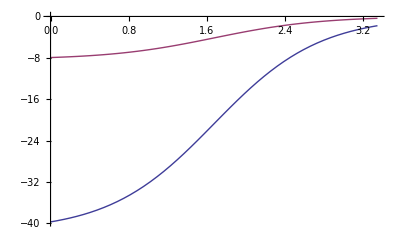

```mathematica
Plot[{Re[V[r]],Im[V[r]]},{r,0,2*R}]
```

## Solve the Schrödinger Equation

First I solve the Schrödinger equation for the radial wavefunction with an arbitrary constant for the initial condition for u'(0). My goal is to show that the resulting phase shift we get from this in independent of the choice of u'(0).

```mathematica
s[L_,k_,b_]:=NDSolve[{u''[r]+(k^2-2*m/(ℏc)^2*V[r]-L*(L+1)/r^2)*u[r]==0,u[(1000*k)^(-1)]==0,u'[(1000*k)^(-1)]==b},u,{r,(1000*k)^(-1),5*R}]
```

```mathematica
u[L_,k_,r_,b_]:=u[r]/.s[L,k,b][[1]]
```

```mathematica
β[L_,k_,b_]:=5*R/Evaluate[u[L,k,5*R,b]]*(D[u[L,k,r,b],r]/.r->(5*R))-1
tanδ[L_,k_,b_]:=N[(k*5*R*Derivative[0,1][SphericalBesselJ][L,k*5*R]-β[L,k,b]*SphericalBesselJ[L,k*5*R])/(k*5*R*Derivative[0,1][SphericalBesselY][L,k*5*R]-β[L,k,b]*SphericalBesselY[L,k*5*R])]
```

```mathematica
(*Plot[Re[tanδ[0,1,b]],{b,0.01,10}]*)
```

```mathematica
(*Plot[Im[tanδ[0,1,b]],{b,0.01,10}]*)
```

As we can see from this plot of tanδ vs. u'(0), the phase shift appears to be independent of our choice of u'(0) up to about 0.01% error.

## Reformulate tanδ for specific choice of u'(0)

These are the same equations as above, but now we have chosen u'(0)=8 (an arbitrary choice).

```mathematica
s[L_,k_]:=NDSolve[{u''[r]+(k^2-2*m/(ℏc)^2*V[r]-L*(L+1)/r^2)*u[r]==0,u[(1000*k)^(-1)]==0,u'[(1000*k)^(-1)]==8},u,{r,(1000*k)^(-1),5*R},MaxSteps->20000]
```

```mathematica
u[L_,k_,r_]:=u[r]/.s[L,k][[1]]
```

```mathematica
β[L_,k_]:=5*R/Evaluate[u[L,k,5*R]]*(D[u[L,k,r],r]/.r->(5*R))-1
tanδ[L_,k_]:=N[(k*5*R*Derivative[0,1][SphericalBesselJ][L,k*5*R]-β[L,k]*SphericalBesselJ[L,k*5*R])/(k*5*R*Derivative[0,1][SphericalBesselY][L,k*5*R]-β[L,k]*SphericalBesselY[L,k*5*R])]
```

```mathematica
Table[Abs[tanδ[L,5]]/Abs[tanδ[0,5]],{L,0,20}]
```

{1.,0.984182,0.948468,0.896954,0.830717,0.751538,0.662308,0.567258,0.471681,0.381013,0.299674,0.230279,0.173558,0.128787,0.0944055,0.0685564,0.049429,0.035445,0.0253118,0.018017,0.0127933}

For k=1, tanδ becomes negligible after about L=5.

Below is an automated limit calculator for the phase shift series. The tolerance for the maximum allowed relative magnitude of the last term in the series to the initial term in the series is an adjustable parameter, with a default value of 10^-4.

```mathematica
Lim[k_,tol_:10^-4]:=(err=1;L=0;While[err>tol,err=Abs[tanδ[L,k]]/Abs[tanδ[0,k]];L++];Return[L])
```

```mathematica
Liminterp=Interpolation[Parallelize[Table[{k,Lim[k]},{k,.1,10.1}]]];
```

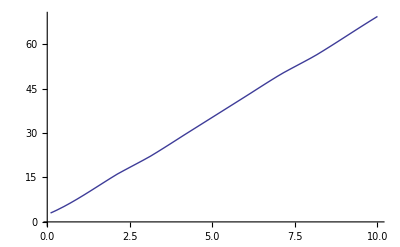

```mathematica
Plot[Liminterp[k],{k,.1,10}]
```

Plugging this phase shift into the equations for the scattering amplitude is:

```mathematica
f[k_,θ_]:=1/k*Sum[(2*L+1)*tanδ[L,k]/(1-I*tanδ[L,k])*LegendreP[L,Cos[θ]],{L,0,Ceiling[Liminterp[k]]}]
```

Here is a table of some values of dσ/dΩ as a function of θ.

```mathematica
Clear[dσdΩ]
```

```mathematica
dσdΩ[En_]:=Join[ParallelEvaluate[Table[{θ,Abs[f[Sqrt[En^2+2*m*En]/ℏc,θ]]^2},{θ,0,Pi-.1,.2}],1],ParallelEvaluate[Table[{θ,Abs[f[Sqrt[En^2+2*m*En]/ℏc,θ]]^2},{θ,0.1,Pi,.2}],1]]
```

```mathematica
Parallelize[Table[{θ,Abs[f[Sqrt[100^2+2*m*100]/ℏc,θ]]^2},{θ,0,Pi,.1}]]//Timing
```

```mathematica
{3.84541600000000016734702512621879577637`6.6055432422627955,{{0.,35.06500430461422},{0.1,31.648818618411052},{0.2,23.343901447403923},{0.30000000000000004,14.187596328277468},{0.4,7.177292824182437},{0.5,3.0471067125262143},{0.6000000000000001,1.0931872561344802},{0.7000000000000001,0.3401486429044697},{0.8,0.10435849936021514},{0.9000000000000001,0.04347049916265439},{1.,0.026993257699428924},{1.1,0.018225925171748456},{1.2000000000000002,0.011129144689218924},{1.3000000000000003,0.005955552659797482},{1.4000000000000001,0.002820080405584316},{1.5000000000000002,0.00121839957258847},{1.6,0.0005201819754724887},{1.7000000000000002,0.00025390406429325984},{1.8000000000000003,0.00015848725246290674},{1.9000000000000001,0.00011683199508102696},{2.,0.00008764944786274467},{2.1,0.00006294917764595689},{2.2,0.00004246130673475833},{2.3000000000000003,0.000026519677608875306},{2.4000000000000004,0.00001544278792309179},{2.5,8.375741305134987*^-6},{2.6,4.235895548565627*^-6},{2.7,2.1989975991434818*^-6},{2.8000000000000003,1.3051806198784557*^-6},{2.9000000000000004,9.842239036849583*^-7},{3.,1.0558286384169575*^-6},{3.1,1.2233863959845923*^-6}}}
```

{3.84542,{{0.,35.065},{0.1,31.6488},{0.2,23.3439},{0.3,14.1876},{0.4,7.17729},{0.5,3.04711},{0.6,1.09319},{0.7,0.340149},{0.8,0.104358},{0.9,0.0434705},{1.,0.0269933},{1.1,0.0182259},{1.2,0.0111291},{1.3,0.00595555},{1.4,0.00282008},{1.5,0.0012184},{1.6,0.000520182},{1.7,0.000253904},{1.8,0.000158487},{1.9,0.000116832},{2.,0.0000876494},{2.1,0.0000629492},{2.2,0.0000424613},{2.3,0.0000265197},{2.4,0.0000154428},{2.5,8.37574×10^-6},{2.6,4.2359×10^-6},{2.7,2.199×10^-6},{2.8,1.30518×10^-6},{2.9,9.84224×10^-7},{3.,1.05583×10^-6},{3.1,1.22339×10^-6}}}

```mathematica
interp1=Interpolation[%[[2]]]
```

InterpolatingFunction[{{0.,3.1}},<>]

Here is a log plot of that same information.

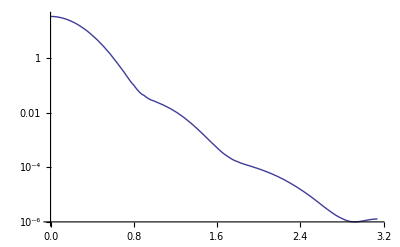

```mathematica
p1=LogPlot[interp1[θ],{θ,0,Pi}]
```

## Eikonal Approximation

These equations come straight out of Sakurai, equations 7.4.13 and 7.4.14 (page 394).

```mathematica
χ0exact[k_,b_]=-2*m/(k*(ℏc)^2)*NIntegrate[V[Sqrt[b^2+z^2]],{z,0,15}];
```

I had to have the iteration of the table below happen in integer steps because doing it in decimal steps was giving Mathematica problems somehow. I think it probably has something to do with differences in the way it handles integers and floats.

```mathematica
Parallelize[Table[{{k,b},χ0exact[k,b]},{b,0,15,.1},{k,Sqrt[100+2 m 10]/ℏc,Sqrt[1000^2+2 m 1000]/ℏc,.05}]]
```

{{{{0.696061,0.},4.87954+0.975908 ⅈ},{{0.746061,0.},4.55252+0.910504 ⅈ},{{0.796061,0.},4.26658+0.853316 ⅈ},{{0.846061,0.},4.01444+0.802887 ⅈ},{{0.896061,0.},3.79043+0.758086 ⅈ},{{0.946061,0.},3.5901+0.718021 ⅈ},{{0.996061,0.},3.40989+0.681978 ⅈ},{{1.04606,0.},3.2469+0.64938 ⅈ},{{1.09606,0.},3.09878+0.619757 ⅈ},{{1.14606,0.},2.96359+0.592718 ⅈ},{{1.19606,0.},2.8397+0.56794 ⅈ},{{1.24606,0.},2.72576+0.545151 ⅈ},{{1.29606,0.},2.6206+0.52412 ⅈ},{{1.34606,0.},2.52326+0.504651 ⅈ},{{1.39606,0.},2.43289+0.486577 ⅈ},{{1.44606,0.},2.34876+0.469753 ⅈ},{{1.49606,0.},2.27027+0.454053 ⅈ},{{1.54606,0.},2.19685+0.439369 ⅈ},{{1.59606,0.},2.12802+0.425605 ⅈ},{{1.64606,0.},2.06338+0.412677 ⅈ},{{1.69606,0.},2.00256+0.400511 ⅈ},{{1.74606,0.},1.94521+0.389042 ⅈ},{{1.79606,0.},1.89106+0.378212 ⅈ},{{1.84606,0.},1.83984+0.367968 ⅈ},{{1.89606,0.},1.79132+0.358264 ⅈ},{{1.94606,0.},1.7453+0.34906 ⅈ},{{1.99606,0.},1.70158+0.340316 ⅈ},{{2.04606,0.},1.66+0.332 ⅈ},{{2.09606,0.},1.6204+0.32408 ⅈ},{{2.14606,0.},1.58265+0.316529 ⅈ},{{2.19606,0.},1.54661+0.309323 ⅈ},{{2.24606,0.},1.51218+0.302437 ⅈ},{{2.29606,0.},1.47925+0.295851 ⅈ},{{2.34606,0.},1.44773+0.289545 ⅈ},{{2.39606,0.},1.41752+0.283503 ⅈ},{{2.44606,0.},1.38854+0.277708 ⅈ},{{2.49606,0.},1.36073+0.272145 ⅈ},{{2.54606,0.},1.334+0.266801 ⅈ},{{2.59606,0.},1.30831+0.261662 ⅈ},{{2.64606,0.},1.28359+0.256718 ⅈ},{{2.69606,0.},1.25978+0.251957 ⅈ},{{2.74606,0.},1.23685+0.247369 ⅈ},{{2.79606,0.},1.21473+0.242946 ⅈ},{{2.84606,0.},1.19339+0.238678 ⅈ},{{2.89606,0.},1.17278+0.234557 ⅈ},{{2.94606,0.},1.15288+0.230576 ⅈ},{{2.99606,0.},1.13364+0.226728 ⅈ},{{3.04606,0.},1.11503+0.223006 ⅈ},{{3.09606,0.},1.09703+0.219405 ⅈ},{{3.14606,0.},1.07959+0.215918 ⅈ},{{3.19606,0.},1.0627+0.21254 ⅈ},{{3.24606,0.},1.04633+0.209266 ⅈ},{{3.29606,0.},1.03046+0.206092 ⅈ},{{3.34606,0.},1.01506+0.203012 ⅈ},{{3.39606,0.},1.00012+0.200023 ⅈ},{{3.44606,0.},0.985605+0.197121 ⅈ},{{3.49606,0.},0.971509+0.194302 ⅈ},{{3.54606,0.},0.957811+0.191562 ⅈ},{{3.59606,0.},0.944494+0.188899 ⅈ},{{3.64606,0.},0.931541+0.186308 ⅈ},{{3.69606,0.},0.918939+0.183788 ⅈ},{{3.74606,0.},0.906674+0.181335 ⅈ},{{3.79606,0.},0.894732+0.178946 ⅈ},{{3.84606,0.},0.8831+0.17662 ⅈ},{{3.89606,0.},0.871767+0.174353 ⅈ},{{3.94606,0.},0.860721+0.172144 ⅈ},{{3.99606,0.},0.849951+0.16999 ⅈ},{{4.04606,0.},0.839448+0.16789 ⅈ},{{4.09606,0.},0.829201+0.16584 ⅈ},{{4.14606,0.},0.819201+0.16384 ⅈ},{{4.19606,0.},0.809439+0.161888 ⅈ},{{4.24606,0.},0.799908+0.159982 ⅈ},{{4.29606,0.},0.790598+0.15812 ⅈ},{{4.34606,0.},0.781502+0.1563 ⅈ},{{4.39606,0.},0.772614+0.154523 ⅈ},{{4.44606,0.},0.763925+0.152785 ⅈ},{{4.49606,0.},0.755429+0.151086 ⅈ},{{4.54606,0.},0.747121+0.149424 ⅈ},{{4.59606,0.},0.738993+0.147799 ⅈ},{{4.64606,0.},0.73104+0.146208 ⅈ},{{4.69606,0.},0.723256+0.144651 ⅈ},{{4.74606,0.},0.715637+0.143127 ⅈ},{{4.79606,0.},0.708176+0.141635 ⅈ},{{4.84606,0.},0.700869+0.140174 ⅈ},{{4.89606,0.},0.693712+0.138742 ⅈ},{{4.94606,0.},0.686699+0.13734 ⅈ},{{4.99606,0.},0.679827+0.135965 ⅈ},{{5.04606,0.},0.673091+0.134618 ⅈ},{{5.09606,0.},0.666487+0.133297 ⅈ},{{5.14606,0.},0.660011+0.132002 ⅈ},{{5.19606,0.},0.65366+0.130732 ⅈ},{{5.24606,0.},0.64743+0.129486 ⅈ},{{5.29606,0.},0.641317+0.128263 ⅈ},{{5.34606,0.},0.635319+0.127064 ⅈ},{{5.39606,0.},0.629433+0.125887 ⅈ},{{5.44606,0.},0.623654+0.124731 ⅈ},{{5.49606,0.},0.61798+0.123596 ⅈ},{{5.54606,0.},0.612409+0.122482 ⅈ},{{5.59606,0.},0.606937+0.121387 ⅈ},{{5.64606,0.},0.601562+0.120312 ⅈ},{{5.69606,0.},0.596282+0.119256 ⅈ},{{5.74606,0.},0.591093+0.118219 ⅈ},{{5.79606,0.},0.585994+0.117199 ⅈ},{{5.84606,0.},0.580982+0.116196 ⅈ},{{5.89606,0.},0.576055+0.115211 ⅈ},{{5.94606,0.},0.571211+0.114242 ⅈ},{{5.99606,0.},0.566448+0.11329 ⅈ},{{6.04606,0.},0.561763+0.112353 ⅈ},{{6.09606,0.},0.557156+0.111431 ⅈ},{{6.14606,0.},0.552623+0.110525 ⅈ},{{6.19606,0.},0.548164+0.109633 ⅈ},{{6.24606,0.},0.543776+0.108755 ⅈ},{{6.29606,0.},0.539457+0.107891 ⅈ},{{6.34606,0.},0.535207+0.107041 ⅈ},{{6.39606,0.},0.531023+0.106205 ⅈ},{{6.44606,0.},0.526904+0.105381 ⅈ},{{6.49606,0.},0.522849+0.10457 ⅈ},{{6.54606,0.},0.518855+0.103771 ⅈ},{{6.59606,0.},0.514922+0.102984 ⅈ},{{6.64606,0.},0.511048+0.10221 ⅈ},{{6.69606,0.},0.507232+0.101446 ⅈ},{{6.74606,0.},0.503472+0.100694 ⅈ},{{6.79606,0.},0.499768+0.0999537 ⅈ},{{6.84606,0.},0.496118+0.0992237 ⅈ},{{6.89606,0.},0.492521+0.0985042 ⅈ},{{6.94606,0.},0.488976+0.0977952 ⅈ},{{6.99606,0.},0.485481+0.0970962 ⅈ},{{7.04606,0.},0.482036+0.0964072 ⅈ},{{7.09606,0.},0.47864+0.0957279 ⅈ},{{7.14606,0.},0.475291+0.0950581 ⅈ},{{7.19606,0.},0.471988+0.0943976 ⅈ},{{7.24606,0.},0.468731+0.0937463 ⅈ},{{7.29606,0.},0.465519+0.0931038 ⅈ},{{7.34606,0.},0.462351+0.0924701 ⅈ},{{7.39606,0.},0.459225+0.091845 ⅈ},{{7.44606,0.},0.456141+0.0912283 ⅈ},{{7.49606,0.},0.453099+0.0906198 ⅈ},{{7.54606,0.},0.450097+0.0900193 ⅈ},{{7.59606,0.},0.447134+0.0894268 ⅈ},{{7.64606,0.},0.44421+0.088842 ⅈ},{{7.69606,0.},0.441324+0.0882648 ⅈ},{{7.74606,0.},0.438475+0.0876951 ⅈ},{{7.79606,0.},0.435663+0.0871326 ⅈ},{{7.84606,0.},0.432887+0.0865774 ⅈ},{{7.89606,0.},0.430146+0.0860291 ⅈ},{{7.94606,0.},0.427439+0.0854878 ⅈ},{{7.99606,0.},0.424766+0.0849532 ⅈ},{{8.04606,0.},0.422127+0.0844253 ⅈ},{{8.09606,0.},0.41952+0.0839039 ⅈ},{{8.14606,0.},0.416945+0.0833889 ⅈ},{{8.19606,0.},0.414401+0.0828802 ⅈ},{{8.24606,0.},0.411888+0.0823777 ⅈ},{{8.29606,0.},0.409406+0.0818812 ⅈ},{{8.34606,0.},0.406953+0.0813906 ⅈ},{{8.39606,0.},0.40453+0.0809059 ⅈ},{{8.44606,0.},0.402135+0.080427 ⅈ},{{8.49606,0.},0.399768+0.0799537 ⅈ},{{8.54606,0.},0.397429+0.0794859 ⅈ}},{{{0.696061,0.1},4.86688+0.973377 ⅈ},{{0.746061,0.1},4.54071+0.908142 ⅈ},{{0.796061,0.1},4.25551+0.851102 ⅈ},{{0.846061,0.1},4.00402+0.800804 ⅈ},{{0.896061,0.1},3.7806+0.75612 ⅈ},{{0.946061,0.1},3.58079+0.716158 ⅈ},{{0.996061,0.1},3.40104+0.680209 ⅈ},{{1.04606,0.1},3.23848+0.647696 ⅈ},{{1.09606,0.1},3.09075+0.618149 ⅈ},{{1.14606,0.1},2.9559+0.591181 ⅈ},{{1.19606,0.1},2.83234+0.566467 ⅈ},{{1.24606,0.1},2.71868+0.543737 ⅈ},{{1.29606,0.1},2.6138+0.52276 ⅈ},{{1.34606,0.1},2.51671+0.503342 ⅈ},{{1.39606,0.1},2.42657+0.485315 ⅈ},{{1.44606,0.1},2.34267+0.468534 ⅈ},{{1.49606,0.1},2.26438+0.452875 ⅈ},{{1.54606,0.1},2.19115+0.438229 ⅈ},{{1.59606,0.1},2.1225+0.424501 ⅈ},{{1.64606,0.1},2.05803+0.411606 ⅈ},{{1.69606,0.1},1.99736+0.399472 ⅈ},{{1.74606,0.1},1.94016+0.388033 ⅈ},{{1.79606,0.1},1.88615+0.377231 ⅈ},{{1.84606,0.1},1.83507+0.367013 ⅈ},{{1.89606,0.1},1.78668+0.357335 ⅈ},{{1.94606,0.1},1.74077+0.348154 ⅈ},{{1.99606,0.1},1.69717+0.339433 ⅈ},{{2.04606,0.1},1.65569+0.331138 ⅈ},{{2.09606,0.1},1.6162+0.323239 ⅈ},{{2.14606,0.1},1.57854+0.315708 ⅈ},{{2.19606,0.1},1.5426+0.30852 ⅈ},{{2.24606,0.1},1.50826+0.301652 ⅈ},{{2.29606,0.1},1.47542+0.295083 ⅈ},{{2.34606,0.1},1.44397+0.288794 ⅈ},{{2.39606,0.1},1.41384+0.282768 ⅈ},{{2.44606,0.1},1.38494+0.276988 ⅈ},{{2.49606,0.1},1.3572+0.271439 ⅈ},{{2.54606,0.1},1.33054+0.266109 ⅈ},{{2.59606,0.1},1.30492+0.260984 ⅈ},{{2.64606,0.1},1.28026+0.256052 ⅈ},{{2.69606,0.1},1.25652+0.251303 ⅈ},{{2.74606,0.1},1.23364+0.246728 ⅈ},{{2.79606,0.1},1.21158+0.242316 ⅈ},{{2.84606,0.1},1.19029+0.238059 ⅈ},{{2.89606,0.1},1.16974+0.233948 ⅈ},{{2.94606,0.1},1.14989+0.229978 ⅈ},{{2.99606,0.1},1.1307+0.22614 ⅈ},{{3.04606,0.1},1.11214+0.222428 ⅈ},{{3.09606,0.1},1.09418+0.218836 ⅈ},{{3.14606,0.1},1.07679+0.215358 ⅈ},{{3.19606,0.1},1.05994+0.211989 ⅈ},{{3.24606,0.1},1.04362+0.208723 ⅈ},{{3.29606,0.1},1.02779+0.205557 ⅈ},{{3.34606,0.1},1.01243+0.202486 ⅈ},{{3.39606,0.1},0.997522+0.199504 ⅈ},{{3.44606,0.1},0.983049+0.19661 ⅈ},{{3.49606,0.1},0.968989+0.193798 ⅈ},{{3.54606,0.1},0.955326+0.191065 ⅈ},{{3.59606,0.1},0.942043+0.188409 ⅈ},{{3.64606,0.1},0.929125+0.185825 ⅈ},{{3.69606,0.1},0.916556+0.183311 ⅈ},{{3.74606,0.1},0.904322+0.180864 ⅈ},{{3.79606,0.1},0.892411+0.178482 ⅈ},{{3.84606,0.1},0.880809+0.176162 ⅈ},{{3.89606,0.1},0.869505+0.173901 ⅈ},{{3.94606,0.1},0.858488+0.171698 ⅈ},{{3.99606,0.1},0.847746+0.169549 ⅈ},{{4.04606,0.1},0.83727+0.167454 ⅈ},{{4.09606,0.1},0.82705+0.16541 ⅈ},{{4.14606,0.1},0.817076+0.163415 ⅈ},{{4.19606,0.1},0.807339+0.161468 ⅈ},{{4.24606,0.1},0.797832+0.159566 ⅈ},{{4.29606,0.1},0.788547+0.157709 ⅈ},{{4.34606,0.1},0.779475+0.155895 ⅈ},{{4.39606,0.1},0.770609+0.154122 ⅈ},{{4.44606,0.1},0.761943+0.152389 ⅈ},{{4.49606,0.1},0.75347+0.150694 ⅈ},{{4.54606,0.1},0.745183+0.149037 ⅈ},{{4.59606,0.1},0.737076+0.147415 ⅈ},{{4.64606,0.1},0.729144+0.145829 ⅈ},{{4.69606,0.1},0.72138+0.144276 ⅈ},{{4.74606,0.1},0.71378+0.142756 ⅈ},{{4.79606,0.1},0.706339+0.141268 ⅈ},{{4.84606,0.1},0.699051+0.13981 ⅈ},{{4.89606,0.1},0.691912+0.138382 ⅈ},{{4.94606,0.1},0.684918+0.136984 ⅈ},{{4.99606,0.1},0.678063+0.135613 ⅈ},{{5.04606,0.1},0.671345+0.134269 ⅈ},{{5.09606,0.1},0.664758+0.132952 ⅈ},{{5.14606,0.1},0.658299+0.13166 ⅈ},{{5.19606,0.1},0.651964+0.130393 ⅈ},{{5.24606,0.1},0.64575+0.12915 ⅈ},{{5.29606,0.1},0.639654+0.127931 ⅈ},{{5.34606,0.1},0.633671+0.126734 ⅈ},{{5.39606,0.1},0.6278+0.12556 ⅈ},{{5.44606,0.1},0.622036+0.124407 ⅈ},{{5.49606,0.1},0.616377+0.123275 ⅈ},{{5.54606,0.1},0.61082+0.122164 ⅈ},{{5.59606,0.1},0.605362+0.121072 ⅈ},{{5.64606,0.1},0.600002+0.12 ⅈ},{{5.69606,0.1},0.594735+0.118947 ⅈ},{{5.74606,0.1},0.58956+0.117912 ⅈ},{{5.79606,0.1},0.584474+0.116895 ⅈ},{{5.84606,0.1},0.579475+0.115895 ⅈ},{{5.89606,0.1},0.574561+0.114912 ⅈ},{{5.94606,0.1},0.569729+0.113946 ⅈ},{{5.99606,0.1},0.564978+0.112996 ⅈ},{{6.04606,0.1},0.560306+0.112061 ⅈ},{{6.09606,0.1},0.555711+0.111142 ⅈ},{{6.14606,0.1},0.55119+0.110238 ⅈ},{{6.19606,0.1},0.546742+0.109348 ⅈ},{{6.24606,0.1},0.542365+0.108473 ⅈ},{{6.29606,0.1},0.538058+0.107612 ⅈ},{{6.34606,0.1},0.533819+0.106764 ⅈ},{{6.39606,0.1},0.529646+0.105929 ⅈ},{{6.44606,0.1},0.525537+0.105107 ⅈ},{{6.49606,0.1},0.521492+0.104298 ⅈ},{{6.54606,0.1},0.517509+0.103502 ⅈ},{{6.59606,0.1},0.513586+0.102717 ⅈ},{{6.64606,0.1},0.509722+0.101944 ⅈ},{{6.69606,0.1},0.505916+0.101183 ⅈ},{{6.74606,0.1},0.502166+0.100433 ⅈ},{{6.79606,0.1},0.498472+0.0996944 ⅈ},{{6.84606,0.1},0.494831+0.0989663 ⅈ},{{6.89606,0.1},0.491244+0.0982487 ⅈ},{{6.94606,0.1},0.487707+0.0975415 ⅈ},{{6.99606,0.1},0.484222+0.0968444 ⅈ},{{7.04606,0.1},0.480786+0.0961571 ⅈ},{{7.09606,0.1},0.477398+0.0954796 ⅈ},{{7.14606,0.1},0.474058+0.0948115 ⅈ},{{7.19606,0.1},0.470764+0.0941528 ⅈ},{{7.24606,0.1},0.467515+0.0935031 ⅈ},{{7.29606,0.1},0.464312+0.0928623 ⅈ},{{7.34606,0.1},0.461151+0.0922303 ⅈ},{{7.39606,0.1},0.458034+0.0916067 ⅈ},{{7.44606,0.1},0.454958+0.0909916 ⅈ},{{7.49606,0.1},0.451923+0.0903847 ⅈ},{{7.54606,0.1},0.448929+0.0897858 ⅈ},{{7.59606,0.1},0.445974+0.0891948 ⅈ},{{7.64606,0.1},0.443058+0.0886115 ⅈ},{{7.69606,0.1},0.440179+0.0880358 ⅈ},{{7.74606,0.1},0.437338+0.0874676 ⅈ},{{7.79606,0.1},0.434533+0.0869066 ⅈ},{{7.84606,0.1},0.431764+0.0863528 ⅈ},{{7.89606,0.1},0.42903+0.085806 ⅈ},{{7.94606,0.1},0.42633+0.085266 ⅈ},{{7.99606,0.1},0.423664+0.0847329 ⅈ},{{8.04606,0.1},0.421032+0.0842063 ⅈ},{{8.09606,0.1},0.418431+0.0836863 ⅈ},{{8.14606,0.1},0.415863+0.0831726 ⅈ},{{8.19606,0.1},0.413326+0.0826652 ⅈ},{{8.24606,0.1},0.41082+0.082164 ⅈ},{{8.29606,0.1},0.408344+0.0816688 ⅈ},{{8.34606,0.1},0.405897+0.0811795 ⅈ},{{8.39606,0.1},0.40348+0.0806961 ⅈ},{{8.44606,0.1},0.401092+0.0802183 ⅈ},{{8.49606,0.1},0.398731+0.0797463 ⅈ},{{8.54606,0.1},0.396398+0.0792797 ⅈ}},{{{0.696061,0.2},4.83186+0.966371 ⅈ},{{0.746061,0.2},4.50803+0.901606 ⅈ},{{0.796061,0.2},4.22489+0.844977 ⅈ},{{0.846061,0.2},3.97521+0.795041 ⅈ},{{0.896061,0.2},3.75339+0.750678 ⅈ},{{0.946061,0.2},3.55502+0.711004 ⅈ},{{0.996061,0.2},3.37657+0.675313 ⅈ},{{1.04606,0.2},3.21517+0.643034 ⅈ},{{1.09606,0.2},3.0685+0.613701 ⅈ},{{1.14606,0.2},2.93463+0.586926 ⅈ},{{1.19606,0.2},2.81195+0.56239 ⅈ},{{1.24606,0.2},2.69912+0.539824 ⅈ},{{1.29606,0.2},2.59499+0.518998 ⅈ},{{1.34606,0.2},2.4986+0.49972 ⅈ},{{1.39606,0.2},2.40911+0.481822 ⅈ},{{1.44606,0.2},2.32581+0.465162 ⅈ},{{1.49606,0.2},2.24808+0.449616 ⅈ},{{1.54606,0.2},2.17538+0.435075 ⅈ},{{1.59606,0.2},2.10723+0.421446 ⅈ},{{1.64606,0.2},2.04322+0.408644 ⅈ},{{1.69606,0.2},1.98299+0.396597 ⅈ},{{1.74606,0.2},1.9262+0.38524 ⅈ},{{1.79606,0.2},1.87258+0.374516 ⅈ},{{1.84606,0.2},1.82186+0.364372 ⅈ},{{1.89606,0.2},1.77382+0.354763 ⅈ},{{1.94606,0.2},1.72824+0.345649 ⅈ},{{1.99606,0.2},1.68495+0.33699 ⅈ},{{2.04606,0.2},1.64378+0.328755 ⅈ},{{2.09606,0.2},1.60456+0.320913 ⅈ},{{2.14606,0.2},1.56718+0.313436 ⅈ},{{2.19606,0.2},1.5315+0.3063 ⅈ},{{2.24606,0.2},1.49741+0.299481 ⅈ},{{2.29606,0.2},1.4648+0.29296 ⅈ},{{2.34606,0.2},1.43358+0.286716 ⅈ},{{2.39606,0.2},1.40366+0.280733 ⅈ},{{2.44606,0.2},1.37497+0.274994 ⅈ},{{2.49606,0.2},1.34743+0.269486 ⅈ},{{2.54606,0.2},1.32097+0.264194 ⅈ},{{2.59606,0.2},1.29553+0.259105 ⅈ},{{2.64606,0.2},1.27105+0.254209 ⅈ},{{2.69606,0.2},1.24747+0.249495 ⅈ},{{2.74606,0.2},1.22476+0.244952 ⅈ},{{2.79606,0.2},1.20286+0.240572 ⅈ},{{2.84606,0.2},1.18173+0.236345 ⅈ},{{2.89606,0.2},1.16132+0.232265 ⅈ},{{2.94606,0.2},1.14161+0.228323 ⅈ},{{2.99606,0.2},1.12256+0.224512 ⅈ},{{3.04606,0.2},1.10414+0.220827 ⅈ},{{3.09606,0.2},1.0863+0.217261 ⅈ},{{3.14606,0.2},1.06904+0.213808 ⅈ},{{3.19606,0.2},1.05232+0.210463 ⅈ},{{3.24606,0.2},1.03611+0.207221 ⅈ},{{3.29606,0.2},1.02039+0.204078 ⅈ},{{3.34606,0.2},1.00514+0.201028 ⅈ},{{3.39606,0.2},0.990343+0.198069 ⅈ},{{3.44606,0.2},0.975974+0.195195 ⅈ},{{3.49606,0.2},0.962016+0.192403 ⅈ},{{3.54606,0.2},0.948451+0.18969 ⅈ},{{3.59606,0.2},0.935264+0.187053 ⅈ},{{3.64606,0.2},0.922438+0.184488 ⅈ},{{3.69606,0.2},0.909959+0.181992 ⅈ},{{3.74606,0.2},0.897814+0.179563 ⅈ},{{3.79606,0.2},0.885988+0.177198 ⅈ},{{3.84606,0.2},0.87447+0.174894 ⅈ},{{3.89606,0.2},0.863248+0.17265 ⅈ},{{3.94606,0.2},0.852309+0.170462 ⅈ},{{3.99606,0.2},0.841645+0.168329 ⅈ},{{4.04606,0.2},0.831244+0.166249 ⅈ},{{4.09606,0.2},0.821097+0.164219 ⅈ},{{4.14606,0.2},0.811195+0.162239 ⅈ},{{4.19606,0.2},0.801529+0.160306 ⅈ},{{4.24606,0.2},0.792091+0.158418 ⅈ},{{4.29606,0.2},0.782872+0.156574 ⅈ},{{4.34606,0.2},0.773865+0.154773 ⅈ},{{4.39606,0.2},0.765063+0.153013 ⅈ},{{4.44606,0.2},0.756459+0.151292 ⅈ},{{4.49606,0.2},0.748047+0.149609 ⅈ},{{4.54606,0.2},0.73982+0.147964 ⅈ},{{4.59606,0.2},0.731771+0.146354 ⅈ},{{4.64606,0.2},0.723896+0.144779 ⅈ},{{4.69606,0.2},0.716189+0.143238 ⅈ},{{4.74606,0.2},0.708643+0.141729 ⅈ},{{4.79606,0.2},0.701256+0.140251 ⅈ},{{4.84606,0.2},0.69402+0.138804 ⅈ},{{4.89606,0.2},0.686933+0.137387 ⅈ},{{4.94606,0.2},0.679989+0.135998 ⅈ},{{4.99606,0.2},0.673183+0.134637 ⅈ},{{5.04606,0.2},0.666513+0.133303 ⅈ},{{5.09606,0.2},0.659973+0.131995 ⅈ},{{5.14606,0.2},0.653561+0.130712 ⅈ},{{5.19606,0.2},0.647272+0.129454 ⅈ},{{5.24606,0.2},0.641103+0.128221 ⅈ},{{5.29606,0.2},0.63505+0.12701 ⅈ},{{5.34606,0.2},0.629111+0.125822 ⅈ},{{5.39606,0.2},0.623281+0.124656 ⅈ},{{5.44606,0.2},0.617559+0.123512 ⅈ},{{5.49606,0.2},0.611941+0.122388 ⅈ},{{5.54606,0.2},0.606424+0.121285 ⅈ},{{5.59606,0.2},0.601006+0.120201 ⅈ},{{5.64606,0.2},0.595683+0.119137 ⅈ},{{5.69606,0.2},0.590455+0.118091 ⅈ},{{5.74606,0.2},0.585317+0.117063 ⅈ},{{5.79606,0.2},0.580267+0.116053 ⅈ},{{5.84606,0.2},0.575304+0.115061 ⅈ},{{5.89606,0.2},0.570426+0.114085 ⅈ},{{5.94606,0.2},0.565629+0.113126 ⅈ},{{5.99606,0.2},0.560912+0.112182 ⅈ},{{6.04606,0.2},0.556274+0.111255 ⅈ},{{6.09606,0.2},0.551711+0.110342 ⅈ},{{6.14606,0.2},0.547223+0.109445 ⅈ},{{6.19606,0.2},0.542807+0.108561 ⅈ},{{6.24606,0.2},0.538462+0.107692 ⅈ},{{6.29606,0.2},0.534186+0.106837 ⅈ},{{6.34606,0.2},0.529977+0.105995 ⅈ},{{6.39606,0.2},0.525834+0.105167 ⅈ},{{6.44606,0.2},0.521755+0.104351 ⅈ},{{6.49606,0.2},0.517739+0.103548 ⅈ},{{6.54606,0.2},0.513785+0.102757 ⅈ},{{6.59606,0.2},0.50989+0.101978 ⅈ},{{6.64606,0.2},0.506054+0.101211 ⅈ},{{6.69606,0.2},0.502275+0.100455 ⅈ},{{6.74606,0.2},0.498552+0.0997105 ⅈ},{{6.79606,0.2},0.494884+0.0989769 ⅈ},{{6.84606,0.2},0.49127+0.098254 ⅈ},{{6.89606,0.2},0.487708+0.0975416 ⅈ},{{6.94606,0.2},0.484197+0.0968395 ⅈ},{{6.99606,0.2},0.480737+0.0961474 ⅈ},{{7.04606,0.2},0.477326+0.0954651 ⅈ},{{7.09606,0.2},0.473962+0.0947924 ⅈ},{{7.14606,0.2},0.470646+0.0941292 ⅈ},{{7.19606,0.2},0.467376+0.0934752 ⅈ},{{7.24606,0.2},0.464151+0.0928302 ⅈ},{{7.29606,0.2},0.46097+0.092194 ⅈ},{{7.34606,0.2},0.457832+0.0915665 ⅈ},{{7.39606,0.2},0.454737+0.0909475 ⅈ},{{7.44606,0.2},0.451684+0.0903368 ⅈ},{{7.49606,0.2},0.448671+0.0897342 ⅈ},{{7.54606,0.2},0.445698+0.0891396 ⅈ},{{7.59606,0.2},0.442764+0.0885529 ⅈ},{{7.64606,0.2},0.439869+0.0879738 ⅈ},{{7.69606,0.2},0.437011+0.0874022 ⅈ},{{7.74606,0.2},0.43419+0.0868381 ⅈ},{{7.79606,0.2},0.431406+0.0862811 ⅈ},{{7.84606,0.2},0.428656+0.0857313 ⅈ},{{7.89606,0.2},0.425942+0.0851884 ⅈ},{{7.94606,0.2},0.423262+0.0846524 ⅈ},{{7.99606,0.2},0.420615+0.084123 ⅈ},{{8.04606,0.2},0.418001+0.0836003 ⅈ},{{8.09606,0.2},0.41542+0.083084 ⅈ},{{8.14606,0.2},0.41287+0.082574 ⅈ},{{8.19606,0.2},0.410351+0.0820703 ⅈ},{{8.24606,0.2},0.407863+0.0815726 ⅈ},{{8.29606,0.2},0.405405+0.081081 ⅈ},{{8.34606,0.2},0.402976+0.0805953 ⅈ},{{8.39606,0.2},0.400577+0.0801153 ⅈ},{{8.44606,0.2},0.398205+0.079641 ⅈ},{{8.49606,0.2},0.395862+0.0791723 ⅈ},{{8.54606,0.2},0.393546+0.0787091 ⅈ}},{{{0.696061,0.3},4.77599+0.955198 ⅈ},{{0.746061,0.3},4.45591+0.891182 ⅈ},{{0.796061,0.3},4.17604+0.835207 ⅈ},{{0.846061,0.3},3.92924+0.785849 ⅈ},{{0.896061,0.3},3.70999+0.741999 ⅈ},{{0.946061,0.3},3.51392+0.702783 ⅈ},{{0.996061,0.3},3.33753+0.667505 ⅈ},{{1.04606,0.3},3.178+0.6356 ⅈ},{{1.09606,0.3},3.03302+0.606605 ⅈ},{{1.14606,0.3},2.9007+0.58014 ⅈ},{{1.19606,0.3},2.77944+0.555888 ⅈ},{{1.24606,0.3},2.66791+0.533582 ⅈ},{{1.29606,0.3},2.56499+0.512997 ⅈ},{{1.34606,0.3},2.46971+0.493942 ⅈ},{{1.39606,0.3},2.38126+0.476251 ⅈ},{{1.44606,0.3},2.29892+0.459784 ⅈ},{{1.49606,0.3},2.22209+0.444418 ⅈ},{{1.54606,0.3},2.15023+0.430045 ⅈ},{{1.59606,0.3},2.08286+0.416573 ⅈ},{{1.64606,0.3},2.0196+0.403919 ⅈ},{{1.69606,0.3},1.96006+0.392012 ⅈ},{{1.74606,0.3},1.90393+0.380786 ⅈ},{{1.79606,0.3},1.85093+0.370186 ⅈ},{{1.84606,0.3},1.8008+0.360159 ⅈ},{{1.89606,0.3},1.75331+0.350662 ⅈ},{{1.94606,0.3},1.70826+0.341652 ⅈ},{{1.99606,0.3},1.66547+0.333094 ⅈ},{{2.04606,0.3},1.62477+0.324954 ⅈ},{{2.09606,0.3},1.58601+0.317203 ⅈ},{{2.14606,0.3},1.54906+0.309812 ⅈ},{{2.19606,0.3},1.51379+0.302758 ⅈ},{{2.24606,0.3},1.48009+0.296019 ⅈ},{{2.29606,0.3},1.44786+0.289572 ⅈ},{{2.34606,0.3},1.417+0.283401 ⅈ},{{2.39606,0.3},1.38744+0.277487 ⅈ},{{2.44606,0.3},1.35907+0.271815 ⅈ},{{2.49606,0.3},1.33185+0.26637 ⅈ},{{2.54606,0.3},1.30569+0.261139 ⅈ},{{2.59606,0.3},1.28055+0.256109 ⅈ},{{2.64606,0.3},1.25635+0.25127 ⅈ},{{2.69606,0.3},1.23305+0.24661 ⅈ},{{2.74606,0.3},1.2106+0.24212 ⅈ},{{2.79606,0.3},1.18895+0.23779 ⅈ},{{2.84606,0.3},1.16806+0.233613 ⅈ},{{2.89606,0.3},1.1479+0.229579 ⅈ},{{2.94606,0.3},1.12841+0.225683 ⅈ},{{2.99606,0.3},1.10958+0.221917 ⅈ},{{3.04606,0.3},1.09137+0.218274 ⅈ},{{3.09606,0.3},1.07374+0.214749 ⅈ},{{3.14606,0.3},1.05668+0.211336 ⅈ},{{3.19606,0.3},1.04015+0.20803 ⅈ},{{3.24606,0.3},1.02413+0.204825 ⅈ},{{3.29606,0.3},1.00859+0.201718 ⅈ},{{3.34606,0.3},0.99352+0.198704 ⅈ},{{3.39606,0.3},0.978893+0.195779 ⅈ},{{3.44606,0.3},0.964689+0.192938 ⅈ},{{3.49606,0.3},0.950893+0.190179 ⅈ},{{3.54606,0.3},0.937485+0.187497 ⅈ},{{3.59606,0.3},0.92445+0.18489 ⅈ},{{3.64606,0.3},0.911773+0.182355 ⅈ},{{3.69606,0.3},0.899438+0.179888 ⅈ},{{3.74606,0.3},0.887433+0.177487 ⅈ},{{3.79606,0.3},0.875744+0.175149 ⅈ},{{3.84606,0.3},0.864359+0.172872 ⅈ},{{3.89606,0.3},0.853267+0.170653 ⅈ},{{3.94606,0.3},0.842455+0.168491 ⅈ},{{3.99606,0.3},0.831914+0.166383 ⅈ},{{4.04606,0.3},0.821633+0.164327 ⅈ},{{4.09606,0.3},0.811604+0.162321 ⅈ},{{4.14606,0.3},0.801816+0.160363 ⅈ},{{4.19606,0.3},0.792262+0.158452 ⅈ},{{4.24606,0.3},0.782932+0.156586 ⅈ},{{4.29606,0.3},0.77382+0.154764 ⅈ},{{4.34606,0.3},0.764918+0.152984 ⅈ},{{4.39606,0.3},0.756218+0.151244 ⅈ},{{4.44606,0.3},0.747713+0.149543 ⅈ},{{4.49606,0.3},0.739398+0.14788 ⅈ},{{4.54606,0.3},0.731266+0.146253 ⅈ},{{4.59606,0.3},0.72331+0.144662 ⅈ},{{4.64606,0.3},0.715526+0.143105 ⅈ},{{4.69606,0.3},0.707908+0.141582 ⅈ},{{4.74606,0.3},0.70045+0.14009 ⅈ},{{4.79606,0.3},0.693148+0.13863 ⅈ},{{4.84606,0.3},0.685996+0.137199 ⅈ},{{4.89606,0.3},0.67899+0.135798 ⅈ},{{4.94606,0.3},0.672127+0.134425 ⅈ},{{4.99606,0.3},0.6654+0.13308 ⅈ},{{5.04606,0.3},0.658807+0.131761 ⅈ},{{5.09606,0.3},0.652343+0.130469 ⅈ},{{5.14606,0.3},0.646005+0.129201 ⅈ},{{5.19606,0.3},0.639788+0.127958 ⅈ},{{5.24606,0.3},0.63369+0.126738 ⅈ},{{5.29606,0.3},0.627708+0.125542 ⅈ},{{5.34606,0.3},0.621837+0.124367 ⅈ},{{5.39606,0.3},0.616075+0.123215 ⅈ},{{5.44606,0.3},0.610419+0.122084 ⅈ},{{5.49606,0.3},0.604866+0.120973 ⅈ},{{5.54606,0.3},0.599413+0.119883 ⅈ},{{5.59606,0.3},0.594057+0.118811 ⅈ},{{5.64606,0.3},0.588796+0.117759 ⅈ},{{5.69606,0.3},0.583628+0.116726 ⅈ},{{5.74606,0.3},0.578549+0.11571 ⅈ},{{5.79606,0.3},0.573558+0.114712 ⅈ},{{5.84606,0.3},0.568653+0.113731 ⅈ},{{5.89606,0.3},0.56383+0.112766 ⅈ},{{5.94606,0.3},0.559089+0.111818 ⅈ},{{5.99606,0.3},0.554427+0.110885 ⅈ},{{6.04606,0.3},0.549842+0.109968 ⅈ},{{6.09606,0.3},0.545332+0.109066 ⅈ},{{6.14606,0.3},0.540896+0.108179 ⅈ},{{6.19606,0.3},0.536531+0.107306 ⅈ},{{6.24606,0.3},0.532236+0.106447 ⅈ},{{6.29606,0.3},0.528009+0.105602 ⅈ},{{6.34606,0.3},0.523849+0.10477 ⅈ},{{6.39606,0.3},0.519754+0.103951 ⅈ},{{6.44606,0.3},0.515722+0.103144 ⅈ},{{6.49606,0.3},0.511753+0.102351 ⅈ},{{6.54606,0.3},0.507844+0.101569 ⅈ},{{6.59606,0.3},0.503995+0.100799 ⅈ},{{6.64606,0.3},0.500203+0.100041 ⅈ},{{6.69606,0.3},0.496468+0.0992936 ⅈ},{{6.74606,0.3},0.492788+0.0985576 ⅈ},{{6.79606,0.3},0.489163+0.0978325 ⅈ},{{6.84606,0.3},0.48559+0.097118 ⅈ},{{6.89606,0.3},0.482069+0.0964138 ⅈ},{{6.94606,0.3},0.478599+0.0957198 ⅈ},{{6.99606,0.3},0.475179+0.0950357 ⅈ},{{7.04606,0.3},0.471807+0.0943613 ⅈ},{{7.09606,0.3},0.468482+0.0936965 ⅈ},{{7.14606,0.3},0.465204+0.0930409 ⅈ},{{7.19606,0.3},0.461972+0.0923944 ⅈ},{{7.24606,0.3},0.458784+0.0917568 ⅈ},{{7.29606,0.3},0.45564+0.091128 ⅈ},{{7.34606,0.3},0.452539+0.0905078 ⅈ},{{7.39606,0.3},0.44948+0.0898959 ⅈ},{{7.44606,0.3},0.446461+0.0892923 ⅈ},{{7.49606,0.3},0.443483+0.0886967 ⅈ},{{7.54606,0.3},0.440545+0.088109 ⅈ},{{7.59606,0.3},0.437645+0.087529 ⅈ},{{7.64606,0.3},0.434783+0.0869566 ⅈ},{{7.69606,0.3},0.431958+0.0863917 ⅈ},{{7.74606,0.3},0.42917+0.085834 ⅈ},{{7.79606,0.3},0.426418+0.0852835 ⅈ},{{7.84606,0.3},0.4237+0.0847401 ⅈ},{{7.89606,0.3},0.421017+0.0842035 ⅈ},{{7.94606,0.3},0.418368+0.0836736 ⅈ},{{7.99606,0.3},0.415752+0.0831504 ⅈ},{{8.04606,0.3},0.413168+0.0826337 ⅈ},{{8.09606,0.3},0.410617+0.0821234 ⅈ},{{8.14606,0.3},0.408096+0.0816193 ⅈ},{{8.19606,0.3},0.405607+0.0811214 ⅈ},{{8.24606,0.3},0.403147+0.0806295 ⅈ},{{8.29606,0.3},0.400718+0.0801435 ⅈ},{{8.34606,0.3},0.398317+0.0796634 ⅈ},{{8.39606,0.3},0.395945+0.079189 ⅈ},{{8.44606,0.3},0.393601+0.0787202 ⅈ},{{8.49606,0.3},0.391285+0.0782569 ⅈ},{{8.54606,0.3},0.388995+0.0777991 ⅈ}},{{{0.696061,0.4},4.7+0.939999 ⅈ},{{0.746061,0.4},4.38501+0.877002 ⅈ},{{0.796061,0.4},4.10959+0.821918 ⅈ},{{0.846061,0.4},3.86672+0.773344 ⅈ},{{0.896061,0.4},3.65096+0.730192 ⅈ},{{0.946061,0.4},3.458+0.691601 ⅈ},{{0.996061,0.4},3.28442+0.656884 ⅈ},{{1.04606,0.4},3.12743+0.625486 ⅈ},{{1.09606,0.4},2.98476+0.596953 ⅈ},{{1.14606,0.4},2.85454+0.570909 ⅈ},{{1.19606,0.4},2.73521+0.547043 ⅈ},{{1.24606,0.4},2.62546+0.525092 ⅈ},{{1.29606,0.4},2.52417+0.504835 ⅈ},{{1.34606,0.4},2.43041+0.486082 ⅈ},{{1.39606,0.4},2.34337+0.468673 ⅈ},{{1.44606,0.4},2.26234+0.452468 ⅈ},{{1.49606,0.4},2.18673+0.437346 ⅈ},{{1.54606,0.4},2.11601+0.423202 ⅈ},{{1.59606,0.4},2.04972+0.409945 ⅈ},{{1.64606,0.4},1.98746+0.397492 ⅈ},{{1.69606,0.4},1.92887+0.385774 ⅈ},{{1.74606,0.4},1.87364+0.374727 ⅈ},{{1.79606,0.4},1.82148+0.364295 ⅈ},{{1.84606,0.4},1.77214+0.354428 ⅈ},{{1.89606,0.4},1.72541+0.345082 ⅈ},{{1.94606,0.4},1.68108+0.336216 ⅈ},{{1.99606,0.4},1.63897+0.327794 ⅈ},{{2.04606,0.4},1.59892+0.319783 ⅈ},{{2.09606,0.4},1.56078+0.312155 ⅈ},{{2.14606,0.4},1.52441+0.304882 ⅈ},{{2.19606,0.4},1.4897+0.297941 ⅈ},{{2.24606,0.4},1.45654+0.291308 ⅈ},{{2.29606,0.4},1.42482+0.284965 ⅈ},{{2.34606,0.4},1.39446+0.278891 ⅈ},{{2.39606,0.4},1.36536+0.273072 ⅈ},{{2.44606,0.4},1.33745+0.26749 ⅈ},{{2.49606,0.4},1.31066+0.262132 ⅈ},{{2.54606,0.4},1.28492+0.256984 ⅈ},{{2.59606,0.4},1.26017+0.252034 ⅈ},{{2.64606,0.4},1.23636+0.247272 ⅈ},{{2.69606,0.4},1.21343+0.242686 ⅈ},{{2.74606,0.4},1.19134+0.238267 ⅈ},{{2.79606,0.4},1.17003+0.234006 ⅈ},{{2.84606,0.4},1.14948+0.229895 ⅈ},{{2.89606,0.4},1.12963+0.225926 ⅈ},{{2.94606,0.4},1.11046+0.222092 ⅈ},{{2.99606,0.4},1.09193+0.218386 ⅈ},{{3.04606,0.4},1.074+0.214801 ⅈ},{{3.09606,0.4},1.05666+0.211332 ⅈ},{{3.14606,0.4},1.03987+0.207973 ⅈ},{{3.19606,0.4},1.0236+0.20472 ⅈ},{{3.24606,0.4},1.00783+0.201566 ⅈ},{{3.29606,0.4},0.992543+0.198509 ⅈ},{{3.34606,0.4},0.977711+0.195542 ⅈ},{{3.39606,0.4},0.963317+0.192663 ⅈ},{{3.44606,0.4},0.94934+0.189868 ⅈ},{{3.49606,0.4},0.935762+0.187152 ⅈ},{{3.54606,0.4},0.922568+0.184514 ⅈ},{{3.59606,0.4},0.90974+0.181948 ⅈ},{{3.64606,0.4},0.897265+0.179453 ⅈ},{{3.69606,0.4},0.885127+0.177025 ⅈ},{{3.74606,0.4},0.873312+0.174662 ⅈ},{{3.79606,0.4},0.86181+0.172362 ⅈ},{{3.84606,0.4},0.850606+0.170121 ⅈ},{{3.89606,0.4},0.83969+0.167938 ⅈ},{{3.94606,0.4},0.82905+0.16581 ⅈ},{{3.99606,0.4},0.818677+0.163735 ⅈ},{{4.04606,0.4},0.80856+0.161712 ⅈ},{{4.09606,0.4},0.79869+0.159738 ⅈ},{{4.14606,0.4},0.789058+0.157812 ⅈ},{{4.19606,0.4},0.779655+0.155931 ⅈ},{{4.24606,0.4},0.770475+0.154095 ⅈ},{{4.29606,0.4},0.761507+0.152301 ⅈ},{{4.34606,0.4},0.752746+0.150549 ⅈ},{{4.39606,0.4},0.744185+0.148837 ⅈ},{{4.44606,0.4},0.735816+0.147163 ⅈ},{{4.49606,0.4},0.727633+0.145527 ⅈ},{{4.54606,0.4},0.71963+0.143926 ⅈ},{{4.59606,0.4},0.711801+0.14236 ⅈ},{{4.64606,0.4},0.704141+0.140828 ⅈ},{{4.69606,0.4},0.696644+0.139329 ⅈ},{{4.74606,0.4},0.689305+0.137861 ⅈ},{{4.79606,0.4},0.682118+0.136424 ⅈ},{{4.84606,0.4},0.675081+0.135016 ⅈ},{{4.89606,0.4},0.668186+0.133637 ⅈ},{{4.94606,0.4},0.661432+0.132286 ⅈ},{{4.99606,0.4},0.654812+0.130962 ⅈ},{{5.04606,0.4},0.648324+0.129665 ⅈ},{{5.09606,0.4},0.641963+0.128393 ⅈ},{{5.14606,0.4},0.635725+0.127145 ⅈ},{{5.19606,0.4},0.629608+0.125922 ⅈ},{{5.24606,0.4},0.623607+0.124721 ⅈ},{{5.29606,0.4},0.61772+0.123544 ⅈ},{{5.34606,0.4},0.611942+0.122388 ⅈ},{{5.39606,0.4},0.606272+0.121254 ⅈ},{{5.44606,0.4},0.600706+0.120141 ⅈ},{{5.49606,0.4},0.595241+0.119048 ⅈ},{{5.54606,0.4},0.589875+0.117975 ⅈ},{{5.59606,0.4},0.584604+0.116921 ⅈ},{{5.64606,0.4},0.579427+0.115885 ⅈ},{{5.69606,0.4},0.574341+0.114868 ⅈ},{{5.74606,0.4},0.569343+0.113869 ⅈ},{{5.79606,0.4},0.564432+0.112886 ⅈ},{{5.84606,0.4},0.559604+0.111921 ⅈ},{{5.89606,0.4},0.554859+0.110972 ⅈ},{{5.94606,0.4},0.550193+0.110039 ⅈ},{{5.99606,0.4},0.545605+0.109121 ⅈ},{{6.04606,0.4},0.541093+0.108219 ⅈ},{{6.09606,0.4},0.536655+0.107331 ⅈ},{{6.14606,0.4},0.532289+0.106458 ⅈ},{{6.19606,0.4},0.527994+0.105599 ⅈ},{{6.24606,0.4},0.523767+0.104753 ⅈ},{{6.29606,0.4},0.519608+0.103922 ⅈ},{{6.34606,0.4},0.515514+0.103103 ⅈ},{{6.39606,0.4},0.511484+0.102297 ⅈ},{{6.44606,0.4},0.507516+0.101503 ⅈ},{{6.49606,0.4},0.50361+0.100722 ⅈ},{{6.54606,0.4},0.499763+0.0999527 ⅈ},{{6.59606,0.4},0.495975+0.099195 ⅈ},{{6.64606,0.4},0.492244+0.0984487 ⅈ},{{6.69606,0.4},0.488568+0.0977136 ⅈ},{{6.74606,0.4},0.484947+0.0969894 ⅈ},{{6.79606,0.4},0.481379+0.0962758 ⅈ},{{6.84606,0.4},0.477863+0.0955727 ⅈ},{{6.89606,0.4},0.474399+0.0948797 ⅈ},{{6.94606,0.4},0.470984+0.0941967 ⅈ},{{6.99606,0.4},0.467618+0.0935235 ⅈ},{{7.04606,0.4},0.464299+0.0928599 ⅈ},{{7.09606,0.4},0.461028+0.0922056 ⅈ},{{7.14606,0.4},0.457802+0.0915604 ⅈ},{{7.19606,0.4},0.454621+0.0909242 ⅈ},{{7.24606,0.4},0.451484+0.0902968 ⅈ},{{7.29606,0.4},0.44839+0.089678 ⅈ},{{7.34606,0.4},0.445338+0.0890676 ⅈ},{{7.39606,0.4},0.442328+0.0884655 ⅈ},{{7.44606,0.4},0.439357+0.0878715 ⅈ},{{7.49606,0.4},0.436427+0.0872854 ⅈ},{{7.54606,0.4},0.433535+0.086707 ⅈ},{{7.59606,0.4},0.430681+0.0861363 ⅈ},{{7.64606,0.4},0.427865+0.085573 ⅈ},{{7.69606,0.4},0.425085+0.085017 ⅈ},{{7.74606,0.4},0.422341+0.0844683 ⅈ},{{7.79606,0.4},0.419633+0.0839265 ⅈ},{{7.84606,0.4},0.416958+0.0833917 ⅈ},{{7.89606,0.4},0.414318+0.0828636 ⅈ},{{7.94606,0.4},0.411711+0.0823422 ⅈ},{{7.99606,0.4},0.409137+0.0818273 ⅈ},{{8.04606,0.4},0.406594+0.0813188 ⅈ},{{8.09606,0.4},0.404083+0.0808166 ⅈ},{{8.14606,0.4},0.401603+0.0803206 ⅈ},{{8.19606,0.4},0.399153+0.0798306 ⅈ},{{8.24606,0.4},0.396733+0.0793465 ⅈ},{{8.29606,0.4},0.394342+0.0788683 ⅈ},{{8.34606,0.4},0.391979+0.0783958 ⅈ},{{8.39606,0.4},0.389645+0.077929 ⅈ},{{8.44606,0.4},0.387338+0.0774676 ⅈ},{{8.49606,0.4},0.385059+0.0770117 ⅈ},{{8.54606,0.4},0.382806+0.0765612 ⅈ}},{{{0.696061,0.5},4.60435+0.920871 ⅈ},{{0.746061,0.5},4.29578+0.859155 ⅈ},{{0.796061,0.5},4.02596+0.805192 ⅈ},{{0.846061,0.5},3.78804+0.757607 ⅈ},{{0.896061,0.5},3.57667+0.715333 ⅈ},{{0.946061,0.5},3.38764+0.677527 ⅈ},{{0.996061,0.5},3.21758+0.643517 ⅈ},{{1.04606,0.5},3.06379+0.612758 ⅈ},{{1.09606,0.5},2.92403+0.584805 ⅈ},{{1.14606,0.5},2.79646+0.559291 ⅈ},{{1.19606,0.5},2.67955+0.535911 ⅈ},{{1.24606,0.5},2.57203+0.514407 ⅈ},{{1.29606,0.5},2.47281+0.494562 ⅈ},{{1.34606,0.5},2.38095+0.476191 ⅈ},{{1.39606,0.5},2.29568+0.459136 ⅈ},{{1.44606,0.5},2.2163+0.443261 ⅈ},{{1.49606,0.5},2.14223+0.428446 ⅈ},{{1.54606,0.5},2.07295+0.41459 ⅈ},{{1.59606,0.5},2.00801+0.401602 ⅈ},{{1.64606,0.5},1.94702+0.389404 ⅈ},{{1.69606,0.5},1.88962+0.377924 ⅈ},{{1.74606,0.5},1.83551+0.367102 ⅈ},{{1.79606,0.5},1.78441+0.356882 ⅈ},{{1.84606,0.5},1.73608+0.347216 ⅈ},{{1.89606,0.5},1.6903+0.33806 ⅈ},{{1.94606,0.5},1.64687+0.329374 ⅈ},{{1.99606,0.5},1.60562+0.321123 ⅈ},{{2.04606,0.5},1.56638+0.313276 ⅈ},{{2.09606,0.5},1.52902+0.305803 ⅈ},{{2.14606,0.5},1.49339+0.298678 ⅈ},{{2.19606,0.5},1.45939+0.291878 ⅈ},{{2.24606,0.5},1.4269+0.28538 ⅈ},{{2.29606,0.5},1.39583+0.279166 ⅈ},{{2.34606,0.5},1.36608+0.273216 ⅈ},{{2.39606,0.5},1.33757+0.267515 ⅈ},{{2.44606,0.5},1.31023+0.262047 ⅈ},{{2.49606,0.5},1.28399+0.256797 ⅈ},{{2.54606,0.5},1.25877+0.251754 ⅈ},{{2.59606,0.5},1.23453+0.246906 ⅈ},{{2.64606,0.5},1.2112+0.24224 ⅈ},{{2.69606,0.5},1.18874+0.237748 ⅈ},{{2.74606,0.5},1.16709+0.233419 ⅈ},{{2.79606,0.5},1.14622+0.229245 ⅈ},{{2.84606,0.5},1.12609+0.225217 ⅈ},{{2.89606,0.5},1.10664+0.221329 ⅈ},{{2.94606,0.5},1.08786+0.217573 ⅈ},{{2.99606,0.5},1.06971+0.213942 ⅈ},{{3.04606,0.5},1.05215+0.21043 ⅈ},{{3.09606,0.5},1.03516+0.207031 ⅈ},{{3.14606,0.5},1.01871+0.203741 ⅈ},{{3.19606,0.5},1.00277+0.200554 ⅈ},{{3.24606,0.5},0.987323+0.197465 ⅈ},{{3.29606,0.5},0.972345+0.194469 ⅈ},{{3.34606,0.5},0.957816+0.191563 ⅈ},{{3.39606,0.5},0.943714+0.188743 ⅈ},{{3.44606,0.5},0.930021+0.186004 ⅈ},{{3.49606,0.5},0.91672+0.183344 ⅈ},{{3.54606,0.5},0.903794+0.180759 ⅈ},{{3.59606,0.5},0.891228+0.178246 ⅈ},{{3.64606,0.5},0.879006+0.175801 ⅈ},{{3.69606,0.5},0.867115+0.173423 ⅈ},{{3.74606,0.5},0.855541+0.171108 ⅈ},{{3.79606,0.5},0.844272+0.168854 ⅈ},{{3.84606,0.5},0.833297+0.166659 ⅈ},{{3.89606,0.5},0.822602+0.16452 ⅈ},{{3.94606,0.5},0.812179+0.162436 ⅈ},{{3.99606,0.5},0.802017+0.160403 ⅈ},{{4.04606,0.5},0.792106+0.158421 ⅈ},{{4.09606,0.5},0.782437+0.156487 ⅈ},{{4.14606,0.5},0.773001+0.1546 ⅈ},{{4.19606,0.5},0.76379+0.152758 ⅈ},{{4.24606,0.5},0.754796+0.150959 ⅈ},{{4.29606,0.5},0.746011+0.149202 ⅈ},{{4.34606,0.5},0.737429+0.147486 ⅈ},{{4.39606,0.5},0.729041+0.145808 ⅈ},{{4.44606,0.5},0.720842+0.144168 ⅈ},{{4.49606,0.5},0.712826+0.142565 ⅈ},{{4.54606,0.5},0.704986+0.140997 ⅈ},{{4.59606,0.5},0.697317+0.139463 ⅈ},{{4.64606,0.5},0.689812+0.137962 ⅈ},{{4.69606,0.5},0.682468+0.136494 ⅈ},{{4.74606,0.5},0.675278+0.135056 ⅈ},{{4.79606,0.5},0.668238+0.133648 ⅈ},{{4.84606,0.5},0.661343+0.132269 ⅈ},{{4.89606,0.5},0.654589+0.130918 ⅈ},{{4.94606,0.5},0.647972+0.129594 ⅈ},{{4.99606,0.5},0.641487+0.128297 ⅈ},{{5.04606,0.5},0.635131+0.127026 ⅈ},{{5.09606,0.5},0.628899+0.12578 ⅈ},{{5.14606,0.5},0.622789+0.124558 ⅈ},{{5.19606,0.5},0.616796+0.123359 ⅈ},{{5.24606,0.5},0.610917+0.122183 ⅈ},{{5.29606,0.5},0.60515+0.12103 ⅈ},{{5.34606,0.5},0.59949+0.119898 ⅈ},{{5.39606,0.5},0.593935+0.118787 ⅈ},{{5.44606,0.5},0.588482+0.117696 ⅈ},{{5.49606,0.5},0.583128+0.116626 ⅈ},{{5.54606,0.5},0.577871+0.115574 ⅈ},{{5.59606,0.5},0.572708+0.114542 ⅈ},{{5.64606,0.5},0.567636+0.113527 ⅈ},{{5.69606,0.5},0.562654+0.112531 ⅈ},{{5.74606,0.5},0.557758+0.111552 ⅈ},{{5.79606,0.5},0.552946+0.110589 ⅈ},{{5.84606,0.5},0.548217+0.109643 ⅈ},{{5.89606,0.5},0.543568+0.108714 ⅈ},{{5.94606,0.5},0.538997+0.107799 ⅈ},{{5.99606,0.5},0.534502+0.1069 ⅈ},{{6.04606,0.5},0.530082+0.106016 ⅈ},{{6.09606,0.5},0.525734+0.105147 ⅈ},{{6.14606,0.5},0.521457+0.104291 ⅈ},{{6.19606,0.5},0.517249+0.10345 ⅈ},{{6.24606,0.5},0.513109+0.102622 ⅈ},{{6.29606,0.5},0.509034+0.101807 ⅈ},{{6.34606,0.5},0.505023+0.101005 ⅈ},{{6.39606,0.5},0.501075+0.100215 ⅈ},{{6.44606,0.5},0.497189+0.0994378 ⅈ},{{6.49606,0.5},0.493362+0.0986724 ⅈ},{{6.54606,0.5},0.489594+0.0979187 ⅈ},{{6.59606,0.5},0.485882+0.0971765 ⅈ},{{6.64606,0.5},0.482227+0.0964454 ⅈ},{{6.69606,0.5},0.478626+0.0957252 ⅈ},{{6.74606,0.5},0.475079+0.0950157 ⅈ},{{6.79606,0.5},0.471583+0.0943167 ⅈ},{{6.84606,0.5},0.468139+0.0936278 ⅈ},{{6.89606,0.5},0.464745+0.092949 ⅈ},{{6.94606,0.5},0.4614+0.0922799 ⅈ},{{6.99606,0.5},0.458102+0.0916204 ⅈ},{{7.04606,0.5},0.454851+0.0909702 ⅈ},{{7.09606,0.5},0.451646+0.0903292 ⅈ},{{7.14606,0.5},0.448486+0.0896972 ⅈ},{{7.19606,0.5},0.44537+0.089074 ⅈ},{{7.24606,0.5},0.442297+0.0884594 ⅈ},{{7.29606,0.5},0.439266+0.0878531 ⅈ},{{7.34606,0.5},0.436276+0.0872552 ⅈ},{{7.39606,0.5},0.433327+0.0866653 ⅈ},{{7.44606,0.5},0.430417+0.0860833 ⅈ},{{7.49606,0.5},0.427546+0.0855092 ⅈ},{{7.54606,0.5},0.424713+0.0849426 ⅈ},{{7.59606,0.5},0.421917+0.0843835 ⅈ},{{7.64606,0.5},0.419158+0.0838316 ⅈ},{{7.69606,0.5},0.416435+0.083287 ⅈ},{{7.74606,0.5},0.413747+0.0827494 ⅈ},{{7.79606,0.5},0.411093+0.0822187 ⅈ},{{7.84606,0.5},0.408474+0.0816947 ⅈ},{{7.89606,0.5},0.405887+0.0811774 ⅈ},{{7.94606,0.5},0.403333+0.0806666 ⅈ},{{7.99606,0.5},0.400811+0.0801622 ⅈ},{{8.04606,0.5},0.39832+0.0796641 ⅈ},{{8.09606,0.5},0.39586+0.0791721 ⅈ},{{8.14606,0.5},0.393431+0.0786861 ⅈ},{{8.19606,0.5},0.39103+0.0782061 ⅈ},{{8.24606,0.5},0.388659+0.0777319 ⅈ},{{8.29606,0.5},0.386317+0.0772634 ⅈ},{{8.34606,0.5},0.384003+0.0768005 ⅈ},{{8.39606,0.5},0.381716+0.0763432 ⅈ},{{8.44606,0.5},0.379456+0.0758912 ⅈ},{{8.49606,0.5},0.377223+0.0754446 ⅈ},{{8.54606,0.5},0.375016+0.0750032 ⅈ}},{{{0.696061,0.6},4.48951+0.897901 ⅈ},{{0.746061,0.6},4.18863+0.837725 ⅈ},{{0.796061,0.6},3.92554+0.785108 ⅈ},{{0.846061,0.6},3.69355+0.73871 ⅈ},{{0.896061,0.6},3.48745+0.697491 ⅈ},{{0.946061,0.6},3.30314+0.660628 ⅈ},{{0.996061,0.6},3.13733+0.627466 ⅈ},{{1.04606,0.6},2.98737+0.597474 ⅈ},{{1.09606,0.6},2.85109+0.570218 ⅈ},{{1.14606,0.6},2.7267+0.545341 ⅈ},{{1.19606,0.6},2.61272+0.522544 ⅈ},{{1.24606,0.6},2.50788+0.501576 ⅈ},{{1.29606,0.6},2.41113+0.482226 ⅈ},{{1.34606,0.6},2.32157+0.464313 ⅈ},{{1.39606,0.6},2.23842+0.447684 ⅈ},{{1.44606,0.6},2.16102+0.432204 ⅈ},{{1.49606,0.6},2.0888+0.41776 ⅈ},{{1.54606,0.6},2.02125+0.404249 ⅈ},{{1.59606,0.6},1.95793+0.391585 ⅈ},{{1.64606,0.6},1.89845+0.379691 ⅈ},{{1.69606,0.6},1.84249+0.368497 ⅈ},{{1.74606,0.6},1.78973+0.357945 ⅈ},{{1.79606,0.6},1.7399+0.34798 ⅈ},{{1.84606,0.6},1.69278+0.338555 ⅈ},{{1.89606,0.6},1.64814+0.329628 ⅈ},{{1.94606,0.6},1.60579+0.321158 ⅈ},{{1.99606,0.6},1.56557+0.313114 ⅈ},{{2.04606,0.6},1.52731+0.305462 ⅈ},{{2.09606,0.6},1.49088+0.298175 ⅈ},{{2.14606,0.6},1.45614+0.291228 ⅈ},{{2.19606,0.6},1.42299+0.284598 ⅈ},{{2.24606,0.6},1.39131+0.278262 ⅈ},{{2.29606,0.6},1.36101+0.272203 ⅈ},{{2.34606,0.6},1.33201+0.266401 ⅈ},{{2.39606,0.6},1.30421+0.260842 ⅈ},{{2.44606,0.6},1.27755+0.25551 ⅈ},{{2.49606,0.6},1.25196+0.250392 ⅈ},{{2.54606,0.6},1.22737+0.245475 ⅈ},{{2.59606,0.6},1.20373+0.240747 ⅈ},{{2.64606,0.6},1.18099+0.236198 ⅈ},{{2.69606,0.6},1.15909+0.231817 ⅈ},{{2.74606,0.6},1.13798+0.227596 ⅈ},{{2.79606,0.6},1.11763+0.223527 ⅈ},{{2.84606,0.6},1.098+0.2196 ⅈ},{{2.89606,0.6},1.07904+0.215808 ⅈ},{{2.94606,0.6},1.06073+0.212146 ⅈ},{{2.99606,0.6},1.04303+0.208605 ⅈ},{{3.04606,0.6},1.02591+0.205181 ⅈ},{{3.09606,0.6},1.00934+0.201867 ⅈ},{{3.14606,0.6},0.993296+0.198659 ⅈ},{{3.19606,0.6},0.977756+0.195551 ⅈ},{{3.24606,0.6},0.962696+0.192539 ⅈ},{{3.29606,0.6},0.948092+0.189618 ⅈ},{{3.34606,0.6},0.933925+0.186785 ⅈ},{{3.39606,0.6},0.920175+0.184035 ⅈ},{{3.44606,0.6},0.906824+0.181365 ⅈ},{{3.49606,0.6},0.893854+0.178771 ⅈ},{{3.54606,0.6},0.881251+0.17625 ⅈ},{{3.59606,0.6},0.868998+0.1738 ⅈ},{{3.64606,0.6},0.857081+0.171416 ⅈ},{{3.69606,0.6},0.845486+0.169097 ⅈ},{{3.74606,0.6},0.834201+0.16684 ⅈ},{{3.79606,0.6},0.823214+0.164643 ⅈ},{{3.84606,0.6},0.812512+0.162502 ⅈ},{{3.89606,0.6},0.802084+0.160417 ⅈ},{{3.94606,0.6},0.791921+0.158384 ⅈ},{{3.99606,0.6},0.782012+0.156402 ⅈ},{{4.04606,0.6},0.772348+0.15447 ⅈ},{{4.09606,0.6},0.762921+0.152584 ⅈ},{{4.14606,0.6},0.75372+0.150744 ⅈ},{{4.19606,0.6},0.744739+0.148948 ⅈ},{{4.24606,0.6},0.735969+0.147194 ⅈ},{{4.29606,0.6},0.727403+0.145481 ⅈ},{{4.34606,0.6},0.719035+0.143807 ⅈ},{{4.39606,0.6},0.710857+0.142171 ⅈ},{{4.44606,0.6},0.702862+0.140572 ⅈ},{{4.49606,0.6},0.695046+0.139009 ⅈ},{{4.54606,0.6},0.687401+0.13748 ⅈ},{{4.59606,0.6},0.679923+0.135985 ⅈ},{{4.64606,0.6},0.672606+0.134521 ⅈ},{{4.69606,0.6},0.665445+0.133089 ⅈ},{{4.74606,0.6},0.658434+0.131687 ⅈ},{{4.79606,0.6},0.65157+0.130314 ⅈ},{{4.84606,0.6},0.644847+0.128969 ⅈ},{{4.89606,0.6},0.638262+0.127652 ⅈ},{{4.94606,0.6},0.63181+0.126362 ⅈ},{{4.99606,0.6},0.625487+0.125097 ⅈ},{{5.04606,0.6},0.619289+0.123858 ⅈ},{{5.09606,0.6},0.613213+0.122643 ⅈ},{{5.14606,0.6},0.607255+0.121451 ⅈ},{{5.19606,0.6},0.601411+0.120282 ⅈ},{{5.24606,0.6},0.595679+0.119136 ⅈ},{{5.29606,0.6},0.590055+0.118011 ⅈ},{{5.34606,0.6},0.584537+0.116907 ⅈ},{{5.39606,0.6},0.57912+0.115824 ⅈ},{{5.44606,0.6},0.573804+0.114761 ⅈ},{{5.49606,0.6},0.568583+0.113717 ⅈ},{{5.54606,0.6},0.563457+0.112691 ⅈ},{{5.59606,0.6},0.558423+0.111685 ⅈ},{{5.64606,0.6},0.553478+0.110696 ⅈ},{{5.69606,0.6},0.548619+0.109724 ⅈ},{{5.74606,0.6},0.543845+0.108769 ⅈ},{{5.79606,0.6},0.539154+0.107831 ⅈ},{{5.84606,0.6},0.534543+0.106909 ⅈ},{{5.89606,0.6},0.53001+0.106002 ⅈ},{{5.94606,0.6},0.525553+0.105111 ⅈ},{{5.99606,0.6},0.52117+0.104234 ⅈ},{{6.04606,0.6},0.51686+0.103372 ⅈ},{{6.09606,0.6},0.512621+0.102524 ⅈ},{{6.14606,0.6},0.508451+0.10169 ⅈ},{{6.19606,0.6},0.504348+0.10087 ⅈ},{{6.24606,0.6},0.50031+0.100062 ⅈ},{{6.29606,0.6},0.496337+0.0992674 ⅈ},{{6.34606,0.6},0.492427+0.0984853 ⅈ},{{6.39606,0.6},0.488577+0.0977154 ⅈ},{{6.44606,0.6},0.484787+0.0969575 ⅈ},{{6.49606,0.6},0.481056+0.0962112 ⅈ},{{6.54606,0.6},0.477382+0.0954763 ⅈ},{{6.59606,0.6},0.473763+0.0947526 ⅈ},{{6.64606,0.6},0.470199+0.0940397 ⅈ},{{6.69606,0.6},0.466688+0.0933375 ⅈ},{{6.74606,0.6},0.463229+0.0926457 ⅈ},{{6.79606,0.6},0.459821+0.0919641 ⅈ},{{6.84606,0.6},0.456462+0.0912925 ⅈ},{{6.89606,0.6},0.453153+0.0906305 ⅈ},{{6.94606,0.6},0.449891+0.0899782 ⅈ},{{6.99606,0.6},0.446675+0.0893351 ⅈ},{{7.04606,0.6},0.443506+0.0887012 ⅈ},{{7.09606,0.6},0.440381+0.0880762 ⅈ},{{7.14606,0.6},0.4373+0.0874599 ⅈ},{{7.19606,0.6},0.434261+0.0868522 ⅈ},{{7.24606,0.6},0.431265+0.0862529 ⅈ},{{7.29606,0.6},0.428309+0.0856618 ⅈ},{{7.34606,0.6},0.425394+0.0850788 ⅈ},{{7.39606,0.6},0.422518+0.0845036 ⅈ},{{7.44606,0.6},0.419681+0.0839362 ⅈ},{{7.49606,0.6},0.416881+0.0833763 ⅈ},{{7.54606,0.6},0.414119+0.0828238 ⅈ},{{7.59606,0.6},0.411393+0.0822787 ⅈ},{{7.64606,0.6},0.408703+0.0817406 ⅈ},{{7.69606,0.6},0.406048+0.0812096 ⅈ},{{7.74606,0.6},0.403427+0.0806854 ⅈ},{{7.79606,0.6},0.400839+0.0801679 ⅈ},{{7.84606,0.6},0.398285+0.079657 ⅈ},{{7.89606,0.6},0.395763+0.0791526 ⅈ},{{7.94606,0.6},0.393273+0.0786545 ⅈ},{{7.99606,0.6},0.390814+0.0781627 ⅈ},{{8.04606,0.6},0.388385+0.077677 ⅈ},{{8.09606,0.6},0.385986+0.0771973 ⅈ},{{8.14606,0.6},0.383617+0.0767234 ⅈ},{{8.19606,0.6},0.381277+0.0762554 ⅈ},{{8.24606,0.6},0.378965+0.075793 ⅈ},{{8.29606,0.6},0.376681+0.0753362 ⅈ},{{8.34606,0.6},0.374424+0.0748849 ⅈ},{{8.39606,0.6},0.372195+0.0744389 ⅈ},{{8.44606,0.6},0.369991+0.0739983 ⅈ},{{8.49606,0.6},0.367814+0.0735628 ⅈ},{{8.54606,0.6},0.365662+0.0731324 ⅈ}},{{{0.696061,0.7},4.35597+0.871194 ⅈ},{{0.746061,0.7},4.06404+0.812808 ⅈ},{{0.796061,0.7},3.80878+0.761756 ⅈ},{{0.846061,0.7},3.58369+0.716738 ⅈ},{{0.896061,0.7},3.38372+0.676744 ⅈ},{{0.946061,0.7},3.20489+0.640978 ⅈ},{{0.996061,0.7},3.04401+0.608802 ⅈ},{{1.04606,0.7},2.89851+0.579703 ⅈ},{{1.09606,0.7},2.76629+0.553258 ⅈ},{{1.14606,0.7},2.6456+0.52912 ⅈ},{{1.19606,0.7},2.53501+0.507001 ⅈ},{{1.24606,0.7},2.43328+0.486657 ⅈ},{{1.29606,0.7},2.33941+0.467882 ⅈ},{{1.34606,0.7},2.25251+0.450503 ⅈ},{{1.39606,0.7},2.17184+0.434368 ⅈ},{{1.44606,0.7},2.09674+0.419349 ⅈ},{{1.49606,0.7},2.02667+0.405334 ⅈ},{{1.54606,0.7},1.96113+0.392225 ⅈ},{{1.59606,0.7},1.89969+0.379938 ⅈ},{{1.64606,0.7},1.84199+0.368397 ⅈ},{{1.69606,0.7},1.78768+0.357537 ⅈ},{{1.74606,0.7},1.73649+0.347298 ⅈ},{{1.79606,0.7},1.68815+0.33763 ⅈ},{{1.84606,0.7},1.64243+0.328485 ⅈ},{{1.89606,0.7},1.59912+0.319823 ⅈ},{{1.94606,0.7},1.55803+0.311606 ⅈ},{{1.99606,0.7},1.519+0.3038 ⅈ},{{2.04606,0.7},1.48188+0.296376 ⅈ},{{2.09606,0.7},1.44653+0.289307 ⅈ},{{2.14606,0.7},1.41283+0.282566 ⅈ},{{2.19606,0.7},1.38066+0.276133 ⅈ},{{2.24606,0.7},1.34993+0.269986 ⅈ},{{2.29606,0.7},1.32053+0.264106 ⅈ},{{2.34606,0.7},1.29239+0.258478 ⅈ},{{2.39606,0.7},1.26542+0.253084 ⅈ},{{2.44606,0.7},1.23955+0.24791 ⅈ},{{2.49606,0.7},1.21472+0.242944 ⅈ},{{2.54606,0.7},1.19087+0.238173 ⅈ},{{2.59606,0.7},1.16793+0.233586 ⅈ},{{2.64606,0.7},1.14586+0.229172 ⅈ},{{2.69606,0.7},1.12461+0.224922 ⅈ},{{2.74606,0.7},1.10413+0.220827 ⅈ},{{2.79606,0.7},1.08439+0.216878 ⅈ},{{2.84606,0.7},1.06534+0.213068 ⅈ},{{2.89606,0.7},1.04695+0.209389 ⅈ},{{2.94606,0.7},1.02918+0.205836 ⅈ},{{2.99606,0.7},1.012+0.2024 ⅈ},{{3.04606,0.7},0.995391+0.199078 ⅈ},{{3.09606,0.7},0.979315+0.195863 ⅈ},{{3.14606,0.7},0.963751+0.19275 ⅈ},{{3.19606,0.7},0.948674+0.189735 ⅈ},{{3.24606,0.7},0.934061+0.186812 ⅈ},{{3.29606,0.7},0.919892+0.183978 ⅈ},{{3.34606,0.7},0.906146+0.181229 ⅈ},{{3.39606,0.7},0.892805+0.178561 ⅈ},{{3.44606,0.7},0.879851+0.17597 ⅈ},{{3.49606,0.7},0.867268+0.173454 ⅈ},{{3.54606,0.7},0.855039+0.171008 ⅈ},{{3.59606,0.7},0.84315+0.16863 ⅈ},{{3.64606,0.7},0.831588+0.166318 ⅈ},{{3.69606,0.7},0.820338+0.164068 ⅈ},{{3.74606,0.7},0.809389+0.161878 ⅈ},{{3.79606,0.7},0.798728+0.159746 ⅈ},{{3.84606,0.7},0.788344+0.157669 ⅈ},{{3.89606,0.7},0.778227+0.155645 ⅈ},{{3.94606,0.7},0.768366+0.153673 ⅈ},{{3.99606,0.7},0.758752+0.15175 ⅈ},{{4.04606,0.7},0.749376+0.149875 ⅈ},{{4.09606,0.7},0.740228+0.148046 ⅈ},{{4.14606,0.7},0.731301+0.14626 ⅈ},{{4.19606,0.7},0.722587+0.144517 ⅈ},{{4.24606,0.7},0.714078+0.142816 ⅈ},{{4.29606,0.7},0.705768+0.141154 ⅈ},{{4.34606,0.7},0.697648+0.13953 ⅈ},{{4.39606,0.7},0.689713+0.137943 ⅈ},{{4.44606,0.7},0.681957+0.136391 ⅈ},{{4.49606,0.7},0.674373+0.134875 ⅈ},{{4.54606,0.7},0.666955+0.133391 ⅈ},{{4.59606,0.7},0.6597+0.13194 ⅈ},{{4.64606,0.7},0.6526+0.13052 ⅈ},{{4.69606,0.7},0.645652+0.12913 ⅈ},{{4.74606,0.7},0.63885+0.12777 ⅈ},{{4.79606,0.7},0.63219+0.126438 ⅈ},{{4.84606,0.7},0.625667+0.125133 ⅈ},{{4.89606,0.7},0.619277+0.123855 ⅈ},{{4.94606,0.7},0.613017+0.122603 ⅈ},{{4.99606,0.7},0.606882+0.121376 ⅈ},{{5.04606,0.7},0.600869+0.120174 ⅈ},{{5.09606,0.7},0.594973+0.118995 ⅈ},{{5.14606,0.7},0.589192+0.117838 ⅈ},{{5.19606,0.7},0.583523+0.116705 ⅈ},{{5.24606,0.7},0.577961+0.115592 ⅈ},{{5.29606,0.7},0.572505+0.114501 ⅈ},{{5.34606,0.7},0.56715+0.11343 ⅈ},{{5.39606,0.7},0.561895+0.112379 ⅈ},{{5.44606,0.7},0.556736+0.111347 ⅈ},{{5.49606,0.7},0.551672+0.110334 ⅈ},{{5.54606,0.7},0.546698+0.10934 ⅈ},{{5.59606,0.7},0.541813+0.108363 ⅈ},{{5.64606,0.7},0.537015+0.107403 ⅈ},{{5.69606,0.7},0.532301+0.10646 ⅈ},{{5.74606,0.7},0.527669+0.105534 ⅈ},{{5.79606,0.7},0.523117+0.104623 ⅈ},{{5.84606,0.7},0.518643+0.103729 ⅈ},{{5.89606,0.7},0.514245+0.102849 ⅈ},{{5.94606,0.7},0.509921+0.101984 ⅈ},{{5.99606,0.7},0.505669+0.101134 ⅈ},{{6.04606,0.7},0.501487+0.100297 ⅈ},{{6.09606,0.7},0.497374+0.0994747 ⅈ},{{6.14606,0.7},0.493327+0.0986655 ⅈ},{{6.19606,0.7},0.489346+0.0978693 ⅈ},{{6.24606,0.7},0.485429+0.0970858 ⅈ},{{6.29606,0.7},0.481574+0.0963148 ⅈ},{{6.34606,0.7},0.47778+0.095556 ⅈ},{{6.39606,0.7},0.474045+0.094809 ⅈ},{{6.44606,0.7},0.470368+0.0940736 ⅈ},{{6.49606,0.7},0.466747+0.0933495 ⅈ},{{6.54606,0.7},0.463182+0.0926365 ⅈ},{{6.59606,0.7},0.459671+0.0919343 ⅈ},{{6.64606,0.7},0.456213+0.0912426 ⅈ},{{6.69606,0.7},0.452807+0.0905613 ⅈ},{{6.74606,0.7},0.44945+0.0898901 ⅈ},{{6.79606,0.7},0.446144+0.0892288 ⅈ},{{6.84606,0.7},0.442885+0.0885771 ⅈ},{{6.89606,0.7},0.439674+0.0879348 ⅈ},{{6.94606,0.7},0.436509+0.0873019 ⅈ},{{6.99606,0.7},0.43339+0.0866779 ⅈ},{{7.04606,0.7},0.430314+0.0860628 ⅈ},{{7.09606,0.7},0.427282+0.0854564 ⅈ},{{7.14606,0.7},0.424293+0.0848585 ⅈ},{{7.19606,0.7},0.421344+0.0842689 ⅈ},{{7.24606,0.7},0.418437+0.0836874 ⅈ},{{7.29606,0.7},0.415569+0.0831139 ⅈ},{{7.34606,0.7},0.412741+0.0825482 ⅈ},{{7.39606,0.7},0.409951+0.0819901 ⅈ},{{7.44606,0.7},0.407198+0.0814396 ⅈ},{{7.49606,0.7},0.404482+0.0808964 ⅈ},{{7.54606,0.7},0.401802+0.0803603 ⅈ},{{7.59606,0.7},0.399157+0.0798314 ⅈ},{{7.64606,0.7},0.396547+0.0793093 ⅈ},{{7.69606,0.7},0.39397+0.0787941 ⅈ},{{7.74606,0.7},0.391427+0.0782855 ⅈ},{{7.79606,0.7},0.388917+0.0777834 ⅈ},{{7.84606,0.7},0.386439+0.0772877 ⅈ},{{7.89606,0.7},0.383991+0.0767983 ⅈ},{{7.94606,0.7},0.381575+0.076315 ⅈ},{{7.99606,0.7},0.379189+0.0758378 ⅈ},{{8.04606,0.7},0.376833+0.0753666 ⅈ},{{8.09606,0.7},0.374506+0.0749011 ⅈ},{{8.14606,0.7},0.372207+0.0744414 ⅈ},{{8.19606,0.7},0.369936+0.0739873 ⅈ},{{8.24606,0.7},0.367693+0.0735386 ⅈ},{{8.29606,0.7},0.365477+0.0730954 ⅈ},{{8.34606,0.7},0.363288+0.0726575 ⅈ},{{8.39606,0.7},0.361124+0.0722248 ⅈ},{{8.44606,0.7},0.358986+0.0717973 ⅈ},{{8.49606,0.7},0.356874+0.0713747 ⅈ},{{8.54606,0.7},0.354786+0.0709571 ⅈ}},{{{0.696061,0.8},4.20443+0.840886 ⅈ},{{0.746061,0.8},3.92266+0.784531 ⅈ},{{0.796061,0.8},3.67628+0.735255 ⅈ},{{0.846061,0.8},3.45902+0.691804 ⅈ},{{0.896061,0.8},3.26601+0.653201 ⅈ},{{0.946061,0.8},3.0934+0.618679 ⅈ},{{0.996061,0.8},2.93811+0.587623 ⅈ},{{1.04606,0.8},2.79768+0.559535 ⅈ},{{1.09606,0.8},2.67005+0.53401 ⅈ},{{1.14606,0.8},2.55356+0.510713 ⅈ},{{1.19606,0.8},2.44682+0.489363 ⅈ},{{1.24606,0.8},2.34863+0.469727 ⅈ},{{1.29606,0.8},2.25803+0.451605 ⅈ},{{1.34606,0.8},2.17415+0.43483 ⅈ},{{1.39606,0.8},2.09628+0.419257 ⅈ},{{1.44606,0.8},2.0238+0.40476 ⅈ},{{1.49606,0.8},1.95616+0.391233 ⅈ},{{1.54606,0.8},1.8929+0.37858 ⅈ},{{1.59606,0.8},1.8336+0.36672 ⅈ},{{1.64606,0.8},1.7779+0.355581 ⅈ},{{1.69606,0.8},1.72549+0.345098 ⅈ},{{1.74606,0.8},1.67608+0.335216 ⅈ},{{1.79606,0.8},1.62942+0.325884 ⅈ},{{1.84606,0.8},1.58529+0.317058 ⅈ},{{1.89606,0.8},1.54348+0.308697 ⅈ},{{1.94606,0.8},1.50383+0.300765 ⅈ},{{1.99606,0.8},1.46616+0.293231 ⅈ},{{2.04606,0.8},1.43033+0.286066 ⅈ},{{2.09606,0.8},1.39621+0.279242 ⅈ},{{2.14606,0.8},1.36368+0.272736 ⅈ},{{2.19606,0.8},1.33263+0.266526 ⅈ},{{2.24606,0.8},1.30297+0.260593 ⅈ},{{2.29606,0.8},1.27459+0.254918 ⅈ},{{2.34606,0.8},1.24743+0.249485 ⅈ},{{2.39606,0.8},1.2214+0.244279 ⅈ},{{2.44606,0.8},1.19643+0.239286 ⅈ},{{2.49606,0.8},1.17246+0.234493 ⅈ},{{2.54606,0.8},1.14944+0.229888 ⅈ},{{2.59606,0.8},1.1273+0.22546 ⅈ},{{2.64606,0.8},1.106+0.2212 ⅈ},{{2.69606,0.8},1.08549+0.217097 ⅈ},{{2.74606,0.8},1.06572+0.213145 ⅈ},{{2.79606,0.8},1.04667+0.209333 ⅈ},{{2.84606,0.8},1.02828+0.205655 ⅈ},{{2.89606,0.8},1.01052+0.202105 ⅈ},{{2.94606,0.8},0.993374+0.198675 ⅈ},{{2.99606,0.8},0.976796+0.195359 ⅈ},{{3.04606,0.8},0.960762+0.192152 ⅈ},{{3.09606,0.8},0.945246+0.189049 ⅈ},{{3.14606,0.8},0.930223+0.186045 ⅈ},{{3.19606,0.8},0.915671+0.183134 ⅈ},{{3.24606,0.8},0.901566+0.180313 ⅈ},{{3.29606,0.8},0.88789+0.177578 ⅈ},{{3.34606,0.8},0.874622+0.174924 ⅈ},{{3.39606,0.8},0.861745+0.172349 ⅈ},{{3.44606,0.8},0.849242+0.169848 ⅈ},{{3.49606,0.8},0.837096+0.167419 ⅈ},{{3.54606,0.8},0.825293+0.165059 ⅈ},{{3.59606,0.8},0.813818+0.162764 ⅈ},{{3.64606,0.8},0.802658+0.160532 ⅈ},{{3.69606,0.8},0.7918+0.15836 ⅈ},{{3.74606,0.8},0.781231+0.156246 ⅈ},{{3.79606,0.8},0.770941+0.154188 ⅈ},{{3.84606,0.8},0.760919+0.152184 ⅈ},{{3.89606,0.8},0.751153+0.150231 ⅈ},{{3.94606,0.8},0.741636+0.148327 ⅈ},{{3.99606,0.8},0.732356+0.146471 ⅈ},{{4.04606,0.8},0.723306+0.144661 ⅈ},{{4.09606,0.8},0.714477+0.142895 ⅈ},{{4.14606,0.8},0.70586+0.141172 ⅈ},{{4.19606,0.8},0.697449+0.13949 ⅈ},{{4.24606,0.8},0.689236+0.137847 ⅈ},{{4.29606,0.8},0.681215+0.136243 ⅈ},{{4.34606,0.8},0.673377+0.134675 ⅈ},{{4.39606,0.8},0.665719+0.133144 ⅈ},{{4.44606,0.8},0.658232+0.131646 ⅈ},{{4.49606,0.8},0.650912+0.130182 ⅈ},{{4.54606,0.8},0.643753+0.128751 ⅈ},{{4.59606,0.8},0.636749+0.12735 ⅈ},{{4.64606,0.8},0.629897+0.125979 ⅈ},{{4.69606,0.8},0.62319+0.124638 ⅈ},{{4.74606,0.8},0.616625+0.123325 ⅈ},{{4.79606,0.8},0.610196+0.122039 ⅈ},{{4.84606,0.8},0.603901+0.12078 ⅈ},{{4.89606,0.8},0.597733+0.119547 ⅈ},{{4.94606,0.8},0.591691+0.118338 ⅈ},{{4.99606,0.8},0.585769+0.117154 ⅈ},{{5.04606,0.8},0.579965+0.115993 ⅈ},{{5.09606,0.8},0.574275+0.114855 ⅈ},{{5.14606,0.8},0.568695+0.113739 ⅈ},{{5.19606,0.8},0.563223+0.112645 ⅈ},{{5.24606,0.8},0.557855+0.111571 ⅈ},{{5.29606,0.8},0.552588+0.110518 ⅈ},{{5.34606,0.8},0.54742+0.109484 ⅈ},{{5.39606,0.8},0.542347+0.108469 ⅈ},{{5.44606,0.8},0.537368+0.107474 ⅈ},{{5.49606,0.8},0.532479+0.106496 ⅈ},{{5.54606,0.8},0.527679+0.105536 ⅈ},{{5.59606,0.8},0.522964+0.104593 ⅈ},{{5.64606,0.8},0.518333+0.103667 ⅈ},{{5.69606,0.8},0.513783+0.102757 ⅈ},{{5.74606,0.8},0.509312+0.101862 ⅈ},{{5.79606,0.8},0.504919+0.100984 ⅈ},{{5.84606,0.8},0.5006+0.10012 ⅈ},{{5.89606,0.8},0.496355+0.099271 ⅈ},{{5.94606,0.8},0.492181+0.0984362 ⅈ},{{5.99606,0.8},0.488077+0.0976154 ⅈ},{{6.04606,0.8},0.484041+0.0968081 ⅈ},{{6.09606,0.8},0.480071+0.0960141 ⅈ},{{6.14606,0.8},0.476165+0.095233 ⅈ},{{6.19606,0.8},0.472323+0.0944645 ⅈ},{{6.24606,0.8},0.468542+0.0937083 ⅈ},{{6.29606,0.8},0.464821+0.0929641 ⅈ},{{6.34606,0.8},0.461158+0.0922317 ⅈ},{{6.39606,0.8},0.457553+0.0915107 ⅈ},{{6.44606,0.8},0.454004+0.0908009 ⅈ},{{6.49606,0.8},0.45051+0.090102 ⅈ},{{6.54606,0.8},0.447069+0.0894138 ⅈ},{{6.59606,0.8},0.44368+0.088736 ⅈ},{{6.64606,0.8},0.440342+0.0880684 ⅈ},{{6.69606,0.8},0.437054+0.0874108 ⅈ},{{6.74606,0.8},0.433815+0.0867629 ⅈ},{{6.79606,0.8},0.430623+0.0861246 ⅈ},{{6.84606,0.8},0.427478+0.0854956 ⅈ},{{6.89606,0.8},0.424378+0.0848757 ⅈ},{{6.94606,0.8},0.421324+0.0842647 ⅈ},{{6.99606,0.8},0.418312+0.0836625 ⅈ},{{7.04606,0.8},0.415344+0.0830688 ⅈ},{{7.09606,0.8},0.412417+0.0824835 ⅈ},{{7.14606,0.8},0.409532+0.0819064 ⅈ},{{7.19606,0.8},0.406686+0.0813373 ⅈ},{{7.24606,0.8},0.40388+0.080776 ⅈ},{{7.29606,0.8},0.401112+0.0802224 ⅈ},{{7.34606,0.8},0.398382+0.0796764 ⅈ},{{7.39606,0.8},0.395689+0.0791378 ⅈ},{{7.44606,0.8},0.393032+0.0786064 ⅈ},{{7.49606,0.8},0.39041+0.0780821 ⅈ},{{7.54606,0.8},0.387823+0.0775647 ⅈ},{{7.59606,0.8},0.385271+0.0770541 ⅈ},{{7.64606,0.8},0.382751+0.0765502 ⅈ},{{7.69606,0.8},0.380265+0.0760529 ⅈ},{{7.74606,0.8},0.37781+0.075562 ⅈ},{{7.79606,0.8},0.375387+0.0750774 ⅈ},{{7.84606,0.8},0.372995+0.0745989 ⅈ},{{7.89606,0.8},0.370633+0.0741266 ⅈ},{{7.94606,0.8},0.368301+0.0736601 ⅈ},{{7.99606,0.8},0.365998+0.0731995 ⅈ},{{8.04606,0.8},0.363723+0.0727446 ⅈ},{{8.09606,0.8},0.361477+0.0722954 ⅈ},{{8.14606,0.8},0.359258+0.0718516 ⅈ},{{8.19606,0.8},0.357067+0.0714133 ⅈ},{{8.24606,0.8},0.354901+0.0709803 ⅈ},{{8.29606,0.8},0.352763+0.0705525 ⅈ},{{8.34606,0.8},0.350649+0.0701298 ⅈ},{{8.39606,0.8},0.348561+0.0697122 ⅈ},{{8.44606,0.8},0.346498+0.0692995 ⅈ},{{8.49606,0.8},0.344458+0.0688917 ⅈ},{{8.54606,0.8},0.342443+0.0684886 ⅈ}},{{{0.696061,0.9},4.03582+0.807164 ⅈ},{{0.746061,0.9},3.76535+0.753069 ⅈ},{{0.796061,0.9},3.52885+0.705769 ⅈ},{{0.846061,0.9},3.3203+0.66406 ⅈ},{{0.896061,0.9},3.13503+0.627006 ⅈ},{{0.946061,0.9},2.96934+0.593868 ⅈ},{{0.996061,0.9},2.82029+0.564057 ⅈ},{{1.04606,0.9},2.68548+0.537096 ⅈ},{{1.09606,0.9},2.56297+0.512595 ⅈ},{{1.14606,0.9},2.45116+0.490232 ⅈ},{{1.19606,0.9},2.34869+0.469738 ⅈ},{{1.24606,0.9},2.25445+0.450889 ⅈ},{{1.29606,0.9},2.16747+0.433494 ⅈ},{{1.34606,0.9},2.08696+0.417392 ⅈ},{{1.39606,0.9},2.01222+0.402443 ⅈ},{{1.44606,0.9},1.94264+0.388528 ⅈ},{{1.49606,0.9},1.87772+0.375543 ⅈ},{{1.54606,0.9},1.81699+0.363398 ⅈ},{{1.59606,0.9},1.76007+0.352014 ⅈ},{{1.64606,0.9},1.70661+0.341321 ⅈ},{{1.69606,0.9},1.65629+0.331259 ⅈ},{{1.74606,0.9},1.60886+0.321773 ⅈ},{{1.79606,0.9},1.56408+0.312815 ⅈ},{{1.84606,0.9},1.52171+0.304343 ⅈ},{{1.89606,0.9},1.48159+0.296317 ⅈ},{{1.94606,0.9},1.44352+0.288704 ⅈ},{{1.99606,0.9},1.40736+0.281472 ⅈ},{{2.04606,0.9},1.37297+0.274594 ⅈ},{{2.09606,0.9},1.34022+0.268043 ⅈ},{{2.14606,0.9},1.30899+0.261798 ⅈ},{{2.19606,0.9},1.27919+0.255838 ⅈ},{{2.24606,0.9},1.25071+0.250142 ⅈ},{{2.29606,0.9},1.22348+0.244695 ⅈ},{{2.34606,0.9},1.1974+0.23948 ⅈ},{{2.39606,0.9},1.17241+0.234483 ⅈ},{{2.44606,0.9},1.14845+0.22969 ⅈ},{{2.49606,0.9},1.12544+0.225089 ⅈ},{{2.54606,0.9},1.10334+0.220668 ⅈ},{{2.59606,0.9},1.08209+0.216418 ⅈ},{{2.64606,0.9},1.06164+0.212329 ⅈ},{{2.69606,0.9},1.04196+0.208391 ⅈ},{{2.74606,0.9},1.02298+0.204597 ⅈ},{{2.79606,0.9},1.00469+0.200938 ⅈ},{{2.84606,0.9},0.98704+0.197408 ⅈ},{{2.89606,0.9},0.969999+0.194 ⅈ},{{2.94606,0.9},0.953536+0.190707 ⅈ},{{2.99606,0.9},0.937623+0.187525 ⅈ},{{3.04606,0.9},0.922232+0.184446 ⅈ},{{3.09606,0.9},0.907339+0.181468 ⅈ},{{3.14606,0.9},0.892918+0.178584 ⅈ},{{3.19606,0.9},0.878949+0.17579 ⅈ},{{3.24606,0.9},0.865411+0.173082 ⅈ},{{3.29606,0.9},0.852283+0.170457 ⅈ},{{3.34606,0.9},0.839547+0.167909 ⅈ},{{3.39606,0.9},0.827187+0.165437 ⅈ},{{3.44606,0.9},0.815185+0.163037 ⅈ},{{3.49606,0.9},0.803526+0.160705 ⅈ},{{3.54606,0.9},0.792196+0.158439 ⅈ},{{3.59606,0.9},0.781181+0.156236 ⅈ},{{3.64606,0.9},0.770469+0.154094 ⅈ},{{3.69606,0.9},0.760046+0.152009 ⅈ},{{3.74606,0.9},0.749901+0.14998 ⅈ},{{3.79606,0.9},0.740024+0.148005 ⅈ},{{3.84606,0.9},0.730403+0.146081 ⅈ},{{3.89606,0.9},0.72103+0.144206 ⅈ},{{3.94606,0.9},0.711894+0.142379 ⅈ},{{3.99606,0.9},0.702986+0.140597 ⅈ},{{4.04606,0.9},0.694299+0.13886 ⅈ},{{4.09606,0.9},0.685824+0.137165 ⅈ},{{4.14606,0.9},0.677553+0.135511 ⅈ},{{4.19606,0.9},0.669479+0.133896 ⅈ},{{4.24606,0.9},0.661596+0.132319 ⅈ},{{4.29606,0.9},0.653896+0.130779 ⅈ},{{4.34606,0.9},0.646373+0.129275 ⅈ},{{4.39606,0.9},0.639021+0.127804 ⅈ},{{4.44606,0.9},0.631835+0.126367 ⅈ},{{4.49606,0.9},0.624808+0.124962 ⅈ},{{4.54606,0.9},0.617936+0.123587 ⅈ},{{4.59606,0.9},0.611214+0.122243 ⅈ},{{4.64606,0.9},0.604636+0.120927 ⅈ},{{4.69606,0.9},0.598198+0.11964 ⅈ},{{4.74606,0.9},0.591896+0.118379 ⅈ},{{4.79606,0.9},0.585726+0.117145 ⅈ},{{4.84606,0.9},0.579682+0.115936 ⅈ},{{4.89606,0.9},0.573762+0.114752 ⅈ},{{4.94606,0.9},0.567962+0.113592 ⅈ},{{4.99606,0.9},0.562278+0.112456 ⅈ},{{5.04606,0.9},0.556707+0.111341 ⅈ},{{5.09606,0.9},0.551245+0.110249 ⅈ},{{5.14606,0.9},0.545889+0.109178 ⅈ},{{5.19606,0.9},0.540636+0.108127 ⅈ},{{5.24606,0.9},0.535483+0.107097 ⅈ},{{5.29606,0.9},0.530427+0.106085 ⅈ},{{5.34606,0.9},0.525466+0.105093 ⅈ},{{5.39606,0.9},0.520597+0.104119 ⅈ},{{5.44606,0.9},0.515818+0.103164 ⅈ},{{5.49606,0.9},0.511125+0.102225 ⅈ},{{5.54606,0.9},0.506517+0.101303 ⅈ},{{5.59606,0.9},0.501992+0.100398 ⅈ},{{5.64606,0.9},0.497546+0.0995092 ⅈ},{{5.69606,0.9},0.493179+0.0986357 ⅈ},{{5.74606,0.9},0.488887+0.0977774 ⅈ},{{5.79606,0.9},0.48467+0.096934 ⅈ},{{5.84606,0.9},0.480525+0.0961049 ⅈ},{{5.89606,0.9},0.47645+0.0952899 ⅈ},{{5.94606,0.9},0.472443+0.0944886 ⅈ},{{5.99606,0.9},0.468504+0.0937007 ⅈ},{{6.04606,0.9},0.464629+0.0929258 ⅈ},{{6.09606,0.9},0.460818+0.0921636 ⅈ},{{6.14606,0.9},0.457069+0.0914139 ⅈ},{{6.19606,0.9},0.453381+0.0906762 ⅈ},{{6.24606,0.9},0.449752+0.0899503 ⅈ},{{6.29606,0.9},0.44618+0.089236 ⅈ},{{6.34606,0.9},0.442664+0.0885329 ⅈ},{{6.39606,0.9},0.439204+0.0878408 ⅈ},{{6.44606,0.9},0.435797+0.0871595 ⅈ},{{6.49606,0.9},0.432443+0.0864886 ⅈ},{{6.54606,0.9},0.42914+0.085828 ⅈ},{{6.59606,0.9},0.425887+0.0851774 ⅈ},{{6.64606,0.9},0.422683+0.0845366 ⅈ},{{6.69606,0.9},0.419527+0.0839053 ⅈ},{{6.74606,0.9},0.416417+0.0832834 ⅈ},{{6.79606,0.9},0.413354+0.0826707 ⅈ},{{6.84606,0.9},0.410335+0.0820669 ⅈ},{{6.89606,0.9},0.407359+0.0814719 ⅈ},{{6.94606,0.9},0.404427+0.0808854 ⅈ},{{6.99606,0.9},0.401537+0.0803074 ⅈ},{{7.04606,0.9},0.398687+0.0797375 ⅈ},{{7.09606,0.9},0.395878+0.0791756 ⅈ},{{7.14606,0.9},0.393108+0.0786217 ⅈ},{{7.19606,0.9},0.390377+0.0780754 ⅈ},{{7.24606,0.9},0.387683+0.0775366 ⅈ},{{7.29606,0.9},0.385026+0.0770053 ⅈ},{{7.34606,0.9},0.382406+0.0764811 ⅈ},{{7.39606,0.9},0.379821+0.0759641 ⅈ},{{7.44606,0.9},0.37727+0.075454 ⅈ},{{7.49606,0.9},0.374754+0.0749507 ⅈ},{{7.54606,0.9},0.37227+0.0744541 ⅈ},{{7.59606,0.9},0.36982+0.073964 ⅈ},{{7.64606,0.9},0.367402+0.0734803 ⅈ},{{7.69606,0.9},0.365015+0.0730029 ⅈ},{{7.74606,0.9},0.362659+0.0725317 ⅈ},{{7.79606,0.9},0.360333+0.0720665 ⅈ},{{7.84606,0.9},0.358036+0.0716073 ⅈ},{{7.89606,0.9},0.355769+0.0711539 ⅈ},{{7.94606,0.9},0.353531+0.0707061 ⅈ},{{7.99606,0.9},0.35132+0.070264 ⅈ},{{8.04606,0.9},0.349137+0.0698274 ⅈ},{{8.09606,0.9},0.346981+0.0693961 ⅈ},{{8.14606,0.9},0.344851+0.0689702 ⅈ},{{8.19606,0.9},0.342747+0.0685494 ⅈ},{{8.24606,0.9},0.340669+0.0681338 ⅈ},{{8.29606,0.9},0.338616+0.0677231 ⅈ},{{8.34606,0.9},0.336587+0.0673174 ⅈ},{{8.39606,0.9},0.334583+0.0669165 ⅈ},{{8.44606,0.9},0.332602+0.0665204 ⅈ},{{8.49606,0.9},0.330644+0.0661289 ⅈ},{{8.54606,0.9},0.32871+0.065742 ⅈ}},{{{0.696061,1.},3.85139+0.770278 ⅈ},{{0.746061,1.},3.59327+0.718655 ⅈ},{{0.796061,1.},3.36758+0.673517 ⅈ},{{0.846061,1.},3.16857+0.633714 ⅈ},{{0.896061,1.},2.99176+0.598353 ⅈ},{{0.946061,1.},2.83365+0.566729 ⅈ},{{0.996061,1.},2.6914+0.538281 ⅈ},{{1.04606,1.},2.56276+0.512552 ⅈ},{{1.09606,1.},2.44585+0.48917 ⅈ},{{1.14606,1.},2.33914+0.467829 ⅈ},{{1.19606,1.},2.24136+0.448272 ⅈ},{{1.24606,1.},2.15142+0.430284 ⅈ},{{1.29606,1.},2.06842+0.413684 ⅈ},{{1.34606,1.},1.99159+0.398318 ⅈ},{{1.39606,1.},1.92026+0.384052 ⅈ},{{1.44606,1.},1.85386+0.370773 ⅈ},{{1.49606,1.},1.79191+0.358381 ⅈ},{{1.54606,1.},1.73396+0.346791 ⅈ},{{1.59606,1.},1.67964+0.335927 ⅈ},{{1.64606,1.},1.62862+0.325723 ⅈ},{{1.69606,1.},1.5806+0.316121 ⅈ},{{1.74606,1.},1.53534+0.307068 ⅈ},{{1.79606,1.},1.4926+0.29852 ⅈ},{{1.84606,1.},1.45217+0.290435 ⅈ},{{1.89606,1.},1.41388+0.282776 ⅈ},{{1.94606,1.},1.37755+0.27551 ⅈ},{{1.99606,1.},1.34305+0.268609 ⅈ},{{2.04606,1.},1.31023+0.262045 ⅈ},{{2.09606,1.},1.27897+0.255794 ⅈ},{{2.14606,1.},1.24917+0.249835 ⅈ},{{2.19606,1.},1.22073+0.244146 ⅈ},{{2.24606,1.},1.19356+0.238711 ⅈ},{{2.29606,1.},1.16757+0.233513 ⅈ},{{2.34606,1.},1.14268+0.228536 ⅈ},{{2.39606,1.},1.11884+0.223767 ⅈ},{{2.44606,1.},1.09597+0.219193 ⅈ},{{2.49606,1.},1.07401+0.214803 ⅈ},{{2.54606,1.},1.05292+0.210584 ⅈ},{{2.59606,1.},1.03264+0.206528 ⅈ},{{2.64606,1.},1.01313+0.202626 ⅈ},{{2.69606,1.},0.99434+0.198868 ⅈ},{{2.74606,1.},0.976235+0.195247 ⅈ},{{2.79606,1.},0.958778+0.191756 ⅈ},{{2.84606,1.},0.941934+0.188387 ⅈ},{{2.89606,1.},0.925671+0.185134 ⅈ},{{2.94606,1.},0.909961+0.181992 ⅈ},{{2.99606,1.},0.894775+0.178955 ⅈ},{{3.04606,1.},0.880088+0.176018 ⅈ},{{3.09606,1.},0.865875+0.173175 ⅈ},{{3.14606,1.},0.852113+0.170423 ⅈ},{{3.19606,1.},0.838783+0.167757 ⅈ},{{3.24606,1.},0.825863+0.165173 ⅈ},{{3.29606,1.},0.813335+0.162667 ⅈ},{{3.34606,1.},0.801181+0.160236 ⅈ},{{3.39606,1.},0.789385+0.157877 ⅈ},{{3.44606,1.},0.777932+0.155586 ⅈ},{{3.49606,1.},0.766806+0.153361 ⅈ},{{3.54606,1.},0.755994+0.151199 ⅈ},{{3.59606,1.},0.745483+0.149097 ⅈ},{{3.64606,1.},0.735259+0.147052 ⅈ},{{3.69606,1.},0.725313+0.145063 ⅈ},{{3.74606,1.},0.715632+0.143126 ⅈ},{{3.79606,1.},0.706206+0.141241 ⅈ},{{3.84606,1.},0.697025+0.139405 ⅈ},{{3.89606,1.},0.68808+0.137616 ⅈ},{{3.94606,1.},0.679361+0.135872 ⅈ},{{3.99606,1.},0.670861+0.134172 ⅈ},{{4.04606,1.},0.662571+0.132514 ⅈ},{{4.09606,1.},0.654483+0.130897 ⅈ},{{4.14606,1.},0.64659+0.129318 ⅈ},{{4.19606,1.},0.638885+0.127777 ⅈ},{{4.24606,1.},0.631362+0.126272 ⅈ},{{4.29606,1.},0.624014+0.124803 ⅈ},{{4.34606,1.},0.616835+0.123367 ⅈ},{{4.39606,1.},0.609819+0.121964 ⅈ},{{4.44606,1.},0.602961+0.120592 ⅈ},{{4.49606,1.},0.596255+0.119251 ⅈ},{{4.54606,1.},0.589697+0.117939 ⅈ},{{4.59606,1.},0.583282+0.116656 ⅈ},{{4.64606,1.},0.577005+0.115401 ⅈ},{{4.69606,1.},0.570862+0.114172 ⅈ},{{4.74606,1.},0.564848+0.11297 ⅈ},{{4.79606,1.},0.558959+0.111792 ⅈ},{{4.84606,1.},0.553192+0.110638 ⅈ},{{4.89606,1.},0.547542+0.109508 ⅈ},{{4.94606,1.},0.542007+0.108401 ⅈ},{{4.99606,1.},0.536583+0.107317 ⅈ},{{5.04606,1.},0.531266+0.106253 ⅈ},{{5.09606,1.},0.526054+0.105211 ⅈ},{{5.14606,1.},0.520942+0.104188 ⅈ},{{5.19606,1.},0.515929+0.103186 ⅈ},{{5.24606,1.},0.511012+0.102202 ⅈ},{{5.29606,1.},0.506188+0.101238 ⅈ},{{5.34606,1.},0.501453+0.100291 ⅈ},{{5.39606,1.},0.496807+0.0993614 ⅈ},{{5.44606,1.},0.492246+0.0984492 ⅈ},{{5.49606,1.},0.487768+0.0975535 ⅈ},{{5.54606,1.},0.48337+0.096674 ⅈ},{{5.59606,1.},0.479051+0.0958103 ⅈ},{{5.64606,1.},0.474809+0.0949618 ⅈ},{{5.69606,1.},0.470641+0.0941282 ⅈ},{{5.74606,1.},0.466546+0.0933092 ⅈ},{{5.79606,1.},0.462521+0.0925042 ⅈ},{{5.84606,1.},0.458565+0.0917131 ⅈ},{{5.89606,1.},0.454677+0.0909353 ⅈ},{{5.94606,1.},0.450853+0.0901706 ⅈ},{{5.99606,1.},0.447094+0.0894187 ⅈ},{{6.04606,1.},0.443396+0.0886792 ⅈ},{{6.09606,1.},0.439759+0.0879519 ⅈ},{{6.14606,1.},0.436182+0.0872364 ⅈ},{{6.19606,1.},0.432662+0.0865324 ⅈ},{{6.24606,1.},0.429199+0.0858397 ⅈ},{{6.29606,1.},0.42579+0.085158 ⅈ},{{6.34606,1.},0.422435+0.0844871 ⅈ},{{6.39606,1.},0.419133+0.0838266 ⅈ},{{6.44606,1.},0.415882+0.0831764 ⅈ},{{6.49606,1.},0.412681+0.0825362 ⅈ},{{6.54606,1.},0.409529+0.0819058 ⅈ},{{6.59606,1.},0.406424+0.0812849 ⅈ},{{6.64606,1.},0.403367+0.0806734 ⅈ},{{6.69606,1.},0.400355+0.080071 ⅈ},{{6.74606,1.},0.397388+0.0794775 ⅈ},{{6.79606,1.},0.394464+0.0788928 ⅈ},{{6.84606,1.},0.391583+0.0783166 ⅈ},{{6.89606,1.},0.388744+0.0777488 ⅈ},{{6.94606,1.},0.385945+0.0771891 ⅈ},{{6.99606,1.},0.383187+0.0766374 ⅈ},{{7.04606,1.},0.380468+0.0760936 ⅈ},{{7.09606,1.},0.377787+0.0755574 ⅈ},{{7.14606,1.},0.375144+0.0750288 ⅈ},{{7.19606,1.},0.372537+0.0745074 ⅈ},{{7.24606,1.},0.369967+0.0739933 ⅈ},{{7.29606,1.},0.367431+0.0734862 ⅈ},{{7.34606,1.},0.36493+0.0729861 ⅈ},{{7.39606,1.},0.362463+0.0724927 ⅈ},{{7.44606,1.},0.360029+0.0720059 ⅈ},{{7.49606,1.},0.357628+0.0715256 ⅈ},{{7.54606,1.},0.355258+0.0710517 ⅈ},{{7.59606,1.},0.35292+0.070584 ⅈ},{{7.64606,1.},0.350612+0.0701224 ⅈ},{{7.69606,1.},0.348334+0.0696668 ⅈ},{{7.74606,1.},0.346086+0.0692171 ⅈ},{{7.79606,1.},0.343866+0.0687732 ⅈ},{{7.84606,1.},0.341675+0.0683349 ⅈ},{{7.89606,1.},0.339511+0.0679022 ⅈ},{{7.94606,1.},0.337375+0.067475 ⅈ},{{7.99606,1.},0.335265+0.067053 ⅈ},{{8.04606,1.},0.333182+0.0666363 ⅈ},{{8.09606,1.},0.331124+0.0662248 ⅈ},{{8.14606,1.},0.329092+0.0658183 ⅈ},{{8.19606,1.},0.327084+0.0654168 ⅈ},{{8.24606,1.},0.325101+0.0650202 ⅈ},{{8.29606,1.},0.323141+0.0646283 ⅈ},{{8.34606,1.},0.321205+0.0642411 ⅈ},{{8.39606,1.},0.319293+0.0638585 ⅈ},{{8.44606,1.},0.317402+0.0634805 ⅈ},{{8.49606,1.},0.315535+0.0631069 ⅈ},{{8.54606,1.},0.313688+0.0627377 ⅈ}},{{{0.696061,1.1},3.65276+0.730553 ⅈ},{{0.746061,1.1},3.40796+0.681592 ⅈ},{{0.796061,1.1},3.19391+0.638782 ⅈ},{{0.846061,1.1},3.00516+0.601031 ⅈ},{{0.896061,1.1},2.83747+0.567494 ⅈ},{{0.946061,1.1},2.68751+0.537502 ⅈ},{{0.996061,1.1},2.5526+0.51052 ⅈ},{{1.04606,1.1},2.43059+0.486118 ⅈ},{{1.09606,1.1},2.31971+0.463942 ⅈ},{{1.14606,1.1},2.21851+0.443702 ⅈ},{{1.19606,1.1},2.12577+0.425153 ⅈ},{{1.24606,1.1},2.04047+0.408093 ⅈ},{{1.29606,1.1},1.96175+0.39235 ⅈ},{{1.34606,1.1},1.88888+0.377776 ⅈ},{{1.39606,1.1},1.82123+0.364246 ⅈ},{{1.44606,1.1},1.75826+0.351651 ⅈ},{{1.49606,1.1},1.69949+0.339899 ⅈ},{{1.54606,1.1},1.64453+0.328906 ⅈ},{{1.59606,1.1},1.59301+0.318603 ⅈ},{{1.64606,1.1},1.54462+0.308925 ⅈ},{{1.69606,1.1},1.49909+0.299818 ⅈ},{{1.74606,1.1},1.45616+0.291232 ⅈ},{{1.79606,1.1},1.41562+0.283125 ⅈ},{{1.84606,1.1},1.37728+0.275456 ⅈ},{{1.89606,1.1},1.34096+0.268192 ⅈ},{{1.94606,1.1},1.30651+0.261302 ⅈ},{{1.99606,1.1},1.27378+0.254756 ⅈ},{{2.04606,1.1},1.24265+0.248531 ⅈ},{{2.09606,1.1},1.21301+0.242602 ⅈ},{{2.14606,1.1},1.18475+0.23695 ⅈ},{{2.19606,1.1},1.15778+0.231555 ⅈ},{{2.24606,1.1},1.132+0.2264 ⅈ},{{2.29606,1.1},1.10735+0.22147 ⅈ},{{2.34606,1.1},1.08375+0.21675 ⅈ},{{2.39606,1.1},1.06114+0.212227 ⅈ},{{2.44606,1.1},1.03944+0.207889 ⅈ},{{2.49606,1.1},1.01862+0.203725 ⅈ},{{2.54606,1.1},0.998619+0.199724 ⅈ},{{2.59606,1.1},0.979386+0.195877 ⅈ},{{2.64606,1.1},0.960879+0.192176 ⅈ},{{2.69606,1.1},0.943059+0.188612 ⅈ},{{2.74606,1.1},0.925888+0.185178 ⅈ},{{2.79606,1.1},0.909331+0.181866 ⅈ},{{2.84606,1.1},0.893356+0.178671 ⅈ},{{2.89606,1.1},0.877932+0.175586 ⅈ},{{2.94606,1.1},0.863032+0.172606 ⅈ},{{2.99606,1.1},0.848629+0.169726 ⅈ},{{3.04606,1.1},0.834699+0.16694 ⅈ},{{3.09606,1.1},0.821219+0.164244 ⅈ},{{3.14606,1.1},0.808168+0.161634 ⅈ},{{3.19606,1.1},0.795525+0.159105 ⅈ},{{3.24606,1.1},0.783271+0.156654 ⅈ},{{3.29606,1.1},0.771389+0.154278 ⅈ},{{3.34606,1.1},0.759862+0.151972 ⅈ},{{3.39606,1.1},0.748675+0.149735 ⅈ},{{3.44606,1.1},0.737812+0.147562 ⅈ},{{3.49606,1.1},0.72726+0.145452 ⅈ},{{3.54606,1.1},0.717005+0.143401 ⅈ},{{3.59606,1.1},0.707036+0.141407 ⅈ},{{3.64606,1.1},0.69734+0.139468 ⅈ},{{3.69606,1.1},0.687907+0.137581 ⅈ},{{3.74606,1.1},0.678725+0.135745 ⅈ},{{3.79606,1.1},0.669785+0.133957 ⅈ},{{3.84606,1.1},0.661078+0.132216 ⅈ},{{3.89606,1.1},0.652594+0.130519 ⅈ},{{3.94606,1.1},0.644325+0.128865 ⅈ},{{3.99606,1.1},0.636263+0.127253 ⅈ},{{4.04606,1.1},0.6284+0.12568 ⅈ},{{4.09606,1.1},0.620729+0.124146 ⅈ},{{4.14606,1.1},0.613244+0.122649 ⅈ},{{4.19606,1.1},0.605936+0.121187 ⅈ},{{4.24606,1.1},0.598801+0.11976 ⅈ},{{4.29606,1.1},0.591832+0.118366 ⅈ},{{4.34606,1.1},0.585023+0.117005 ⅈ},{{4.39606,1.1},0.578369+0.115674 ⅈ},{{4.44606,1.1},0.571865+0.114373 ⅈ},{{4.49606,1.1},0.565505+0.113101 ⅈ},{{4.54606,1.1},0.559285+0.111857 ⅈ},{{4.59606,1.1},0.553201+0.11064 ⅈ},{{4.64606,1.1},0.547247+0.109449 ⅈ},{{4.69606,1.1},0.541421+0.108284 ⅈ},{{4.74606,1.1},0.535717+0.107143 ⅈ},{{4.79606,1.1},0.530132+0.106026 ⅈ},{{4.84606,1.1},0.524662+0.104932 ⅈ},{{4.89606,1.1},0.519304+0.103861 ⅈ},{{4.94606,1.1},0.514055+0.102811 ⅈ},{{4.99606,1.1},0.50891+0.101782 ⅈ},{{5.04606,1.1},0.503867+0.100773 ⅈ},{{5.09606,1.1},0.498924+0.0997847 ⅈ},{{5.14606,1.1},0.494076+0.0988152 ⅈ},{{5.19606,1.1},0.489322+0.0978643 ⅈ},{{5.24606,1.1},0.484658+0.0969316 ⅈ},{{5.29606,1.1},0.480082+0.0960165 ⅈ},{{5.34606,1.1},0.475592+0.0951184 ⅈ},{{5.39606,1.1},0.471185+0.0942371 ⅈ},{{5.44606,1.1},0.466859+0.0933719 ⅈ},{{5.49606,1.1},0.462612+0.0925224 ⅈ},{{5.54606,1.1},0.458442+0.0916883 ⅈ},{{5.59606,1.1},0.454345+0.0908691 ⅈ},{{5.64606,1.1},0.450322+0.0900644 ⅈ},{{5.69606,1.1},0.446369+0.0892738 ⅈ},{{5.74606,1.1},0.442485+0.088497 ⅈ},{{5.79606,1.1},0.438668+0.0877336 ⅈ},{{5.84606,1.1},0.434916+0.0869832 ⅈ},{{5.89606,1.1},0.431228+0.0862455 ⅈ},{{5.94606,1.1},0.427602+0.0855203 ⅈ},{{5.99606,1.1},0.424036+0.0848072 ⅈ},{{6.04606,1.1},0.420529+0.0841058 ⅈ},{{6.09606,1.1},0.41708+0.083416 ⅈ},{{6.14606,1.1},0.413687+0.0827374 ⅈ},{{6.19606,1.1},0.410349+0.0820697 ⅈ},{{6.24606,1.1},0.407064+0.0814128 ⅈ},{{6.29606,1.1},0.403831+0.0807662 ⅈ},{{6.34606,1.1},0.400649+0.0801299 ⅈ},{{6.39606,1.1},0.397517+0.0795035 ⅈ},{{6.44606,1.1},0.394434+0.0788868 ⅈ},{{6.49606,1.1},0.391398+0.0782796 ⅈ},{{6.54606,1.1},0.388408+0.0776817 ⅈ},{{6.59606,1.1},0.385464+0.0770928 ⅈ},{{6.64606,1.1},0.382564+0.0765128 ⅈ},{{6.69606,1.1},0.379708+0.0759415 ⅈ},{{6.74606,1.1},0.376893+0.0753787 ⅈ},{{6.79606,1.1},0.37412+0.0748241 ⅈ},{{6.84606,1.1},0.371388+0.0742776 ⅈ},{{6.89606,1.1},0.368695+0.0737391 ⅈ},{{6.94606,1.1},0.366041+0.0732083 ⅈ},{{6.99606,1.1},0.363425+0.072685 ⅈ},{{7.04606,1.1},0.360846+0.0721693 ⅈ},{{7.09606,1.1},0.358304+0.0716607 ⅈ},{{7.14606,1.1},0.355797+0.0711593 ⅈ},{{7.19606,1.1},0.353325+0.0706649 ⅈ},{{7.24606,1.1},0.350887+0.0701773 ⅈ},{{7.29606,1.1},0.348482+0.0696964 ⅈ},{{7.34606,1.1},0.34611+0.069222 ⅈ},{{7.39606,1.1},0.34377+0.068754 ⅈ},{{7.44606,1.1},0.341462+0.0682923 ⅈ},{{7.49606,1.1},0.339184+0.0678368 ⅈ},{{7.54606,1.1},0.336937+0.0673873 ⅈ},{{7.59606,1.1},0.334719+0.0669438 ⅈ},{{7.64606,1.1},0.33253+0.066506 ⅈ},{{7.69606,1.1},0.33037+0.0660739 ⅈ},{{7.74606,1.1},0.328237+0.0656474 ⅈ},{{7.79606,1.1},0.326132+0.0652264 ⅈ},{{7.84606,1.1},0.324054+0.0648107 ⅈ},{{7.89606,1.1},0.322002+0.0644003 ⅈ},{{7.94606,1.1},0.319976+0.0639951 ⅈ},{{7.99606,1.1},0.317975+0.0635949 ⅈ},{{8.04606,1.1},0.315999+0.0631997 ⅈ},{{8.09606,1.1},0.314047+0.0628094 ⅈ},{{8.14606,1.1},0.31212+0.0624239 ⅈ},{{8.19606,1.1},0.310215+0.0620431 ⅈ},{{8.24606,1.1},0.308334+0.0616669 ⅈ},{{8.29606,1.1},0.306476+0.0612952 ⅈ},{{8.34606,1.1},0.30464+0.060928 ⅈ},{{8.39606,1.1},0.302826+0.0605652 ⅈ},{{8.44606,1.1},0.301033+0.0602066 ⅈ},{{8.49606,1.1},0.299262+0.0598523 ⅈ},{{8.54606,1.1},0.297511+0.0595021 ⅈ}},{{{0.696061,1.2},3.44197+0.688394 ⅈ},{{0.746061,1.2},3.2113+0.642259 ⅈ},{{0.796061,1.2},3.0096+0.601919 ⅈ},{{0.846061,1.2},2.83174+0.566347 ⅈ},{{0.896061,1.2},2.67373+0.534745 ⅈ},{{0.946061,1.2},2.53242+0.506484 ⅈ},{{0.996061,1.2},2.4053+0.481059 ⅈ},{{1.04606,1.2},2.29033+0.458065 ⅈ},{{1.09606,1.2},2.18585+0.437169 ⅈ},{{1.14606,1.2},2.09048+0.418097 ⅈ},{{1.19606,1.2},2.00309+0.400619 ⅈ},{{1.24606,1.2},1.92272+0.384543 ⅈ},{{1.29606,1.2},1.84854+0.369708 ⅈ},{{1.34606,1.2},1.77988+0.355975 ⅈ},{{1.39606,1.2},1.71613+0.343226 ⅈ},{{1.44606,1.2},1.65679+0.331358 ⅈ},{{1.49606,1.2},1.60142+0.320284 ⅈ},{{1.54606,1.2},1.54963+0.309926 ⅈ},{{1.59606,1.2},1.50108+0.300217 ⅈ},{{1.64606,1.2},1.45549+0.291098 ⅈ},{{1.69606,1.2},1.41258+0.282516 ⅈ},{{1.74606,1.2},1.37213+0.274426 ⅈ},{{1.79606,1.2},1.33393+0.266786 ⅈ},{{1.84606,1.2},1.2978+0.25956 ⅈ},{{1.89606,1.2},1.26358+0.252716 ⅈ},{{1.94606,1.2},1.23111+0.246223 ⅈ},{{1.99606,1.2},1.20027+0.240055 ⅈ},{{2.04606,1.2},1.17094+0.234189 ⅈ},{{2.09606,1.2},1.14301+0.228602 ⅈ},{{2.14606,1.2},1.11638+0.223276 ⅈ},{{2.19606,1.2},1.09096+0.218193 ⅈ},{{2.24606,1.2},1.06668+0.213335 ⅈ},{{2.29606,1.2},1.04345+0.20869 ⅈ},{{2.34606,1.2},1.02121+0.204242 ⅈ},{{2.39606,1.2},0.9999+0.19998 ⅈ},{{2.44606,1.2},0.979461+0.195892 ⅈ},{{2.49606,1.2},0.959841+0.191968 ⅈ},{{2.54606,1.2},0.940991+0.188198 ⅈ},{{2.59606,1.2},0.922868+0.184574 ⅈ},{{2.64606,1.2},0.905429+0.181086 ⅈ},{{2.69606,1.2},0.888638+0.177728 ⅈ},{{2.74606,1.2},0.872457+0.174491 ⅈ},{{2.79606,1.2},0.856856+0.171371 ⅈ},{{2.84606,1.2},0.841803+0.168361 ⅈ},{{2.89606,1.2},0.827269+0.165454 ⅈ},{{2.94606,1.2},0.813229+0.162646 ⅈ},{{2.99606,1.2},0.799657+0.159931 ⅈ},{{3.04606,1.2},0.786531+0.157306 ⅈ},{{3.09606,1.2},0.773829+0.154766 ⅈ},{{3.14606,1.2},0.76153+0.152306 ⅈ},{{3.19606,1.2},0.749617+0.149923 ⅈ},{{3.24606,1.2},0.73807+0.147614 ⅈ},{{3.29606,1.2},0.726874+0.145375 ⅈ},{{3.34606,1.2},0.716012+0.143202 ⅈ},{{3.39606,1.2},0.705471+0.141094 ⅈ},{{3.44606,1.2},0.695235+0.139047 ⅈ},{{3.49606,1.2},0.685292+0.137058 ⅈ},{{3.54606,1.2},0.675629+0.135126 ⅈ},{{3.59606,1.2},0.666235+0.133247 ⅈ},{{3.64606,1.2},0.657099+0.13142 ⅈ},{{3.69606,1.2},0.648209+0.129642 ⅈ},{{3.74606,1.2},0.639557+0.127911 ⅈ},{{3.79606,1.2},0.631134+0.126227 ⅈ},{{3.84606,1.2},0.622929+0.124586 ⅈ},{{3.89606,1.2},0.614934+0.122987 ⅈ},{{3.94606,1.2},0.607142+0.121428 ⅈ},{{3.99606,1.2},0.599546+0.119909 ⅈ},{{4.04606,1.2},0.592137+0.118427 ⅈ},{{4.09606,1.2},0.584909+0.116982 ⅈ},{{4.14606,1.2},0.577855+0.115571 ⅈ},{{4.19606,1.2},0.570969+0.114194 ⅈ},{{4.24606,1.2},0.564246+0.112849 ⅈ},{{4.29606,1.2},0.557679+0.111536 ⅈ},{{4.34606,1.2},0.551263+0.110253 ⅈ},{{4.39606,1.2},0.544993+0.108999 ⅈ},{{4.44606,1.2},0.538864+0.107773 ⅈ},{{4.49606,1.2},0.532871+0.106574 ⅈ},{{4.54606,1.2},0.52701+0.105402 ⅈ},{{4.59606,1.2},0.521277+0.104255 ⅈ},{{4.64606,1.2},0.515667+0.103133 ⅈ},{{4.69606,1.2},0.510177+0.102035 ⅈ},{{4.74606,1.2},0.504802+0.10096 ⅈ},{{4.79606,1.2},0.499539+0.0999079 ⅈ},{{4.84606,1.2},0.494385+0.0988771 ⅈ},{{4.89606,1.2},0.489336+0.0978673 ⅈ},{{4.94606,1.2},0.48439+0.0968779 ⅈ},{{4.99606,1.2},0.479542+0.0959084 ⅈ},{{5.04606,1.2},0.47479+0.0949581 ⅈ},{{5.09606,1.2},0.470132+0.0940264 ⅈ},{{5.14606,1.2},0.465564+0.0931128 ⅈ},{{5.19606,1.2},0.461084+0.0922168 ⅈ},{{5.24606,1.2},0.45669+0.0913379 ⅈ},{{5.29606,1.2},0.452378+0.0904756 ⅈ},{{5.34606,1.2},0.448147+0.0896294 ⅈ},{{5.39606,1.2},0.443994+0.0887989 ⅈ},{{5.44606,1.2},0.439918+0.0879836 ⅈ},{{5.49606,1.2},0.435916+0.0871832 ⅈ},{{5.54606,1.2},0.431986+0.0863972 ⅈ},{{5.59606,1.2},0.428126+0.0856253 ⅈ},{{5.64606,1.2},0.424335+0.084867 ⅈ},{{5.69606,1.2},0.42061+0.084122 ⅈ},{{5.74606,1.2},0.41695+0.08339 ⅈ},{{5.79606,1.2},0.413353+0.0826707 ⅈ},{{5.84606,1.2},0.409818+0.0819636 ⅈ},{{5.89606,1.2},0.406343+0.0812685 ⅈ},{{5.94606,1.2},0.402926+0.0805852 ⅈ},{{5.99606,1.2},0.399566+0.0799132 ⅈ},{{6.04606,1.2},0.396261+0.0792523 ⅈ},{{6.09606,1.2},0.393011+0.0786023 ⅈ},{{6.14606,1.2},0.389814+0.0779628 ⅈ},{{6.19606,1.2},0.386668+0.0773337 ⅈ},{{6.24606,1.2},0.383573+0.0767146 ⅈ},{{6.29606,1.2},0.380527+0.0761054 ⅈ},{{6.34606,1.2},0.377529+0.0755058 ⅈ},{{6.39606,1.2},0.374578+0.0749155 ⅈ},{{6.44606,1.2},0.371672+0.0743344 ⅈ},{{6.49606,1.2},0.368811+0.0737623 ⅈ},{{6.54606,1.2},0.365994+0.0731989 ⅈ},{{6.59606,1.2},0.36322+0.072644 ⅈ},{{6.64606,1.2},0.360487+0.0720975 ⅈ},{{6.69606,1.2},0.357796+0.0715591 ⅈ},{{6.74606,1.2},0.355144+0.0710287 ⅈ},{{6.79606,1.2},0.352531+0.0705062 ⅈ},{{6.84606,1.2},0.349956+0.0699912 ⅈ},{{6.89606,1.2},0.347419+0.0694838 ⅈ},{{6.94606,1.2},0.344918+0.0689836 ⅈ},{{6.99606,1.2},0.342453+0.0684906 ⅈ},{{7.04606,1.2},0.340023+0.0680046 ⅈ},{{7.09606,1.2},0.337627+0.0675254 ⅈ},{{7.14606,1.2},0.335265+0.0670529 ⅈ},{{7.19606,1.2},0.332935+0.066587 ⅈ},{{7.24606,1.2},0.330638+0.0661275 ⅈ},{{7.29606,1.2},0.328372+0.0656744 ⅈ},{{7.34606,1.2},0.326137+0.0652274 ⅈ},{{7.39606,1.2},0.323932+0.0647864 ⅈ},{{7.44606,1.2},0.321757+0.0643514 ⅈ},{{7.49606,1.2},0.319611+0.0639221 ⅈ},{{7.54606,1.2},0.317493+0.0634986 ⅈ},{{7.59606,1.2},0.315403+0.0630806 ⅈ},{{7.64606,1.2},0.313341+0.0626681 ⅈ},{{7.69606,1.2},0.311305+0.062261 ⅈ},{{7.74606,1.2},0.309295+0.0618591 ⅈ},{{7.79606,1.2},0.307312+0.0614624 ⅈ},{{7.84606,1.2},0.305353+0.0610707 ⅈ},{{7.89606,1.2},0.30342+0.060684 ⅈ},{{7.94606,1.2},0.301511+0.0603021 ⅈ},{{7.99606,1.2},0.299625+0.059925 ⅈ},{{8.04606,1.2},0.297763+0.0595526 ⅈ},{{8.09606,1.2},0.295924+0.0591849 ⅈ},{{8.14606,1.2},0.294108+0.0588216 ⅈ},{{8.19606,1.2},0.292314+0.0584627 ⅈ},{{8.24606,1.2},0.290541+0.0581083 ⅈ},{{8.29606,1.2},0.28879+0.057758 ⅈ},{{8.34606,1.2},0.28706+0.057412 ⅈ},{{8.39606,1.2},0.285351+0.0570701 ⅈ},{{8.44606,1.2},0.283661+0.0567323 ⅈ},{{8.49606,1.2},0.281992+0.0563984 ⅈ},{{8.54606,1.2},0.280342+0.0560684 ⅈ}},{{{0.696061,1.3},3.22145+0.64429 ⅈ},{{0.746061,1.3},3.00555+0.60111 ⅈ},{{0.796061,1.3},2.81677+0.563355 ⅈ},{{0.846061,1.3},2.65031+0.530062 ⅈ},{{0.896061,1.3},2.50242+0.500485 ⅈ},{{0.946061,1.3},2.37017+0.474034 ⅈ},{{0.996061,1.3},2.25119+0.450238 ⅈ},{{1.04606,1.3},2.14359+0.428718 ⅈ},{{1.09606,1.3},2.0458+0.40916 ⅈ},{{1.14606,1.3},1.95655+0.39131 ⅈ},{{1.19606,1.3},1.87476+0.374951 ⅈ},{{1.24606,1.3},1.79953+0.359906 ⅈ},{{1.29606,1.3},1.73011+0.346021 ⅈ},{{1.34606,1.3},1.66584+0.333168 ⅈ},{{1.39606,1.3},1.60618+0.321236 ⅈ},{{1.44606,1.3},1.55064+0.310128 ⅈ},{{1.49606,1.3},1.49882+0.299764 ⅈ},{{1.54606,1.3},1.45035+0.290069 ⅈ},{{1.59606,1.3},1.40491+0.280982 ⅈ},{{1.64606,1.3},1.36224+0.272447 ⅈ},{{1.69606,1.3},1.32208+0.264415 ⅈ},{{1.74606,1.3},1.28422+0.256844 ⅈ},{{1.79606,1.3},1.24847+0.249693 ⅈ},{{1.84606,1.3},1.21465+0.242931 ⅈ},{{1.89606,1.3},1.18262+0.236524 ⅈ},{{1.94606,1.3},1.15224+0.230447 ⅈ},{{1.99606,1.3},1.12337+0.224675 ⅈ},{{2.04606,1.3},1.09592+0.219184 ⅈ},{{2.09606,1.3},1.06978+0.213956 ⅈ},{{2.14606,1.3},1.04486+0.208971 ⅈ},{{2.19606,1.3},1.02107+0.204213 ⅈ},{{2.24606,1.3},0.998336+0.199667 ⅈ},{{2.29606,1.3},0.976596+0.195319 ⅈ},{{2.34606,1.3},0.955782+0.191156 ⅈ},{{2.39606,1.3},0.935837+0.187167 ⅈ},{{2.44606,1.3},0.916708+0.183342 ⅈ},{{2.49606,1.3},0.898345+0.179669 ⅈ},{{2.54606,1.3},0.880703+0.176141 ⅈ},{{2.59606,1.3},0.863741+0.172748 ⅈ},{{2.64606,1.3},0.847419+0.169484 ⅈ},{{2.69606,1.3},0.831703+0.166341 ⅈ},{{2.74606,1.3},0.81656+0.163312 ⅈ},{{2.79606,1.3},0.801958+0.160392 ⅈ},{{2.84606,1.3},0.787869+0.157574 ⅈ},{{2.89606,1.3},0.774267+0.154853 ⅈ},{{2.94606,1.3},0.761126+0.152225 ⅈ},{{2.99606,1.3},0.748424+0.149685 ⅈ},{{3.04606,1.3},0.736139+0.147228 ⅈ},{{3.09606,1.3},0.72425+0.14485 ⅈ},{{3.14606,1.3},0.71274+0.142548 ⅈ},{{3.19606,1.3},0.70159+0.140318 ⅈ},{{3.24606,1.3},0.690783+0.138157 ⅈ},{{3.29606,1.3},0.680304+0.136061 ⅈ},{{3.34606,1.3},0.670138+0.134028 ⅈ},{{3.39606,1.3},0.660272+0.132054 ⅈ},{{3.44606,1.3},0.650692+0.130138 ⅈ},{{3.49606,1.3},0.641386+0.128277 ⅈ},{{3.54606,1.3},0.632342+0.126468 ⅈ},{{3.59606,1.3},0.62355+0.12471 ⅈ},{{3.64606,1.3},0.614999+0.123 ⅈ},{{3.69606,1.3},0.606679+0.121336 ⅈ},{{3.74606,1.3},0.598582+0.119716 ⅈ},{{3.79606,1.3},0.590697+0.118139 ⅈ},{{3.84606,1.3},0.583018+0.116604 ⅈ},{{3.89606,1.3},0.575536+0.115107 ⅈ},{{3.94606,1.3},0.568243+0.113649 ⅈ},{{3.99606,1.3},0.561133+0.112227 ⅈ},{{4.04606,1.3},0.554199+0.11084 ⅈ},{{4.09606,1.3},0.547434+0.109487 ⅈ},{{4.14606,1.3},0.540832+0.108166 ⅈ},{{4.19606,1.3},0.534388+0.106878 ⅈ},{{4.24606,1.3},0.528095+0.105619 ⅈ},{{4.29606,1.3},0.521949+0.10439 ⅈ},{{4.34606,1.3},0.515944+0.103189 ⅈ},{{4.39606,1.3},0.510076+0.102015 ⅈ},{{4.44606,1.3},0.504339+0.100868 ⅈ},{{4.49606,1.3},0.498731+0.0997461 ⅈ},{{4.54606,1.3},0.493245+0.0986491 ⅈ},{{4.59606,1.3},0.487879+0.0975759 ⅈ},{{4.64606,1.3},0.482629+0.0965258 ⅈ},{{4.69606,1.3},0.47749+0.095498 ⅈ},{{4.74606,1.3},0.47246+0.094492 ⅈ},{{4.79606,1.3},0.467534+0.0935069 ⅈ},{{4.84606,1.3},0.46271+0.0925421 ⅈ},{{4.89606,1.3},0.457985+0.091597 ⅈ},{{4.94606,1.3},0.453355+0.0906711 ⅈ},{{4.99606,1.3},0.448818+0.0897636 ⅈ},{{5.04606,1.3},0.444371+0.0888742 ⅈ},{{5.09606,1.3},0.440011+0.0880022 ⅈ},{{5.14606,1.3},0.435736+0.0871472 ⅈ},{{5.19606,1.3},0.431543+0.0863086 ⅈ},{{5.24606,1.3},0.42743+0.085486 ⅈ},{{5.29606,1.3},0.423394+0.0846789 ⅈ},{{5.34606,1.3},0.419435+0.0838869 ⅈ},{{5.39606,1.3},0.415548+0.0831096 ⅈ},{{5.44606,1.3},0.411733+0.0823466 ⅈ},{{5.49606,1.3},0.407987+0.0815975 ⅈ},{{5.54606,1.3},0.404309+0.0808618 ⅈ},{{5.59606,1.3},0.400697+0.0801393 ⅈ},{{5.64606,1.3},0.397148+0.0794296 ⅈ},{{5.69606,1.3},0.393662+0.0787324 ⅈ},{{5.74606,1.3},0.390237+0.0780473 ⅈ},{{5.79606,1.3},0.38687+0.077374 ⅈ},{{5.84606,1.3},0.383561+0.0767123 ⅈ},{{5.89606,1.3},0.380309+0.0760617 ⅈ},{{5.94606,1.3},0.377111+0.0754221 ⅈ},{{5.99606,1.3},0.373966+0.0747932 ⅈ},{{6.04606,1.3},0.370873+0.0741747 ⅈ},{{6.09606,1.3},0.367831+0.0735663 ⅈ},{{6.14606,1.3},0.364839+0.0729678 ⅈ},{{6.19606,1.3},0.361895+0.072379 ⅈ},{{6.24606,1.3},0.358998+0.0717996 ⅈ},{{6.29606,1.3},0.356147+0.0712294 ⅈ},{{6.34606,1.3},0.353341+0.0706682 ⅈ},{{6.39606,1.3},0.350579+0.0701157 ⅈ},{{6.44606,1.3},0.347859+0.0695719 ⅈ},{{6.49606,1.3},0.345182+0.0690364 ⅈ},{{6.54606,1.3},0.342545+0.0685091 ⅈ},{{6.59606,1.3},0.339949+0.0679898 ⅈ},{{6.64606,1.3},0.337391+0.0674783 ⅈ},{{6.69606,1.3},0.334872+0.0669744 ⅈ},{{6.74606,1.3},0.33239+0.066478 ⅈ},{{6.79606,1.3},0.329945+0.0659889 ⅈ},{{6.84606,1.3},0.327535+0.065507 ⅈ},{{6.89606,1.3},0.32516+0.065032 ⅈ},{{6.94606,1.3},0.322819+0.0645639 ⅈ},{{6.99606,1.3},0.320512+0.0641024 ⅈ},{{7.04606,1.3},0.318238+0.0636476 ⅈ},{{7.09606,1.3},0.315995+0.0631991 ⅈ},{{7.14606,1.3},0.313784+0.0627569 ⅈ},{{7.19606,1.3},0.311604+0.0623208 ⅈ},{{7.24606,1.3},0.309454+0.0618908 ⅈ},{{7.29606,1.3},0.307333+0.0614667 ⅈ},{{7.34606,1.3},0.305242+0.0610483 ⅈ},{{7.39606,1.3},0.303178+0.0606356 ⅈ},{{7.44606,1.3},0.301142+0.0602284 ⅈ},{{7.49606,1.3},0.299133+0.0598267 ⅈ},{{7.54606,1.3},0.297151+0.0594303 ⅈ},{{7.59606,1.3},0.295195+0.0590391 ⅈ},{{7.64606,1.3},0.293265+0.058653 ⅈ},{{7.69606,1.3},0.29136+0.058272 ⅈ},{{7.74606,1.3},0.289479+0.0578958 ⅈ},{{7.79606,1.3},0.287623+0.0575245 ⅈ},{{7.84606,1.3},0.28579+0.0571579 ⅈ},{{7.89606,1.3},0.28398+0.056796 ⅈ},{{7.94606,1.3},0.282193+0.0564386 ⅈ},{{7.99606,1.3},0.280428+0.0560857 ⅈ},{{8.04606,1.3},0.278686+0.0557372 ⅈ},{{8.09606,1.3},0.276965+0.0553929 ⅈ},{{8.14606,1.3},0.275265+0.0550529 ⅈ},{{8.19606,1.3},0.273585+0.0547171 ⅈ},{{8.24606,1.3},0.271927+0.0543853 ⅈ},{{8.29606,1.3},0.270288+0.0540575 ⅈ},{{8.34606,1.3},0.268668+0.0537337 ⅈ},{{8.39606,1.3},0.267068+0.0534137 ⅈ},{{8.44606,1.3},0.265487+0.0530975 ⅈ},{{8.49606,1.3},0.263925+0.052785 ⅈ},{{8.54606,1.3},0.262381+0.0524762 ⅈ}},{{{0.696061,1.4},2.99399+0.598798 ⅈ},{{0.746061,1.4},2.79334+0.558667 ⅈ},{{0.796061,1.4},2.61789+0.523578 ⅈ},{{0.846061,1.4},2.46318+0.492636 ⅈ},{{0.896061,1.4},2.32573+0.465147 ⅈ},{{0.946061,1.4},2.20282+0.440564 ⅈ},{{0.996061,1.4},2.09224+0.418448 ⅈ},{{1.04606,1.4},1.99224+0.398447 ⅈ},{{1.09606,1.4},1.90135+0.380271 ⅈ},{{1.14606,1.4},1.8184+0.36368 ⅈ},{{1.19606,1.4},1.74239+0.348477 ⅈ},{{1.24606,1.4},1.67247+0.334494 ⅈ},{{1.29606,1.4},1.60795+0.32159 ⅈ},{{1.34606,1.4},1.54822+0.309644 ⅈ},{{1.39606,1.4},1.49277+0.298554 ⅈ},{{1.44606,1.4},1.44116+0.288231 ⅈ},{{1.49606,1.4},1.39299+0.278598 ⅈ},{{1.54606,1.4},1.34794+0.269588 ⅈ},{{1.59606,1.4},1.30571+0.261143 ⅈ},{{1.64606,1.4},1.26605+0.25321 ⅈ},{{1.69606,1.4},1.22873+0.245746 ⅈ},{{1.74606,1.4},1.19354+0.238709 ⅈ},{{1.79606,1.4},1.16032+0.232063 ⅈ},{{1.84606,1.4},1.12889+0.225778 ⅈ},{{1.89606,1.4},1.09912+0.219824 ⅈ},{{1.94606,1.4},1.07088+0.214176 ⅈ},{{1.99606,1.4},1.04406+0.208811 ⅈ},{{2.04606,1.4},1.01854+0.203708 ⅈ},{{2.09606,1.4},0.994245+0.198849 ⅈ},{{2.14606,1.4},0.971081+0.194216 ⅈ},{{2.19606,1.4},0.948971+0.189794 ⅈ},{{2.24606,1.4},0.927846+0.185569 ⅈ},{{2.29606,1.4},0.907641+0.181528 ⅈ},{{2.34606,1.4},0.888297+0.177659 ⅈ},{{2.39606,1.4},0.86976+0.173952 ⅈ},{{2.44606,1.4},0.851982+0.170396 ⅈ},{{2.49606,1.4},0.834915+0.166983 ⅈ},{{2.54606,1.4},0.818519+0.163704 ⅈ},{{2.59606,1.4},0.802754+0.160551 ⅈ},{{2.64606,1.4},0.787585+0.157517 ⅈ},{{2.69606,1.4},0.772979+0.154596 ⅈ},{{2.74606,1.4},0.758905+0.151781 ⅈ},{{2.79606,1.4},0.745334+0.149067 ⅈ},{{2.84606,1.4},0.73224+0.146448 ⅈ},{{2.89606,1.4},0.719598+0.14392 ⅈ},{{2.94606,1.4},0.707385+0.141477 ⅈ},{{2.99606,1.4},0.69558+0.139116 ⅈ},{{3.04606,1.4},0.684162+0.136832 ⅈ},{{3.09606,1.4},0.673113+0.134623 ⅈ},{{3.14606,1.4},0.662415+0.132483 ⅈ},{{3.19606,1.4},0.652052+0.13041 ⅈ},{{3.24606,1.4},0.642009+0.128402 ⅈ},{{3.29606,1.4},0.63227+0.126454 ⅈ},{{3.34606,1.4},0.622822+0.124564 ⅈ},{{3.39606,1.4},0.613652+0.12273 ⅈ},{{3.44606,1.4},0.604748+0.12095 ⅈ},{{3.49606,1.4},0.596099+0.11922 ⅈ},{{3.54606,1.4},0.587694+0.117539 ⅈ},{{3.59606,1.4},0.579523+0.115905 ⅈ},{{3.64606,1.4},0.571575+0.114315 ⅈ},{{3.69606,1.4},0.563843+0.112769 ⅈ},{{3.74606,1.4},0.556317+0.111263 ⅈ},{{3.79606,1.4},0.54899+0.109798 ⅈ},{{3.84606,1.4},0.541853+0.108371 ⅈ},{{3.89606,1.4},0.534899+0.10698 ⅈ},{{3.94606,1.4},0.528121+0.105624 ⅈ},{{3.99606,1.4},0.521513+0.104303 ⅈ},{{4.04606,1.4},0.515069+0.103014 ⅈ},{{4.09606,1.4},0.508781+0.101756 ⅈ},{{4.14606,1.4},0.502646+0.100529 ⅈ},{{4.19606,1.4},0.496656+0.0993312 ⅈ},{{4.24606,1.4},0.490808+0.0981615 ⅈ},{{4.29606,1.4},0.485095+0.0970191 ⅈ},{{4.34606,1.4},0.479514+0.0959029 ⅈ},{{4.39606,1.4},0.474061+0.0948121 ⅈ},{{4.44606,1.4},0.468729+0.0937459 ⅈ},{{4.49606,1.4},0.463517+0.0927033 ⅈ},{{4.54606,1.4},0.458419+0.0916837 ⅈ},{{4.59606,1.4},0.453432+0.0906863 ⅈ},{{4.64606,1.4},0.448552+0.0897104 ⅈ},{{4.69606,1.4},0.443776+0.0887552 ⅈ},{{4.74606,1.4},0.439101+0.0878202 ⅈ},{{4.79606,1.4},0.434523+0.0869046 ⅈ},{{4.84606,1.4},0.43004+0.086008 ⅈ},{{4.89606,1.4},0.425648+0.0851296 ⅈ},{{4.94606,1.4},0.421345+0.084269 ⅈ},{{4.99606,1.4},0.417128+0.0834257 ⅈ},{{5.04606,1.4},0.412995+0.082599 ⅈ},{{5.09606,1.4},0.408943+0.0817886 ⅈ},{{5.14606,1.4},0.40497+0.0809939 ⅈ},{{5.19606,1.4},0.401073+0.0802146 ⅈ},{{5.24606,1.4},0.39725+0.07945 ⅈ},{{5.29606,1.4},0.3935+0.0787 ⅈ},{{5.34606,1.4},0.38982+0.0779639 ⅈ},{{5.39606,1.4},0.386207+0.0772415 ⅈ},{{5.44606,1.4},0.382662+0.0765323 ⅈ},{{5.49606,1.4},0.37918+0.0758361 ⅈ},{{5.54606,1.4},0.375762+0.0751524 ⅈ},{{5.59606,1.4},0.372405+0.0744809 ⅈ},{{5.64606,1.4},0.369107+0.0738213 ⅈ},{{5.69606,1.4},0.365867+0.0731733 ⅈ},{{5.74606,1.4},0.362683+0.0725366 ⅈ},{{5.79606,1.4},0.359554+0.0719109 ⅈ},{{5.84606,1.4},0.356479+0.0712958 ⅈ},{{5.89606,1.4},0.353456+0.0706912 ⅈ},{{5.94606,1.4},0.350484+0.0700968 ⅈ},{{5.99606,1.4},0.347561+0.0695123 ⅈ},{{6.04606,1.4},0.344687+0.0689374 ⅈ},{{6.09606,1.4},0.34186+0.068372 ⅈ},{{6.14606,1.4},0.339079+0.0678158 ⅈ},{{6.19606,1.4},0.336343+0.0672685 ⅈ},{{6.24606,1.4},0.33365+0.06673 ⅈ},{{6.29606,1.4},0.331+0.0662001 ⅈ},{{6.34606,1.4},0.328393+0.0656785 ⅈ},{{6.39606,1.4},0.325825+0.0651651 ⅈ},{{6.44606,1.4},0.323298+0.0646596 ⅈ},{{6.49606,1.4},0.32081+0.0641619 ⅈ},{{6.54606,1.4},0.318359+0.0636718 ⅈ},{{6.59606,1.4},0.315946+0.0631892 ⅈ},{{6.64606,1.4},0.313569+0.0627138 ⅈ},{{6.69606,1.4},0.311228+0.0622455 ⅈ},{{6.74606,1.4},0.308921+0.0617842 ⅈ},{{6.79606,1.4},0.306648+0.0613296 ⅈ},{{6.84606,1.4},0.304408+0.0608817 ⅈ},{{6.89606,1.4},0.302201+0.0604403 ⅈ},{{6.94606,1.4},0.300026+0.0600052 ⅈ},{{6.99606,1.4},0.297882+0.0595764 ⅈ},{{7.04606,1.4},0.295768+0.0591536 ⅈ},{{7.09606,1.4},0.293684+0.0587368 ⅈ},{{7.14606,1.4},0.291629+0.0583258 ⅈ},{{7.19606,1.4},0.289603+0.0579205 ⅈ},{{7.24606,1.4},0.287604+0.0575209 ⅈ},{{7.29606,1.4},0.285633+0.0571267 ⅈ},{{7.34606,1.4},0.283689+0.0567379 ⅈ},{{7.39606,1.4},0.281771+0.0563543 ⅈ},{{7.44606,1.4},0.279879+0.0559759 ⅈ},{{7.49606,1.4},0.278013+0.0556025 ⅈ},{{7.54606,1.4},0.27617+0.0552341 ⅈ},{{7.59606,1.4},0.274353+0.0548705 ⅈ},{{7.64606,1.4},0.272558+0.0545117 ⅈ},{{7.69606,1.4},0.270788+0.0541575 ⅈ},{{7.74606,1.4},0.26904+0.053808 ⅈ},{{7.79606,1.4},0.267314+0.0534629 ⅈ},{{7.84606,1.4},0.265611+0.0531222 ⅈ},{{7.89606,1.4},0.263929+0.0527858 ⅈ},{{7.94606,1.4},0.262268+0.0524536 ⅈ},{{7.99606,1.4},0.260628+0.0521256 ⅈ},{{8.04606,1.4},0.259009+0.0518017 ⅈ},{{8.09606,1.4},0.257409+0.0514818 ⅈ},{{8.14606,1.4},0.255829+0.0511658 ⅈ},{{8.19606,1.4},0.254268+0.0508537 ⅈ},{{8.24606,1.4},0.252727+0.0505453 ⅈ},{{8.29606,1.4},0.251203+0.0502407 ⅈ},{{8.34606,1.4},0.249698+0.0499397 ⅈ},{{8.39606,1.4},0.248211+0.0496423 ⅈ},{{8.44606,1.4},0.246742+0.0493484 ⅈ},{{8.49606,1.4},0.24529+0.049058 ⅈ},{{8.54606,1.4},0.243855+0.048771 ⅈ}},{{{0.696061,1.5},2.76269+0.552537 ⅈ},{{0.746061,1.5},2.57753+0.515507 ⅈ},{{0.796061,1.5},2.41564+0.483128 ⅈ},{{0.846061,1.5},2.27288+0.454577 ⅈ},{{0.896061,1.5},2.14606+0.429211 ⅈ},{{0.946061,1.5},2.03264+0.406527 ⅈ},{{0.996061,1.5},1.9306+0.38612 ⅈ},{{1.04606,1.5},1.83832+0.367664 ⅈ},{{1.09606,1.5},1.75446+0.350892 ⅈ},{{1.14606,1.5},1.67792+0.335584 ⅈ},{{1.19606,1.5},1.60778+0.321555 ⅈ},{{1.24606,1.5},1.54326+0.308652 ⅈ},{{1.29606,1.5},1.48372+0.296745 ⅈ},{{1.34606,1.5},1.42861+0.285722 ⅈ},{{1.39606,1.5},1.37744+0.275489 ⅈ},{{1.44606,1.5},1.32982+0.265963 ⅈ},{{1.49606,1.5},1.28537+0.257075 ⅈ},{{1.54606,1.5},1.2438+0.248761 ⅈ},{{1.59606,1.5},1.20484+0.240968 ⅈ},{{1.64606,1.5},1.16824+0.233648 ⅈ},{{1.69606,1.5},1.1338+0.22676 ⅈ},{{1.74606,1.5},1.10133+0.220267 ⅈ},{{1.79606,1.5},1.07067+0.214135 ⅈ},{{1.84606,1.5},1.04168+0.208335 ⅈ},{{1.89606,1.5},1.01421+0.202841 ⅈ},{{1.94606,1.5},0.988148+0.19763 ⅈ},{{1.99606,1.5},0.963396+0.192679 ⅈ},{{2.04606,1.5},0.939853+0.187971 ⅈ},{{2.09606,1.5},0.917434+0.183487 ⅈ},{{2.14606,1.5},0.896059+0.179212 ⅈ},{{2.19606,1.5},0.875657+0.175131 ⅈ},{{2.24606,1.5},0.856164+0.171233 ⅈ},{{2.29606,1.5},0.83752+0.167504 ⅈ},{{2.34606,1.5},0.81967+0.163934 ⅈ},{{2.39606,1.5},0.802566+0.160513 ⅈ},{{2.44606,1.5},0.786161+0.157232 ⅈ},{{2.49606,1.5},0.770413+0.154083 ⅈ},{{2.54606,1.5},0.755283+0.151057 ⅈ},{{2.59606,1.5},0.740736+0.148147 ⅈ},{{2.64606,1.5},0.726739+0.145348 ⅈ},{{2.69606,1.5},0.713262+0.142652 ⅈ},{{2.74606,1.5},0.700275+0.140055 ⅈ},{{2.79606,1.5},0.687752+0.13755 ⅈ},{{2.84606,1.5},0.67567+0.135134 ⅈ},{{2.89606,1.5},0.664004+0.132801 ⅈ},{{2.94606,1.5},0.652735+0.130547 ⅈ},{{2.99606,1.5},0.641842+0.128368 ⅈ},{{3.04606,1.5},0.631306+0.126261 ⅈ},{{3.09606,1.5},0.621111+0.124222 ⅈ},{{3.14606,1.5},0.61124+0.122248 ⅈ},{{3.19606,1.5},0.601677+0.120335 ⅈ},{{3.24606,1.5},0.592409+0.118482 ⅈ},{{3.29606,1.5},0.583423+0.116685 ⅈ},{{3.34606,1.5},0.574705+0.114941 ⅈ},{{3.39606,1.5},0.566243+0.113249 ⅈ},{{3.44606,1.5},0.558027+0.111605 ⅈ},{{3.49606,1.5},0.550047+0.110009 ⅈ},{{3.54606,1.5},0.542291+0.108458 ⅈ},{{3.59606,1.5},0.534751+0.10695 ⅈ},{{3.64606,1.5},0.527418+0.105484 ⅈ},{{3.69606,1.5},0.520283+0.104057 ⅈ},{{3.74606,1.5},0.513338+0.102668 ⅈ},{{3.79606,1.5},0.506577+0.101315 ⅈ},{{3.84606,1.5},0.499991+0.0999982 ⅈ},{{3.89606,1.5},0.493575+0.0987149 ⅈ},{{3.94606,1.5},0.487321+0.0974641 ⅈ},{{3.99606,1.5},0.481223+0.0962446 ⅈ},{{4.04606,1.5},0.475276+0.0950553 ⅈ},{{4.09606,1.5},0.469475+0.0938949 ⅈ},{{4.14606,1.5},0.463813+0.0927626 ⅈ},{{4.19606,1.5},0.458286+0.0916572 ⅈ},{{4.24606,1.5},0.45289+0.0905779 ⅈ},{{4.29606,1.5},0.447619+0.0895237 ⅈ},{{4.34606,1.5},0.442469+0.0884938 ⅈ},{{4.39606,1.5},0.437436+0.0874873 ⅈ},{{4.44606,1.5},0.432517+0.0865034 ⅈ},{{4.49606,1.5},0.427707+0.0855414 ⅈ},{{4.54606,1.5},0.423003+0.0846006 ⅈ},{{4.59606,1.5},0.418401+0.0836802 ⅈ},{{4.64606,1.5},0.413898+0.0827797 ⅈ},{{4.69606,1.5},0.409491+0.0818983 ⅈ},{{4.74606,1.5},0.405177+0.0810355 ⅈ},{{4.79606,1.5},0.400953+0.0801907 ⅈ},{{4.84606,1.5},0.396816+0.0793633 ⅈ},{{4.89606,1.5},0.392764+0.0785528 ⅈ},{{4.94606,1.5},0.388794+0.0777587 ⅈ},{{4.99606,1.5},0.384903+0.0769805 ⅈ},{{5.04606,1.5},0.381089+0.0762177 ⅈ},{{5.09606,1.5},0.37735+0.0754699 ⅈ},{{5.14606,1.5},0.373683+0.0747366 ⅈ},{{5.19606,1.5},0.370087+0.0740175 ⅈ},{{5.24606,1.5},0.36656+0.073312 ⅈ},{{5.29606,1.5},0.363099+0.0726199 ⅈ},{{5.34606,1.5},0.359703+0.0719407 ⅈ},{{5.39606,1.5},0.35637+0.0712741 ⅈ},{{5.44606,1.5},0.353099+0.0706197 ⅈ},{{5.49606,1.5},0.349886+0.0699773 ⅈ},{{5.54606,1.5},0.346732+0.0693464 ⅈ},{{5.59606,1.5},0.343634+0.0687268 ⅈ},{{5.64606,1.5},0.340591+0.0681182 ⅈ},{{5.69606,1.5},0.337601+0.0675202 ⅈ},{{5.74606,1.5},0.334663+0.0669327 ⅈ},{{5.79606,1.5},0.331776+0.0663553 ⅈ},{{5.84606,1.5},0.328939+0.0657878 ⅈ},{{5.89606,1.5},0.326149+0.0652299 ⅈ},{{5.94606,1.5},0.323407+0.0646814 ⅈ},{{5.99606,1.5},0.32071+0.064142 ⅈ},{{6.04606,1.5},0.318058+0.0636116 ⅈ},{{6.09606,1.5},0.315449+0.0630898 ⅈ},{{6.14606,1.5},0.312883+0.0625766 ⅈ},{{6.19606,1.5},0.310358+0.0620716 ⅈ},{{6.24606,1.5},0.307873+0.0615747 ⅈ},{{6.29606,1.5},0.305429+0.0610857 ⅈ},{{6.34606,1.5},0.303022+0.0606044 ⅈ},{{6.39606,1.5},0.300653+0.0601307 ⅈ},{{6.44606,1.5},0.298321+0.0596642 ⅈ},{{6.49606,1.5},0.296025+0.059205 ⅈ},{{6.54606,1.5},0.293764+0.0587528 ⅈ},{{6.59606,1.5},0.291537+0.0583074 ⅈ},{{6.64606,1.5},0.289344+0.0578688 ⅈ},{{6.69606,1.5},0.287183+0.0574367 ⅈ},{{6.74606,1.5},0.285055+0.0570109 ⅈ},{{6.79606,1.5},0.282958+0.0565915 ⅈ},{{6.84606,1.5},0.280891+0.0561782 ⅈ},{{6.89606,1.5},0.278854+0.0557709 ⅈ},{{6.94606,1.5},0.276847+0.0553694 ⅈ},{{6.99606,1.5},0.274868+0.0549737 ⅈ},{{7.04606,1.5},0.272918+0.0545836 ⅈ},{{7.09606,1.5},0.270995+0.054199 ⅈ},{{7.14606,1.5},0.269099+0.0538198 ⅈ},{{7.19606,1.5},0.267229+0.0534458 ⅈ},{{7.24606,1.5},0.265385+0.053077 ⅈ},{{7.29606,1.5},0.263566+0.0527133 ⅈ},{{7.34606,1.5},0.261772+0.0523545 ⅈ},{{7.39606,1.5},0.260003+0.0520006 ⅈ},{{7.44606,1.5},0.258257+0.0516514 ⅈ},{{7.49606,1.5},0.256534+0.0513069 ⅈ},{{7.54606,1.5},0.254834+0.0509669 ⅈ},{{7.59606,1.5},0.253157+0.0506314 ⅈ},{{7.64606,1.5},0.251502+0.0503003 ⅈ},{{7.69606,1.5},0.249868+0.0499735 ⅈ},{{7.74606,1.5},0.248255+0.049651 ⅈ},{{7.79606,1.5},0.246663+0.0493325 ⅈ},{{7.84606,1.5},0.245091+0.0490181 ⅈ},{{7.89606,1.5},0.243539+0.0487077 ⅈ},{{7.94606,1.5},0.242006+0.0484013 ⅈ},{{7.99606,1.5},0.240493+0.0480986 ⅈ},{{8.04606,1.5},0.238999+0.0477997 ⅈ},{{8.09606,1.5},0.237522+0.0475045 ⅈ},{{8.14606,1.5},0.236065+0.0472129 ⅈ},{{8.19606,1.5},0.234624+0.0469249 ⅈ},{{8.24606,1.5},0.233202+0.0466404 ⅈ},{{8.29606,1.5},0.231796+0.0463593 ⅈ},{{8.34606,1.5},0.230408+0.0460815 ⅈ},{{8.39606,1.5},0.229036+0.0458071 ⅈ},{{8.44606,1.5},0.22768+0.0455359 ⅈ},{{8.49606,1.5},0.22634+0.045268 ⅈ},{{8.54606,1.5},0.225016+0.0450031 ⅈ}},{{{0.696061,1.6},2.53079+0.506157 ⅈ},{{0.746061,1.6},2.36118+0.472235 ⅈ},{{0.796061,1.6},2.21287+0.442574 ⅈ},{{0.846061,1.6},2.0821+0.416419 ⅈ},{{0.896061,1.6},1.96592+0.393183 ⅈ},{{0.946061,1.6},1.86202+0.372403 ⅈ},{{0.996061,1.6},1.76855+0.353709 ⅈ},{{1.04606,1.6},1.68401+0.336803 ⅈ},{{1.09606,1.6},1.60719+0.321438 ⅈ},{{1.14606,1.6},1.53707+0.307415 ⅈ},{{1.19606,1.6},1.47282+0.294564 ⅈ},{{1.24606,1.6},1.41372+0.282744 ⅈ},{{1.29606,1.6},1.35918+0.271836 ⅈ},{{1.34606,1.6},1.30869+0.261739 ⅈ},{{1.39606,1.6},1.26182+0.252364 ⅈ},{{1.44606,1.6},1.21819+0.243638 ⅈ},{{1.49606,1.6},1.17748+0.235496 ⅈ},{{1.54606,1.6},1.1394+0.22788 ⅈ},{{1.59606,1.6},1.10371+0.220741 ⅈ},{{1.64606,1.6},1.07018+0.214036 ⅈ},{{1.69606,1.6},1.03863+0.207726 ⅈ},{{1.74606,1.6},1.00889+0.201778 ⅈ},{{1.79606,1.6},0.980802+0.19616 ⅈ},{{1.84606,1.6},0.954237+0.190847 ⅈ},{{1.89606,1.6},0.929074+0.185815 ⅈ},{{1.94606,1.6},0.905203+0.181041 ⅈ},{{1.99606,1.6},0.882528+0.176506 ⅈ},{{2.04606,1.6},0.860962+0.172192 ⅈ},{{2.09606,1.6},0.840424+0.168085 ⅈ},{{2.14606,1.6},0.820844+0.164169 ⅈ},{{2.19606,1.6},0.802155+0.160431 ⅈ},{{2.24606,1.6},0.784298+0.15686 ⅈ},{{2.29606,1.6},0.767218+0.153444 ⅈ},{{2.34606,1.6},0.750867+0.150173 ⅈ},{{2.39606,1.6},0.735198+0.14704 ⅈ},{{2.44606,1.6},0.72017+0.144034 ⅈ},{{2.49606,1.6},0.705744+0.141149 ⅈ},{{2.54606,1.6},0.691885+0.138377 ⅈ},{{2.59606,1.6},0.678559+0.135712 ⅈ},{{2.64606,1.6},0.665737+0.133147 ⅈ},{{2.69606,1.6},0.65339+0.130678 ⅈ},{{2.74606,1.6},0.641494+0.128299 ⅈ},{{2.79606,1.6},0.630022+0.126004 ⅈ},{{2.84606,1.6},0.618954+0.123791 ⅈ},{{2.89606,1.6},0.608268+0.121654 ⅈ},{{2.94606,1.6},0.597944+0.119589 ⅈ},{{2.99606,1.6},0.587965+0.117593 ⅈ},{{3.04606,1.6},0.578314+0.115663 ⅈ},{{3.09606,1.6},0.568975+0.113795 ⅈ},{{3.14606,1.6},0.559932+0.111986 ⅈ},{{3.19606,1.6},0.551172+0.110234 ⅈ},{{3.24606,1.6},0.542682+0.108536 ⅈ},{{3.29606,1.6},0.53445+0.10689 ⅈ},{{3.34606,1.6},0.526464+0.105293 ⅈ},{{3.39606,1.6},0.518713+0.103743 ⅈ},{{3.44606,1.6},0.511187+0.102237 ⅈ},{{3.49606,1.6},0.503876+0.100775 ⅈ},{{3.54606,1.6},0.496771+0.0993542 ⅈ},{{3.59606,1.6},0.489864+0.0979728 ⅈ},{{3.64606,1.6},0.483146+0.0966292 ⅈ},{{3.69606,1.6},0.47661+0.095322 ⅈ},{{3.74606,1.6},0.470249+0.0940497 ⅈ},{{3.79606,1.6},0.464055+0.092811 ⅈ},{{3.84606,1.6},0.458022+0.0916044 ⅈ},{{3.89606,1.6},0.452144+0.0904288 ⅈ},{{3.94606,1.6},0.446415+0.089283 ⅈ},{{3.99606,1.6},0.440829+0.0881658 ⅈ},{{4.04606,1.6},0.435382+0.0870763 ⅈ},{{4.09606,1.6},0.430067+0.0860134 ⅈ},{{4.14606,1.6},0.42488+0.0849761 ⅈ},{{4.19606,1.6},0.419818+0.0839635 ⅈ},{{4.24606,1.6},0.414874+0.0829748 ⅈ},{{4.29606,1.6},0.410045+0.0820091 ⅈ},{{4.34606,1.6},0.405328+0.0810656 ⅈ},{{4.39606,1.6},0.400718+0.0801436 ⅈ},{{4.44606,1.6},0.396211+0.0792423 ⅈ},{{4.49606,1.6},0.391805+0.078361 ⅈ},{{4.54606,1.6},0.387496+0.0774992 ⅈ},{{4.59606,1.6},0.38328+0.0766561 ⅈ},{{4.64606,1.6},0.379156+0.0758311 ⅈ},{{4.69606,1.6},0.375119+0.0750237 ⅈ},{{4.74606,1.6},0.371167+0.0742334 ⅈ},{{4.79606,1.6},0.367297+0.0734595 ⅈ},{{4.84606,1.6},0.363508+0.0727015 ⅈ},{{4.89606,1.6},0.359795+0.0719591 ⅈ},{{4.94606,1.6},0.356158+0.0712316 ⅈ},{{4.99606,1.6},0.352594+0.0705188 ⅈ},{{5.04606,1.6},0.3491+0.06982 ⅈ},{{5.09606,1.6},0.345675+0.069135 ⅈ},{{5.14606,1.6},0.342316+0.0684632 ⅈ},{{5.19606,1.6},0.339022+0.0678044 ⅈ},{{5.24606,1.6},0.335791+0.0671582 ⅈ},{{5.29606,1.6},0.332621+0.0665242 ⅈ},{{5.34606,1.6},0.32951+0.065902 ⅈ},{{5.39606,1.6},0.326457+0.0652913 ⅈ},{{5.44606,1.6},0.32346+0.0646919 ⅈ},{{5.49606,1.6},0.320517+0.0641034 ⅈ},{{5.54606,1.6},0.317627+0.0635255 ⅈ},{{5.59606,1.6},0.314789+0.0629579 ⅈ},{{5.64606,1.6},0.312002+0.0624003 ⅈ},{{5.69606,1.6},0.309263+0.0618526 ⅈ},{{5.74606,1.6},0.306572+0.0613144 ⅈ},{{5.79606,1.6},0.303927+0.0607854 ⅈ},{{5.84606,1.6},0.301328+0.0602655 ⅈ},{{5.89606,1.6},0.298772+0.0597545 ⅈ},{{5.94606,1.6},0.29626+0.059252 ⅈ},{{5.99606,1.6},0.29379+0.0587579 ⅈ},{{6.04606,1.6},0.29136+0.058272 ⅈ},{{6.09606,1.6},0.28897+0.057794 ⅈ},{{6.14606,1.6},0.286619+0.0573239 ⅈ},{{6.19606,1.6},0.284306+0.0568613 ⅈ},{{6.24606,1.6},0.282031+0.0564061 ⅈ},{{6.29606,1.6},0.279791+0.0559582 ⅈ},{{6.34606,1.6},0.277586+0.0555173 ⅈ},{{6.39606,1.6},0.275416+0.0550833 ⅈ},{{6.44606,1.6},0.27328+0.054656 ⅈ},{{6.49606,1.6},0.271177+0.0542353 ⅈ},{{6.54606,1.6},0.269105+0.0538211 ⅈ},{{6.59606,1.6},0.267065+0.0534131 ⅈ},{{6.64606,1.6},0.265056+0.0530113 ⅈ},{{6.69606,1.6},0.263077+0.0526154 ⅈ},{{6.74606,1.6},0.261127+0.0522254 ⅈ},{{6.79606,1.6},0.259206+0.0518412 ⅈ},{{6.84606,1.6},0.257313+0.0514626 ⅈ},{{6.89606,1.6},0.255447+0.0510895 ⅈ},{{6.94606,1.6},0.253609+0.0507217 ⅈ},{{6.99606,1.6},0.251796+0.0503592 ⅈ},{{7.04606,1.6},0.250009+0.0500018 ⅈ},{{7.09606,1.6},0.248248+0.0496495 ⅈ},{{7.14606,1.6},0.246511+0.0493021 ⅈ},{{7.19606,1.6},0.244798+0.0489596 ⅈ},{{7.24606,1.6},0.243109+0.0486217 ⅈ},{{7.29606,1.6},0.241443+0.0482885 ⅈ},{{7.34606,1.6},0.239799+0.0479599 ⅈ},{{7.39606,1.6},0.238178+0.0476356 ⅈ},{{7.44606,1.6},0.236579+0.0473158 ⅈ},{{7.49606,1.6},0.235001+0.0470002 ⅈ},{{7.54606,1.6},0.233444+0.0466887 ⅈ},{{7.59606,1.6},0.231907+0.0463814 ⅈ},{{7.64606,1.6},0.230391+0.0460781 ⅈ},{{7.69606,1.6},0.228894+0.0457787 ⅈ},{{7.74606,1.6},0.227416+0.0454832 ⅈ},{{7.79606,1.6},0.225958+0.0451915 ⅈ},{{7.84606,1.6},0.224518+0.0449036 ⅈ},{{7.89606,1.6},0.223096+0.0446192 ⅈ},{{7.94606,1.6},0.221692+0.0443384 ⅈ},{{7.99606,1.6},0.220306+0.0440612 ⅈ},{{8.04606,1.6},0.218937+0.0437874 ⅈ},{{8.09606,1.6},0.217585+0.043517 ⅈ},{{8.14606,1.6},0.216249+0.0432499 ⅈ},{{8.19606,1.6},0.21493+0.042986 ⅈ},{{8.24606,1.6},0.213627+0.0427254 ⅈ},{{8.29606,1.6},0.212339+0.0424679 ⅈ},{{8.34606,1.6},0.211067+0.0422134 ⅈ},{{8.39606,1.6},0.20981+0.0419621 ⅈ},{{8.44606,1.6},0.208568+0.0417136 ⅈ},{{8.49606,1.6},0.207341+0.0414682 ⅈ},{{8.54606,1.6},0.206128+0.0412255 ⅈ}},{{{0.696061,1.7},2.30156+0.460312 ⅈ},{{0.746061,1.7},2.14731+0.429463 ⅈ},{{0.796061,1.7},2.01244+0.402489 ⅈ},{{0.846061,1.7},1.89351+0.378703 ⅈ},{{0.896061,1.7},1.78786+0.357571 ⅈ},{{0.946061,1.7},1.69337+0.338673 ⅈ},{{0.996061,1.7},1.60836+0.321673 ⅈ},{{1.04606,1.7},1.53149+0.306297 ⅈ},{{1.09606,1.7},1.46162+0.292324 ⅈ},{{1.14606,1.7},1.39786+0.279571 ⅈ},{{1.19606,1.7},1.33942+0.267884 ⅈ},{{1.24606,1.7},1.28567+0.257135 ⅈ},{{1.29606,1.7},1.23607+0.247215 ⅈ},{{1.34606,1.7},1.19016+0.238032 ⅈ},{{1.39606,1.7},1.14753+0.229507 ⅈ},{{1.44606,1.7},1.10786+0.221571 ⅈ},{{1.49606,1.7},1.07083+0.214166 ⅈ},{{1.54606,1.7},1.0362+0.20724 ⅈ},{{1.59606,1.7},1.00374+0.200748 ⅈ},{{1.64606,1.7},0.973249+0.19465 ⅈ},{{1.69606,1.7},0.944558+0.188912 ⅈ},{{1.74606,1.7},0.917509+0.183502 ⅈ},{{1.79606,1.7},0.891967+0.178393 ⅈ},{{1.84606,1.7},0.867808+0.173562 ⅈ},{{1.89606,1.7},0.844924+0.168985 ⅈ},{{1.94606,1.7},0.823215+0.164643 ⅈ},{{1.99606,1.7},0.802594+0.160519 ⅈ},{{2.04606,1.7},0.782981+0.156596 ⅈ},{{2.09606,1.7},0.764304+0.152861 ⅈ},{{2.14606,1.7},0.746497+0.149299 ⅈ},{{2.19606,1.7},0.7295+0.1459 ⅈ},{{2.24606,1.7},0.713261+0.142652 ⅈ},{{2.29606,1.7},0.697728+0.139546 ⅈ},{{2.34606,1.7},0.682858+0.136572 ⅈ},{{2.39606,1.7},0.668609+0.133722 ⅈ},{{2.44606,1.7},0.654942+0.130988 ⅈ},{{2.49606,1.7},0.641822+0.128364 ⅈ},{{2.54606,1.7},0.629218+0.125844 ⅈ},{{2.59606,1.7},0.617099+0.12342 ⅈ},{{2.64606,1.7},0.605438+0.121088 ⅈ},{{2.69606,1.7},0.59421+0.118842 ⅈ},{{2.74606,1.7},0.583391+0.116678 ⅈ},{{2.79606,1.7},0.572959+0.114592 ⅈ},{{2.84606,1.7},0.562893+0.112579 ⅈ},{{2.89606,1.7},0.553174+0.110635 ⅈ},{{2.94606,1.7},0.543786+0.108757 ⅈ},{{2.99606,1.7},0.534711+0.106942 ⅈ},{{3.04606,1.7},0.525934+0.105187 ⅈ},{{3.09606,1.7},0.51744+0.103488 ⅈ},{{3.14606,1.7},0.509217+0.101843 ⅈ},{{3.19606,1.7},0.50125+0.10025 ⅈ},{{3.24606,1.7},0.49353+0.0987059 ⅈ},{{3.29606,1.7},0.486043+0.0972086 ⅈ},{{3.34606,1.7},0.47878+0.095756 ⅈ},{{3.39606,1.7},0.471731+0.0943462 ⅈ},{{3.44606,1.7},0.464886+0.0929773 ⅈ},{{3.49606,1.7},0.458238+0.0916475 ⅈ},{{3.54606,1.7},0.451776+0.0903553 ⅈ},{{3.59606,1.7},0.445495+0.089099 ⅈ},{{3.64606,1.7},0.439386+0.0878771 ⅈ},{{3.69606,1.7},0.433442+0.0866883 ⅈ},{{3.74606,1.7},0.427656+0.0855313 ⅈ},{{3.79606,1.7},0.422023+0.0844047 ⅈ},{{3.84606,1.7},0.416537+0.0833074 ⅈ},{{3.89606,1.7},0.411191+0.0822383 ⅈ},{{3.94606,1.7},0.405981+0.0811963 ⅈ},{{3.99606,1.7},0.400902+0.0801803 ⅈ},{{4.04606,1.7},0.395947+0.0791895 ⅈ},{{4.09606,1.7},0.391114+0.0782228 ⅈ},{{4.14606,1.7},0.386397+0.0772795 ⅈ},{{4.19606,1.7},0.381793+0.0763586 ⅈ},{{4.24606,1.7},0.377297+0.0754594 ⅈ},{{4.29606,1.7},0.372906+0.0745812 ⅈ},{{4.34606,1.7},0.368616+0.0737232 ⅈ},{{4.39606,1.7},0.364423+0.0728847 ⅈ},{{4.44606,1.7},0.360325+0.072065 ⅈ},{{4.49606,1.7},0.356318+0.0712636 ⅈ},{{4.54606,1.7},0.352399+0.0704798 ⅈ},{{4.59606,1.7},0.348565+0.069713 ⅈ},{{4.64606,1.7},0.344814+0.0689628 ⅈ},{{4.69606,1.7},0.341143+0.0682285 ⅈ},{{4.74606,1.7},0.337549+0.0675097 ⅈ},{{4.79606,1.7},0.33403+0.0668059 ⅈ},{{4.84606,1.7},0.330583+0.0661167 ⅈ},{{4.89606,1.7},0.327207+0.0654415 ⅈ},{{4.94606,1.7},0.3239+0.0647799 ⅈ},{{4.99606,1.7},0.320658+0.0641316 ⅈ},{{5.04606,1.7},0.317481+0.0634961 ⅈ},{{5.09606,1.7},0.314366+0.0628731 ⅈ},{{5.14606,1.7},0.311311+0.0622623 ⅈ},{{5.19606,1.7},0.308316+0.0616631 ⅈ},{{5.24606,1.7},0.305377+0.0610754 ⅈ},{{5.29606,1.7},0.302494+0.0604988 ⅈ},{{5.34606,1.7},0.299665+0.059933 ⅈ},{{5.39606,1.7},0.296888+0.0593776 ⅈ},{{5.44606,1.7},0.294162+0.0588325 ⅈ},{{5.49606,1.7},0.291486+0.0582973 ⅈ},{{5.54606,1.7},0.288859+0.0577717 ⅈ},{{5.59606,1.7},0.286278+0.0572555 ⅈ},{{5.64606,1.7},0.283742+0.0567485 ⅈ},{{5.69606,1.7},0.281252+0.0562503 ⅈ},{{5.74606,1.7},0.278804+0.0557609 ⅈ},{{5.79606,1.7},0.276399+0.0552798 ⅈ},{{5.84606,1.7},0.274035+0.0548071 ⅈ},{{5.89606,1.7},0.271711+0.0543423 ⅈ},{{5.94606,1.7},0.269427+0.0538853 ⅈ},{{5.99606,1.7},0.26718+0.053436 ⅈ},{{6.04606,1.7},0.26497+0.0529941 ⅈ},{{6.09606,1.7},0.262797+0.0525594 ⅈ},{{6.14606,1.7},0.260659+0.0521318 ⅈ},{{6.19606,1.7},0.258556+0.0517111 ⅈ},{{6.24606,1.7},0.256486+0.0512972 ⅈ},{{6.29606,1.7},0.254449+0.0508898 ⅈ},{{6.34606,1.7},0.252444+0.0504889 ⅈ},{{6.39606,1.7},0.250471+0.0500942 ⅈ},{{6.44606,1.7},0.248528+0.0497056 ⅈ},{{6.49606,1.7},0.246615+0.049323 ⅈ},{{6.54606,1.7},0.244731+0.0489463 ⅈ},{{6.59606,1.7},0.242876+0.0485753 ⅈ},{{6.64606,1.7},0.241049+0.0482098 ⅈ},{{6.69606,1.7},0.239249+0.0478498 ⅈ},{{6.74606,1.7},0.237476+0.0474952 ⅈ},{{6.79606,1.7},0.235729+0.0471457 ⅈ},{{6.84606,1.7},0.234007+0.0468014 ⅈ},{{6.89606,1.7},0.23231+0.0464621 ⅈ},{{6.94606,1.7},0.230638+0.0461276 ⅈ},{{6.99606,1.7},0.22899+0.045798 ⅈ},{{7.04606,1.7},0.227365+0.045473 ⅈ},{{7.09606,1.7},0.225763+0.0451526 ⅈ},{{7.14606,1.7},0.224183+0.0448366 ⅈ},{{7.19606,1.7},0.222626+0.0445251 ⅈ},{{7.24606,1.7},0.221089+0.0442179 ⅈ},{{7.29606,1.7},0.219574+0.0439148 ⅈ},{{7.34606,1.7},0.21808+0.0436159 ⅈ},{{7.39606,1.7},0.216605+0.0433211 ⅈ},{{7.44606,1.7},0.215151+0.0430302 ⅈ},{{7.49606,1.7},0.213716+0.0427432 ⅈ},{{7.54606,1.7},0.2123+0.0424599 ⅈ},{{7.59606,1.7},0.210902+0.0421805 ⅈ},{{7.64606,1.7},0.209523+0.0419046 ⅈ},{{7.69606,1.7},0.208162+0.0416324 ⅈ},{{7.74606,1.7},0.206818+0.0413637 ⅈ},{{7.79606,1.7},0.205492+0.0410984 ⅈ},{{7.84606,1.7},0.204182+0.0408365 ⅈ},{{7.89606,1.7},0.202889+0.0405779 ⅈ},{{7.94606,1.7},0.201613+0.0403225 ⅈ},{{7.99606,1.7},0.200352+0.0400704 ⅈ},{{8.04606,1.7},0.199107+0.0398214 ⅈ},{{8.09606,1.7},0.197877+0.0395755 ⅈ},{{8.14606,1.7},0.196663+0.0393326 ⅈ},{{8.19606,1.7},0.195463+0.0390926 ⅈ},{{8.24606,1.7},0.194278+0.0388556 ⅈ},{{8.29606,1.7},0.193107+0.0386214 ⅈ},{{8.34606,1.7},0.19195+0.03839 ⅈ},{{8.39606,1.7},0.190807+0.0381614 ⅈ},{{8.44606,1.7},0.189677+0.0379355 ⅈ},{{8.49606,1.7},0.188561+0.0377122 ⅈ},{{8.54606,1.7},0.187458+0.0374916 ⅈ}},{{{0.696061,1.8},2.07815+0.415629 ⅈ},{{0.746061,1.8},1.93887+0.387774 ⅈ},{{0.796061,1.8},1.81709+0.363418 ⅈ},{{0.846061,1.8},1.70971+0.341941 ⅈ},{{0.896061,1.8},1.6143+0.322861 ⅈ},{{0.946061,1.8},1.52899+0.305798 ⅈ},{{0.996061,1.8},1.45224+0.290447 ⅈ},{{1.04606,1.8},1.38282+0.276564 ⅈ},{{1.09606,1.8},1.31974+0.263948 ⅈ},{{1.14606,1.8},1.26216+0.252433 ⅈ},{{1.19606,1.8},1.2094+0.24188 ⅈ},{{1.24606,1.8},1.16087+0.232174 ⅈ},{{1.29606,1.8},1.11609+0.223217 ⅈ},{{1.34606,1.8},1.07463+0.214926 ⅈ},{{1.39606,1.8},1.03614+0.207228 ⅈ},{{1.44606,1.8},1.00031+0.200063 ⅈ},{{1.49606,1.8},0.966883+0.193377 ⅈ},{{1.54606,1.8},0.935613+0.187123 ⅈ},{{1.59606,1.8},0.906303+0.181261 ⅈ},{{1.64606,1.8},0.878774+0.175755 ⅈ},{{1.69606,1.8},0.852868+0.170574 ⅈ},{{1.74606,1.8},0.828445+0.165689 ⅈ},{{1.79606,1.8},0.805382+0.161076 ⅈ},{{1.84606,1.8},0.783569+0.156714 ⅈ},{{1.89606,1.8},0.762906+0.152581 ⅈ},{{1.94606,1.8},0.743304+0.148661 ⅈ},{{1.99606,1.8},0.724685+0.144937 ⅈ},{{2.04606,1.8},0.706976+0.141395 ⅈ},{{2.09606,1.8},0.690111+0.138022 ⅈ},{{2.14606,1.8},0.674033+0.134807 ⅈ},{{2.19606,1.8},0.658686+0.131737 ⅈ},{{2.24606,1.8},0.644023+0.128805 ⅈ},{{2.29606,1.8},0.629999+0.126 ⅈ},{{2.34606,1.8},0.616572+0.123314 ⅈ},{{2.39606,1.8},0.603706+0.120741 ⅈ},{{2.44606,1.8},0.591365+0.118273 ⅈ},{{2.49606,1.8},0.579519+0.115904 ⅈ},{{2.54606,1.8},0.568139+0.113628 ⅈ},{{2.59606,1.8},0.557196+0.111439 ⅈ},{{2.64606,1.8},0.546667+0.109333 ⅈ},{{2.69606,1.8},0.536529+0.107306 ⅈ},{{2.74606,1.8},0.52676+0.105352 ⅈ},{{2.79606,1.8},0.51734+0.103468 ⅈ},{{2.84606,1.8},0.508252+0.10165 ⅈ},{{2.89606,1.8},0.499477+0.0998954 ⅈ},{{2.94606,1.8},0.491+0.0982 ⅈ},{{2.99606,1.8},0.482806+0.0965611 ⅈ},{{3.04606,1.8},0.474881+0.0949761 ⅈ},{{3.09606,1.8},0.467211+0.0934423 ⅈ},{{3.14606,1.8},0.459786+0.0919572 ⅈ},{{3.19606,1.8},0.452593+0.0905186 ⅈ},{{3.24606,1.8},0.445622+0.0891243 ⅈ},{{3.29606,1.8},0.438862+0.0877724 ⅈ},{{3.34606,1.8},0.432304+0.0864608 ⅈ},{{3.39606,1.8},0.425939+0.0851878 ⅈ},{{3.44606,1.8},0.419759+0.0839518 ⅈ},{{3.49606,1.8},0.413756+0.0827511 ⅈ},{{3.54606,1.8},0.407922+0.0815843 ⅈ},{{3.59606,1.8},0.40225+0.08045 ⅈ},{{3.64606,1.8},0.396734+0.0793467 ⅈ},{{3.69606,1.8},0.391367+0.0782733 ⅈ},{{3.74606,1.8},0.386143+0.0772286 ⅈ},{{3.79606,1.8},0.381057+0.0762114 ⅈ},{{3.84606,1.8},0.376103+0.0752206 ⅈ},{{3.89606,1.8},0.371276+0.0742553 ⅈ},{{3.94606,1.8},0.366572+0.0733144 ⅈ},{{3.99606,1.8},0.361985+0.0723971 ⅈ},{{4.04606,1.8},0.357512+0.0715024 ⅈ},{{4.09606,1.8},0.353148+0.0706296 ⅈ},{{4.14606,1.8},0.348889+0.0697778 ⅈ},{{4.19606,1.8},0.344732+0.0689463 ⅈ},{{4.24606,1.8},0.340672+0.0681345 ⅈ},{{4.29606,1.8},0.336707+0.0673415 ⅈ},{{4.34606,1.8},0.332834+0.0665667 ⅈ},{{4.39606,1.8},0.329048+0.0658096 ⅈ},{{4.44606,1.8},0.325348+0.0650695 ⅈ},{{4.49606,1.8},0.321729+0.0643459 ⅈ},{{4.54606,1.8},0.318191+0.0636382 ⅈ},{{4.59606,1.8},0.314729+0.0629459 ⅈ},{{4.64606,1.8},0.311342+0.0622685 ⅈ},{{4.69606,1.8},0.308027+0.0616055 ⅈ},{{4.74606,1.8},0.304782+0.0609565 ⅈ},{{4.79606,1.8},0.301605+0.060321 ⅈ},{{4.84606,1.8},0.298493+0.0596986 ⅈ},{{4.89606,1.8},0.295445+0.0590889 ⅈ},{{4.94606,1.8},0.292458+0.0584916 ⅈ},{{4.99606,1.8},0.289531+0.0579062 ⅈ},{{5.04606,1.8},0.286662+0.0573324 ⅈ},{{5.09606,1.8},0.28385+0.0567699 ⅈ},{{5.14606,1.8},0.281092+0.0562183 ⅈ},{{5.19606,1.8},0.278387+0.0556774 ⅈ},{{5.24606,1.8},0.275734+0.0551467 ⅈ},{{5.29606,1.8},0.27313+0.0546261 ⅈ},{{5.34606,1.8},0.270576+0.0541152 ⅈ},{{5.39606,1.8},0.268069+0.0536137 ⅈ},{{5.44606,1.8},0.265608+0.0531215 ⅈ},{{5.49606,1.8},0.263191+0.0526382 ⅈ},{{5.54606,1.8},0.260818+0.0521637 ⅈ},{{5.59606,1.8},0.258488+0.0516976 ⅈ},{{5.64606,1.8},0.256199+0.0512398 ⅈ},{{5.69606,1.8},0.25395+0.05079 ⅈ},{{5.74606,1.8},0.25174+0.0503481 ⅈ},{{5.79606,1.8},0.249569+0.0499137 ⅈ},{{5.84606,1.8},0.247434+0.0494868 ⅈ},{{5.89606,1.8},0.245336+0.0490672 ⅈ},{{5.94606,1.8},0.243273+0.0486546 ⅈ},{{5.99606,1.8},0.241244+0.0482488 ⅈ},{{6.04606,1.8},0.239249+0.0478498 ⅈ},{{6.09606,1.8},0.237287+0.0474574 ⅈ},{{6.14606,1.8},0.235356+0.0470713 ⅈ},{{6.19606,1.8},0.233457+0.0466914 ⅈ},{{6.24606,1.8},0.231588+0.0463177 ⅈ},{{6.29606,1.8},0.229749+0.0459498 ⅈ},{{6.34606,1.8},0.227939+0.0455878 ⅈ},{{6.39606,1.8},0.226157+0.0452314 ⅈ},{{6.44606,1.8},0.224403+0.0448806 ⅈ},{{6.49606,1.8},0.222676+0.0445351 ⅈ},{{6.54606,1.8},0.220975+0.044195 ⅈ},{{6.59606,1.8},0.2193+0.04386 ⅈ},{{6.64606,1.8},0.21765+0.04353 ⅈ},{{6.69606,1.8},0.216025+0.043205 ⅈ},{{6.74606,1.8},0.214424+0.0428847 ⅈ},{{6.79606,1.8},0.212846+0.0425692 ⅈ},{{6.84606,1.8},0.211292+0.0422583 ⅈ},{{6.89606,1.8},0.20976+0.0419519 ⅈ},{{6.94606,1.8},0.20825+0.0416499 ⅈ},{{6.99606,1.8},0.206761+0.0413523 ⅈ},{{7.04606,1.8},0.205294+0.0410588 ⅈ},{{7.09606,1.8},0.203848+0.0407695 ⅈ},{{7.14606,1.8},0.202421+0.0404843 ⅈ},{{7.19606,1.8},0.201015+0.040203 ⅈ},{{7.24606,1.8},0.199628+0.0399256 ⅈ},{{7.29606,1.8},0.19826+0.0396519 ⅈ},{{7.34606,1.8},0.19691+0.0393821 ⅈ},{{7.39606,1.8},0.195579+0.0391158 ⅈ},{{7.44606,1.8},0.194266+0.0388532 ⅈ},{{7.49606,1.8},0.19297+0.038594 ⅈ},{{7.54606,1.8},0.191691+0.0383383 ⅈ},{{7.59606,1.8},0.19043+0.0380859 ⅈ},{{7.64606,1.8},0.189184+0.0378369 ⅈ},{{7.69606,1.8},0.187955+0.0375911 ⅈ},{{7.74606,1.8},0.186742+0.0373484 ⅈ},{{7.79606,1.8},0.185544+0.0371089 ⅈ},{{7.84606,1.8},0.184362+0.0368724 ⅈ},{{7.89606,1.8},0.183195+0.0366389 ⅈ},{{7.94606,1.8},0.182042+0.0364084 ⅈ},{{7.99606,1.8},0.180903+0.0361807 ⅈ},{{8.04606,1.8},0.179779+0.0359559 ⅈ},{{8.09606,1.8},0.178669+0.0357338 ⅈ},{{8.14606,1.8},0.177572+0.0355145 ⅈ},{{8.19606,1.8},0.176489+0.0352978 ⅈ},{{8.24606,1.8},0.175419+0.0350838 ⅈ},{{8.29606,1.8},0.174362+0.0348723 ⅈ},{{8.34606,1.8},0.173317+0.0346634 ⅈ},{{8.39606,1.8},0.172285+0.034457 ⅈ},{{8.44606,1.8},0.171265+0.034253 ⅈ},{{8.49606,1.8},0.170257+0.0340514 ⅈ},{{8.54606,1.8},0.169261+0.0338522 ⅈ}},{{{0.696061,1.9},1.86337+0.372673 ⅈ},{{0.746061,1.9},1.73849+0.347697 ⅈ},{{0.796061,1.9},1.62929+0.325859 ⅈ},{{0.846061,1.9},1.53301+0.306601 ⅈ},{{0.896061,1.9},1.44746+0.289493 ⅈ},{{0.946061,1.9},1.37097+0.274193 ⅈ},{{0.996061,1.9},1.30215+0.260429 ⅈ},{{1.04606,1.9},1.23991+0.247981 ⅈ},{{1.09606,1.9},1.18334+0.236669 ⅈ},{{1.14606,1.9},1.13172+0.226343 ⅈ},{{1.19606,1.9},1.08441+0.216881 ⅈ},{{1.24606,1.9},1.04089+0.208179 ⅈ},{{1.29606,1.9},1.00074+0.200147 ⅈ},{{1.34606,1.9},0.963564+0.192713 ⅈ},{{1.39606,1.9},0.929054+0.185811 ⅈ},{{1.44606,1.9},0.896931+0.179386 ⅈ},{{1.49606,1.9},0.866954+0.173391 ⅈ},{{1.54606,1.9},0.838917+0.167783 ⅈ},{{1.59606,1.9},0.812636+0.162527 ⅈ},{{1.64606,1.9},0.787952+0.15759 ⅈ},{{1.69606,1.9},0.764723+0.152945 ⅈ},{{1.74606,1.9},0.742824+0.148565 ⅈ},{{1.79606,1.9},0.722145+0.144429 ⅈ},{{1.84606,1.9},0.702586+0.140517 ⅈ},{{1.89606,1.9},0.684058+0.136812 ⅈ},{{1.94606,1.9},0.666483+0.133297 ⅈ},{{1.99606,1.9},0.649788+0.129958 ⅈ},{{2.04606,1.9},0.633909+0.126782 ⅈ},{{2.09606,1.9},0.618787+0.123757 ⅈ},{{2.14606,1.9},0.604371+0.120874 ⅈ},{{2.19606,1.9},0.59061+0.118122 ⅈ},{{2.24606,1.9},0.577463+0.115493 ⅈ},{{2.29606,1.9},0.564888+0.112978 ⅈ},{{2.34606,1.9},0.552849+0.11057 ⅈ},{{2.39606,1.9},0.541312+0.108262 ⅈ},{{2.44606,1.9},0.530247+0.106049 ⅈ},{{2.49606,1.9},0.519625+0.103925 ⅈ},{{2.54606,1.9},0.509421+0.101884 ⅈ},{{2.59606,1.9},0.499609+0.0999219 ⅈ},{{2.64606,1.9},0.490169+0.0980337 ⅈ},{{2.69606,1.9},0.481078+0.0962156 ⅈ},{{2.74606,1.9},0.472319+0.0944638 ⅈ},{{2.79606,1.9},0.463873+0.0927745 ⅈ},{{2.84606,1.9},0.455723+0.0911447 ⅈ},{{2.89606,1.9},0.447855+0.0895711 ⅈ},{{2.94606,1.9},0.440254+0.0880509 ⅈ},{{2.99606,1.9},0.432907+0.0865814 ⅈ},{{3.04606,1.9},0.425801+0.0851602 ⅈ},{{3.09606,1.9},0.418925+0.0837849 ⅈ},{{3.14606,1.9},0.412267+0.0824533 ⅈ},{{3.19606,1.9},0.405817+0.0811634 ⅈ},{{3.24606,1.9},0.399566+0.0799132 ⅈ},{{3.29606,1.9},0.393505+0.078701 ⅈ},{{3.34606,1.9},0.387625+0.077525 ⅈ},{{3.39606,1.9},0.381918+0.0763836 ⅈ},{{3.44606,1.9},0.376376+0.0752753 ⅈ},{{3.49606,1.9},0.370994+0.0741987 ⅈ},{{3.54606,1.9},0.365763+0.0731525 ⅈ},{{3.59606,1.9},0.360677+0.0721354 ⅈ},{{3.64606,1.9},0.355731+0.0711462 ⅈ},{{3.69606,1.9},0.350919+0.0701837 ⅈ},{{3.74606,1.9},0.346235+0.0692469 ⅈ},{{3.79606,1.9},0.341674+0.0683348 ⅈ},{{3.84606,1.9},0.337232+0.0674465 ⅈ},{{3.89606,1.9},0.332904+0.0665809 ⅈ},{{3.94606,1.9},0.328686+0.0657373 ⅈ},{{3.99606,1.9},0.324574+0.0649147 ⅈ},{{4.04606,1.9},0.320563+0.0641125 ⅈ},{{4.09606,1.9},0.31665+0.0633299 ⅈ},{{4.14606,1.9},0.312831+0.0625662 ⅈ},{{4.19606,1.9},0.309103+0.0618207 ⅈ},{{4.24606,1.9},0.305463+0.0610927 ⅈ},{{4.29606,1.9},0.301908+0.0603816 ⅈ},{{4.34606,1.9},0.298435+0.059687 ⅈ},{{4.39606,1.9},0.295041+0.0590081 ⅈ},{{4.44606,1.9},0.291723+0.0583445 ⅈ},{{4.49606,1.9},0.288478+0.0576957 ⅈ},{{4.54606,1.9},0.285305+0.0570611 ⅈ},{{4.59606,1.9},0.282202+0.0564403 ⅈ},{{4.64606,1.9},0.279165+0.0558329 ⅈ},{{4.69606,1.9},0.276192+0.0552385 ⅈ},{{4.74606,1.9},0.273283+0.0546565 ⅈ},{{4.79606,1.9},0.270434+0.0540867 ⅈ},{{4.84606,1.9},0.267643+0.0535287 ⅈ},{{4.89606,1.9},0.26491+0.052982 ⅈ},{{4.94606,1.9},0.262232+0.0524464 ⅈ},{{4.99606,1.9},0.259608+0.0519216 ⅈ},{{5.04606,1.9},0.257035+0.0514071 ⅈ},{{5.09606,1.9},0.254513+0.0509027 ⅈ},{{5.14606,1.9},0.252041+0.0504081 ⅈ},{{5.19606,1.9},0.249615+0.0499231 ⅈ},{{5.24606,1.9},0.247236+0.0494472 ⅈ},{{5.29606,1.9},0.244902+0.0489804 ⅈ},{{5.34606,1.9},0.242612+0.0485223 ⅈ},{{5.39606,1.9},0.240364+0.0480727 ⅈ},{{5.44606,1.9},0.238157+0.0476313 ⅈ},{{5.49606,1.9},0.23599+0.047198 ⅈ},{{5.54606,1.9},0.233863+0.0467725 ⅈ},{{5.59606,1.9},0.231773+0.0463546 ⅈ},{{5.64606,1.9},0.229721+0.0459441 ⅈ},{{5.69606,1.9},0.227704+0.0455408 ⅈ},{{5.74606,1.9},0.225723+0.0451445 ⅈ},{{5.79606,1.9},0.223775+0.0447551 ⅈ},{{5.84606,1.9},0.221862+0.0443723 ⅈ},{{5.89606,1.9},0.21998+0.043996 ⅈ},{{5.94606,1.9},0.21813+0.0436261 ⅈ},{{5.99606,1.9},0.216311+0.0432623 ⅈ},{{6.04606,1.9},0.214523+0.0429045 ⅈ},{{6.09606,1.9},0.212763+0.0425526 ⅈ},{{6.14606,1.9},0.211032+0.0422064 ⅈ},{{6.19606,1.9},0.209329+0.0418658 ⅈ},{{6.24606,1.9},0.207653+0.0415307 ⅈ},{{6.29606,1.9},0.206004+0.0412009 ⅈ},{{6.34606,1.9},0.204381+0.0408763 ⅈ},{{6.39606,1.9},0.202784+0.0405567 ⅈ},{{6.44606,1.9},0.201211+0.0402421 ⅈ},{{6.49606,1.9},0.199662+0.0399324 ⅈ},{{6.54606,1.9},0.198137+0.0396274 ⅈ},{{6.59606,1.9},0.196635+0.039327 ⅈ},{{6.64606,1.9},0.195156+0.0390311 ⅈ},{{6.69606,1.9},0.193698+0.0387397 ⅈ},{{6.74606,1.9},0.192263+0.0384525 ⅈ},{{6.79606,1.9},0.190848+0.0381696 ⅈ},{{6.84606,1.9},0.189454+0.0378909 ⅈ},{{6.89606,1.9},0.188081+0.0376161 ⅈ},{{6.94606,1.9},0.186727+0.0373454 ⅈ},{{6.99606,1.9},0.185392+0.0370785 ⅈ},{{7.04606,1.9},0.184077+0.0368154 ⅈ},{{7.09606,1.9},0.18278+0.0365559 ⅈ},{{7.14606,1.9},0.181501+0.0363002 ⅈ},{{7.19606,1.9},0.18024+0.0360479 ⅈ},{{7.24606,1.9},0.178996+0.0357992 ⅈ},{{7.29606,1.9},0.177769+0.0355539 ⅈ},{{7.34606,1.9},0.176559+0.0353119 ⅈ},{{7.39606,1.9},0.175366+0.0350732 ⅈ},{{7.44606,1.9},0.174188+0.0348376 ⅈ},{{7.49606,1.9},0.173026+0.0346053 ⅈ},{{7.54606,1.9},0.17188+0.034376 ⅈ},{{7.59606,1.9},0.170749+0.0341497 ⅈ},{{7.64606,1.9},0.169632+0.0339264 ⅈ},{{7.69606,1.9},0.16853+0.033706 ⅈ},{{7.74606,1.9},0.167442+0.0334884 ⅈ},{{7.79606,1.9},0.166368+0.0332736 ⅈ},{{7.84606,1.9},0.165308+0.0330616 ⅈ},{{7.89606,1.9},0.164261+0.0328522 ⅈ},{{7.94606,1.9},0.163228+0.0326455 ⅈ},{{7.99606,1.9},0.162207+0.0324414 ⅈ},{{8.04606,1.9},0.161199+0.0322398 ⅈ},{{8.09606,1.9},0.160203+0.0320407 ⅈ},{{8.14606,1.9},0.15922+0.031844 ⅈ},{{8.19606,1.9},0.158249+0.0316497 ⅈ},{{8.24606,1.9},0.157289+0.0314578 ⅈ},{{8.29606,1.9},0.156341+0.0312682 ⅈ},{{8.34606,1.9},0.155405+0.0310809 ⅈ},{{8.39606,1.9},0.154479+0.0308958 ⅈ},{{8.44606,1.9},0.153565+0.0307129 ⅈ},{{8.49606,1.9},0.152661+0.0305322 ⅈ},{{8.54606,1.9},0.151768+0.0303535 ⅈ}},{{{0.696061,2.},1.65963+0.331926 ⅈ},{{0.746061,2.},1.5484+0.309681 ⅈ},{{0.796061,2.},1.45115+0.29023 ⅈ},{{0.846061,2.},1.36539+0.273078 ⅈ},{{0.896061,2.},1.2892+0.25784 ⅈ},{{0.946061,2.},1.22107+0.244213 ⅈ},{{0.996061,2.},1.15977+0.231954 ⅈ},{{1.04606,2.},1.10434+0.220867 ⅈ},{{1.09606,2.},1.05396+0.210792 ⅈ},{{1.14606,2.},1.00798+0.201595 ⅈ},{{1.19606,2.},0.96584+0.193168 ⅈ},{{1.24606,2.},0.927084+0.185417 ⅈ},{{1.29606,2.},0.891319+0.178264 ⅈ},{{1.34606,2.},0.85821+0.171642 ⅈ},{{1.39606,2.},0.827473+0.165495 ⅈ},{{1.44606,2.},0.798862+0.159772 ⅈ},{{1.49606,2.},0.772163+0.154433 ⅈ},{{1.54606,2.},0.747191+0.149438 ⅈ},{{1.59606,2.},0.723784+0.144757 ⅈ},{{1.64606,2.},0.701798+0.14036 ⅈ},{{1.69606,2.},0.681109+0.136222 ⅈ},{{1.74606,2.},0.661605+0.132321 ⅈ},{{1.79606,2.},0.643187+0.128637 ⅈ},{{1.84606,2.},0.625766+0.125153 ⅈ},{{1.89606,2.},0.609265+0.121853 ⅈ},{{1.94606,2.},0.593611+0.118722 ⅈ},{{1.99606,2.},0.578741+0.115748 ⅈ},{{2.04606,2.},0.564599+0.11292 ⅈ},{{2.09606,2.},0.55113+0.110226 ⅈ},{{2.14606,2.},0.53829+0.107658 ⅈ},{{2.19606,2.},0.526034+0.105207 ⅈ},{{2.24606,2.},0.514324+0.102865 ⅈ},{{2.29606,2.},0.503124+0.100625 ⅈ},{{2.34606,2.},0.492401+0.0984802 ⅈ},{{2.39606,2.},0.482126+0.0964252 ⅈ},{{2.44606,2.},0.472271+0.0944541 ⅈ},{{2.49606,2.},0.46281+0.0925621 ⅈ},{{2.54606,2.},0.453722+0.0907443 ⅈ},{{2.59606,2.},0.444983+0.0889966 ⅈ},{{2.64606,2.},0.436575+0.0873149 ⅈ},{{2.69606,2.},0.428478+0.0856956 ⅈ},{{2.74606,2.},0.420676+0.0841353 ⅈ},{{2.79606,2.},0.413154+0.0826307 ⅈ},{{2.84606,2.},0.405895+0.0811791 ⅈ},{{2.89606,2.},0.398888+0.0797775 ⅈ},{{2.94606,2.},0.392118+0.0784236 ⅈ},{{2.99606,2.},0.385574+0.0771148 ⅈ},{{3.04606,2.},0.379245+0.075849 ⅈ},{{3.09606,2.},0.37312+0.074624 ⅈ},{{3.14606,2.},0.36719+0.0734381 ⅈ},{{3.19606,2.},0.361446+0.0722892 ⅈ},{{3.24606,2.},0.355878+0.0711757 ⅈ},{{3.29606,2.},0.35048+0.070096 ⅈ},{{3.34606,2.},0.345243+0.0690485 ⅈ},{{3.39606,2.},0.34016+0.0680319 ⅈ},{{3.44606,2.},0.335224+0.0670448 ⅈ},{{3.49606,2.},0.33043+0.066086 ⅈ},{{3.54606,2.},0.325771+0.0651542 ⅈ},{{3.59606,2.},0.321241+0.0642482 ⅈ},{{3.64606,2.},0.316836+0.0633672 ⅈ},{{3.69606,2.},0.31255+0.06251 ⅈ},{{3.74606,2.},0.308378+0.0616756 ⅈ},{{3.79606,2.},0.304316+0.0608632 ⅈ},{{3.84606,2.},0.30036+0.060072 ⅈ},{{3.89606,2.},0.296505+0.0593011 ⅈ},{{3.94606,2.},0.292748+0.0585497 ⅈ},{{3.99606,2.},0.289085+0.0578171 ⅈ},{{4.04606,2.},0.285513+0.0571026 ⅈ},{{4.09606,2.},0.282028+0.0564056 ⅈ},{{4.14606,2.},0.278627+0.0557253 ⅈ},{{4.19606,2.},0.275307+0.0550613 ⅈ},{{4.24606,2.},0.272065+0.0544129 ⅈ},{{4.29606,2.},0.268898+0.0537796 ⅈ},{{4.34606,2.},0.265805+0.0531609 ⅈ},{{4.39606,2.},0.262781+0.0525563 ⅈ},{{4.44606,2.},0.259826+0.0519652 ⅈ},{{4.49606,2.},0.256937+0.0513873 ⅈ},{{4.54606,2.},0.254111+0.0508221 ⅈ},{{4.59606,2.},0.251346+0.0502693 ⅈ},{{4.64606,2.},0.248641+0.0497283 ⅈ},{{4.69606,2.},0.245994+0.0491988 ⅈ},{{4.74606,2.},0.243402+0.0486805 ⅈ},{{4.79606,2.},0.240865+0.048173 ⅈ},{{4.84606,2.},0.23838+0.047676 ⅈ},{{4.89606,2.},0.235945+0.0471891 ⅈ},{{4.94606,2.},0.23356+0.046712 ⅈ},{{4.99606,2.},0.231223+0.0462445 ⅈ},{{5.04606,2.},0.228932+0.0457863 ⅈ},{{5.09606,2.},0.226685+0.0453371 ⅈ},{{5.14606,2.},0.224483+0.0448966 ⅈ},{{5.19606,2.},0.222323+0.0444646 ⅈ},{{5.24606,2.},0.220204+0.0440408 ⅈ},{{5.29606,2.},0.218125+0.043625 ⅈ},{{5.34606,2.},0.216085+0.043217 ⅈ},{{5.39606,2.},0.214083+0.0428165 ⅈ},{{5.44606,2.},0.212117+0.0424234 ⅈ},{{5.49606,2.},0.210187+0.0420375 ⅈ},{{5.54606,2.},0.208292+0.0416585 ⅈ},{{5.59606,2.},0.206431+0.0412863 ⅈ},{{5.64606,2.},0.204603+0.0409207 ⅈ},{{5.69606,2.},0.202807+0.0405615 ⅈ},{{5.74606,2.},0.201043+0.0402085 ⅈ},{{5.79606,2.},0.199308+0.0398617 ⅈ},{{5.84606,2.},0.197604+0.0395207 ⅈ},{{5.89606,2.},0.195928+0.0391856 ⅈ},{{5.94606,2.},0.19428+0.0388561 ⅈ},{{5.99606,2.},0.19266+0.0385321 ⅈ},{{6.04606,2.},0.191067+0.0382134 ⅈ},{{6.09606,2.},0.1895+0.0379 ⅈ},{{6.14606,2.},0.187958+0.0375917 ⅈ},{{6.19606,2.},0.186441+0.0372883 ⅈ},{{6.24606,2.},0.184949+0.0369898 ⅈ},{{6.29606,2.},0.18348+0.0366961 ⅈ},{{6.34606,2.},0.182035+0.0364069 ⅈ},{{6.39606,2.},0.180612+0.0361223 ⅈ},{{6.44606,2.},0.179211+0.0358421 ⅈ},{{6.49606,2.},0.177831+0.0355663 ⅈ},{{6.54606,2.},0.176473+0.0352946 ⅈ},{{6.59606,2.},0.175135+0.0350271 ⅈ},{{6.64606,2.},0.173818+0.0347635 ⅈ},{{6.69606,2.},0.17252+0.034504 ⅈ},{{6.74606,2.},0.171241+0.0342482 ⅈ},{{6.79606,2.},0.169981+0.0339962 ⅈ},{{6.84606,2.},0.16874+0.033748 ⅈ},{{6.89606,2.},0.167516+0.0335033 ⅈ},{{6.94606,2.},0.166311+0.0332621 ⅈ},{{6.99606,2.},0.165122+0.0330244 ⅈ},{{7.04606,2.},0.16395+0.03279 ⅈ},{{7.09606,2.},0.162795+0.032559 ⅈ},{{7.14606,2.},0.161656+0.0323312 ⅈ},{{7.19606,2.},0.160533+0.0321065 ⅈ},{{7.24606,2.},0.159425+0.031885 ⅈ},{{7.29606,2.},0.158332+0.0316665 ⅈ},{{7.34606,2.},0.157255+0.0314509 ⅈ},{{7.39606,2.},0.156192+0.0312383 ⅈ},{{7.44606,2.},0.155143+0.0310286 ⅈ},{{7.49606,2.},0.154108+0.0308216 ⅈ},{{7.54606,2.},0.153087+0.0306174 ⅈ},{{7.59606,2.},0.152079+0.0304158 ⅈ},{{7.64606,2.},0.151085+0.0302169 ⅈ},{{7.69606,2.},0.150103+0.0300206 ⅈ},{{7.74606,2.},0.149134+0.0298268 ⅈ},{{7.79606,2.},0.148178+0.0296356 ⅈ},{{7.84606,2.},0.147233+0.0294467 ⅈ},{{7.89606,2.},0.146301+0.0292602 ⅈ},{{7.94606,2.},0.145381+0.0290761 ⅈ},{{7.99606,2.},0.144471+0.0288943 ⅈ},{{8.04606,2.},0.143574+0.0287147 ⅈ},{{8.09606,2.},0.142687+0.0285374 ⅈ},{{8.14606,2.},0.141811+0.0283622 ⅈ},{{8.19606,2.},0.140946+0.0281892 ⅈ},{{8.24606,2.},0.140091+0.0280183 ⅈ},{{8.29606,2.},0.139247+0.0278494 ⅈ},{{8.34606,2.},0.138413+0.0276826 ⅈ},{{8.39606,2.},0.137589+0.0275177 ⅈ},{{8.44606,2.},0.136774+0.0273548 ⅈ},{{8.49606,2.},0.135969+0.0271938 ⅈ},{{8.54606,2.},0.135174+0.0270347 ⅈ}},{{{0.696061,2.1},1.46882+0.293764 ⅈ},{{0.746061,2.1},1.37038+0.274076 ⅈ},{{0.796061,2.1},1.28431+0.256862 ⅈ},{{0.846061,2.1},1.20841+0.241682 ⅈ},{{0.896061,2.1},1.14098+0.228196 ⅈ},{{0.946061,2.1},1.08068+0.216136 ⅈ},{{0.996061,2.1},1.02643+0.205286 ⅈ},{{1.04606,2.1},0.977369+0.195474 ⅈ},{{1.09606,2.1},0.932783+0.186557 ⅈ},{{1.14606,2.1},0.892088+0.178418 ⅈ},{{1.19606,2.1},0.854795+0.170959 ⅈ},{{1.24606,2.1},0.820495+0.164099 ⅈ},{{1.29606,2.1},0.788842+0.157768 ⅈ},{{1.34606,2.1},0.75954+0.151908 ⅈ},{{1.39606,2.1},0.732337+0.146467 ⅈ},{{1.44606,2.1},0.707015+0.141403 ⅈ},{{1.49606,2.1},0.683386+0.136677 ⅈ},{{1.54606,2.1},0.661285+0.132257 ⅈ},{{1.59606,2.1},0.640569+0.128114 ⅈ},{{1.64606,2.1},0.621111+0.124222 ⅈ},{{1.69606,2.1},0.602801+0.12056 ⅈ},{{1.74606,2.1},0.585539+0.117108 ⅈ},{{1.79606,2.1},0.569238+0.113848 ⅈ},{{1.84606,2.1},0.553821+0.110764 ⅈ},{{1.89606,2.1},0.539216+0.107843 ⅈ},{{1.94606,2.1},0.525362+0.105072 ⅈ},{{1.99606,2.1},0.512202+0.10244 ⅈ},{{2.04606,2.1},0.499685+0.0999371 ⅈ},{{2.09606,2.1},0.487766+0.0975532 ⅈ},{{2.14606,2.1},0.476402+0.0952803 ⅈ},{{2.19606,2.1},0.465555+0.093111 ⅈ},{{2.24606,2.1},0.455191+0.0910382 ⅈ},{{2.29606,2.1},0.445279+0.0890557 ⅈ},{{2.34606,2.1},0.435789+0.0871577 ⅈ},{{2.39606,2.1},0.426695+0.085339 ⅈ},{{2.44606,2.1},0.417973+0.0835946 ⅈ},{{2.49606,2.1},0.4096+0.08192 ⅈ},{{2.54606,2.1},0.401556+0.0803113 ⅈ},{{2.59606,2.1},0.393822+0.0787645 ⅈ},{{2.64606,2.1},0.386381+0.0772761 ⅈ},{{2.69606,2.1},0.379215+0.075843 ⅈ},{{2.74606,2.1},0.37231+0.0744621 ⅈ},{{2.79606,2.1},0.365653+0.0731305 ⅈ},{{2.84606,2.1},0.359229+0.0718457 ⅈ},{{2.89606,2.1},0.353027+0.0706053 ⅈ},{{2.94606,2.1},0.347035+0.069407 ⅈ},{{2.99606,2.1},0.341244+0.0682487 ⅈ},{{3.04606,2.1},0.335642+0.0671285 ⅈ},{{3.09606,2.1},0.330222+0.0660444 ⅈ},{{3.14606,2.1},0.324974+0.0649947 ⅈ},{{3.19606,2.1},0.31989+0.0639779 ⅈ},{{3.24606,2.1},0.314962+0.0629925 ⅈ},{{3.29606,2.1},0.310184+0.0620369 ⅈ},{{3.34606,2.1},0.305549+0.0611099 ⅈ},{{3.39606,2.1},0.301051+0.0602102 ⅈ},{{3.44606,2.1},0.296683+0.0593365 ⅈ},{{3.49606,2.1},0.29244+0.0584879 ⅈ},{{3.54606,2.1},0.288316+0.0576632 ⅈ},{{3.59606,2.1},0.284307+0.0568615 ⅈ},{{3.64606,2.1},0.280409+0.0560817 ⅈ},{{3.69606,2.1},0.276615+0.055323 ⅈ},{{3.74606,2.1},0.272923+0.0545846 ⅈ},{{3.79606,2.1},0.269328+0.0538657 ⅈ},{{3.84606,2.1},0.265827+0.0531654 ⅈ},{{3.89606,2.1},0.262416+0.0524831 ⅈ},{{3.94606,2.1},0.25909+0.0518181 ⅈ},{{3.99606,2.1},0.255849+0.0511697 ⅈ},{{4.04606,2.1},0.252687+0.0505374 ⅈ},{{4.09606,2.1},0.249602+0.0499205 ⅈ},{{4.14606,2.1},0.246592+0.0493185 ⅈ},{{4.19606,2.1},0.243654+0.0487308 ⅈ},{{4.24606,2.1},0.240785+0.048157 ⅈ},{{4.29606,2.1},0.237982+0.0475965 ⅈ},{{4.34606,2.1},0.235244+0.0470489 ⅈ},{{4.39606,2.1},0.232569+0.0465138 ⅈ},{{4.44606,2.1},0.229953+0.0459907 ⅈ},{{4.49606,2.1},0.227396+0.0454792 ⅈ},{{4.54606,2.1},0.224895+0.044979 ⅈ},{{4.59606,2.1},0.222448+0.0444897 ⅈ},{{4.64606,2.1},0.220055+0.0440109 ⅈ},{{4.69606,2.1},0.217712+0.0435423 ⅈ},{{4.74606,2.1},0.215418+0.0430836 ⅈ},{{4.79606,2.1},0.213172+0.0426344 ⅈ},{{4.84606,2.1},0.210973+0.0421945 ⅈ},{{4.89606,2.1},0.208818+0.0417636 ⅈ},{{4.94606,2.1},0.206707+0.0413415 ⅈ},{{4.99606,2.1},0.204639+0.0409277 ⅈ},{{5.04606,2.1},0.202611+0.0405222 ⅈ},{{5.09606,2.1},0.200623+0.0401246 ⅈ},{{5.14606,2.1},0.198674+0.0397347 ⅈ},{{5.19606,2.1},0.196762+0.0393524 ⅈ},{{5.24606,2.1},0.194887+0.0389773 ⅈ},{{5.29606,2.1},0.193047+0.0386093 ⅈ},{{5.34606,2.1},0.191241+0.0382482 ⅈ},{{5.39606,2.1},0.189469+0.0378938 ⅈ},{{5.44606,2.1},0.18773+0.0375459 ⅈ},{{5.49606,2.1},0.186022+0.0372043 ⅈ},{{5.54606,2.1},0.184345+0.0368689 ⅈ},{{5.59606,2.1},0.182698+0.0365395 ⅈ},{{5.64606,2.1},0.18108+0.0362159 ⅈ},{{5.69606,2.1},0.17949+0.035898 ⅈ},{{5.74606,2.1},0.177928+0.0355857 ⅈ},{{5.79606,2.1},0.176393+0.0352787 ⅈ},{{5.84606,2.1},0.174885+0.0349769 ⅈ},{{5.89606,2.1},0.173402+0.0346803 ⅈ},{{5.94606,2.1},0.171944+0.0343887 ⅈ},{{5.99606,2.1},0.17051+0.0341019 ⅈ},{{6.04606,2.1},0.1691+0.0338199 ⅈ},{{6.09606,2.1},0.167713+0.0335425 ⅈ},{{6.14606,2.1},0.166348+0.0332697 ⅈ},{{6.19606,2.1},0.165006+0.0330012 ⅈ},{{6.24606,2.1},0.163685+0.032737 ⅈ},{{6.29606,2.1},0.162385+0.032477 ⅈ},{{6.34606,2.1},0.161106+0.0322211 ⅈ},{{6.39606,2.1},0.159846+0.0319693 ⅈ},{{6.44606,2.1},0.158606+0.0317213 ⅈ},{{6.49606,2.1},0.157386+0.0314771 ⅈ},{{6.54606,2.1},0.156184+0.0312367 ⅈ},{{6.59606,2.1},0.155+0.0309999 ⅈ},{{6.64606,2.1},0.153833+0.0307667 ⅈ},{{6.69606,2.1},0.152685+0.030537 ⅈ},{{6.74606,2.1},0.151553+0.0303106 ⅈ},{{6.79606,2.1},0.150438+0.0300876 ⅈ},{{6.84606,2.1},0.149339+0.0298679 ⅈ},{{6.89606,2.1},0.148257+0.0296513 ⅈ},{{6.94606,2.1},0.147189+0.0294379 ⅈ},{{6.99606,2.1},0.146137+0.0292275 ⅈ},{{7.04606,2.1},0.1451+0.0290201 ⅈ},{{7.09606,2.1},0.144078+0.0288156 ⅈ},{{7.14606,2.1},0.14307+0.028614 ⅈ},{{7.19606,2.1},0.142076+0.0284152 ⅈ},{{7.24606,2.1},0.141096+0.0282191 ⅈ},{{7.29606,2.1},0.140129+0.0280257 ⅈ},{{7.34606,2.1},0.139175+0.027835 ⅈ},{{7.39606,2.1},0.138234+0.0276468 ⅈ},{{7.44606,2.1},0.137306+0.0274611 ⅈ},{{7.49606,2.1},0.13639+0.027278 ⅈ},{{7.54606,2.1},0.135486+0.0270972 ⅈ},{{7.59606,2.1},0.134594+0.0269189 ⅈ},{{7.64606,2.1},0.133714+0.0267428 ⅈ},{{7.69606,2.1},0.132845+0.0265691 ⅈ},{{7.74606,2.1},0.131988+0.0263976 ⅈ},{{7.79606,2.1},0.131141+0.0262283 ⅈ},{{7.84606,2.1},0.130306+0.0260611 ⅈ},{{7.89606,2.1},0.129481+0.0258961 ⅈ},{{7.94606,2.1},0.128666+0.0257332 ⅈ},{{7.99606,2.1},0.127861+0.0255723 ⅈ},{{8.04606,2.1},0.127067+0.0254133 ⅈ},{{8.09606,2.1},0.126282+0.0252564 ⅈ},{{8.14606,2.1},0.125507+0.0251014 ⅈ},{{8.19606,2.1},0.124741+0.0249482 ⅈ},{{8.24606,2.1},0.123985+0.024797 ⅈ},{{8.29606,2.1},0.123238+0.0246475 ⅈ},{{8.34606,2.1},0.122499+0.0244999 ⅈ},{{8.39606,2.1},0.12177+0.024354 ⅈ},{{8.44606,2.1},0.121049+0.0242098 ⅈ},{{8.49606,2.1},0.120337+0.0240673 ⅈ},{{8.54606,2.1},0.119633+0.0239265 ⅈ}},{{{0.696061,2.2},1.29225+0.258451 ⅈ},{{0.746061,2.2},1.20565+0.24113 ⅈ},{{0.796061,2.2},1.12992+0.225985 ⅈ},{{0.846061,2.2},1.06315+0.21263 ⅈ},{{0.896061,2.2},1.00382+0.200765 ⅈ},{{0.946061,2.2},0.950771+0.190154 ⅈ},{{0.996061,2.2},0.903045+0.180609 ⅈ},{{1.04606,2.2},0.859881+0.171976 ⅈ},{{1.09606,2.2},0.820655+0.164131 ⅈ},{{1.14606,2.2},0.784851+0.15697 ⅈ},{{1.19606,2.2},0.752042+0.150408 ⅈ},{{1.24606,2.2},0.721865+0.144373 ⅈ},{{1.29606,2.2},0.694016+0.138803 ⅈ},{{1.34606,2.2},0.668237+0.133647 ⅈ},{{1.39606,2.2},0.644304+0.128861 ⅈ},{{1.44606,2.2},0.622026+0.124405 ⅈ},{{1.49606,2.2},0.601237+0.120247 ⅈ},{{1.54606,2.2},0.581793+0.116359 ⅈ},{{1.59606,2.2},0.563567+0.112713 ⅈ},{{1.64606,2.2},0.546448+0.10929 ⅈ},{{1.69606,2.2},0.530339+0.106068 ⅈ},{{1.74606,2.2},0.515152+0.10303 ⅈ},{{1.79606,2.2},0.500811+0.100162 ⅈ},{{1.84606,2.2},0.487247+0.0974494 ⅈ},{{1.89606,2.2},0.474398+0.0948796 ⅈ},{{1.94606,2.2},0.462209+0.0924419 ⅈ},{{1.99606,2.2},0.450631+0.0901262 ⅈ},{{2.04606,2.2},0.439619+0.0879238 ⅈ},{{2.09606,2.2},0.429132+0.0858265 ⅈ},{{2.14606,2.2},0.419134+0.0838268 ⅈ},{{2.19606,2.2},0.409591+0.0819183 ⅈ},{{2.24606,2.2},0.400473+0.0800947 ⅈ},{{2.29606,2.2},0.391752+0.0783505 ⅈ},{{2.34606,2.2},0.383403+0.0766806 ⅈ},{{2.39606,2.2},0.375403+0.0750805 ⅈ},{{2.44606,2.2},0.367729+0.0735458 ⅈ},{{2.49606,2.2},0.360363+0.0720725 ⅈ},{{2.54606,2.2},0.353286+0.0706572 ⅈ},{{2.59606,2.2},0.346482+0.0692963 ⅈ},{{2.64606,2.2},0.339934+0.0679869 ⅈ},{{2.69606,2.2},0.33363+0.066726 ⅈ},{{2.74606,2.2},0.327555+0.0655111 ⅈ},{{2.79606,2.2},0.321698+0.0643396 ⅈ},{{2.84606,2.2},0.316046+0.0632093 ⅈ},{{2.89606,2.2},0.31059+0.062118 ⅈ},{{2.94606,2.2},0.305319+0.0610637 ⅈ},{{2.99606,2.2},0.300223+0.0600447 ⅈ},{{3.04606,2.2},0.295295+0.0590591 ⅈ},{{3.09606,2.2},0.290526+0.0581053 ⅈ},{{3.14606,2.2},0.285909+0.0571818 ⅈ},{{3.19606,2.2},0.281436+0.0562872 ⅈ},{{3.24606,2.2},0.277101+0.0554202 ⅈ},{{3.29606,2.2},0.272898+0.0545795 ⅈ},{{3.34606,2.2},0.26882+0.053764 ⅈ},{{3.39606,2.2},0.264862+0.0529724 ⅈ},{{3.44606,2.2},0.261019+0.0522038 ⅈ},{{3.49606,2.2},0.257286+0.0514572 ⅈ},{{3.54606,2.2},0.253658+0.0507316 ⅈ},{{3.59606,2.2},0.250131+0.0500263 ⅈ},{{3.64606,2.2},0.246701+0.0493402 ⅈ},{{3.69606,2.2},0.243364+0.0486728 ⅈ},{{3.74606,2.2},0.240116+0.0480231 ⅈ},{{3.79606,2.2},0.236953+0.0473906 ⅈ},{{3.84606,2.2},0.233872+0.0467745 ⅈ},{{3.89606,2.2},0.230871+0.0461742 ⅈ},{{3.94606,2.2},0.227946+0.0455891 ⅈ},{{3.99606,2.2},0.225093+0.0450187 ⅈ},{{4.04606,2.2},0.222312+0.0444624 ⅈ},{{4.09606,2.2},0.219598+0.0439196 ⅈ},{{4.14606,2.2},0.21695+0.04339 ⅈ},{{4.19606,2.2},0.214365+0.0428729 ⅈ},{{4.24606,2.2},0.21184+0.0423681 ⅈ},{{4.29606,2.2},0.209375+0.041875 ⅈ},{{4.34606,2.2},0.206966+0.0413932 ⅈ},{{4.39606,2.2},0.204612+0.0409224 ⅈ},{{4.44606,2.2},0.202311+0.0404622 ⅈ},{{4.49606,2.2},0.200061+0.0400122 ⅈ},{{4.54606,2.2},0.197861+0.0395722 ⅈ},{{4.59606,2.2},0.195708+0.0391417 ⅈ},{{4.64606,2.2},0.193602+0.0387204 ⅈ},{{4.69606,2.2},0.191541+0.0383082 ⅈ},{{4.74606,2.2},0.189523+0.0379046 ⅈ},{{4.79606,2.2},0.187547+0.0375094 ⅈ},{{4.84606,2.2},0.185612+0.0371224 ⅈ},{{4.89606,2.2},0.183717+0.0367433 ⅈ},{{4.94606,2.2},0.181859+0.0363719 ⅈ},{{4.99606,2.2},0.180039+0.0360079 ⅈ},{{5.04606,2.2},0.178255+0.0356511 ⅈ},{{5.09606,2.2},0.176506+0.0353013 ⅈ},{{5.14606,2.2},0.174791+0.0349583 ⅈ},{{5.19606,2.2},0.173109+0.0346219 ⅈ},{{5.24606,2.2},0.17146+0.0342919 ⅈ},{{5.29606,2.2},0.169841+0.0339682 ⅈ},{{5.34606,2.2},0.168252+0.0336505 ⅈ},{{5.39606,2.2},0.166693+0.0333387 ⅈ},{{5.44606,2.2},0.165163+0.0330326 ⅈ},{{5.49606,2.2},0.16366+0.0327321 ⅈ},{{5.54606,2.2},0.162185+0.032437 ⅈ},{{5.59606,2.2},0.160736+0.0321472 ⅈ},{{5.64606,2.2},0.159312+0.0318625 ⅈ},{{5.69606,2.2},0.157914+0.0315828 ⅈ},{{5.74606,2.2},0.15654+0.031308 ⅈ},{{5.79606,2.2},0.155189+0.0310379 ⅈ},{{5.84606,2.2},0.153862+0.0307724 ⅈ},{{5.89606,2.2},0.152557+0.0305115 ⅈ},{{5.94606,2.2},0.151274+0.0302549 ⅈ},{{5.99606,2.2},0.150013+0.0300026 ⅈ},{{6.04606,2.2},0.148772+0.0297545 ⅈ},{{6.09606,2.2},0.147552+0.0295104 ⅈ},{{6.14606,2.2},0.146352+0.0292704 ⅈ},{{6.19606,2.2},0.145171+0.0290342 ⅈ},{{6.24606,2.2},0.144009+0.0288017 ⅈ},{{6.29606,2.2},0.142865+0.028573 ⅈ},{{6.34606,2.2},0.141739+0.0283479 ⅈ},{{6.39606,2.2},0.140631+0.0281263 ⅈ},{{6.44606,2.2},0.139541+0.0279081 ⅈ},{{6.49606,2.2},0.138467+0.0276933 ⅈ},{{6.54606,2.2},0.137409+0.0274818 ⅈ},{{6.59606,2.2},0.136367+0.0272735 ⅈ},{{6.64606,2.2},0.135341+0.0270683 ⅈ},{{6.69606,2.2},0.134331+0.0268662 ⅈ},{{6.74606,2.2},0.133335+0.026667 ⅈ},{{6.79606,2.2},0.132354+0.0264708 ⅈ},{{6.84606,2.2},0.131388+0.0262775 ⅈ},{{6.89606,2.2},0.130435+0.026087 ⅈ},{{6.94606,2.2},0.129496+0.0258992 ⅈ},{{6.99606,2.2},0.128571+0.0257141 ⅈ},{{7.04606,2.2},0.127658+0.0255316 ⅈ},{{7.09606,2.2},0.126759+0.0253517 ⅈ},{{7.14606,2.2},0.125872+0.0251744 ⅈ},{{7.19606,2.2},0.124997+0.0249994 ⅈ},{{7.24606,2.2},0.124135+0.0248269 ⅈ},{{7.29606,2.2},0.123284+0.0246568 ⅈ},{{7.34606,2.2},0.122445+0.024489 ⅈ},{{7.39606,2.2},0.121617+0.0243234 ⅈ},{{7.44606,2.2},0.1208+0.0241601 ⅈ},{{7.49606,2.2},0.119995+0.0239989 ⅈ},{{7.54606,2.2},0.1192+0.0238399 ⅈ},{{7.59606,2.2},0.118415+0.023683 ⅈ},{{7.64606,2.2},0.117641+0.0235281 ⅈ},{{7.69606,2.2},0.116876+0.0233753 ⅈ},{{7.74606,2.2},0.116122+0.0232244 ⅈ},{{7.79606,2.2},0.115377+0.0230754 ⅈ},{{7.84606,2.2},0.114642+0.0229284 ⅈ},{{7.89606,2.2},0.113916+0.0227832 ⅈ},{{7.94606,2.2},0.113199+0.0226398 ⅈ},{{7.99606,2.2},0.112491+0.0224983 ⅈ},{{8.04606,2.2},0.111792+0.0223585 ⅈ},{{8.09606,2.2},0.111102+0.0222204 ⅈ},{{8.14606,2.2},0.11042+0.022084 ⅈ},{{8.19606,2.2},0.109746+0.0219493 ⅈ},{{8.24606,2.2},0.109081+0.0218162 ⅈ},{{8.29606,2.2},0.108423+0.0216847 ⅈ},{{8.34606,2.2},0.107774+0.0215548 ⅈ},{{8.39606,2.2},0.107132+0.0214264 ⅈ},{{8.44606,2.2},0.106498+0.0212996 ⅈ},{{8.49606,2.2},0.105871+0.0211742 ⅈ},{{8.54606,2.2},0.105252+0.0210503 ⅈ}},{{{0.696061,2.3},1.1307+0.22614 ⅈ},{{0.746061,2.3},1.05492+0.210984 ⅈ},{{0.796061,2.3},0.988662+0.197732 ⅈ},{{0.846061,2.3},0.930234+0.186047 ⅈ},{{0.896061,2.3},0.878327+0.175665 ⅈ},{{0.946061,2.3},0.831907+0.166381 ⅈ},{{0.996061,2.3},0.790147+0.158029 ⅈ},{{1.04606,2.3},0.752379+0.150476 ⅈ},{{1.09606,2.3},0.718057+0.143611 ⅈ},{{1.14606,2.3},0.68673+0.137346 ⅈ},{{1.19606,2.3},0.658022+0.131604 ⅈ},{{1.24606,2.3},0.631618+0.126324 ⅈ},{{1.29606,2.3},0.607251+0.12145 ⅈ},{{1.34606,2.3},0.584695+0.116939 ⅈ},{{1.39606,2.3},0.563754+0.112751 ⅈ},{{1.44606,2.3},0.544261+0.108852 ⅈ},{{1.49606,2.3},0.526071+0.105214 ⅈ},{{1.54606,2.3},0.509058+0.101812 ⅈ},{{1.59606,2.3},0.493111+0.0986221 ⅈ},{{1.64606,2.3},0.478132+0.0956264 ⅈ},{{1.69606,2.3},0.464037+0.0928074 ⅈ},{{1.74606,2.3},0.450749+0.0901497 ⅈ},{{1.79606,2.3},0.4382+0.0876401 ⅈ},{{1.84606,2.3},0.426332+0.0852664 ⅈ},{{1.89606,2.3},0.415089+0.0830179 ⅈ},{{1.94606,2.3},0.404424+0.0808849 ⅈ},{{1.99606,2.3},0.394294+0.0788588 ⅈ},{{2.04606,2.3},0.384658+0.0769317 ⅈ},{{2.09606,2.3},0.375483+0.0750965 ⅈ},{{2.14606,2.3},0.366735+0.0733469 ⅈ},{{2.19606,2.3},0.358385+0.0716769 ⅈ},{{2.24606,2.3},0.350407+0.0700813 ⅈ},{{2.29606,2.3},0.342776+0.0685552 ⅈ},{{2.34606,2.3},0.335471+0.0670941 ⅈ},{{2.39606,2.3},0.32847+0.065694 ⅈ},{{2.44606,2.3},0.321756+0.0643512 ⅈ},{{2.49606,2.3},0.315311+0.0630621 ⅈ},{{2.54606,2.3},0.309119+0.0618237 ⅈ},{{2.59606,2.3},0.303165+0.060633 ⅈ},{{2.64606,2.3},0.297436+0.0594873 ⅈ},{{2.69606,2.3},0.29192+0.058384 ⅈ},{{2.74606,2.3},0.286605+0.057321 ⅈ},{{2.79606,2.3},0.28148+0.056296 ⅈ},{{2.84606,2.3},0.276535+0.0553069 ⅈ},{{2.89606,2.3},0.27176+0.0543521 ⅈ},{{2.94606,2.3},0.267148+0.0534296 ⅈ},{{2.99606,2.3},0.26269+0.052538 ⅈ},{{3.04606,2.3},0.258378+0.0516756 ⅈ},{{3.09606,2.3},0.254205+0.050841 ⅈ},{{3.14606,2.3},0.250165+0.050033 ⅈ},{{3.19606,2.3},0.246251+0.0492503 ⅈ},{{3.24606,2.3},0.242458+0.0484917 ⅈ},{{3.29606,2.3},0.23878+0.0477561 ⅈ},{{3.34606,2.3},0.235212+0.0470425 ⅈ},{{3.39606,2.3},0.231749+0.0463498 ⅈ},{{3.44606,2.3},0.228387+0.0456773 ⅈ},{{3.49606,2.3},0.22512+0.0450241 ⅈ},{{3.54606,2.3},0.221946+0.0443892 ⅈ},{{3.59606,2.3},0.21886+0.043772 ⅈ},{{3.64606,2.3},0.215859+0.0431718 ⅈ},{{3.69606,2.3},0.212939+0.0425877 ⅈ},{{3.74606,2.3},0.210097+0.0420193 ⅈ},{{3.79606,2.3},0.207329+0.0414659 ⅈ},{{3.84606,2.3},0.204634+0.0409268 ⅈ},{{3.89606,2.3},0.202008+0.0404016 ⅈ},{{3.94606,2.3},0.199448+0.0398896 ⅈ},{{3.99606,2.3},0.196953+0.0393905 ⅈ},{{4.04606,2.3},0.194519+0.0389037 ⅈ},{{4.09606,2.3},0.192144+0.0384289 ⅈ},{{4.14606,2.3},0.189827+0.0379654 ⅈ},{{4.19606,2.3},0.187565+0.037513 ⅈ},{{4.24606,2.3},0.185356+0.0370713 ⅈ},{{4.29606,2.3},0.183199+0.0366398 ⅈ},{{4.34606,2.3},0.181091+0.0362183 ⅈ},{{4.39606,2.3},0.179032+0.0358064 ⅈ},{{4.44606,2.3},0.177018+0.0354037 ⅈ},{{4.49606,2.3},0.17505+0.03501 ⅈ},{{4.54606,2.3},0.173125+0.0346249 ⅈ},{{4.59606,2.3},0.171241+0.0342482 ⅈ},{{4.64606,2.3},0.169398+0.0338796 ⅈ},{{4.69606,2.3},0.167595+0.0335189 ⅈ},{{4.74606,2.3},0.165829+0.0331658 ⅈ},{{4.79606,2.3},0.1641+0.03282 ⅈ},{{4.84606,2.3},0.162407+0.0324814 ⅈ},{{4.89606,2.3},0.160749+0.0321497 ⅈ},{{4.94606,2.3},0.159124+0.0318247 ⅈ},{{4.99606,2.3},0.157531+0.0315062 ⅈ},{{5.04606,2.3},0.15597+0.031194 ⅈ},{{5.09606,2.3},0.15444+0.030888 ⅈ},{{5.14606,2.3},0.152939+0.0305878 ⅈ},{{5.19606,2.3},0.151468+0.0302935 ⅈ},{{5.24606,2.3},0.150024+0.0300048 ⅈ},{{5.29606,2.3},0.148608+0.0297215 ⅈ},{{5.34606,2.3},0.147218+0.0294435 ⅈ},{{5.39606,2.3},0.145854+0.0291707 ⅈ},{{5.44606,2.3},0.144514+0.0289029 ⅈ},{{5.49606,2.3},0.1432+0.0286399 ⅈ},{{5.54606,2.3},0.141909+0.0283817 ⅈ},{{5.59606,2.3},0.140641+0.0281282 ⅈ},{{5.64606,2.3},0.139395+0.0278791 ⅈ},{{5.69606,2.3},0.138172+0.0276343 ⅈ},{{5.74606,2.3},0.136969+0.0273939 ⅈ},{{5.79606,2.3},0.135788+0.0271576 ⅈ},{{5.84606,2.3},0.134626+0.0269253 ⅈ},{{5.89606,2.3},0.133485+0.026697 ⅈ},{{5.94606,2.3},0.132362+0.0264725 ⅈ},{{5.99606,2.3},0.131259+0.0262517 ⅈ},{{6.04606,2.3},0.130173+0.0260346 ⅈ},{{6.09606,2.3},0.129105+0.0258211 ⅈ},{{6.14606,2.3},0.128055+0.025611 ⅈ},{{6.19606,2.3},0.127022+0.0254044 ⅈ},{{6.24606,2.3},0.126005+0.025201 ⅈ},{{6.29606,2.3},0.125004+0.0250009 ⅈ},{{6.34606,2.3},0.124019+0.0248039 ⅈ},{{6.39606,2.3},0.12305+0.02461 ⅈ},{{6.44606,2.3},0.122095+0.0244191 ⅈ},{{6.49606,2.3},0.121156+0.0242311 ⅈ},{{6.54606,2.3},0.12023+0.024046 ⅈ},{{6.59606,2.3},0.119319+0.0238638 ⅈ},{{6.64606,2.3},0.118421+0.0236842 ⅈ},{{6.69606,2.3},0.117537+0.0235074 ⅈ},{{6.74606,2.3},0.116666+0.0233332 ⅈ},{{6.79606,2.3},0.115807+0.0231615 ⅈ},{{6.84606,2.3},0.114962+0.0229923 ⅈ},{{6.89606,2.3},0.114128+0.0228256 ⅈ},{{6.94606,2.3},0.113307+0.0226613 ⅈ},{{6.99606,2.3},0.112497+0.0224994 ⅈ},{{7.04606,2.3},0.111699+0.0223397 ⅈ},{{7.09606,2.3},0.110911+0.0221823 ⅈ},{{7.14606,2.3},0.110135+0.0220271 ⅈ},{{7.19606,2.3},0.10937+0.021874 ⅈ},{{7.24606,2.3},0.108615+0.0217231 ⅈ},{{7.29606,2.3},0.107871+0.0215742 ⅈ},{{7.34606,2.3},0.107137+0.0214274 ⅈ},{{7.39606,2.3},0.106413+0.0212825 ⅈ},{{7.44606,2.3},0.105698+0.0211396 ⅈ},{{7.49606,2.3},0.104993+0.0209986 ⅈ},{{7.54606,2.3},0.104297+0.0208595 ⅈ},{{7.59606,2.3},0.103611+0.0207222 ⅈ},{{7.64606,2.3},0.102933+0.0205867 ⅈ},{{7.69606,2.3},0.102265+0.0204529 ⅈ},{{7.74606,2.3},0.101604+0.0203209 ⅈ},{{7.79606,2.3},0.100953+0.0201906 ⅈ},{{7.84606,2.3},0.10031+0.0200619 ⅈ},{{7.89606,2.3},0.0996743+0.0199349 ⅈ},{{7.94606,2.3},0.0990471+0.0198094 ⅈ},{{7.99606,2.3},0.0984278+0.0196856 ⅈ},{{8.04606,2.3},0.0978161+0.0195632 ⅈ},{{8.09606,2.3},0.097212+0.0194424 ⅈ},{{8.14606,2.3},0.0966153+0.0193231 ⅈ},{{8.19606,2.3},0.0960259+0.0192052 ⅈ},{{8.24606,2.3},0.0954437+0.0190887 ⅈ},{{8.29606,2.3},0.0948685+0.0189737 ⅈ},{{8.34606,2.3},0.0943001+0.01886 ⅈ},{{8.39606,2.3},0.0937385+0.0187477 ⅈ},{{8.44606,2.3},0.0931836+0.0186367 ⅈ},{{8.49606,2.3},0.0926352+0.018527 ⅈ},{{8.54606,2.3},0.0920932+0.0184186 ⅈ}},{{{0.696061,2.4},0.984396+0.196879 ⅈ},{{0.746061,2.4},0.918423+0.183685 ⅈ},{{0.796061,2.4},0.860738+0.172148 ⅈ},{{0.846061,2.4},0.80987+0.161974 ⅈ},{{0.896061,2.4},0.76468+0.152936 ⅈ},{{0.946061,2.4},0.724266+0.144853 ⅈ},{{0.996061,2.4},0.687909+0.137582 ⅈ},{{1.04606,2.4},0.655028+0.131006 ⅈ},{{1.09606,2.4},0.625147+0.125029 ⅈ},{{1.14606,2.4},0.597873+0.119575 ⅈ},{{1.19606,2.4},0.57288+0.114576 ⅈ},{{1.24606,2.4},0.549892+0.109978 ⅈ},{{1.29606,2.4},0.528678+0.105736 ⅈ},{{1.34606,2.4},0.50904+0.101808 ⅈ},{{1.39606,2.4},0.490809+0.0981618 ⅈ},{{1.44606,2.4},0.473839+0.0947677 ⅈ},{{1.49606,2.4},0.458002+0.0916005 ⅈ},{{1.54606,2.4},0.44319+0.0886381 ⅈ},{{1.59606,2.4},0.429307+0.0858613 ⅈ},{{1.64606,2.4},0.416266+0.0832532 ⅈ},{{1.69606,2.4},0.403995+0.0807989 ⅈ},{{1.74606,2.4},0.392426+0.0784852 ⅈ},{{1.79606,2.4},0.381501+0.0763002 ⅈ},{{1.84606,2.4},0.371168+0.0742337 ⅈ},{{1.89606,2.4},0.36138+0.0722761 ⅈ},{{1.94606,2.4},0.352096+0.0704191 ⅈ},{{1.99606,2.4},0.343276+0.0686552 ⅈ},{{2.04606,2.4},0.334887+0.0669774 ⅈ},{{2.09606,2.4},0.326899+0.0653797 ⅈ},{{2.14606,2.4},0.319282+0.0638565 ⅈ},{{2.19606,2.4},0.312013+0.0624026 ⅈ},{{2.24606,2.4},0.305067+0.0610134 ⅈ},{{2.29606,2.4},0.298424+0.0596848 ⅈ},{{2.34606,2.4},0.292064+0.0584127 ⅈ},{{2.39606,2.4},0.285969+0.0571938 ⅈ},{{2.44606,2.4},0.280124+0.0560247 ⅈ},{{2.49606,2.4},0.274512+0.0549025 ⅈ},{{2.54606,2.4},0.269121+0.0538243 ⅈ},{{2.59606,2.4},0.263938+0.0527876 ⅈ},{{2.64606,2.4},0.258951+0.0517901 ⅈ},{{2.69606,2.4},0.254148+0.0508297 ⅈ},{{2.74606,2.4},0.249521+0.0499042 ⅈ},{{2.79606,2.4},0.245059+0.0490118 ⅈ},{{2.84606,2.4},0.240754+0.0481507 ⅈ},{{2.89606,2.4},0.236597+0.0473194 ⅈ},{{2.94606,2.4},0.232582+0.0465163 ⅈ},{{2.99606,2.4},0.2287+0.04574 ⅈ},{{3.04606,2.4},0.224946+0.0449892 ⅈ},{{3.09606,2.4},0.221313+0.0442627 ⅈ},{{3.14606,2.4},0.217796+0.0435592 ⅈ},{{3.19606,2.4},0.214389+0.0428777 ⅈ},{{3.24606,2.4},0.211086+0.0422173 ⅈ},{{3.29606,2.4},0.207884+0.0415769 ⅈ},{{3.34606,2.4},0.204778+0.0409556 ⅈ},{{3.39606,2.4},0.201763+0.0403526 ⅈ},{{3.44606,2.4},0.198836+0.0397671 ⅈ},{{3.49606,2.4},0.195992+0.0391984 ⅈ},{{3.54606,2.4},0.193228+0.0386457 ⅈ},{{3.59606,2.4},0.190542+0.0381083 ⅈ},{{3.64606,2.4},0.187929+0.0375857 ⅈ},{{3.69606,2.4},0.185386+0.0370773 ⅈ},{{3.74606,2.4},0.182912+0.0365824 ⅈ},{{3.79606,2.4},0.180503+0.0361005 ⅈ},{{3.84606,2.4},0.178156+0.0356312 ⅈ},{{3.89606,2.4},0.17587+0.035174 ⅈ},{{3.94606,2.4},0.173641+0.0347283 ⅈ},{{3.99606,2.4},0.171469+0.0342937 ⅈ},{{4.04606,2.4},0.16935+0.0338699 ⅈ},{{4.09606,2.4},0.167282+0.0334565 ⅈ},{{4.14606,2.4},0.165265+0.033053 ⅈ},{{4.19606,2.4},0.163296+0.0326592 ⅈ},{{4.24606,2.4},0.161373+0.0322746 ⅈ},{{4.29606,2.4},0.159495+0.031899 ⅈ},{{4.34606,2.4},0.15766+0.031532 ⅈ},{{4.39606,2.4},0.155867+0.0311733 ⅈ},{{4.44606,2.4},0.154114+0.0308228 ⅈ},{{4.49606,2.4},0.1524+0.03048 ⅈ},{{4.54606,2.4},0.150724+0.0301447 ⅈ},{{4.59606,2.4},0.149084+0.0298168 ⅈ},{{4.64606,2.4},0.14748+0.0294959 ⅈ},{{4.69606,2.4},0.145909+0.0291819 ⅈ},{{4.74606,2.4},0.144372+0.0288744 ⅈ},{{4.79606,2.4},0.142867+0.0285734 ⅈ},{{4.84606,2.4},0.141393+0.0282786 ⅈ},{{4.89606,2.4},0.139949+0.0279898 ⅈ},{{4.94606,2.4},0.138534+0.0277069 ⅈ},{{4.99606,2.4},0.137148+0.0274296 ⅈ},{{5.04606,2.4},0.135789+0.0271578 ⅈ},{{5.09606,2.4},0.134457+0.0268913 ⅈ},{{5.14606,2.4},0.13315+0.02663 ⅈ},{{5.19606,2.4},0.131869+0.0263738 ⅈ},{{5.24606,2.4},0.130612+0.0261224 ⅈ},{{5.29606,2.4},0.129379+0.0258758 ⅈ},{{5.34606,2.4},0.128169+0.0256338 ⅈ},{{5.39606,2.4},0.126981+0.0253963 ⅈ},{{5.44606,2.4},0.125816+0.0251631 ⅈ},{{5.49606,2.4},0.124671+0.0249342 ⅈ},{{5.54606,2.4},0.123547+0.0247094 ⅈ},{{5.59606,2.4},0.122443+0.0244886 ⅈ},{{5.64606,2.4},0.121359+0.0242718 ⅈ},{{5.69606,2.4},0.120294+0.0240587 ⅈ},{{5.74606,2.4},0.119247+0.0238494 ⅈ},{{5.79606,2.4},0.118218+0.0236436 ⅈ},{{5.84606,2.4},0.117207+0.0234414 ⅈ},{{5.89606,2.4},0.116213+0.0232426 ⅈ},{{5.94606,2.4},0.115236+0.0230472 ⅈ},{{5.99606,2.4},0.114275+0.022855 ⅈ},{{6.04606,2.4},0.11333+0.022666 ⅈ},{{6.09606,2.4},0.1124+0.0224801 ⅈ},{{6.14606,2.4},0.111486+0.0222972 ⅈ},{{6.19606,2.4},0.110586+0.0221173 ⅈ},{{6.24606,2.4},0.109701+0.0219402 ⅈ},{{6.29606,2.4},0.10883+0.021766 ⅈ},{{6.34606,2.4},0.107972+0.0215945 ⅈ},{{6.39606,2.4},0.107128+0.0214257 ⅈ},{{6.44606,2.4},0.106297+0.0212595 ⅈ},{{6.49606,2.4},0.105479+0.0210958 ⅈ},{{6.54606,2.4},0.104674+0.0209347 ⅈ},{{6.59606,2.4},0.10388+0.020776 ⅈ},{{6.64606,2.4},0.103099+0.0206197 ⅈ},{{6.69606,2.4},0.102329+0.0204657 ⅈ},{{6.74606,2.4},0.10157+0.0203141 ⅈ},{{6.79606,2.4},0.100823+0.0201646 ⅈ},{{6.84606,2.4},0.100087+0.0200173 ⅈ},{{6.89606,2.4},0.099361+0.0198722 ⅈ},{{6.94606,2.4},0.0986457+0.0197291 ⅈ},{{6.99606,2.4},0.0979407+0.0195881 ⅈ},{{7.04606,2.4},0.0972457+0.0194491 ⅈ},{{7.09606,2.4},0.0965605+0.0193121 ⅈ},{{7.14606,2.4},0.0958849+0.019177 ⅈ},{{7.19606,2.4},0.0952187+0.0190437 ⅈ},{{7.24606,2.4},0.0945616+0.0189123 ⅈ},{{7.29606,2.4},0.0939136+0.0187827 ⅈ},{{7.34606,2.4},0.0932744+0.0186549 ⅈ},{{7.39606,2.4},0.0926438+0.0185288 ⅈ},{{7.44606,2.4},0.0920217+0.0184043 ⅈ},{{7.49606,2.4},0.0914079+0.0182816 ⅈ},{{7.54606,2.4},0.0908022+0.0181604 ⅈ},{{7.59606,2.4},0.0902046+0.0180409 ⅈ},{{7.64606,2.4},0.0896147+0.0179229 ⅈ},{{7.69606,2.4},0.0890325+0.0178065 ⅈ},{{7.74606,2.4},0.0884578+0.0176916 ⅈ},{{7.79606,2.4},0.0878904+0.0175781 ⅈ},{{7.84606,2.4},0.0873304+0.0174661 ⅈ},{{7.89606,2.4},0.0867774+0.0173555 ⅈ},{{7.94606,2.4},0.0862313+0.0172463 ⅈ},{{7.99606,2.4},0.0856921+0.0171384 ⅈ},{{8.04606,2.4},0.0851596+0.0170319 ⅈ},{{8.09606,2.4},0.0846337+0.0169267 ⅈ},{{8.14606,2.4},0.0841142+0.0168228 ⅈ},{{8.19606,2.4},0.083601+0.0167202 ⅈ},{{8.24606,2.4},0.0830941+0.0166188 ⅈ},{{8.29606,2.4},0.0825933+0.0165187 ⅈ},{{8.34606,2.4},0.0820985+0.0164197 ⅈ},{{8.39606,2.4},0.0816096+0.0163219 ⅈ},{{8.44606,2.4},0.0811265+0.0162253 ⅈ},{{8.49606,2.4},0.0806491+0.0161298 ⅈ},{{8.54606,2.4},0.0801772+0.0160354 ⅈ}},{{{0.696061,2.5},0.853149+0.17063 ⅈ},{{0.746061,2.5},0.795972+0.159194 ⅈ},{{0.796061,2.5},0.745977+0.149195 ⅈ},{{0.846061,2.5},0.701892+0.140378 ⅈ},{{0.896061,2.5},0.662727+0.132545 ⅈ},{{0.946061,2.5},0.627701+0.12554 ⅈ},{{0.996061,2.5},0.596192+0.119238 ⅈ},{{1.04606,2.5},0.567695+0.113539 ⅈ},{{1.09606,2.5},0.541798+0.10836 ⅈ},{{1.14606,2.5},0.51816+0.103632 ⅈ},{{1.19606,2.5},0.496499+0.0992998 ⅈ},{{1.24606,2.5},0.476576+0.0953153 ⅈ},{{1.29606,2.5},0.458191+0.0916382 ⅈ},{{1.34606,2.5},0.441171+0.0882342 ⅈ},{{1.39606,2.5},0.425371+0.0850741 ⅈ},{{1.44606,2.5},0.410663+0.0821325 ⅈ},{{1.49606,2.5},0.396938+0.0793876 ⅈ},{{1.54606,2.5},0.384101+0.0768202 ⅈ},{{1.59606,2.5},0.372068+0.0744136 ⅈ},{{1.64606,2.5},0.360766+0.0721533 ⅈ},{{1.69606,2.5},0.350131+0.0700262 ⅈ},{{1.74606,2.5},0.340105+0.0680209 ⅈ},{{1.79606,2.5},0.330636+0.0661273 ⅈ},{{1.84606,2.5},0.321681+0.0643363 ⅈ},{{1.89606,2.5},0.313198+0.0626397 ⅈ},{{1.94606,2.5},0.305151+0.0610303 ⅈ},{{1.99606,2.5},0.297508+0.0595015 ⅈ},{{2.04606,2.5},0.290237+0.0580475 ⅈ},{{2.09606,2.5},0.283314+0.0566628 ⅈ},{{2.14606,2.5},0.276713+0.0553426 ⅈ},{{2.19606,2.5},0.270413+0.0540826 ⅈ},{{2.24606,2.5},0.264393+0.0528786 ⅈ},{{2.29606,2.5},0.258636+0.0517271 ⅈ},{{2.34606,2.5},0.253124+0.0506247 ⅈ},{{2.39606,2.5},0.247841+0.0495683 ⅈ},{{2.44606,2.5},0.242775+0.0485551 ⅈ},{{2.49606,2.5},0.237912+0.0475824 ⅈ},{{2.54606,2.5},0.23324+0.046648 ⅈ},{{2.59606,2.5},0.228748+0.0457496 ⅈ},{{2.64606,2.5},0.224425+0.0448851 ⅈ},{{2.69606,2.5},0.220263+0.0440527 ⅈ},{{2.74606,2.5},0.216253+0.0432506 ⅈ},{{2.79606,2.5},0.212386+0.0424771 ⅈ},{{2.84606,2.5},0.208654+0.0417309 ⅈ},{{2.89606,2.5},0.205052+0.0410104 ⅈ},{{2.94606,2.5},0.201572+0.0403144 ⅈ},{{2.99606,2.5},0.198208+0.0396416 ⅈ},{{3.04606,2.5},0.194954+0.0389909 ⅈ},{{3.09606,2.5},0.191806+0.0383612 ⅈ},{{3.14606,2.5},0.188758+0.0377515 ⅈ},{{3.19606,2.5},0.185805+0.0371609 ⅈ},{{3.24606,2.5},0.182943+0.0365885 ⅈ},{{3.29606,2.5},0.180168+0.0360335 ⅈ},{{3.34606,2.5},0.177475+0.0354951 ⅈ},{{3.39606,2.5},0.174862+0.0349725 ⅈ},{{3.44606,2.5},0.172325+0.034465 ⅈ},{{3.49606,2.5},0.169861+0.0339721 ⅈ},{{3.54606,2.5},0.167466+0.0334931 ⅈ},{{3.59606,2.5},0.165137+0.0330274 ⅈ},{{3.64606,2.5},0.162873+0.0325745 ⅈ},{{3.69606,2.5},0.160669+0.0321338 ⅈ},{{3.74606,2.5},0.158525+0.0317049 ⅈ},{{3.79606,2.5},0.156437+0.0312873 ⅈ},{{3.84606,2.5},0.154403+0.0308806 ⅈ},{{3.89606,2.5},0.152421+0.0304843 ⅈ},{{3.94606,2.5},0.15049+0.030098 ⅈ},{{3.99606,2.5},0.148607+0.0297214 ⅈ},{{4.04606,2.5},0.146771+0.0293541 ⅈ},{{4.09606,2.5},0.144979+0.0289958 ⅈ},{{4.14606,2.5},0.143231+0.0286461 ⅈ},{{4.19606,2.5},0.141524+0.0283048 ⅈ},{{4.24606,2.5},0.139857+0.0279715 ⅈ},{{4.29606,2.5},0.13823+0.0276459 ⅈ},{{4.34606,2.5},0.136639+0.0273279 ⅈ},{{4.39606,2.5},0.135085+0.0270171 ⅈ},{{4.44606,2.5},0.133566+0.0267132 ⅈ},{{4.49606,2.5},0.132081+0.0264162 ⅈ},{{4.54606,2.5},0.130628+0.0261256 ⅈ},{{4.59606,2.5},0.129207+0.0258414 ⅈ},{{4.64606,2.5},0.127816+0.0255633 ⅈ},{{4.69606,2.5},0.126456+0.0252911 ⅈ},{{4.74606,2.5},0.125123+0.0250247 ⅈ},{{4.79606,2.5},0.123819+0.0247638 ⅈ},{{4.84606,2.5},0.122541+0.0245083 ⅈ},{{4.89606,2.5},0.12129+0.024258 ⅈ},{{4.94606,2.5},0.120064+0.0240128 ⅈ},{{4.99606,2.5},0.118862+0.0237725 ⅈ},{{5.04606,2.5},0.117685+0.0235369 ⅈ},{{5.09606,2.5},0.11653+0.023306 ⅈ},{{5.14606,2.5},0.115398+0.0230795 ⅈ},{{5.19606,2.5},0.114287+0.0228574 ⅈ},{{5.24606,2.5},0.113198+0.0226396 ⅈ},{{5.29606,2.5},0.112129+0.0224258 ⅈ},{{5.34606,2.5},0.111081+0.0222161 ⅈ},{{5.39606,2.5},0.110051+0.0220102 ⅈ},{{5.44606,2.5},0.109041+0.0218082 ⅈ},{{5.49606,2.5},0.108049+0.0216098 ⅈ},{{5.54606,2.5},0.107075+0.021415 ⅈ},{{5.59606,2.5},0.106118+0.0212236 ⅈ},{{5.64606,2.5},0.105178+0.0210357 ⅈ},{{5.69606,2.5},0.104255+0.020851 ⅈ},{{5.74606,2.5},0.103348+0.0206696 ⅈ},{{5.79606,2.5},0.102456+0.0204913 ⅈ},{{5.84606,2.5},0.10158+0.020316 ⅈ},{{5.89606,2.5},0.100719+0.0201437 ⅈ},{{5.94606,2.5},0.0998717+0.0199743 ⅈ},{{5.99606,2.5},0.0990389+0.0198078 ⅈ},{{6.04606,2.5},0.0982198+0.019644 ⅈ},{{6.09606,2.5},0.0974142+0.0194828 ⅈ},{{6.14606,2.5},0.0966218+0.0193244 ⅈ},{{6.19606,2.5},0.0958421+0.0191684 ⅈ},{{6.24606,2.5},0.0950748+0.019015 ⅈ},{{6.29606,2.5},0.0943198+0.018864 ⅈ},{{6.34606,2.5},0.0935767+0.0187153 ⅈ},{{6.39606,2.5},0.0928451+0.018569 ⅈ},{{6.44606,2.5},0.092125+0.018425 ⅈ},{{6.49606,2.5},0.0914159+0.0182832 ⅈ},{{6.54606,2.5},0.0907176+0.0181435 ⅈ},{{6.59606,2.5},0.09003+0.018006 ⅈ},{{6.64606,2.5},0.0893527+0.0178705 ⅈ},{{6.69606,2.5},0.0886855+0.0177371 ⅈ},{{6.74606,2.5},0.0880281+0.0176056 ⅈ},{{6.79606,2.5},0.0873805+0.0174761 ⅈ},{{6.84606,2.5},0.0867423+0.0173485 ⅈ},{{6.89606,2.5},0.0861134+0.0172227 ⅈ},{{6.94606,2.5},0.0854935+0.0170987 ⅈ},{{6.99606,2.5},0.0848825+0.0169765 ⅈ},{{7.04606,2.5},0.0842802+0.016856 ⅈ},{{7.09606,2.5},0.0836863+0.0167373 ⅈ},{{7.14606,2.5},0.0831008+0.0166202 ⅈ},{{7.19606,2.5},0.0825234+0.0165047 ⅈ},{{7.24606,2.5},0.0819539+0.0163908 ⅈ},{{7.29606,2.5},0.0813923+0.0162785 ⅈ},{{7.34606,2.5},0.0808383+0.0161677 ⅈ},{{7.39606,2.5},0.0802918+0.0160584 ⅈ},{{7.44606,2.5},0.0797527+0.0159505 ⅈ},{{7.49606,2.5},0.0792207+0.0158441 ⅈ},{{7.54606,2.5},0.0786958+0.0157392 ⅈ},{{7.59606,2.5},0.0781778+0.0156356 ⅈ},{{7.64606,2.5},0.0776666+0.0155333 ⅈ},{{7.69606,2.5},0.077162+0.0154324 ⅈ},{{7.74606,2.5},0.0766639+0.0153328 ⅈ},{{7.79606,2.5},0.0761722+0.0152344 ⅈ},{{7.84606,2.5},0.0756868+0.0151374 ⅈ},{{7.89606,2.5},0.0752075+0.0150415 ⅈ},{{7.94606,2.5},0.0747343+0.0149469 ⅈ},{{7.99606,2.5},0.074267+0.0148534 ⅈ},{{8.04606,2.5},0.0738055+0.0147611 ⅈ},{{8.09606,2.5},0.0733496+0.0146699 ⅈ},{{8.14606,2.5},0.0728994+0.0145799 ⅈ},{{8.19606,2.5},0.0724547+0.0144909 ⅈ},{{8.24606,2.5},0.0720154+0.0144031 ⅈ},{{8.29606,2.5},0.0715813+0.0143163 ⅈ},{{8.34606,2.5},0.0711525+0.0142305 ⅈ},{{8.39606,2.5},0.0707288+0.0141458 ⅈ},{{8.44606,2.5},0.0703101+0.014062 ⅈ},{{8.49606,2.5},0.0698963+0.0139793 ⅈ},{{8.54606,2.5},0.0694874+0.0138975 ⅈ}},{{{0.696061,2.6},0.736401+0.14728 ⅈ},{{0.746061,2.6},0.687049+0.13741 ⅈ},{{0.796061,2.6},0.643896+0.128779 ⅈ},{{0.846061,2.6},0.605843+0.121169 ⅈ},{{0.896061,2.6},0.572037+0.114407 ⅈ},{{0.946061,2.6},0.541805+0.108361 ⅈ},{{0.996061,2.6},0.514607+0.102921 ⅈ},{{1.04606,2.6},0.49001+0.098002 ⅈ},{{1.09606,2.6},0.467657+0.0935313 ⅈ},{{1.14606,2.6},0.447254+0.0894508 ⅈ},{{1.19606,2.6},0.428557+0.0857114 ⅈ},{{1.24606,2.6},0.41136+0.0822721 ⅈ},{{1.29606,2.6},0.395491+0.0790982 ⅈ},{{1.34606,2.6},0.3808+0.07616 ⅈ},{{1.39606,2.6},0.367162+0.0734323 ⅈ},{{1.44606,2.6},0.354466+0.0708933 ⅈ},{{1.49606,2.6},0.34262+0.068524 ⅈ},{{1.54606,2.6},0.331539+0.0663079 ⅈ},{{1.59606,2.6},0.321153+0.0642306 ⅈ},{{1.64606,2.6},0.311398+0.0622796 ⅈ},{{1.69606,2.6},0.302218+0.0604436 ⅈ},{{1.74606,2.6},0.293564+0.0587127 ⅈ},{{1.79606,2.6},0.285391+0.0570783 ⅈ},{{1.84606,2.6},0.277662+0.0555323 ⅈ},{{1.89606,2.6},0.270339+0.0540679 ⅈ},{{1.94606,2.6},0.263394+0.0526787 ⅈ},{{1.99606,2.6},0.256796+0.0513592 ⅈ},{{2.04606,2.6},0.25052+0.0501041 ⅈ},{{2.09606,2.6},0.244544+0.0489089 ⅈ},{{2.14606,2.6},0.238847+0.0477694 ⅈ},{{2.19606,2.6},0.233409+0.0466818 ⅈ},{{2.24606,2.6},0.228213+0.0456426 ⅈ},{{2.29606,2.6},0.223243+0.0446486 ⅈ},{{2.34606,2.6},0.218485+0.0436971 ⅈ},{{2.39606,2.6},0.213926+0.0427852 ⅈ},{{2.44606,2.6},0.209553+0.0419107 ⅈ},{{2.49606,2.6},0.205356+0.0410711 ⅈ},{{2.54606,2.6},0.201323+0.0402646 ⅈ},{{2.59606,2.6},0.197445+0.0394891 ⅈ},{{2.64606,2.6},0.193714+0.0387429 ⅈ},{{2.69606,2.6},0.190122+0.0380244 ⅈ},{{2.74606,2.6},0.18666+0.037332 ⅈ},{{2.79606,2.6},0.183322+0.0366644 ⅈ},{{2.84606,2.6},0.180102+0.0360203 ⅈ},{{2.89606,2.6},0.176992+0.0353984 ⅈ},{{2.94606,2.6},0.173988+0.0347977 ⅈ},{{2.99606,2.6},0.171085+0.0342169 ⅈ},{{3.04606,2.6},0.168276+0.0336553 ⅈ},{{3.09606,2.6},0.165559+0.0331118 ⅈ},{{3.14606,2.6},0.162928+0.0325855 ⅈ},{{3.19606,2.6},0.160379+0.0320757 ⅈ},{{3.24606,2.6},0.157908+0.0315817 ⅈ},{{3.29606,2.6},0.155513+0.0311026 ⅈ},{{3.34606,2.6},0.153189+0.0306378 ⅈ},{{3.39606,2.6},0.150934+0.0301867 ⅈ},{{3.44606,2.6},0.148744+0.0297488 ⅈ},{{3.49606,2.6},0.146616+0.0293233 ⅈ},{{3.54606,2.6},0.144549+0.0289098 ⅈ},{{3.59606,2.6},0.142539+0.0285079 ⅈ},{{3.64606,2.6},0.140585+0.0281169 ⅈ},{{3.69606,2.6},0.138683+0.0277366 ⅈ},{{3.74606,2.6},0.136832+0.0273663 ⅈ},{{3.79606,2.6},0.135029+0.0270059 ⅈ},{{3.84606,2.6},0.133274+0.0266548 ⅈ},{{3.89606,2.6},0.131564+0.0263127 ⅈ},{{3.94606,2.6},0.129897+0.0259793 ⅈ},{{3.99606,2.6},0.128271+0.0256543 ⅈ},{{4.04606,2.6},0.126686+0.0253372 ⅈ},{{4.09606,2.6},0.12514+0.0250279 ⅈ},{{4.14606,2.6},0.123631+0.0247261 ⅈ},{{4.19606,2.6},0.122157+0.0244315 ⅈ},{{4.24606,2.6},0.120719+0.0241438 ⅈ},{{4.29606,2.6},0.119314+0.0238628 ⅈ},{{4.34606,2.6},0.117941+0.0235883 ⅈ},{{4.39606,2.6},0.1166+0.02332 ⅈ},{{4.44606,2.6},0.115289+0.0230577 ⅈ},{{4.49606,2.6},0.114006+0.0228013 ⅈ},{{4.54606,2.6},0.112753+0.0225505 ⅈ},{{4.59606,2.6},0.111526+0.0223052 ⅈ},{{4.64606,2.6},0.110326+0.0220651 ⅈ},{{4.69606,2.6},0.109151+0.0218302 ⅈ},{{4.74606,2.6},0.108001+0.0216002 ⅈ},{{4.79606,2.6},0.106875+0.021375 ⅈ},{{4.84606,2.6},0.105773+0.0211545 ⅈ},{{4.89606,2.6},0.104692+0.0209385 ⅈ},{{4.94606,2.6},0.103634+0.0207268 ⅈ},{{4.99606,2.6},0.102597+0.0205194 ⅈ},{{5.04606,2.6},0.10158+0.020316 ⅈ},{{5.09606,2.6},0.100584+0.0201167 ⅈ},{{5.14606,2.6},0.0996063+0.0199213 ⅈ},{{5.19606,2.6},0.0986478+0.0197296 ⅈ},{{5.24606,2.6},0.0977076+0.0195415 ⅈ},{{5.29606,2.6},0.0967851+0.019357 ⅈ},{{5.34606,2.6},0.0958799+0.019176 ⅈ},{{5.39606,2.6},0.0949915+0.0189983 ⅈ},{{5.44606,2.6},0.0941194+0.0188239 ⅈ},{{5.49606,2.6},0.0932632+0.0186526 ⅈ},{{5.54606,2.6},0.0924224+0.0184845 ⅈ},{{5.59606,2.6},0.0915966+0.0183193 ⅈ},{{5.64606,2.6},0.0907854+0.0181571 ⅈ},{{5.69606,2.6},0.0899885+0.0179977 ⅈ},{{5.74606,2.6},0.0892055+0.0178411 ⅈ},{{5.79606,2.6},0.0884359+0.0176872 ⅈ},{{5.84606,2.6},0.0876796+0.0175359 ⅈ},{{5.89606,2.6},0.086936+0.0173872 ⅈ},{{5.94606,2.6},0.086205+0.017241 ⅈ},{{5.99606,2.6},0.0854861+0.0170972 ⅈ},{{6.04606,2.6},0.0847792+0.0169558 ⅈ},{{6.09606,2.6},0.0840838+0.0168168 ⅈ},{{6.14606,2.6},0.0833998+0.01668 ⅈ},{{6.19606,2.6},0.0827268+0.0165454 ⅈ},{{6.24606,2.6},0.0820645+0.0164129 ⅈ},{{6.29606,2.6},0.0814128+0.0162826 ⅈ},{{6.34606,2.6},0.0807714+0.0161543 ⅈ},{{6.39606,2.6},0.08014+0.016028 ⅈ},{{6.44606,2.6},0.0795183+0.0159037 ⅈ},{{6.49606,2.6},0.0789063+0.0157813 ⅈ},{{6.54606,2.6},0.0783036+0.0156607 ⅈ},{{6.59606,2.6},0.07771+0.015542 ⅈ},{{6.64606,2.6},0.0771254+0.0154251 ⅈ},{{6.69606,2.6},0.0765495+0.0153099 ⅈ},{{6.74606,2.6},0.0759821+0.0151964 ⅈ},{{6.79606,2.6},0.0754231+0.0150846 ⅈ},{{6.84606,2.6},0.0748723+0.0149745 ⅈ},{{6.89606,2.6},0.0743294+0.0148659 ⅈ},{{6.94606,2.6},0.0737943+0.0147589 ⅈ},{{6.99606,2.6},0.0732669+0.0146534 ⅈ},{{7.04606,2.6},0.072747+0.0145494 ⅈ},{{7.09606,2.6},0.0722344+0.0144469 ⅈ},{{7.14606,2.6},0.071729+0.0143458 ⅈ},{{7.19606,2.6},0.0712306+0.0142461 ⅈ},{{7.24606,2.6},0.0707391+0.0141478 ⅈ},{{7.29606,2.6},0.0702543+0.0140509 ⅈ},{{7.34606,2.6},0.0697762+0.0139552 ⅈ},{{7.39606,2.6},0.0693045+0.0138609 ⅈ},{{7.44606,2.6},0.0688391+0.0137678 ⅈ},{{7.49606,2.6},0.0683799+0.013676 ⅈ},{{7.54606,2.6},0.0679268+0.0135854 ⅈ},{{7.59606,2.6},0.0674797+0.0134959 ⅈ},{{7.64606,2.6},0.0670384+0.0134077 ⅈ},{{7.69606,2.6},0.0666029+0.0133206 ⅈ},{{7.74606,2.6},0.066173+0.0132346 ⅈ},{{7.79606,2.6},0.0657486+0.0131497 ⅈ},{{7.84606,2.6},0.0653296+0.0130659 ⅈ},{{7.89606,2.6},0.0649159+0.0129832 ⅈ},{{7.94606,2.6},0.0645074+0.0129015 ⅈ},{{7.99606,2.6},0.0641041+0.0128208 ⅈ},{{8.04606,2.6},0.0637057+0.0127411 ⅈ},{{8.09606,2.6},0.0633123+0.0126625 ⅈ},{{8.14606,2.6},0.0629237+0.0125847 ⅈ},{{8.19606,2.6},0.0625398+0.012508 ⅈ},{{8.24606,2.6},0.0621606+0.0124321 ⅈ},{{8.29606,2.6},0.061786+0.0123572 ⅈ},{{8.34606,2.6},0.0614158+0.0122832 ⅈ},{{8.39606,2.6},0.0610501+0.01221 ⅈ},{{8.44606,2.6},0.0606886+0.0121377 ⅈ},{{8.49606,2.6},0.0603315+0.0120663 ⅈ},{{8.54606,2.6},0.0599785+0.0119957 ⅈ}},{{{0.696061,2.7},0.633335+0.126667 ⅈ},{{0.746061,2.7},0.59089+0.118178 ⅈ},{{0.796061,2.7},0.553777+0.110755 ⅈ},{{0.846061,2.7},0.52105+0.10421 ⅈ},{{0.896061,2.7},0.491975+0.0983951 ⅈ},{{0.946061,2.7},0.465974+0.0931948 ⅈ},{{0.996061,2.7},0.442583+0.0885167 ⅈ},{{1.04606,2.7},0.421429+0.0842857 ⅈ},{{1.09606,2.7},0.402204+0.0804408 ⅈ},{{1.14606,2.7},0.384657+0.0769313 ⅈ},{{1.19606,2.7},0.368576+0.0737153 ⅈ},{{1.24606,2.7},0.353787+0.0707574 ⅈ},{{1.29606,2.7},0.340138+0.0680277 ⅈ},{{1.34606,2.7},0.327504+0.0655007 ⅈ},{{1.39606,2.7},0.315774+0.0631548 ⅈ},{{1.44606,2.7},0.304856+0.0609711 ⅈ},{{1.49606,2.7},0.294667+0.0589334 ⅈ},{{1.54606,2.7},0.285137+0.0570275 ⅈ},{{1.59606,2.7},0.276205+0.055241 ⅈ},{{1.64606,2.7},0.267815+0.053563 ⅈ},{{1.69606,2.7},0.25992+0.051984 ⅈ},{{1.74606,2.7},0.252477+0.0504954 ⅈ},{{1.79606,2.7},0.245448+0.0490896 ⅈ},{{1.84606,2.7},0.2388+0.0477601 ⅈ},{{1.89606,2.7},0.232503+0.0465006 ⅈ},{{1.94606,2.7},0.226529+0.0453059 ⅈ},{{1.99606,2.7},0.220855+0.044171 ⅈ},{{2.04606,2.7},0.215458+0.0430916 ⅈ},{{2.09606,2.7},0.210318+0.0420637 ⅈ},{{2.14606,2.7},0.205418+0.0410836 ⅈ},{{2.19606,2.7},0.200741+0.0401482 ⅈ},{{2.24606,2.7},0.196272+0.0392545 ⅈ},{{2.29606,2.7},0.191998+0.0383997 ⅈ},{{2.34606,2.7},0.187906+0.0375813 ⅈ},{{2.39606,2.7},0.183985+0.036797 ⅈ},{{2.44606,2.7},0.180224+0.0360449 ⅈ},{{2.49606,2.7},0.176614+0.0353228 ⅈ},{{2.54606,2.7},0.173146+0.0346292 ⅈ},{{2.59606,2.7},0.169811+0.0339622 ⅈ},{{2.64606,2.7},0.166602+0.0333205 ⅈ},{{2.69606,2.7},0.163513+0.0327025 ⅈ},{{2.74606,2.7},0.160535+0.0321071 ⅈ},{{2.79606,2.7},0.157665+0.0315329 ⅈ},{{2.84606,2.7},0.154895+0.0309789 ⅈ},{{2.89606,2.7},0.152221+0.0304441 ⅈ},{{2.94606,2.7},0.149637+0.0299274 ⅈ},{{2.99606,2.7},0.14714+0.029428 ⅈ},{{3.04606,2.7},0.144725+0.0289449 ⅈ},{{3.09606,2.7},0.142387+0.0284775 ⅈ},{{3.14606,2.7},0.140124+0.0280249 ⅈ},{{3.19606,2.7},0.137932+0.0275864 ⅈ},{{3.24606,2.7},0.135808+0.0271615 ⅈ},{{3.29606,2.7},0.133747+0.0267495 ⅈ},{{3.34606,2.7},0.131749+0.0263498 ⅈ},{{3.39606,2.7},0.129809+0.0259618 ⅈ},{{3.44606,2.7},0.127926+0.0255851 ⅈ},{{3.49606,2.7},0.126096+0.0252192 ⅈ},{{3.54606,2.7},0.124318+0.0248636 ⅈ},{{3.59606,2.7},0.12259+0.0245179 ⅈ},{{3.64606,2.7},0.120909+0.0241817 ⅈ},{{3.69606,2.7},0.119273+0.0238546 ⅈ},{{3.74606,2.7},0.117681+0.0235362 ⅈ},{{3.79606,2.7},0.116131+0.0232262 ⅈ},{{3.84606,2.7},0.114621+0.0229242 ⅈ},{{3.89606,2.7},0.11315+0.02263 ⅈ},{{3.94606,2.7},0.111716+0.0223433 ⅈ},{{3.99606,2.7},0.110319+0.0220637 ⅈ},{{4.04606,2.7},0.108955+0.0217911 ⅈ},{{4.09606,2.7},0.107625+0.0215251 ⅈ},{{4.14606,2.7},0.106327+0.0212655 ⅈ},{{4.19606,2.7},0.10506+0.0210121 ⅈ},{{4.24606,2.7},0.103823+0.0207646 ⅈ},{{4.29606,2.7},0.102615+0.020523 ⅈ},{{4.34606,2.7},0.101434+0.0202869 ⅈ},{{4.39606,2.7},0.100281+0.0200561 ⅈ},{{4.44606,2.7},0.0991529+0.0198306 ⅈ},{{4.49606,2.7},0.0980502+0.01961 ⅈ},{{4.54606,2.7},0.0969718+0.0193944 ⅈ},{{4.59606,2.7},0.0959169+0.0191834 ⅈ},{{4.64606,2.7},0.0948846+0.0189769 ⅈ},{{4.69606,2.7},0.0938744+0.0187749 ⅈ},{{4.74606,2.7},0.0928854+0.0185771 ⅈ},{{4.79606,2.7},0.0919171+0.0183834 ⅈ},{{4.84606,2.7},0.0909687+0.0181937 ⅈ},{{4.89606,2.7},0.0900397+0.0180079 ⅈ},{{4.94606,2.7},0.0891295+0.0178259 ⅈ},{{4.99606,2.7},0.0882375+0.0176475 ⅈ},{{5.04606,2.7},0.0873632+0.0174726 ⅈ},{{5.09606,2.7},0.086506+0.0173012 ⅈ},{{5.14606,2.7},0.0856655+0.0171331 ⅈ},{{5.19606,2.7},0.0848412+0.0169682 ⅈ},{{5.24606,2.7},0.0840325+0.0168065 ⅈ},{{5.29606,2.7},0.0832392+0.0166478 ⅈ},{{5.34606,2.7},0.0824607+0.0164921 ⅈ},{{5.39606,2.7},0.0816966+0.0163393 ⅈ},{{5.44606,2.7},0.0809465+0.0161893 ⅈ},{{5.49606,2.7},0.0802101+0.016042 ⅈ},{{5.54606,2.7},0.079487+0.0158974 ⅈ},{{5.59606,2.7},0.0787768+0.0157554 ⅈ},{{5.64606,2.7},0.0780792+0.0156158 ⅈ},{{5.69606,2.7},0.0773938+0.0154788 ⅈ},{{5.74606,2.7},0.0767204+0.0153441 ⅈ},{{5.79606,2.7},0.0760585+0.0152117 ⅈ},{{5.84606,2.7},0.075408+0.0150816 ⅈ},{{5.89606,2.7},0.0747685+0.0149537 ⅈ},{{5.94606,2.7},0.0741398+0.014828 ⅈ},{{5.99606,2.7},0.0735216+0.0147043 ⅈ},{{6.04606,2.7},0.0729136+0.0145827 ⅈ},{{6.09606,2.7},0.0723155+0.0144631 ⅈ},{{6.14606,2.7},0.0717272+0.0143454 ⅈ},{{6.19606,2.7},0.0711484+0.0142297 ⅈ},{{6.24606,2.7},0.0705789+0.0141158 ⅈ},{{6.29606,2.7},0.0700184+0.0140037 ⅈ},{{6.34606,2.7},0.0694667+0.0138933 ⅈ},{{6.39606,2.7},0.0689236+0.0137847 ⅈ},{{6.44606,2.7},0.068389+0.0136778 ⅈ},{{6.49606,2.7},0.0678626+0.0135725 ⅈ},{{6.54606,2.7},0.0673443+0.0134689 ⅈ},{{6.59606,2.7},0.0668338+0.0133668 ⅈ},{{6.64606,2.7},0.066331+0.0132662 ⅈ},{{6.69606,2.7},0.0658357+0.0131671 ⅈ},{{6.74606,2.7},0.0653477+0.0130695 ⅈ},{{6.79606,2.7},0.064867+0.0129734 ⅈ},{{6.84606,2.7},0.0643932+0.0128786 ⅈ},{{6.89606,2.7},0.0639263+0.0127853 ⅈ},{{6.94606,2.7},0.0634662+0.0126932 ⅈ},{{6.99606,2.7},0.0630126+0.0126025 ⅈ},{{7.04606,2.7},0.0625654+0.0125131 ⅈ},{{7.09606,2.7},0.0621246+0.0124249 ⅈ},{{7.14606,2.7},0.0616899+0.012338 ⅈ},{{7.19606,2.7},0.0612613+0.0122523 ⅈ},{{7.24606,2.7},0.0608385+0.0121677 ⅈ},{{7.29606,2.7},0.0604216+0.0120843 ⅈ},{{7.34606,2.7},0.0600104+0.0120021 ⅈ},{{7.39606,2.7},0.0596047+0.0119209 ⅈ},{{7.44606,2.7},0.0592044+0.0118409 ⅈ},{{7.49606,2.7},0.0588095+0.0117619 ⅈ},{{7.54606,2.7},0.0584199+0.011684 ⅈ},{{7.59606,2.7},0.0580353+0.0116071 ⅈ},{{7.64606,2.7},0.0576558+0.0115312 ⅈ},{{7.69606,2.7},0.0572812+0.0114562 ⅈ},{{7.74606,2.7},0.0569115+0.0113823 ⅈ},{{7.79606,2.7},0.0565465+0.0113093 ⅈ},{{7.84606,2.7},0.0561861+0.0112372 ⅈ},{{7.89606,2.7},0.0558303+0.0111661 ⅈ},{{7.94606,2.7},0.055479+0.0110958 ⅈ},{{7.99606,2.7},0.0551321+0.0110264 ⅈ},{{8.04606,2.7},0.0547895+0.0109579 ⅈ},{{8.09606,2.7},0.0544511+0.0108902 ⅈ},{{8.14606,2.7},0.0541169+0.0108234 ⅈ},{{8.19606,2.7},0.0537868+0.0107574 ⅈ},{{8.24606,2.7},0.0534607+0.0106921 ⅈ},{{8.29606,2.7},0.0531385+0.0106277 ⅈ},{{8.34606,2.7},0.0528201+0.010564 ⅈ},{{8.39606,2.7},0.0525056+0.0105011 ⅈ},{{8.44606,2.7},0.0521947+0.0104389 ⅈ},{{8.49606,2.7},0.0518876+0.0103775 ⅈ},{{8.54606,2.7},0.051584+0.0103168 ⅈ}},{{{0.696061,2.8},0.542955+0.108591 ⅈ},{{0.746061,2.8},0.506567+0.101313 ⅈ},{{0.796061,2.8},0.47475+0.09495 ⅈ},{{0.846061,2.8},0.446693+0.0893387 ⅈ},{{0.896061,2.8},0.421768+0.0843536 ⅈ},{{0.946061,2.8},0.399477+0.0798954 ⅈ},{{0.996061,2.8},0.379424+0.0758849 ⅈ},{{1.04606,2.8},0.361288+0.0722577 ⅈ},{{1.09606,2.8},0.344807+0.0689614 ⅈ},{{1.14606,2.8},0.329764+0.0659528 ⅈ},{{1.19606,2.8},0.315979+0.0631957 ⅈ},{{1.24606,2.8},0.3033+0.0606599 ⅈ},{{1.29606,2.8},0.291599+0.0583197 ⅈ},{{1.34606,2.8},0.280767+0.0561534 ⅈ},{{1.39606,2.8},0.270711+0.0541423 ⅈ},{{1.44606,2.8},0.261351+0.0522702 ⅈ},{{1.49606,2.8},0.252617+0.0505233 ⅈ},{{1.54606,2.8},0.244447+0.0488894 ⅈ},{{1.59606,2.8},0.236789+0.0473578 ⅈ},{{1.64606,2.8},0.229596+0.0459193 ⅈ},{{1.69606,2.8},0.222828+0.0445656 ⅈ},{{1.74606,2.8},0.216447+0.0432894 ⅈ},{{1.79606,2.8},0.210421+0.0420843 ⅈ},{{1.84606,2.8},0.204722+0.0409444 ⅈ},{{1.89606,2.8},0.199324+0.0398647 ⅈ},{{1.94606,2.8},0.194202+0.0388405 ⅈ},{{1.99606,2.8},0.189338+0.0378676 ⅈ},{{2.04606,2.8},0.184711+0.0369422 ⅈ},{{2.09606,2.8},0.180305+0.0360609 ⅈ},{{2.14606,2.8},0.176104+0.0352208 ⅈ},{{2.19606,2.8},0.172094+0.0344189 ⅈ},{{2.24606,2.8},0.168263+0.0336527 ⅈ},{{2.29606,2.8},0.164599+0.0329198 ⅈ},{{2.34606,2.8},0.161091+0.0322182 ⅈ},{{2.39606,2.8},0.15773+0.0315459 ⅈ},{{2.44606,2.8},0.154505+0.0309011 ⅈ},{{2.49606,2.8},0.15141+0.0302821 ⅈ},{{2.54606,2.8},0.148437+0.0296874 ⅈ},{{2.59606,2.8},0.145578+0.0291156 ⅈ},{{2.64606,2.8},0.142827+0.0285655 ⅈ},{{2.69606,2.8},0.140178+0.0280357 ⅈ},{{2.74606,2.8},0.137626+0.0275252 ⅈ},{{2.79606,2.8},0.135165+0.027033 ⅈ},{{2.84606,2.8},0.13279+0.0265581 ⅈ},{{2.89606,2.8},0.130498+0.0260996 ⅈ},{{2.94606,2.8},0.128283+0.0256566 ⅈ},{{2.99606,2.8},0.126142+0.0252284 ⅈ},{{3.04606,2.8},0.124072+0.0248143 ⅈ},{{3.09606,2.8},0.122068+0.0244136 ⅈ},{{3.14606,2.8},0.120128+0.0240256 ⅈ},{{3.19606,2.8},0.118249+0.0236497 ⅈ},{{3.24606,2.8},0.116427+0.0232854 ⅈ},{{3.29606,2.8},0.114661+0.0229322 ⅈ},{{3.34606,2.8},0.112948+0.0225895 ⅈ},{{3.39606,2.8},0.111285+0.0222569 ⅈ},{{3.44606,2.8},0.10967+0.021934 ⅈ},{{3.49606,2.8},0.108102+0.0216203 ⅈ},{{3.54606,2.8},0.106577+0.0213155 ⅈ},{{3.59606,2.8},0.105095+0.0210191 ⅈ},{{3.64606,2.8},0.103654+0.0207308 ⅈ},{{3.69606,2.8},0.102252+0.0204504 ⅈ},{{3.74606,2.8},0.100887+0.0201774 ⅈ},{{3.79606,2.8},0.0995584+0.0199117 ⅈ},{{3.84606,2.8},0.0982641+0.0196528 ⅈ},{{3.89606,2.8},0.097003+0.0194006 ⅈ},{{3.94606,2.8},0.0957739+0.0191548 ⅈ},{{3.99606,2.8},0.0945756+0.0189151 ⅈ},{{4.04606,2.8},0.0934068+0.0186814 ⅈ},{{4.09606,2.8},0.0922666+0.0184533 ⅈ},{{4.14606,2.8},0.0911539+0.0182308 ⅈ},{{4.19606,2.8},0.0900677+0.0180135 ⅈ},{{4.24606,2.8},0.0890071+0.0178014 ⅈ},{{4.29606,2.8},0.0879712+0.0175942 ⅈ},{{4.34606,2.8},0.0869591+0.0173918 ⅈ},{{4.39606,2.8},0.0859701+0.017194 ⅈ},{{4.44606,2.8},0.0850033+0.0170007 ⅈ},{{4.49606,2.8},0.0840579+0.0168116 ⅈ},{{4.54606,2.8},0.0831334+0.0166267 ⅈ},{{4.59606,2.8},0.082229+0.0164458 ⅈ},{{4.64606,2.8},0.0813441+0.0162688 ⅈ},{{4.69606,2.8},0.080478+0.0160956 ⅈ},{{4.74606,2.8},0.0796302+0.015926 ⅈ},{{4.79606,2.8},0.0788+0.01576 ⅈ},{{4.84606,2.8},0.077987+0.0155974 ⅈ},{{4.89606,2.8},0.0771906+0.0154381 ⅈ},{{4.94606,2.8},0.0764102+0.015282 ⅈ},{{4.99606,2.8},0.0756455+0.0151291 ⅈ},{{5.04606,2.8},0.074896+0.0149792 ⅈ},{{5.09606,2.8},0.0741611+0.0148322 ⅈ},{{5.14606,2.8},0.0734406+0.0146881 ⅈ},{{5.19606,2.8},0.0727339+0.0145468 ⅈ},{{5.24606,2.8},0.0720407+0.0144081 ⅈ},{{5.29606,2.8},0.0713605+0.0142721 ⅈ},{{5.34606,2.8},0.0706931+0.0141386 ⅈ},{{5.39606,2.8},0.0700381+0.0140076 ⅈ},{{5.44606,2.8},0.069395+0.013879 ⅈ},{{5.49606,2.8},0.0687637+0.0137527 ⅈ},{{5.54606,2.8},0.0681438+0.0136288 ⅈ},{{5.59606,2.8},0.0675349+0.013507 ⅈ},{{5.64606,2.8},0.0669369+0.0133874 ⅈ},{{5.69606,2.8},0.0663493+0.0132699 ⅈ},{{5.74606,2.8},0.065772+0.0131544 ⅈ},{{5.79606,2.8},0.0652046+0.0130409 ⅈ},{{5.84606,2.8},0.0646469+0.0129294 ⅈ},{{5.89606,2.8},0.0640987+0.0128197 ⅈ},{{5.94606,2.8},0.0635597+0.0127119 ⅈ},{{5.99606,2.8},0.0630297+0.0126059 ⅈ},{{6.04606,2.8},0.0625084+0.0125017 ⅈ},{{6.09606,2.8},0.0619957+0.0123991 ⅈ},{{6.14606,2.8},0.0614914+0.0122983 ⅈ},{{6.19606,2.8},0.0609951+0.012199 ⅈ},{{6.24606,2.8},0.0605069+0.0121014 ⅈ},{{6.29606,2.8},0.0600264+0.0120053 ⅈ},{{6.34606,2.8},0.0595534+0.0119107 ⅈ},{{6.39606,2.8},0.0590879+0.0118176 ⅈ},{{6.44606,2.8},0.0586295+0.0117259 ⅈ},{{6.49606,2.8},0.0581783+0.0116357 ⅈ},{{6.54606,2.8},0.0577339+0.0115468 ⅈ},{{6.59606,2.8},0.0572963+0.0114593 ⅈ},{{6.64606,2.8},0.0568652+0.011373 ⅈ},{{6.69606,2.8},0.0564406+0.0112881 ⅈ},{{6.74606,2.8},0.0560223+0.0112045 ⅈ},{{6.79606,2.8},0.0556101+0.011122 ⅈ},{{6.84606,2.8},0.055204+0.0110408 ⅈ},{{6.89606,2.8},0.0548037+0.0109607 ⅈ},{{6.94606,2.8},0.0544092+0.0108818 ⅈ},{{6.99606,2.8},0.0540203+0.0108041 ⅈ},{{7.04606,2.8},0.053637+0.0107274 ⅈ},{{7.09606,2.8},0.0532591+0.0106518 ⅈ},{{7.14606,2.8},0.0528864+0.0105773 ⅈ},{{7.19606,2.8},0.052519+0.0105038 ⅈ},{{7.24606,2.8},0.0521566+0.0104313 ⅈ},{{7.29606,2.8},0.0517991+0.0103598 ⅈ},{{7.34606,2.8},0.0514466+0.0102893 ⅈ},{{7.39606,2.8},0.0510988+0.0102198 ⅈ},{{7.44606,2.8},0.0507556+0.0101511 ⅈ},{{7.49606,2.8},0.0504171+0.0100834 ⅈ},{{7.54606,2.8},0.050083+0.0100166 ⅈ},{{7.59606,2.8},0.0497534+0.00995067 ⅈ},{{7.64606,2.8},0.049428+0.0098856 ⅈ},{{7.69606,2.8},0.0491069+0.00982138 ⅈ},{{7.74606,2.8},0.0487899+0.00975798 ⅈ},{{7.79606,2.8},0.048477+0.0096954 ⅈ},{{7.84606,2.8},0.0481681+0.00963361 ⅈ},{{7.89606,2.8},0.0478631+0.00957261 ⅈ},{{7.94606,2.8},0.0475619+0.00951238 ⅈ},{{7.99606,2.8},0.0472645+0.0094529 ⅈ},{{8.04606,2.8},0.0469708+0.00939415 ⅈ},{{8.09606,2.8},0.0466807+0.00933614 ⅈ},{{8.14606,2.8},0.0463942+0.00927883 ⅈ},{{8.19606,2.8},0.0461111+0.00922223 ⅈ},{{8.24606,2.8},0.0458315+0.00916631 ⅈ},{{8.29606,2.8},0.0455553+0.00911106 ⅈ},{{8.34606,2.8},0.0452824+0.00905648 ⅈ},{{8.39606,2.8},0.0450127+0.00900255 ⅈ},{{8.44606,2.8},0.0447463+0.00894925 ⅈ},{{8.49606,2.8},0.0444829+0.00889659 ⅈ},{{8.54606,2.8},0.0442227+0.00884453 ⅈ}},{{{0.696061,2.9},0.464165+0.0928329 ⅈ},{{0.746061,2.9},0.433057+0.0866114 ⅈ},{{0.796061,2.9},0.405857+0.0811714 ⅈ},{{0.846061,2.9},0.381872+0.0763744 ⅈ},{{0.896061,2.9},0.360564+0.0721127 ⅈ},{{0.946061,2.9},0.341507+0.0683015 ⅈ},{{0.996061,2.9},0.324365+0.0648729 ⅈ},{{1.04606,2.9},0.30886+0.0617721 ⅈ},{{1.09606,2.9},0.294771+0.0589542 ⅈ},{{1.14606,2.9},0.281911+0.0563821 ⅈ},{{1.19606,2.9},0.270126+0.0540252 ⅈ},{{1.24606,2.9},0.259287+0.0518573 ⅈ},{{1.29606,2.9},0.249284+0.0498567 ⅈ},{{1.34606,2.9},0.240024+0.0480048 ⅈ},{{1.39606,2.9},0.231427+0.0462855 ⅈ},{{1.44606,2.9},0.223425+0.0446851 ⅈ},{{1.49606,2.9},0.215958+0.0431917 ⅈ},{{1.54606,2.9},0.208974+0.0417948 ⅈ},{{1.59606,2.9},0.202428+0.0404855 ⅈ},{{1.64606,2.9},0.196279+0.0392558 ⅈ},{{1.69606,2.9},0.190492+0.0380985 ⅈ},{{1.74606,2.9},0.185038+0.0370075 ⅈ},{{1.79606,2.9},0.179886+0.0359773 ⅈ},{{1.84606,2.9},0.175014+0.0350028 ⅈ},{{1.89606,2.9},0.170399+0.0340798 ⅈ},{{1.94606,2.9},0.166021+0.0332042 ⅈ},{{1.99606,2.9},0.161862+0.0323724 ⅈ},{{2.04606,2.9},0.157907+0.0315813 ⅈ},{{2.09606,2.9},0.15414+0.030828 ⅈ},{{2.14606,2.9},0.150549+0.0301098 ⅈ},{{2.19606,2.9},0.147121+0.0294242 ⅈ},{{2.24606,2.9},0.143846+0.0287692 ⅈ},{{2.29606,2.9},0.140714+0.0281427 ⅈ},{{2.34606,2.9},0.137715+0.0275429 ⅈ},{{2.39606,2.9},0.134841+0.0269682 ⅈ},{{2.44606,2.9},0.132085+0.0264169 ⅈ},{{2.49606,2.9},0.129439+0.0258877 ⅈ},{{2.54606,2.9},0.126897+0.0253793 ⅈ},{{2.59606,2.9},0.124453+0.0248905 ⅈ},{{2.64606,2.9},0.122101+0.0244202 ⅈ},{{2.69606,2.9},0.119837+0.0239673 ⅈ},{{2.74606,2.9},0.117655+0.0235309 ⅈ},{{2.79606,2.9},0.115551+0.0231101 ⅈ},{{2.84606,2.9},0.113521+0.0227041 ⅈ},{{2.89606,2.9},0.111561+0.0223122 ⅈ},{{2.94606,2.9},0.109667+0.0219335 ⅈ},{{2.99606,2.9},0.107837+0.0215674 ⅈ},{{3.04606,2.9},0.106067+0.0212134 ⅈ},{{3.09606,2.9},0.104354+0.0208708 ⅈ},{{3.14606,2.9},0.102696+0.0205391 ⅈ},{{3.19606,2.9},0.101089+0.0202178 ⅈ},{{3.24606,2.9},0.099532+0.0199064 ⅈ},{{3.29606,2.9},0.0980221+0.0196044 ⅈ},{{3.34606,2.9},0.0965574+0.0193115 ⅈ},{{3.39606,2.9},0.0951357+0.0190271 ⅈ},{{3.44606,2.9},0.0937554+0.0187511 ⅈ},{{3.49606,2.9},0.0924145+0.0184829 ⅈ},{{3.54606,2.9},0.0911115+0.0182223 ⅈ},{{3.59606,2.9},0.0898446+0.0179689 ⅈ},{{3.64606,2.9},0.0886126+0.0177225 ⅈ},{{3.69606,2.9},0.0874138+0.0174828 ⅈ},{{3.74606,2.9},0.0862471+0.0172494 ⅈ},{{3.79606,2.9},0.0851111+0.0170222 ⅈ},{{3.84606,2.9},0.0840046+0.0168009 ⅈ},{{3.89606,2.9},0.0829265+0.0165853 ⅈ},{{3.94606,2.9},0.0818758+0.0163752 ⅈ},{{3.99606,2.9},0.0808513+0.0161703 ⅈ},{{4.04606,2.9},0.0798522+0.0159704 ⅈ},{{4.09606,2.9},0.0788774+0.0157755 ⅈ},{{4.14606,2.9},0.0779262+0.0155852 ⅈ},{{4.19606,2.9},0.0769976+0.0153995 ⅈ},{{4.24606,2.9},0.0760909+0.0152182 ⅈ},{{4.29606,2.9},0.0752054+0.0150411 ⅈ},{{4.34606,2.9},0.0743401+0.014868 ⅈ},{{4.39606,2.9},0.0734946+0.0146989 ⅈ},{{4.44606,2.9},0.0726681+0.0145336 ⅈ},{{4.49606,2.9},0.07186+0.014372 ⅈ},{{4.54606,2.9},0.0710696+0.0142139 ⅈ},{{4.59606,2.9},0.0702965+0.0140593 ⅈ},{{4.64606,2.9},0.0695399+0.013908 ⅈ},{{4.69606,2.9},0.0687995+0.0137599 ⅈ},{{4.74606,2.9},0.0680747+0.0136149 ⅈ},{{4.79606,2.9},0.067365+0.013473 ⅈ},{{4.84606,2.9},0.06667+0.013334 ⅈ},{{4.89606,2.9},0.0659891+0.0131978 ⅈ},{{4.94606,2.9},0.065322+0.0130644 ⅈ},{{4.99606,2.9},0.0646683+0.0129337 ⅈ},{{5.04606,2.9},0.0640275+0.0128055 ⅈ},{{5.09606,2.9},0.0633993+0.0126799 ⅈ},{{5.14606,2.9},0.0627833+0.0125567 ⅈ},{{5.19606,2.9},0.0621792+0.0124358 ⅈ},{{5.24606,2.9},0.0615865+0.0123173 ⅈ},{{5.29606,2.9},0.0610051+0.012201 ⅈ},{{5.34606,2.9},0.0604345+0.0120869 ⅈ},{{5.39606,2.9},0.0598746+0.0119749 ⅈ},{{5.44606,2.9},0.0593249+0.011865 ⅈ},{{5.49606,2.9},0.0587852+0.011757 ⅈ},{{5.54606,2.9},0.0582552+0.011651 ⅈ},{{5.59606,2.9},0.0577347+0.0115469 ⅈ},{{5.64606,2.9},0.0572234+0.0114447 ⅈ},{{5.69606,2.9},0.0567211+0.0113442 ⅈ},{{5.74606,2.9},0.0562275+0.0112455 ⅈ},{{5.79606,2.9},0.0557425+0.0111485 ⅈ},{{5.84606,2.9},0.0552657+0.0110531 ⅈ},{{5.89606,2.9},0.0547971+0.0109594 ⅈ},{{5.94606,2.9},0.0543363+0.0108673 ⅈ},{{5.99606,2.9},0.0538832+0.0107766 ⅈ},{{6.04606,2.9},0.0534376+0.0106875 ⅈ},{{6.09606,2.9},0.0529993+0.0105999 ⅈ},{{6.14606,2.9},0.0525681+0.0105136 ⅈ},{{6.19606,2.9},0.0521439+0.0104288 ⅈ},{{6.24606,2.9},0.0517265+0.0103453 ⅈ},{{6.29606,2.9},0.0513157+0.0102631 ⅈ},{{6.34606,2.9},0.0509114+0.0101823 ⅈ},{{6.39606,2.9},0.0505134+0.0101027 ⅈ},{{6.44606,2.9},0.0501216+0.0100243 ⅈ},{{6.49606,2.9},0.0497358+0.00994716 ⅈ},{{6.54606,2.9},0.0493559+0.00987118 ⅈ},{{6.59606,2.9},0.0489818+0.00979636 ⅈ},{{6.64606,2.9},0.0486133+0.00972265 ⅈ},{{6.69606,2.9},0.0482503+0.00965005 ⅈ},{{6.74606,2.9},0.0478927+0.00957853 ⅈ},{{6.79606,2.9},0.0475403+0.00950806 ⅈ},{{6.84606,2.9},0.0471931+0.00943862 ⅈ},{{6.89606,2.9},0.0468509+0.00937018 ⅈ},{{6.94606,2.9},0.0465137+0.00930273 ⅈ},{{6.99606,2.9},0.0461812+0.00923625 ⅈ},{{7.04606,2.9},0.0458535+0.00917071 ⅈ},{{7.09606,2.9},0.0455304+0.00910609 ⅈ},{{7.14606,2.9},0.0452119+0.00904237 ⅈ},{{7.19606,2.9},0.0448977+0.00897955 ⅈ},{{7.24606,2.9},0.0445879+0.00891758 ⅈ},{{7.29606,2.9},0.0442824+0.00885647 ⅈ},{{7.34606,2.9},0.043981+0.00879619 ⅈ},{{7.39606,2.9},0.0436836+0.00873673 ⅈ},{{7.44606,2.9},0.0433903+0.00867806 ⅈ},{{7.49606,2.9},0.0431009+0.00862017 ⅈ},{{7.54606,2.9},0.0428153+0.00856306 ⅈ},{{7.59606,2.9},0.0425335+0.00850669 ⅈ},{{7.64606,2.9},0.0422553+0.00845106 ⅈ},{{7.69606,2.9},0.0419808+0.00839616 ⅈ},{{7.74606,2.9},0.0417098+0.00834196 ⅈ},{{7.79606,2.9},0.0414423+0.00828846 ⅈ},{{7.84606,2.9},0.0411782+0.00823564 ⅈ},{{7.89606,2.9},0.0409175+0.00818349 ⅈ},{{7.94606,2.9},0.04066+0.008132 ⅈ},{{7.99606,2.9},0.0404057+0.00808115 ⅈ},{{8.04606,2.9},0.0401547+0.00803093 ⅈ},{{8.09606,2.9},0.0399067+0.00798133 ⅈ},{{8.14606,2.9},0.0396617+0.00793234 ⅈ},{{8.19606,2.9},0.0394198+0.00788395 ⅈ},{{8.24606,2.9},0.0391807+0.00783615 ⅈ},{{8.29606,2.9},0.0389446+0.00778892 ⅈ},{{8.34606,2.9},0.0387113+0.00774226 ⅈ},{{8.39606,2.9},0.0384808+0.00769615 ⅈ},{{8.44606,2.9},0.038253+0.00765059 ⅈ},{{8.49606,2.9},0.0380278+0.00760557 ⅈ},{{8.54606,2.9},0.0378053+0.00756107 ⅈ}},{{{0.696061,3.},0.395831+0.0791662 ⅈ},{{0.746061,3.},0.369303+0.0738606 ⅈ},{{0.796061,3.},0.346107+0.0692215 ⅈ},{{0.846061,3.},0.325653+0.0651306 ⅈ},{{0.896061,3.},0.307482+0.0614964 ⅈ},{{0.946061,3.},0.291231+0.0582462 ⅈ},{{0.996061,3.},0.276612+0.0553224 ⅈ},{{1.04606,3.},0.26339+0.0526781 ⅈ},{{1.09606,3.},0.251375+0.050275 ⅈ},{{1.14606,3.},0.240408+0.0480816 ⅈ},{{1.19606,3.},0.230358+0.0460716 ⅈ},{{1.24606,3.},0.221115+0.0442229 ⅈ},{{1.29606,3.},0.212584+0.0425169 ⅈ},{{1.34606,3.},0.204688+0.0409376 ⅈ},{{1.39606,3.},0.197357+0.0394714 ⅈ},{{1.44606,3.},0.190533+0.0381066 ⅈ},{{1.49606,3.},0.184165+0.036833 ⅈ},{{1.54606,3.},0.178209+0.0356419 ⅈ},{{1.59606,3.},0.172626+0.0345253 ⅈ},{{1.64606,3.},0.167383+0.0334766 ⅈ},{{1.69606,3.},0.162448+0.0324897 ⅈ},{{1.74606,3.},0.157797+0.0315593 ⅈ},{{1.79606,3.},0.153404+0.0306807 ⅈ},{{1.84606,3.},0.149249+0.0298498 ⅈ},{{1.89606,3.},0.145313+0.0290626 ⅈ},{{1.94606,3.},0.14158+0.0283159 ⅈ},{{1.99606,3.},0.138033+0.0276066 ⅈ},{{2.04606,3.},0.13466+0.026932 ⅈ},{{2.09606,3.},0.131448+0.0262895 ⅈ},{{2.14606,3.},0.128385+0.025677 ⅈ},{{2.19606,3.},0.125462+0.0250924 ⅈ},{{2.24606,3.},0.122669+0.0245338 ⅈ},{{2.29606,3.},0.119998+0.0239996 ⅈ},{{2.34606,3.},0.11744+0.0234881 ⅈ},{{2.39606,3.},0.11499+0.0229979 ⅈ},{{2.44606,3.},0.112639+0.0225278 ⅈ},{{2.49606,3.},0.110383+0.0220766 ⅈ},{{2.54606,3.},0.108215+0.021643 ⅈ},{{2.59606,3.},0.106131+0.0212262 ⅈ},{{2.64606,3.},0.104125+0.0208251 ⅈ},{{2.69606,3.},0.102194+0.0204389 ⅈ},{{2.74606,3.},0.100334+0.0200667 ⅈ},{{2.79606,3.},0.0985395+0.0197079 ⅈ},{{2.84606,3.},0.0968083+0.0193617 ⅈ},{{2.89606,3.},0.0951369+0.0190274 ⅈ},{{2.94606,3.},0.0935223+0.0187045 ⅈ},{{2.99606,3.},0.0919615+0.0183923 ⅈ},{{3.04606,3.},0.090452+0.0180904 ⅈ},{{3.09606,3.},0.0889913+0.0177983 ⅈ},{{3.14606,3.},0.0875769+0.0175154 ⅈ},{{3.19606,3.},0.0862069+0.0172414 ⅈ},{{3.24606,3.},0.084879+0.0169758 ⅈ},{{3.29606,3.},0.0835914+0.0167183 ⅈ},{{3.34606,3.},0.0823423+0.0164685 ⅈ},{{3.39606,3.},0.08113+0.016226 ⅈ},{{3.44606,3.},0.0799528+0.0159906 ⅈ},{{3.49606,3.},0.0788094+0.0157619 ⅈ},{{3.54606,3.},0.0776981+0.0155396 ⅈ},{{3.59606,3.},0.0766178+0.0153236 ⅈ},{{3.64606,3.},0.0755671+0.0151134 ⅈ},{{3.69606,3.},0.0745449+0.014909 ⅈ},{{3.74606,3.},0.0735499+0.01471 ⅈ},{{3.79606,3.},0.0725811+0.0145162 ⅈ},{{3.84606,3.},0.0716375+0.0143275 ⅈ},{{3.89606,3.},0.0707182+0.0141436 ⅈ},{{3.94606,3.},0.0698221+0.0139644 ⅈ},{{3.99606,3.},0.0689485+0.0137897 ⅈ},{{4.04606,3.},0.0680964+0.0136193 ⅈ},{{4.09606,3.},0.0672652+0.013453 ⅈ},{{4.14606,3.},0.066454+0.0132908 ⅈ},{{4.19606,3.},0.0656621+0.0131324 ⅈ},{{4.24606,3.},0.0648889+0.0129778 ⅈ},{{4.29606,3.},0.0641337+0.0128267 ⅈ},{{4.34606,3.},0.0633959+0.0126792 ⅈ},{{4.39606,3.},0.0626748+0.012535 ⅈ},{{4.44606,3.},0.06197+0.012394 ⅈ},{{4.49606,3.},0.0612808+0.0122562 ⅈ},{{4.54606,3.},0.0606068+0.0121214 ⅈ},{{4.59606,3.},0.0599475+0.0119895 ⅈ},{{4.64606,3.},0.0593024+0.0118605 ⅈ},{{4.69606,3.},0.058671+0.0117342 ⅈ},{{4.74606,3.},0.0580528+0.0116106 ⅈ},{{4.79606,3.},0.0574476+0.0114895 ⅈ},{{4.84606,3.},0.0568549+0.011371 ⅈ},{{4.89606,3.},0.0562743+0.0112549 ⅈ},{{4.94606,3.},0.0557054+0.0111411 ⅈ},{{4.99606,3.},0.0551479+0.0110296 ⅈ},{{5.04606,3.},0.0546015+0.0109203 ⅈ},{{5.09606,3.},0.0540658+0.0108132 ⅈ},{{5.14606,3.},0.0535404+0.0107081 ⅈ},{{5.19606,3.},0.0530252+0.010605 ⅈ},{{5.24606,3.},0.0525199+0.010504 ⅈ},{{5.29606,3.},0.052024+0.0104048 ⅈ},{{5.34606,3.},0.0515375+0.0103075 ⅈ},{{5.39606,3.},0.0510599+0.010212 ⅈ},{{5.44606,3.},0.0505911+0.0101182 ⅈ},{{5.49606,3.},0.0501309+0.0100262 ⅈ},{{5.54606,3.},0.0496789+0.00993579 ⅈ},{{5.59606,3.},0.0492351+0.00984701 ⅈ},{{5.64606,3.},0.048799+0.00975981 ⅈ},{{5.69606,3.},0.0483707+0.00967414 ⅈ},{{5.74606,3.},0.0479498+0.00958996 ⅈ},{{5.79606,3.},0.0475361+0.00950723 ⅈ},{{5.84606,3.},0.0471296+0.00942591 ⅈ},{{5.89606,3.},0.0467299+0.00934598 ⅈ},{{5.94606,3.},0.046337+0.00926739 ⅈ},{{5.99606,3.},0.0459506+0.00919011 ⅈ},{{6.04606,3.},0.0455706+0.00911411 ⅈ},{{6.09606,3.},0.0451968+0.00903936 ⅈ},{{6.14606,3.},0.0448291+0.00896582 ⅈ},{{6.19606,3.},0.0444673+0.00889347 ⅈ},{{6.24606,3.},0.0441114+0.00882228 ⅈ},{{6.29606,3.},0.0437611+0.00875221 ⅈ},{{6.34606,3.},0.0434163+0.00868326 ⅈ},{{6.39606,3.},0.0430769+0.00861538 ⅈ},{{6.44606,3.},0.0427427+0.00854855 ⅈ},{{6.49606,3.},0.0424138+0.00848275 ⅈ},{{6.54606,3.},0.0420898+0.00841796 ⅈ},{{6.59606,3.},0.0417707+0.00835415 ⅈ},{{6.64606,3.},0.0414565+0.0082913 ⅈ},{{6.69606,3.},0.0411469+0.00822939 ⅈ},{{6.74606,3.},0.040842+0.00816839 ⅈ},{{6.79606,3.},0.0405415+0.0081083 ⅈ},{{6.84606,3.},0.0402454+0.00804908 ⅈ},{{6.89606,3.},0.0399536+0.00799072 ⅈ},{{6.94606,3.},0.039666+0.0079332 ⅈ},{{6.99606,3.},0.0393825+0.0078765 ⅈ},{{7.04606,3.},0.039103+0.00782061 ⅈ},{{7.09606,3.},0.0388275+0.0077655 ⅈ},{{7.14606,3.},0.0385558+0.00771117 ⅈ},{{7.19606,3.},0.0382879+0.00765759 ⅈ},{{7.24606,3.},0.0380237+0.00760475 ⅈ},{{7.29606,3.},0.0377632+0.00755263 ⅈ},{{7.34606,3.},0.0375061+0.00750123 ⅈ},{{7.39606,3.},0.0372526+0.00745052 ⅈ},{{7.44606,3.},0.0370024+0.00740049 ⅈ},{{7.49606,3.},0.0367556+0.00735112 ⅈ},{{7.54606,3.},0.0365121+0.00730242 ⅈ},{{7.59606,3.},0.0362717+0.00725435 ⅈ},{{7.64606,3.},0.0360345+0.00720691 ⅈ},{{7.69606,3.},0.0358004+0.00716009 ⅈ},{{7.74606,3.},0.0355693+0.00711387 ⅈ},{{7.79606,3.},0.0353412+0.00706825 ⅈ},{{7.84606,3.},0.035116+0.0070232 ⅈ},{{7.89606,3.},0.0348936+0.00697873 ⅈ},{{7.94606,3.},0.0346741+0.00693482 ⅈ},{{7.99606,3.},0.0344573+0.00689145 ⅈ},{{8.04606,3.},0.0342431+0.00684863 ⅈ},{{8.09606,3.},0.0340317+0.00680633 ⅈ},{{8.14606,3.},0.0338228+0.00676455 ⅈ},{{8.19606,3.},0.0336164+0.00672329 ⅈ},{{8.24606,3.},0.0334126+0.00668252 ⅈ},{{8.29606,3.},0.0332112+0.00664225 ⅈ},{{8.34606,3.},0.0330123+0.00660245 ⅈ},{{8.39606,3.},0.0328157+0.00656313 ⅈ},{{8.44606,3.},0.0326214+0.00652428 ⅈ},{{8.49606,3.},0.0324294+0.00648588 ⅈ},{{8.54606,3.},0.0322397+0.00644794 ⅈ}},{{{0.696061,3.1},0.336831+0.0673662 ⅈ},{{0.746061,3.1},0.314257+0.0628514 ⅈ},{{0.796061,3.1},0.294519+0.0589038 ⅈ},{{0.846061,3.1},0.277114+0.0554227 ⅈ},{{0.896061,3.1},0.261651+0.0523301 ⅈ},{{0.946061,3.1},0.247822+0.0495645 ⅈ},{{0.996061,3.1},0.235382+0.0470764 ⅈ},{{1.04606,3.1},0.224131+0.0448263 ⅈ},{{1.09606,3.1},0.213907+0.0427814 ⅈ},{{1.14606,3.1},0.204575+0.0409149 ⅈ},{{1.19606,3.1},0.196023+0.0392045 ⅈ},{{1.24606,3.1},0.188157+0.0376314 ⅈ},{{1.29606,3.1},0.180898+0.0361796 ⅈ},{{1.34606,3.1},0.174179+0.0348357 ⅈ},{{1.39606,3.1},0.16794+0.0335881 ⅈ},{{1.44606,3.1},0.162134+0.0324267 ⅈ},{{1.49606,3.1},0.156715+0.031343 ⅈ},{{1.54606,3.1},0.151647+0.0303293 ⅈ},{{1.59606,3.1},0.146896+0.0293792 ⅈ},{{1.64606,3.1},0.142434+0.0284868 ⅈ},{{1.69606,3.1},0.138235+0.027647 ⅈ},{{1.74606,3.1},0.134276+0.0268553 ⅈ},{{1.79606,3.1},0.130538+0.0261077 ⅈ},{{1.84606,3.1},0.127003+0.0254006 ⅈ},{{1.89606,3.1},0.123654+0.0247307 ⅈ},{{1.94606,3.1},0.120477+0.0240953 ⅈ},{{1.99606,3.1},0.117459+0.0234918 ⅈ},{{2.04606,3.1},0.114588+0.0229177 ⅈ},{{2.09606,3.1},0.111855+0.022371 ⅈ},{{2.14606,3.1},0.109249+0.0218498 ⅈ},{{2.19606,3.1},0.106762+0.0213523 ⅈ},{{2.24606,3.1},0.104385+0.020877 ⅈ},{{2.29606,3.1},0.102112+0.0204224 ⅈ},{{2.34606,3.1},0.0999356+0.0199871 ⅈ},{{2.39606,3.1},0.0978502+0.01957 ⅈ},{{2.44606,3.1},0.09585+0.01917 ⅈ},{{2.49606,3.1},0.09393+0.018786 ⅈ},{{2.54606,3.1},0.0920854+0.0184171 ⅈ},{{2.59606,3.1},0.0903118+0.0180624 ⅈ},{{2.64606,3.1},0.0886053+0.0177211 ⅈ},{{2.69606,3.1},0.086962+0.0173924 ⅈ},{{2.74606,3.1},0.0853786+0.0170757 ⅈ},{{2.79606,3.1},0.0838519+0.0167704 ⅈ},{{2.84606,3.1},0.0823787+0.0164757 ⅈ},{{2.89606,3.1},0.0809565+0.0161913 ⅈ},{{2.94606,3.1},0.0795825+0.0159165 ⅈ},{{2.99606,3.1},0.0782544+0.0156509 ⅈ},{{3.04606,3.1},0.0769699+0.015394 ⅈ},{{3.09606,3.1},0.0757268+0.0151454 ⅈ},{{3.14606,3.1},0.0745233+0.0149047 ⅈ},{{3.19606,3.1},0.0733575+0.0146715 ⅈ},{{3.24606,3.1},0.0722275+0.0144455 ⅈ},{{3.29606,3.1},0.0711319+0.0142264 ⅈ},{{3.34606,3.1},0.0700689+0.0140138 ⅈ},{{3.39606,3.1},0.0690373+0.0138075 ⅈ},{{3.44606,3.1},0.0680356+0.0136071 ⅈ},{{3.49606,3.1},0.0670626+0.0134125 ⅈ},{{3.54606,3.1},0.066117+0.0132234 ⅈ},{{3.59606,3.1},0.0651977+0.0130395 ⅈ},{{3.64606,3.1},0.0643036+0.0128607 ⅈ},{{3.69606,3.1},0.0634337+0.0126867 ⅈ},{{3.74606,3.1},0.0625871+0.0125174 ⅈ},{{3.79606,3.1},0.0617627+0.0123525 ⅈ},{{3.84606,3.1},0.0609598+0.012192 ⅈ},{{3.89606,3.1},0.0601774+0.0120355 ⅈ},{{3.94606,3.1},0.0594149+0.011883 ⅈ},{{3.99606,3.1},0.0586715+0.0117343 ⅈ},{{4.04606,3.1},0.0579465+0.0115893 ⅈ},{{4.09606,3.1},0.0572391+0.0114478 ⅈ},{{4.14606,3.1},0.0565488+0.0113098 ⅈ},{{4.19606,3.1},0.055875+0.011175 ⅈ},{{4.24606,3.1},0.055217+0.0110434 ⅈ},{{4.29606,3.1},0.0545744+0.0109149 ⅈ},{{4.34606,3.1},0.0539465+0.0107893 ⅈ},{{4.39606,3.1},0.053333+0.0106666 ⅈ},{{4.44606,3.1},0.0527332+0.0105466 ⅈ},{{4.49606,3.1},0.0521467+0.0104293 ⅈ},{{4.54606,3.1},0.0515732+0.0103146 ⅈ},{{4.59606,3.1},0.0510121+0.0102024 ⅈ},{{4.64606,3.1},0.0504632+0.0100926 ⅈ},{{4.69606,3.1},0.0499259+0.00998517 ⅈ},{{4.74606,3.1},0.0493999+0.00987998 ⅈ},{{4.79606,3.1},0.0488849+0.00977698 ⅈ},{{4.84606,3.1},0.0483805+0.0096761 ⅈ},{{4.89606,3.1},0.0478864+0.00957729 ⅈ},{{4.94606,3.1},0.0474024+0.00948047 ⅈ},{{4.99606,3.1},0.046928+0.00938559 ⅈ},{{5.04606,3.1},0.046463+0.00929259 ⅈ},{{5.09606,3.1},0.0460071+0.00920142 ⅈ},{{5.14606,3.1},0.0455601+0.00911201 ⅈ},{{5.19606,3.1},0.0451217+0.00902433 ⅈ},{{5.24606,3.1},0.0446916+0.00893832 ⅈ},{{5.29606,3.1},0.0442697+0.00885394 ⅈ},{{5.34606,3.1},0.0438556+0.00877113 ⅈ},{{5.39606,3.1},0.0434493+0.00868985 ⅈ},{{5.44606,3.1},0.0430504+0.00861007 ⅈ},{{5.49606,3.1},0.0426587+0.00853174 ⅈ},{{5.54606,3.1},0.0422741+0.00845483 ⅈ},{{5.59606,3.1},0.0418964+0.00837928 ⅈ},{{5.64606,3.1},0.0415254+0.00830508 ⅈ},{{5.69606,3.1},0.0411609+0.00823218 ⅈ},{{5.74606,3.1},0.0408027+0.00816054 ⅈ},{{5.79606,3.1},0.0404507+0.00809015 ⅈ},{{5.84606,3.1},0.0401048+0.00802095 ⅈ},{{5.89606,3.1},0.0397647+0.00795293 ⅈ},{{5.94606,3.1},0.0394303+0.00788606 ⅈ},{{5.99606,3.1},0.0391015+0.0078203 ⅈ},{{6.04606,3.1},0.0387781+0.00775563 ⅈ},{{6.09606,3.1},0.0384601+0.00769201 ⅈ},{{6.14606,3.1},0.0381472+0.00762944 ⅈ},{{6.19606,3.1},0.0378393+0.00756787 ⅈ},{{6.24606,3.1},0.0375364+0.00750729 ⅈ},{{6.29606,3.1},0.0372383+0.00744767 ⅈ},{{6.34606,3.1},0.036945+0.00738899 ⅈ},{{6.39606,3.1},0.0366561+0.00733123 ⅈ},{{6.44606,3.1},0.0363718+0.00727436 ⅈ},{{6.49606,3.1},0.0360919+0.00721837 ⅈ},{{6.54606,3.1},0.0358162+0.00716324 ⅈ},{{6.59606,3.1},0.0355447+0.00710894 ⅈ},{{6.64606,3.1},0.0352773+0.00705545 ⅈ},{{6.69606,3.1},0.0350139+0.00700277 ⅈ},{{6.74606,3.1},0.0347543+0.00695087 ⅈ},{{6.79606,3.1},0.0344986+0.00689973 ⅈ},{{6.84606,3.1},0.0342467+0.00684934 ⅈ},{{6.89606,3.1},0.0339984+0.00679968 ⅈ},{{6.94606,3.1},0.0337537+0.00675073 ⅈ},{{6.99606,3.1},0.0335124+0.00670248 ⅈ},{{7.04606,3.1},0.0332746+0.00665492 ⅈ},{{7.09606,3.1},0.0330401+0.00660803 ⅈ},{{7.14606,3.1},0.032809+0.00656179 ⅈ},{{7.19606,3.1},0.032581+0.0065162 ⅈ},{{7.24606,3.1},0.0323562+0.00647124 ⅈ},{{7.29606,3.1},0.0321345+0.00642689 ⅈ},{{7.34606,3.1},0.0319157+0.00638315 ⅈ},{{7.39606,3.1},0.0317+0.00633999 ⅈ},{{7.44606,3.1},0.0314871+0.00629742 ⅈ},{{7.49606,3.1},0.0312771+0.00625542 ⅈ},{{7.54606,3.1},0.0310698+0.00621397 ⅈ},{{7.59606,3.1},0.0308653+0.00617307 ⅈ},{{7.64606,3.1},0.0306635+0.0061327 ⅈ},{{7.69606,3.1},0.0304643+0.00609285 ⅈ},{{7.74606,3.1},0.0302676+0.00605353 ⅈ},{{7.79606,3.1},0.0300735+0.0060147 ⅈ},{{7.84606,3.1},0.0298819+0.00597637 ⅈ},{{7.89606,3.1},0.0296926+0.00593853 ⅈ},{{7.94606,3.1},0.0295058+0.00590116 ⅈ},{{7.99606,3.1},0.0293213+0.00586426 ⅈ},{{8.04606,3.1},0.0291391+0.00582782 ⅈ},{{8.09606,3.1},0.0289591+0.00579183 ⅈ},{{8.14606,3.1},0.0287814+0.00575628 ⅈ},{{8.19606,3.1},0.0286058+0.00572116 ⅈ},{{8.24606,3.1},0.0284324+0.00568647 ⅈ},{{8.29606,3.1},0.028261+0.0056522 ⅈ},{{8.34606,3.1},0.0280917+0.00561834 ⅈ},{{8.39606,3.1},0.0279244+0.00558488 ⅈ},{{8.44606,3.1},0.0277591+0.00555182 ⅈ},{{8.49606,3.1},0.0275957+0.00551914 ⅈ},{{8.54606,3.1},0.0274343+0.00548685 ⅈ}},{{{0.696061,3.2},0.286088+0.0572176 ⅈ},{{0.746061,3.2},0.266915+0.0533829 ⅈ},{{0.796061,3.2},0.25015+0.05003 ⅈ},{{0.846061,3.2},0.235367+0.0470733 ⅈ},{{0.896061,3.2},0.222233+0.0444467 ⅈ},{{0.946061,3.2},0.210488+0.0420976 ⅈ},{{0.996061,3.2},0.199922+0.0399844 ⅈ},{{1.04606,3.2},0.190366+0.0380732 ⅈ},{{1.09606,3.2},0.181682+0.0363364 ⅈ},{{1.14606,3.2},0.173756+0.0347511 ⅈ},{{1.19606,3.2},0.166492+0.0332984 ⅈ},{{1.24606,3.2},0.159811+0.0319623 ⅈ},{{1.29606,3.2},0.153646+0.0307292 ⅈ},{{1.34606,3.2},0.147939+0.0295878 ⅈ},{{1.39606,3.2},0.14264+0.0285281 ⅈ},{{1.44606,3.2},0.137708+0.0275417 ⅈ},{{1.49606,3.2},0.133106+0.0266212 ⅈ},{{1.54606,3.2},0.128801+0.0257602 ⅈ},{{1.59606,3.2},0.124766+0.0249533 ⅈ},{{1.64606,3.2},0.120976+0.0241953 ⅈ},{{1.69606,3.2},0.11741+0.023482 ⅈ},{{1.74606,3.2},0.114048+0.0228096 ⅈ},{{1.79606,3.2},0.110873+0.0221746 ⅈ},{{1.84606,3.2},0.10787+0.021574 ⅈ},{{1.89606,3.2},0.105025+0.0210051 ⅈ},{{1.94606,3.2},0.102327+0.0204654 ⅈ},{{1.99606,3.2},0.0997638+0.0199528 ⅈ},{{2.04606,3.2},0.0973258+0.0194652 ⅈ},{{2.09606,3.2},0.0950042+0.0190008 ⅈ},{{2.14606,3.2},0.0927907+0.0185581 ⅈ},{{2.19606,3.2},0.0906781+0.0181356 ⅈ},{{2.24606,3.2},0.0886595+0.0177319 ⅈ},{{2.29606,3.2},0.0867288+0.0173458 ⅈ},{{2.34606,3.2},0.0848804+0.0169761 ⅈ},{{2.39606,3.2},0.0831091+0.0166218 ⅈ},{{2.44606,3.2},0.0814103+0.0162821 ⅈ},{{2.49606,3.2},0.0797795+0.0159559 ⅈ},{{2.54606,3.2},0.0782128+0.0156426 ⅈ},{{2.59606,3.2},0.0767064+0.0153413 ⅈ},{{2.64606,3.2},0.075257+0.0150514 ⅈ},{{2.69606,3.2},0.0738613+0.0147723 ⅈ},{{2.74606,3.2},0.0725164+0.0145033 ⅈ},{{2.79606,3.2},0.0712197+0.0142439 ⅈ},{{2.84606,3.2},0.0699685+0.0139937 ⅈ},{{2.89606,3.2},0.0687605+0.0137521 ⅈ},{{2.94606,3.2},0.0675935+0.0135187 ⅈ},{{2.99606,3.2},0.0664655+0.0132931 ⅈ},{{3.04606,3.2},0.0653744+0.0130749 ⅈ},{{3.09606,3.2},0.0643187+0.0128637 ⅈ},{{3.14606,3.2},0.0632965+0.0126593 ⅈ},{{3.19606,3.2},0.0623062+0.0124612 ⅈ},{{3.24606,3.2},0.0613465+0.0122693 ⅈ},{{3.29606,3.2},0.0604159+0.0120832 ⅈ},{{3.34606,3.2},0.0595131+0.0119026 ⅈ},{{3.39606,3.2},0.0586369+0.0117274 ⅈ},{{3.44606,3.2},0.0577861+0.0115572 ⅈ},{{3.49606,3.2},0.0569597+0.0113919 ⅈ},{{3.54606,3.2},0.0561565+0.0112313 ⅈ},{{3.59606,3.2},0.0553757+0.0110751 ⅈ},{{3.64606,3.2},0.0546164+0.0109233 ⅈ},{{3.69606,3.2},0.0538775+0.0107755 ⅈ},{{3.74606,3.2},0.0531584+0.0106317 ⅈ},{{3.79606,3.2},0.0524582+0.0104916 ⅈ},{{3.84606,3.2},0.0517762+0.0103552 ⅈ},{{3.89606,3.2},0.0511118+0.0102224 ⅈ},{{3.94606,3.2},0.0504641+0.0100928 ⅈ},{{3.99606,3.2},0.0498327+0.00996654 ⅈ},{{4.04606,3.2},0.0492169+0.00984338 ⅈ},{{4.09606,3.2},0.0486161+0.00972322 ⅈ},{{4.14606,3.2},0.0480298+0.00960596 ⅈ},{{4.19606,3.2},0.0474575+0.0094915 ⅈ},{{4.24606,3.2},0.0468987+0.00937973 ⅈ},{{4.29606,3.2},0.0463528+0.00927056 ⅈ},{{4.34606,3.2},0.0458195+0.00916391 ⅈ},{{4.39606,3.2},0.0452984+0.00905968 ⅈ},{{4.44606,3.2},0.044789+0.0089578 ⅈ},{{4.49606,3.2},0.0442909+0.00885818 ⅈ},{{4.54606,3.2},0.0438038+0.00876075 ⅈ},{{4.59606,3.2},0.0433272+0.00866544 ⅈ},{{4.64606,3.2},0.0428609+0.00857219 ⅈ},{{4.69606,3.2},0.0424046+0.00848092 ⅈ},{{4.74606,3.2},0.0419579+0.00839157 ⅈ},{{4.79606,3.2},0.0415204+0.00830409 ⅈ},{{4.84606,3.2},0.041092+0.00821841 ⅈ},{{4.89606,3.2},0.0406724+0.00813448 ⅈ},{{4.94606,3.2},0.0402612+0.00805225 ⅈ},{{4.99606,3.2},0.0398583+0.00797166 ⅈ},{{5.04606,3.2},0.0394634+0.00789267 ⅈ},{{5.09606,3.2},0.0390762+0.00781523 ⅈ},{{5.14606,3.2},0.0386965+0.0077393 ⅈ},{{5.19606,3.2},0.0383241+0.00766483 ⅈ},{{5.24606,3.2},0.0379589+0.00759177 ⅈ},{{5.29606,3.2},0.0376005+0.0075201 ⅈ},{{5.34606,3.2},0.0372488+0.00744977 ⅈ},{{5.39606,3.2},0.0369037+0.00738074 ⅈ},{{5.44606,3.2},0.0365649+0.00731297 ⅈ},{{5.49606,3.2},0.0362322+0.00724645 ⅈ},{{5.54606,3.2},0.0359056+0.00718112 ⅈ},{{5.59606,3.2},0.0355848+0.00711695 ⅈ},{{5.64606,3.2},0.0352696+0.00705393 ⅈ},{{5.69606,3.2},0.03496+0.00699201 ⅈ},{{5.74606,3.2},0.0346558+0.00693117 ⅈ},{{5.79606,3.2},0.0343569+0.00687137 ⅈ},{{5.84606,3.2},0.034063+0.00681261 ⅈ},{{5.89606,3.2},0.0337742+0.00675483 ⅈ},{{5.94606,3.2},0.0334902+0.00669803 ⅈ},{{5.99606,3.2},0.0332109+0.00664218 ⅈ},{{6.04606,3.2},0.0329362+0.00658725 ⅈ},{{6.09606,3.2},0.0326661+0.00653322 ⅈ},{{6.14606,3.2},0.0324004+0.00648007 ⅈ},{{6.19606,3.2},0.0321389+0.00642778 ⅈ},{{6.24606,3.2},0.0318816+0.00637632 ⅈ},{{6.29606,3.2},0.0316284+0.00632569 ⅈ},{{6.34606,3.2},0.0313792+0.00627585 ⅈ},{{6.39606,3.2},0.0311339+0.00622679 ⅈ},{{6.44606,3.2},0.0308924+0.00617849 ⅈ},{{6.49606,3.2},0.0306547+0.00613093 ⅈ},{{6.54606,3.2},0.0304205+0.0060841 ⅈ},{{6.59606,3.2},0.0301899+0.00603798 ⅈ},{{6.64606,3.2},0.0299628+0.00599256 ⅈ},{{6.69606,3.2},0.0297391+0.00594781 ⅈ},{{6.74606,3.2},0.0295186+0.00590373 ⅈ},{{6.79606,3.2},0.0293015+0.00586029 ⅈ},{{6.84606,3.2},0.0290875+0.00581749 ⅈ},{{6.89606,3.2},0.0288766+0.00577531 ⅈ},{{6.94606,3.2},0.0286687+0.00573374 ⅈ},{{6.99606,3.2},0.0284638+0.00569276 ⅈ},{{7.04606,3.2},0.0282618+0.00565236 ⅈ},{{7.09606,3.2},0.0280627+0.00561254 ⅈ},{{7.14606,3.2},0.0278663+0.00557327 ⅈ},{{7.19606,3.2},0.0276727+0.00553454 ⅈ},{{7.24606,3.2},0.0274818+0.00549635 ⅈ},{{7.29606,3.2},0.0272934+0.00545869 ⅈ},{{7.34606,3.2},0.0271077+0.00542153 ⅈ},{{7.39606,3.2},0.0269244+0.00538488 ⅈ},{{7.44606,3.2},0.0267436+0.00534872 ⅈ},{{7.49606,3.2},0.0265652+0.00531304 ⅈ},{{7.54606,3.2},0.0263892+0.00527784 ⅈ},{{7.59606,3.2},0.0262155+0.0052431 ⅈ},{{7.64606,3.2},0.0260441+0.00520881 ⅈ},{{7.69606,3.2},0.0258749+0.00517497 ⅈ},{{7.74606,3.2},0.0257078+0.00514157 ⅈ},{{7.79606,3.2},0.025543+0.00510859 ⅈ},{{7.84606,3.2},0.0253802+0.00507604 ⅈ},{{7.89606,3.2},0.0252195+0.0050439 ⅈ},{{7.94606,3.2},0.0250608+0.00501216 ⅈ},{{7.99606,3.2},0.0249041+0.00498082 ⅈ},{{8.04606,3.2},0.0247493+0.00494986 ⅈ},{{8.09606,3.2},0.0245965+0.00491929 ⅈ},{{8.14606,3.2},0.0244455+0.0048891 ⅈ},{{8.19606,3.2},0.0242964+0.00485927 ⅈ},{{8.24606,3.2},0.024149+0.00482981 ⅈ},{{8.29606,3.2},0.0240035+0.0048007 ⅈ},{{8.34606,3.2},0.0238597+0.00477194 ⅈ},{{8.39606,3.2},0.0237176+0.00474352 ⅈ},{{8.44606,3.2},0.0235772+0.00471544 ⅈ},{{8.49606,3.2},0.0234385+0.00468769 ⅈ},{{8.54606,3.2},0.0233013+0.00466026 ⅈ}},{{{0.696061,3.3},0.242592+0.0485184 ⅈ},{{0.746061,3.3},0.226334+0.0452668 ⅈ},{{0.796061,3.3},0.212118+0.0424236 ⅈ},{{0.846061,3.3},0.199582+0.0399165 ⅈ},{{0.896061,3.3},0.188446+0.0376892 ⅈ},{{0.946061,3.3},0.178486+0.0356973 ⅈ},{{0.996061,3.3},0.169527+0.0339053 ⅈ},{{1.04606,3.3},0.161424+0.0322847 ⅈ},{{1.09606,3.3},0.15406+0.030812 ⅈ},{{1.14606,3.3},0.147339+0.0294677 ⅈ},{{1.19606,3.3},0.141179+0.0282358 ⅈ},{{1.24606,3.3},0.135514+0.0271028 ⅈ},{{1.29606,3.3},0.130286+0.0260572 ⅈ},{{1.34606,3.3},0.125447+0.0250893 ⅈ},{{1.39606,3.3},0.120954+0.0241908 ⅈ},{{1.44606,3.3},0.116772+0.0233543 ⅈ},{{1.49606,3.3},0.112869+0.0225738 ⅈ},{{1.54606,3.3},0.109219+0.0218438 ⅈ},{{1.59606,3.3},0.105797+0.0211595 ⅈ},{{1.64606,3.3},0.102584+0.0205167 ⅈ},{{1.69606,3.3},0.0995594+0.0199119 ⅈ},{{1.74606,3.3},0.0967085+0.0193417 ⅈ},{{1.79606,3.3},0.0940162+0.0188032 ⅈ},{{1.84606,3.3},0.0914698+0.018294 ⅈ},{{1.89606,3.3},0.0890577+0.0178115 ⅈ},{{1.94606,3.3},0.0867696+0.0173539 ⅈ},{{1.99606,3.3},0.0845961+0.0169192 ⅈ},{{2.04606,3.3},0.0825288+0.0165058 ⅈ},{{2.09606,3.3},0.0805601+0.016112 ⅈ},{{2.14606,3.3},0.0786832+0.0157366 ⅈ},{{2.19606,3.3},0.0768917+0.0153783 ⅈ},{{2.24606,3.3},0.07518+0.015036 ⅈ},{{2.29606,3.3},0.0735429+0.0147086 ⅈ},{{2.34606,3.3},0.0719755+0.0143951 ⅈ},{{2.39606,3.3},0.0704735+0.0140947 ⅈ},{{2.44606,3.3},0.069033+0.0138066 ⅈ},{{2.49606,3.3},0.0676501+0.01353 ⅈ},{{2.54606,3.3},0.0663216+0.0132643 ⅈ},{{2.59606,3.3},0.0650443+0.0130089 ⅈ},{{2.64606,3.3},0.0638152+0.012763 ⅈ},{{2.69606,3.3},0.0626317+0.0125263 ⅈ},{{2.74606,3.3},0.0614913+0.0122983 ⅈ},{{2.79606,3.3},0.0603917+0.0120783 ⅈ},{{2.84606,3.3},0.0593307+0.0118661 ⅈ},{{2.89606,3.3},0.0583064+0.0116613 ⅈ},{{2.94606,3.3},0.0573168+0.0114634 ⅈ},{{2.99606,3.3},0.0563603+0.0112721 ⅈ},{{3.04606,3.3},0.0554352+0.011087 ⅈ},{{3.09606,3.3},0.0545399+0.010908 ⅈ},{{3.14606,3.3},0.0536731+0.0107346 ⅈ},{{3.19606,3.3},0.0528334+0.0105667 ⅈ},{{3.24606,3.3},0.0520196+0.0104039 ⅈ},{{3.29606,3.3},0.0512305+0.0102461 ⅈ},{{3.34606,3.3},0.050465+0.010093 ⅈ},{{3.39606,3.3},0.049722+0.0099444 ⅈ},{{3.44606,3.3},0.0490005+0.00980011 ⅈ},{{3.49606,3.3},0.0482998+0.00965995 ⅈ},{{3.54606,3.3},0.0476187+0.00952374 ⅈ},{{3.59606,3.3},0.0469566+0.00939132 ⅈ},{{3.64606,3.3},0.0463127+0.00926254 ⅈ},{{3.69606,3.3},0.0456862+0.00913723 ⅈ},{{3.74606,3.3},0.0450764+0.00901528 ⅈ},{{3.79606,3.3},0.0444827+0.00889653 ⅈ},{{3.84606,3.3},0.0439044+0.00878087 ⅈ},{{3.89606,3.3},0.0433409+0.00866818 ⅈ},{{3.94606,3.3},0.0427918+0.00855835 ⅈ},{{3.99606,3.3},0.0422563+0.00845127 ⅈ},{{4.04606,3.3},0.0417341+0.00834683 ⅈ},{{4.09606,3.3},0.0412247+0.00824494 ⅈ},{{4.14606,3.3},0.0407275+0.00814551 ⅈ},{{4.19606,3.3},0.0402422+0.00804845 ⅈ},{{4.24606,3.3},0.0397684+0.00795367 ⅈ},{{4.29606,3.3},0.0393055+0.0078611 ⅈ},{{4.34606,3.3},0.0388533+0.00777066 ⅈ},{{4.39606,3.3},0.0384114+0.00768228 ⅈ},{{4.44606,3.3},0.0379794+0.00759589 ⅈ},{{4.49606,3.3},0.0375571+0.00751141 ⅈ},{{4.54606,3.3},0.037144+0.0074288 ⅈ},{{4.59606,3.3},0.0367399+0.00734798 ⅈ},{{4.64606,3.3},0.0363445+0.0072689 ⅈ},{{4.69606,3.3},0.0359576+0.00719151 ⅈ},{{4.74606,3.3},0.0355787+0.00711575 ⅈ},{{4.79606,3.3},0.0352078+0.00704156 ⅈ},{{4.84606,3.3},0.0348446+0.00696891 ⅈ},{{4.89606,3.3},0.0344887+0.00689774 ⅈ},{{4.94606,3.3},0.0341401+0.00682801 ⅈ},{{4.99606,3.3},0.0337984+0.00675968 ⅈ},{{5.04606,3.3},0.0334635+0.0066927 ⅈ},{{5.09606,3.3},0.0331352+0.00662703 ⅈ},{{5.14606,3.3},0.0328132+0.00656265 ⅈ},{{5.19606,3.3},0.0324975+0.0064995 ⅈ},{{5.24606,3.3},0.0321877+0.00643755 ⅈ},{{5.29606,3.3},0.0318839+0.00637677 ⅈ},{{5.34606,3.3},0.0315857+0.00631713 ⅈ},{{5.39606,3.3},0.031293+0.0062586 ⅈ},{{5.44606,3.3},0.0310057+0.00620114 ⅈ},{{5.49606,3.3},0.0307236+0.00614472 ⅈ},{{5.54606,3.3},0.0304466+0.00608933 ⅈ},{{5.59606,3.3},0.0301746+0.00603492 ⅈ},{{5.64606,3.3},0.0299074+0.00598148 ⅈ},{{5.69606,3.3},0.0296448+0.00592897 ⅈ},{{5.74606,3.3},0.0293869+0.00587738 ⅈ},{{5.79606,3.3},0.0291334+0.00582668 ⅈ},{{5.84606,3.3},0.0288842+0.00577684 ⅈ},{{5.89606,3.3},0.0286393+0.00572785 ⅈ},{{5.94606,3.3},0.0283984+0.00567969 ⅈ},{{5.99606,3.3},0.0281616+0.00563233 ⅈ},{{6.04606,3.3},0.0279287+0.00558575 ⅈ},{{6.09606,3.3},0.0276997+0.00553993 ⅈ},{{6.14606,3.3},0.0274743+0.00549486 ⅈ},{{6.19606,3.3},0.0272526+0.00545052 ⅈ},{{6.24606,3.3},0.0270345+0.00540689 ⅈ},{{6.29606,3.3},0.0268198+0.00536395 ⅈ},{{6.34606,3.3},0.0266085+0.00532169 ⅈ},{{6.39606,3.3},0.0264004+0.00528009 ⅈ},{{6.44606,3.3},0.0261957+0.00523913 ⅈ},{{6.49606,3.3},0.025994+0.00519881 ⅈ},{{6.54606,3.3},0.0257955+0.0051591 ⅈ},{{6.59606,3.3},0.0256+0.00511999 ⅈ},{{6.64606,3.3},0.0254074+0.00508147 ⅈ},{{6.69606,3.3},0.0252176+0.00504353 ⅈ},{{6.74606,3.3},0.0250307+0.00500615 ⅈ},{{6.79606,3.3},0.0248466+0.00496932 ⅈ},{{6.84606,3.3},0.0246651+0.00493302 ⅈ},{{6.89606,3.3},0.0244863+0.00489726 ⅈ},{{6.94606,3.3},0.02431+0.004862 ⅈ},{{6.99606,3.3},0.0241363+0.00482726 ⅈ},{{7.04606,3.3},0.023965+0.004793 ⅈ},{{7.09606,3.3},0.0237961+0.00475923 ⅈ},{{7.14606,3.3},0.0236296+0.00472593 ⅈ},{{7.19606,3.3},0.0234655+0.00469309 ⅈ},{{7.24606,3.3},0.0233035+0.00466071 ⅈ},{{7.29606,3.3},0.0231438+0.00462877 ⅈ},{{7.34606,3.3},0.0229863+0.00459726 ⅈ},{{7.39606,3.3},0.0228309+0.00456618 ⅈ},{{7.44606,3.3},0.0226776+0.00453552 ⅈ},{{7.49606,3.3},0.0225263+0.00450527 ⅈ},{{7.54606,3.3},0.0223771+0.00447542 ⅈ},{{7.59606,3.3},0.0222298+0.00444596 ⅈ},{{7.64606,3.3},0.0220844+0.00441689 ⅈ},{{7.69606,3.3},0.0219409+0.00438819 ⅈ},{{7.74606,3.3},0.0217993+0.00435986 ⅈ},{{7.79606,3.3},0.0216595+0.0043319 ⅈ},{{7.84606,3.3},0.0215215+0.0043043 ⅈ},{{7.89606,3.3},0.0213852+0.00427704 ⅈ},{{7.94606,3.3},0.0212506+0.00425013 ⅈ},{{7.99606,3.3},0.0211178+0.00422355 ⅈ},{{8.04606,3.3},0.0209865+0.00419731 ⅈ},{{8.09606,3.3},0.0208569+0.00417138 ⅈ},{{8.14606,3.3},0.0207289+0.00414578 ⅈ},{{8.19606,3.3},0.0206024+0.00412049 ⅈ},{{8.24606,3.3},0.0204775+0.0040955 ⅈ},{{8.29606,3.3},0.0203541+0.00407082 ⅈ},{{8.34606,3.3},0.0202322+0.00404643 ⅈ},{{8.39606,3.3},0.0201117+0.00402234 ⅈ},{{8.44606,3.3},0.0199926+0.00399852 ⅈ},{{8.49606,3.3},0.019875+0.00397499 ⅈ},{{8.54606,3.3},0.0197587+0.00395174 ⅈ}},{{{0.696061,3.4},0.205417+0.0410834 ⅈ},{{0.746061,3.4},0.19165+0.03833 ⅈ},{{0.796061,3.4},0.179613+0.0359225 ⅈ},{{0.846061,3.4},0.168998+0.0337996 ⅈ},{{0.896061,3.4},0.159568+0.0319136 ⅈ},{{0.946061,3.4},0.151135+0.0302269 ⅈ},{{0.996061,3.4},0.143548+0.0287096 ⅈ},{{1.04606,3.4},0.136687+0.0273373 ⅈ},{{1.09606,3.4},0.130451+0.0260903 ⅈ},{{1.14606,3.4},0.12476+0.024952 ⅈ},{{1.19606,3.4},0.119545+0.0239089 ⅈ},{{1.24606,3.4},0.114748+0.0229495 ⅈ},{{1.29606,3.4},0.110321+0.0220642 ⅈ},{{1.34606,3.4},0.106223+0.0212446 ⅈ},{{1.39606,3.4},0.102419+0.0204837 ⅈ},{{1.44606,3.4},0.0988773+0.0197755 ⅈ},{{1.49606,3.4},0.0955727+0.0191145 ⅈ},{{1.54606,3.4},0.0924818+0.0184964 ⅈ},{{1.59606,3.4},0.0895846+0.0179169 ⅈ},{{1.64606,3.4},0.0868635+0.0173727 ⅈ},{{1.69606,3.4},0.0843027+0.0168605 ⅈ},{{1.74606,3.4},0.0818886+0.0163777 ⅈ},{{1.79606,3.4},0.079609+0.0159218 ⅈ},{{1.84606,3.4},0.0774528+0.0154906 ⅈ},{{1.89606,3.4},0.0754103+0.0150821 ⅈ},{{1.94606,3.4},0.0734728+0.0146946 ⅈ},{{1.99606,3.4},0.0716324+0.0143265 ⅈ},{{2.04606,3.4},0.0698819+0.0139764 ⅈ},{{2.09606,3.4},0.0682149+0.013643 ⅈ},{{2.14606,3.4},0.0666256+0.0133251 ⅈ},{{2.19606,3.4},0.0651086+0.0130217 ⅈ},{{2.24606,3.4},0.0636592+0.0127318 ⅈ},{{2.29606,3.4},0.062273+0.0124546 ⅈ},{{2.34606,3.4},0.0609458+0.0121892 ⅈ},{{2.39606,3.4},0.059674+0.0119348 ⅈ},{{2.44606,3.4},0.0584542+0.0116908 ⅈ},{{2.49606,3.4},0.0572833+0.0114567 ⅈ},{{2.54606,3.4},0.0561583+0.0112317 ⅈ},{{2.59606,3.4},0.0550767+0.0110153 ⅈ},{{2.64606,3.4},0.054036+0.0108072 ⅈ},{{2.69606,3.4},0.0530339+0.0106068 ⅈ},{{2.74606,3.4},0.0520682+0.0104136 ⅈ},{{2.79606,3.4},0.0511371+0.0102274 ⅈ},{{2.84606,3.4},0.0502387+0.0100477 ⅈ},{{2.89606,3.4},0.0493714+0.00987428 ⅈ},{{2.94606,3.4},0.0485335+0.00970669 ⅈ},{{2.99606,3.4},0.0477235+0.0095447 ⅈ},{{3.04606,3.4},0.0469401+0.00938803 ⅈ},{{3.09606,3.4},0.0461821+0.00923642 ⅈ},{{3.14606,3.4},0.0454481+0.00908962 ⅈ},{{3.19606,3.4},0.0447371+0.00894742 ⅈ},{{3.24606,3.4},0.044048+0.0088096 ⅈ},{{3.29606,3.4},0.0433798+0.00867596 ⅈ},{{3.34606,3.4},0.0427316+0.00854632 ⅈ},{{3.39606,3.4},0.0421025+0.00842049 ⅈ},{{3.44606,3.4},0.0414916+0.00829832 ⅈ},{{3.49606,3.4},0.0408982+0.00817964 ⅈ},{{3.54606,3.4},0.0403215+0.0080643 ⅈ},{{3.59606,3.4},0.0397609+0.00795218 ⅈ},{{3.64606,3.4},0.0392156+0.00784312 ⅈ},{{3.69606,3.4},0.0386851+0.00773702 ⅈ},{{3.74606,3.4},0.0381688+0.00763375 ⅈ},{{3.79606,3.4},0.037666+0.00753321 ⅈ},{{3.84606,3.4},0.0371764+0.00743527 ⅈ},{{3.89606,3.4},0.0366993+0.00733985 ⅈ},{{3.94606,3.4},0.0362342+0.00724685 ⅈ},{{3.99606,3.4},0.0357809+0.00715617 ⅈ},{{4.04606,3.4},0.0353387+0.00706774 ⅈ},{{4.09606,3.4},0.0349073+0.00698147 ⅈ},{{4.14606,3.4},0.0344864+0.00689727 ⅈ},{{4.19606,3.4},0.0340754+0.00681508 ⅈ},{{4.24606,3.4},0.0336742+0.00673483 ⅈ},{{4.29606,3.4},0.0332822+0.00665645 ⅈ},{{4.34606,3.4},0.0328993+0.00657987 ⅈ},{{4.39606,3.4},0.0325251+0.00650503 ⅈ},{{4.44606,3.4},0.0321594+0.00643187 ⅈ},{{4.49606,3.4},0.0318017+0.00636035 ⅈ},{{4.54606,3.4},0.031452+0.00629039 ⅈ},{{4.59606,3.4},0.0311098+0.00622196 ⅈ},{{4.64606,3.4},0.030775+0.006155 ⅈ},{{4.69606,3.4},0.0304473+0.00608947 ⅈ},{{4.74606,3.4},0.0301266+0.00602531 ⅈ},{{4.79606,3.4},0.0298125+0.0059625 ⅈ},{{4.84606,3.4},0.0295049+0.00590098 ⅈ},{{4.89606,3.4},0.0292036+0.00584072 ⅈ},{{4.94606,3.4},0.0289084+0.00578167 ⅈ},{{4.99606,3.4},0.0286191+0.00572381 ⅈ},{{5.04606,3.4},0.0283355+0.00566709 ⅈ},{{5.09606,3.4},0.0280575+0.00561149 ⅈ},{{5.14606,3.4},0.0277849+0.00555697 ⅈ},{{5.19606,3.4},0.0275175+0.0055035 ⅈ},{{5.24606,3.4},0.0272552+0.00545104 ⅈ},{{5.29606,3.4},0.0269979+0.00539958 ⅈ},{{5.34606,3.4},0.0267454+0.00534908 ⅈ},{{5.39606,3.4},0.0264976+0.00529952 ⅈ},{{5.44606,3.4},0.0262543+0.00525086 ⅈ},{{5.49606,3.4},0.0260155+0.00520309 ⅈ},{{5.54606,3.4},0.0257809+0.00515618 ⅈ},{{5.59606,3.4},0.0255506+0.00511011 ⅈ},{{5.64606,3.4},0.0253243+0.00506486 ⅈ},{{5.69606,3.4},0.025102+0.0050204 ⅈ},{{5.74606,3.4},0.0248836+0.00497671 ⅈ},{{5.79606,3.4},0.0246689+0.00493378 ⅈ},{{5.84606,3.4},0.0244579+0.00489159 ⅈ},{{5.89606,3.4},0.0242505+0.0048501 ⅈ},{{5.94606,3.4},0.0240466+0.00480932 ⅈ},{{5.99606,3.4},0.0238461+0.00476922 ⅈ},{{6.04606,3.4},0.0236489+0.00472977 ⅈ},{{6.09606,3.4},0.0234549+0.0046909

```mathematica
χ0approx=Interpolation[Flatten[Out[22],1]];
```

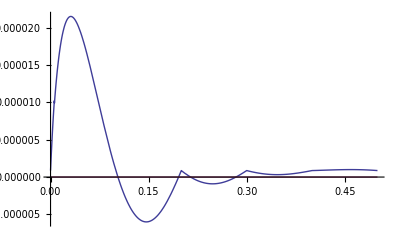

```mathematica
Plot[{Re[(χ0exact[1,b]-χ0approx[1,b])/χ0approx[1,b]],Im[(χ0exact[1,b]-χ0approx[1,b])/χ0approx[1,b]]},{b,0,.5},PlotRange->All]
```

```mathematica
T0[k_,b_]:=Exp[I*χ0approx[k,b]]-1
Eif0[k_,θ_]:=-I*k*NIntegrate[b*BesselJ[0,2*k*b*Sin[θ/2]]*T0[k,b],{b,0,15}]
```

```mathematica
σT[En_]:=10*4*Pi/(Sqrt[En^2+2*m*En]/ℏc)*Im[f[Sqrt[En^2+2*m*En]/ℏc,0]];
```

```mathematica
σT[375]
```

62.3631

```mathematica
Parallelize[Table[{LogEn,Log[σT[Exp[LogEn]]]},{LogEn,2,7,.5}]]
```

```mathematica
{{2.,6.883250316551756},{2.5,6.577046141411048},{3.,6.276084982083321},{3.5,5.960654342753458},{4.,5.614891672854321},{4.5,5.249305857077221},{5.,4.869005172950715},{5.5,4.476856424764091},{6.,4.073226287407308},{6.5,3.6563716216739},{7.,3.2238721129395675}}
```

{{2.,6.88325},{2.5,6.57705},{3.,6.27608},{3.5,5.96065},{4.,5.61489},{4.5,5.24931},{5.,4.86901},{5.5,4.47686},{6.,4.07323},{6.5,3.65637},{7.,3.22387}}

```mathematica
σTloglogplot=Interpolation[%];
```

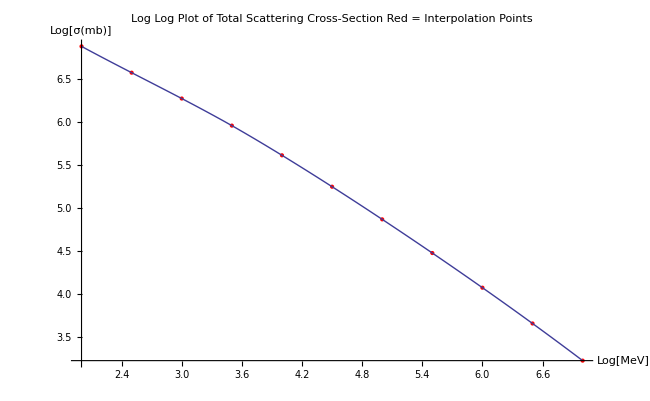

```mathematica
Show[ListPlot[{{2.,6.883250316551756},{2.5,6.577046141411048},{3.,6.276084982083321},{3.5,5.960654342753458},{4.,5.614891672854321},{4.5,5.249305857077221},{5.,4.869005172950715},{5.5,4.476856424764091},{6.,4.073226287407308},{6.5,3.6563716216739},{7.,3.2238721129395675}},PlotStyle->Red],Plot[σTloglogplot[LogEn],{LogEn,2,7}],PlotLabel->"Log Log Plot of Total Scattering Cross-Section
Red = Interpolation Points",AxesLabel->{"Log[MeV]","Log[σ(mb)]"},ImageSize->650]
```

```mathematica
σTEi0[En_]:=10*4*Pi/(Sqrt[En^2+2*m*En]/ℏc)*Im[Eif0[Sqrt[En^2+2*m*En]/ℏc,0]];
```

```mathematica
Parallelize[Table[{LogEn,Log[σTEi0[Exp[LogEn]]]},{LogEn,2,7,.5}]]//Timing
```

```mathematica
{0.58391099999999995784349948735325597227`5.786946570059089,{{2.,6.288286178976535},{2.5,6.203270405023718},{3.,6.0481238627734175},{3.5,5.817485433231609},{4.,5.527464683403758},{4.5,5.196034995356299},{5.,4.836664267537925},{5.5,4.457438301365623},{6.,4.061802687382665},{6.5,3.6499007429757055},{7.,3.2203716859040807}}}
```

{0.58391,{{2.,6.28829},{2.5,6.20327},{3.,6.04812},{3.5,5.81749},{4.,5.52746},{4.5,5.19603},{5.,4.83666},{5.5,4.45744},{6.,4.0618},{6.5,3.6499},{7.,3.22037}}}

```mathematica
σTEi0loglogplot=Interpolation[%[[2]]];
```

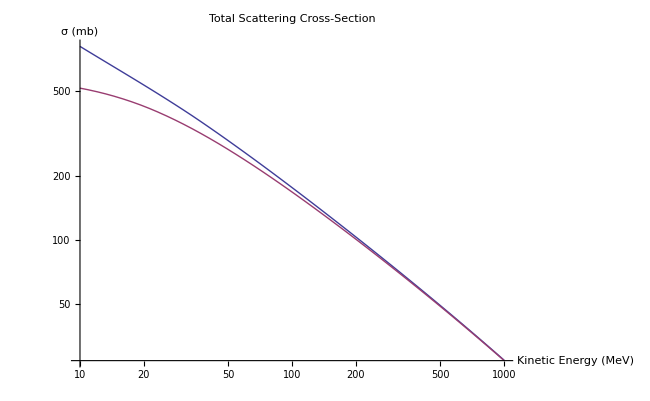

```mathematica
LogLogPlot[{Exp[σTloglogplot[Log[En]]],Exp[σTEi0loglogplot[Log[En]]]},{En,10,1000},PlotLegend->{"Exact Solution","Zeroth Order Eikonal"},LegendPosition->{.85,-0.2},LegendSize->{.9,0.4},PlotLabel->"Total Scattering Cross-Section",AxesLabel->{"Kinetic Energy (MeV)","σ (mb)"},ImageSize->650]
```

It is clear from the above graph that the Eikonal approximation breaks down as an estimate of the σtotal below about 100 MeV for this particular potential. That corresponds to a value of E/|V0| ~= 2.4. We could (and probably should) test this ratio and see if it seems independent of |V0|.

```mathematica
100/Abs[V0]
```

2.36285

```mathematica
eik0dσdΩ[En_]:=Table[{N[θ/10],Abs[Eif0[Sqrt[En^2+2*m*En]/ℏc,θ/10]]^2},{θ,0,10*Pi,1}]
```

```mathematica
Parallelize[Table[{N[θ/10],Abs[Eif0[Sqrt[100^2+2*m*100]/ℏc,θ/10]]^2},{θ,0,10*Pi,1}]]
```

```mathematica
{{0.,32.56120339752922},{0.1,29.42389881883016},{0.2,21.80466422565648},{0.3,13.405371867228013},{0.4,6.949703363321471},{0.5,3.0980008654714846},{0.6,1.2189134348540624},{0.7,0.4436159679941129},{0.8,0.1639425866390519},{0.9,0.07007745198878287},{1.,0.036422655020600415},{1.1,0.02111444357564474},{1.2,0.012367380488025293},{1.3,0.0070110229299580025},{1.4,0.0038314187843585933},{1.5,0.0020469026558312467},{1.6,0.0010931676131532043},{1.7,0.0005986403405123142},{1.8,0.000343882891722357},{1.9,0.00021007533141730836},{2.,0.00013671862364954263},{2.1,0.0000941194176805591},{2.2,0.00006786154895227352},{2.3,0.0000508284910041119},{2.4,0.00003935343611528353},{2.5,0.00003142850645746224},{2.6,0.000025881012122688156},{2.7,0.00002198814033809599},{2.8,0.000019288564600277476},{2.9,0.000017484381174177848},{3.,0.000016386863476496124},{3.1,0.000015885488306223304}}
```

{{0.,32.5612},{0.1,29.4239},{0.2,21.8047},{0.3,13.4054},{0.4,6.9497},{0.5,3.098},{0.6,1.21891},{0.7,0.443616},{0.8,0.163943},{0.9,0.0700775},{1.,0.0364227},{1.1,0.0211144},{1.2,0.0123674},{1.3,0.00701102},{1.4,0.00383142},{1.5,0.0020469},{1.6,0.00109317},{1.7,0.00059864},{1.8,0.000343883},{1.9,0.000210075},{2.,0.000136719},{2.1,0.0000941194},{2.2,0.0000678615},{2.3,0.0000508285},{2.4,0.0000393534},{2.5,0.0000314285},{2.6,0.000025881},{2.7,0.0000219881},{2.8,0.0000192886},{2.9,0.0000174844},{3.,0.0000163869},{3.1,0.0000158855}}

```mathematica
eik0interp1=Interpolation[%]
```

InterpolatingFunction[{{0.,3.1}},<>]

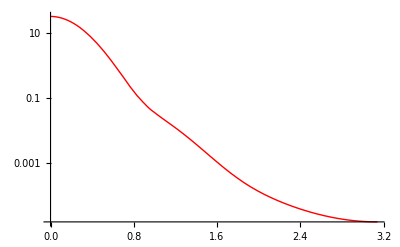

```mathematica
eik0p1=LogPlot[eik0interp1[θ],{θ,0,Pi},PlotStyle->Red]
```

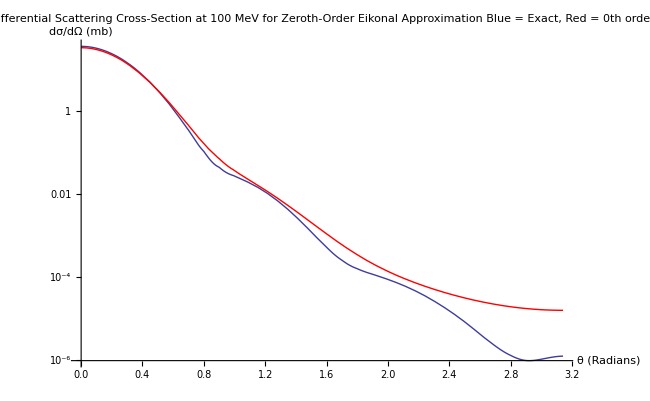

```mathematica
Show[p1,eik0p1,PlotLabel->"Differential Scattering Cross-Section at 100 MeV
for Zeroth-Order Eikonal Approximation
Blue = Exact, Red = 0th order",AxesLabel->{"θ (Radians)","dσ/dΩ (mb)"},ImageSize->650]
```

As you can see above, the two plots actually agree with each other pretty well, especially at small θ. There is some pretty obvious disagreement for large θ, however, and the eikonal approximation seems to miss some of the structure apparent in the partial wave formulation.

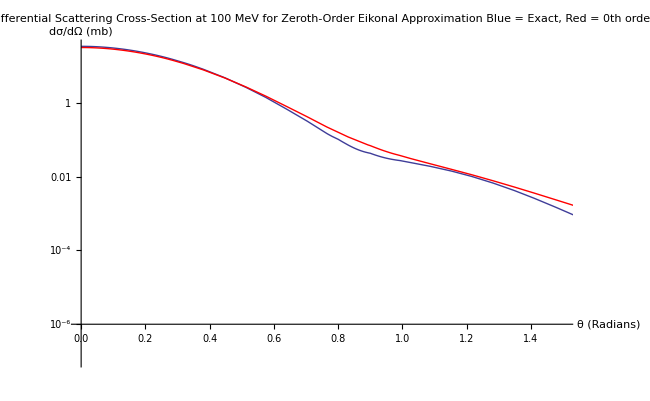

```mathematica
Show[p1,eik0p1,PlotRange->{{0,1.5},{Log[10^-7],Log[35]}},PlotLabel->"Differential Scattering Cross-Section at 100 MeV
for Zeroth-Order Eikonal Approximation
Blue = Exact, Red = 0th order",AxesLabel->{"θ (Radians)","dσ/dΩ (mb)"},ImageSize->650]
```

## Add in Eikonal Corrections

### First order correction

Below are parameters used by Wallace in his treatment of this:

```mathematica
En[k_]:=-m+Sqrt[m^2+(k*ℏc)^2]
U[r_]:=V[r]/V0
ϵ[k_]:=V0/(2*En[k])
```

```mathematica
τ1exact[k_,b_]=-k*ϵ[k]^2*NIntegrate[Evaluate[(1#+b*D[#,b])&[U[Sqrt[z^2+b^2]]^2]],{z,0,15}];
```

```mathematica
Parallelize[Table[{{k,b},τ1exact[k,b]},{b,0,15,.05},{k,Sqrt[100+2 m 10]/ℏc,Sqrt[1000^2+2 m 1000]/ℏc,.05}]]
```

{{{{0.696061,0.},-3.39921-1.41634 ⅈ},{{0.746061,0.},-2.76489-1.15204 ⅈ},{{0.796061,0.},-2.27975-0.949897 ⅈ},{{0.846061,0.},-1.90236-0.792651 ⅈ},{{0.896061,0.},-1.60436-0.668483 ⅈ},{{0.946061,0.},-1.36589-0.569123 ⅈ},{{0.996061,0.},-1.17279-0.488664 ⅈ},{{1.04606,0.},-1.01474-0.42281 ⅈ},{{1.09606,0.},-0.884126-0.368386 ⅈ},{{1.14606,0.},-0.775227-0.323011 ⅈ},{{1.19606,0.},-0.683704-0.284877 ⅈ},{{1.24606,0.},-0.606216-0.25259 ⅈ},{{1.29606,0.},-0.540167-0.22507 ⅈ},{{1.34606,0.},-0.483515-0.201465 ⅈ},{{1.39606,0.},-0.434641-0.181101 ⅈ},{{1.44606,0.},-0.392251-0.163438 ⅈ},{{1.49606,0.},-0.3553-0.148042 ⅈ},{{1.54606,0.},-0.322939-0.134558 ⅈ},{{1.59606,0.},-0.294474-0.122698 ⅈ},{{1.64606,0.},-0.269334-0.112223 ⅈ},{{1.69606,0.},-0.247044-0.102935 ⅈ},{{1.74606,0.},-0.22721-0.0946708 ⅈ},{{1.79606,0.},-0.2095-0.0872918 ⅈ},{{1.84606,0.},-0.193636-0.0806818 ⅈ},{{1.89606,0.},-0.179383-0.0747428 ⅈ},{{1.94606,0.},-0.166538-0.0693909 ⅈ},{{1.99606,0.},-0.154932-0.064555 ⅈ},{{2.04606,0.},-0.144417-0.0601739 ⅈ},{{2.09606,0.},-0.134868-0.0561948 ⅈ},{{2.14606,0.},-0.126174-0.0525724 ⅈ},{{2.19606,0.},-0.118241-0.0492672 ⅈ},{{2.24606,0.},-0.110988-0.0462449 ⅈ},{{2.29606,0.},-0.104341-0.0434756 ⅈ},{{2.34606,0.},-0.0982394-0.0409331 ⅈ},{{2.39606,0.},-0.0926264-0.0385943 ⅈ},{{2.44606,0.},-0.0874539-0.0364391 ⅈ},{{2.49606,0.},-0.0826791-0.0344496 ⅈ},{{2.54606,0.},-0.078264-0.03261 ⅈ},{{2.59606,0.},-0.0741748-0.0309062 ⅈ},{{2.64606,0.},-0.0703818-0.0293257 ⅈ},{{2.69606,0.},-0.0668581-0.0278576 ⅈ},{{2.74606,0.},-0.06358-0.0264917 ⅈ},{{2.79606,0.},-0.0605261-0.0252192 ⅈ},{{2.84606,0.},-0.0576773-0.0240322 ⅈ},{{2.89606,0.},-0.0550164-0.0229235 ⅈ},{{2.94606,0.},-0.0525278-0.0218866 ⅈ},{{2.99606,0.},-0.0501977-0.0209157 ⅈ},{{3.04606,0.},-0.0480133-0.0200055 ⅈ},{{3.09606,0.},-0.0459633-0.0191514 ⅈ},{{3.14606,0.},-0.0440373-0.0183489 ⅈ},{{3.19606,0.},-0.0422258-0.0175941 ⅈ},{{3.24606,0.},-0.0405204-0.0168835 ⅈ},{{3.29606,0.},-0.0389131-0.0162138 ⅈ},{{3.34606,0.},-0.037397-0.0155821 ⅈ},{{3.39606,0.},-0.0359654-0.0149856 ⅈ},{{3.44606,0.},-0.0346124-0.0144218 ⅈ},{{3.49606,0.},-0.0333327-0.0138886 ⅈ},{{3.54606,0.},-0.0321211-0.0133838 ⅈ},{{3.59606,0.},-0.0309731-0.0129055 ⅈ},{{3.64606,0.},-0.0298845-0.0124519 ⅈ},{{3.69606,0.},-0.0288514-0.0120214 ⅈ},{{3.74606,0.},-0.0278701-0.0116126 ⅈ},{{3.79606,0.},-0.0269375-0.011224 ⅈ},{{3.84606,0.},-0.0260504-0.0108543 ⅈ},{{3.89606,0.},-0.025206-0.0105025 ⅈ},{{3.94606,0.},-0.0244018-0.0101674 ⅈ},{{3.99606,0.},-0.0236352-0.00984799 ⅈ},{{4.04606,0.},-0.022904-0.00954333 ⅈ},{{4.09606,0.},-0.0222062-0.00925257 ⅈ},{{4.14606,0.},-0.0215397-0.00897489 ⅈ},{{4.19606,0.},-0.0209029-0.00870955 ⅈ},{{4.24606,0.},-0.020294-0.00845584 ⅈ},{{4.29606,0.},-0.0197115-0.00821311 ⅈ},{{4.34606,0.},-0.0191538-0.00798076 ⅈ},{{4.39606,0.},-0.0186197-0.00775821 ⅈ},{{4.44606,0.},-0.0181078-0.00754494 ⅈ},{{4.49606,0.},-0.0176171-0.00734044 ⅈ},{{4.54606,0.},-0.0171462-0.00714427 ⅈ},{{4.59606,0.},-0.0166943-0.00695597 ⅈ},{{4.64606,0.},-0.0162604-0.00677515 ⅈ},{{4.69606,0.},-0.0158434-0.00660142 ⅈ},{{4.74606,0.},-0.0154426-0.00643442 ⅈ},{{4.79606,0.},-0.0150572-0.00627383 ⅈ},{{4.84606,0.},-0.0146863-0.00611931 ⅈ},{{4.89606,0.},-0.0143294-0.00597058 ⅈ},{{4.94606,0.},-0.0139857-0.00582736 ⅈ},{{4.99606,0.},-0.0136545-0.00568937 ⅈ},{{5.04606,0.},-0.0133353-0.00555638 ⅈ},{{5.09606,0.},-0.0130276-0.00542815 ⅈ},{{5.14606,0.},-0.0127307-0.00530446 ⅈ},{{5.19606,0.},-0.0124442-0.0051851 ⅈ},{{5.24606,0.},-0.0121677-0.00506987 ⅈ},{{5.29606,0.},-0.0119006-0.0049586 ⅈ},{{5.34606,0.},-0.0116426-0.00485109 ⅈ},{{5.39606,0.},-0.0113933-0.00474719 ⅈ},{{5.44606,0.},-0.0111522-0.00464674 ⅈ},{{5.49606,0.},-0.010919-0.00454959 ⅈ},{{5.54606,0.},-0.0106934-0.00445559 ⅈ},{{5.59606,0.},-0.0104751-0.00436462 ⅈ},{{5.64606,0.},-0.0102637-0.00427655 ⅈ},{{5.69606,0.},-0.010059-0.00419126 ⅈ},{{5.74606,0.},-0.0098607-0.00410863 ⅈ},{{5.79606,0.},-0.00966852-0.00402855 ⅈ},{{5.84606,0.},-0.00948221-0.00395092 ⅈ},{{5.89606,0.},-0.00930155-0.00387565 ⅈ},{{5.94606,0.},-0.00912631-0.00380263 ⅈ},{{5.99606,0.},-0.00895628-0.00373178 ⅈ},{{6.04606,0.},-0.00879125-0.00366302 ⅈ},{{6.09606,0.},-0.00863104-0.00359627 ⅈ},{{6.14606,0.},-0.00847545-0.00353144 ⅈ},{{6.19606,0.},-0.00832432-0.00346847 ⅈ},{{6.24606,0.},-0.00817747-0.00340728 ⅈ},{{6.29606,0.},-0.00803474-0.00334781 ⅈ},{{6.34606,0.},-0.00789598-0.00328999 ⅈ},{{6.39606,0.},-0.00776105-0.00323377 ⅈ},{{6.44606,0.},-0.00762981-0.00317909 ⅈ},{{6.49606,0.},-0.00750212-0.00312588 ⅈ},{{6.54606,0.},-0.00737786-0.00307411 ⅈ},{{6.59606,0.},-0.0072569-0.00302371 ⅈ},{{6.64606,0.},-0.00713913-0.00297464 ⅈ},{{6.69606,0.},-0.00702444-0.00292685 ⅈ},{{6.74606,0.},-0.00691272-0.0028803 ⅈ},{{6.79606,0.},-0.00680386-0.00283494 ⅈ},{{6.84606,0.},-0.00669778-0.00279074 ⅈ},{{6.89606,0.},-0.00659438-0.00274766 ⅈ},{{6.94606,0.},-0.00649356-0.00270565 ⅈ},{{6.99606,0.},-0.00639525-0.00266469 ⅈ},{{7.04606,0.},-0.00629936-0.00262473 ⅈ},{{7.09606,0.},-0.0062058-0.00258575 ⅈ},{{7.14606,0.},-0.00611451-0.00254771 ⅈ},{{7.19606,0.},-0.00602542-0.00251059 ⅈ},{{7.24606,0.},-0.00593844-0.00247435 ⅈ},{{7.29606,0.},-0.00585351-0.00243896 ⅈ},{{7.34606,0.},-0.00577058-0.00240441 ⅈ},{{7.39606,0.},-0.00568957-0.00237065 ⅈ},{{7.44606,0.},-0.00561043-0.00233768 ⅈ},{{7.49606,0.},-0.0055331-0.00230546 ⅈ},{{7.54606,0.},-0.00545752-0.00227397 ⅈ},{{7.59606,0.},-0.00538365-0.00224319 ⅈ},{{7.64606,0.},-0.00531142-0.00221309 ⅈ},{{7.69606,0.},-0.0052408-0.00218367 ⅈ},{{7.74606,0.},-0.00517172-0.00215489 ⅈ},{{7.79606,0.},-0.00510416-0.00212673 ⅈ},{{7.84606,0.},-0.00503806-0.00209919 ⅈ},{{7.89606,0.},-0.00497338-0.00207224 ⅈ},{{7.94606,0.},-0.00491007-0.00204586 ⅈ},{{7.99606,0.},-0.00484811-0.00202005 ⅈ},{{8.04606,0.},-0.00478745-0.00199477 ⅈ},{{8.09606,0.},-0.00472806-0.00197002 ⅈ},{{8.14606,0.},-0.00466989-0.00194579 ⅈ},{{8.19606,0.},-0.00461292-0.00192205 ⅈ},{{8.24606,0.},-0.00455711-0.0018988 ⅈ},{{8.29606,0.},-0.00450243-0.00187601 ⅈ},{{8.34606,0.},-0.00444885-0.00185369 ⅈ},{{8.39606,0.},-0.00439634-0.00183181 ⅈ},{{8.44606,0.},-0.00434487-0.00181036 ⅈ},{{8.49606,0.},-0.00429442-0.00178934 ⅈ},{{8.54606,0.},-0.00424495-0.00176873 ⅈ}},{{{0.696061,0.05},-3.38554-1.41064 ⅈ},{{0.746061,0.05},-2.75377-1.1474 ⅈ},{{0.796061,0.05},-2.27058-0.946077 ⅈ},{{0.846061,0.05},-1.89471-0.789463 ⅈ},{{0.896061,0.05},-1.59791-0.665794 ⅈ},{{0.946061,0.05},-1.3604-0.566834 ⅈ},{{0.996061,0.05},-1.16808-0.486698 ⅈ},{{1.04606,0.05},-1.01066-0.421109 ⅈ},{{1.09606,0.05},-0.88057-0.366904 ⅈ},{{1.14606,0.05},-0.772109-0.321712 ⅈ},{{1.19606,0.05},-0.680954-0.283731 ⅈ},{{1.24606,0.05},-0.603778-0.251574 ⅈ},{{1.29606,0.05},-0.537995-0.224165 ⅈ},{{1.34606,0.05},-0.481571-0.200654 ⅈ},{{1.39606,0.05},-0.432893-0.180372 ⅈ},{{1.44606,0.05},-0.390674-0.162781 ⅈ},{{1.49606,0.05},-0.353871-0.147446 ⅈ},{{1.54606,0.05},-0.32164-0.134017 ⅈ},{{1.59606,0.05},-0.29329-0.122204 ⅈ},{{1.64606,0.05},-0.268251-0.111771 ⅈ},{{1.69606,0.05},-0.246051-0.102521 ⅈ},{{1.74606,0.05},-0.226296-0.0942901 ⅈ},{{1.79606,0.05},-0.208658-0.0869407 ⅈ},{{1.84606,0.05},-0.192858-0.0803574 ⅈ},{{1.89606,0.05},-0.178661-0.0744422 ⅈ},{{1.94606,0.05},-0.165868-0.0691119 ⅈ},{{1.99606,0.05},-0.154309-0.0642954 ⅈ},{{2.04606,0.05},-0.143837-0.0599319 ⅈ},{{2.09606,0.05},-0.134325-0.0559688 ⅈ},{{2.14606,0.05},-0.125666-0.052361 ⅈ},{{2.19606,0.05},-0.117766-0.0490691 ⅈ},{{2.24606,0.05},-0.110541-0.0460589 ⅈ},{{2.29606,0.05},-0.103922-0.0433008 ⅈ},{{2.34606,0.05},-0.0978443-0.0407685 ⅈ},{{2.39606,0.05},-0.0922539-0.0384391 ⅈ},{{2.44606,0.05},-0.0871022-0.0362926 ⅈ},{{2.49606,0.05},-0.0823466-0.0343111 ⅈ},{{2.54606,0.05},-0.0779492-0.0324788 ⅈ},{{2.59606,0.05},-0.0738765-0.0307819 ⅈ},{{2.64606,0.05},-0.0700987-0.0292078 ⅈ},{{2.69606,0.05},-0.0665892-0.0277455 ⅈ},{{2.74606,0.05},-0.0633243-0.0263851 ⅈ},{{2.79606,0.05},-0.0602827-0.0251178 ⅈ},{{2.84606,0.05},-0.0574454-0.0239356 ⅈ},{{2.89606,0.05},-0.0547951-0.0228313 ⅈ},{{2.94606,0.05},-0.0523166-0.0217986 ⅈ},{{2.99606,0.05},-0.0499958-0.0208316 ⅈ},{{3.04606,0.05},-0.0478202-0.0199251 ⅈ},{{3.09606,0.05},-0.0457784-0.0190744 ⅈ},{{3.14606,0.05},-0.0438602-0.0182751 ⅈ},{{3.19606,0.05},-0.042056-0.0175233 ⅈ},{{3.24606,0.05},-0.0403574-0.0168156 ⅈ},{{3.29606,0.05},-0.0387566-0.0161486 ⅈ},{{3.34606,0.05},-0.0372465-0.0155194 ⅈ},{{3.39606,0.05},-0.0358207-0.0149253 ⅈ},{{3.44606,0.05},-0.0344732-0.0143638 ⅈ},{{3.49606,0.05},-0.0331986-0.0138328 ⅈ},{{3.54606,0.05},-0.0319919-0.01333 ⅈ},{{3.59606,0.05},-0.0308485-0.0128536 ⅈ},{{3.64606,0.05},-0.0297643-0.0124018 ⅈ},{{3.69606,0.05},-0.0287353-0.0119731 ⅈ},{{3.74606,0.05},-0.0277581-0.0115659 ⅈ},{{3.79606,0.05},-0.0268292-0.0111788 ⅈ},{{3.84606,0.05},-0.0259457-0.0108107 ⅈ},{{3.89606,0.05},-0.0251047-0.0104603 ⅈ},{{3.94606,0.05},-0.0243036-0.0101265 ⅈ},{{3.99606,0.05},-0.0235401-0.00980838 ⅈ},{{4.04606,0.05},-0.0228119-0.00950495 ⅈ},{{4.09606,0.05},-0.0221169-0.00921536 ⅈ},{{4.14606,0.05},-0.0214531-0.0089388 ⅈ},{{4.19606,0.05},-0.0208189-0.00867452 ⅈ},{{4.24606,0.05},-0.0202124-0.00842183 ⅈ},{{4.29606,0.05},-0.0196322-0.00818008 ⅈ},{{4.34606,0.05},-0.0190768-0.00794866 ⅈ},{{4.39606,0.05},-0.0185448-0.00772701 ⅈ},{{4.44606,0.05},-0.018035-0.00751459 ⅈ},{{4.49606,0.05},-0.0175462-0.00731092 ⅈ},{{4.54606,0.05},-0.0170773-0.00711553 ⅈ},{{4.59606,0.05},-0.0166272-0.00692799 ⅈ},{{4.64606,0.05},-0.016195-0.0067479 ⅈ},{{4.69606,0.05},-0.0157797-0.00657487 ⅈ},{{4.74606,0.05},-0.0153805-0.00640855 ⅈ},{{4.79606,0.05},-0.0149966-0.00624859 ⅈ},{{4.84606,0.05},-0.0146273-0.0060947 ⅈ},{{4.89606,0.05},-0.0142718-0.00594657 ⅈ},{{4.94606,0.05},-0.0139294-0.00580392 ⅈ},{{4.99606,0.05},-0.0135996-0.00566649 ⅈ},{{5.04606,0.05},-0.0132817-0.00553404 ⅈ},{{5.09606,0.05},-0.0129752-0.00540632 ⅈ},{{5.14606,0.05},-0.0126795-0.00528313 ⅈ},{{5.19606,0.05},-0.0123942-0.00516425 ⅈ},{{5.24606,0.05},-0.0121188-0.00504948 ⅈ},{{5.29606,0.05},-0.0118528-0.00493865 ⅈ},{{5.34606,0.05},-0.0115958-0.00483158 ⅈ},{{5.39606,0.05},-0.0113474-0.0047281 ⅈ},{{5.44606,0.05},-0.0111073-0.00462805 ⅈ},{{5.49606,0.05},-0.0108751-0.00453129 ⅈ},{{5.54606,0.05},-0.0106504-0.00443767 ⅈ},{{5.59606,0.05},-0.010433-0.00434707 ⅈ},{{5.64606,0.05},-0.0102224-0.00425935 ⅈ},{{5.69606,0.05},-0.0100186-0.0041744 ⅈ},{{5.74606,0.05},-0.00982104-0.0040921 ⅈ},{{5.79606,0.05},-0.00962963-0.00401235 ⅈ},{{5.84606,0.05},-0.00944407-0.00393503 ⅈ},{{5.89606,0.05},-0.00926414-0.00386006 ⅈ},{{5.94606,0.05},-0.00908961-0.00378734 ⅈ},{{5.99606,0.05},-0.00892026-0.00371677 ⅈ},{{6.04606,0.05},-0.0087559-0.00364829 ⅈ},{{6.09606,0.05},-0.00859633-0.0035818 ⅈ},{{6.14606,0.05},-0.00844137-0.00351724 ⅈ},{{6.19606,0.05},-0.00829084-0.00345452 ⅈ},{{6.24606,0.05},-0.00814458-0.00339357 ⅈ},{{6.29606,0.05},-0.00800243-0.00333434 ⅈ},{{6.34606,0.05},-0.00786423-0.00327676 ⅈ},{{6.39606,0.05},-0.00772984-0.00322077 ⅈ},{{6.44606,0.05},-0.00759912-0.0031663 ⅈ},{{6.49606,0.05},-0.00747195-0.00311331 ⅈ},{{6.54606,0.05},-0.00734819-0.00306174 ⅈ},{{6.59606,0.05},-0.00722771-0.00301155 ⅈ},{{6.64606,0.05},-0.00711042-0.00296267 ⅈ},{{6.69606,0.05},-0.00699619-0.00291508 ⅈ},{{6.74606,0.05},-0.00688491-0.00286871 ⅈ},{{6.79606,0.05},-0.0067765-0.00282354 ⅈ},{{6.84606,0.05},-0.00667085-0.00277952 ⅈ},{{6.89606,0.05},-0.00656786-0.00273661 ⅈ},{{6.94606,0.05},-0.00646745-0.00269477 ⅈ},{{6.99606,0.05},-0.00636953-0.00265397 ⅈ},{{7.04606,0.05},-0.00627402-0.00261418 ⅈ},{{7.09606,0.05},-0.00618084-0.00257535 ⅈ},{{7.14606,0.05},-0.00608992-0.00253747 ⅈ},{{7.19606,0.05},-0.00600118-0.00250049 ⅈ},{{7.24606,0.05},-0.00591455-0.0024644 ⅈ},{{7.29606,0.05},-0.00582997-0.00242916 ⅈ},{{7.34606,0.05},-0.00574737-0.00239474 ⅈ},{{7.39606,0.05},-0.00566669-0.00236112 ⅈ},{{7.44606,0.05},-0.00558787-0.00232828 ⅈ},{{7.49606,0.05},-0.00551085-0.00229619 ⅈ},{{7.54606,0.05},-0.00543557-0.00226482 ⅈ},{{7.59606,0.05},-0.005362-0.00223417 ⅈ},{{7.64606,0.05},-0.00529006-0.00220419 ⅈ},{{7.69606,0.05},-0.00521972-0.00217488 ⅈ},{{7.74606,0.05},-0.00515093-0.00214622 ⅈ},{{7.79606,0.05},-0.00508363-0.00211818 ⅈ},{{7.84606,0.05},-0.0050178-0.00209075 ⅈ},{{7.89606,0.05},-0.00495337-0.00206391 ⅈ},{{7.94606,0.05},-0.00489033-0.00203764 ⅈ},{{7.99606,0.05},-0.00482861-0.00201192 ⅈ},{{8.04606,0.05},-0.0047682-0.00198675 ⅈ},{{8.09606,0.05},-0.00470904-0.0019621 ⅈ},{{8.14606,0.05},-0.00465111-0.00193796 ⅈ},{{8.19606,0.05},-0.00459437-0.00191432 ⅈ},{{8.24606,0.05},-0.00453878-0.00189116 ⅈ},{{8.29606,0.05},-0.00448432-0.00186847 ⅈ},{{8.34606,0.05},-0.00443096-0.00184623 ⅈ},{{8.39606,0.05},-0.00437866-0.00182444 ⅈ},{{8.44606,0.05},-0.0043274-0.00180308 ⅈ},{{8.49606,0.05},-0.00427715-0.00178214 ⅈ},{{8.54606,0.05},-0.00422788-0.00176162 ⅈ}},{{{0.696061,0.1},-3.34886-1.39536 ⅈ},{{0.746061,0.1},-2.72394-1.13497 ⅈ},{{0.796061,0.1},-2.24599-0.935827 ⅈ},{{0.846061,0.1},-1.87418-0.78091 ⅈ},{{0.896061,0.1},-1.5806-0.658581 ⅈ},{{0.946061,0.1},-1.34566-0.560693 ⅈ},{{0.996061,0.1},-1.15542-0.481426 ⅈ},{{1.04606,0.1},-0.999712-0.416547 ⅈ},{{1.09606,0.1},-0.87103-0.362929 ⅈ},{{1.14606,0.1},-0.763744-0.318227 ⅈ},{{1.19606,0.1},-0.673577-0.280657 ⅈ},{{1.24606,0.1},-0.597237-0.248849 ⅈ},{{1.29606,0.1},-0.532166-0.221736 ⅈ},{{1.34606,0.1},-0.476353-0.198481 ⅈ},{{1.39606,0.1},-0.428203-0.178418 ⅈ},{{1.44606,0.1},-0.386441-0.161017 ⅈ},{{1.49606,0.1},-0.350037-0.145849 ⅈ},{{1.54606,0.1},-0.318156-0.132565 ⅈ},{{1.59606,0.1},-0.290113-0.12088 ⅈ},{{1.64606,0.1},-0.265345-0.11056 ⅈ},{{1.69606,0.1},-0.243385-0.10141 ⅈ},{{1.74606,0.1},-0.223844-0.0932685 ⅈ},{{1.79606,0.1},-0.206397-0.0859988 ⅈ},{{1.84606,0.1},-0.190768-0.0794868 ⅈ},{{1.89606,0.1},-0.176726-0.0736357 ⅈ},{{1.94606,0.1},-0.164071-0.0683631 ⅈ},{{1.99606,0.1},-0.152637-0.0635988 ⅈ},{{2.04606,0.1},-0.142278-0.0592826 ⅈ},{{2.09606,0.1},-0.13287-0.0553625 ⅈ},{{2.14606,0.1},-0.124305-0.0517937 ⅈ},{{2.19606,0.1},-0.11649-0.0485375 ⅈ},{{2.24606,0.1},-0.109344-0.0455599 ⅈ},{{2.29606,0.1},-0.102796-0.0428316 ⅈ},{{2.34606,0.1},-0.0967843-0.0403268 ⅈ},{{2.39606,0.1},-0.0912544-0.0380227 ⅈ},{{2.44606,0.1},-0.0861586-0.0358994 ⅈ},{{2.49606,0.1},-0.0814545-0.0339394 ⅈ},{{2.54606,0.1},-0.0771047-0.032127 ⅈ},{{2.59606,0.1},-0.0730762-0.0304484 ⅈ},{{2.64606,0.1},-0.0693393-0.0288914 ⅈ},{{2.69606,0.1},-0.0658678-0.0274449 ⅈ},{{2.74606,0.1},-0.0626383-0.0260993 ⅈ},{{2.79606,0.1},-0.0596296-0.0248457 ⅈ},{{2.84606,0.1},-0.056823-0.0236763 ⅈ},{{2.89606,0.1},-0.0542015-0.0225839 ⅈ},{{2.94606,0.1},-0.0517498-0.0215624 ⅈ},{{2.99606,0.1},-0.0494541-0.0206059 ⅈ},{{3.04606,0.1},-0.0473021-0.0197092 ⅈ},{{3.09606,0.1},-0.0452825-0.0188677 ⅈ},{{3.14606,0.1},-0.043385-0.0180771 ⅈ},{{3.19606,0.1},-0.0416004-0.0173335 ⅈ},{{3.24606,0.1},-0.0399202-0.0166334 ⅈ},{{3.29606,0.1},-0.0383367-0.0159736 ⅈ},{{3.34606,0.1},-0.036843-0.0153513 ⅈ},{{3.39606,0.1},-0.0354327-0.0147636 ⅈ},{{3.44606,0.1},-0.0340998-0.0142082 ⅈ},{{3.49606,0.1},-0.0328389-0.0136829 ⅈ},{{3.54606,0.1},-0.0316453-0.0131855 ⅈ},{{3.59606,0.1},-0.0305143-0.0127143 ⅈ},{{3.64606,0.1},-0.0294419-0.0122674 ⅈ},{{3.69606,0.1},-0.028424-0.0118433 ⅈ},{{3.74606,0.1},-0.0274573-0.0114406 ⅈ},{{3.79606,0.1},-0.0265385-0.0110577 ⅈ},{{3.84606,0.1},-0.0256646-0.0106936 ⅈ},{{3.89606,0.1},-0.0248327-0.010347 ⅈ},{{3.94606,0.1},-0.0240403-0.0100168 ⅈ},{{3.99606,0.1},-0.0232851-0.00970212 ⅈ},{{4.04606,0.1},-0.0225647-0.00940197 ⅈ},{{4.09606,0.1},-0.0218772-0.00911552 ⅈ},{{4.14606,0.1},-0.0212207-0.00884196 ⅈ},{{4.19606,0.1},-0.0205933-0.00858054 ⅈ},{{4.24606,0.1},-0.0199934-0.00833059 ⅈ},{{4.29606,0.1},-0.0194195-0.00809146 ⅈ},{{4.34606,0.1},-0.0188701-0.00786255 ⅈ},{{4.39606,0.1},-0.0183439-0.0076433 ⅈ},{{4.44606,0.1},-0.0178396-0.00743318 ⅈ},{{4.49606,0.1},-0.0173561-0.00723172 ⅈ},{{4.54606,0.1},-0.0168923-0.00703845 ⅈ},{{4.59606,0.1},-0.0164471-0.00685294 ⅈ},{{4.64606,0.1},-0.0160195-0.00667479 ⅈ},{{4.69606,0.1},-0.0156087-0.00650364 ⅈ},{{4.74606,0.1},-0.0152139-0.00633912 ⅈ},{{4.79606,0.1},-0.0148342-0.0061809 ⅈ},{{4.84606,0.1},-0.0144688-0.00602867 ⅈ},{{4.89606,0.1},-0.0141171-0.00588215 ⅈ},{{4.94606,0.1},-0.0137785-0.00574104 ⅈ},{{4.99606,0.1},-0.0134522-0.0056051 ⅈ},{{5.04606,0.1},-0.0131378-0.00547408 ⅈ},{{5.09606,0.1},-0.0128346-0.00534775 ⅈ},{{5.14606,0.1},-0.0125421-0.00522589 ⅈ},{{5.19606,0.1},-0.0122599-0.0051083 ⅈ},{{5.24606,0.1},-0.0119875-0.00499478 ⅈ},{{5.29606,0.1},-0.0117244-0.00488515 ⅈ},{{5.34606,0.1},-0.0114702-0.00477924 ⅈ},{{5.39606,0.1},-0.0112245-0.00467687 ⅈ},{{5.44606,0.1},-0.010987-0.00457791 ⅈ},{{5.49606,0.1},-0.0107573-0.0044822 ⅈ},{{5.54606,0.1},-0.010535-0.0043896 ⅈ},{{5.59606,0.1},-0.0103199-0.00429998 ⅈ},{{5.64606,0.1},-0.0101117-0.00421321 ⅈ},{{5.69606,0.1},-0.00991002-0.00412918 ⅈ},{{5.74606,0.1},-0.00971465-0.00404777 ⅈ},{{5.79606,0.1},-0.00952531-0.00396888 ⅈ},{{5.84606,0.1},-0.00934176-0.0038924 ⅈ},{{5.89606,0.1},-0.00916377-0.00381824 ⅈ},{{5.94606,0.1},-0.00899113-0.0037463 ⅈ},{{5.99606,0.1},-0.00882362-0.00367651 ⅈ},{{6.04606,0.1},-0.00866104-0.00360877 ⅈ},{{6.09606,0.1},-0.0085032-0.003543 ⅈ},{{6.14606,0.1},-0.00834991-0.00347913 ⅈ},{{6.19606,0.1},-0.00820102-0.00341709 ⅈ},{{6.24606,0.1},-0.00805634-0.00335681 ⅈ},{{6.29606,0.1},-0.00791573-0.00329822 ⅈ},{{6.34606,0.1},-0.00777903-0.00324126 ⅈ},{{6.39606,0.1},-0.0076461-0.00318587 ⅈ},{{6.44606,0.1},-0.0075168-0.003132 ⅈ},{{6.49606,0.1},-0.007391-0.00307958 ⅈ},{{6.54606,0.1},-0.00726858-0.00302857 ⅈ},{{6.59606,0.1},-0.00714941-0.00297892 ⅈ},{{6.64606,0.1},-0.00703338-0.00293058 ⅈ},{{6.69606,0.1},-0.00692039-0.0028835 ⅈ},{{6.74606,0.1},-0.00681033-0.00283764 ⅈ},{{6.79606,0.1},-0.00670309-0.00279295 ⅈ},{{6.84606,0.1},-0.00659858-0.00274941 ⅈ},{{6.89606,0.1},-0.0064967-0.00270696 ⅈ},{{6.94606,0.1},-0.00639738-0.00266558 ⅈ},{{6.99606,0.1},-0.00630052-0.00262522 ⅈ},{{7.04606,0.1},-0.00620605-0.00258585 ⅈ},{{7.09606,0.1},-0.00611388-0.00254745 ⅈ},{{7.14606,0.1},-0.00602395-0.00250998 ⅈ},{{7.19606,0.1},-0.00593617-0.0024734 ⅈ},{{7.24606,0.1},-0.00585048-0.0024377 ⅈ},{{7.29606,0.1},-0.00576681-0.00240284 ⅈ},{{7.34606,0.1},-0.00568511-0.00236879 ⅈ},{{7.39606,0.1},-0.0056053-0.00233554 ⅈ},{{7.44606,0.1},-0.00552733-0.00230305 ⅈ},{{7.49606,0.1},-0.00545114-0.00227131 ⅈ},{{7.54606,0.1},-0.00537669-0.00224029 ⅈ},{{7.59606,0.1},-0.00530391-0.00220996 ⅈ},{{7.64606,0.1},-0.00523275-0.00218031 ⅈ},{{7.69606,0.1},-0.00516317-0.00215132 ⅈ},{{7.74606,0.1},-0.00509512-0.00212297 ⅈ},{{7.79606,0.1},-0.00502856-0.00209523 ⅈ},{{7.84606,0.1},-0.00496343-0.0020681 ⅈ},{{7.89606,0.1},-0.00489971-0.00204155 ⅈ},{{7.94606,0.1},-0.00483735-0.00201556 ⅈ},{{7.99606,0.1},-0.0047763-0.00199013 ⅈ},{{8.04606,0.1},-0.00471654-0.00196522 ⅈ},{{8.09606,0.1},-0.00465802-0.00194084 ⅈ},{{8.14606,0.1},-0.00460072-0.00191697 ⅈ},{{8.19606,0.1},-0.00454459-0.00189358 ⅈ},{{8.24606,0.1},-0.00448961-0.00187067 ⅈ},{{8.29606,0.1},-0.00443574-0.00184823 ⅈ},{{8.34606,0.1},-0.00438296-0.00182623 ⅈ},{{8.39606,0.1},-0.00433122-0.00180468 ⅈ},{{8.44606,0.1},-0.00428052-0.00178355 ⅈ},{{8.49606,0.1},-0.00423081-0.00176284 ⅈ},{{8.54606,0.1},-0.00418207-0.00174253 ⅈ}},{{{0.696061,0.15},-3.29158-1.37149 ⅈ},{{0.746061,0.15},-2.67735-1.11556 ⅈ},{{0.796061,0.15},-2.20757-0.919822 ⅈ},{{0.846061,0.15},-1.84213-0.767554 ⅈ},{{0.896061,0.15},-1.55356-0.647317 ⅈ},{{0.946061,0.15},-1.32265-0.551103 ⅈ},{{0.996061,0.15},-1.13566-0.473192 ⅈ},{{1.04606,0.15},-0.982614-0.409423 ⅈ},{{1.09606,0.15},-0.856133-0.356722 ⅈ},{{1.14606,0.15},-0.750682-0.312784 ⅈ},{{1.19606,0.15},-0.662056-0.275857 ⅈ},{{1.24606,0.15},-0.587022-0.244593 ⅈ},{{1.29606,0.15},-0.523065-0.217944 ⅈ},{{1.34606,0.15},-0.468206-0.195086 ⅈ},{{1.39606,0.15},-0.42088-0.175367 ⅈ},{{1.44606,0.15},-0.379832-0.158263 ⅈ},{{1.49606,0.15},-0.34405-0.143354 ⅈ},{{1.54606,0.15},-0.312714-0.130298 ⅈ},{{1.59606,0.15},-0.285151-0.118813 ⅈ},{{1.64606,0.15},-0.260806-0.108669 ⅈ},{{1.69606,0.15},-0.239222-0.099676 ⅈ},{{1.74606,0.15},-0.220016-0.0916734 ⅈ},{{1.79606,0.15},-0.202867-0.0845279 ⅈ},{{1.84606,0.15},-0.187506-0.0781273 ⅈ},{{1.89606,0.15},-0.173703-0.0723763 ⅈ},{{1.94606,0.15},-0.161265-0.0671939 ⅈ},{{1.99606,0.15},-0.150027-0.0625111 ⅈ},{{2.04606,0.15},-0.139845-0.0582687 ⅈ},{{2.09606,0.15},-0.130597-0.0544156 ⅈ},{{2.14606,0.15},-0.122179-0.0509079 ⅈ},{{2.19606,0.15},-0.114498-0.0477073 ⅈ},{{2.24606,0.15},-0.107474-0.0447807 ⅈ},{{2.29606,0.15},-0.101038-0.0420991 ⅈ},{{2.34606,0.15},-0.0951289-0.0396371 ⅈ},{{2.39606,0.15},-0.0896937-0.0373724 ⅈ},{{2.44606,0.15},-0.084685-0.0352854 ⅈ},{{2.49606,0.15},-0.0800613-0.0333589 ⅈ},{{2.54606,0.15},-0.075786-0.0315775 ⅈ},{{2.59606,0.15},-0.0718263-0.0299276 ⅈ},{{2.64606,0.15},-0.0681534-0.0283972 ⅈ},{{2.69606,0.15},-0.0647413-0.0269755 ⅈ},{{2.74606,0.15},-0.061567-0.0256529 ⅈ},{{2.79606,0.15},-0.0586098-0.0244207 ⅈ},{{2.84606,0.15},-0.0558511-0.0232713 ⅈ},{{2.89606,0.15},-0.0532745-0.0221977 ⅈ},{{2.94606,0.15},-0.0508647-0.0211936 ⅈ},{{2.99606,0.15},-0.0486083-0.0202535 ⅈ},{{3.04606,0.15},-0.0464931-0.0193721 ⅈ},{{3.09606,0.15},-0.044508-0.018545 ⅈ},{{3.14606,0.15},-0.042643-0.0177679 ⅈ},{{3.19606,0.15},-0.0408889-0.017037 ⅈ},{{3.24606,0.15},-0.0392374-0.0163489 ⅈ},{{3.29606,0.15},-0.0376811-0.0157004 ⅈ},{{3.34606,0.15},-0.0362129-0.0150887 ⅈ},{{3.39606,0.15},-0.0348266-0.0145111 ⅈ},{{3.44606,0.15},-0.0335165-0.0139652 ⅈ},{{3.49606,0.15},-0.0322773-0.0134489 ⅈ},{{3.54606,0.15},-0.0311041-0.01296 ⅈ},{{3.59606,0.15},-0.0299924-0.0124969 ⅈ},{{3.64606,0.15},-0.0289383-0.0120576 ⅈ},{{3.69606,0.15},-0.0279379-0.0116408 ⅈ},{{3.74606,0.15},-0.0269877-0.0112449 ⅈ},{{3.79606,0.15},-0.0260846-0.0108686 ⅈ},{{3.84606,0.15},-0.0252256-0.0105107 ⅈ},{{3.89606,0.15},-0.024408-0.01017 ⅈ},{{3.94606,0.15},-0.0236292-0.00984548 ⅈ},{{3.99606,0.15},-0.0228868-0.00953618 ⅈ},{{4.04606,0.15},-0.0221788-0.00924117 ⅈ},{{4.09606,0.15},-0.0215031-0.00895962 ⅈ},{{4.14606,0.15},-0.0208578-0.00869073 ⅈ},{{4.19606,0.15},-0.0202411-0.00843379 ⅈ},{{4.24606,0.15},-0.0196515-0.00818811 ⅈ},{{4.29606,0.15},-0.0190874-0.00795307 ⅈ},{{4.34606,0.15},-0.0185474-0.00772807 ⅈ},{{4.39606,0.15},-0.0180302-0.00751257 ⅈ},{{4.44606,0.15},-0.0175345-0.00730605 ⅈ},{{4.49606,0.15},-0.0170593-0.00710803 ⅈ},{{4.54606,0.15},-0.0166034-0.00691807 ⅈ},{{4.59606,0.15},-0.0161658-0.00673573 ⅈ},{{4.64606,0.15},-0.0157455-0.00656063 ⅈ},{{4.69606,0.15},-0.0153418-0.00639241 ⅈ},{{4.74606,0.15},-0.0149537-0.0062307 ⅈ},{{4.79606,0.15},-0.0145804-0.00607519 ⅈ},{{4.84606,0.15},-0.0142214-0.00592556 ⅈ},{{4.89606,0.15},-0.0138757-0.00578154 ⅈ},{{4.94606,0.15},-0.0135428-0.00564285 ⅈ},{{4.99606,0.15},-0.0132222-0.00550924 ⅈ},{{5.04606,0.15},-0.0129131-0.00538046 ⅈ},{{5.09606,0.15},-0.0126151-0.00525629 ⅈ},{{5.14606,0.15},-0.0123276-0.00513651 ⅈ},{{5.19606,0.15},-0.0120502-0.00502093 ⅈ},{{5.24606,0.15},-0.0117824-0.00490935 ⅈ},{{5.29606,0.15},-0.0115238-0.0048016 ⅈ},{{5.34606,0.15},-0.011274-0.0046975 ⅈ},{{5.39606,0.15},-0.0110325-0.00459689 ⅈ},{{5.44606,0.15},-0.0107991-0.00449961 ⅈ},{{5.49606,0.15},-0.0105733-0.00440554 ⅈ},{{5.54606,0.15},-0.0103548-0.00431452 ⅈ},{{5.59606,0.15},-0.0101434-0.00422643 ⅈ},{{5.64606,0.15},-0.00993876-0.00414115 ⅈ},{{5.69606,0.15},-0.00974053-0.00405856 ⅈ},{{5.74606,0.15},-0.00954849-0.00397854 ⅈ},{{5.79606,0.15},-0.00936239-0.003901 ⅈ},{{5.84606,0.15},-0.00918199-0.00382583 ⅈ},{{5.89606,0.15},-0.00900704-0.00375294 ⅈ},{{5.94606,0.15},-0.00883735-0.00368223 ⅈ},{{5.99606,0.15},-0.00867271-0.00361363 ⅈ},{{6.04606,0.15},-0.00851291-0.00354704 ⅈ},{{6.09606,0.15},-0.00835777-0.0034824 ⅈ},{{6.14606,0.15},-0.0082071-0.00341963 ⅈ},{{6.19606,0.15},-0.00806075-0.00335865 ⅈ},{{6.24606,0.15},-0.00791855-0.0032994 ⅈ},{{6.29606,0.15},-0.00778035-0.00324181 ⅈ},{{6.34606,0.15},-0.00764598-0.00318583 ⅈ},{{6.39606,0.15},-0.00751532-0.00313139 ⅈ},{{6.44606,0.15},-0.00738824-0.00307843 ⅈ},{{6.49606,0.15},-0.00726459-0.00302691 ⅈ},{{6.54606,0.15},-0.00714426-0.00297678 ⅈ},{{6.59606,0.15},-0.00702713-0.00292797 ⅈ},{{6.64606,0.15},-0.00691309-0.00288045 ⅈ},{{6.69606,0.15},-0.00680203-0.00283418 ⅈ},{{6.74606,0.15},-0.00669385-0.0027891 ⅈ},{{6.79606,0.15},-0.00658844-0.00274518 ⅈ},{{6.84606,0.15},-0.00648572-0.00270238 ⅈ},{{6.89606,0.15},-0.00638559-0.00266066 ⅈ},{{6.94606,0.15},-0.00628797-0.00261999 ⅈ},{{6.99606,0.15},-0.00619277-0.00258032 ⅈ},{{7.04606,0.15},-0.00609991-0.00254163 ⅈ},{{7.09606,0.15},-0.00600932-0.00250388 ⅈ},{{7.14606,0.15},-0.00592092-0.00246705 ⅈ},{{7.19606,0.15},-0.00583464-0.0024311 ⅈ},{{7.24606,0.15},-0.00575042-0.00239601 ⅈ},{{7.29606,0.15},-0.00566818-0.00236174 ⅈ},{{7.34606,0.15},-0.00558787-0.00232828 ⅈ},{{7.39606,0.15},-0.00550943-0.0022956 ⅈ},{{7.44606,0.15},-0.00543279-0.00226366 ⅈ},{{7.49606,0.15},-0.00535791-0.00223246 ⅈ},{{7.54606,0.15},-0.00528473-0.00220197 ⅈ},{{7.59606,0.15},-0.00521319-0.00217216 ⅈ},{{7.64606,0.15},-0.00514325-0.00214302 ⅈ},{{7.69606,0.15},-0.00507486-0.00211453 ⅈ},{{7.74606,0.15},-0.00500798-0.00208666 ⅈ},{{7.79606,0.15},-0.00494255-0.0020594 ⅈ},{{7.84606,0.15},-0.00487854-0.00203273 ⅈ},{{7.89606,0.15},-0.00481591-0.00200663 ⅈ},{{7.94606,0.15},-0.00475461-0.00198109 ⅈ},{{7.99606,0.15},-0.00469461-0.00195609 ⅈ},{{8.04606,0.15},-0.00463587-0.00193161 ⅈ},{{8.09606,0.15},-0.00457836-0.00190765 ⅈ},{{8.14606,0.15},-0.00452203-0.00188418 ⅈ},{{8.19606,0.15},-0.00446687-0.00186119 ⅈ},{{8.24606,0.15},-0.00441282-0.00183868 ⅈ},{{8.29606,0.15},-0.00435988-0.00181662 ⅈ},{{8.34606,0.15},-0.00430799-0.001795 ⅈ},{{8.39606,0.15},-0.00425715-0.00177381 ⅈ},{{8.44606,0.15},-0.00420731-0.00175304 ⅈ},{{8.49606,0.15},-0.00415845-0.00173269 ⅈ},{{8.54606,0.15},-0.00411055-0.00171273 ⅈ}},{{{0.696061,0.2},-3.21498-1.33957 ⅈ},{{0.746061,0.2},-2.61503-1.0896 ⅈ},{{0.796061,0.2},-2.15619-0.898413 ⅈ},{{0.846061,0.2},-1.79926-0.74969 ⅈ},{{0.896061,0.2},-1.5174-0.632252 ⅈ},{{0.946061,0.2},-1.29186-0.538277 ⅈ},{{0.996061,0.2},-1.10923-0.462178 ⅈ},{{1.04606,0.2},-0.959745-0.399894 ⅈ},{{1.09606,0.2},-0.836207-0.348419 ⅈ},{{1.14606,0.2},-0.73321-0.305504 ⅈ},{{1.19606,0.2},-0.646647-0.269436 ⅈ},{{1.24606,0.2},-0.57336-0.2389 ⅈ},{{1.29606,0.2},-0.510891-0.212871 ⅈ},{{1.34606,0.2},-0.457309-0.190545 ⅈ},{{1.39606,0.2},-0.411084-0.171285 ⅈ},{{1.44606,0.2},-0.370991-0.15458 ⅈ},{{1.49606,0.2},-0.336043-0.140018 ⅈ},{{1.54606,0.2},-0.305436-0.127265 ⅈ},{{1.59606,0.2},-0.278514-0.116048 ⅈ},{{1.64606,0.2},-0.254736-0.10614 ⅈ},{{1.69606,0.2},-0.233655-0.0973561 ⅈ},{{1.74606,0.2},-0.214895-0.0895397 ⅈ},{{1.79606,0.2},-0.198145-0.0825606 ⅈ},{{1.84606,0.2},-0.183141-0.0763089 ⅈ},{{1.89606,0.2},-0.16966-0.0706918 ⅈ},{{1.94606,0.2},-0.157512-0.06563 ⅈ},{{1.99606,0.2},-0.146535-0.0610562 ⅈ},{{2.04606,0.2},-0.13659-0.0569125 ⅈ},{{2.09606,0.2},-0.127558-0.0531491 ⅈ},{{2.14606,0.2},-0.119335-0.0497231 ⅈ},{{2.19606,0.2},-0.111833-0.046597 ⅈ},{{2.24606,0.2},-0.104972-0.0437385 ⅈ},{{2.29606,0.2},-0.0986862-0.0411193 ⅈ},{{2.34606,0.2},-0.0929149-0.0387145 ⅈ},{{2.39606,0.2},-0.0876061-0.0365026 ⅈ},{{2.44606,0.2},-0.082714-0.0344642 ⅈ},{{2.49606,0.2},-0.078198-0.0325825 ⅈ},{{2.54606,0.2},-0.0740221-0.0308425 ⅈ},{{2.59606,0.2},-0.0701546-0.0292311 ⅈ},{{2.64606,0.2},-0.0665671-0.0277363 ⅈ},{{2.69606,0.2},-0.0632345-0.0263477 ⅈ},{{2.74606,0.2},-0.060134-0.0250558 ⅈ},{{2.79606,0.2},-0.0572457-0.0238524 ⅈ},{{2.84606,0.2},-0.0545513-0.0227297 ⅈ},{{2.89606,0.2},-0.0520345-0.0216811 ⅈ},{{2.94606,0.2},-0.0496809-0.0207004 ⅈ},{{2.99606,0.2},-0.047477-0.0197821 ⅈ},{{3.04606,0.2},-0.045411-0.0189213 ⅈ},{{3.09606,0.2},-0.0434721-0.0181134 ⅈ},{{3.14606,0.2},-0.0416505-0.0173544 ⅈ},{{3.19606,0.2},-0.0399372-0.0166405 ⅈ},{{3.24606,0.2},-0.0383242-0.0159684 ⅈ},{{3.29606,0.2},-0.0368041-0.015335 ⅈ},{{3.34606,0.2},-0.0353701-0.0147375 ⅈ},{{3.39606,0.2},-0.0340161-0.0141734 ⅈ},{{3.44606,0.2},-0.0327365-0.0136402 ⅈ},{{3.49606,0.2},-0.0315261-0.0131359 ⅈ},{{3.54606,0.2},-0.0303802-0.0126584 ⅈ},{{3.59606,0.2},-0.0292944-0.012206 ⅈ},{{3.64606,0.2},-0.0282648-0.011777 ⅈ},{{3.69606,0.2},-0.0272877-0.0113699 ⅈ},{{3.74606,0.2},-0.0263596-0.0109832 ⅈ},{{3.79606,0.2},-0.0254775-0.0106156 ⅈ},{{3.84606,0.2},-0.0246385-0.010266 ⅈ},{{3.89606,0.2},-0.0238399-0.00993329 ⅈ},{{3.94606,0.2},-0.0230792-0.00961634 ⅈ},{{3.99606,0.2},-0.0223542-0.00931423 ⅈ},{{4.04606,0.2},-0.0216626-0.00902609 ⅈ},{{4.09606,0.2},-0.0210026-0.00875109 ⅈ},{{4.14606,0.2},-0.0203723-0.00848846 ⅈ},{{4.19606,0.2},-0.01977-0.0082375 ⅈ},{{4.24606,0.2},-0.0191941-0.00799754 ⅈ},{{4.29606,0.2},-0.0186431-0.00776797 ⅈ},{{4.34606,0.2},-0.0181157-0.00754821 ⅈ},{{4.39606,0.2},-0.0176105-0.00733772 ⅈ},{{4.44606,0.2},-0.0171264-0.00713601 ⅈ},{{4.49606,0.2},-0.0166622-0.0069426 ⅈ},{{4.54606,0.2},-0.0162169-0.00675705 ⅈ},{{4.59606,0.2},-0.0157895-0.00657896 ⅈ},{{4.64606,0.2},-0.0153791-0.00640794 ⅈ},{{4.69606,0.2},-0.0149847-0.00624363 ⅈ},{{4.74606,0.2},-0.0146056-0.00608568 ⅈ},{{4.79606,0.2},-0.0142411-0.00593379 ⅈ},{{4.84606,0.2},-0.0138904-0.00578765 ⅈ},{{4.89606,0.2},-0.0135528-0.00564698 ⅈ},{{4.94606,0.2},-0.0132276-0.00551152 ⅈ},{{4.99606,0.2},-0.0129144-0.00538101 ⅈ},{{5.04606,0.2},-0.0126126-0.00525523 ⅈ},{{5.09606,0.2},-0.0123215-0.00513395 ⅈ},{{5.14606,0.2},-0.0120407-0.00501696 ⅈ},{{5.19606,0.2},-0.0117698-0.00490407 ⅈ},{{5.24606,0.2},-0.0115082-0.00479509 ⅈ},{{5.29606,0.2},-0.0112556-0.00468984 ⅈ},{{5.34606,0.2},-0.0110116-0.00458816 ⅈ},{{5.39606,0.2},-0.0107757-0.0044899 ⅈ},{{5.44606,0.2},-0.0105477-0.00439489 ⅈ},{{5.49606,0.2},-0.0103272-0.004303 ⅈ},{{5.54606,0.2},-0.0101138-0.0042141 ⅈ},{{5.59606,0.2},-0.00990736-0.00412806 ⅈ},{{5.64606,0.2},-0.00970744-0.00404477 ⅈ},{{5.69606,0.2},-0.00951383-0.0039641 ⅈ},{{5.74606,0.2},-0.00932626-0.00388594 ⅈ},{{5.79606,0.2},-0.00914449-0.0038102 ⅈ},{{5.84606,0.2},-0.00896828-0.00373678 ⅈ},{{5.89606,0.2},-0.00879741-0.00366559 ⅈ},{{5.94606,0.2},-0.00863167-0.00359653 ⅈ},{{5.99606,0.2},-0.00847086-0.00352952 ⅈ},{{6.04606,0.2},-0.00831477-0.00346449 ⅈ},{{6.09606,0.2},-0.00816324-0.00340135 ⅈ},{{6.14606,0.2},-0.00801609-0.00334004 ⅈ},{{6.19606,0.2},-0.00787315-0.00328048 ⅈ},{{6.24606,0.2},-0.00773425-0.00322261 ⅈ},{{6.29606,0.2},-0.00759926-0.00316636 ⅈ},{{6.34606,0.2},-0.00746803-0.00311168 ⅈ},{{6.39606,0.2},-0.00734041-0.0030585 ⅈ},{{6.44606,0.2},-0.00721628-0.00300678 ⅈ},{{6.49606,0.2},-0.00709551-0.00295646 ⅈ},{{6.54606,0.2},-0.00697798-0.00290749 ⅈ},{{6.59606,0.2},-0.00686358-0.00285983 ⅈ},{{6.64606,0.2},-0.00675219-0.00281341 ⅈ},{{6.69606,0.2},-0.00664372-0.00276822 ⅈ},{{6.74606,0.2},-0.00653805-0.00272419 ⅈ},{{6.79606,0.2},-0.0064351-0.00268129 ⅈ},{{6.84606,0.2},-0.00633477-0.00263949 ⅈ},{{6.89606,0.2},-0.00623697-0.00259874 ⅈ},{{6.94606,0.2},-0.00614162-0.00255901 ⅈ},{{6.99606,0.2},-0.00604863-0.00252026 ⅈ},{{7.04606,0.2},-0.00595794-0.00248247 ⅈ},{{7.09606,0.2},-0.00586945-0.00244561 ⅈ},{{7.14606,0.2},-0.00578311-0.00240963 ⅈ},{{7.19606,0.2},-0.00569884-0.00237452 ⅈ},{{7.24606,0.2},-0.00561658-0.00234024 ⅈ},{{7.29606,0.2},-0.00553626-0.00230677 ⅈ},{{7.34606,0.2},-0.00545782-0.00227409 ⅈ},{{7.39606,0.2},-0.0053812-0.00224217 ⅈ},{{7.44606,0.2},-0.00530635-0.00221098 ⅈ},{{7.49606,0.2},-0.00523321-0.0021805 ⅈ},{{7.54606,0.2},-0.00516173-0.00215072 ⅈ},{{7.59606,0.2},-0.00509186-0.00212161 ⅈ},{{7.64606,0.2},-0.00502355-0.00209314 ⅈ},{{7.69606,0.2},-0.00495675-0.00206531 ⅈ},{{7.74606,0.2},-0.00489142-0.00203809 ⅈ},{{7.79606,0.2},-0.00482752-0.00201147 ⅈ},{{7.84606,0.2},-0.004765-0.00198542 ⅈ},{{7.89606,0.2},-0.00470382-0.00195993 ⅈ},{{7.94606,0.2},-0.00464395-0.00193498 ⅈ},{{7.99606,0.2},-0.00458535-0.00191056 ⅈ},{{8.04606,0.2},-0.00452797-0.00188666 ⅈ},{{8.09606,0.2},-0.0044718-0.00186325 ⅈ},{{8.14606,0.2},-0.00441678-0.00184033 ⅈ},{{8.19606,0.2},-0.0043629-0.00181788 ⅈ},{{8.24606,0.2},-0.00431012-0.00179588 ⅈ},{{8.29606,0.2},-0.0042584-0.00177433 ⅈ},{{8.34606,0.2},-0.00420773-0.00175322 ⅈ},{{8.39606,0.2},-0.00415806-0.00173253 ⅈ},{{8.44606,0.2},-0.00410939-0.00171224 ⅈ},{{8.49606,0.2},-0.00406166-0.00169236 ⅈ},{{8.54606,0.2},-0.00401488-0.00167286 ⅈ}},{{{0.696061,0.25},-3.11994-1.29997 ⅈ},{{0.746061,0.25},-2.53773-1.05739 ⅈ},{{0.796061,0.25},-2.09245-0.871855 ⅈ},{{0.846061,0.25},-1.74607-0.727528 ⅈ},{{0.896061,0.25},-1.47255-0.613561 ⅈ},{{0.946061,0.25},-1.25368-0.522365 ⅈ},{{0.996061,0.25},-1.07644-0.448516 ⅈ},{{1.04606,0.25},-0.931373-0.388072 ⅈ},{{1.09606,0.25},-0.811487-0.33812 ⅈ},{{1.14606,0.25},-0.711535-0.296473 ⅈ},{{1.19606,0.25},-0.627532-0.261472 ⅈ},{{1.24606,0.25},-0.556411-0.231838 ⅈ},{{1.29606,0.25},-0.495788-0.206578 ⅈ},{{1.34606,0.25},-0.44379-0.184913 ⅈ},{{1.39606,0.25},-0.398932-0.166222 ⅈ},{{1.44606,0.25},-0.360024-0.15001 ⅈ},{{1.49606,0.25},-0.326109-0.135879 ⅈ},{{1.54606,0.25},-0.296407-0.123503 ⅈ},{{1.59606,0.25},-0.270281-0.112617 ⅈ},{{1.64606,0.25},-0.247206-0.103003 ⅈ},{{1.69606,0.25},-0.226747-0.0944781 ⅈ},{{1.74606,0.25},-0.208543-0.0868928 ⅈ},{{1.79606,0.25},-0.192288-0.08012 ⅈ},{{1.84606,0.25},-0.177728-0.0740532 ⅈ},{{1.89606,0.25},-0.164645-0.068602 ⅈ},{{1.94606,0.25},-0.152856-0.0636899 ⅈ},{{1.99606,0.25},-0.142203-0.0592513 ⅈ},{{2.04606,0.25},-0.132552-0.0552301 ⅈ},{{2.09606,0.25},-0.123787-0.051578 ⅈ},{{2.14606,0.25},-0.115808-0.0482532 ⅈ},{{2.19606,0.25},-0.108527-0.0452195 ⅈ},{{2.24606,0.25},-0.101869-0.0424455 ⅈ},{{2.29606,0.25},-0.0957689-0.0399037 ⅈ},{{2.34606,0.25},-0.0901682-0.0375701 ⅈ},{{2.39606,0.25},-0.0850164-0.0354235 ⅈ},{{2.44606,0.25},-0.0802689-0.0334454 ⅈ},{{2.49606,0.25},-0.0758863-0.0316193 ⅈ},{{2.54606,0.25},-0.0718339-0.0299308 ⅈ},{{2.59606,0.25},-0.0680808-0.028367 ⅈ},{{2.64606,0.25},-0.0645993-0.0269164 ⅈ},{{2.69606,0.25},-0.0613652-0.0255688 ⅈ},{{2.74606,0.25},-0.0583564-0.0243152 ⅈ},{{2.79606,0.25},-0.0555534-0.0231473 ⅈ},{{2.84606,0.25},-0.0529386-0.0220578 ⅈ},{{2.89606,0.25},-0.0504963-0.0210401 ⅈ},{{2.94606,0.25},-0.0482122-0.0200884 ⅈ},{{2.99606,0.25},-0.0460735-0.0191973 ⅈ},{{3.04606,0.25},-0.0440686-0.0183619 ⅈ},{{3.09606,0.25},-0.042187-0.0175779 ⅈ},{{3.14606,0.25},-0.0404192-0.0168414 ⅈ},{{3.19606,0.25},-0.0387566-0.0161486 ⅈ},{{3.24606,0.25},-0.0371913-0.0154964 ⅈ},{{3.29606,0.25},-0.0357161-0.0148817 ⅈ},{{3.34606,0.25},-0.0343245-0.0143019 ⅈ},{{3.39606,0.25},-0.0330105-0.0137544 ⅈ},{{3.44606,0.25},-0.0317687-0.013237 ⅈ},{{3.49606,0.25},-0.0305941-0.0127475 ⅈ},{{3.54606,0.25},-0.0294821-0.0122842 ⅈ},{{3.59606,0.25},-0.0284284-0.0118452 ⅈ},{{3.64606,0.25},-0.0274292-0.0114289 ⅈ},{{3.69606,0.25},-0.026481-0.0110337 ⅈ},{{3.74606,0.25},-0.0255804-0.0106585 ⅈ},{{3.79606,0.25},-0.0247244-0.0103018 ⅈ},{{3.84606,0.25},-0.0239102-0.00996257 ⅈ},{{3.89606,0.25},-0.0231352-0.00963965 ⅈ},{{3.94606,0.25},-0.022397-0.00933207 ⅈ},{{3.99606,0.25},-0.0216933-0.00903889 ⅈ},{{4.04606,0.25},-0.0210222-0.00875927 ⅈ},{{4.09606,0.25},-0.0203817-0.00849239 ⅈ},{{4.14606,0.25},-0.0197701-0.00823753 ⅈ},{{4.19606,0.25},-0.0191856-0.00799399 ⅈ},{{4.24606,0.25},-0.0186267-0.00776112 ⅈ},{{4.29606,0.25},-0.018092-0.00753834 ⅈ},{{4.34606,0.25},-0.0175802-0.00732507 ⅈ},{{4.39606,0.25},-0.0170899-0.00712081 ⅈ},{{4.44606,0.25},-0.0166201-0.00692506 ⅈ},{{4.49606,0.25},-0.0161697-0.00673737 ⅈ},{{4.54606,0.25},-0.0157375-0.00655731 ⅈ},{{4.59606,0.25},-0.0153227-0.00638448 ⅈ},{{4.64606,0.25},-0.0149244-0.00621851 ⅈ},{{4.69606,0.25},-0.0145417-0.00605906 ⅈ},{{4.74606,0.25},-0.0141739-0.00590578 ⅈ},{{4.79606,0.25},-0.0138201-0.00575838 ⅈ},{{4.84606,0.25},-0.0134797-0.00561656 ⅈ},{{4.89606,0.25},-0.0131521-0.00548005 ⅈ},{{4.94606,0.25},-0.0128366-0.00534859 ⅈ},{{4.99606,0.25},-0.0125327-0.00522194 ⅈ},{{5.04606,0.25},-0.0122397-0.00509988 ⅈ},{{5.09606,0.25},-0.0119572-0.00498219 ⅈ},{{5.14606,0.25},-0.0116848-0.00486866 ⅈ},{{5.19606,0.25},-0.0114218-0.0047591 ⅈ},{{5.24606,0.25},-0.011168-0.00465334 ⅈ},{{5.29606,0.25},-0.0109229-0.00455121 ⅈ},{{5.34606,0.25},-0.0106861-0.00445253 ⅈ},{{5.39606,0.25},-0.0104572-0.00435717 ⅈ},{{5.44606,0.25},-0.0102359-0.00426497 ⅈ},{{5.49606,0.25},-0.0100219-0.0041758 ⅈ},{{5.54606,0.25},-0.00981487-0.00408953 ⅈ},{{5.59606,0.25},-0.00961448-0.00400603 ⅈ},{{5.64606,0.25},-0.00942048-0.0039252 ⅈ},{{5.69606,0.25},-0.00923259-0.00384691 ⅈ},{{5.74606,0.25},-0.00905056-0.00377107 ⅈ},{{5.79606,0.25},-0.00887417-0.00369757 ⅈ},{{5.84606,0.25},-0.00870317-0.00362632 ⅈ},{{5.89606,0.25},-0.00853735-0.00355723 ⅈ},{{5.94606,0.25},-0.00837651-0.00349021 ⅈ},{{5.99606,0.25},-0.00822045-0.00342519 ⅈ},{{6.04606,0.25},-0.00806898-0.00336207 ⅈ},{{6.09606,0.25},-0.00792193-0.0033008 ⅈ},{{6.14606,0.25},-0.00777912-0.0032413 ⅈ},{{6.19606,0.25},-0.00764041-0.0031835 ⅈ},{{6.24606,0.25},-0.00750562-0.00312734 ⅈ},{{6.29606,0.25},-0.00737462-0.00307276 ⅈ},{{6.34606,0.25},-0.00724726-0.00301969 ⅈ},{{6.39606,0.25},-0.00712342-0.00296809 ⅈ},{{6.44606,0.25},-0.00700296-0.0029179 ⅈ},{{6.49606,0.25},-0.00688576-0.00286907 ⅈ},{{6.54606,0.25},-0.0067717-0.00282154 ⅈ},{{6.59606,0.25},-0.00666068-0.00277529 ⅈ},{{6.64606,0.25},-0.00655259-0.00273025 ⅈ},{{6.69606,0.25},-0.00644732-0.00268638 ⅈ},{{6.74606,0.25},-0.00634478-0.00264366 ⅈ},{{6.79606,0.25},-0.00624487-0.00260203 ⅈ},{{6.84606,0.25},-0.0061475-0.00256146 ⅈ},{{6.89606,0.25},-0.0060526-0.00252192 ⅈ},{{6.94606,0.25},-0.00596006-0.00248336 ⅈ},{{6.99606,0.25},-0.00586983-0.00244576 ⅈ},{{7.04606,0.25},-0.00578181-0.00240909 ⅈ},{{7.09606,0.25},-0.00569594-0.00237331 ⅈ},{{7.14606,0.25},-0.00561216-0.0023384 ⅈ},{{7.19606,0.25},-0.00553038-0.00230432 ⅈ},{{7.24606,0.25},-0.00545055-0.00227106 ⅈ},{{7.29606,0.25},-0.0053726-0.00223858 ⅈ},{{7.34606,0.25},-0.00529648-0.00220687 ⅈ},{{7.39606,0.25},-0.00522213-0.00217589 ⅈ},{{7.44606,0.25},-0.00514949-0.00214562 ⅈ},{{7.49606,0.25},-0.00507851-0.00211605 ⅈ},{{7.54606,0.25},-0.00500914-0.00208714 ⅈ},{{7.59606,0.25},-0.00494134-0.00205889 ⅈ},{{7.64606,0.25},-0.00487505-0.00203127 ⅈ},{{7.69606,0.25},-0.00481022-0.00200426 ⅈ},{{7.74606,0.25},-0.00474682-0.00197784 ⅈ},{{7.79606,0.25},-0.00468481-0.001952 ⅈ},{{7.84606,0.25},-0.00462414-0.00192672 ⅈ},{{7.89606,0.25},-0.00456477-0.00190199 ⅈ},{{7.94606,0.25},-0.00450667-0.00187778 ⅈ},{{7.99606,0.25},-0.0044498-0.00185408 ⅈ},{{8.04606,0.25},-0.00439412-0.00183088 ⅈ},{{8.09606,0.25},-0.00433961-0.00180817 ⅈ},{{8.14606,0.25},-0.00428622-0.00178592 ⅈ},{{8.19606,0.25},-0.00423393-0.00176414 ⅈ},{{8.24606,0.25},-0.00418271-0.00174279 ⅈ},{{8.29606,0.25},-0.00413252-0.00172188 ⅈ},{{8.34606,0.25},-0.00408334-0.00170139 ⅈ},{{8.39606,0.25},-0.00403515-0.00168131 ⅈ},{{8.44606,0.25},-0.00398791-0.00166163 ⅈ},{{8.49606,0.25},-0.0039416-0.00164233 ⅈ},{{8.54606,0.25},-0.00389619-0.00162341 ⅈ}},{{{0.696061,0.3},-3.00722-1.25301 ⅈ},{{0.746061,0.3},-2.44605-1.01919 ⅈ},{{0.796061,0.3},-2.01686-0.840356 ⅈ},{{0.846061,0.3},-1.68298-0.701244 ⅈ},{{0.896061,0.3},-1.41935-0.591394 ⅈ},{{0.946061,0.3},-1.20838-0.503492 ⅈ},{{0.996061,0.3},-1.03755-0.432312 ⅈ},{{1.04606,0.3},-0.897724-0.374052 ⅈ},{{1.09606,0.3},-0.78217-0.325904 ⅈ},{{1.14606,0.3},-0.685829-0.285762 ⅈ},{{1.19606,0.3},-0.60486-0.252025 ⅈ},{{1.24606,0.3},-0.536308-0.223462 ⅈ},{{1.29606,0.3},-0.477876-0.199115 ⅈ},{{1.34606,0.3},-0.427757-0.178232 ⅈ},{{1.39606,0.3},-0.384519-0.160216 ⅈ},{{1.44606,0.3},-0.347017-0.144591 ⅈ},{{1.49606,0.3},-0.314327-0.13097 ⅈ},{{1.54606,0.3},-0.285698-0.119041 ⅈ},{{1.59606,0.3},-0.260516-0.108548 ⅈ},{{1.64606,0.3},-0.238275-0.0992812 ⅈ},{{1.69606,0.3},-0.218555-0.0910648 ⅈ},{{1.74606,0.3},-0.201008-0.0837535 ⅈ},{{1.79606,0.3},-0.185341-0.0772254 ⅈ},{{1.84606,0.3},-0.171307-0.0713777 ⅈ},{{1.89606,0.3},-0.158696-0.0661235 ⅈ},{{1.94606,0.3},-0.147333-0.0613889 ⅈ},{{1.99606,0.3},-0.137066-0.0571106 ⅈ},{{2.04606,0.3},-0.127763-0.0532347 ⅈ},{{2.09606,0.3},-0.119315-0.0497145 ⅈ},{{2.14606,0.3},-0.111624-0.0465099 ⅈ},{{2.19606,0.3},-0.104606-0.0435858 ⅈ},{{2.24606,0.3},-0.0981889-0.040912 ⅈ},{{2.29606,0.3},-0.092309-0.0384621 ⅈ},{{2.34606,0.3},-0.0869106-0.0362127 ⅈ},{{2.39606,0.3},-0.0819449-0.0341437 ⅈ},{{2.44606,0.3},-0.0773689-0.032237 ⅈ},{{2.49606,0.3},-0.0731447-0.030477 ⅈ},{{2.54606,0.3},-0.0692387-0.0288495 ⅈ},{{2.59606,0.3},-0.0656211-0.0273421 ⅈ},{{2.64606,0.3},-0.0622655-0.0259439 ⅈ},{{2.69606,0.3},-0.0591482-0.0246451 ⅈ},{{2.74606,0.3},-0.0562481-0.0234367 ⅈ},{{2.79606,0.3},-0.0535464-0.022311 ⅈ},{{2.84606,0.3},-0.0510261-0.0212609 ⅈ},{{2.89606,0.3},-0.048672-0.02028 ⅈ},{{2.94606,0.3},-0.0464704-0.0193627 ⅈ},{{2.99606,0.3},-0.044409-0.0185037 ⅈ},{{3.04606,0.3},-0.0424765-0.0176985 ⅈ},{{3.09606,0.3},-0.0406629-0.0169429 ⅈ},{{3.14606,0.3},-0.038959-0.0162329 ⅈ},{{3.19606,0.3},-0.0373564-0.0155652 ⅈ},{{3.24606,0.3},-0.0358476-0.0149365 ⅈ},{{3.29606,0.3},-0.0344257-0.014344 ⅈ},{{3.34606,0.3},-0.0330844-0.0137852 ⅈ},{{3.39606,0.3},-0.0318179-0.0132575 ⅈ},{{3.44606,0.3},-0.030621-0.0127587 ⅈ},{{3.49606,0.3},-0.0294888-0.012287 ⅈ},{{3.54606,0.3},-0.0284169-0.0118404 ⅈ},{{3.59606,0.3},-0.0274013-0.0114172 ⅈ},{{3.64606,0.3},-0.0264383-0.0110159 ⅈ},{{3.69606,0.3},-0.0255243-0.0106351 ⅈ},{{3.74606,0.3},-0.0246562-0.0102734 ⅈ},{{3.79606,0.3},-0.0238311-0.00992963 ⅈ},{{3.84606,0.3},-0.0230463-0.00960264 ⅈ},{{3.89606,0.3},-0.0222993-0.00929138 ⅈ},{{3.94606,0.3},-0.0215878-0.00899491 ⅈ},{{3.99606,0.3},-0.0209096-0.00871233 ⅈ},{{4.04606,0.3},-0.0202627-0.00844281 ⅈ},{{4.09606,0.3},-0.0196454-0.00818558 ⅈ},{{4.14606,0.3},-0.0190558-0.00793992 ⅈ},{{4.19606,0.3},-0.0184924-0.00770518 ⅈ},{{4.24606,0.3},-0.0179537-0.00748073 ⅈ},{{4.29606,0.3},-0.0174384-0.00726599 ⅈ},{{4.34606,0.3},-0.016945-0.00706043 ⅈ},{{4.39606,0.3},-0.0164725-0.00686355 ⅈ},{{4.44606,0.3},-0.0160197-0.00667487 ⅈ},{{4.49606,0.3},-0.0155855-0.00649396 ⅈ},{{4.54606,0.3},-0.015169-0.0063204 ⅈ},{{4.59606,0.3},-0.0147692-0.00615382 ⅈ},{{4.64606,0.3},-0.0143852-0.00599385 ⅈ},{{4.69606,0.3},-0.0140164-0.00584015 ⅈ},{{4.74606,0.3},-0.0136618-0.00569242 ⅈ},{{4.79606,0.3},-0.0133208-0.00555034 ⅈ},{{4.84606,0.3},-0.0129927-0.00541364 ⅈ},{{4.89606,0.3},-0.012677-0.00528206 ⅈ},{{4.94606,0.3},-0.0123729-0.00515535 ⅈ},{{4.99606,0.3},-0.0120799-0.00503328 ⅈ},{{5.04606,0.3},-0.0117975-0.00491563 ⅈ},{{5.09606,0.3},-0.0115252-0.00480219 ⅈ},{{5.14606,0.3},-0.0112626-0.00469276 ⅈ},{{5.19606,0.3},-0.0110092-0.00458716 ⅈ},{{5.24606,0.3},-0.0107645-0.00448522 ⅈ},{{5.29606,0.3},-0.0105283-0.00438678 ⅈ},{{5.34606,0.3},-0.0103-0.00429167 ⅈ},{{5.39606,0.3},-0.0100794-0.00419975 ⅈ},{{5.44606,0.3},-0.00986612-0.00411088 ⅈ},{{5.49606,0.3},-0.00965984-0.00402494 ⅈ},{{5.54606,0.3},-0.00946027-0.00394178 ⅈ},{{5.59606,0.3},-0.00926713-0.0038613 ⅈ},{{5.64606,0.3},-0.00908013-0.00378339 ⅈ},{{5.69606,0.3},-0.00889903-0.00370793 ⅈ},{{5.74606,0.3},-0.00872358-0.00363483 ⅈ},{{5.79606,0.3},-0.00855356-0.00356398 ⅈ},{{5.84606,0.3},-0.00838874-0.00349531 ⅈ},{{5.89606,0.3},-0.00822891-0.00342871 ⅈ},{{5.94606,0.3},-0.00807388-0.00336412 ⅈ},{{5.99606,0.3},-0.00792346-0.00330144 ⅈ},{{6.04606,0.3},-0.00777746-0.00324061 ⅈ},{{6.09606,0.3},-0.00763572-0.00318155 ⅈ},{{6.14606,0.3},-0.00749808-0.0031242 ⅈ},{{6.19606,0.3},-0.00736437-0.00306849 ⅈ},{{6.24606,0.3},-0.00723445-0.00301436 ⅈ},{{6.29606,0.3},-0.00710819-0.00296174 ⅈ},{{6.34606,0.3},-0.00698543-0.0029106 ⅈ},{{6.39606,0.3},-0.00686606-0.00286086 ⅈ},{{6.44606,0.3},-0.00674995-0.00281248 ⅈ},{{6.49606,0.3},-0.00663699-0.00276541 ⅈ},{{6.54606,0.3},-0.00652705-0.00271961 ⅈ},{{6.59606,0.3},-0.00642004-0.00267502 ⅈ},{{6.64606,0.3},-0.00631586-0.00263161 ⅈ},{{6.69606,0.3},-0.00621439-0.00258933 ⅈ},{{6.74606,0.3},-0.00611555-0.00254815 ⅈ},{{6.79606,0.3},-0.00601925-0.00250802 ⅈ},{{6.84606,0.3},-0.00592541-0.00246892 ⅈ},{{6.89606,0.3},-0.00583393-0.0024308 ⅈ},{{6.94606,0.3},-0.00574474-0.00239364 ⅈ},{{6.99606,0.3},-0.00565776-0.0023574 ⅈ},{{7.04606,0.3},-0.00557293-0.00232205 ⅈ},{{7.09606,0.3},-0.00549016-0.00228757 ⅈ},{{7.14606,0.3},-0.0054094-0.00225392 ⅈ},{{7.19606,0.3},-0.00533057-0.00222107 ⅈ},{{7.24606,0.3},-0.00525363-0.00218901 ⅈ},{{7.29606,0.3},-0.0051785-0.00215771 ⅈ},{{7.34606,0.3},-0.00510513-0.00212714 ⅈ},{{7.39606,0.3},-0.00503346-0.00209727 ⅈ},{{7.44606,0.3},-0.00496345-0.0020681 ⅈ},{{7.49606,0.3},-0.00489503-0.0020396 ⅈ},{{7.54606,0.3},-0.00482817-0.00201174 ⅈ},{{7.59606,0.3},-0.00476281-0.00198451 ⅈ},{{7.64606,0.3},-0.00469892-0.00195788 ⅈ},{{7.69606,0.3},-0.00463644-0.00193185 ⅈ},{{7.74606,0.3},-0.00457533-0.00190639 ⅈ},{{7.79606,0.3},-0.00451556-0.00188148 ⅈ},{{7.84606,0.3},-0.00445708-0.00185712 ⅈ},{{7.89606,0.3},-0.00439985-0.00183327 ⅈ},{{7.94606,0.3},-0.00434385-0.00180994 ⅈ},{{7.99606,0.3},-0.00428903-0.0017871 ⅈ},{{8.04606,0.3},-0.00423537-0.00176474 ⅈ},{{8.09606,0.3},-0.00418282-0.00174284 ⅈ},{{8.14606,0.3},-0.00413136-0.0017214 ⅈ},{{8.19606,0.3},-0.00408096-0.0017004 ⅈ},{{8.24606,0.3},-0.00403159-0.00167983 ⅈ},{{8.29606,0.3},-0.00398322-0.00165967 ⅈ},{{8.34606,0.3},-0.00393582-0.00163992 ⅈ},{{8.39606,0.3},-0.00388936-0.00162057 ⅈ},{{8.44606,0.3},-0.00384383-0.0016016 ⅈ},{{8.49606,0.3},-0.00379919-0.001583 ⅈ},{{8.54606,0.3},-0.00375543-0.00156476 ⅈ}},{{{0.696061,0.35},-2.87752-1.19896 ⅈ},{{0.746061,0.35},-2.34055-0.975228 ⅈ},{{0.796061,0.35},-1.92987-0.804112 ⅈ},{{0.846061,0.35},-1.6104-0.670999 ⅈ},{{0.896061,0.35},-1.35813-0.565887 ⅈ},{{0.946061,0.35},-1.15626-0.481777 ⅈ},{{0.996061,0.35},-0.992798-0.413666 ⅈ},{{1.04606,0.35},-0.859005-0.357919 ⅈ},{{1.09606,0.35},-0.748434-0.311848 ⅈ},{{1.14606,0.35},-0.656249-0.273437 ⅈ},{{1.19606,0.35},-0.578772-0.241155 ⅈ},{{1.24606,0.35},-0.513177-0.213824 ⅈ},{{1.29606,0.35},-0.457265-0.190527 ⅈ},{{1.34606,0.35},-0.409308-0.170545 ⅈ},{{1.39606,0.35},-0.367935-0.153306 ⅈ},{{1.44606,0.35},-0.33205-0.138354 ⅈ},{{1.49606,0.35},-0.30077-0.125321 ⅈ},{{1.54606,0.35},-0.273376-0.113907 ⅈ},{{1.59606,0.35},-0.24928-0.103867 ⅈ},{{1.64606,0.35},-0.227998-0.0949992 ⅈ},{{1.69606,0.35},-0.209129-0.0871371 ⅈ},{{1.74606,0.35},-0.192339-0.0801412 ⅈ},{{1.79606,0.35},-0.177347-0.0738946 ⅈ},{{1.84606,0.35},-0.163918-0.0682992 ⅈ},{{1.89606,0.35},-0.151852-0.0632716 ⅈ},{{1.94606,0.35},-0.140979-0.0587411 ⅈ},{{1.99606,0.35},-0.131154-0.0546474 ⅈ},{{2.04606,0.35},-0.122253-0.0509387 ⅈ},{{2.09606,0.35},-0.114169-0.0475703 ⅈ},{{2.14606,0.35},-0.106809-0.0445039 ⅈ},{{2.19606,0.35},-0.100094-0.0417059 ⅈ},{{2.24606,0.35},-0.093954-0.0391475 ⅈ},{{2.29606,0.35},-0.0883276-0.0368032 ⅈ},{{2.34606,0.35},-0.0831621-0.0346509 ⅈ},{{2.39606,0.35},-0.0784106-0.0326711 ⅈ},{{2.44606,0.35},-0.0740319-0.0308466 ⅈ},{{2.49606,0.35},-0.0699899-0.0291625 ⅈ},{{2.54606,0.35},-0.0662524-0.0276052 ⅈ},{{2.59606,0.35},-0.0627908-0.0261629 ⅈ},{{2.64606,0.35},-0.0595799-0.024825 ⅈ},{{2.69606,0.35},-0.0565971-0.0235821 ⅈ},{{2.74606,0.35},-0.0538221-0.0224259 ⅈ},{{2.79606,0.35},-0.0512369-0.0213487 ⅈ},{{2.84606,0.35},-0.0488253-0.0203439 ⅈ},{{2.89606,0.35},-0.0465727-0.0194053 ⅈ},{{2.94606,0.35},-0.0444661-0.0185275 ⅈ},{{2.99606,0.35},-0.0424936-0.0177057 ⅈ},{{3.04606,0.35},-0.0406445-0.0169352 ⅈ},{{3.09606,0.35},-0.0389091-0.0162121 ⅈ},{{3.14606,0.35},-0.0372786-0.0155328 ⅈ},{{3.19606,0.35},-0.0357452-0.0148938 ⅈ},{{3.24606,0.35},-0.0343015-0.0142923 ⅈ},{{3.29606,0.35},-0.0329409-0.0137254 ⅈ},{{3.34606,0.35},-0.0316574-0.0131906 ⅈ},{{3.39606,0.35},-0.0304456-0.0126857 ⅈ},{{3.44606,0.35},-0.0293003-0.0122085 ⅈ},{{3.49606,0.35},-0.0282169-0.0117571 ⅈ},{{3.54606,0.35},-0.0271913-0.0113297 ⅈ},{{3.59606,0.35},-0.0262195-0.0109248 ⅈ},{{3.64606,0.35},-0.025298-0.0105408 ⅈ},{{3.69606,0.35},-0.0244234-0.0101764 ⅈ},{{3.74606,0.35},-0.0235928-0.00983032 ⅈ},{{3.79606,0.35},-0.0228033-0.00950137 ⅈ},{{3.84606,0.35},-0.0220523-0.00918847 ⅈ},{{3.89606,0.35},-0.0213375-0.00889064 ⅈ},{{3.94606,0.35},-0.0206567-0.00860696 ⅈ},{{3.99606,0.35},-0.0200078-0.00833656 ⅈ},{{4.04606,0.35},-0.0193888-0.00807867 ⅈ},{{4.09606,0.35},-0.0187981-0.00783253 ⅈ},{{4.14606,0.35},-0.0182339-0.00759747 ⅈ},{{4.19606,0.35},-0.0176948-0.00737285 ⅈ},{{4.24606,0.35},-0.0171794-0.00715808 ⅈ},{{4.29606,0.35},-0.0166863-0.0069526 ⅈ},{{4.34606,0.35},-0.0162142-0.00675591 ⅈ},{{4.39606,0.35},-0.015762-0.00656752 ⅈ},{{4.44606,0.35},-0.0153287-0.00638698 ⅈ},{{4.49606,0.35},-0.0149133-0.00621387 ⅈ},{{4.54606,0.35},-0.0145147-0.0060478 ⅈ},{{4.59606,0.35},-0.0141322-0.0058884 ⅈ},{{4.64606,0.35},-0.0137648-0.00573533 ⅈ},{{4.69606,0.35},-0.0134118-0.00558826 ⅈ},{{4.74606,0.35},-0.0130726-0.0054469 ⅈ},{{4.79606,0.35},-0.0127463-0.00531095 ⅈ},{{4.84606,0.35},-0.0124324-0.00518015 ⅈ},{{4.89606,0.35},-0.0121302-0.00505425 ⅈ},{{4.94606,0.35},-0.0118392-0.004933 ⅈ},{{4.99606,0.35},-0.0115589-0.0048162 ⅈ},{{5.04606,0.35},-0.0112887-0.00470362 ⅈ},{{5.09606,0.35},-0.0110282-0.00459507 ⅈ},{{5.14606,0.35},-0.0107769-0.00449036 ⅈ},{{5.19606,0.35},-0.0105344-0.00438932 ⅈ},{{5.24606,0.35},-0.0103003-0.00429177 ⅈ},{{5.29606,0.35},-0.0100742-0.00419757 ⅈ},{{5.34606,0.35},-0.00985576-0.00410657 ⅈ},{{5.39606,0.35},-0.00964467-0.00401861 ⅈ},{{5.44606,0.35},-0.00944059-0.00393358 ⅈ},{{5.49606,0.35},-0.00924321-0.00385134 ⅈ},{{5.54606,0.35},-0.00905225-0.00377177 ⅈ},{{5.59606,0.35},-0.00886743-0.00369476 ⅈ},{{5.64606,0.35},-0.0086885-0.00362021 ⅈ},{{5.69606,0.35},-0.00851521-0.003548 ⅈ},{{5.74606,0.35},-0.00834733-0.00347805 ⅈ},{{5.79606,0.35},-0.00818464-0.00341027 ⅈ},{{5.84606,0.35},-0.00802693-0.00334455 ⅈ},{{5.89606,0.35},-0.00787399-0.00328083 ⅈ},{{5.94606,0.35},-0.00772565-0.00321902 ⅈ},{{5.99606,0.35},-0.00758171-0.00315905 ⅈ},{{6.04606,0.35},-0.00744202-0.00310084 ⅈ},{{6.09606,0.35},-0.00730639-0.00304433 ⅈ},{{6.14606,0.35},-0.00717468-0.00298945 ⅈ},{{6.19606,0.35},-0.00704674-0.00293614 ⅈ},{{6.24606,0.35},-0.00692243-0.00288435 ⅈ},{{6.29606,0.35},-0.00680161-0.002834 ⅈ},{{6.34606,0.35},-0.00668415-0.00278506 ⅈ},{{6.39606,0.35},-0.00656993-0.00273747 ⅈ},{{6.44606,0.35},-0.00645882-0.00269118 ⅈ},{{6.49606,0.35},-0.00635073-0.00264614 ⅈ},{{6.54606,0.35},-0.00624554-0.00260231 ⅈ},{{6.59606,0.35},-0.00614315-0.00255964 ⅈ},{{6.64606,0.35},-0.00604345-0.0025181 ⅈ},{{6.69606,0.35},-0.00594636-0.00247765 ⅈ},{{6.74606,0.35},-0.00585179-0.00243824 ⅈ},{{6.79606,0.35},-0.00575964-0.00239985 ⅈ},{{6.84606,0.35},-0.00566984-0.00236243 ⅈ},{{6.89606,0.35},-0.00558231-0.00232596 ⅈ},{{6.94606,0.35},-0.00549696-0.0022904 ⅈ},{{6.99606,0.35},-0.00541374-0.00225572 ⅈ},{{7.04606,0.35},-0.00533256-0.0022219 ⅈ},{{7.09606,0.35},-0.00525337-0.0021889 ⅈ},{{7.14606,0.35},-0.00517609-0.0021567 ⅈ},{{7.19606,0.35},-0.00510066-0.00212528 ⅈ},{{7.24606,0.35},-0.00502704-0.0020946 ⅈ},{{7.29606,0.35},-0.00495515-0.00206464 ⅈ},{{7.34606,0.35},-0.00488494-0.00203539 ⅈ},{{7.39606,0.35},-0.00481636-0.00200682 ⅈ},{{7.44606,0.35},-0.00474937-0.0019789 ⅈ},{{7.49606,0.35},-0.00468391-0.00195163 ⅈ},{{7.54606,0.35},-0.00461993-0.00192497 ⅈ},{{7.59606,0.35},-0.00455739-0.00189891 ⅈ},{{7.64606,0.35},-0.00449625-0.00187344 ⅈ},{{7.69606,0.35},-0.00443647-0.00184853 ⅈ},{{7.74606,0.35},-0.00437799-0.00182416 ⅈ},{{7.79606,0.35},-0.0043208-0.00180033 ⅈ},{{7.84606,0.35},-0.00426484-0.00177702 ⅈ},{{7.89606,0.35},-0.00421009-0.0017542 ⅈ},{{7.94606,0.35},-0.0041565-0.00173187 ⅈ},{{7.99606,0.35},-0.00410405-0.00171002 ⅈ},{{8.04606,0.35},-0.0040527-0.00168862 ⅈ},{{8.09606,0.35},-0.00400242-0.00166767 ⅈ},{{8.14606,0.35},-0.00395318-0.00164716 ⅈ},{{8.19606,0.35},-0.00390495-0.00162706 ⅈ},{{8.24606,0.35},-0.00385771-0.00160738 ⅈ},{{8.29606,0.35},-0.00381142-0.00158809 ⅈ},{{8.34606,0.35},-0.00376606-0.00156919 ⅈ},{{8.39606,0.35},-0.00372161-0.00155067 ⅈ},{{8.44606,0.35},-0.00367804-0.00153252 ⅈ},{{8.49606,0.35},-0.00363533-0.00151472 ⅈ},{{8.54606,0.35},-0.00359345-0.00149727 ⅈ}},{{{0.696061,0.4},-2.73153-1.13814 ⅈ},{{0.746061,0.4},-2.2218-0.925751 ⅈ},{{0.796061,0.4},-1.83196-0.763316 ⅈ},{{0.846061,0.4},-1.5287-0.636956 ⅈ},{{0.896061,0.4},-1.28923-0.537178 ⅈ},{{0.946061,0.4},-1.0976-0.457334 ⅈ},{{0.996061,0.4},-0.94243-0.392679 ⅈ},{{1.04606,0.4},-0.815425-0.33976 ⅈ},{{1.09606,0.4},-0.710464-0.296026 ⅈ},{{1.14606,0.4},-0.622955-0.259564 ⅈ},{{1.19606,0.4},-0.549409-0.22892 ⅈ},{{1.24606,0.4},-0.487142-0.202976 ⅈ},{{1.29606,0.4},-0.434066-0.180861 ⅈ},{{1.34606,0.4},-0.388542-0.161892 ⅈ},{{1.39606,0.4},-0.349268-0.145528 ⅈ},{{1.44606,0.4},-0.315204-0.131335 ⅈ},{{1.49606,0.4},-0.285511-0.118963 ⅈ},{{1.54606,0.4},-0.259507-0.108128 ⅈ},{{1.59606,0.4},-0.236633-0.0985971 ⅈ},{{1.64606,0.4},-0.216431-0.0901795 ⅈ},{{1.69606,0.4},-0.198519-0.0827163 ⅈ},{{1.74606,0.4},-0.182581-0.0760753 ⅈ},{{1.79606,0.4},-0.16835-0.0701457 ⅈ},{{1.84606,0.4},-0.155602-0.0648341 ⅈ},{{1.89606,0.4},-0.144148-0.0600616 ⅈ},{{1.94606,0.4},-0.133826-0.055761 ⅈ},{{1.99606,0.4},-0.1245-0.051875 ⅈ},{{2.04606,0.4},-0.116051-0.0483544 ⅈ},{{2.09606,0.4},-0.108377-0.0451569 ⅈ},{{2.14606,0.4},-0.10139-0.042246 ⅈ},{{2.19606,0.4},-0.0950161-0.03959 ⅈ},{{2.24606,0.4},-0.0891873-0.0371614 ⅈ},{{2.29606,0.4},-0.0838465-0.034936 ⅈ},{{2.34606,0.4},-0.078943-0.0328929 ⅈ},{{2.39606,0.4},-0.0744325-0.0310135 ⅈ},{{2.44606,0.4},-0.070276-0.0292817 ⅈ},{{2.49606,0.4},-0.0664391-0.027683 ⅈ},{{2.54606,0.4},-0.0628912-0.0262047 ⅈ},{{2.59606,0.4},-0.0596052-0.0248355 ⅈ},{{2.64606,0.4},-0.0565572-0.0235655 ⅈ},{{2.69606,0.4},-0.0537257-0.0223857 ⅈ},{{2.74606,0.4},-0.0510915-0.0212881 ⅈ},{{2.79606,0.4},-0.0486374-0.0202656 ⅈ},{{2.84606,0.4},-0.0463482-0.0193118 ⅈ},{{2.89606,0.4},-0.0442099-0.0184208 ⅈ},{{2.94606,0.4},-0.0422102-0.0175876 ⅈ},{{2.99606,0.4},-0.0403377-0.0168074 ⅈ},{{3.04606,0.4},-0.0385824-0.016076 ⅈ},{{3.09606,0.4},-0.0369351-0.0153896 ⅈ},{{3.14606,0.4},-0.0353874-0.0147447 ⅈ},{{3.19606,0.4},-0.0339317-0.0141382 ⅈ},{{3.24606,0.4},-0.0325613-0.0135672 ⅈ},{{3.29606,0.4},-0.0312697-0.013029 ⅈ},{{3.34606,0.4},-0.0300514-0.0125214 ⅈ},{{3.39606,0.4},-0.028901-0.0120421 ⅈ},{{3.44606,0.4},-0.0278138-0.0115891 ⅈ},{{3.49606,0.4},-0.0267854-0.0111606 ⅈ},{{3.54606,0.4},-0.0258118-0.0107549 ⅈ},{{3.59606,0.4},-0.0248893-0.0103705 ⅈ},{{3.64606,0.4},-0.0240145-0.010006 ⅈ},{{3.69606,0.4},-0.0231843-0.00966013 ⅈ},{{3.74606,0.4},-0.0223958-0.0093316 ⅈ},{{3.79606,0.4},-0.0216464-0.00901933 ⅈ},{{3.84606,0.4},-0.0209335-0.00872231 ⅈ},{{3.89606,0.4},-0.020255-0.00843959 ⅈ},{{3.94606,0.4},-0.0196087-0.0081703 ⅈ},{{3.99606,0.4},-0.0189927-0.00791362 ⅈ},{{4.04606,0.4},-0.0184051-0.00766881 ⅈ},{{4.09606,0.4},-0.0178444-0.00743516 ⅈ},{{4.14606,0.4},-0.0173089-0.00721202 ⅈ},{{4.19606,0.4},-0.0167971-0.0069988 ⅈ},{{4.24606,0.4},-0.0163078-0.00679492 ⅈ},{{4.29606,0.4},-0.0158397-0.00659987 ⅈ},{{4.34606,0.4},-0.0153916-0.00641316 ⅈ},{{4.39606,0.4},-0.0149624-0.00623432 ⅈ},{{4.44606,0.4},-0.0145511-0.00606294 ⅈ},{{4.49606,0.4},-0.0141567-0.00589862 ⅈ},{{4.54606,0.4},-0.0137783-0.00574097 ⅈ},{{4.59606,0.4},-0.0134152-0.00558966 ⅈ},{{4.64606,0.4},-0.0130665-0.00544436 ⅈ},{{4.69606,0.4},-0.0127314-0.00530475 ⅈ},{{4.74606,0.4},-0.0124093-0.00517056 ⅈ},{{4.79606,0.4},-0.0120996-0.00504151 ⅈ},{{4.84606,0.4},-0.0118016-0.00491734 ⅈ},{{4.89606,0.4},-0.0115148-0.00479783 ⅈ},{{4.94606,0.4},-0.0112386-0.00468273 ⅈ},{{4.99606,0.4},-0.0109724-0.00457185 ⅈ},{{5.04606,0.4},-0.010716-0.00446499 ⅈ},{{5.09606,0.4},-0.0104687-0.00436194 ⅈ},{{5.14606,0.4},-0.0102301-0.00426255 ⅈ},{{5.19606,0.4},-0.00999992-0.00416663 ⅈ},{{5.24606,0.4},-0.00977769-0.00407404 ⅈ},{{5.29606,0.4},-0.00956308-0.00398462 ⅈ},{{5.34606,0.4},-0.00935575-0.00389823 ⅈ},{{5.39606,0.4},-0.00915537-0.00381474 ⅈ},{{5.44606,0.4},-0.00896164-0.00373401 ⅈ},{{5.49606,0.4},-0.00877427-0.00365595 ⅈ},{{5.54606,0.4},-0.008593-0.00358041 ⅈ},{{5.59606,0.4},-0.00841755-0.00350731 ⅈ},{{5.64606,0.4},-0.0082477-0.00343654 ⅈ},{{5.69606,0.4},-0.0080832-0.003368 ⅈ},{{5.74606,0.4},-0.00792384-0.0033016 ⅈ},{{5.79606,0.4},-0.0077694-0.00323725 ⅈ},{{5.84606,0.4},-0.00761969-0.00317487 ⅈ},{{5.89606,0.4},-0.00747452-0.00311438 ⅈ},{{5.94606,0.4},-0.0073337-0.00305571 ⅈ},{{5.99606,0.4},-0.00719707-0.00299878 ⅈ},{{6.04606,0.4},-0.00706446-0.00294352 ⅈ},{{6.09606,0.4},-0.00693571-0.00288988 ⅈ},{{6.14606,0.4},-0.00681068-0.00283779 ⅈ},{{6.19606,0.4},-0.00668924-0.00278718 ⅈ},{{6.24606,0.4},-0.00657123-0.00273801 ⅈ},{{6.29606,0.4},-0.00645654-0.00269022 ⅈ},{{6.34606,0.4},-0.00634504-0.00264377 ⅈ},{{6.39606,0.4},-0.00623661-0.00259859 ⅈ},{{6.44606,0.4},-0.00613115-0.00255464 ⅈ},{{6.49606,0.4},-0.00602854-0.00251189 ⅈ},{{6.54606,0.4},-0.00592868-0.00247028 ⅈ},{{6.59606,0.4},-0.00583148-0.00242978 ⅈ},{{6.64606,0.4},-0.00573684-0.00239035 ⅈ},{{6.69606,0.4},-0.00564468-0.00235195 ⅈ},{{6.74606,0.4},-0.0055549-0.00231454 ⅈ},{{6.79606,0.4},-0.00546743-0.0022781 ⅈ},{{6.84606,0.4},-0.00538219-0.00224258 ⅈ},{{6.89606,0.4},-0.0052991-0.00220796 ⅈ},{{6.94606,0.4},-0.00521808-0.0021742 ⅈ},{{6.99606,0.4},-0.00513908-0.00214128 ⅈ},{{7.04606,0.4},-0.00506202-0.00210918 ⅈ},{{7.09606,0.4},-0.00498684-0.00207785 ⅈ},{{7.14606,0.4},-0.00491349-0.00204729 ⅈ},{{7.19606,0.4},-0.00484189-0.00201745 ⅈ},{{7.24606,0.4},-0.004772-0.00198833 ⅈ},{{7.29606,0.4},-0.00470375-0.0019599 ⅈ},{{7.34606,0.4},-0.00463711-0.00193213 ⅈ},{{7.39606,0.4},-0.00457201-0.00190501 ⅈ},{{7.44606,0.4},-0.00450842-0.00187851 ⅈ},{{7.49606,0.4},-0.00444628-0.00185261 ⅈ},{{7.54606,0.4},-0.00438554-0.00182731 ⅈ},{{7.59606,0.4},-0.00432618-0.00180257 ⅈ},{{7.64606,0.4},-0.00426814-0.00177839 ⅈ},{{7.69606,0.4},-0.00421139-0.00175474 ⅈ},{{7.74606,0.4},-0.00415588-0.00173162 ⅈ},{{7.79606,0.4},-0.00410159-0.001709 ⅈ},{{7.84606,0.4},-0.00404847-0.00168686 ⅈ},{{7.89606,0.4},-0.00399649-0.00166521 ⅈ},{{7.94606,0.4},-0.00394563-0.00164401 ⅈ},{{7.99606,0.4},-0.00389583-0.00162326 ⅈ},{{8.04606,0.4},-0.00384709-0.00160295 ⅈ},{{8.09606,0.4},-0.00379936-0.00158307 ⅈ},{{8.14606,0.4},-0.00375262-0.00156359 ⅈ},{{8.19606,0.4},-0.00370684-0.00154452 ⅈ},{{8.24606,0.4},-0.00366199-0.00152583 ⅈ},{{8.29606,0.4},-0.00361805-0.00150752 ⅈ},{{8.34606,0.4},-0.003575-0.00148958 ⅈ},{{8.39606,0.4},-0.0035328-0.001472 ⅈ},{{8.44606,0.4},-0.00349144-0.00145477 ⅈ},{{8.49606,0.4},-0.0034509-0.00143787 ⅈ},{{8.54606,0.4},-0.00341115-0.00142131 ⅈ}},{{{0.696061,0.45},-2.57001-1.07084 ⅈ},{{0.746061,0.45},-2.09042-0.871009 ⅈ},{{0.796061,0.45},-1.72363-0.718179 ⅈ},{{0.846061,0.45},-1.4383-0.599292 ⅈ},{{0.896061,0.45},-1.21299-0.505413 ⅈ},{{0.946061,0.45},-1.0327-0.430291 ⅈ},{{0.996061,0.45},-0.886702-0.369459 ⅈ},{{1.04606,0.45},-0.767207-0.319669 ⅈ},{{1.09606,0.45},-0.668452-0.278522 ⅈ},{{1.14606,0.45},-0.586118-0.244216 ⅈ},{{1.19606,0.45},-0.516921-0.215384 ⅈ},{{1.24606,0.45},-0.458336-0.190973 ⅈ},{{1.29606,0.45},-0.408399-0.170166 ⅈ},{{1.34606,0.45},-0.365566-0.152319 ⅈ},{{1.39606,0.45},-0.328615-0.136923 ⅈ},{{1.44606,0.45},-0.296565-0.123569 ⅈ},{{1.49606,0.45},-0.268628-0.111928 ⅈ},{{1.54606,0.45},-0.244161-0.101734 ⅈ},{{1.59606,0.45},-0.22264-0.0927668 ⅈ},{{1.64606,0.45},-0.203633-0.084847 ⅈ},{{1.69606,0.45},-0.18678-0.0778251 ⅈ},{{1.74606,0.45},-0.171784-0.0715768 ⅈ},{{1.79606,0.45},-0.158395-0.0659978 ⅈ},{{1.84606,0.45},-0.146401-0.0610003 ⅈ},{{1.89606,0.45},-0.135624-0.05651 ⅈ},{{1.94606,0.45},-0.125913-0.0524637 ⅈ},{{1.99606,0.45},-0.117138-0.0488075 ⅈ},{{2.04606,0.45},-0.109188-0.0454951 ⅈ},{{2.09606,0.45},-0.101968-0.0424867 ⅈ},{{2.14606,0.45},-0.095395-0.0397479 ⅈ},{{2.19606,0.45},-0.0893976-0.037249 ⅈ},{{2.24606,0.45},-0.0839135-0.0349639 ⅈ},{{2.29606,0.45},-0.0788884-0.0328702 ⅈ},{{2.34606,0.45},-0.0742749-0.0309479 ⅈ},{{2.39606,0.45},-0.0700311-0.0291796 ⅈ},{{2.44606,0.45},-0.0661204-0.0275502 ⅈ},{{2.49606,0.45},-0.0625104-0.026046 ⅈ},{{2.54606,0.45},-0.0591723-0.0246551 ⅈ},{{2.59606,0.45},-0.0560806-0.0233669 ⅈ},{{2.64606,0.45},-0.0532129-0.022172 ⅈ},{{2.69606,0.45},-0.0505488-0.021062 ⅈ},{{2.74606,0.45},-0.0480703-0.0200293 ⅈ},{{2.79606,0.45},-0.0457614-0.0190672 ⅈ},{{2.84606,0.45},-0.0436075-0.0181698 ⅈ},{{2.89606,0.45},-0.0415957-0.0173315 ⅈ},{{2.94606,0.45},-0.0397142-0.0165476 ⅈ},{{2.99606,0.45},-0.0379525-0.0158135 ⅈ},{{3.04606,0.45},-0.0363009-0.0151254 ⅈ},{{3.09606,0.45},-0.034751-0.0144796 ⅈ},{{3.14606,0.45},-0.0332948-0.0138728 ⅈ},{{3.19606,0.45},-0.0319252-0.0133022 ⅈ},{{3.24606,0.45},-0.0306358-0.0127649 ⅈ},{{3.29606,0.45},-0.0294206-0.0122586 ⅈ},{{3.34606,0.45},-0.0282743-0.011781 ⅈ},{{3.39606,0.45},-0.027192-0.01133 ⅈ},{{3.44606,0.45},-0.0261691-0.0109038 ⅈ},{{3.49606,0.45},-0.0252015-0.0105006 ⅈ},{{3.54606,0.45},-0.0242855-0.0101189 ⅈ},{{3.59606,0.45},-0.0234175-0.00975731 ⅈ},{{3.64606,0.45},-0.0225945-0.00941437 ⅈ},{{3.69606,0.45},-0.0218134-0.00908891 ⅈ},{{3.74606,0.45},-0.0210715-0.00877979 ⅈ},{{3.79606,0.45},-0.0203664-0.00848599 ⅈ},{{3.84606,0.45},-0.0196957-0.00820653 ⅈ},{{3.89606,0.45},-0.0190573-0.00794053 ⅈ},{{3.94606,0.45},-0.0184492-0.00768717 ⅈ},{{3.99606,0.45},-0.0178696-0.00744567 ⅈ},{{4.04606,0.45},-0.0173168-0.00721533 ⅈ},{{4.09606,0.45},-0.0167892-0.0069955 ⅈ},{{4.14606,0.45},-0.0162853-0.00678556 ⅈ},{{4.19606,0.45},-0.0158039-0.00658494 ⅈ},{{4.24606,0.45},-0.0153435-0.00639312 ⅈ},{{4.29606,0.45},-0.0149031-0.00620961 ⅈ},{{4.34606,0.45},-0.0144814-0.00603393 ⅈ},{{4.39606,0.45},-0.0140776-0.00586567 ⅈ},{{4.44606,0.45},-0.0136906-0.00570443 ⅈ},{{4.49606,0.45},-0.0133196-0.00554982 ⅈ},{{4.54606,0.45},-0.0129636-0.00540149 ⅈ},{{4.59606,0.45},-0.0126219-0.00525913 ⅈ},{{4.64606,0.45},-0.0122938-0.00512242 ⅈ},{{4.69606,0.45},-0.0119786-0.00499107 ⅈ},{{4.74606,0.45},-0.0116755-0.00486481 ⅈ},{{4.79606,0.45},-0.0113841-0.00474339 ⅈ},{{4.84606,0.45},-0.0111038-0.00462657 ⅈ},{{4.89606,0.45},-0.0108339-0.00451412 ⅈ},{{4.94606,0.45},-0.010574-0.00440583 ⅈ},{{4.99606,0.45},-0.0103236-0.00430151 ⅈ},{{5.04606,0.45},-0.0100823-0.00420096 ⅈ},{{5.09606,0.45},-0.00984962-0.00410401 ⅈ},{{5.14606,0.45},-0.00962518-0.00401049 ⅈ},{{5.19606,0.45},-0.00940859-0.00392025 ⅈ},{{5.24606,0.45},-0.00919951-0.00383313 ⅈ},{{5.29606,0.45},-0.00899759-0.003749 ⅈ},{{5.34606,0.45},-0.00880252-0.00366772 ⅈ},{{5.39606,0.45},-0.00861399-0.00358916 ⅈ},{{5.44606,0.45},-0.00843171-0.00351321 ⅈ},{{5.49606,0.45},-0.00825543-0.00343976 ⅈ},{{5.54606,0.45},-0.00808487-0.0033687 ⅈ},{{5.59606,0.45},-0.0079198-0.00329992 ⅈ},{{5.64606,0.45},-0.00775999-0.00323333 ⅈ},{{5.69606,0.45},-0.00760522-0.00316884 ⅈ},{{5.74606,0.45},-0.00745528-0.00310637 ⅈ},{{5.79606,0.45},-0.00730998-0.00304582 ⅈ},{{5.84606,0.45},-0.00716912-0.00298713 ⅈ},{{5.89606,0.45},-0.00703253-0.00293022 ⅈ},{{5.94606,0.45},-0.00690004-0.00287502 ⅈ},{{5.99606,0.45},-0.00677149-0.00282145 ⅈ},{{6.04606,0.45},-0.00664672-0.00276946 ⅈ},{{6.09606,0.45},-0.00652558-0.00271899 ⅈ},{{6.14606,0.45},-0.00640795-0.00266998 ⅈ},{{6.19606,0.45},-0.00629368-0.00262237 ⅈ},{{6.24606,0.45},-0.00618266-0.00257611 ⅈ},{{6.29606,0.45},-0.00607475-0.00253114 ⅈ},{{6.34606,0.45},-0.00596984-0.00248743 ⅈ},{{6.39606,0.45},-0.00586782-0.00244493 ⅈ},{{6.44606,0.45},-0.00576859-0.00240358 ⅈ},{{6.49606,0.45},-0.00567205-0.00236336 ⅈ},{{6.54606,0.45},-0.0055781-0.00232421 ⅈ},{{6.59606,0.45},-0.00548665-0.0022861 ⅈ},{{6.64606,0.45},-0.00539761-0.002249 ⅈ},{{6.69606,0.45},-0.0053109-0.00221287 ⅈ},{{6.74606,0.45},-0.00522643-0.00217768 ⅈ},{{6.79606,0.45},-0.00514413-0.00214339 ⅈ},{{6.84606,0.45},-0.00506393-0.00210997 ⅈ},{{6.89606,0.45},-0.00498575-0.00207739 ⅈ},{{6.94606,0.45},-0.00490952-0.00204564 ⅈ},{{6.99606,0.45},-0.00483519-0.00201466 ⅈ},{{7.04606,0.45},-0.00476269-0.00198446 ⅈ},{{7.09606,0.45},-0.00469196-0.00195498 ⅈ},{{7.14606,0.45},-0.00462294-0.00192622 ⅈ},{{7.19606,0.45},-0.00455558-0.00189816 ⅈ},{{7.24606,0.45},-0.00448982-0.00187076 ⅈ},{{7.29606,0.45},-0.00442561-0.001844 ⅈ},{{7.34606,0.45},-0.0043629-0.00181788 ⅈ},{{7.39606,0.45},-0.00430166-0.00179236 ⅈ},{{7.44606,0.45},-0.00424182-0.00176743 ⅈ},{{7.49606,0.45},-0.00418336-0.00174307 ⅈ},{{7.54606,0.45},-0.00412622-0.00171926 ⅈ},{{7.59606,0.45},-0.00407036-0.00169598 ⅈ},{{7.64606,0.45},-0.00401575-0.00167323 ⅈ},{{7.69606,0.45},-0.00396236-0.00165098 ⅈ},{{7.74606,0.45},-0.00391013-0.00162922 ⅈ},{{7.79606,0.45},-0.00385905-0.00160794 ⅈ},{{7.84606,0.45},-0.00380907-0.00158711 ⅈ},{{7.89606,0.45},-0.00376017-0.00156674 ⅈ},{{7.94606,0.45},-0.00371231-0.0015468 ⅈ},{{7.99606,0.45},-0.00366546-0.00152728 ⅈ},{{8.04606,0.45},-0.0036196-0.00150817 ⅈ},{{8.09606,0.45},-0.00357469-0.00148946 ⅈ},{{8.14606,0.45},-0.00353072-0.00147113 ⅈ},{{8.19606,0.45},-0.00348764-0.00145318 ⅈ},{{8.24606,0.45},-0.00344545-0.0014356 ⅈ},{{8.29606,0.45},-0.00340411-0.00141838 ⅈ},{{8.34606,0.45},-0.0033636-0.0014015 ⅈ},{{8.39606,0.45},-0.0033239-0.00138496 ⅈ},{{8.44606,0.45},-0.00328499-0.00136874 ⅈ},{{8.49606,0.45},-0.00324684-0.00135285 ⅈ},{{8.54606,0.45},-0.00320944-0.00133727 ⅈ}},{{{0.696061,0.5},-2.39378-0.997408 ⅈ},{{0.746061,0.5},-1.94708-0.811283 ⅈ},{{0.796061,0.5},-1.60544-0.668933 ⅈ},{{0.846061,0.5},-1.33967-0.558198 ⅈ},{{0.896061,0.5},-1.12982-0.470757 ⅈ},{{0.946061,0.5},-0.961886-0.400786 ⅈ},{{0.996061,0.5},-0.8259-0.344125 ⅈ},{{1.04606,0.5},-0.714599-0.297749 ⅈ},{{1.09606,0.5},-0.622616-0.259423 ⅈ},{{1.14606,0.5},-0.545927-0.22747 ⅈ},{{1.19606,0.5},-0.481475-0.200615 ⅈ},{{1.24606,0.5},-0.426908-0.177878 ⅈ},{{1.29606,0.5},-0.380395-0.158498 ⅈ},{{1.34606,0.5},-0.340499-0.141875 ⅈ},{{1.39606,0.5},-0.306082-0.127534 ⅈ},{{1.44606,0.5},-0.27623-0.115096 ⅈ},{{1.49606,0.5},-0.250208-0.104253 ⅈ},{{1.54606,0.5},-0.227419-0.0947579 ⅈ},{{1.59606,0.5},-0.207374-0.0864057 ⅈ},{{1.64606,0.5},-0.189669-0.0790289 ⅈ},{{1.69606,0.5},-0.173973-0.0724886 ⅈ},{{1.74606,0.5},-0.160005-0.0666687 ⅈ},{{1.79606,0.5},-0.147533-0.0614723 ⅈ},{{1.84606,0.5},-0.136362-0.0568175 ⅈ},{{1.89606,0.5},-0.126324-0.0526351 ⅈ},{{1.94606,0.5},-0.117279-0.0488662 ⅈ},{{1.99606,0.5},-0.109106-0.0454607 ⅈ},{{2.04606,0.5},-0.101701-0.0423754 ⅈ},{{2.09606,0.5},-0.094976-0.0395733 ⅈ},{{2.14606,0.5},-0.0888537-0.0370224 ⅈ},{{2.19606,0.5},-0.0832675-0.0346948 ⅈ},{{2.24606,0.5},-0.0781594-0.0325664 ⅈ},{{2.29606,0.5},-0.073479-0.0306162 ⅈ},{{2.34606,0.5},-0.0691818-0.0288257 ⅈ},{{2.39606,0.5},-0.065229-0.0271788 ⅈ},{{2.44606,0.5},-0.0615865-0.025661 ⅈ},{{2.49606,0.5},-0.058224-0.02426 ⅈ},{{2.54606,0.5},-0.0551148-0.0229645 ⅈ},{{2.59606,0.5},-0.0522351-0.0217646 ⅈ},{{2.64606,0.5},-0.049564-0.0206517 ⅈ},{{2.69606,0.5},-0.0470826-0.0196177 ⅈ},{{2.74606,0.5},-0.0447741-0.0186559 ⅈ},{{2.79606,0.5},-0.0426235-0.0177598 ⅈ},{{2.84606,0.5},-0.0406173-0.0169239 ⅈ},{{2.89606,0.5},-0.0387434-0.0161431 ⅈ},{{2.94606,0.5},-0.036991-0.0154129 ⅈ},{{2.99606,0.5},-0.03535-0.0147292 ⅈ},{{3.04606,0.5},-0.0338118-0.0140882 ⅈ},{{3.09606,0.5},-0.0323681-0.0134867 ⅈ},{{3.14606,0.5},-0.0310118-0.0129216 ⅈ},{{3.19606,0.5},-0.0297361-0.01239 ⅈ},{{3.24606,0.5},-0.0285351-0.0118896 ⅈ},{{3.29606,0.5},-0.0274032-0.011418 ⅈ},{{3.34606,0.5},-0.0263355-0.0109731 ⅈ},{{3.39606,0.5},-0.0253274-0.0105531 ⅈ},{{3.44606,0.5},-0.0243746-0.0101561 ⅈ},{{3.49606,0.5},-0.0234734-0.00978059 ⅈ},{{3.54606,0.5},-0.0226202-0.00942508 ⅈ},{{3.59606,0.5},-0.0218118-0.00908824 ⅈ},{{3.64606,0.5},-0.0210452-0.00876882 ⅈ},{{3.69606,0.5},-0.0203176-0.00846567 ⅈ},{{3.74606,0.5},-0.0196266-0.00817776 ⅈ},{{3.79606,0.5},-0.0189698-0.0079041 ⅈ},{{3.84606,0.5},-0.0183451-0.00764381 ⅈ},{{3.89606,0.5},-0.0177505-0.00739605 ⅈ},{{3.94606,0.5},-0.0171841-0.00716005 ⅈ},{{3.99606,0.5},-0.0166443-0.00693511 ⅈ},{{4.04606,0.5},-0.0161294-0.00672057 ⅈ},{{4.09606,0.5},-0.0156379-0.00651581 ⅈ},{{4.14606,0.5},-0.0151686-0.00632027 ⅈ},{{4.19606,0.5},-0.0147202-0.00613341 ⅈ},{{4.24606,0.5},-0.0142914-0.00595474 ⅈ},{{4.29606,0.5},-0.0138811-0.00578381 ⅈ},{{4.34606,0.5},-0.0134884-0.00562018 ⅈ},{{4.39606,0.5},-0.0131123-0.00546346 ⅈ},{{4.44606,0.5},-0.0127518-0.00531327 ⅈ},{{4.49606,0.5},-0.0124062-0.00516926 ⅈ},{{4.54606,0.5},-0.0120747-0.00503111 ⅈ},{{4.59606,0.5},-0.0117564-0.00489851 ⅈ},{{4.64606,0.5},-0.0114508-0.00477117 ⅈ},{{4.69606,0.5},-0.0111572-0.00464883 ⅈ},{{4.74606,0.5},-0.0108749-0.00453123 ⅈ},{{4.79606,0.5},-0.0106035-0.00441813 ⅈ},{{4.84606,0.5},-0.0103424-0.00430932 ⅈ},{{4.89606,0.5},-0.010091-0.00420458 ⅈ},{{4.94606,0.5},-0.00984893-0.00410372 ⅈ},{{4.99606,0.5},-0.00961572-0.00400655 ⅈ},{{5.04606,0.5},-0.00939095-0.0039129 ⅈ},{{5.09606,0.5},-0.00917423-0.00382259 ⅈ},{{5.14606,0.5},-0.00896517-0.00373549 ⅈ},{{5.19606,0.5},-0.00876344-0.00365143 ⅈ},{{5.24606,0.5},-0.00856869-0.00357029 ⅈ},{{5.29606,0.5},-0.00838062-0.00349192 ⅈ},{{5.34606,0.5},-0.00819892-0.00341622 ⅈ},{{5.39606,0.5},-0.00802332-0.00334305 ⅈ},{{5.44606,0.5},-0.00785354-0.00327231 ⅈ},{{5.49606,0.5},-0.00768934-0.00320389 ⅈ},{{5.54606,0.5},-0.00753048-0.0031377 ⅈ},{{5.59606,0.5},-0.00737674-0.00307364 ⅈ},{{5.64606,0.5},-0.00722788-0.00301162 ⅈ},{{5.69606,0.5},-0.00708373-0.00295155 ⅈ},{{5.74606,0.5},-0.00694407-0.00289336 ⅈ},{{5.79606,0.5},-0.00680873-0.00283697 ⅈ},{{5.84606,0.5},-0.00667753-0.0027823 ⅈ},{{5.89606,0.5},-0.0065503-0.00272929 ⅈ},{{5.94606,0.5},-0.0064269-0.00267787 ⅈ},{{5.99606,0.5},-0.00630716-0.00262798 ⅈ},{{6.04606,0.5},-0.00619095-0.00257956 ⅈ},{{6.09606,0.5},-0.00607812-0.00253255 ⅈ},{{6.14606,0.5},-0.00596855-0.0024869 ⅈ},{{6.19606,0.5},-0.00586212-0.00244255 ⅈ},{{6.24606,0.5},-0.00575871-0.00239946 ⅈ},{{6.29606,0.5},-0.0056582-0.00235758 ⅈ},{{6.34606,0.5},-0.00556048-0.00231687 ⅈ},{{6.39606,0.5},-0.00546546-0.00227728 ⅈ},{{6.44606,0.5},-0.00537304-0.00223877 ⅈ},{{6.49606,0.5},-0.00528312-0.0022013 ⅈ},{{6.54606,0.5},-0.00519561-0.00216484 ⅈ},{{6.59606,0.5},-0.00511043-0.00212934 ⅈ},{{6.64606,0.5},-0.00502749-0.00209479 ⅈ},{{6.69606,0.5},-0.00494672-0.00206113 ⅈ},{{6.74606,0.5},-0.00486805-0.00202835 ⅈ},{{6.79606,0.5},-0.00479139-0.00199641 ⅈ},{{6.84606,0.5},-0.00471669-0.00196529 ⅈ},{{6.89606,0.5},-0.00464387-0.00193495 ⅈ},{{6.94606,0.5},-0.00457287-0.00190536 ⅈ},{{6.99606,0.5},-0.00450364-0.00187652 ⅈ},{{7.04606,0.5},-0.00443611-0.00184838 ⅈ},{{7.09606,0.5},-0.00437023-0.00182093 ⅈ},{{7.14606,0.5},-0.00430594-0.00179414 ⅈ},{{7.19606,0.5},-0.0042432-0.001768 ⅈ},{{7.24606,0.5},-0.00418195-0.00174248 ⅈ},{{7.29606,0.5},-0.00412214-0.00171756 ⅈ},{{7.34606,0.5},-0.00406374-0.00169322 ⅈ},{{7.39606,0.5},-0.00400669-0.00166945 ⅈ},{{7.44606,0.5},-0.00395096-0.00164623 ⅈ},{{7.49606,0.5},-0.0038965-0.00162354 ⅈ},{{7.54606,0.5},-0.00384328-0.00160137 ⅈ},{{7.59606,0.5},-0.00379125-0.00157969 ⅈ},{{7.64606,0.5},-0.00374039-0.0015585 ⅈ},{{7.69606,0.5},-0.00369066-0.00153777 ⅈ},{{7.74606,0.5},-0.00364201-0.00151751 ⅈ},{{7.79606,0.5},-0.00359443-0.00149768 ⅈ},{{7.84606,0.5},-0.00354788-0.00147828 ⅈ},{{7.89606,0.5},-0.00350233-0.00145931 ⅈ},{{7.94606,0.5},-0.00345775-0.00144073 ⅈ},{{7.99606,0.5},-0.00341412-0.00142255 ⅈ},{{8.04606,0.5},-0.0033714-0.00140475 ⅈ},{{8.09606,0.5},-0.00332957-0.00138732 ⅈ},{{8.14606,0.5},-0.00328861-0.00137026 ⅈ},{{8.19606,0.5},-0.00324849-0.00135354 ⅈ},{{8.24606,0.5},-0.00320919-0.00133716 ⅈ},{{8.29606,0.5},-0.00317069-0.00132112 ⅈ},{{8.34606,0.5},-0.00313295-0.0013054 ⅈ},{{8.39606,0.5},-0.00309598-0.00128999 ⅈ},{{8.44606,0.5},-0.00305973-0.00127489 ⅈ},{{8.49606,0.5},-0.0030242-0.00126008 ⅈ},{{8.54606,0.5},-0.00298936-0.00124557 ⅈ}},{{{0.696061,0.55},-2.20379-0.918245 ⅈ},{{0.746061,0.55},-1.79254-0.746893 ⅈ},{{0.796061,0.55},-1.47802-0.615841 ⅈ},{{0.846061,0.55},-1.23335-0.513894 ⅈ},{{0.896061,0.55},-1.04014-0.433393 ⅈ},{{0.946061,0.55},-0.885542-0.368976 ⅈ},{{0.996061,0.55},-0.760349-0.316812 ⅈ},{{1.04606,0.55},-0.657882-0.274117 ⅈ},{{1.09606,0.55},-0.573199-0.238833 ⅈ},{{1.14606,0.55},-0.502598-0.209416 ⅈ},{{1.19606,0.55},-0.443261-0.184692 ⅈ},{{1.24606,0.55},-0.393024-0.16376 ⅈ},{{1.29606,0.55},-0.350203-0.145918 ⅈ},{{1.34606,0.55},-0.313474-0.130614 ⅈ},{{1.39606,0.55},-0.281788-0.117412 ⅈ},{{1.44606,0.55},-0.254306-0.105961 ⅈ},{{1.49606,0.55},-0.230349-0.0959788 ⅈ},{{1.54606,0.55},-0.209369-0.087237 ⅈ},{{1.59606,0.55},-0.190915-0.0795478 ⅈ},{{1.64606,0.55},-0.174616-0.0727565 ⅈ},{{1.69606,0.55},-0.160165-0.0667352 ⅈ},{{1.74606,0.55},-0.147306-0.0613773 ⅈ},{{1.79606,0.55},-0.135824-0.0565933 ⅈ},{{1.84606,0.55},-0.125539-0.0523079 ⅈ},{{1.89606,0.55},-0.116298-0.0484575 ⅈ},{{1.94606,0.55},-0.107971-0.0449878 ⅈ},{{1.99606,0.55},-0.100446-0.0418525 ⅈ},{{2.04606,0.55},-0.0936291-0.0390121 ⅈ},{{2.09606,0.55},-0.0874378-0.0364324 ⅈ},{{2.14606,0.55},-0.0818015-0.0340839 ⅈ},{{2.19606,0.55},-0.0766586-0.0319411 ⅈ},{{2.24606,0.55},-0.071956-0.0299817 ⅈ},{{2.29606,0.55},-0.067647-0.0281863 ⅈ},{{2.34606,0.55},-0.0636909-0.0265379 ⅈ},{{2.39606,0.55},-0.0600519-0.0250216 ⅈ},{{2.44606,0.55},-0.0566984-0.0236243 ⅈ},{{2.49606,0.55},-0.0536028-0.0223345 ⅈ},{{2.54606,0.55},-0.0507404-0.0211418 ⅈ},{{2.59606,0.55},-0.0480893-0.0200372 ⅈ},{{2.64606,0.55},-0.0456302-0.0190126 ⅈ},{{2.69606,0.55},-0.0433457-0.0180607 ⅈ},{{2.74606,0.55},-0.0412204-0.0171752 ⅈ},{{2.79606,0.55},-0.0392405-0.0163502 ⅈ},{{2.84606,0.55},-0.0373936-0.0155806 ⅈ},{{2.89606,0.55},-0.0356684-0.0148618 ⅈ},{{2.94606,0.55},-0.034055-0.0141896 ⅈ},{{2.99606,0.55},-0.0325443-0.0135601 ⅈ},{{3.04606,0.55},-0.0311282-0.0129701 ⅈ},{{3.09606,0.55},-0.0297991-0.0124163 ⅈ},{{3.14606,0.55},-0.0285504-0.011896 ⅈ},{{3.19606,0.55},-0.027376-0.0114067 ⅈ},{{3.24606,0.55},-0.0262703-0.010946 ⅈ},{{3.29606,0.55},-0.0252283-0.0105118 ⅈ},{{3.34606,0.55},-0.0242453-0.0101022 ⅈ},{{3.39606,0.55},-0.0233172-0.0097155 ⅈ},{{3.44606,0.55},-0.02244-0.00935002 ⅈ},{{3.49606,0.55},-0.0216104-0.00900431 ⅈ},{{3.54606,0.55},-0.0208249-0.00867702 ⅈ},{{3.59606,0.55},-0.0200806-0.00836692 ⅈ},{{3.64606,0.55},-0.0193748-0.00807284 ⅈ},{{3.69606,0.55},-0.018705-0.00779376 ⅈ},{{3.74606,0.55},-0.0180689-0.0075287 ⅈ},{{3.79606,0.55},-0.0174642-0.00727676 ⅈ},{{3.84606,0.55},-0.0168891-0.00703712 ⅈ},{{3.89606,0.55},-0.0163417-0.00680903 ⅈ},{{3.94606,0.55},-0.0158202-0.00659177 ⅈ},{{3.99606,0.55},-0.0153232-0.00638468 ⅈ},{{4.04606,0.55},-0.0148492-0.00618716 ⅈ},{{4.09606,0.55},-0.0143968-0.00599866 ⅈ},{{4.14606,0.55},-0.0139647-0.00581863 ⅈ},{{4.19606,0.55},-0.0135519-0.00564661 ⅈ},{{4.24606,0.55},-0.0131571-0.00548212 ⅈ},{{4.29606,0.55},-0.0127794-0.00532475 ⅈ},{{4.34606,0.55},-0.0124179-0.00517411 ⅈ},{{4.39606,0.55},-0.0120716-0.00502983 ⅈ},{{4.44606,0.55},-0.0117397-0.00489156 ⅈ},{{4.49606,0.55},-0.0114216-0.00475898 ⅈ},{{4.54606,0.55},-0.0111163-0.0046318 ⅈ},{{4.59606,0.55},-0.0108233-0.00450972 ⅈ},{{4.64606,0.55},-0.010542-0.00439249 ⅈ},{{4.69606,0.55},-0.0102717-0.00427985 ⅈ},{{4.74606,0.55},-0.0100118-0.00417159 ⅈ},{{4.79606,0.55},-0.00976193-0.00406747 ⅈ},{{4.84606,0.55},-0.0095215-0.00396729 ⅈ},{{4.89606,0.55},-0.00929008-0.00387087 ⅈ},{{4.94606,0.55},-0.00906723-0.00377801 ⅈ},{{4.99606,0.55},-0.00885253-0.00368855 ⅈ},{{5.04606,0.55},-0.0086456-0.00360233 ⅈ},{{5.09606,0.55},-0.00844608-0.0035192 ⅈ},{{5.14606,0.55},-0.00825362-0.00343901 ⅈ},{{5.19606,0.55},-0.00806789-0.00336162 ⅈ},{{5.24606,0.55},-0.0078886-0.00328692 ⅈ},{{5.29606,0.55},-0.00771546-0.00321477 ⅈ},{{5.34606,0.55},-0.00754818-0.00314508 ⅈ},{{5.39606,0.55},-0.00738651-0.00307771 ⅈ},{{5.44606,0.55},-0.00723021-0.00301259 ⅈ},{{5.49606,0.55},-0.00707905-0.0029496 ⅈ},{{5.54606,0.55},-0.0069328-0.00288867 ⅈ},{{5.59606,0.55},-0.00679125-0.00282969 ⅈ},{{5.64606,0.55},-0.00665421-0.00277259 ⅈ},{{5.69606,0.55},-0.0065215-0.00271729 ⅈ},{{5.74606,0.55},-0.00639292-0.00266372 ⅈ},{{5.79606,0.55},-0.00626833-0.0026118 ⅈ},{{5.84606,0.55},-0.00614754-0.00256147 ⅈ},{{5.89606,0.55},-0.00603041-0.00251267 ⅈ},{{5.94606,0.55},-0.0059168-0.00246533 ⅈ},{{5.99606,0.55},-0.00580657-0.0024194 ⅈ},{{6.04606,0.55},-0.00569958-0.00237482 ⅈ},{{6.09606,0.55},-0.00559571-0.00233154 ⅈ},{{6.14606,0.55},-0.00549484-0.00228951 ⅈ},{{6.19606,0.55},-0.00539685-0.00224869 ⅈ},{{6.24606,0.55},-0.00530164-0.00220902 ⅈ},{{6.29606,0.55},-0.00520911-0.00217046 ⅈ},{{6.34606,0.55},-0.00511915-0.00213298 ⅈ},{{6.39606,0.55},-0.00503167-0.00209653 ⅈ},{{6.44606,0.55},-0.00494658-0.00206108 ⅈ},{{6.49606,0.55},-0.0048638-0.00202658 ⅈ},{{6.54606,0.55},-0.00478324-0.00199302 ⅈ},{{6.59606,0.55},-0.00470482-0.00196034 ⅈ},{{6.64606,0.55},-0.00462847-0.00192853 ⅈ},{{6.69606,0.55},-0.00455411-0.00189754 ⅈ},{{6.74606,0.55},-0.00448168-0.00186737 ⅈ},{{6.79606,0.55},-0.0044111-0.00183796 ⅈ},{{6.84606,0.55},-0.00434233-0.0018093 ⅈ},{{6.89606,0.55},-0.00427529-0.00178137 ⅈ},{{6.94606,0.55},-0.00420993-0.00175414 ⅈ},{{6.99606,0.55},-0.00414619-0.00172758 ⅈ},{{7.04606,0.55},-0.00408402-0.00170168 ⅈ},{{7.09606,0.55},-0.00402337-0.0016764 ⅈ},{{7.14606,0.55},-0.00396418-0.00165174 ⅈ},{{7.19606,0.55},-0.00390642-0.00162767 ⅈ},{{7.24606,0.55},-0.00385003-0.00160418 ⅈ},{{7.29606,0.55},-0.00379497-0.00158124 ⅈ},{{7.34606,0.55},-0.0037412-0.00155883 ⅈ},{{7.39606,0.55},-0.00368868-0.00153695 ⅈ},{{7.44606,0.55},-0.00363737-0.00151557 ⅈ},{{7.49606,0.55},-0.00358724-0.00149468 ⅈ},{{7.54606,0.55},-0.00353824-0.00147427 ⅈ},{{7.59606,0.55},-0.00349035-0.00145431 ⅈ},{{7.64606,0.55},-0.00344352-0.0014348 ⅈ},{{7.69606,0.55},-0.00339773-0.00141572 ⅈ},{{7.74606,0.55},-0.00335295-0.00139706 ⅈ},{{7.79606,0.55},-0.00330915-0.00137881 ⅈ},{{7.84606,0.55},-0.00326629-0.00136095 ⅈ},{{7.89606,0.55},-0.00322436-0.00134348 ⅈ},{{7.94606,0.55},-0.00318332-0.00132638 ⅈ},{{7.99606,0.55},-0.00314314-0.00130964 ⅈ},{{8.04606,0.55},-0.00310382-0.00129326 ⅈ},{{8.09606,0.55},-0.00306531-0.00127721 ⅈ},{{8.14606,0.55},-0.0030276-0.0012615 ⅈ},{{8.19606,0.55},-0.00299066-0.00124611 ⅈ},{{8.24606,0.55},-0.00295448-0.00123103 ⅈ},{{8.29606,0.55},-0.00291903-0.00121626 ⅈ},{{8.34606,0.55},-0.0028843-0.00120179 ⅈ},{{8.39606,0.55},-0.00285025-0.00118761 ⅈ},{{8.44606,0.55},-0.00281688-0.0011737 ⅈ},{{8.49606,0.55},-0.00278417-0.00116007 ⅈ},{{8.54606,0.55},-0.0027521-0.00114671 ⅈ}},{{{0.696061,0.6},-2.00111-0.833794 ⅈ},{{0.746061,0.6},-1.62768-0.678201 ⅈ},{{0.796061,0.6},-1.34209-0.559202 ⅈ},{{0.846061,0.6},-1.11992-0.466632 ⅈ},{{0.896061,0.6},-0.944482-0.393534 ⅈ},{{0.946061,0.6},-0.804099-0.335041 ⅈ},{{0.996061,0.6},-0.69042-0.287675 ⅈ},{{1.04606,0.6},-0.597377-0.248907 ⅈ},{{1.09606,0.6},-0.520483-0.216868 ⅈ},{{1.14606,0.6},-0.456374-0.190156 ⅈ},{{1.19606,0.6},-0.402495-0.167706 ⅈ},{{1.24606,0.6},-0.356878-0.148699 ⅈ},{{1.29606,0.6},-0.317995-0.132498 ⅈ},{{1.34606,0.6},-0.284644-0.118602 ⅈ},{{1.39606,0.6},-0.255872-0.106613 ⅈ},{{1.44606,0.6},-0.230917-0.0962155 ⅈ},{{1.49606,0.6},-0.209164-0.0871517 ⅈ},{{1.54606,0.6},-0.190113-0.0792139 ⅈ},{{1.59606,0.6},-0.173356-0.0722318 ⅈ},{{1.64606,0.6},-0.158556-0.0660651 ⅈ},{{1.69606,0.6},-0.145434-0.0605976 ⅈ},{{1.74606,0.6},-0.133758-0.0557325 ⅈ},{{1.79606,0.6},-0.123332-0.0513884 ⅈ},{{1.84606,0.6},-0.113993-0.0474972 ⅈ},{{1.89606,0.6},-0.105602-0.0440009 ⅈ},{{1.94606,0.6},-0.0980406-0.0408503 ⅈ},{{1.99606,0.6},-0.0912081-0.0380034 ⅈ},{{2.04606,0.6},-0.0850181-0.0354242 ⅈ},{{2.09606,0.6},-0.0793962-0.0330818 ⅈ},{{2.14606,0.6},-0.0742782-0.0309493 ⅈ},{{2.19606,0.6},-0.0696084-0.0290035 ⅈ},{{2.24606,0.6},-0.0653383-0.0272243 ⅈ},{{2.29606,0.6},-0.0614256-0.025594 ⅈ},{{2.34606,0.6},-0.0578333-0.0240972 ⅈ},{{2.39606,0.6},-0.0545289-0.0227204 ⅈ},{{2.44606,0.6},-0.0514839-0.0214516 ⅈ},{{2.49606,0.6},-0.048673-0.0202804 ⅈ},{{2.54606,0.6},-0.0460738-0.0191974 ⅈ},{{2.59606,0.6},-0.0436665-0.0181944 ⅈ},{{2.64606,0.6},-0.0414336-0.017264 ⅈ},{{2.69606,0.6},-0.0393592-0.0163997 ⅈ},{{2.74606,0.6},-0.0374294-0.0155956 ⅈ},{{2.79606,0.6},-0.0356316-0.0148465 ⅈ},{{2.84606,0.6},-0.0339545-0.0141477 ⅈ},{{2.89606,0.6},-0.032388-0.013495 ⅈ},{{2.94606,0.6},-0.030923-0.0128846 ⅈ},{{2.99606,0.6},-0.0295512-0.012313 ⅈ},{{3.04606,0.6},-0.0282653-0.0117772 ⅈ},{{3.09606,0.6},-0.0270585-0.0112744 ⅈ},{{3.14606,0.6},-0.0259246-0.0108019 ⅈ},{{3.19606,0.6},-0.0248582-0.0103576 ⅈ},{{3.24606,0.6},-0.0238542-0.00993927 ⅈ},{{3.29606,0.6},-0.0229081-0.00954502 ⅈ},{{3.34606,0.6},-0.0220155-0.00917312 ⅈ},{{3.39606,0.6},-0.0211727-0.00882197 ⅈ},{{3.44606,0.6},-0.0203763-0.00849011 ⅈ},{{3.49606,0.6},-0.0196229-0.00817619 ⅈ},{{3.54606,0.6},-0.0189096-0.007879 ⅈ},{{3.59606,0.6},-0.0182338-0.00759742 ⅈ},{{3.64606,0.6},-0.0175929-0.00733039 ⅈ},{{3.69606,0.6},-0.0169847-0.00707697 ⅈ},{{3.74606,0.6},-0.0164071-0.00683629 ⅈ},{{3.79606,0.6},-0.015858-0.00660752 ⅈ},{{3.84606,0.6},-0.0153358-0.00638992 ⅈ},{{3.89606,0.6},-0.0148387-0.00618281 ⅈ},{{3.94606,0.6},-0.0143653-0.00598552 ⅈ},{{3.99606,0.6},-0.013914-0.00579748 ⅈ},{{4.04606,0.6},-0.0134835-0.00561814 ⅈ},{{4.09606,0.6},-0.0130727-0.00544696 ⅈ},{{4.14606,0.6},-0.0126804-0.0052835 ⅈ},{{4.19606,0.6},-0.0123055-0.00512729 ⅈ},{{4.24606,0.6},-0.011947-0.00497793 ⅈ},{{4.29606,0.6},-0.0116041-0.00483504 ⅈ},{{4.34606,0.6},-0.0112758-0.00469825 ⅈ},{{4.39606,0.6},-0.0109614-0.00456724 ⅈ},{{4.44606,0.6},-0.01066-0.00444169 ⅈ},{{4.49606,0.6},-0.0103711-0.0043213 ⅈ},{{4.54606,0.6},-0.0100939-0.00420581 ⅈ},{{4.59606,0.6},-0.00982791-0.00409496 ⅈ},{{4.64606,0.6},-0.00957243-0.00398851 ⅈ},{{4.69606,0.6},-0.00932697-0.00388624 ⅈ},{{4.74606,0.6},-0.00909103-0.00378793 ⅈ},{{4.79606,0.6},-0.00886413-0.00369339 ⅈ},{{4.84606,0.6},-0.00864582-0.00360242 ⅈ},{{4.89606,0.6},-0.00843568-0.00351487 ⅈ},{{4.94606,0.6},-0.00823332-0.00343055 ⅈ},{{4.99606,0.6},-0.00803837-0.00334932 ⅈ},{{5.04606,0.6},-0.00785047-0.00327103 ⅈ},{{5.09606,0.6},-0.0076693-0.00319554 ⅈ},{{5.14606,0.6},-0.00749454-0.00312272 ⅈ},{{5.19606,0.6},-0.0073259-0.00305246 ⅈ},{{5.24606,0.6},-0.00716309-0.00298462 ⅈ},{{5.29606,0.6},-0.00700587-0.00291911 ⅈ},{{5.34606,0.6},-0.00685398-0.00285582 ⅈ},{{5.39606,0.6},-0.00670718-0.00279466 ⅈ},{{5.44606,0.6},-0.00656526-0.00273552 ⅈ},{{5.49606,0.6},-0.00642799-0.00267833 ⅈ},{{5.54606,0.6},-0.00629519-0.002623 ⅈ},{{5.59606,0.6},-0.00616666-0.00256944 ⅈ},{{5.64606,0.6},-0.00604223-0.0025176 ⅈ},{{5.69606,0.6},-0.00592172-0.00246738 ⅈ},{{5.74606,0.6},-0.00580497-0.00241874 ⅈ},{{5.79606,0.6},-0.00569183-0.0023716 ⅈ},{{5.84606,0.6},-0.00558215-0.0023259 ⅈ},{{5.89606,0.6},-0.0054758-0.00228158 ⅈ},{{5.94606,0.6},-0.00537264-0.0022386 ⅈ},{{5.99606,0.6},-0.00527254-0.00219689 ⅈ},{{6.04606,0.6},-0.00517539-0.00215641 ⅈ},{{6.09606,0.6},-0.00508107-0.00211711 ⅈ},{{6.14606,0.6},-0.00498948-0.00207895 ⅈ},{{6.19606,0.6},-0.00490051-0.00204188 ⅈ},{{6.24606,0.6},-0.00481405-0.00200586 ⅈ},{{6.29606,0.6},-0.00473003-0.00197085 ⅈ},{{6.34606,0.6},-0.00464835-0.00193681 ⅈ},{{6.39606,0.6},-0.00456891-0.00190371 ⅈ},{{6.44606,0.6},-0.00449165-0.00187152 ⅈ},{{6.49606,0.6},-0.00441648-0.0018402 ⅈ},{{6.54606,0.6},-0.00434333-0.00180972 ⅈ},{{6.59606,0.6},-0.00427212-0.00178005 ⅈ},{{6.64606,0.6},-0.00420279-0.00175116 ⅈ},{{6.69606,0.6},-0.00413527-0.00172303 ⅈ},{{6.74606,0.6},-0.0040695-0.00169562 ⅈ},{{6.79606,0.6},-0.00400542-0.00166892 ⅈ},{{6.84606,0.6},-0.00394297-0.0016429 ⅈ},{{6.89606,0.6},-0.0038821-0.00161754 ⅈ},{{6.94606,0.6},-0.00382275-0.00159281 ⅈ},{{6.99606,0.6},-0.00376487-0.0015687 ⅈ},{{7.04606,0.6},-0.00370842-0.00154517 ⅈ},{{7.09606,0.6},-0.00365334-0.00152223 ⅈ},{{7.14606,0.6},-0.0035996-0.00149983 ⅈ},{{7.19606,0.6},-0.00354715-0.00147798 ⅈ},{{7.24606,0.6},-0.00349594-0.00145664 ⅈ},{{7.29606,0.6},-0.00344595-0.00143581 ⅈ},{{7.34606,0.6},-0.00339713-0.00141547 ⅈ},{{7.39606,0.6},-0.00334944-0.0013956 ⅈ},{{7.44606,0.6},-0.00330285-0.00137619 ⅈ},{{7.49606,0.6},-0.00325732-0.00135722 ⅈ},{{7.54606,0.6},-0.00321283-0.00133868 ⅈ},{{7.59606,0.6},-0.00316934-0.00132056 ⅈ},{{7.64606,0.6},-0.00312682-0.00130284 ⅈ},{{7.69606,0.6},-0.00308524-0.00128552 ⅈ},{{7.74606,0.6},-0.00304458-0.00126858 ⅈ},{{7.79606,0.6},-0.00300481-0.001252 ⅈ},{{7.84606,0.6},-0.00296589-0.00123579 ⅈ},{{7.89606,0.6},-0.00292781-0.00121992 ⅈ},{{7.94606,0.6},-0.00289055-0.0012044 ⅈ},{{7.99606,0.6},-0.00285407-0.0011892 ⅈ},{{8.04606,0.6},-0.00281836-0.00117432 ⅈ},{{8.09606,0.6},-0.00278339-0.00115975 ⅈ},{{8.14606,0.6},-0.00274915-0.00114548 ⅈ},{{8.19606,0.6},-0.00271561-0.00113151 ⅈ},{{8.24606,0.6},-0.00268276-0.00111782 ⅈ},{{8.29606,0.6},-0.00265057-0.0011044 ⅈ},{{8.34606,0.6},-0.00261903-0.00109126 ⅈ},{{8.39606,0.6},-0.00258812-0.00107838 ⅈ},{{8.44606,0.6},-0.00255782-0.00106576 ⅈ},{{8.49606,0.6},-0.00252811-0.00105338 ⅈ},{{8.54606,0.6},-0.00249899-0.00104125 ⅈ}},{{{0.696061,0.65},-1.78697-0.744569 ⅈ},{{0.746061,0.65},-1.4535-0.605626 ⅈ},{{0.796061,0.65},-1.19847-0.499361 ⅈ},{{0.846061,0.65},-1.00007-0.416697 ⅈ},{{0.896061,0.65},-0.843412-0.351422 ⅈ},{{0.946061,0.65},-0.718051-0.299188 ⅈ},{{0.996061,0.65},-0.616538-0.256891 ⅈ},{{1.04606,0.65},-0.533451-0.222271 ⅈ},{{1.09606,0.65},-0.464785-0.19366 ⅈ},{{1.14606,0.65},-0.407537-0.169807 ⅈ},{{1.19606,0.65},-0.359423-0.14976 ⅈ},{{1.24606,0.65},-0.318688-0.132787 ⅈ},{{1.29606,0.65},-0.283966-0.118319 ⅈ},{{1.34606,0.65},-0.254184-0.10591 ⅈ},{{1.39606,0.65},-0.228491-0.0952046 ⅈ},{{1.44606,0.65},-0.206207-0.0859194 ⅈ},{{1.49606,0.65},-0.186781-0.0778255 ⅈ},{{1.54606,0.65},-0.169769-0.0707371 ⅈ},{{1.59606,0.65},-0.154805-0.0645022 ⅈ},{{1.64606,0.65},-0.141589-0.0589954 ⅈ},{{1.69606,0.65},-0.129871-0.054113 ⅈ},{{1.74606,0.65},-0.119444-0.0497685 ⅈ},{{1.79606,0.65},-0.110134-0.0458893 ⅈ},{{1.84606,0.65},-0.101795-0.0424145 ⅈ},{{1.89606,0.65},-0.0943015-0.0392923 ⅈ},{{1.94606,0.65},-0.0875492-0.0364788 ⅈ},{{1.99606,0.65},-0.0814478-0.0339366 ⅈ},{{2.04606,0.65},-0.0759202-0.0316334 ⅈ},{{2.09606,0.65},-0.0709-0.0295417 ⅈ},{{2.14606,0.65},-0.0663296-0.0276374 ⅈ},{{2.19606,0.65},-0.0621595-0.0258998 ⅈ},{{2.24606,0.65},-0.0583463-0.024311 ⅈ},{{2.29606,0.65},-0.0548523-0.0228551 ⅈ},{{2.34606,0.65},-0.0516445-0.0215185 ⅈ},{{2.39606,0.65},-0.0486937-0.0202891 ⅈ},{{2.44606,0.65},-0.0459746-0.0191561 ⅈ},{{2.49606,0.65},-0.0434644-0.0181102 ⅈ},{{2.54606,0.65},-0.0411434-0.0171431 ⅈ},{{2.59606,0.65},-0.0389937-0.0162474 ⅈ},{{2.64606,0.65},-0.0369997-0.0154166 ⅈ},{{2.69606,0.65},-0.0351473-0.0146447 ⅈ},{{2.74606,0.65},-0.033424-0.0139267 ⅈ},{{2.79606,0.65},-0.0318186-0.0132578 ⅈ},{{2.84606,0.65},-0.030321-0.0126337 ⅈ},{{2.89606,0.65},-0.0289221-0.0120509 ⅈ},{{2.94606,0.65},-0.0276139-0.0115058 ⅈ},{{2.99606,0.65},-0.0263889-0.0109954 ⅈ},{{3.04606,0.65},-0.0252406-0.0105169 ⅈ},{{3.09606,0.65},-0.0241629-0.0100679 ⅈ},{{3.14606,0.65},-0.0231504-0.009646 ⅈ},{{3.19606,0.65},-0.0221981-0.00924922 ⅈ},{{3.24606,0.65},-0.0213016-0.00887565 ⅈ},{{3.29606,0.65},-0.0204566-0.0085236 ⅈ},{{3.34606,0.65},-0.0196596-0.0081915 ⅈ},{{3.39606,0.65},-0.018907-0.00787792 ⅈ},{{3.44606,0.65},-0.0181958-0.00758157 ⅈ},{{3.49606,0.65},-0.017523-0.00730125 ⅈ},{{3.54606,0.65},-0.0168861-0.00703586 ⅈ},{{3.59606,0.65},-0.0162826-0.00678441 ⅈ},{{3.64606,0.65},-0.0157103-0.00654596 ⅈ},{{3.69606,0.65},-0.0151672-0.00631966 ⅈ},{{3.74606,0.65},-0.0146513-0.00610473 ⅈ},{{3.79606,0.65},-0.0141611-0.00590044 ⅈ},{{3.84606,0.65},-0.0136947-0.00570613 ⅈ},{{3.89606,0.65},-0.0132508-0.00552118 ⅈ},{{3.94606,0.65},-0.012828-0.00534501 ⅈ},{{3.99606,0.65},-0.012425-0.00517709 ⅈ},{{4.04606,0.65},-0.0120406-0.00501693 ⅈ},{{4.09606,0.65},-0.0116738-0.00486408 ⅈ},{{4.14606,0.65},-0.0113235-0.0047181 ⅈ},{{4.19606,0.65},-0.0109887-0.00457861 ⅈ},{{4.24606,0.65},-0.0106686-0.00444524 ⅈ},{{4.29606,0.65},-0.0103623-0.00431764 ⅈ},{{4.34606,0.65},-0.0100692-0.00419549 ⅈ},{{4.39606,0.65},-0.00978839-0.00407849 ⅈ},{{4.44606,0.65},-0.0095193-0.00396638 ⅈ},{{4.49606,0.65},-0.0092613-0.00385887 ⅈ},{{4.54606,0.65},-0.00901378-0.00375574 ⅈ},{{4.59606,0.65},-0.00877621-0.00365676 ⅈ},{{4.64606,0.65},-0.00854807-0.0035617 ⅈ},{{4.69606,0.65},-0.00832888-0.00347037 ⅈ},{{4.74606,0.65},-0.00811819-0.00338258 ⅈ},{{4.79606,0.65},-0.00791557-0.00329815 ⅈ},{{4.84606,0.65},-0.00772062-0.00321692 ⅈ},{{4.89606,0.65},-0.00753297-0.00313874 ⅈ},{{4.94606,0.65},-0.00735226-0.00306344 ⅈ},{{4.99606,0.65},-0.00717817-0.00299091 ⅈ},{{5.04606,0.65},-0.00701038-0.00292099 ⅈ},{{5.09606,0.65},-0.0068486-0.00285358 ⅈ},{{5.14606,0.65},-0.00669254-0.00278856 ⅈ},{{5.19606,0.65},-0.00654194-0.00272581 ⅈ},{{5.24606,0.65},-0.00639656-0.00266524 ⅈ},{{5.29606,0.65},-0.00625617-0.00260674 ⅈ},{{5.34606,0.65},-0.00612053-0.00255022 ⅈ},{{5.39606,0.65},-0.00598944-0.0024956 ⅈ},{{5.44606,0.65},-0.0058627-0.00244279 ⅈ},{{5.49606,0.65},-0.00574013-0.00239172 ⅈ},{{5.54606,0.65},-0.00562154-0.00234231 ⅈ},{{5.59606,0.65},-0.00550676-0.00229448 ⅈ},{{5.64606,0.65},-0.00539564-0.00224819 ⅈ},{{5.69606,0.65},-0.00528803-0.00220335 ⅈ},{{5.74606,0.65},-0.00518378-0.00215991 ⅈ},{{5.79606,0.65},-0.00508274-0.00211781 ⅈ},{{5.84606,0.65},-0.0049848-0.002077 ⅈ},{{5.89606,0.65},-0.00488983-0.00203743 ⅈ},{{5.94606,0.65},-0.0047977-0.00199904 ⅈ},{{5.99606,0.65},-0.00470832-0.0019618 ⅈ},{{6.04606,0.65},-0.00462157-0.00192565 ⅈ},{{6.09606,0.65},-0.00453734-0.00189056 ⅈ},{{6.14606,0.65},-0.00445555-0.00185648 ⅈ},{{6.19606,0.65},-0.0043761-0.00182337 ⅈ},{{6.24606,0.65},-0.0042989-0.00179121 ⅈ},{{6.29606,0.65},-0.00422387-0.00175994 ⅈ},{{6.34606,0.65},-0.00415092-0.00172955 ⅈ},{{6.39606,0.65},-0.00407999-0.0017 ⅈ},{{6.44606,0.65},-0.00401099-0.00167125 ⅈ},{{6.49606,0.65},-0.00394387-0.00164328 ⅈ},{{6.54606,0.65},-0.00387854-0.00161606 ⅈ},{{6.59606,0.65},-0.00381495-0.00158956 ⅈ},{{6.64606,0.65},-0.00375304-0.00156377 ⅈ},{{6.69606,0.65},-0.00369275-0.00153865 ⅈ},{{6.74606,0.65},-0.00363402-0.00151417 ⅈ},{{6.79606,0.65},-0.00357679-0.00149033 ⅈ},{{6.84606,0.65},-0.00352103-0.00146709 ⅈ},{{6.89606,0.65},-0.00346667-0.00144445 ⅈ},{{6.94606,0.65},-0.00341367-0.00142236 ⅈ},{{6.99606,0.65},-0.00336199-0.00140083 ⅈ},{{7.04606,0.65},-0.00331157-0.00137982 ⅈ},{{7.09606,0.65},-0.00326239-0.00135933 ⅈ},{{7.14606,0.65},-0.0032144-0.00133933 ⅈ},{{7.19606,0.65},-0.00316756-0.00131982 ⅈ},{{7.24606,0.65},-0.00312184-0.00130077 ⅈ},{{7.29606,0.65},-0.00307719-0.00128216 ⅈ},{{7.34606,0.65},-0.0030336-0.001264 ⅈ},{{7.39606,0.65},-0.00299101-0.00124625 ⅈ},{{7.44606,0.65},-0.00294941-0.00122892 ⅈ},{{7.49606,0.65},-0.00290875-0.00121198 ⅈ},{{7.54606,0.65},-0.00286902-0.00119543 ⅈ},{{7.59606,0.65},-0.00283019-0.00117924 ⅈ},{{7.64606,0.65},-0.00279222-0.00116342 ⅈ},{{7.69606,0.65},-0.00275509-0.00114795 ⅈ},{{7.74606,0.65},-0.00271878-0.00113282 ⅈ},{{7.79606,0.65},-0.00268326-0.00111802 ⅈ},{{7.84606,0.65},-0.00264851-0.00110355 ⅈ},{{7.89606,0.65},-0.00261451-0.00108938 ⅈ},{{7.94606,0.65},-0.00258123-0.00107551 ⅈ},{{7.99606,0.65},-0.00254865-0.00106194 ⅈ},{{8.04606,0.65},-0.00251676-0.00104865 ⅈ},{{8.09606,0.65},-0.00248554-0.00103564 ⅈ},{{8.14606,0.65},-0.00245496-0.0010229 ⅈ},{{8.19606,0.65},-0.00242501-0.00101042 ⅈ},{{8.24606,0.65},-0.00239567-0.000998198 ⅈ},{{8.29606,0.65},-0.00236693-0.000986221 ⅈ},{{8.34606,0.65},-0.00233876-0.000974485 ⅈ},{{8.39606,0.65},-0.00231116-0.000962983 ⅈ},{{8.44606,0.65},-0.0022841-0.000951709 ⅈ},{{8.49606,0.65},-0.00225758-0.000940657 ⅈ},{{8.54606,0.65},-0.00223157-0.000929821 ⅈ}},{{{0.696061,0.7},-1.56277-0.651152 ⅈ},{{0.746061,0.7},-1.27114-0.529642 ⅈ},{{0.796061,0.7},-1.0481-0.436709 ⅈ},{{0.846061,0.7},-0.874599-0.364416 ⅈ},{{0.896061,0.7},-0.737594-0.307331 ⅈ},{{0.946061,0.7},-0.627961-0.261651 ⅈ},{{0.996061,0.7},-0.539184-0.22466 ⅈ},{{1.04606,0.7},-0.466522-0.194384 ⅈ},{{1.09606,0.7},-0.406471-0.169363 ⅈ},{{1.14606,0.7},-0.356406-0.148502 ⅈ},{{1.19606,0.7},-0.314328-0.13097 ⅈ},{{1.24606,0.7},-0.278704-0.116127 ⅈ},{{1.29606,0.7},-0.248338-0.103474 ⅈ},{{1.34606,0.7},-0.222293-0.0926221 ⅈ},{{1.39606,0.7},-0.199824-0.0832598 ⅈ},{{1.44606,0.7},-0.180335-0.0751396 ⅈ},{{1.49606,0.7},-0.163347-0.0680612 ⅈ},{{1.54606,0.7},-0.148469-0.0618621 ⅈ},{{1.59606,0.7},-0.135383-0.0564095 ⅈ},{{1.64606,0.7},-0.123825-0.0515936 ⅈ},{{1.69606,0.7},-0.113577-0.0473238 ⅈ},{{1.74606,0.7},-0.104458-0.0435243 ⅈ},{{1.79606,0.7},-0.0963164-0.0401318 ⅈ},{{1.84606,0.7},-0.0890231-0.037093 ⅈ},{{1.89606,0.7},-0.08247-0.0343625 ⅈ},{{1.94606,0.7},-0.0765649-0.031902 ⅈ},{{1.99606,0.7},-0.071229-0.0296788 ⅈ},{{2.04606,0.7},-0.0663949-0.0276646 ⅈ},{{2.09606,0.7},-0.0620045-0.0258352 ⅈ},{{2.14606,0.7},-0.0580076-0.0241698 ⅈ},{{2.19606,0.7},-0.0543607-0.0226503 ⅈ},{{2.24606,0.7},-0.0510259-0.0212608 ⅈ},{{2.29606,0.7},-0.0479703-0.0199876 ⅈ},{{2.34606,0.7},-0.0451649-0.0188187 ⅈ},{{2.39606,0.7},-0.0425844-0.0177435 ⅈ},{{2.44606,0.7},-0.0402064-0.0167527 ⅈ},{{2.49606,0.7},-0.0380112-0.015838 ⅈ},{{2.54606,0.7},-0.0359814-0.0149922 ⅈ},{{2.59606,0.7},-0.0341014-0.0142089 ⅈ},{{2.64606,0.7},-0.0323576-0.0134823 ⅈ},{{2.69606,0.7},-0.0307376-0.0128073 ⅈ},{{2.74606,0.7},-0.0292305-0.0121794 ⅈ},{{2.79606,0.7},-0.0278265-0.0115944 ⅈ},{{2.84606,0.7},-0.0265168-0.0110487 ⅈ},{{2.89606,0.7},-0.0252934-0.0105389 ⅈ},{{2.94606,0.7},-0.0241493-0.0100622 ⅈ},{{2.99606,0.7},-0.0230781-0.00961586 ⅈ},{{3.04606,0.7},-0.0220738-0.00919742 ⅈ},{{3.09606,0.7},-0.0211313-0.00880472 ⅈ},{{3.14606,0.7},-0.0202459-0.00843577 ⅈ},{{3.19606,0.7},-0.019413-0.00808877 ⅈ},{{3.24606,0.7},-0.018629-0.00776207 ⅈ},{{3.29606,0.7},-0.0178901-0.00745419 ⅈ},{{3.34606,0.7},-0.017193-0.00716375 ⅈ},{{3.39606,0.7},-0.0165349-0.00688952 ⅈ},{{3.44606,0.7},-0.0159128-0.00663035 ⅈ},{{3.49606,0.7},-0.0153245-0.0063852 ⅈ},{{3.54606,0.7},-0.0147675-0.00615311 ⅈ},{{3.59606,0.7},-0.0142397-0.00593321 ⅈ},{{3.64606,0.7},-0.0137392-0.00572467 ⅈ},{{3.69606,0.7},-0.0132642-0.00552677 ⅈ},{{3.74606,0.7},-0.0128131-0.0053388 ⅈ},{{3.79606,0.7},-0.0123844-0.00516015 ⅈ},{{3.84606,0.7},-0.0119765-0.00499021 ⅈ},{{3.89606,0.7},-0.0115883-0.00482847 ⅈ},{{3.94606,0.7},-0.0112186-0.0046744 ⅈ},{{3.99606,0.7},-0.0108661-0.00452755 ⅈ},{{4.04606,0.7},-0.01053-0.00438749 ⅈ},{{4.09606,0.7},-0.0102091-0.00425381 ⅈ},{{4.14606,0.7},-0.00990276-0.00412615 ⅈ},{{4.19606,0.7},-0.00960998-0.00400416 ⅈ},{{4.24606,0.7},-0.00933005-0.00388752 ⅈ},{{4.29606,0.7},-0.00906222-0.00377593 ⅈ},{{4.34606,0.7},-0.00880585-0.0036691 ⅈ},{{4.39606,0.7},-0.00856029-0.00356679 ⅈ},{{4.44606,0.7},-0.00832497-0.00346874 ⅈ},{{4.49606,0.7},-0.00809933-0.00337472 ⅈ},{{4.54606,0.7},-0.00788287-0.00328453 ⅈ},{{4.59606,0.7},-0.00767511-0.00319796 ⅈ},{{4.64606,0.7},-0.00747559-0.00311483 ⅈ},{{4.69606,0.7},-0.0072839-0.00303496 ⅈ},{{4.74606,0.7},-0.00709964-0.00295819 ⅈ},{{4.79606,0.7},-0.00692244-0.00288435 ⅈ},{{4.84606,0.7},-0.00675196-0.00281331 ⅈ},{{4.89606,0.7},-0.00658785-0.00274494 ⅈ},{{4.94606,0.7},-0.00642982-0.00267909 ⅈ},{{4.99606,0.7},-0.00627757-0.00261565 ⅈ},{{5.04606,0.7},-0.00613083-0.00255451 ⅈ},{{5.09606,0.7},-0.00598934-0.00249556 ⅈ},{{5.14606,0.7},-0.00585286-0.00243869 ⅈ},{{5.19606,0.7},-0.00572116-0.00238382 ⅈ},{{5.24606,0.7},-0.00559402-0.00233084 ⅈ},{{5.29606,0.7},-0.00547124-0.00227968 ⅈ},{{5.34606,0.7},-0.00535262-0.00223026 ⅈ},{{5.39606,0.7},-0.00523798-0.00218249 ⅈ},{{5.44606,0.7},-0.00512714-0.00213631 ⅈ},{{5.49606,0.7},-0.00501994-0.00209164 ⅈ},{{5.54606,0.7},-0.00491623-0.00204843 ⅈ},{{5.59606,0.7},-0.00481586-0.00200661 ⅈ},{{5.64606,0.7},-0.00471868-0.00196612 ⅈ},{{5.69606,0.7},-0.00462457-0.0019269 ⅈ},{{5.74606,0.7},-0.0045334-0.00188891 ⅈ},{{5.79606,0.7},-0.00444504-0.0018521 ⅈ},{{5.84606,0.7},-0.00435939-0.00181641 ⅈ},{{5.89606,0.7},-0.00427633-0.0017818 ⅈ},{{5.94606,0.7},-0.00419576-0.00174823 ⅈ},{{5.99606,0.7},-0.00411759-0.00171566 ⅈ},{{6.04606,0.7},-0.00404172-0.00168405 ⅈ},{{6.09606,0.7},-0.00396807-0.00165336 ⅈ},{{6.14606,0.7},-0.00389654-0.00162356 ⅈ},{{6.19606,0.7},-0.00382705-0.00159461 ⅈ},{{6.24606,0.7},-0.00375954-0.00156647 ⅈ},{{6.29606,0.7},-0.00369392-0.00153913 ⅈ},{{6.34606,0.7},-0.00363013-0.00151255 ⅈ},{{6.39606,0.7},-0.0035681-0.00148671 ⅈ},{{6.44606,0.7},-0.00350776-0.00146157 ⅈ},{{6.49606,0.7},-0.00344905-0.00143711 ⅈ},{{6.54606,0.7},-0.00339192-0.0014133 ⅈ},{{6.59606,0.7},-0.00333631-0.00139013 ⅈ},{{6.64606,0.7},-0.00328217-0.00136757 ⅈ},{{6.69606,0.7},-0.00322944-0.0013456 ⅈ},{{6.74606,0.7},-0.00317808-0.0013242 ⅈ},{{6.79606,0.7},-0.00312803-0.00130335 ⅈ},{{6.84606,0.7},-0.00307926-0.00128303 ⅈ},{{6.89606,0.7},-0.00303172-0.00126322 ⅈ},{{6.94606,0.7},-0.00298537-0.00124391 ⅈ},{{6.99606,0.7},-0.00294018-0.00122507 ⅈ},{{7.04606,0.7},-0.00289609-0.0012067 ⅈ},{{7.09606,0.7},-0.00285308-0.00118878 ⅈ},{{7.14606,0.7},-0.00281111-0.0011713 ⅈ},{{7.19606,0.7},-0.00277015-0.00115423 ⅈ},{{7.24606,0.7},-0.00273016-0.00113757 ⅈ},{{7.29606,0.7},-0.00269112-0.0011213 ⅈ},{{7.34606,0.7},-0.00265299-0.00110541 ⅈ},{{7.39606,0.7},-0.00261574-0.00108989 ⅈ},{{7.44606,0.7},-0.00257936-0.00107473 ⅈ},{{7.49606,0.7},-0.00254381-0.00105992 ⅈ},{{7.54606,0.7},-0.00250906-0.00104544 ⅈ},{{7.59606,0.7},-0.0024751-0.00103129 ⅈ},{{7.64606,0.7},-0.00244189-0.00101746 ⅈ},{{7.69606,0.7},-0.00240942-0.00100393 ⅈ},{{7.74606,0.7},-0.00237767-0.000990695 ⅈ},{{7.79606,0.7},-0.0023466-0.000977752 ⅈ},{{7.84606,0.7},-0.00231621-0.000965089 ⅈ},{{7.89606,0.7},-0.00228648-0.000952699 ⅈ},{{7.94606,0.7},-0.00225737-0.000940573 ⅈ},{{7.99606,0.7},-0.00222889-0.000928703 ⅈ},{{8.04606,0.7},-0.002201-0.000917083 ⅈ},{{8.09606,0.7},-0.00217369-0.000905706 ⅈ},{{8.14606,0.7},-0.00214695-0.000894563 ⅈ},{{8.19606,0.7},-0.00212076-0.00088365 ⅈ},{{8.24606,0.7},-0.0020951-0.000872959 ⅈ},{{8.29606,0.7},-0.00206996-0.000862485 ⅈ},{{8.34606,0.7},-0.00204533-0.000852222 ⅈ},{{8.39606,0.7},-0.00202119-0.000842163 ⅈ},{{8.44606,0.7},-0.00199753-0.000832304 ⅈ},{{8.49606,0.7},-0.00197433-0.000822638 ⅈ},{{8.54606,0.7},-0.00195159-0.000813162 ⅈ}},{{{0.696061,0.75},-1.33008-0.554202 ⅈ},{{0.746061,0.75},-1.08188-0.450783 ⅈ},{{0.796061,0.75},-0.89205-0.371687 ⅈ},{{0.846061,0.75},-0.74438-0.310158 ⅈ},{{0.896061,0.75},-0.627773-0.261572 ⅈ},{{0.946061,0.75},-0.534464-0.222693 ⅈ},{{0.996061,0.75},-0.458905-0.19121 ⅈ},{{1.04606,0.75},-0.397061-0.165442 ⅈ},{{1.09606,0.75},-0.345951-0.144146 ⅈ},{{1.14606,0.75},-0.30334-0.126392 ⅈ},{{1.19606,0.75},-0.267528-0.11147 ⅈ},{{1.24606,0.75},-0.237208-0.0988366 ⅈ},{{1.29606,0.75},-0.211363-0.088068 ⅈ},{{1.34606,0.75},-0.189196-0.0788316 ⅈ},{{1.39606,0.75},-0.170072-0.0708633 ⅈ},{{1.44606,0.75},-0.153485-0.063952 ⅈ},{{1.49606,0.75},-0.139026-0.0579275 ⅈ},{{1.54606,0.75},-0.126364-0.0526515 ⅈ},{{1.59606,0.75},-0.115226-0.0480106 ⅈ},{{1.64606,0.75},-0.105388-0.0439118 ⅈ},{{1.69606,0.75},-0.0966665-0.0402777 ⅈ},{{1.74606,0.75},-0.0889055-0.037044 ⅈ},{{1.79606,0.75},-0.0819758-0.0341566 ⅈ},{{1.84606,0.75},-0.0757684-0.0315702 ⅈ},{{1.89606,0.75},-0.070191-0.0292463 ⅈ},{{1.94606,0.75},-0.0651651-0.0271521 ⅈ},{{1.99606,0.75},-0.0606237-0.0252599 ⅈ},{{2.04606,0.75},-0.0565094-0.0235456 ⅈ},{{2.09606,0.75},-0.0527727-0.0219886 ⅈ},{{2.14606,0.75},-0.0493709-0.0205712 ⅈ},{{2.19606,0.75},-0.0462669-0.0192779 ⅈ},{{2.24606,0.75},-0.0434287-0.0180953 ⅈ},{{2.29606,0.75},-0.040828-0.0170117 ⅈ},{{2.34606,0.75},-0.0384403-0.0160168 ⅈ},{{2.39606,0.75},-0.036244-0.0151017 ⅈ},{{2.44606,0.75},-0.03422-0.0142584 ⅈ},{{2.49606,0.75},-0.0323517-0.0134799 ⅈ},{{2.54606,0.75},-0.0306241-0.01276 ⅈ},{{2.59606,0.75},-0.029024-0.0120934 ⅈ},{{2.64606,0.75},-0.0275398-0.0114749 ⅈ},{{2.69606,0.75},-0.0261611-0.0109004 ⅈ},{{2.74606,0.75},-0.0248784-0.010366 ⅈ},{{2.79606,0.75},-0.0236834-0.00986809 ⅈ},{{2.84606,0.75},-0.0225687-0.00940362 ⅈ},{{2.89606,0.75},-0.0215275-0.00896978 ⅈ},{{2.94606,0.75},-0.0205537-0.00856405 ⅈ},{{2.99606,0.75},-0.019642-0.00818415 ⅈ},{{3.04606,0.75},-0.0187872-0.00782802 ⅈ},{{3.09606,0.75},-0.0179851-0.00749378 ⅈ},{{3.14606,0.75},-0.0172314-0.00717977 ⅈ},{{3.19606,0.75},-0.0165226-0.00688443 ⅈ},{{3.24606,0.75},-0.0158553-0.00660638 ⅈ},{{3.29606,0.75},-0.0152264-0.00634433 ⅈ},{{3.34606,0.75},-0.0146331-0.00609714 ⅈ},{{3.39606,0.75},-0.014073-0.00586374 ⅈ},{{3.44606,0.75},-0.0135436-0.00564316 ⅈ},{{3.49606,0.75},-0.0130428-0.00543451 ⅈ},{{3.54606,0.75},-0.0125687-0.00523697 ⅈ},{{3.59606,0.75},-0.0121195-0.00504981 ⅈ},{{3.64606,0.75},-0.0116936-0.00487232 ⅈ},{{3.69606,0.75},-0.0112893-0.00470388 ⅈ},{{3.74606,0.75},-0.0109054-0.00454391 ⅈ},{{3.79606,0.75},-0.0105404-0.00439185 ⅈ},{{3.84606,0.75},-0.0101933-0.00424722 ⅈ},{{3.89606,0.75},-0.00986293-0.00410955 ⅈ},{{3.94606,0.75},-0.00954822-0.00397843 ⅈ},{{3.99606,0.75},-0.00924826-0.00385344 ⅈ},{{4.04606,0.75},-0.00896216-0.00373423 ⅈ},{{4.09606,0.75},-0.0086891-0.00362046 ⅈ},{{4.14606,0.75},-0.00842833-0.00351181 ⅈ},{{4.19606,0.75},-0.00817915-0.00340798 ⅈ},{{4.24606,0.75},-0.00794089-0.00330871 ⅈ},{{4.29606,0.75},-0.00771295-0.00321373 ⅈ},{{4.34606,0.75},-0.00749474-0.00312281 ⅈ},{{4.39606,0.75},-0.00728575-0.00303573 ⅈ},{{4.44606,0.75},-0.00708546-0.00295228 ⅈ},{{4.49606,0.75},-0.00689342-0.00287226 ⅈ},{{4.54606,0.75},-0.00670919-0.0027955 ⅈ},{{4.59606,0.75},-0.00653236-0.00272182 ⅈ},{{4.64606,0.75},-0.00636255-0.00265106 ⅈ},{{4.69606,0.75},-0.0061994-0.00258308 ⅈ},{{4.74606,0.75},-0.00604258-0.00251774 ⅈ},{{4.79606,0.75},-0.00589176-0.0024549 ⅈ},{{4.84606,0.75},-0.00574665-0.00239444 ⅈ},{{4.89606,0.75},-0.00560698-0.00233624 ⅈ},{{4.94606,0.75},-0.00547248-0.0022802 ⅈ},{{4.99606,0.75},-0.0053429-0.00222621 ⅈ},{{5.04606,0.75},-0.00521801-0.00217417 ⅈ},{{5.09606,0.75},-0.00509759-0.00212399 ⅈ},{{5.14606,0.75},-0.00498143-0.00207559 ⅈ},{{5.19606,0.75},-0.00486934-0.00202889 ⅈ},{{5.24606,0.75},-0.00476113-0.0019838 ⅈ},{{5.29606,0.75},-0.00465662-0.00194026 ⅈ},{{5.34606,0.75},-0.00455567-0.00189819 ⅈ},{{5.39606,0.75},-0.00445809-0.00185754 ⅈ},{{5.44606,0.75},-0.00436376-0.00181823 ⅈ},{{5.49606,0.75},-0.00427252-0.00178022 ⅈ},{{5.54606,0.75},-0.00418425-0.00174344 ⅈ},{{5.59606,0.75},-0.00409882-0.00170784 ⅈ},{{5.64606,0.75},-0.00401612-0.00167338 ⅈ},{{5.69606,0.75},-0.00393602-0.00164001 ⅈ},{{5.74606,0.75},-0.00385842-0.00160767 ⅈ},{{5.79606,0.75},-0.00378322-0.00157634 ⅈ},{{5.84606,0.75},-0.00371032-0.00154596 ⅈ},{{5.89606,0.75},-0.00363962-0.00151651 ⅈ},{{5.94606,0.75},-0.00357105-0.00148794 ⅈ},{{5.99606,0.75},-0.00350452-0.00146022 ⅈ},{{6.04606,0.75},-0.00343995-0.00143331 ⅈ},{{6.09606,0.75},-0.00337726-0.00140719 ⅈ},{{6.14606,0.75},-0.00331638-0.00138182 ⅈ},{{6.19606,0.75},-0.00325724-0.00135718 ⅈ},{{6.24606,0.75},-0.00319978-0.00133324 ⅈ},{{6.29606,0.75},-0.00314393-0.00130997 ⅈ},{{6.34606,0.75},-0.00308964-0.00128735 ⅈ},{{6.39606,0.75},-0.00303684-0.00126535 ⅈ},{{6.44606,0.75},-0.00298549-0.00124395 ⅈ},{{6.49606,0.75},-0.00293552-0.00122313 ⅈ},{{6.54606,0.75},-0.0028869-0.00120287 ⅈ},{{6.59606,0.75},-0.00283957-0.00118315 ⅈ},{{6.64606,0.75},-0.00279349-0.00116395 ⅈ},{{6.69606,0.75},-0.00274861-0.00114525 ⅈ},{{6.74606,0.75},-0.00270489-0.00112704 ⅈ},{{6.79606,0.75},-0.0026623-0.00110929 ⅈ},{{6.84606,0.75},-0.00262079-0.001092 ⅈ},{{6.89606,0.75},-0.00258033-0.00107514 ⅈ},{{6.94606,0.75},-0.00254088-0.0010587 ⅈ},{{6.99606,0.75},-0.00250241-0.00104267 ⅈ},{{7.04606,0.75},-0.00246489-0.00102704 ⅈ},{{7.09606,0.75},-0.00242828-0.00101178 ⅈ},{{7.14606,0.75},-0.00239256-0.000996901 ⅈ},{{7.19606,0.75},-0.0023577-0.000982374 ⅈ},{{7.24606,0.75},-0.00232366-0.000968194 ⅈ},{{7.29606,0.75},-0.00229043-0.000954348 ⅈ},{{7.34606,0.75},-0.00225798-0.000940826 ⅈ},{{7.39606,0.75},-0.00222629-0.000927619 ⅈ},{{7.44606,0.75},-0.00219532-0.000914716 ⅈ},{{7.49606,0.75},-0.00216506-0.000902108 ⅈ},{{7.54606,0.75},-0.00213549-0.000889786 ⅈ},{{7.59606,0.75},-0.00210658-0.000877742 ⅈ},{{7.64606,0.75},-0.00207832-0.000865966 ⅈ},{{7.69606,0.75},-0.00205068-0.000854451 ⅈ},{{7.74606,0.75},-0.00202366-0.00084319 ⅈ},{{7.79606,0.75},-0.00199722-0.000832174 ⅈ},{{7.84606,0.75},-0.00197135-0.000821397 ⅈ},{{7.89606,0.75},-0.00194604-0.000810851 ⅈ},{{7.94606,0.75},-0.00192127-0.000800531 ⅈ},{{7.99606,0.75},-0.00189703-0.000790428 ⅈ},{{8.04606,0.75},-0.00187329-0.000780538 ⅈ},{{8.09606,0.75},-0.00185005-0.000770855 ⅈ},{{8.14606,0.75},-0.00182729-0.000761371 ⅈ},{{8.19606,0.75},-0.001805-0.000752083 ⅈ},{{8.24606,0.75},-0.00178316-0.000742984 ⅈ},{{8.29606,0.75},-0.00176177-0.000734069 ⅈ},{{8.34606,0.75},-0.0017408-0.000725334 ⅈ},{{8.39606,0.75},-0.00172026-0.000716773 ⅈ},{{8.44606,0.75},-0.00170012-0.000708382 ⅈ},{{8.49606,0.75},-0.00168037-0.000700155 ⅈ},{{8.54606,0.75},-0.00166102-0.00069209 ⅈ}},{{{0.696061,0.8},-1.09069-0.454455 ⅈ},{{0.746061,0.8},-0.887159-0.36965 ⅈ},{{0.796061,0.8},-0.731495-0.30479 ⅈ},{{0.846061,0.8},-0.610403-0.254335 ⅈ},{{0.896061,0.8},-0.514784-0.214493 ⅈ},{{0.946061,0.8},-0.438269-0.182612 ⅈ},{{0.996061,0.8},-0.376309-0.156796 ⅈ},{{1.04606,0.8},-0.325597-0.135665 ⅈ},{{1.09606,0.8},-0.283686-0.118202 ⅈ},{{1.14606,0.8},-0.248744-0.103643 ⅈ},{{1.19606,0.8},-0.219377-0.0914072 ⅈ},{{1.24606,0.8},-0.194514-0.0810476 ⅈ},{{1.29606,0.8},-0.173321-0.0722172 ⅈ},{{1.34606,0.8},-0.155144-0.0646432 ⅈ},{{1.39606,0.8},-0.139462-0.058109 ⅈ},{{1.44606,0.8},-0.12586-0.0524417 ⅈ},{{1.49606,0.8},-0.114004-0.0475015 ⅈ},{{1.54606,0.8},-0.10362-0.0431751 ⅈ},{{1.59606,0.8},-0.0944868-0.0393695 ⅈ},{{1.64606,0.8},-0.0864202-0.0360084 ⅈ},{{1.69606,0.8},-0.0792681-0.0330284 ⅈ},{{1.74606,0.8},-0.072904-0.0303766 ⅈ},{{1.79606,0.8},-0.0672215-0.028009 ⅈ},{{1.84606,0.8},-0.0621314-0.0258881 ⅈ},{{1.89606,0.8},-0.0575578-0.0239824 ⅈ},{{1.94606,0.8},-0.0534365-0.0222652 ⅈ},{{1.99606,0.8},-0.0497124-0.0207135 ⅈ},{{2.04606,0.8},-0.0463386-0.0193078 ⅈ},{{2.09606,0.8},-0.0432744-0.018031 ⅈ},{{2.14606,0.8},-0.0404849-0.0168687 ⅈ},{{2.19606,0.8},-0.0379396-0.0158082 ⅈ},{{2.24606,0.8},-0.0356122-0.0148384 ⅈ},{{2.29606,0.8},-0.0334796-0.0139498 ⅈ},{{2.34606,0.8},-0.0315217-0.013134 ⅈ},{{2.39606,0.8},-0.0297207-0.0123836 ⅈ},{{2.44606,0.8},-0.028061-0.0116921 ⅈ},{{2.49606,0.8},-0.0265289-0.0110537 ⅈ},{{2.54606,0.8},-0.0251122-0.0104634 ⅈ},{{2.59606,0.8},-0.0238002-0.00991674 ⅈ},{{2.64606,0.8},-0.0225831-0.00940964 ⅈ},{{2.69606,0.8},-0.0214525-0.00893854 ⅈ},{{2.74606,0.8},-0.0204007-0.00850028 ⅈ},{{2.79606,0.8},-0.0194208-0.00809199 ⅈ},{{2.84606,0.8},-0.0185067-0.00771112 ⅈ},{{2.89606,0.8},-0.0176529-0.00735537 ⅈ},{{2.94606,0.8},-0.0168544-0.00702266 ⅈ},{{2.99606,0.8},-0.0161067-0.00671114 ⅈ},{{3.04606,0.8},-0.0154058-0.0064191 ⅈ},{{3.09606,0.8},-0.0147481-0.00614503 ⅈ},{{3.14606,0.8},-0.0141301-0.00588753 ⅈ},{{3.19606,0.8},-0.0135488-0.00564535 ⅈ},{{3.24606,0.8},-0.0130016-0.00541734 ⅈ},{{3.29606,0.8},-0.0124859-0.00520246 ⅈ},{{3.34606,0.8},-0.0119994-0.00499975 ⅈ},{{3.39606,0.8},-0.0115401-0.00480836 ⅈ},{{3.44606,0.8},-0.011106-0.00462748 ⅈ},{{3.49606,0.8},-0.0106953-0.00445638 ⅈ},{{3.54606,0.8},-0.0103066-0.0042944 ⅈ},{{3.59606,0.8},-0.00993822-0.00414093 ⅈ},{{3.64606,0.8},-0.00958892-0.00399538 ⅈ},{{3.69606,0.8},-0.00925743-0.00385726 ⅈ},{{3.74606,0.8},-0.00894258-0.00372608 ⅈ},{{3.79606,0.8},-0.00864333-0.00360139 ⅈ},{{3.84606,0.8},-0.0083587-0.00348279 ⅈ},{{3.89606,0.8},-0.00808776-0.0033699 ⅈ},{{3.94606,0.8},-0.0078297-0.00326237 ⅈ},{{3.99606,0.8},-0.00758372-0.00315988 ⅈ},{{4.04606,0.8},-0.00734911-0.00306213 ⅈ},{{4.09606,0.8},-0.0071252-0.00296884 ⅈ},{{4.14606,0.8},-0.00691137-0.00287974 ⅈ},{{4.19606,0.8},-0.00670704-0.0027946 ⅈ},{{4.24606,0.8},-0.00651166-0.00271319 ⅈ},{{4.29606,0.8},-0.00632474-0.00263531 ⅈ},{{4.34606,0.8},-0.00614581-0.00256075 ⅈ},{{4.39606,0.8},-0.00597443-0.00248935 ⅈ},{{4.44606,0.8},-0.00581019-0.00242091 ⅈ},{{4.49606,0.8},-0.00565272-0.0023553 ⅈ},{{4.54606,0.8},-0.00550165-0.00229235 ⅈ},{{4.59606,0.8},-0.00535664-0.00223193 ⅈ},{{4.64606,0.8},-0.0052174-0.00217391 ⅈ},{{4.69606,0.8},-0.00508361-0.00211817 ⅈ},{{4.74606,0.8},-0.00495501-0.00206459 ⅈ},{{4.79606,0.8},-0.00483134-0.00201306 ⅈ},{{4.84606,0.8},-0.00471235-0.00196348 ⅈ},{{4.89606,0.8},-0.00459782-0.00191576 ⅈ},{{4.94606,0.8},-0.00448752-0.0018698 ⅈ},{{4.99606,0.8},-0.00438126-0.00182553 ⅈ},{{5.04606,0.8},-0.00427885-0.00178285 ⅈ},{{5.09606,0.8},-0.0041801-0.00174171 ⅈ},{{5.14606,0.8},-0.00408485-0.00170202 ⅈ},{{5.19606,0.8},-0.00399294-0.00166372 ⅈ},{{5.24606,0.8},-0.0039042-0.00162675 ⅈ},{{5.29606,0.8},-0.00381851-0.00159105 ⅈ},{{5.34606,0.8},-0.00373572-0.00155655 ⅈ},{{5.39606,0.8},-0.00365571-0.00152321 ⅈ},{{5.44606,0.8},-0.00357835-0.00149098 ⅈ},{{5.49606,0.8},-0.00350354-0.00145981 ⅈ},{{5.54606,0.8},-0.00343116-0.00142965 ⅈ},{{5.59606,0.8},-0.0033611-0.00140046 ⅈ},{{5.64606,0.8},-0.00329328-0.0013722 ⅈ},{{5.69606,0.8},-0.0032276-0.00134483 ⅈ},{{5.74606,0.8},-0.00316396-0.00131832 ⅈ},{{5.79606,0.8},-0.0031023-0.00129262 ⅈ},{{5.84606,0.8},-0.00304252-0.00126772 ⅈ},{{5.89606,0.8},-0.00298455-0.00124356 ⅈ},{{5.94606,0.8},-0.00292832-0.00122013 ⅈ},{{5.99606,0.8},-0.00287377-0.0011974 ⅈ},{{6.04606,0.8},-0.00282081-0.00117534 ⅈ},{{6.09606,0.8},-0.00276941-0.00115392 ⅈ},{{6.14606,0.8},-0.00271949-0.00113312 ⅈ},{{6.19606,0.8},-0.00267099-0.00111291 ⅈ},{{6.24606,0.8},-0.00262387-0.00109328 ⅈ},{{6.29606,0.8},-0.00257808-0.0010742 ⅈ},{{6.34606,0.8},-0.00253355-0.00105565 ⅈ},{{6.39606,0.8},-0.00249026-0.00103761 ⅈ},{{6.44606,0.8},-0.00244815-0.00102006 ⅈ},{{6.49606,0.8},-0.00240718-0.00100299 ⅈ},{{6.54606,0.8},-0.0023673-0.000986377 ⅈ},{{6.59606,0.8},-0.00232849-0.000970205 ⅈ},{{6.64606,0.8},-0.0022907-0.00095446 ⅈ},{{6.69606,0.8},-0.0022539-0.000939126 ⅈ},{{6.74606,0.8},-0.00221806-0.00092419 ⅈ},{{6.79606,0.8},-0.00218313-0.000909637 ⅈ},{{6.84606,0.8},-0.00214909-0.000895455 ⅈ},{{6.89606,0.8},-0.00211591-0.00088163 ⅈ},{{6.94606,0.8},-0.00208356-0.000868152 ⅈ},{{6.99606,0.8},-0.00205202-0.000855008 ⅈ},{{7.04606,0.8},-0.00202125-0.000842187 ⅈ},{{7.09606,0.8},-0.00199123-0.00082968 ⅈ},{{7.14606,0.8},-0.00196194-0.000817475 ⅈ},{{7.19606,0.8},-0.00193335-0.000805563 ⅈ},{{7.24606,0.8},-0.00190544-0.000793935 ⅈ},{{7.29606,0.8},-0.00187819-0.000782581 ⅈ},{{7.34606,0.8},-0.00185158-0.000771493 ⅈ},{{7.39606,0.8},-0.00182559-0.000760663 ⅈ},{{7.44606,0.8},-0.0018002-0.000750082 ⅈ},{{7.49606,0.8},-0.00177538-0.000739743 ⅈ},{{7.54606,0.8},-0.00175113-0.000729639 ⅈ},{{7.59606,0.8},-0.00172743-0.000719762 ⅈ},{{7.64606,0.8},-0.00170426-0.000710106 ⅈ},{{7.69606,0.8},-0.00168159-0.000700664 ⅈ},{{7.74606,0.8},-0.00165943-0.00069143 ⅈ},{{7.79606,0.8},-0.00163775-0.000682396 ⅈ},{{7.84606,0.8},-0.00161654-0.000673559 ⅈ},{{7.89606,0.8},-0.00159579-0.000664911 ⅈ},{{7.94606,0.8},-0.00157548-0.000656448 ⅈ},{{7.99606,0.8},-0.00155559-0.000648164 ⅈ},{{8.04606,0.8},-0.00153613-0.000640054 ⅈ},{{8.09606,0.8},-0.00151707-0.000632113 ⅈ},{{8.14606,0.8},-0.00149841-0.000624337 ⅈ},{{8.19606,0.8},-0.00148013-0.00061672 ⅈ},{{8.24606,0.8},-0.00146222-0.000609259 ⅈ},{{8.29606,0.8},-0.00144468-0.000601949 ⅈ},{{8.34606,0.8},-0.00142749-0.000594786 ⅈ},{{8.39606,0.8},-0.00141064-0.000587766 ⅈ},{{8.44606,0.8},-0.00139412-0.000580884 ⅈ},{{8.49606,0.8},-0.00137793-0.000574139 ⅈ},{{8.54606,0.8},-0.00136206-0.000567525 ⅈ}},{{{0.696061,0.85},-0.846537-0.352724 ⅈ},{{0.746061,0.85},-0.688566-0.286902 ⅈ},{{0.796061,0.85},-0.567748-0.236562 ⅈ},{{0.846061,0.85},-0.473763-0.197401 ⅈ},{{0.896061,0.85},-0.399548-0.166478 ⅈ},{{0.946061,0.85},-0.340161-0.141734 ⅈ},{{0.996061,0.85},-0.292071-0.121696 ⅈ},{{1.04606,0.85},-0.252711-0.105296 ⅈ},{{1.09606,0.85},-0.220182-0.0917425 ⅈ},{{1.14606,0.85},-0.193062-0.0804424 ⅈ},{{1.19606,0.85},-0.170269-0.0709454 ⅈ},{{1.24606,0.85},-0.150972-0.0629049 ⅈ},{{1.29606,0.85},-0.134523-0.0560512 ⅈ},{{1.34606,0.85},-0.120414-0.0501726 ⅈ},{{1.39606,0.85},-0.108243-0.0451011 ⅈ},{{1.44606,0.85},-0.0976859-0.0407025 ⅈ},{{1.49606,0.85},-0.0884836-0.0368682 ⅈ},{{1.54606,0.85},-0.0804245-0.0335102 ⅈ},{{1.59606,0.85},-0.0733357-0.0305565 ⅈ},{{1.64606,0.85},-0.0670747-0.0279478 ⅈ},{{1.69606,0.85},-0.0615237-0.0256349 ⅈ},{{1.74606,0.85},-0.0565842-0.0235767 ⅈ},{{1.79606,0.85},-0.0521738-0.0217391 ⅈ},{{1.84606,0.85},-0.0482231-0.0200929 ⅈ},{{1.89606,0.85},-0.0446733-0.0186139 ⅈ},{{1.94606,0.85},-0.0414746-0.0172811 ⅈ},{{1.99606,0.85},-0.0385842-0.0160767 ⅈ},{{2.04606,0.85},-0.0359656-0.0149857 ⅈ},{{2.09606,0.85},-0.0335873-0.0139947 ⅈ},{{2.14606,0.85},-0.0314222-0.0130926 ⅈ},{{2.19606,0.85},-0.0294467-0.0122695 ⅈ},{{2.24606,0.85},-0.0276403-0.0115168 ⅈ},{{2.29606,0.85},-0.0259851-0.0108271 ⅈ},{{2.34606,0.85},-0.0244655-0.0101939 ⅈ},{{2.39606,0.85},-0.0230676-0.0096115 ⅈ},{{2.44606,0.85},-0.0217795-0.00907478 ⅈ},{{2.49606,0.85},-0.0205903-0.00857931 ⅈ},{{2.54606,0.85},-0.0194908-0.00812117 ⅈ},{{2.59606,0.85},-0.0184724-0.00769685 ⅈ},{{2.64606,0.85},-0.0175278-0.00730326 ⅈ},{{2.69606,0.85},-0.0166503-0.00693762 ⅈ},{{2.74606,0.85},-0.0158339-0.00659747 ⅈ},{{2.79606,0.85},-0.0150734-0.00628058 ⅈ},{{2.84606,0.85},-0.0143639-0.00598496 ⅈ},{{2.89606,0.85},-0.0137012-0.00570885 ⅈ},{{2.94606,0.85},-0.0130815-0.00545062 ⅈ},{{2.99606,0.85},-0.0125012-0.00520883 ⅈ},{{3.04606,0.85},-0.0119572-0.00498217 ⅈ},{{3.09606,0.85},-0.0114467-0.00476944 ⅈ},{{3.14606,0.85},-0.010967-0.00456959 ⅈ},{{3.19606,0.85},-0.0105159-0.00438162 ⅈ},{{3.24606,0.85},-0.0100912-0.00420465 ⅈ},{{3.29606,0.85},-0.00969089-0.00403787 ⅈ},{{3.34606,0.85},-0.00931331-0.00388054 ⅈ},{{3.39606,0.85},-0.00895679-0.003732 ⅈ},{{3.44606,0.85},-0.00861985-0.00359161 ⅈ},{{3.49606,0.85},-0.00830114-0.00345881 ⅈ},{{3.54606,0.85},-0.00799941-0.00333309 ⅈ},{{3.59606,0.85},-0.00771352-0.00321397 ⅈ},{{3.64606,0.85},-0.00744241-0.00310101 ⅈ},{{3.69606,0.85},-0.00718512-0.0029938 ⅈ},{{3.74606,0.85},-0.00694076-0.00289198 ⅈ},{{3.79606,0.85},-0.0067085-0.00279521 ⅈ},{{3.84606,0.85},-0.00648758-0.00270316 ⅈ},{{3.89606,0.85},-0.00627729-0.00261554 ⅈ},{{3.94606,0.85},-0.006077-0.00253208 ⅈ},{{3.99606,0.85},-0.00588608-0.00245253 ⅈ},{{4.04606,0.85},-0.00570399-0.00237666 ⅈ},{{4.09606,0.85},-0.00553021-0.00230425 ⅈ},{{4.14606,0.85},-0.00536424-0.0022351 ⅈ},{{4.19606,0.85},-0.00520565-0.00216902 ⅈ},{{4.24606,0.85},-0.00505401-0.00210584 ⅈ},{{4.29606,0.85},-0.00490893-0.00204539 ⅈ},{{4.34606,0.85},-0.00477005-0.00198752 ⅈ},{{4.39606,0.85},-0.00463704-0.0019321 ⅈ},{{4.44606,0.85},-0.00450956-0.00187899 ⅈ},{{4.49606,0.85},-0.00438734-0.00182806 ⅈ},{{4.54606,0.85},-0.00427009-0.0017792 ⅈ},{{4.59606,0.85},-0.00415754-0.00173231 ⅈ},{{4.64606,0.85},-0.00404947-0.00168728 ⅈ},{{4.69606,0.85},-0.00394563-0.00164401 ⅈ},{{4.74606,0.85},-0.00384582-0.00160242 ⅈ},{{4.79606,0.85},-0.00374983-0.00156243 ⅈ},{{4.84606,0.85},-0.00365748-0.00152395 ⅈ},{{4.89606,0.85},-0.00356858-0.00148691 ⅈ},{{4.94606,0.85},-0.00348298-0.00145124 ⅈ},{{4.99606,0.85},-0.00340051-0.00141688 ⅈ},{{5.04606,0.85},-0.00332102-0.00138376 ⅈ},{{5.09606,0.85},-0.00324438-0.00135182 ⅈ},{{5.14606,0.85},-0.00317045-0.00132102 ⅈ},{{5.19606,0.85},-0.0030991-0.00129129 ⅈ},{{5.24606,0.85},-0.00303023-0.0012626 ⅈ},{{5.29606,0.85},-0.00296372-0.00123488 ⅈ},{{5.34606,0.85},-0.00289947-0.00120811 ⅈ},{{5.39606,0.85},-0.00283737-0.00118224 ⅈ},{{5.44606,0.85},-0.00277733-0.00115722 ⅈ},{{5.49606,0.85},-0.00271926-0.00113303 ⅈ},{{5.54606,0.85},-0.00266308-0.00110962 ⅈ},{{5.59606,0.85},-0.00260871-0.00108696 ⅈ},{{5.64606,0.85},-0.00255607-0.00106503 ⅈ},{{5.69606,0.85},-0.00250509-0.00104379 ⅈ},{{5.74606,0.85},-0.0024557-0.00102321 ⅈ},{{5.79606,0.85},-0.00240784-0.00100327 ⅈ},{{5.84606,0.85},-0.00236144-0.000983934 ⅈ},{{5.89606,0.85},-0.00231645-0.000965188 ⅈ},{{5.94606,0.85},-0.00227281-0.000947004 ⅈ},{{5.99606,0.85},-0.00223046-0.00092936 ⅈ},{{6.04606,0.85},-0.00218937-0.000912236 ⅈ},{{6.09606,0.85},-0.00214947-0.000895611 ⅈ},{{6.14606,0.85},-0.00211072-0.000879467 ⅈ},{{6.19606,0.85},-0.00207308-0.000863784 ⅈ},{{6.24606,0.85},-0.00203651-0.000848546 ⅈ},{{6.29606,0.85},-0.00200097-0.000833736 ⅈ},{{6.34606,0.85},-0.00196641-0.000819337 ⅈ},{{6.39606,0.85},-0.00193281-0.000805336 ⅈ},{{6.44606,0.85},-0.00190012-0.000791718 ⅈ},{{6.49606,0.85},-0.00186832-0.000778468 ⅈ},{{6.54606,0.85},-0.00183738-0.000765573 ⅈ},{{6.59606,0.85},-0.00180725-0.000753022 ⅈ},{{6.64606,0.85},-0.00177792-0.000740801 ⅈ},{{6.69606,0.85},-0.00174936-0.0007289 ⅈ},{{6.74606,0.85},-0.00172154-0.000717307 ⅈ},{{6.79606,0.85},-0.00169443-0.000706012 ⅈ},{{6.84606,0.85},-0.00166801-0.000695004 ⅈ},{{6.89606,0.85},-0.00164226-0.000684275 ⅈ},{{6.94606,0.85},-0.00161715-0.000673813 ⅈ},{{6.99606,0.85},-0.00159267-0.000663612 ⅈ},{{7.04606,0.85},-0.00156879-0.000653661 ⅈ},{{7.09606,0.85},-0.00154549-0.000643954 ⅈ},{{7.14606,0.85},-0.00152275-0.000634481 ⅈ},{{7.19606,0.85},-0.00150056-0.000625235 ⅈ},{{7.24606,0.85},-0.0014789-0.00061621 ⅈ},{{7.29606,0.85},-0.00145775-0.000607398 ⅈ},{{7.34606,0.85},-0.0014371-0.000598792 ⅈ},{{7.39606,0.85},-0.00141693-0.000590386 ⅈ},{{7.44606,0.85},-0.00139722-0.000582174 ⅈ},{{7.49606,0.85},-0.00137796-0.00057415 ⅈ},{{7.54606,0.85},-0.00135914-0.000566307 ⅈ},{{7.59606,0.85},-0.00134074-0.000558642 ⅈ},{{7.64606,0.85},-0.00132275-0.000551147 ⅈ},{{7.69606,0.85},-0.00130516-0.000543818 ⅈ},{{7.74606,0.85},-0.00128796-0.000536651 ⅈ},{{7.79606,0.85},-0.00127114-0.00052964 ⅈ},{{7.84606,0.85},-0.00125467-0.000522781 ⅈ},{{7.89606,0.85},-0.00123857-0.000516069 ⅈ},{{7.94606,0.85},-0.0012228-0.0005095 ⅈ},{{7.99606,0.85},-0.00120737-0.000503071 ⅈ},{{8.04606,0.85},-0.00119226-0.000496776 ⅈ},{{8.09606,0.85},-0.00117747-0.000490613 ⅈ},{{8.14606,0.85},-0.00116299-0.000484577 ⅈ},{{8.19606,0.85},-0.0011488-0.000478666 ⅈ},{{8.24606,0.85},-0.0011349-0.000472875 ⅈ},{{8.29606,0.85},-0.00112128-0.000467201 ⅈ},{{8.34606,0.85},-0.00110794-0.000461641 ⅈ},{{8.39606,0.85},-0.00109486-0.000456192 ⅈ},{{8.44606,0.85},-0.00108204-0.000450852 ⅈ},{{8.49606,0.85},-0.00106948-0.000445616 ⅈ},{{8.54606,0.85},-0.00105716-0.000440483 ⅈ}},{{{0.696061,0.9},-0.599749-0.249896 ⅈ},{{0.746061,0.9},-0.487831-0.203263 ⅈ},{{0.796061,0.9},-0.402235-0.167598 ⅈ},{{0.846061,0.9},-0.335649-0.139854 ⅈ},{{0.896061,0.9},-0.28307-0.117946 ⅈ},{{0.946061,0.9},-0.240996-0.100415 ⅈ},{{0.996061,0.9},-0.206925-0.0862188 ⅈ},{{1.04606,0.9},-0.179039-0.0745996 ⅈ},{{1.09606,0.9},-0.155993-0.0649972 ⅈ},{{1.14606,0.9},-0.136779-0.0569914 ⅈ},{{1.19606,0.9},-0.120631-0.050263 ⅈ},{{1.24606,0.9},-0.10696-0.0445665 ⅈ},{{1.29606,0.9},-0.095306-0.0397108 ⅈ},{{1.34606,0.9},-0.0853104-0.035546 ⅈ},{{1.39606,0.9},-0.0766872-0.031953 ⅈ},{{1.44606,0.9},-0.0692079-0.0288366 ⅈ},{{1.49606,0.9},-0.0626883-0.0261201 ⅈ},{{1.54606,0.9},-0.0569787-0.0237411 ⅈ},{{1.59606,0.9},-0.0519564-0.0216485 ⅈ},{{1.64606,0.9},-0.0475207-0.0198003 ⅈ},{{1.69606,0.9},-0.043588-0.0181616 ⅈ},{{1.74606,0.9},-0.0400884-0.0167035 ⅈ},{{1.79606,0.9},-0.0369638-0.0154016 ⅈ},{{1.84606,0.9},-0.0341648-0.0142353 ⅈ},{{1.89606,0.9},-0.0316499-0.0131875 ⅈ},{{1.94606,0.9},-0.0293836-0.0122432 ⅈ},{{1.99606,0.9},-0.0273359-0.01139 ⅈ},{{2.04606,0.9},-0.0254807-0.010617 ⅈ},{{2.09606,0.9},-0.0237958-0.0099149 ⅈ},{{2.14606,0.9},-0.0222618-0.00927577 ⅈ},{{2.19606,0.9},-0.0208623-0.0086926 ⅈ},{{2.24606,0.9},-0.0195825-0.00815936 ⅈ},{{2.29606,0.9},-0.0184098-0.00767074 ⅈ},{{2.34606,0.9},-0.0173331-0.00722214 ⅈ},{{2.39606,0.9},-0.0163428-0.0068095 ⅈ},{{2.44606,0.9},-0.0154302-0.00642924 ⅈ},{{2.49606,0.9},-0.0145877-0.00607822 ⅈ},{{2.54606,0.9},-0.0138087-0.00575364 ⅈ},{{2.59606,0.9},-0.0130872-0.00545302 ⅈ},{{2.64606,0.9},-0.012418-0.00517417 ⅈ},{{2.69606,0.9},-0.0117963-0.00491513 ⅈ},{{2.74606,0.9},-0.0112179-0.00467413 ⅈ},{{2.79606,0.9},-0.0106791-0.00444963 ⅈ},{{2.84606,0.9},-0.0101765-0.00424019 ⅈ},{{2.89606,0.9},-0.00970697-0.00404457 ⅈ},{{2.94606,0.9},-0.0092679-0.00386162 ⅈ},{{2.99606,0.9},-0.00885677-0.00369032 ⅈ},{{3.04606,0.9},-0.00847137-0.00352974 ⅈ},{{3.09606,0.9},-0.00810967-0.00337903 ⅈ},{{3.14606,0.9},-0.00776984-0.00323743 ⅈ},{{3.19606,0.9},-0.00745023-0.00310426 ⅈ},{{3.24606,0.9},-0.00714933-0.00297889 ⅈ},{{3.29606,0.9},-0.00686575-0.00286073 ⅈ},{{3.34606,0.9},-0.00659824-0.00274927 ⅈ},{{3.39606,0.9},-0.00634565-0.00264402 ⅈ},{{3.44606,0.9},-0.00610694-0.00254456 ⅈ},{{3.49606,0.9},-0.00588114-0.00245048 ⅈ},{{3.54606,0.9},-0.00566738-0.00236141 ⅈ},{{3.59606,0.9},-0.00546483-0.00227701 ⅈ},{{3.64606,0.9},-0.00527276-0.00219698 ⅈ},{{3.69606,0.9},-0.00509048-0.00212103 ⅈ},{{3.74606,0.9},-0.00491735-0.0020489 ⅈ},{{3.79606,0.9},-0.0047528-0.00198033 ⅈ},{{3.84606,0.9},-0.00459628-0.00191512 ⅈ},{{3.89606,0.9},-0.0044473-0.00185304 ⅈ},{{3.94606,0.9},-0.0043054-0.00179391 ⅈ},{{3.99606,0.9},-0.00417014-0.00173756 ⅈ},{{4.04606,0.9},-0.00404113-0.0016838 ⅈ},{{4.09606,0.9},-0.00391801-0.0016325 ⅈ},{{4.14606,0.9},-0.00380043-0.00158351 ⅈ},{{4.19606,0.9},-0.00368807-0.00153669 ⅈ},{{4.24606,0.9},-0.00358063-0.00149193 ⅈ},{{4.29606,0.9},-0.00347785-0.0014491 ⅈ},{{4.34606,0.9},-0.00337946-0.00140811 ⅈ},{{4.39606,0.9},-0.00328522-0.00136884 ⅈ},{{4.44606,0.9},-0.00319491-0.00133121 ⅈ},{{4.49606,0.9},-0.00310832-0.00129513 ⅈ},{{4.54606,0.9},-0.00302525-0.00126052 ⅈ},{{4.59606,0.9},-0.00294551-0.0012273 ⅈ},{{4.64606,0.9},-0.00286894-0.00119539 ⅈ},{{4.69606,0.9},-0.00279538-0.00116474 ⅈ},{{4.74606,0.9},-0.00272466-0.00113528 ⅈ},{{4.79606,0.9},-0.00265666-0.00110694 ⅈ},{{4.84606,0.9},-0.00259123-0.00107968 ⅈ},{{4.89606,0.9},-0.00252825-0.00105344 ⅈ},{{4.94606,0.9},-0.0024676-0.00102817 ⅈ},{{4.99606,0.9},-0.00240917-0.00100382 ⅈ},{{5.04606,0.9},-0.00235286-0.000980356 ⅈ},{{5.09606,0.9},-0.00229856-0.000957732 ⅈ},{{5.14606,0.9},-0.00224618-0.000935908 ⅈ},{{5.19606,0.9},-0.00219564-0.000914848 ⅈ},{{5.24606,0.9},-0.00214684-0.000894518 ⅈ},{{5.29606,0.9},-0.00209972-0.000874884 ⅈ},{{5.34606,0.9},-0.0020542-0.000855916 ⅈ},{{5.39606,0.9},-0.0020102-0.000837584 ⅈ},{{5.44606,0.9},-0.00196767-0.000819861 ⅈ},{{5.49606,0.9},-0.00192653-0.000802719 ⅈ},{{5.54606,0.9},-0.00188672-0.000786135 ⅈ},{{5.59606,0.9},-0.0018482-0.000770085 ⅈ},{{5.64606,0.9},-0.00181091-0.000754546 ⅈ},{{5.69606,0.9},-0.00177479-0.000739497 ⅈ},{{5.74606,0.9},-0.0017398-0.000724917 ⅈ},{{5.79606,0.9},-0.00170589-0.000710788 ⅈ},{{5.84606,0.9},-0.00167302-0.000697092 ⅈ},{{5.89606,0.9},-0.00164115-0.000683811 ⅈ},{{5.94606,0.9},-0.00161023-0.000670928 ⅈ},{{5.99606,0.9},-0.00158023-0.000658428 ⅈ},{{6.04606,0.9},-0.00155111-0.000646296 ⅈ},{{6.09606,0.9},-0.00152284-0.000634518 ⅈ},{{6.14606,0.9},-0.00149539-0.00062308 ⅈ},{{6.19606,0.9},-0.00146872-0.000611969 ⅈ},{{6.24606,0.9},-0.00144281-0.000601173 ⅈ},{{6.29606,0.9},-0.00141763-0.00059068 ⅈ},{{6.34606,0.9},-0.00139315-0.000580479 ⅈ},{{6.39606,0.9},-0.00136934-0.00057056 ⅈ},{{6.44606,0.9},-0.00134619-0.000560911 ⅈ},{{6.49606,0.9},-0.00132366-0.000551524 ⅈ},{{6.54606,0.9},-0.00130173-0.000542389 ⅈ},{{6.59606,0.9},-0.00128039-0.000533497 ⅈ},{{6.64606,0.9},-0.00125961-0.000524839 ⅈ},{{6.69606,0.9},-0.00123938-0.000516407 ⅈ},{{6.74606,0.9},-0.00121966-0.000508194 ⅈ},{{6.79606,0.9},-0.00120046-0.000500191 ⅈ},{{6.84606,0.9},-0.00118174-0.000492393 ⅈ},{{6.89606,0.9},-0.0011635-0.000484791 ⅈ},{{6.94606,0.9},-0.00114571-0.000477379 ⅈ},{{6.99606,0.9},-0.00112836-0.000470152 ⅈ},{{7.04606,0.9},-0.00111145-0.000463102 ⅈ},{{7.09606,0.9},-0.00109494-0.000456224 ⅈ},{{7.14606,0.9},-0.00107883-0.000449513 ⅈ},{{7.19606,0.9},-0.00106311-0.000442963 ⅈ},{{7.24606,0.9},-0.00104777-0.000436569 ⅈ},{{7.29606,0.9},-0.00103278-0.000430326 ⅈ},{{7.34606,0.9},-0.00101815-0.000424229 ⅈ},{{7.39606,0.9},-0.00100386-0.000418273 ⅈ},{{7.44606,0.9},-0.000989893-0.000412455 ⅈ},{{7.49606,0.9},-0.000976248-0.00040677 ⅈ},{{7.54606,0.9},-0.000962914-0.000401214 ⅈ},{{7.59606,0.9},-0.000949879-0.000395783 ⅈ},{{7.64606,0.9},-0.000937136-0.000390473 ⅈ},{{7.69606,0.9},-0.000924675-0.000385281 ⅈ},{{7.74606,0.9},-0.000912488-0.000380203 ⅈ},{{7.79606,0.9},-0.000900567-0.000375236 ⅈ},{{7.84606,0.9},-0.000888904-0.000370377 ⅈ},{{7.89606,0.9},-0.000877492-0.000365622 ⅈ},{{7.94606,0.9},-0.000866323-0.000360968 ⅈ},{{7.99606,0.9},-0.00085539-0.000356413 ⅈ},{{8.04606,0.9},-0.000844688-0.000351953 ⅈ},{{8.09606,0.9},-0.000834208-0.000347587 ⅈ},{{8.14606,0.9},-0.000823945-0.000343311 ⅈ},{{8.19606,0.9},-0.000813893-0.000339122 ⅈ},{{8.24606,0.9},-0.000804047-0.000335019 ⅈ},{{8.29606,0.9},-0.000794399-0.000331 ⅈ},{{8.34606,0.9},-0.000784946-0.000327061 ⅈ},{{8.39606,0.9},-0.000775681-0.000323201 ⅈ},{{8.44606,0.9},-0.0007666-0.000319417 ⅈ},{{8.49606,0.9},-0.000757698-0.000315708 ⅈ},{{8.54606,0.9},-0.00074897-0.000312071 ⅈ}},{{{0.696061,0.95},-0.352616-0.146923 ⅈ},{{0.746061,0.95},-0.286815-0.119506 ⅈ},{{0.796061,0.95},-0.23649-0.0985373 ⅈ},{{0.846061,0.95},-0.197341-0.0822254 ⅈ},{{0.896061,0.95},-0.166428-0.0693449 ⅈ},{{0.946061,0.95},-0.141691-0.0590378 ⅈ},{{0.996061,0.95},-0.121659-0.0506914 ⅈ},{{1.04606,0.95},-0.105264-0.04386 ⅈ},{{1.09606,0.95},-0.0917145-0.0382144 ⅈ},{{1.14606,0.95},-0.0804179-0.0335075 ⅈ},{{1.19606,0.95},-0.0709238-0.0295516 ⅈ},{{1.24606,0.95},-0.0628857-0.0262024 ⅈ},{{1.29606,0.95},-0.0560341-0.0233475 ⅈ},{{1.34606,0.95},-0.0501573-0.0208989 ⅈ},{{1.39606,0.95},-0.0450874-0.0187864 ⅈ},{{1.44606,0.95},-0.0406901-0.0169542 ⅈ},{{1.49606,0.95},-0.0368569-0.0153571 ⅈ},{{1.54606,0.95},-0.0335-0.0139583 ⅈ},{{1.59606,0.95},-0.0305472-0.012728 ⅈ},{{1.64606,0.95},-0.0279393-0.0116414 ⅈ},{{1.69606,0.95},-0.0256271-0.0106779 ⅈ},{{1.74606,0.95},-0.0235696-0.00982065 ⅈ},{{1.79606,0.95},-0.0217325-0.00905519 ⅈ},{{1.84606,0.95},-0.0200868-0.00836951 ⅈ},{{1.89606,0.95},-0.0186082-0.00775342 ⅈ},{{1.94606,0.95},-0.0172758-0.00719825 ⅈ},{{1.99606,0.95},-0.0160718-0.0066966 ⅈ},{{2.04606,0.95},-0.0149811-0.00624212 ⅈ},{{2.09606,0.95},-0.0139905-0.00582936 ⅈ},{{2.14606,0.95},-0.0130886-0.00545359 ⅈ},{{2.19606,0.95},-0.0122657-0.00511072 ⅈ},{{2.24606,0.95},-0.0115133-0.00479721 ⅈ},{{2.29606,0.95},-0.0108238-0.00450993 ⅈ},{{2.34606,0.95},-0.0101908-0.00424618 ⅈ},{{2.39606,0.95},-0.00960858-0.00400357 ⅈ},{{2.44606,0.95},-0.00907201-0.00378001 ⅈ},{{2.49606,0.95},-0.0085767-0.00357362 ⅈ},{{2.54606,0.95},-0.00811869-0.00338279 ⅈ},{{2.59606,0.95},-0.00769451-0.00320605 ⅈ},{{2.64606,0.95},-0.00730104-0.0030421 ⅈ},{{2.69606,0.95},-0.00693551-0.0028898 ⅈ},{{2.74606,0.95},-0.00659546-0.00274811 ⅈ},{{2.79606,0.95},-0.00627866-0.00261611 ⅈ},{{2.84606,0.95},-0.00598314-0.00249298 ⅈ},{{2.89606,0.95},-0.00570711-0.00237796 ⅈ},{{2.94606,0.95},-0.00544896-0.0022704 ⅈ},{{2.99606,0.95},-0.00520724-0.00216968 ⅈ},{{3.04606,0.95},-0.00498065-0.00207527 ⅈ},{{3.09606,0.95},-0.00476799-0.00198666 ⅈ},{{3.14606,0.95},-0.0045682-0.00190341 ⅈ},{{3.19606,0.95},-0.00438028-0.00182512 ⅈ},{{3.24606,0.95},-0.00420337-0.0017514 ⅈ},{{3.29606,0.95},-0.00403664-0.00168193 ⅈ},{{3.34606,0.95},-0.00387936-0.0016164 ⅈ},{{3.39606,0.95},-0.00373086-0.00155452 ⅈ},{{3.44606,0.95},-0.00359051-0.00149605 ⅈ},{{3.49606,0.95},-0.00345776-0.00144073 ⅈ},{{3.54606,0.95},-0.00333207-0.00138836 ⅈ},{{3.59606,0.95},-0.00321299-0.00133875 ⅈ},{{3.64606,0.95},-0.00310006-0.00129169 ⅈ},{{3.69606,0.95},-0.00299289-0.00124704 ⅈ},{{3.74606,0.95},-0.0028911-0.00120463 ⅈ},{{3.79606,0.95},-0.00279436-0.00116432 ⅈ},{{3.84606,0.95},-0.00270233-0.00112597 ⅈ},{{3.89606,0.95},-0.00261474-0.00108948 ⅈ},{{3.94606,0.95},-0.00253131-0.00105471 ⅈ},{{3.99606,0.95},-0.00245179-0.00102158 ⅈ},{{4.04606,0.95},-0.00237594-0.000989975 ⅈ},{{4.09606,0.95},-0.00230355-0.000959813 ⅈ},{{4.14606,0.95},-0.00223442-0.000931008 ⅈ},{{4.19606,0.95},-0.00216836-0.000903483 ⅈ},{{4.24606,0.95},-0.00210519-0.000877165 ⅈ},{{4.29606,0.95},-0.00204476-0.000851985 ⅈ},{{4.34606,0.95},-0.00198692-0.000827882 ⅈ},{{4.39606,0.95},-0.00193151-0.000804796 ⅈ},{{4.44606,0.95},-0.00187841-0.000782672 ⅈ},{{4.49606,0.95},-0.0018275-0.000761459 ⅈ},{{4.54606,0.95},-0.00177866-0.000741109 ⅈ},{{4.59606,0.95},-0.00173178-0.000721576 ⅈ},{{4.64606,0.95},-0.00168676-0.000702818 ⅈ},{{4.69606,0.95},-0.00164351-0.000684796 ⅈ},{{4.74606,0.95},-0.00160194-0.000667473 ⅈ},{{4.79606,0.95},-0.00156195-0.000650814 ⅈ},{{4.84606,0.95},-0.00152348-0.000634785 ⅈ},{{4.89606,0.95},-0.00148646-0.000619357 ⅈ},{{4.94606,0.95},-0.0014508-0.000604499 ⅈ},{{4.99606,0.95},-0.00141645-0.000590186 ⅈ},{{5.04606,0.95},-0.00138334-0.00057639 ⅈ},{{5.09606,0.95},-0.00135141-0.000563088 ⅈ},{{5.14606,0.95},-0.00132062-0.000550257 ⅈ},{{5.19606,0.95},-0.0012909-0.000537875 ⅈ},{{5.24606,0.95},-0.00126221-0.000525922 ⅈ},{{5.29606,0.95},-0.00123451-0.000514379 ⅈ},{{5.34606,0.95},-0.00120774-0.000503227 ⅈ},{{5.39606,0.95},-0.00118188-0.000492449 ⅈ},{{5.44606,0.95},-0.00115687-0.000482028 ⅈ},{{5.49606,0.95},-0.00113268-0.00047195 ⅈ},{{5.54606,0.95},-0.00110928-0.0004622 ⅈ},{{5.59606,0.95},-0.00108663-0.000452763 ⅈ},{{5.64606,0.95},-0.00106471-0.000443627 ⅈ},{{5.69606,0.95},-0.00104347-0.000434779 ⅈ},{{5.74606,0.95},-0.0010229-0.000426207 ⅈ},{{5.79606,0.95},-0.00100296-0.0004179 ⅈ},{{5.84606,0.95},-0.000983635-0.000409848 ⅈ},{{5.89606,0.95},-0.000964894-0.000402039 ⅈ},{{5.94606,0.95},-0.000946715-0.000394465 ⅈ},{{5.99606,0.95},-0.000929077-0.000387116 ⅈ},{{6.04606,0.95},-0.000911959-0.000379983 ⅈ},{{6.09606,0.95},-0.000895339-0.000373058 ⅈ},{{6.14606,0.95},-0.000879199-0.000366333 ⅈ},{{6.19606,0.95},-0.000863521-0.0003598 ⅈ},{{6.24606,0.95},-0.000848287-0.000353453 ⅈ},{{6.29606,0.95},-0.000833482-0.000347284 ⅈ},{{6.34606,0.95},-0.000819088-0.000341287 ⅈ},{{6.39606,0.95},-0.000805091-0.000335455 ⅈ},{{6.44606,0.95},-0.000791476-0.000329782 ⅈ},{{6.49606,0.95},-0.000778231-0.000324263 ⅈ},{{6.54606,0.95},-0.00076534-0.000318892 ⅈ},{{6.59606,0.95},-0.000752793-0.000313664 ⅈ},{{6.64606,0.95},-0.000740576-0.000308573 ⅈ},{{6.69606,0.95},-0.000728678-0.000303616 ⅈ},{{6.74606,0.95},-0.000717089-0.000298787 ⅈ},{{6.79606,0.95},-0.000705797-0.000294082 ⅈ},{{6.84606,0.95},-0.000694793-0.000289497 ⅈ},{{6.89606,0.95},-0.000684066-0.000285028 ⅈ},{{6.94606,0.95},-0.000673608-0.00028067 ⅈ},{{6.99606,0.95},-0.00066341-0.000276421 ⅈ},{{7.04606,0.95},-0.000653462-0.000272276 ⅈ},{{7.09606,0.95},-0.000643757-0.000268232 ⅈ},{{7.14606,0.95},-0.000634288-0.000264286 ⅈ},{{7.19606,0.95},-0.000625045-0.000260435 ⅈ},{{7.24606,0.95},-0.000616022-0.000256676 ⅈ},{{7.29606,0.95},-0.000607213-0.000253005 ⅈ},{{7.34606,0.95},-0.00059861-0.000249421 ⅈ},{{7.39606,0.95},-0.000590206-0.000245919 ⅈ},{{7.44606,0.95},-0.000581997-0.000242499 ⅈ},{{7.49606,0.95},-0.000573975-0.000239156 ⅈ},{{7.54606,0.95},-0.000566135-0.00023589 ⅈ},{{7.59606,0.95},-0.000558471-0.000232696 ⅈ},{{7.64606,0.95},-0.000550979-0.000229575 ⅈ},{{7.69606,0.95},-0.000543653-0.000226522 ⅈ},{{7.74606,0.95},-0.000536488-0.000223536 ⅈ},{{7.79606,0.95},-0.000529479-0.000220616 ⅈ},{{7.84606,0.95},-0.000522622-0.000217759 ⅈ},{{7.89606,0.95},-0.000515912-0.000214963 ⅈ},{{7.94606,0.95},-0.000509345-0.000212227 ⅈ},{{7.99606,0.95},-0.000502918-0.000209549 ⅈ},{{8.04606,0.95},-0.000496625-0.000206927 ⅈ},{{8.09606,0.95},-0.000490464-0.00020436 ⅈ},{{8.14606,0.95},-0.00048443-0.000201846 ⅈ},{{8.19606,0.95},-0.00047852-0.000199383 ⅈ},{{8.24606,0.95},-0.000472731-0.000196971 ⅈ},{{8.29606,0.95},-0.000467059-0.000194608 ⅈ},{{8.34606,0.95},-0.000461501-0.000192292 ⅈ},{{8.39606,0.95},-0.000456054-0.000190022 ⅈ},{{8.44606,0.95},-0.000450714-0.000187798 ⅈ},{{8.49606,0.95},-0.00044548-0.000185617 ⅈ},{{8.54606,0.95},-0.000440349-0.000183479 ⅈ}},{{{0.696061,1.},-0.107557-0.0448153 ⅈ},{{0.746061,1.},-0.0874858-0.0364524 ⅈ},{{0.796061,1.},-0.0721353-0.0300564 ⅈ},{{0.846061,1.},-0.060194-0.0250808 ⅈ},{{0.896061,1.},-0.0507646-0.0211519 ⅈ},{{0.946061,1.},-0.0432192-0.018008 ⅈ},{{0.996061,1.},-0.0371092-0.0154621 ⅈ},{{1.04606,1.},-0.0321082-0.0133784 ⅈ},{{1.09606,1.},-0.0279752-0.0116563 ⅈ},{{1.14606,1.},-0.0245295-0.0102206 ⅈ},{{1.19606,1.},-0.0216335-0.00901398 ⅈ},{{1.24606,1.},-0.0191817-0.00799238 ⅈ},{{1.29606,1.},-0.0170918-0.00712159 ⅈ},{{1.34606,1.},-0.0152992-0.00637468 ⅈ},{{1.39606,1.},-0.0137528-0.00573033 ⅈ},{{1.44606,1.},-0.0124115-0.00517145 ⅈ},{{1.49606,1.},-0.0112423-0.00468429 ⅈ},{{1.54606,1.},-0.0102183-0.00425764 ⅈ},{{1.59606,1.},-0.00931767-0.00388236 ⅈ},{{1.64606,1.},-0.00852219-0.00355091 ⅈ},{{1.69606,1.},-0.0078169-0.00325704 ⅈ},{{1.74606,1.},-0.00718931-0.00299554 ⅈ},{{1.79606,1.},-0.00662894-0.00276206 ⅈ},{{1.84606,1.},-0.00612698-0.00255291 ⅈ},{{1.89606,1.},-0.00567597-0.00236499 ⅈ},{{1.94606,1.},-0.00526955-0.00219565 ⅈ},{{1.99606,1.},-0.00490231-0.00204263 ⅈ},{{2.04606,1.},-0.00456961-0.001904 ⅈ},{{2.09606,1.},-0.00426744-0.0017781 ⅈ},{{2.14606,1.},-0.00399235-0.00166348 ⅈ},{{2.19606,1.},-0.00374136-0.0015589 ⅈ},{{2.24606,1.},-0.00351184-0.00146327 ⅈ},{{2.29606,1.},-0.00330154-0.00137564 ⅈ},{{2.34606,1.},-0.00310846-0.00129519 ⅈ},{{2.39606,1.},-0.00293086-0.00122119 ⅈ},{{2.44606,1.},-0.00276719-0.001153 ⅈ},{{2.49606,1.},-0.00261611-0.00109004 ⅈ},{{2.54606,1.},-0.0024764-0.00103184 ⅈ},{{2.59606,1.},-0.00234702-0.000977924 ⅈ},{{2.64606,1.},-0.002227-0.000927916 ⅈ},{{2.69606,1.},-0.0021155-0.00088146 ⅈ},{{2.74606,1.},-0.00201178-0.000838242 ⅈ},{{2.79606,1.},-0.00191515-0.000797979 ⅈ},{{2.84606,1.},-0.00182501-0.00076042 ⅈ},{{2.89606,1.},-0.00174081-0.000725338 ⅈ},{{2.94606,1.},-0.00166207-0.000692529 ⅈ},{{2.99606,1.},-0.00158834-0.000661808 ⅈ},{{3.04606,1.},-0.00151922-0.000633009 ⅈ},{{3.09606,1.},-0.00145436-0.000605982 ⅈ},{{3.14606,1.},-0.00139341-0.000580589 ⅈ},{{3.19606,1.},-0.0013361-0.000556707 ⅈ},{{3.24606,1.},-0.00128213-0.000534222 ⅈ},{{3.29606,1.},-0.00123128-0.000513032 ⅈ},{{3.34606,1.},-0.0011833-0.000493043 ⅈ},{{3.39606,1.},-0.00113801-0.000474169 ⅈ},{{3.44606,1.},-0.0010952-0.000456332 ⅈ},{{3.49606,1.},-0.0010547-0.000439459 ⅈ},{{3.54606,1.},-0.00101637-0.000423486 ⅈ},{{3.59606,1.},-0.000980042-0.000408351 ⅈ},{{3.64606,1.},-0.000945596-0.000393998 ⅈ},{{3.69606,1.},-0.000912906-0.000380378 ⅈ},{{3.74606,1.},-0.000881859-0.000367441 ⅈ},{{3.79606,1.},-0.000852349-0.000355145 ⅈ},{{3.84606,1.},-0.00082428-0.00034345 ⅈ},{{3.89606,1.},-0.000797562-0.000332317 ⅈ},{{3.94606,1.},-0.000772113-0.000321714 ⅈ},{{3.99606,1.},-0.000747857-0.000311607 ⅈ},{{4.04606,1.},-0.000724721-0.000301967 ⅈ},{{4.09606,1.},-0.000702641-0.000292767 ⅈ},{{4.14606,1.},-0.000681554-0.000283981 ⅈ},{{4.19606,1.},-0.000661404-0.000275585 ⅈ},{{4.24606,1.},-0.000642137-0.000267557 ⅈ},{{4.29606,1.},-0.000623704-0.000259877 ⅈ},{{4.34606,1.},-0.000606059-0.000252525 ⅈ},{{4.39606,1.},-0.000589159-0.000245483 ⅈ},{{4.44606,1.},-0.000572963-0.000238735 ⅈ},{{4.49606,1.},-0.000557434-0.000232264 ⅈ},{{4.54606,1.},-0.000542536-0.000226057 ⅈ},{{4.59606,1.},-0.000528237-0.000220099 ⅈ},{{4.64606,1.},-0.000514505-0.000214377 ⅈ},{{4.69606,1.},-0.000501312-0.00020888 ⅈ},{{4.74606,1.},-0.000488631-0.000203596 ⅈ},{{4.79606,1.},-0.000476435-0.000198515 ⅈ},{{4.84606,1.},-0.000464701-0.000193625 ⅈ},{{4.89606,1.},-0.000453406-0.000188919 ⅈ},{{4.94606,1.},-0.00044253-0.000184387 ⅈ},{{4.99606,1.},-0.000432051-0.000180021 ⅈ},{{5.04606,1.},-0.000421952-0.000175813 ⅈ},{{5.09606,1.},-0.000412214-0.000171756 ⅈ},{{5.14606,1.},-0.000402821-0.000167842 ⅈ},{{5.19606,1.},-0.000393757-0.000164065 ⅈ},{{5.24606,1.},-0.000385007-0.000160419 ⅈ},{{5.29606,1.},-0.000376556-0.000156898 ⅈ},{{5.34606,1.},-0.000368392-0.000153497 ⅈ},{{5.39606,1.},-0.000360502-0.000150209 ⅈ},{{5.44606,1.},-0.000352874-0.000147031 ⅈ},{{5.49606,1.},-0.000345496-0.000143957 ⅈ},{{5.54606,1.},-0.000338358-0.000140983 ⅈ},{{5.59606,1.},-0.00033145-0.000138104 ⅈ},{{5.64606,1.},-0.000324762-0.000135317 ⅈ},{{5.69606,1.},-0.000318284-0.000132619 ⅈ},{{5.74606,1.},-0.000312009-0.000130004 ⅈ},{{5.79606,1.},-0.000305928-0.00012747 ⅈ},{{5.84606,1.},-0.000300033-0.000125014 ⅈ},{{5.89606,1.},-0.000294317-0.000122632 ⅈ},{{5.94606,1.},-0.000288772-0.000120322 ⅈ},{{5.99606,1.},-0.000283392-0.00011808 ⅈ},{{6.04606,1.},-0.00027817-0.000115904 ⅈ},{{6.09606,1.},-0.000273101-0.000113792 ⅈ},{{6.14606,1.},-0.000268178-0.000111741 ⅈ},{{6.19606,1.},-0.000263396-0.000109748 ⅈ},{{6.24606,1.},-0.000258749-0.000107812 ⅈ},{{6.29606,1.},-0.000254233-0.00010593 ⅈ},{{6.34606,1.},-0.000249842-0.000104101 ⅈ},{{6.39606,1.},-0.000245573-0.000102322 ⅈ},{{6.44606,1.},-0.00024142-0.000100592 ⅈ},{{6.49606,1.},-0.00023738-0.0000989083 ⅈ},{{6.54606,1.},-0.000233448-0.00009727 ⅈ},{{6.59606,1.},-0.000229621-0.0000956752 ⅈ},{{6.64606,1.},-0.000225894-0.0000941226 ⅈ},{{6.69606,1.},-0.000222265-0.0000926105 ⅈ},{{6.74606,1.},-0.00021873-0.0000911375 ⅈ},{{6.79606,1.},-0.000215286-0.0000897024 ⅈ},{{6.84606,1.},-0.000211929-0.0000883038 ⅈ},{{6.89606,1.},-0.000208657-0.0000869406 ⅈ},{{6.94606,1.},-0.000205467-0.0000856114 ⅈ},{{6.99606,1.},-0.000202357-0.0000843152 ⅈ},{{7.04606,1.},-0.000199322-0.000083051 ⅈ},{{7.09606,1.},-0.000196362-0.0000818176 ⅈ},{{7.14606,1.},-0.000193474-0.000080614 ⅈ},{{7.19606,1.},-0.000190654-0.0000794393 ⅈ},{{7.24606,1.},-0.000187902-0.0000782926 ⅈ},{{7.29606,1.},-0.000185215-0.000077173 ⅈ},{{7.34606,1.},-0.000182591-0.0000760795 ⅈ},{{7.39606,1.},-0.000180028-0.0000750115 ⅈ},{{7.44606,1.},-0.000177524-0.0000739682 ⅈ},{{7.49606,1.},-0.000175077-0.0000729486 ⅈ},{{7.54606,1.},-0.000172685-0.0000719522 ⅈ},{{7.59606,1.},-0.000170348-0.0000709782 ⅈ},{{7.64606,1.},-0.000168062-0.000070026 ⅈ},{{7.69606,1.},-0.000165828-0.0000690949 ⅈ},{{7.74606,1.},-0.000163642-0.0000681842 ⅈ},{{7.79606,1.},-0.000161504-0.0000672934 ⅈ},{{7.84606,1.},-0.000159413-0.0000664219 ⅈ},{{7.89606,1.},-0.000157366-0.0000655692 ⅈ},{{7.94606,1.},-0.000155363-0.0000647346 ⅈ},{{7.99606,1.},-0.000153402-0.0000639177 ⅈ},{{8.04606,1.},-0.000151483-0.0000631179 ⅈ},{{8.09606,1.},-0.000149604-0.0000623349 ⅈ},{{8.14606,1.},-0.000147763-0.000061568 ⅈ},{{8.19606,1.},-0.000145961-0.0000608169 ⅈ},{{8.24606,1.},-0.000144195-0.0000600811 ⅈ},{{8.29606,1.},-0.000142465-0.0000593602 ⅈ},{{8.34606,1.},-0.000140769-0.0000586539 ⅈ},{{8.39606,1.},-0.000139108-0.0000579616 ⅈ},{{8.44606,1.},-0.000137479-0.000057283 ⅈ},{{8.49606,1.},-0.000135883-0.0000566178 ⅈ},{{8.54606,1.},-0.000134317-0.0000559656 ⅈ}},{{{0.696061,1.05},0.132913+0.0553803 ⅈ},{{0.746061,1.05},0.10811+0.0450459 ⅈ},{{0.796061,1.05},0.0891407+0.037142 ⅈ},{{0.846061,1.05},0.0743844+0.0309935 ⅈ},{{0.896061,1.05},0.0627321+0.0261384 ⅈ},{{0.946061,1.05},0.0534079+0.0222533 ⅈ},{{0.996061,1.05},0.0458574+0.0191073 ⅈ},{{1.04606,1.05},0.0396775+0.0165323 ⅈ},{{1.09606,1.05},0.0345702+0.0144043 ⅈ},{{1.14606,1.05},0.0303122+0.0126301 ⅈ},{{1.19606,1.05},0.0267335+0.011139 ⅈ},{{1.24606,1.05},0.0237037+0.00987654 ⅈ},{{1.29606,1.05},0.0211211+0.00880046 ⅈ},{{1.34606,1.05},0.0189059+0.00787748 ⅈ},{{1.39606,1.05},0.0169949+0.00708122 ⅈ},{{1.44606,1.05},0.0153374+0.0063906 ⅈ},{{1.49606,1.05},0.0138926+0.00578858 ⅈ},{{1.54606,1.05},0.0126273+0.00526136 ⅈ},{{1.59606,1.05},0.0115143+0.00479761 ⅈ},{{1.64606,1.05},0.0105312+0.00438802 ⅈ},{{1.69606,1.05},0.00965969+0.00402487 ⅈ},{{1.74606,1.05},0.00888415+0.00370173 ⅈ},{{1.79606,1.05},0.00819168+0.0034132 ⅈ},{{1.84606,1.05},0.00757139+0.00315474 ⅈ},{{1.89606,1.05},0.00701405+0.00292252 ⅈ},{{1.94606,1.05},0.00651182+0.00271326 ⅈ},{{1.99606,1.05},0.00605801+0.00252417 ⅈ},{{2.04606,1.05},0.00564687+0.00235286 ⅈ},{{2.09606,1.05},0.00527347+0.00219728 ⅈ},{{2.14606,1.05},0.00493353+0.00205564 ⅈ},{{2.19606,1.05},0.00462336+0.0019264 ⅈ},{{2.24606,1.05},0.00433974+0.00180823 ⅈ},{{2.29606,1.05},0.00407986+0.00169994 ⅈ},{{2.34606,1.05},0.00384126+0.00160053 ⅈ},{{2.39606,1.05},0.00362179+0.00150908 ⅈ},{{2.44606,1.05},0.00341954+0.00142481 ⅈ},{{2.49606,1.05},0.00323284+0.00134702 ⅈ},{{2.54606,1.05},0.0030602+0.00127508 ⅈ},{{2.59606,1.05},0.00290031+0.00120846 ⅈ},{{2.64606,1.05},0.002752+0.00114667 ⅈ},{{2.69606,1.05},0.00261422+0.00108926 ⅈ},{{2.74606,1.05},0.00248605+0.00103585 ⅈ},{{2.79606,1.05},0.00236664+0.000986098 ⅈ},{{2.84606,1.05},0.00225524+0.000939685 ⅈ},{{2.89606,1.05},0.0021512+0.000896333 ⅈ},{{2.94606,1.05},0.00205389+0.000855789 ⅈ},{{2.99606,1.05},0.00196278+0.000817826 ⅈ},{{3.04606,1.05},0.00187737+0.000782238 ⅈ},{{3.09606,1.05},0.00179721+0.000748839 ⅈ},{{3.14606,1.05},0.0017219+0.00071746 ⅈ},{{3.19606,1.05},0.00165107+0.000687947 ⅈ},{{3.24606,1.05},0.00158439+0.000660162 ⅈ},{{3.29606,1.05},0.00152154+0.000633976 ⅈ},{{3.34606,1.05},0.00146226+0.000609275 ⅈ},{{3.39606,1.05},0.00140628+0.000585952 ⅈ},{{3.44606,1.05},0.00135338+0.000563909 ⅈ},{{3.49606,1.05},0.00130334+0.000543059 ⅈ},{{3.54606,1.05},0.00125597+0.00052332 ⅈ},{{3.59606,1.05},0.00121108+0.000504617 ⅈ},{{3.64606,1.05},0.00116852+0.000486881 ⅈ},{{3.69606,1.05},0.00112812+0.00047005 ⅈ},{{3.74606,1.05},0.00108975+0.000454063 ⅈ},{{3.79606,1.05},0.00105329+0.000438869 ⅈ},{{3.84606,1.05},0.0010186+0.000424416 ⅈ},{{3.89606,1.05},0.000985583+0.000410659 ⅈ},{{3.94606,1.05},0.000954135+0.000397556 ⅈ},{{3.99606,1.05},0.00092416+0.000385067 ⅈ},{{4.04606,1.05},0.00089557+0.000373154 ⅈ},{{4.09606,1.05},0.000868284+0.000361785 ⅈ},{{4.14606,1.05},0.000842227+0.000350928 ⅈ},{{4.19606,1.05},0.000817326+0.000340553 ⅈ},{{4.24606,1.05},0.000793517+0.000330632 ⅈ},{{4.29606,1.05},0.000770739+0.000321141 ⅈ},{{4.34606,1.05},0.000748935+0.000312056 ⅈ},{{4.39606,1.05},0.00072805+0.000303354 ⅈ},{{4.44606,1.05},0.000708036+0.000295015 ⅈ},{{4.49606,1.05},0.000688846+0.000287019 ⅈ},{{4.54606,1.05},0.000670436+0.000279348 ⅈ},{{4.59606,1.05},0.000652766+0.000271986 ⅈ},{{4.64606,1.05},0.000635797+0.000264915 ⅈ},{{4.69606,1.05},0.000619494+0.000258122 ⅈ},{{4.74606,1.05},0.000603823+0.000251593 ⅈ},{{4.79606,1.05},0.000588752+0.000245313 ⅈ},{{4.84606,1.05},0.000574252+0.000239272 ⅈ},{{4.89606,1.05},0.000560294+0.000233456 ⅈ},{{4.94606,1.05},0.000546854+0.000227856 ⅈ},{{4.99606,1.05},0.000533905+0.00022246 ⅈ},{{5.04606,1.05},0.000521425+0.00021726 ⅈ},{{5.09606,1.05},0.000509392+0.000212246 ⅈ},{{5.14606,1.05},0.000497784+0.00020741 ⅈ},{{5.19606,1.05},0.000486583+0.000202743 ⅈ},{{5.24606,1.05},0.00047577+0.000198237 ⅈ},{{5.29606,1.05},0.000465327+0.000193886 ⅈ},{{5.34606,1.05},0.000455238+0.000189683 ⅈ},{{5.39606,1.05},0.000445488+0.00018562 ⅈ},{{5.44606,1.05},0.000436062+0.000181692 ⅈ},{{5.49606,1.05},0.000426945+0.000177894 ⅈ},{{5.54606,1.05},0.000418124+0.000174218 ⅈ},{{5.59606,1.05},0.000409587+0.000170661 ⅈ},{{5.64606,1.05},0.000401322+0.000167218 ⅈ},{{5.69606,1.05},0.000393318+0.000163883 ⅈ},{{5.74606,1.05},0.000385564+0.000160652 ⅈ},{{5.79606,1.05},0.000378049+0.00015752 ⅈ},{{5.84606,1.05},0.000370764+0.000154485 ⅈ},{{5.89606,1.05},0.0003637+0.000151542 ⅈ},{{5.94606,1.05},0.000356848+0.000148687 ⅈ},{{5.99606,1.05},0.0003502+0.000145917 ⅈ},{{6.04606,1.05},0.000343747+0.000143228 ⅈ},{{6.09606,1.05},0.000337483+0.000140618 ⅈ},{{6.14606,1.05},0.000331399+0.000138083 ⅈ},{{6.19606,1.05},0.00032549+0.000135621 ⅈ},{{6.24606,1.05},0.000319748+0.000133228 ⅈ},{{6.29606,1.05},0.000314167+0.000130903 ⅈ},{{6.34606,1.05},0.000308741+0.000128642 ⅈ},{{6.39606,1.05},0.000303465+0.000126444 ⅈ},{{6.44606,1.05},0.000298334+0.000124306 ⅈ},{{6.49606,1.05},0.000293341+0.000122225 ⅈ},{{6.54606,1.05},0.000288482+0.000120201 ⅈ},{{6.59606,1.05},0.000283752+0.00011823 ⅈ},{{6.64606,1.05},0.000279147+0.000116311 ⅈ},{{6.69606,1.05},0.000274663+0.000114443 ⅈ},{{6.74606,1.05},0.000270294+0.000112623 ⅈ},{{6.79606,1.05},0.000266038+0.000110849 ⅈ},{{6.84606,1.05},0.00026189+0.000109121 ⅈ},{{6.89606,1.05},0.000257847+0.000107436 ⅈ},{{6.94606,1.05},0.000253905+0.000105794 ⅈ},{{6.99606,1.05},0.000250061+0.000104192 ⅈ},{{7.04606,1.05},0.000246311+0.00010263 ⅈ},{{7.09606,1.05},0.000242653+0.000101106 ⅈ},{{7.14606,1.05},0.000239084+0.0000996183 ⅈ},{{7.19606,1.05},0.0002356+0.0000981667 ⅈ},{{7.24606,1.05},0.000232199+0.0000967496 ⅈ},{{7.29606,1.05},0.000228879+0.0000953661 ⅈ},{{7.34606,1.05},0.000225636+0.0000940149 ⅈ},{{7.39606,1.05},0.000222468+0.0000926951 ⅈ},{{7.44606,1.05},0.000219374+0.0000914057 ⅈ},{{7.49606,1.05},0.00021635+0.0000901458 ⅈ},{{7.54606,1.05},0.000213395+0.0000889145 ⅈ},{{7.59606,1.05},0.000210506+0.000087711 ⅈ},{{7.64606,1.05},0.000207682+0.0000865342 ⅈ},{{7.69606,1.05},0.000204921+0.0000853836 ⅈ},{{7.74606,1.05},0.00020222+0.0000842583 ⅈ},{{7.79606,1.05},0.000199578+0.0000831575 ⅈ},{{7.84606,1.05},0.000196993+0.0000820806 ⅈ},{{7.89606,1.05},0.000194464+0.0000810268 ⅈ},{{7.94606,1.05},0.000191989+0.0000799954 ⅈ},{{7.99606,1.05},0.000189566+0.0000789859 ⅈ},{{8.04606,1.05},0.000187194+0.0000779976 ⅈ},{{8.09606,1.05},0.000184872+0.00007703 ⅈ},{{8.14606,1.05},0.000182598+0.0000760823 ⅈ},{{8.19606,1.05},0.00018037+0.0000751541 ⅈ},{{8.24606,1.05},0.000178188+0.0000742449 ⅈ},{{8.29606,1.05},0.00017605+0.0000733541 ⅈ},{{8.34606,1.05},0.000173955+0.0000724812 ⅈ},{{8.39606,1.05},0.000171902+0.0000716257 ⅈ},{{8.44606,1.05},0.000169889+0.0000707871 ⅈ},{{8.49606,1.05},0.000167916+0.0000699651 ⅈ},{{8.54606,1.05},0.000165982+0.0000691591 ⅈ}},{{{0.696061,1.1},0.366224+0.152593 ⅈ},{{0.746061,1.1},0.297884+0.124118 ⅈ},{{0.796061,1.1},0.245616+0.10234 ⅈ},{{0.846061,1.1},0.204957+0.0853986 ⅈ},{{0.896061,1.1},0.17285+0.072021 ⅈ},{{0.946061,1.1},0.147159+0.0613162 ⅈ},{{0.996061,1.1},0.126354+0.0526476 ⅈ},{{1.04606,1.1},0.109326+0.0455527 ⅈ},{{1.09606,1.1},0.0952539+0.0396891 ⅈ},{{1.14606,1.1},0.0835214+0.0348006 ⅈ},{{1.19606,1.1},0.0736609+0.030692 ⅈ},{{1.24606,1.1},0.0653125+0.0272136 ⅈ},{{1.29606,1.1},0.0581965+0.0242486 ⅈ},{{1.34606,1.1},0.052093+0.0217054 ⅈ},{{1.39606,1.1},0.0468274+0.0195114 ⅈ},{{1.44606,1.1},0.0422603+0.0176085 ⅈ},{{1.49606,1.1},0.0382793+0.0159497 ⅈ},{{1.54606,1.1},0.0347928+0.014497 ⅈ},{{1.59606,1.1},0.0317261+0.0132192 ⅈ},{{1.64606,1.1},0.0290175+0.0120906 ⅈ},{{1.69606,1.1},0.0266161+0.01109 ⅈ},{{1.74606,1.1},0.0244791+0.0101996 ⅈ},{{1.79606,1.1},0.0225711+0.00940464 ⅈ},{{1.84606,1.1},0.020862+0.0086925 ⅈ},{{1.89606,1.1},0.0193263+0.00805263 ⅈ},{{1.94606,1.1},0.0179425+0.00747604 ⅈ},{{1.99606,1.1},0.0166921+0.00695503 ⅈ},{{2.04606,1.1},0.0155592+0.00648301 ⅈ},{{2.09606,1.1},0.0145304+0.00605432 ⅈ},{{2.14606,1.1},0.0135937+0.00566405 ⅈ},{{2.19606,1.1},0.0127391+0.00530795 ⅈ},{{2.24606,1.1},0.0119576+0.00498234 ⅈ},{{2.29606,1.1},0.0112415+0.00468398 ⅈ},{{2.34606,1.1},0.0105841+0.00441005 ⅈ},{{2.39606,1.1},0.00997938+0.00415808 ⅈ},{{2.44606,1.1},0.00942211+0.00392588 ⅈ},{{2.49606,1.1},0.00890768+0.00371153 ⅈ},{{2.54606,1.1},0.008432+0.00351333 ⅈ},{{2.59606,1.1},0.00799145+0.00332977 ⅈ},{{2.64606,1.1},0.00758279+0.0031595 ⅈ},{{2.69606,1.1},0.00720316+0.00300132 ⅈ},{{2.74606,1.1},0.00684998+0.00285416 ⅈ},{{2.79606,1.1},0.00652096+0.00271707 ⅈ},{{2.84606,1.1},0.00621404+0.00258918 ⅈ},{{2.89606,1.1},0.00592735+0.00246973 ⅈ},{{2.94606,1.1},0.00565924+0.00235802 ⅈ},{{2.99606,1.1},0.0054082+0.00225342 ⅈ},{{3.04606,1.1},0.00517286+0.00215536 ⅈ},{{3.09606,1.1},0.00495199+0.00206333 ⅈ},{{3.14606,1.1},0.00474449+0.00197687 ⅈ},{{3.19606,1.1},0.00454932+0.00189555 ⅈ},{{3.24606,1.1},0.00436558+0.00181899 ⅈ},{{3.29606,1.1},0.00419242+0.00174684 ⅈ},{{3.34606,1.1},0.00402907+0.00167878 ⅈ},{{3.39606,1.1},0.00387484+0.00161452 ⅈ},{{3.44606,1.1},0.00372907+0.00155378 ⅈ},{{3.49606,1.1},0.0035912+0.00149633 ⅈ},{{3.54606,1.1},0.00346066+0.00144194 ⅈ},{{3.59606,1.1},0.00333698+0.00139041 ⅈ},{{3.64606,1.1},0.0032197+0.00134154 ⅈ},{{3.69606,1.1},0.00310839+0.00129516 ⅈ},{{3.74606,1.1},0.00300267+0.00125111 ⅈ},{{3.79606,1.1},0.00290219+0.00120925 ⅈ},{{3.84606,1.1},0.00280662+0.00116943 ⅈ},{{3.89606,1.1},0.00271565+0.00113152 ⅈ},{{3.94606,1.1},0.002629+0.00109542 ⅈ},{{3.99606,1.1},0.00254641+0.001061 ⅈ},{{4.04606,1.1},0.00246763+0.00102818 ⅈ},{{4.09606,1.1},0.00239245+0.000996853 ⅈ},{{4.14606,1.1},0.00232065+0.000966937 ⅈ},{{4.19606,1.1},0.00225204+0.00093835 ⅈ},{{4.24606,1.1},0.00218644+0.000911015 ⅈ},{{4.29606,1.1},0.00212367+0.000884864 ⅈ},{{4.34606,1.1},0.00206359+0.000859831 ⅈ},{{4.39606,1.1},0.00200605+0.000835854 ⅈ},{{4.44606,1.1},0.0019509+0.000812876 ⅈ},{{4.49606,1.1},0.00189803+0.000790845 ⅈ},{{4.54606,1.1},0.0018473+0.000769709 ⅈ},{{4.59606,1.1},0.00179861+0.000749422 ⅈ},{{4.64606,1.1},0.00175186+0.000729941 ⅈ},{{4.69606,1.1},0.00170694+0.000711224 ⅈ},{{4.74606,1.1},0.00166376+0.000693232 ⅈ},{{4.79606,1.1},0.00162223+0.00067593 ⅈ},{{4.84606,1.1},0.00158228+0.000659282 ⅈ},{{4.89606,1.1},0.00154382+0.000643259 ⅈ},{{4.94606,1.1},0.00150679+0.000627828 ⅈ},{{4.99606,1.1},0.00147111+0.000612962 ⅈ},{{5.04606,1.1},0.00143672+0.000598634 ⅈ},{{5.09606,1.1},0.00140356+0.000584818 ⅈ},{{5.14606,1.1},0.00137158+0.000571492 ⅈ},{{5.19606,1.1},0.00134072+0.000558632 ⅈ},{{5.24606,1.1},0.00131092+0.000546218 ⅈ},{{5.29606,1.1},0.00128215+0.000534229 ⅈ},{{5.34606,1.1},0.00125435+0.000522647 ⅈ},{{5.39606,1.1},0.00122749+0.000511453 ⅈ},{{5.44606,1.1},0.00120151+0.00050063 ⅈ},{{5.49606,1.1},0.00117639+0.000490163 ⅈ},{{5.54606,1.1},0.00115209+0.000480037 ⅈ},{{5.59606,1.1},0.00112857+0.000470236 ⅈ},{{5.64606,1.1},0.00110579+0.000460747 ⅈ},{{5.69606,1.1},0.00108374+0.000451558 ⅈ},{{5.74606,1.1},0.00106237+0.000442655 ⅈ},{{5.79606,1.1},0.00104167+0.000434028 ⅈ},{{5.84606,1.1},0.00102159+0.000425664 ⅈ},{{5.89606,1.1},0.00100213+0.000417554 ⅈ},{{5.94606,1.1},0.00098325+0.000409688 ⅈ},{{5.99606,1.1},0.000964932+0.000402055 ⅈ},{{6.04606,1.1},0.000947152+0.000394647 ⅈ},{{6.09606,1.1},0.000929891+0.000387455 ⅈ},{{6.14606,1.1},0.000913128+0.00038047 ⅈ},{{6.19606,1.1},0.000896845+0.000373686 ⅈ},{{6.24606,1.1},0.000881024+0.000367093 ⅈ},{{6.29606,1.1},0.000865647+0.000360686 ⅈ},{{6.34606,1.1},0.000850698+0.000354457 ⅈ},{{6.39606,1.1},0.00083616+0.0003484 ⅈ},{{6.44606,1.1},0.000822021+0.000342509 ⅈ},{{6.49606,1.1},0.000808263+0.000336776 ⅈ},{{6.54606,1.1},0.000794876+0.000331198 ⅈ},{{6.59606,1.1},0.000781844+0.000325768 ⅈ},{{6.64606,1.1},0.000769156+0.000320481 ⅈ},{{6.69606,1.1},0.000756799+0.000315333 ⅈ},{{6.74606,1.1},0.000744762+0.000310318 ⅈ},{{6.79606,1.1},0.000733035+0.000305431 ⅈ},{{6.84606,1.1},0.000721606+0.000300669 ⅈ},{{6.89606,1.1},0.000710465+0.000296027 ⅈ},{{6.94606,1.1},0.000699604+0.000291502 ⅈ},{{6.99606,1.1},0.000689012+0.000287088 ⅈ},{{7.04606,1.1},0.00067868+0.000282783 ⅈ},{{7.09606,1.1},0.000668601+0.000278584 ⅈ},{{7.14606,1.1},0.000658765+0.000274486 ⅈ},{{7.19606,1.1},0.000649166+0.000270486 ⅈ},{{7.24606,1.1},0.000639795+0.000266581 ⅈ},{{7.29606,1.1},0.000630646+0.000262769 ⅈ},{{7.34606,1.1},0.000621711+0.000259046 ⅈ},{{7.39606,1.1},0.000612983+0.00025541 ⅈ},{{7.44606,1.1},0.000604457+0.000251857 ⅈ},{{7.49606,1.1},0.000596125+0.000248385 ⅈ},{{7.54606,1.1},0.000587983+0.000244993 ⅈ},{{7.59606,1.1},0.000580024+0.000241676 ⅈ},{{7.64606,1.1},0.000572242+0.000238434 ⅈ},{{7.69606,1.1},0.000564633+0.000235264 ⅈ},{{7.74606,1.1},0.000557191+0.000232163 ⅈ},{{7.79606,1.1},0.000549912+0.00022913 ⅈ},{{7.84606,1.1},0.00054279+0.000226163 ⅈ},{{7.89606,1.1},0.000535822+0.000223259 ⅈ},{{7.94606,1.1},0.000529001+0.000220417 ⅈ},{{7.99606,1.1},0.000522326+0.000217636 ⅈ},{{8.04606,1.1},0.00051579+0.000214913 ⅈ},{{8.09606,1.1},0.000509391+0.000212246 ⅈ},{{8.14606,1.1},0.000503125+0.000209635 ⅈ},{{8.19606,1.1},0.000496987+0.000207078 ⅈ},{{8.24606,1.1},0.000490974+0.000204572 ⅈ},{{8.29606,1.1},0.000485083+0.000202118 ⅈ},{{8.34606,1.1},0.000479311+0.000199713 ⅈ},{{8.39606,1.1},0.000473653+0.000197356 ⅈ},{{8.44606,1.1},0.000468108+0.000195045 ⅈ},{{8.49606,1.1},0.000462672+0.00019278 ⅈ},{{8.54606,1.1},0.000457342+0.000190559 ⅈ}},{{{0.696061,1.15},0.589811+0.245755 ⅈ},{{0.746061,1.15},0.479747+0.199895 ⅈ},{{0.796061,1.15},0.395569+0.164821 ⅈ},{{0.846061,1.15},0.330087+0.137536 ⅈ},{{0.896061,1.15},0.278379+0.115991 ⅈ},{{0.946061,1.15},0.237002+0.0987509 ⅈ},{{0.996061,1.15},0.203496+0.0847901 ⅈ},{{1.04606,1.15},0.176072+0.0733634 ⅈ},{{1.09606,1.15},0.153408+0.0639201 ⅈ},{{1.14606,1.15},0.134513+0.056047 ⅈ},{{1.19606,1.15},0.118632+0.0494301 ⅈ},{{1.24606,1.15},0.105187+0.043828 ⅈ},{{1.29606,1.15},0.0937267+0.0390528 ⅈ},{{1.34606,1.15},0.0838967+0.034957 ⅈ},{{1.39606,1.15},0.0754164+0.0314235 ⅈ},{{1.44606,1.15},0.0680611+0.0283588 ⅈ},{{1.49606,1.15},0.0616495+0.0256873 ⅈ},{{1.54606,1.15},0.0560345+0.0233477 ⅈ},{{1.59606,1.15},0.0510955+0.0212898 ⅈ},{{1.64606,1.15},0.0467333+0.0194722 ⅈ},{{1.69606,1.15},0.0428657+0.0178607 ⅈ},{{1.74606,1.15},0.0394241+0.0164267 ⅈ},{{1.79606,1.15},0.0363513+0.0151464 ⅈ},{{1.84606,1.15},0.0335987+0.0139994 ⅈ},{{1.89606,1.15},0.0311254+0.0129689 ⅈ},{{1.94606,1.15},0.0288967+0.0120403 ⅈ},{{1.99606,1.15},0.0268829+0.0112012 ⅈ},{{2.04606,1.15},0.0250585+0.010441 ⅈ},{{2.09606,1.15},0.0234014+0.0097506 ⅈ},{{2.14606,1.15},0.021893+0.00912206 ⅈ},{{2.19606,1.15},0.0205165+0.00854856 ⅈ},{{2.24606,1.15},0.019258+0.00802415 ⅈ},{{2.29606,1.15},0.0181047+0.00754363 ⅈ},{{2.34606,1.15},0.0170459+0.00710247 ⅈ},{{2.39606,1.15},0.016072+0.00669666 ⅈ},{{2.44606,1.15},0.0151745+0.00632271 ⅈ},{{2.49606,1.15},0.014346+0.0059775 ⅈ},{{2.54606,1.15},0.0135799+0.00565829 ⅈ},{{2.59606,1.15},0.0128704+0.00536266 ⅈ},{{2.64606,1.15},0.0122122+0.00508843 ⅈ},{{2.69606,1.15},0.0116008+0.00483368 ⅈ},{{2.74606,1.15},0.011032+0.00459668 ⅈ},{{2.79606,1.15},0.0105021+0.00437589 ⅈ},{{2.84606,1.15},0.0100078+0.00416993 ⅈ},{{2.89606,1.15},0.00954612+0.00397755 ⅈ},{{2.94606,1.15},0.00911432+0.00379763 ⅈ},{{2.99606,1.15},0.00871001+0.00362917 ⅈ},{{3.04606,1.15},0.00833099+0.00347125 ⅈ},{{3.09606,1.15},0.00797528+0.00332303 ⅈ},{{3.14606,1.15},0.00764109+0.00318379 ⅈ},{{3.19606,1.15},0.00732678+0.00305282 ⅈ},{{3.24606,1.15},0.00703086+0.00292952 ⅈ},{{3.29606,1.15},0.00675198+0.00281332 ⅈ},{{3.34606,1.15},0.0064889+0.00270371 ⅈ},{{3.39606,1.15},0.0062405+0.00260021 ⅈ},{{3.44606,1.15},0.00600575+0.00250239 ⅈ},{{3.49606,1.15},0.00578369+0.00240987 ⅈ},{{3.54606,1.15},0.00557347+0.00232228 ⅈ},{{3.59606,1.15},0.00537427+0.00223928 ⅈ},{{3.64606,1.15},0.00518538+0.00216058 ⅈ},{{3.69606,1.15},0.00500612+0.00208588 ⅈ},{{3.74606,1.15},0.00483587+0.00201494 ⅈ},{{3.79606,1.15},0.00467404+0.00194752 ⅈ},{{3.84606,1.15},0.00452012+0.00188338 ⅈ},{{3.89606,1.15},0.00437361+0.00182234 ⅈ},{{3.94606,1.15},0.00423405+0.00176419 ⅈ},{{3.99606,1.15},0.00410104+0.00170876 ⅈ},{{4.04606,1.15},0.00397417+0.0016559 ⅈ},{{4.09606,1.15},0.00385308+0.00160545 ⅈ},{{4.14606,1.15},0.00373745+0.00155727 ⅈ},{{4.19606,1.15},0.00362695+0.00151123 ⅈ},{{4.24606,1.15},0.0035213+0.00146721 ⅈ},{{4.29606,1.15},0.00342022+0.00142509 ⅈ},{{4.34606,1.15},0.00332346+0.00138477 ⅈ},{{4.39606,1.15},0.00323078+0.00134616 ⅈ},{{4.44606,1.15},0.00314197+0.00130915 ⅈ},{{4.49606,1.15},0.00305681+0.00127367 ⅈ},{{4.54606,1.15},0.00297512+0.00123963 ⅈ},{{4.59606,1.15},0.0028967+0.00120696 ⅈ},{{4.64606,1.15},0.0028214+0.00117558 ⅈ},{{4.69606,1.15},0.00274906+0.00114544 ⅈ},{{4.74606,1.15},0.00267951+0.00111646 ⅈ},{{4.79606,1.15},0.00261263+0.0010886 ⅈ},{{4.84606,1.15},0.00254829+0.00106179 ⅈ},{{4.89606,1.15},0.00248635+0.00103598 ⅈ},{{4.94606,1.15},0.00242671+0.00101113 ⅈ},{{4.99606,1.15},0.00236925+0.000987187 ⅈ},{{5.04606,1.15},0.00231387+0.000964111 ⅈ},{{5.09606,1.15},0.00226047+0.000941861 ⅈ},{{5.14606,1.15},0.00220896+0.000920399 ⅈ},{{5.19606,1.15},0.00215925+0.000899689 ⅈ},{{5.24606,1.15},0.00211127+0.000879695 ⅈ},{{5.29606,1.15},0.00206493+0.000860387 ⅈ},{{5.34606,1.15},0.00202016+0.000841733 ⅈ},{{5.39606,1.15},0.00197689+0.000823705 ⅈ},{{5.44606,1.15},0.00193506+0.000806275 ⅈ},{{5.49606,1.15},0.0018946+0.000789418 ⅈ},{{5.54606,1.15},0.00185546+0.000773109 ⅈ},{{5.59606,1.15},0.00181758+0.000757324 ⅈ},{{5.64606,1.15},0.0017809+0.000742042 ⅈ},{{5.69606,1.15},0.00174538+0.000727243 ⅈ},{{5.74606,1.15},0.00171097+0.000712905 ⅈ},{{5.79606,1.15},0.00167762+0.00069901 ⅈ},{{5.84606,1.15},0.0016453+0.000685541 ⅈ},{{5.89606,1.15},0.00161395+0.000672479 ⅈ},{{5.94606,1.15},0.00158354+0.00065981 ⅈ},{{5.99606,1.15},0.00155404+0.000647517 ⅈ},{{6.04606,1.15},0.00152541+0.000635586 ⅈ},{{6.09606,1.15},0.00149761+0.000624003 ⅈ},{{6.14606,1.15},0.00147061+0.000612755 ⅈ},{{6.19606,1.15},0.00144439+0.000601828 ⅈ},{{6.24606,1.15},0.00141891+0.000591211 ⅈ},{{6.29606,1.15},0.00139414+0.000580892 ⅈ},{{6.34606,1.15},0.00137007+0.00057086 ⅈ},{{6.39606,1.15},0.00134665+0.000561105 ⅈ},{{6.44606,1.15},0.00132388+0.000551617 ⅈ},{{6.49606,1.15},0.00130172+0.000542385 ⅈ},{{6.54606,1.15},0.00128016+0.000533401 ⅈ},{{6.59606,1.15},0.00125917+0.000524656 ⅈ},{{6.64606,1.15},0.00123874+0.000516142 ⅈ},{{6.69606,1.15},0.00121884+0.00050785 ⅈ},{{6.74606,1.15},0.00119945+0.000499773 ⅈ},{{6.79606,1.15},0.00118057+0.000491903 ⅈ},{{6.84606,1.15},0.00116216+0.000484233 ⅈ},{{6.89606,1.15},0.00114422+0.000476758 ⅈ},{{6.94606,1.15},0.00112673+0.000469469 ⅈ},{{6.99606,1.15},0.00110967+0.000462361 ⅈ},{{7.04606,1.15},0.00109303+0.000455428 ⅈ},{{7.09606,1.15},0.00107679+0.000448665 ⅈ},{{7.14606,1.15},0.00106095+0.000442064 ⅈ},{{7.19606,1.15},0.00104549+0.000435623 ⅈ},{{7.24606,1.15},0.0010304+0.000429335 ⅈ},{{7.29606,1.15},0.00101567+0.000423195 ⅈ},{{7.34606,1.15},0.00100128+0.000417199 ⅈ},{{7.39606,1.15},0.000987221+0.000411342 ⅈ},{{7.44606,1.15},0.000973489+0.000405621 ⅈ},{{7.49606,1.15},0.000960071+0.00040003 ⅈ},{{7.54606,1.15},0.000946958+0.000394566 ⅈ},{{7.59606,1.15},0.000934139+0.000389225 ⅈ},{{7.64606,1.15},0.000921607+0.000384003 ⅈ},{{7.69606,1.15},0.000909353+0.000378897 ⅈ},{{7.74606,1.15},0.000897368+0.000373903 ⅈ},{{7.79606,1.15},0.000885644+0.000369018 ⅈ},{{7.84606,1.15},0.000874174+0.000364239 ⅈ},{{7.89606,1.15},0.000862951+0.000359563 ⅈ},{{7.94606,1.15},0.000851967+0.000354986 ⅈ},{{7.99606,1.15},0.000841216+0.000350507 ⅈ},{{8.04606,1.15},0.000830691+0.000346121 ⅈ},{{8.09606,1.15},0.000820385+0.000341827 ⅈ},{{8.14606,1.15},0.000810292+0.000337622 ⅈ},{{8.19606,1.15},0.000800407+0.000333503 ⅈ},{{8.24606,1.15},0.000790723+0.000329468 ⅈ},{{8.29606,1.15},0.000781236+0.000325515 ⅈ},{{8.34606,1.15},0.000771939+0.000321641 ⅈ},{{8.39606,1.15},0.000762828+0.000317845 ⅈ},{{8.44606,1.15},0.000753897+0.000314124 ⅈ},{{8.49606,1.15},0.000745143+0.000310476 ⅈ},{{8.54606,1.15},0.000736559+0.000306899 ⅈ}},{{{0.696061,1.2},0.80117+0.333821 ⅈ},{{0.746061,1.2},0.651665+0.271527 ⅈ},{{0.796061,1.2},0.537322+0.223884 ⅈ},{{0.846061,1.2},0.448373+0.186822 ⅈ},{{0.896061,1.2},0.378136+0.157557 ⅈ},{{0.946061,1.2},0.321932+0.134138 ⅈ},{{0.996061,1.2},0.276419+0.115175 ⅈ},{{1.04606,1.2},0.239168+0.0996532 ⅈ},{{1.09606,1.2},0.208382+0.0868259 ⅈ},{{1.14606,1.2},0.182715+0.0761314 ⅈ},{{1.19606,1.2},0.161144+0.0671434 ⅈ},{{1.24606,1.2},0.142881+0.0595337 ⅈ},{{1.29606,1.2},0.127314+0.0530473 ⅈ},{{1.34606,1.2},0.113961+0.0474838 ⅈ},{{1.39606,1.2},0.102442+0.0426841 ⅈ},{{1.44606,1.2},0.0924508+0.0385212 ⅈ},{{1.49606,1.2},0.0837416+0.0348923 ⅈ},{{1.54606,1.2},0.0761144+0.0317143 ⅈ},{{1.59606,1.2},0.0694055+0.028919 ⅈ},{{1.64606,1.2},0.0634801+0.02645 ⅈ},{{1.69606,1.2},0.0582266+0.0242611 ⅈ},{{1.74606,1.2},0.0535518+0.0223132 ⅈ},{{1.79606,1.2},0.0493777+0.020574 ⅈ},{{1.84606,1.2},0.0456387+0.0190161 ⅈ},{{1.89606,1.2},0.0422792+0.0176163 ⅈ},{{1.94606,1.2},0.0392519+0.0163549 ⅈ},{{1.99606,1.2},0.0365164+0.0152152 ⅈ},{{2.04606,1.2},0.0340381+0.0141826 ⅈ},{{2.09606,1.2},0.0317873+0.0132447 ⅈ},{{2.14606,1.2},0.0297383+0.0123909 ⅈ},{{2.19606,1.2},0.0278686+0.0116119 ⅈ},{{2.24606,1.2},0.026159+0.0108996 ⅈ},{{2.29606,1.2},0.0245925+0.0102469 ⅈ},{{2.34606,1.2},0.0231543+0.00964763 ⅈ},{{2.39606,1.2},0.0218314+0.00909641 ⅈ},{{2.44606,1.2},0.0206123+0.00858845 ⅈ},{{2.49606,1.2},0.0194869+0.00811953 ⅈ},{{2.54606,1.2},0.0184463+0.00768594 ⅈ},{{2.59606,1.2},0.0174825+0.00728437 ⅈ},{{2.64606,1.2},0.0165885+0.00691187 ⅈ},{{2.69606,1.2},0.015758+0.00656583 ⅈ},{{2.74606,1.2},0.0149854+0.0062439 ⅈ},{{2.79606,1.2},0.0142656+0.00594399 ⅈ},{{2.84606,1.2},0.0135941+0.00566422 ⅈ},{{2.89606,1.2},0.012967+0.0054029 ⅈ},{{2.94606,1.2},0.0123804+0.00515851 ⅈ},{{2.99606,1.2},0.0118312+0.00492968 ⅈ},{{3.04606,1.2},0.0113164+0.00471516 ⅈ},{{3.09606,1.2},0.0108332+0.00451384 ⅈ},{{3.14606,1.2},0.0103793+0.0043247 ⅈ},{{3.19606,1.2},0.00995232+0.0041468 ⅈ},{{3.24606,1.2},0.00955036+0.00397932 ⅈ},{{3.29606,1.2},0.00917154+0.00382148 ⅈ},{{3.34606,1.2},0.00881419+0.00367258 ⅈ},{{3.39606,1.2},0.00847678+0.00353199 ⅈ},{{3.44606,1.2},0.0081579+0.00339913 ⅈ},{{3.49606,1.2},0.00785627+0.00327345 ⅈ},{{3.54606,1.2},0.00757071+0.00315446 ⅈ},{{3.59606,1.2},0.00730014+0.00304173 ⅈ},{{3.64606,1.2},0.00704356+0.00293482 ⅈ},{{3.69606,1.2},0.00680006+0.00283336 ⅈ},{{3.74606,1.2},0.00656879+0.002737 ⅈ},{{3.79606,1.2},0.00634898+0.00264541 ⅈ},{{3.84606,1.2},0.0061399+0.00255829 ⅈ},{{3.89606,1.2},0.00594088+0.00247537 ⅈ},{{3.94606,1.2},0.00575132+0.00239638 ⅈ},{{3.99606,1.2},0.00557064+0.0023211 ⅈ},{{4.04606,1.2},0.00539831+0.00224929 ⅈ},{{4.09606,1.2},0.00523383+0.00218076 ⅈ},{{4.14606,1.2},0.00507676+0.00211532 ⅈ},{{4.19606,1.2},0.00492667+0.00205278 ⅈ},{{4.24606,1.2},0.00478315+0.00199298 ⅈ},{{4.29606,1.2},0.00464585+0.00193577 ⅈ},{{4.34606,1.2},0.00451442+0.00188101 ⅈ},{{4.39606,1.2},0.00438853+0.00182855 ⅈ},{{4.44606,1.2},0.00426789+0.00177829 ⅈ},{{4.49606,1.2},0.00415222+0.00173009 ⅈ},{{4.54606,1.2},0.00404125+0.00168385 ⅈ},{{4.59606,1.2},0.00393473+0.00163947 ⅈ},{{4.64606,1.2},0.00383245+0.00159685 ⅈ},{{4.69606,1.2},0.00373418+0.00155591 ⅈ},{{4.74606,1.2},0.00363971+0.00151655 ⅈ},{{4.79606,1.2},0.00354887+0.0014787 ⅈ},{{4.84606,1.2},0.00346147+0.00144228 ⅈ},{{4.89606,1.2},0.00337734+0.00140722 ⅈ},{{4.94606,1.2},0.00329632+0.00137347 ⅈ},{{4.99606,1.2},0.00321827+0.00134094 ⅈ},{{5.04606,1.2},0.00314304+0.0013096 ⅈ},{{5.09606,1.2},0.0030705+0.00127938 ⅈ},{{5.14606,1.2},0.00300054+0.00125022 ⅈ},{{5.19606,1.2},0.00293302+0.00122209 ⅈ},{{5.24606,1.2},0.00286784+0.00119493 ⅈ},{{5.29606,1.2},0.00280489+0.00116871 ⅈ},{{5.34606,1.2},0.00274408+0.00114337 ⅈ},{{5.39606,1.2},0.00268531+0.00111888 ⅈ},{{5.44606,1.2},0.00262849+0.0010952 ⅈ},{{5.49606,1.2},0.00257353+0.00107231 ⅈ},{{5.54606,1.2},0.00252036+0.00105015 ⅈ},{{5.59606,1.2},0.00246891+0.00102871 ⅈ},{{5.64606,1.2},0.00241909+0.00100795 ⅈ},{{5.69606,1.2},0.00237084+0.00098785 ⅈ},{{5.74606,1.2},0.0023241+0.000968374 ⅈ},{{5.79606,1.2},0.0022788+0.0009495 ⅈ},{{5.84606,1.2},0.00223489+0.000931204 ⅈ},{{5.89606,1.2},0.00219231+0.000913462 ⅈ},{{5.94606,1.2},0.00215101+0.000896253 ⅈ},{{5.99606,1.2},0.00211093+0.000879555 ⅈ},{{6.04606,1.2},0.00207204+0.000863348 ⅈ},{{6.09606,1.2},0.00203427+0.000847614 ⅈ},{{6.14606,1.2},0.0019976+0.000832335 ⅈ},{{6.19606,1.2},0.00196198+0.000817493 ⅈ},{{6.24606,1.2},0.00192737+0.000803071 ⅈ},{{6.29606,1.2},0.00189373+0.000789054 ⅈ},{{6.34606,1.2},0.00186103+0.000775428 ⅈ},{{6.39606,1.2},0.00182922+0.000762177 ⅈ},{{6.44606,1.2},0.00179829+0.000749288 ⅈ},{{6.49606,1.2},0.0017682+0.000736748 ⅈ},{{6.54606,1.2},0.00173891+0.000724545 ⅈ},{{6.59606,1.2},0.0017104+0.000712666 ⅈ},{{6.64606,1.2},0.00168264+0.000701101 ⅈ},{{6.69606,1.2},0.00165561+0.000689837 ⅈ},{{6.74606,1.2},0.00162928+0.000678866 ⅈ},{{6.79606,1.2},0.00160362+0.000668176 ⅈ},{{6.84606,1.2},0.00157862+0.000657758 ⅈ},{{6.89606,1.2},0.00155425+0.000647603 ⅈ},{{6.94606,1.2},0.00153049+0.000637703 ⅈ},{{6.99606,1.2},0.00150732+0.000628048 ⅈ},{{7.04606,1.2},0.00148471+0.000618631 ⅈ},{{7.09606,1.2},0.00146266+0.000609443 ⅈ},{{7.14606,1.2},0.00144115+0.000600478 ⅈ},{{7.19606,1.2},0.00142015+0.000591728 ⅈ},{{7.24606,1.2},0.00139965+0.000583186 ⅈ},{{7.29606,1.2},0.00137963+0.000574846 ⅈ},{{7.34606,1.2},0.00136008+0.000566702 ⅈ},{{7.39606,1.2},0.00134099+0.000558746 ⅈ},{{7.44606,1.2},0.00132234+0.000550974 ⅈ},{{7.49606,1.2},0.00130411+0.00054338 ⅈ},{{7.54606,1.2},0.0012863+0.000535958 ⅈ},{{7.59606,1.2},0.00126889+0.000528703 ⅈ},{{7.64606,1.2},0.00125186+0.00052161 ⅈ},{{7.69606,1.2},0.00123522+0.000514674 ⅈ},{{7.74606,1.2},0.00121894+0.000507891 ⅈ},{{7.79606,1.2},0.00120301+0.000501256 ⅈ},{{7.84606,1.2},0.00118743+0.000494764 ⅈ},{{7.89606,1.2},0.00117219+0.000488412 ⅈ},{{7.94606,1.2},0.00115727+0.000482195 ⅈ},{{7.99606,1.2},0.00114267+0.00047611 ⅈ},{{8.04606,1.2},0.00112837+0.000470153 ⅈ},{{8.09606,1.2},0.00111437+0.00046432 ⅈ},{{8.14606,1.2},0.00110066+0.000458608 ⅈ},{{8.19606,1.2},0.00108723+0.000453013 ⅈ},{{8.24606,1.2},0.00107408+0.000447533 ⅈ},{{8.29606,1.2},0.00106119+0.000442163 ⅈ},{{8.34606,1.2},0.00104856+0.000436901 ⅈ},{{8.39606,1.2},0.00103619+0.000431744 ⅈ},{{8.44606,1.2},0.00102406+0.00042669 ⅈ},{{8.49606,1.2},0.00101216+0.000421735 ⅈ},{{8.54606,1.2},0.0010005+0.000416877 ⅈ}},{{{0.696061,1.25},0.997923+0.415801 ⅈ},{{0.746061,1.25},0.811702+0.338209 ⅈ},{{0.796061,1.25},0.669278+0.278866 ⅈ},{{0.846061,1.25},0.558486+0.232702 ⅈ},{{0.896061,1.25},0.471+0.19625 ⅈ},{{0.946061,1.25},0.400992+0.16708 ⅈ},{{0.996061,1.25},0.344303+0.143459 ⅈ},{{1.04606,1.25},0.297903+0.124126 ⅈ},{{1.09606,1.25},0.259557+0.108149 ⅈ},{{1.14606,1.25},0.227587+0.094828 ⅈ},{{1.19606,1.25},0.200718+0.0836326 ⅈ},{{1.24606,1.25},0.17797+0.0741541 ⅈ},{{1.29606,1.25},0.15858+0.0660748 ⅈ},{{1.34606,1.25},0.141948+0.059145 ⅈ},{{1.39606,1.25},0.1276+0.0531666 ⅈ},{{1.44606,1.25},0.115155+0.0479813 ⅈ},{{1.49606,1.25},0.104307+0.0434613 ⅈ},{{1.54606,1.25},0.0948068+0.0395028 ⅈ},{{1.59606,1.25},0.0864503+0.036021 ⅈ},{{1.64606,1.25},0.0790697+0.0329457 ⅈ},{{1.69606,1.25},0.072526+0.0302192 ⅈ},{{1.74606,1.25},0.0667031+0.027793 ⅈ},{{1.79606,1.25},0.061504+0.0256267 ⅈ},{{1.84606,1.25},0.0568468+0.0236862 ⅈ},{{1.89606,1.25},0.0526622+0.0219426 ⅈ},{{1.94606,1.25},0.0488914+0.0203714 ⅈ},{{1.99606,1.25},0.0454842+0.0189517 ⅈ},{{2.04606,1.25},0.0423973+0.0176655 ⅈ},{{2.09606,1.25},0.0395938+0.0164974 ⅈ},{{2.14606,1.25},0.0370415+0.0154339 ⅈ},{{2.19606,1.25},0.0347127+0.0144636 ⅈ},{{2.24606,1.25},0.0325832+0.0135764 ⅈ},{{2.29606,1.25},0.030632+0.0127633 ⅈ},{{2.34606,1.25},0.0288406+0.0120169 ⅈ},{{2.39606,1.25},0.0271928+0.0113303 ⅈ},{{2.44606,1.25},0.0256743+0.0106976 ⅈ},{{2.49606,1.25},0.0242725+0.0101135 ⅈ},{{2.54606,1.25},0.0229763+0.00957347 ⅈ},{{2.59606,1.25},0.0217759+0.00907328 ⅈ},{{2.64606,1.25},0.0206623+0.0086093 ⅈ},{{2.69606,1.25},0.0196279+0.00817828 ⅈ},{{2.74606,1.25},0.0186655+0.00777729 ⅈ},{{2.79606,1.25},0.017769+0.00740373 ⅈ},{{2.84606,1.25},0.0169326+0.00705526 ⅈ},{{2.89606,1.25},0.0161514+0.00672976 ⅈ},{{2.94606,1.25},0.0154208+0.00642535 ⅈ},{{2.99606,1.25},0.0147368+0.00614032 ⅈ},{{3.04606,1.25},0.0140955+0.00587313 ⅈ},{{3.09606,1.25},0.0134937+0.00562236 ⅈ},{{3.14606,1.25},0.0129282+0.00538677 ⅈ},{{3.19606,1.25},0.0123964+0.00516518 ⅈ},{{3.24606,1.25},0.0118958+0.00495657 ⅈ},{{3.29606,1.25},0.0114239+0.00475996 ⅈ},{{3.34606,1.25},0.0109788+0.0045745 ⅈ},{{3.39606,1.25},0.0105585+0.00439939 ⅈ},{{3.44606,1.25},0.0101613+0.00423389 ⅈ},{{3.49606,1.25},0.00978564+0.00407735 ⅈ},{{3.54606,1.25},0.00942995+0.00392914 ⅈ},{{3.59606,1.25},0.00909293+0.00378872 ⅈ},{{3.64606,1.25},0.00877334+0.00365556 ⅈ},{{3.69606,1.25},0.00847004+0.00352918 ⅈ},{{3.74606,1.25},0.00818198+0.00340916 ⅈ},{{3.79606,1.25},0.00790818+0.00329507 ⅈ},{{3.84606,1.25},0.00764775+0.00318656 ⅈ},{{3.89606,1.25},0.00739986+0.00308328 ⅈ},{{3.94606,1.25},0.00716375+0.00298489 ⅈ},{{3.99606,1.25},0.00693869+0.00289112 ⅈ},{{4.04606,1.25},0.00672404+0.00280168 ⅈ},{{4.09606,1.25},0.00651917+0.00271632 ⅈ},{{4.14606,1.25},0.00632353+0.0026348 ⅈ},{{4.19606,1.25},0.00613657+0.00255691 ⅈ},{{4.24606,1.25},0.00595781+0.00248242 ⅈ},{{4.29606,1.25},0.00578679+0.00241116 ⅈ},{{4.34606,1.25},0.00562308+0.00234295 ⅈ},{{4.39606,1.25},0.00546628+0.00227762 ⅈ},{{4.44606,1.25},0.00531601+0.002215 ⅈ},{{4.49606,1.25},0.00517193+0.00215497 ⅈ},{{4.54606,1.25},0.00503371+0.00209738 ⅈ},{{4.59606,1.25},0.00490104+0.0020421 ⅈ},{{4.64606,1.25},0.00477363+0.00198901 ⅈ},{{4.69606,1.25},0.00465123+0.00193801 ⅈ},{{4.74606,1.25},0.00453356+0.00188899 ⅈ},{{4.79606,1.25},0.00442041+0.00184184 ⅈ},{{4.84606,1.25},0.00431154+0.00179648 ⅈ},{{4.89606,1.25},0.00420675+0.00175281 ⅈ},{{4.94606,1.25},0.00410584+0.00171077 ⅈ},{{4.99606,1.25},0.00400862+0.00167026 ⅈ},{{5.04606,1.25},0.00391492+0.00163121 ⅈ},{{5.09606,1.25},0.00382457+0.00159357 ⅈ},{{5.14606,1.25},0.00373742+0.00155726 ⅈ},{{5.19606,1.25},0.00365332+0.00152222 ⅈ},{{5.24606,1.25},0.00357213+0.00148839 ⅈ},{{5.29606,1.25},0.00349373+0.00145572 ⅈ},{{5.34606,1.25},0.00341798+0.00142416 ⅈ},{{5.39606,1.25},0.00334477+0.00139366 ⅈ},{{5.44606,1.25},0.003274+0.00136417 ⅈ},{{5.49606,1.25},0.00320555+0.00133564 ⅈ},{{5.54606,1.25},0.00313932+0.00130805 ⅈ},{{5.59606,1.25},0.00307523+0.00128134 ⅈ},{{5.64606,1.25},0.00301317+0.00125549 ⅈ},{{5.69606,1.25},0.00295308+0.00123045 ⅈ},{{5.74606,1.25},0.00289485+0.00120619 ⅈ},{{5.79606,1.25},0.00283843+0.00118268 ⅈ},{{5.84606,1.25},0.00278374+0.00115989 ⅈ},{{5.89606,1.25},0.0027307+0.00113779 ⅈ},{{5.94606,1.25},0.00267926+0.00111636 ⅈ},{{5.99606,1.25},0.00262934+0.00109556 ⅈ},{{6.04606,1.25},0.00258089+0.00107537 ⅈ},{{6.09606,1.25},0.00253386+0.00105577 ⅈ},{{6.14606,1.25},0.00248818+0.00103674 ⅈ},{{6.19606,1.25},0.00244381+0.00101825 ⅈ},{{6.24606,1.25},0.0024007+0.00100029 ⅈ},{{6.29606,1.25},0.0023588+0.000982832 ⅈ},{{6.34606,1.25},0.00231806+0.000965859 ⅈ},{{6.39606,1.25},0.00227845+0.000949354 ⅈ},{{6.44606,1.25},0.00223992+0.0009333 ⅈ},{{6.49606,1.25},0.00220243+0.000917681 ⅈ},{{6.54606,1.25},0.00216595+0.000902481 ⅈ},{{6.59606,1.25},0.00213044+0.000887685 ⅈ},{{6.64606,1.25},0.00209587+0.000873279 ⅈ},{{6.69606,1.25},0.0020622+0.000859249 ⅈ},{{6.74606,1.25},0.0020294+0.000845583 ⅈ},{{6.79606,1.25},0.00199744+0.000832268 ⅈ},{{6.84606,1.25},0.0019663+0.000819292 ⅈ},{{6.89606,1.25},0.00193594+0.000806644 ⅈ},{{6.94606,1.25},0.00190635+0.000794312 ⅈ},{{6.99606,1.25},0.00187749+0.000782286 ⅈ},{{7.04606,1.25},0.00184933+0.000770555 ⅈ},{{7.09606,1.25},0.00182187+0.000759112 ⅈ},{{7.14606,1.25},0.00179507+0.000747945 ⅈ},{{7.19606,1.25},0.00176891+0.000737046 ⅈ},{{7.24606,1.25},0.00174338+0.000726407 ⅈ},{{7.29606,1.25},0.00171844+0.000716019 ⅈ},{{7.34606,1.25},0.0016941+0.000705874 ⅈ},{{7.39606,1.25},0.00167032+0.000695965 ⅈ},{{7.44606,1.25},0.00164708+0.000686284 ⅈ},{{7.49606,1.25},0.00162438+0.000676825 ⅈ},{{7.54606,1.25},0.00160219+0.00066758 ⅈ},{{7.59606,1.25},0.0015805+0.000658543 ⅈ},{{7.64606,1.25},0.0015593+0.000649708 ⅈ},{{7.69606,1.25},0.00153857+0.000641069 ⅈ},{{7.74606,1.25},0.00151829+0.00063262 ⅈ},{{7.79606,1.25},0.00149845+0.000624355 ⅈ},{{7.84606,1.25},0.00147905+0.00061627 ⅈ},{{7.89606,1.25},0.00146006+0.000608358 ⅈ},{{7.94606,1.25},0.00144147+0.000600614 ⅈ},{{7.99606,1.25},0.00142328+0.000593035 ⅈ},{{8.04606,1.25},0.00140548+0.000585615 ⅈ},{{8.09606,1.25},0.00138804+0.000578349 ⅈ},{{8.14606,1.25},0.00137096+0.000571234 ⅈ},{{8.19606,1.25},0.00135424+0.000564265 ⅈ},{{8.24606,1.25},0.00133785+0.000557439 ⅈ},{{8.29606,1.25},0.0013218+0.00055075 ⅈ},{{8.34606,1.25},0.00130607+0.000544196 ⅈ},{{8.39606,1.25},0.00129066+0.000537773 ⅈ},{{8.44606,1.25},0.00127555+0.000531478 ⅈ},{{8.49606,1.25},0.00126073+0.000525306 ⅈ},{{8.54606,1.25},0.00124621+0.000519254 ⅈ}},{{{0.696061,1.3},1.17789+0.490787 ⅈ},{{0.746061,1.3},0.958086+0.399202 ⅈ},{{0.796061,1.3},0.789977+0.329157 ⅈ},{{0.846061,1.3},0.659204+0.274668 ⅈ},{{0.896061,1.3},0.55594+0.231642 ⅈ},{{0.946061,1.3},0.473308+0.197212 ⅈ},{{0.996061,1.3},0.406395+0.169331 ⅈ},{{1.04606,1.3},0.351627+0.146511 ⅈ},{{1.09606,1.3},0.306366+0.127653 ⅈ},{{1.14606,1.3},0.268631+0.111929 ⅈ},{{1.19606,1.3},0.236916+0.098715 ⅈ},{{1.24606,1.3},0.210065+0.0875272 ⅈ},{{1.29606,1.3},0.187178+0.0779908 ⅈ},{{1.34606,1.3},0.167547+0.0698113 ⅈ},{{1.39606,1.3},0.150611+0.0627547 ⅈ},{{1.44606,1.3},0.135922+0.0566343 ⅈ},{{1.49606,1.3},0.123118+0.0512992 ⅈ},{{1.54606,1.3},0.111904+0.0466268 ⅈ},{{1.59606,1.3},0.102041+0.042517 ⅈ},{{1.64606,1.3},0.0933293+0.0388872 ⅈ},{{1.69606,1.3},0.0856054+0.0356689 ⅈ},{{1.74606,1.3},0.0787325+0.0328052 ⅈ},{{1.79606,1.3},0.0725957+0.0302482 ⅈ},{{1.84606,1.3},0.0670986+0.0279578 ⅈ},{{1.89606,1.3},0.0621594+0.0258998 ⅈ},{{1.94606,1.3},0.0577086+0.0240453 ⅈ},{{1.99606,1.3},0.0536869+0.0223695 ⅈ},{{2.04606,1.3},0.0500433+0.0208514 ⅈ},{{2.09606,1.3},0.0467342+0.0194726 ⅈ},{{2.14606,1.3},0.0437216+0.0182173 ⅈ},{{2.19606,1.3},0.0409728+0.017072 ⅈ},{{2.24606,1.3},0.0384594+0.0160247 ⅈ},{{2.29606,1.3},0.0361563+0.0150651 ⅈ},{{2.34606,1.3},0.0340418+0.0141841 ⅈ},{{2.39606,1.3},0.0320968+0.0133737 ⅈ},{{2.44606,1.3},0.0303044+0.0126268 ⅈ},{{2.49606,1.3},0.0286499+0.0119374 ⅈ},{{2.54606,1.3},0.0271199+0.0113 ⅈ},{{2.59606,1.3},0.025703+0.0107096 ⅈ},{{2.64606,1.3},0.0243886+0.0101619 ⅈ},{{2.69606,1.3},0.0231676+0.00965316 ⅈ},{{2.74606,1.3},0.0220317+0.00917986 ⅈ},{{2.79606,1.3},0.0209734+0.00873893 ⅈ},{{2.84606,1.3},0.0199863+0.00832761 ⅈ},{{2.89606,1.3},0.0190642+0.00794342 ⅈ},{{2.94606,1.3},0.0182019+0.00758411 ⅈ},{{2.99606,1.3},0.0173944+0.00724768 ⅈ},{{3.04606,1.3},0.0166375+0.0069323 ⅈ},{{3.09606,1.3},0.0159271+0.00663631 ⅈ},{{3.14606,1.3},0.0152597+0.00635822 ⅈ},{{3.19606,1.3},0.014632+0.00609668 ⅈ},{{3.24606,1.3},0.0140411+0.00585044 ⅈ},{{3.29606,1.3},0.0134841+0.00561838 ⅈ},{{3.34606,1.3},0.0129587+0.00539948 ⅈ},{{3.39606,1.3},0.0124627+0.00519278 ⅈ},{{3.44606,1.3},0.0119939+0.00499744 ⅈ},{{3.49606,1.3},0.0115504+0.00481266 ⅈ},{{3.54606,1.3},0.0111306+0.00463773 ⅈ},{{3.59606,1.3},0.0107328+0.00447198 ⅈ},{{3.64606,1.3},0.0103555+0.00431481 ⅈ},{{3.69606,1.3},0.00999754+0.00416564 ⅈ},{{3.74606,1.3},0.00965753+0.00402397 ⅈ},{{3.79606,1.3},0.00933435+0.00388931 ⅈ},{{3.84606,1.3},0.00902696+0.00376123 ⅈ},{{3.89606,1.3},0.00873436+0.00363932 ⅈ},{{3.94606,1.3},0.00845567+0.00352319 ⅈ},{{3.99606,1.3},0.00819003+0.00341251 ⅈ},{{4.04606,1.3},0.00793666+0.00330694 ⅈ},{{4.09606,1.3},0.00769485+0.00320619 ⅈ},{{4.14606,1.3},0.00746392+0.00310997 ⅈ},{{4.19606,1.3},0.00724325+0.00301802 ⅈ},{{4.24606,1.3},0.00703226+0.00293011 ⅈ},{{4.29606,1.3},0.00683039+0.002846 ⅈ},{{4.34606,1.3},0.00663716+0.00276548 ⅈ},{{4.39606,1.3},0.00645208+0.00268836 ⅈ},{{4.44606,1.3},0.00627471+0.00261446 ⅈ},{{4.49606,1.3},0.00610464+0.0025436 ⅈ},{{4.54606,1.3},0.00594149+0.00247562 ⅈ},{{4.59606,1.3},0.0057849+0.00241037 ⅈ},{{4.64606,1.3},0.00563452+0.00234772 ⅈ},{{4.69606,1.3},0.00549004+0.00228751 ⅈ},{{4.74606,1.3},0.00535116+0.00222965 ⅈ},{{4.79606,1.3},0.0052176+0.002174 ⅈ},{{4.84606,1.3},0.00508909+0.00212046 ⅈ},{{4.89606,1.3},0.0049654+0.00206892 ⅈ},{{4.94606,1.3},0.00484629+0.00201929 ⅈ},{{4.99606,1.3},0.00473154+0.00197147 ⅈ},{{5.04606,1.3},0.00462094+0.00192539 ⅈ},{{5.09606,1.3},0.0045143+0.00188096 ⅈ},{{5.14606,1.3},0.00441143+0.0018381 ⅈ},{{5.19606,1.3},0.00431216+0.00179673 ⅈ},{{5.24606,1.3},0.00421634+0.00175681 ⅈ},{{5.29606,1.3},0.00412379+0.00171825 ⅈ},{{5.34606,1.3},0.00403438+0.00168099 ⅈ},{{5.39606,1.3},0.00394798+0.00164499 ⅈ},{{5.44606,1.3},0.00386444+0.00161018 ⅈ},{{5.49606,1.3},0.00378364+0.00157652 ⅈ},{{5.54606,1.3},0.00370547+0.00154395 ⅈ},{{5.59606,1.3},0.00362982+0.00151242 ⅈ},{{5.64606,1.3},0.00355657+0.00148191 ⅈ},{{5.69606,1.3},0.00348564+0.00145235 ⅈ},{{5.74606,1.3},0.00341692+0.00142372 ⅈ},{{5.79606,1.3},0.00335032+0.00139597 ⅈ},{{5.84606,1.3},0.00328576+0.00136907 ⅈ},{{5.89606,1.3},0.00322316+0.00134298 ⅈ},{{5.94606,1.3},0.00316244+0.00131768 ⅈ},{{5.99606,1.3},0.00310352+0.00129313 ⅈ},{{6.04606,1.3},0.00304633+0.00126931 ⅈ},{{6.09606,1.3},0.00299082+0.00124617 ⅈ},{{6.14606,1.3},0.0029369+0.00122371 ⅈ},{{6.19606,1.3},0.00288453+0.00120189 ⅈ},{{6.24606,1.3},0.00283364+0.00118069 ⅈ},{{6.29606,1.3},0.00278419+0.00116008 ⅈ},{{6.34606,1.3},0.00273611+0.00114004 ⅈ},{{6.39606,1.3},0.00268935+0.00112056 ⅈ},{{6.44606,1.3},0.00264387+0.00110161 ⅈ},{{6.49606,1.3},0.00259962+0.00108318 ⅈ},{{6.54606,1.3},0.00255657+0.00106524 ⅈ},{{6.59606,1.3},0.00251465+0.00104777 ⅈ},{{6.64606,1.3},0.00247384+0.00103077 ⅈ},{{6.69606,1.3},0.0024341+0.00101421 ⅈ},{{6.74606,1.3},0.00239539+0.000998077 ⅈ},{{6.79606,1.3},0.00235767+0.000982361 ⅈ},{{6.84606,1.3},0.00232091+0.000967045 ⅈ},{{6.89606,1.3},0.00228508+0.000952115 ⅈ},{{6.94606,1.3},0.00225014+0.000937559 ⅈ},{{6.99606,1.3},0.00221607+0.000923364 ⅈ},{{7.04606,1.3},0.00218284+0.000909519 ⅈ},{{7.09606,1.3},0.00215043+0.000896011 ⅈ},{{7.14606,1.3},0.00211879+0.00088283 ⅈ},{{7.19606,1.3},0.00208792+0.000869966 ⅈ},{{7.24606,1.3},0.00205778+0.000857408 ⅈ},{{7.29606,1.3},0.00202835+0.000845147 ⅈ},{{7.34606,1.3},0.00199961+0.000833172 ⅈ},{{7.39606,1.3},0.00197154+0.000821476 ⅈ},{{7.44606,1.3},0.00194412+0.00081005 ⅈ},{{7.49606,1.3},0.00191732+0.000798884 ⅈ},{{7.54606,1.3},0.00189113+0.000787972 ⅈ},{{7.59606,1.3},0.00186553+0.000777306 ⅈ},{{7.64606,1.3},0.00184051+0.000766878 ⅈ},{{7.69606,1.3},0.00181603+0.000756681 ⅈ},{{7.74606,1.3},0.0017921+0.000746708 ⅈ},{{7.79606,1.3},0.00176869+0.000736953 ⅈ},{{7.84606,1.3},0.00174578+0.000727409 ⅈ},{{7.89606,1.3},0.00172337+0.00071807 ⅈ},{{7.94606,1.3},0.00170143+0.00070893 ⅈ},{{7.99606,1.3},0.00167996+0.000699984 ⅈ},{{8.04606,1.3},0.00165894+0.000691225 ⅈ},{{8.09606,1.3},0.00163836+0.00068265 ⅈ},{{8.14606,1.3},0.0016182+0.000674252 ⅈ},{{8.19606,1.3},0.00159846+0.000666026 ⅈ},{{8.24606,1.3},0.00157912+0.000657968 ⅈ},{{8.29606,1.3},0.00156018+0.000650074 ⅈ},{{8.34606,1.3},0.00154161+0.000642338 ⅈ},{{8.39606,1.3},0.00152342+0.000634756 ⅈ},{{8.44606,1.3},0.00150558+0.000627325 ⅈ},{{8.49606,1.3},0.0014881+0.00062004 ⅈ},{{8.54606,1.3},0.00147095+0.000612898 ⅈ}},{{{0.696061,1.35},1.33915+0.55798 ⅈ},{{0.746061,1.35},1.08925+0.453856 ⅈ},{{0.796061,1.35},0.898131+0.374221 ⅈ},{{0.846061,1.35},0.749454+0.312272 ⅈ},{{0.896061,1.35},0.632053+0.263355 ⅈ},{{0.946061,1.35},0.538107+0.224211 ⅈ},{{0.996061,1.35},0.462033+0.192514 ⅈ},{{1.04606,1.35},0.399768+0.16657 ⅈ},{{1.09606,1.35},0.34831+0.145129 ⅈ},{{1.14606,1.35},0.305408+0.127253 ⅈ},{{1.19606,1.35},0.269352+0.11223 ⅈ},{{1.24606,1.35},0.238825+0.0995103 ⅈ},{{1.29606,1.35},0.212804+0.0886684 ⅈ},{{1.34606,1.35},0.190485+0.0793689 ⅈ},{{1.39606,1.35},0.171231+0.0713463 ⅈ},{{1.44606,1.35},0.154531+0.064388 ⅈ},{{1.49606,1.35},0.139974+0.0583224 ⅈ},{{1.54606,1.35},0.127225+0.0530104 ⅈ},{{1.59606,1.35},0.116011+0.0483379 ⅈ},{{1.64606,1.35},0.106107+0.0442111 ⅈ},{{1.69606,1.35},0.0973255+0.0405523 ⅈ},{{1.74606,1.35},0.0895115+0.0372965 ⅈ},{{1.79606,1.35},0.0825346+0.0343894 ⅈ},{{1.84606,1.35},0.0762849+0.0317854 ⅈ},{{1.89606,1.35},0.0706695+0.0294456 ⅈ},{{1.94606,1.35},0.0656093+0.0273372 ⅈ},{{1.99606,1.35},0.061037+0.0254321 ⅈ},{{2.04606,1.35},0.0568946+0.0237061 ⅈ},{{2.09606,1.35},0.0531324+0.0221385 ⅈ},{{2.14606,1.35},0.0497074+0.0207114 ⅈ},{{2.19606,1.35},0.0465823+0.0194093 ⅈ},{{2.24606,1.35},0.0437247+0.0182186 ⅈ},{{2.29606,1.35},0.0411063+0.0171276 ⅈ},{{2.34606,1.35},0.0387024+0.016126 ⅈ},{{2.39606,1.35},0.0364911+0.0152046 ⅈ},{{2.44606,1.35},0.0344533+0.0143556 ⅈ},{{2.49606,1.35},0.0325722+0.0135718 ⅈ},{{2.54606,1.35},0.0308328+0.012847 ⅈ},{{2.59606,1.35},0.0292219+0.0121758 ⅈ},{{2.64606,1.35},0.0277276+0.0115532 ⅈ},{{2.69606,1.35},0.0263394+0.0109748 ⅈ},{{2.74606,1.35},0.025048+0.0104367 ⅈ},{{2.79606,1.35},0.0238449+0.00993536 ⅈ},{{2.84606,1.35},0.0227225+0.00946772 ⅈ},{{2.89606,1.35},0.0216742+0.00903093 ⅈ},{{2.94606,1.35},0.0206938+0.00862243 ⅈ},{{2.99606,1.35},0.0197759+0.00823994 ⅈ},{{3.04606,1.35},0.0189153+0.00788138 ⅈ},{{3.09606,1.35},0.0181077+0.00754487 ⅈ},{{3.14606,1.35},0.0173489+0.00722871 ⅈ},{{3.19606,1.35},0.0166353+0.00693136 ⅈ},{{3.24606,1.35},0.0159634+0.00665141 ⅈ},{{3.29606,1.35},0.0153302+0.00638758 ⅈ},{{3.34606,1.35},0.0147329+0.0061387 ⅈ},{{3.39606,1.35},0.0141689+0.00590371 ⅈ},{{3.44606,1.35},0.0136359+0.00568163 ⅈ},{{3.49606,1.35},0.0131317+0.00547155 ⅈ},{{3.54606,1.35},0.0126544+0.00527267 ⅈ},{{3.59606,1.35},0.0122022+0.00508423 ⅈ},{{3.64606,1.35},0.0117733+0.00490554 ⅈ},{{3.69606,1.35},0.0113663+0.00473595 ⅈ},{{3.74606,1.35},0.0109797+0.00457488 ⅈ},{{3.79606,1.35},0.0106123+0.00442179 ⅈ},{{3.84606,1.35},0.0102628+0.00427617 ⅈ},{{3.89606,1.35},0.00993016+0.00413757 ⅈ},{{3.94606,1.35},0.00961331+0.00400555 ⅈ},{{3.99606,1.35},0.0093113+0.00387971 ⅈ},{{4.04606,1.35},0.00902325+0.00375969 ⅈ},{{4.09606,1.35},0.00874833+0.00364514 ⅈ},{{4.14606,1.35},0.00848579+0.00353575 ⅈ},{{4.19606,1.35},0.00823491+0.00343121 ⅈ},{{4.24606,1.35},0.00799502+0.00333126 ⅈ},{{4.29606,1.35},0.00776552+0.00323564 ⅈ},{{4.34606,1.35},0.00754583+0.0031441 ⅈ},{{4.39606,1.35},0.00733541+0.00305642 ⅈ},{{4.44606,1.35},0.00713376+0.0029724 ⅈ},{{4.49606,1.35},0.00694041+0.00289184 ⅈ},{{4.54606,1.35},0.00675493+0.00281455 ⅈ},{{4.59606,1.35},0.00657689+0.00274037 ⅈ},{{4.64606,1.35},0.00640592+0.00266913 ⅈ},{{4.69606,1.35},0.00624166+0.00260069 ⅈ},{{4.74606,1.35},0.00608377+0.0025349 ⅈ},{{4.79606,1.35},0.00593192+0.00247163 ⅈ},{{4.84606,1.35},0.00578583+0.00241076 ⅈ},{{4.89606,1.35},0.0056452+0.00235217 ⅈ},{{4.94606,1.35},0.00550978+0.00229574 ⅈ},{{4.99606,1.35},0.00537932+0.00224138 ⅈ},{{5.04606,1.35},0.00525358+0.00218899 ⅈ},{{5.09606,1.35},0.00513234+0.00213847 ⅈ},{{5.14606,1.35},0.00501539+0.00208974 ⅈ},{{5.19606,1.35},0.00490253+0.00204272 ⅈ},{{5.24606,1.35},0.00479358+0.00199733 ⅈ},{{5.29606,1.35},0.00468837+0.00195349 ⅈ},{{5.34606,1.35},0.00458672+0.00191113 ⅈ},{{5.39606,1.35},0.00448848+0.0018702 ⅈ},{{5.44606,1.35},0.00439351+0.00183063 ⅈ},{{5.49606,1.35},0.00430165+0.00179235 ⅈ},{{5.54606,1.35},0.00421278+0.00175532 ⅈ},{{5.59606,1.35},0.00412677+0.00171949 ⅈ},{{5.64606,1.35},0.00404349+0.00168479 ⅈ},{{5.69606,1.35},0.00396285+0.00165119 ⅈ},{{5.74606,1.35},0.00388472+0.00161863 ⅈ},{{5.79606,1.35},0.003809+0.00158709 ⅈ},{{5.84606,1.35},0.00373561+0.0015565 ⅈ},{{5.89606,1.35},0.00366444+0.00152685 ⅈ},{{5.94606,1.35},0.0035954+0.00149808 ⅈ},{{5.99606,1.35},0.00352841+0.00147017 ⅈ},{{6.04606,1.35},0.0034634+0.00144308 ⅈ},{{6.09606,1.35},0.00340028+0.00141678 ⅈ},{{6.14606,1.35},0.00333899+0.00139124 ⅈ},{{6.19606,1.35},0.00327945+0.00136644 ⅈ},{{6.24606,1.35},0.00322159+0.00134233 ⅈ},{{6.29606,1.35},0.00316536+0.0013189 ⅈ},{{6.34606,1.35},0.0031107+0.00129612 ⅈ},{{6.39606,1.35},0.00305754+0.00127398 ⅈ},{{6.44606,1.35},0.00300584+0.00125243 ⅈ},{{6.49606,1.35},0.00295553+0.00123147 ⅈ},{{6.54606,1.35},0.00290658+0.00121107 ⅈ},{{6.59606,1.35},0.00285893+0.00119122 ⅈ},{{6.64606,1.35},0.00281253+0.00117189 ⅈ},{{6.69606,1.35},0.00276734+0.00115306 ⅈ},{{6.74606,1.35},0.00272333+0.00113472 ⅈ},{{6.79606,1.35},0.00268045+0.00111685 ⅈ},{{6.84606,1.35},0.00263866+0.00109944 ⅈ},{{6.89606,1.35},0.00259792+0.00108247 ⅈ},{{6.94606,1.35},0.0025582+0.00106592 ⅈ},{{6.99606,1.35},0.00251947+0.00104978 ⅈ},{{7.04606,1.35},0.00248169+0.00103404 ⅈ},{{7.09606,1.35},0.00244484+0.00101868 ⅈ},{{7.14606,1.35},0.00240887+0.0010037 ⅈ},{{7.19606,1.35},0.00237377+0.000989071 ⅈ},{{7.24606,1.35},0.0023395+0.000974794 ⅈ},{{7.29606,1.35},0.00230605+0.000960853 ⅈ},{{7.34606,1.35},0.00227338+0.00094724 ⅈ},{{7.39606,1.35},0.00224146+0.000933942 ⅈ},{{7.44606,1.35},0.00221028+0.000920952 ⅈ},{{7.49606,1.35},0.00217982+0.000908258 ⅈ},{{7.54606,1.35},0.00215004+0.000895852 ⅈ},{{7.59606,1.35},0.00212094+0.000883725 ⅈ},{{7.64606,1.35},0.00209249+0.000871869 ⅈ},{{7.69606,1.35},0.00206466+0.000860276 ⅈ},{{7.74606,1.35},0.00203745+0.000848938 ⅈ},{{7.79606,1.35},0.00201083+0.000837847 ⅈ},{{7.84606,1.35},0.00198479+0.000826996 ⅈ},{{7.89606,1.35},0.00195931+0.000816379 ⅈ},{{7.94606,1.35},0.00193437+0.000805988 ⅈ},{{7.99606,1.35},0.00190996+0.000795817 ⅈ},{{8.04606,1.35},0.00188606+0.000785859 ⅈ},{{8.09606,1.35},0.00186266+0.00077611 ⅈ},{{8.14606,1.35},0.00183975+0.000766562 ⅈ},{{8.19606,1.35},0.0018173+0.00075721 ⅈ},{{8.24606,1.35},0.00179532+0.000748049 ⅈ},{{8.29606,1.35},0.00177378+0.000739074 ⅈ},{{8.34606,1.35},0.00175267+0.000730279 ⅈ},{{8.39606,1.35},0.00173198+0.000721659 ⅈ},{{8.44606,1.35},0.00171171+0.000713211 ⅈ},{{8.49606,1.35},0.00169183+0.000704928 ⅈ},{{8.54606,1.35},0.00167234+0.000696808 ⅈ}},{{{0.696061,1.4},1.48011+0.616714 ⅈ},{{0.746061,1.4},1.20391+0.50163 ⅈ},{{0.796061,1.4},0.99267+0.413613 ⅈ},{{0.846061,1.4},0.828343+0.345143 ⅈ},{{0.896061,1.4},0.698584+0.291077 ⅈ},{{0.946061,1.4},0.59475+0.247812 ⅈ},{{0.996061,1.4},0.510668+0.212778 ⅈ},{{1.04606,1.4},0.441848+0.184103 ⅈ},{{1.09606,1.4},0.384974+0.160406 ⅈ},{{1.14606,1.4},0.337556+0.140648 ⅈ},{{1.19606,1.4},0.297704+0.124043 ⅈ},{{1.24606,1.4},0.263964+0.109985 ⅈ},{{1.29606,1.4},0.235204+0.0980018 ⅈ},{{1.34606,1.4},0.210536+0.0877235 ⅈ},{{1.39606,1.4},0.189255+0.0788564 ⅈ},{{1.44606,1.4},0.170797+0.0711656 ⅈ},{{1.49606,1.4},0.154708+0.0644616 ⅈ},{{1.54606,1.4},0.140617+0.0585904 ⅈ},{{1.59606,1.4},0.128223+0.0534261 ⅈ},{{1.64606,1.4},0.117276+0.0488649 ⅈ},{{1.69606,1.4},0.10757+0.0448209 ⅈ},{{1.74606,1.4},0.0989337+0.0412224 ⅈ},{{1.79606,1.4},0.0912224+0.0380093 ⅈ},{{1.84606,1.4},0.0843149+0.0351312 ⅈ},{{1.89606,1.4},0.0781084+0.0325451 ⅈ},{{1.94606,1.4},0.0725155+0.0302148 ⅈ},{{1.99606,1.4},0.0674619+0.0281091 ⅈ},{{2.04606,1.4},0.0628835+0.0262014 ⅈ},{{2.09606,1.4},0.0587253+0.0244689 ⅈ},{{2.14606,1.4},0.0549397+0.0228916 ⅈ},{{2.19606,1.4},0.0514857+0.0214524 ⅈ},{{2.24606,1.4},0.0483273+0.0201364 ⅈ},{{2.29606,1.4},0.0454333+0.0189305 ⅈ},{{2.34606,1.4},0.0427763+0.0178234 ⅈ},{{2.39606,1.4},0.0403322+0.0168051 ⅈ},{{2.44606,1.4},0.03808+0.0158667 ⅈ},{{2.49606,1.4},0.0360009+0.0150004 ⅈ},{{2.54606,1.4},0.0340784+0.0141993 ⅈ},{{2.59606,1.4},0.0322979+0.0134574 ⅈ},{{2.64606,1.4},0.0306463+0.0127693 ⅈ},{{2.69606,1.4},0.029112+0.01213 ⅈ},{{2.74606,1.4},0.0276846+0.0115352 ⅈ},{{2.79606,1.4},0.0263548+0.0109812 ⅈ},{{2.84606,1.4},0.0251144+0.0104643 ⅈ},{{2.89606,1.4},0.0239557+0.00998155 ⅈ},{{2.94606,1.4},0.0228721+0.00953005 ⅈ},{{2.99606,1.4},0.0218575+0.0091073 ⅈ},{{3.04606,1.4},0.0209064+0.00871099 ⅈ},{{3.09606,1.4},0.0200137+0.00833906 ⅈ},{{3.14606,1.4},0.0191751+0.00798962 ⅈ},{{3.19606,1.4},0.0183863+0.00766097 ⅈ},{{3.24606,1.4},0.0176437+0.00735155 ⅈ},{{3.29606,1.4},0.0169439+0.00705995 ⅈ},{{3.34606,1.4},0.0162837+0.00678488 ⅈ},{{3.39606,1.4},0.0156604+0.00652515 ⅈ},{{3.44606,1.4},0.0150712+0.00627969 ⅈ},{{3.49606,1.4},0.014514+0.0060475 ⅈ},{{3.54606,1.4},0.0139865+0.00582769 ⅈ},{{3.59606,1.4},0.0134866+0.00561941 ⅈ},{{3.64606,1.4},0.0130126+0.00542191 ⅈ},{{3.69606,1.4},0.0125627+0.00523447 ⅈ},{{3.74606,1.4},0.0121355+0.00505644 ⅈ},{{3.79606,1.4},0.0117294+0.00488724 ⅈ},{{3.84606,1.4},0.0113431+0.00472629 ⅈ},{{3.89606,1.4},0.0109754+0.0045731 ⅈ},{{3.94606,1.4},0.0106252+0.00442718 ⅈ},{{3.99606,1.4},0.0102914+0.0042881 ⅈ},{{4.04606,1.4},0.00997306+0.00415544 ⅈ},{{4.09606,1.4},0.0096692+0.00402884 ⅈ},{{4.14606,1.4},0.00937902+0.00390793 ⅈ},{{4.19606,1.4},0.00910173+0.00379239 ⅈ},{{4.24606,1.4},0.0088366+0.00368192 ⅈ},{{4.29606,1.4},0.00858294+0.00357623 ⅈ},{{4.34606,1.4},0.00834013+0.00347505 ⅈ},{{4.39606,1.4},0.00810756+0.00337815 ⅈ},{{4.44606,1.4},0.00788468+0.00328528 ⅈ},{{4.49606,1.4},0.00767098+0.00319624 ⅈ},{{4.54606,1.4},0.00746597+0.00311082 ⅈ},{{4.59606,1.4},0.00726919+0.00302883 ⅈ},{{4.64606,1.4},0.00708023+0.00295009 ⅈ},{{4.69606,1.4},0.00689867+0.00287445 ⅈ},{{4.74606,1.4},0.00672416+0.00280173 ⅈ},{{4.79606,1.4},0.00655633+0.0027318 ⅈ},{{4.84606,1.4},0.00639486+0.00266452 ⅈ},{{4.89606,1.4},0.00623943+0.00259976 ⅈ},{{4.94606,1.4},0.00608976+0.0025374 ⅈ},{{4.99606,1.4},0.00594556+0.00247732 ⅈ},{{5.04606,1.4},0.00580658+0.00241941 ⅈ},{{5.09606,1.4},0.00567258+0.00236357 ⅈ},{{5.14606,1.4},0.00554332+0.00230972 ⅈ},{{5.19606,1.4},0.00541858+0.00225774 ⅈ},{{5.24606,1.4},0.00529817+0.00220757 ⅈ},{{5.29606,1.4},0.00518188+0.00215912 ⅈ},{{5.34606,1.4},0.00506953+0.0021123 ⅈ},{{5.39606,1.4},0.00496095+0.00206706 ⅈ},{{5.44606,1.4},0.00485598+0.00202332 ⅈ},{{5.49606,1.4},0.00475445+0.00198102 ⅈ},{{5.54606,1.4},0.00465622+0.00194009 ⅈ},{{5.59606,1.4},0.00456116+0.00190048 ⅈ},{{5.64606,1.4},0.00446912+0.00186213 ⅈ},{{5.69606,1.4},0.00437999+0.00182499 ⅈ},{{5.74606,1.4},0.00429363+0.00178901 ⅈ},{{5.79606,1.4},0.00420995+0.00175415 ⅈ},{{5.84606,1.4},0.00412883+0.00172034 ⅈ},{{5.89606,1.4},0.00405016+0.00168757 ⅈ},{{5.94606,1.4},0.00397386+0.00165577 ⅈ},{{5.99606,1.4},0.00389982+0.00162493 ⅈ},{{6.04606,1.4},0.00382797+0.00159499 ⅈ},{{6.09606,1.4},0.0037582+0.00156592 ⅈ},{{6.14606,1.4},0.00369046+0.00153769 ⅈ},{{6.19606,1.4},0.00362465+0.00151027 ⅈ},{{6.24606,1.4},0.0035607+0.00148363 ⅈ},{{6.29606,1.4},0.00349856+0.00145773 ⅈ},{{6.34606,1.4},0.00343814+0.00143256 ⅈ},{{6.39606,1.4},0.00337939+0.00140808 ⅈ},{{6.44606,1.4},0.00332224+0.00138427 ⅈ},{{6.49606,1.4},0.00326664+0.0013611 ⅈ},{{6.54606,1.4},0.00321253+0.00133855 ⅈ},{{6.59606,1.4},0.00315986+0.00131661 ⅈ},{{6.64606,1.4},0.00310858+0.00129524 ⅈ},{{6.69606,1.4},0.00305864+0.00127443 ⅈ},{{6.74606,1.4},0.00301+0.00125416 ⅈ},{{6.79606,1.4},0.0029626+0.00123442 ⅈ},{{6.84606,1.4},0.00291641+0.00121517 ⅈ},{{6.89606,1.4},0.00287138+0.00119641 ⅈ},{{6.94606,1.4},0.00282749+0.00117812 ⅈ},{{6.99606,1.4},0.00278468+0.00116028 ⅈ},{{7.04606,1.4},0.00274292+0.00114288 ⅈ},{{7.09606,1.4},0.00270219+0.00112591 ⅈ},{{7.14606,1.4},0.00266244+0.00110935 ⅈ},{{7.19606,1.4},0.00262364+0.00109318 ⅈ},{{7.24606,1.4},0.00258577+0.0010774 ⅈ},{{7.29606,1.4},0.00254879+0.001062 ⅈ},{{7.34606,1.4},0.00251268+0.00104695 ⅈ},{{7.39606,1.4},0.0024774+0.00103225 ⅈ},{{7.44606,1.4},0.00244294+0.00101789 ⅈ},{{7.49606,1.4},0.00240927+0.00100386 ⅈ},{{7.54606,1.4},0.00237636+0.000990151 ⅈ},{{7.59606,1.4},0.0023442+0.000976748 ⅈ},{{7.64606,1.4},0.00231275+0.000963644 ⅈ},{{7.69606,1.4},0.00228199+0.000950831 ⅈ},{{7.74606,1.4},0.00225192+0.000938299 ⅈ},{{7.79606,1.4},0.0022225+0.000926041 ⅈ},{{7.84606,1.4},0.00219372+0.000914048 ⅈ},{{7.89606,1.4},0.00216555+0.000902313 ⅈ},{{7.94606,1.4},0.00213799+0.000890828 ⅈ},{{7.99606,1.4},0.00211101+0.000879586 ⅈ},{{8.04606,1.4},0.00208459+0.000868581 ⅈ},{{8.09606,1.4},0.00205873+0.000857805 ⅈ},{{8.14606,1.4},0.0020334+0.000847252 ⅈ},{{8.19606,1.4},0.0020086+0.000836916 ⅈ},{{8.24606,1.4},0.0019843+0.00082679 ⅈ},{{8.29606,1.4},0.00196049+0.00081687 ⅈ},{{8.34606,1.4},0.00193716+0.000807149 ⅈ},{{8.39606,1.4},0.00191429+0.000797623 ⅈ},{{8.44606,1.4},0.00189188+0.000788285 ⅈ},{{8.49606,1.4},0.00186991+0.000779131 ⅈ},{{8.54606,1.4},0.00184837+0.000770155 ⅈ}},{{{0.696061,1.45},1.59956+0.666484 ⅈ},{{0.746061,1.45},1.30107+0.542112 ⅈ},{{0.796061,1.45},1.07278+0.446992 ⅈ},{{0.846061,1.45},0.895191+0.372996 ⅈ},{{0.896061,1.45},0.754961+0.314567 ⅈ},{{0.946061,1.45},0.642747+0.267811 ⅈ},{{0.996061,1.45},0.551879+0.22995 ⅈ},{{1.04606,1.45},0.477506+0.198961 ⅈ},{{1.09606,1.45},0.416042+0.173351 ⅈ},{{1.14606,1.45},0.364797+0.151999 ⅈ},{{1.19606,1.45},0.321729+0.134054 ⅈ},{{1.24606,1.45},0.285266+0.118861 ⅈ},{{1.29606,1.45},0.254186+0.105911 ⅈ},{{1.34606,1.45},0.227527+0.0948029 ⅈ},{{1.39606,1.45},0.204529+0.0852202 ⅈ},{{1.44606,1.45},0.184581+0.0769087 ⅈ},{{1.49606,1.45},0.167193+0.0696637 ⅈ},{{1.54606,1.45},0.151965+0.0633187 ⅈ},{{1.59606,1.45},0.13857+0.0577376 ⅈ},{{1.64606,1.45},0.12674+0.0528084 ⅈ},{{1.69606,1.45},0.116251+0.048438 ⅈ},{{1.74606,1.45},0.106918+0.0445491 ⅈ},{{1.79606,1.45},0.0985842+0.0410767 ⅈ},{{1.84606,1.45},0.0911192+0.0379663 ⅈ},{{1.89606,1.45},0.0844118+0.0351716 ⅈ},{{1.94606,1.45},0.0783676+0.0326532 ⅈ},{{1.99606,1.45},0.0729061+0.0303776 ⅈ},{{2.04606,1.45},0.0679582+0.0283159 ⅈ},{{2.09606,1.45},0.0634644+0.0264435 ⅈ},{{2.14606,1.45},0.0593734+0.0247389 ⅈ},{{2.19606,1.45},0.0556406+0.0231836 ⅈ},{{2.24606,1.45},0.0522274+0.0217614 ⅈ},{{2.29606,1.45},0.0490998+0.0204582 ⅈ},{{2.34606,1.45},0.0462284+0.0192618 ⅈ},{{2.39606,1.45},0.0435871+0.0181613 ⅈ},{{2.44606,1.45},0.0411531+0.0171471 ⅈ},{{2.49606,1.45},0.0389062+0.0162109 ⅈ},{{2.54606,1.45},0.0368286+0.0153452 ⅈ},{{2.59606,1.45},0.0349043+0.0145435 ⅈ},{{2.64606,1.45},0.0331194+0.0137998 ⅈ},{{2.69606,1.45},0.0314613+0.0131089 ⅈ},{{2.74606,1.45},0.0299188+0.0124661 ⅈ},{{2.79606,1.45},0.0284817+0.0118674 ⅈ},{{2.84606,1.45},0.0271411+0.0113088 ⅈ},{{2.89606,1.45},0.025889+0.0107871 ⅈ},{{2.94606,1.45},0.0247179+0.0102991 ⅈ},{{2.99606,1.45},0.0236214+0.00984227 ⅈ},{{3.04606,1.45},0.0225935+0.00941398 ⅈ},{{3.09606,1.45},0.0216289+0.00901203 ⅈ},{{3.14606,1.45},0.0207225+0.0086344 ⅈ},{{3.19606,1.45},0.0198701+0.00827922 ⅈ},{{3.24606,1.45},0.0190676+0.00794483 ⅈ},{{3.29606,1.45},0.0183113+0.0076297 ⅈ},{{3.34606,1.45},0.0175978+0.00733243 ⅈ},{{3.39606,1.45},0.0169242+0.00705174 ⅈ},{{3.44606,1.45},0.0162875+0.00678647 ⅈ},{{3.49606,1.45},0.0156853+0.00653554 ⅈ},{{3.54606,1.45},0.0151152+0.00629799 ⅈ},{{3.59606,1.45},0.014575+0.0060729 ⅈ},{{3.64606,1.45},0.0140627+0.00585946 ⅈ},{{3.69606,1.45},0.0135765+0.00565689 ⅈ},{{3.74606,1.45},0.0131148+0.00546451 ⅈ},{{3.79606,1.45},0.0126759+0.00528164 ⅈ},{{3.84606,1.45},0.0122585+0.00510771 ⅈ},{{3.89606,1.45},0.0118612+0.00494215 ⅈ},{{3.94606,1.45},0.0114827+0.00478446 ⅈ},{{3.99606,1.45},0.011122+0.00463415 ⅈ},{{4.04606,1.45},0.0107779+0.00449079 ⅈ},{{4.09606,1.45},0.0104495+0.00435397 ⅈ},{{4.14606,1.45},0.0101359+0.0042233 ⅈ},{{4.19606,1.45},0.00983625+0.00409844 ⅈ},{{4.24606,1.45},0.00954972+0.00397905 ⅈ},{{4.29606,1.45},0.0092756+0.00386483 ⅈ},{{4.34606,1.45},0.00901318+0.00375549 ⅈ},{{4.39606,1.45},0.00876185+0.00365077 ⅈ},{{4.44606,1.45},0.00852098+0.00355041 ⅈ},{{4.49606,1.45},0.00829003+0.00345418 ⅈ},{{4.54606,1.45},0.00806848+0.00336187 ⅈ},{{4.59606,1.45},0.00785582+0.00327326 ⅈ},{{4.64606,1.45},0.00765161+0.00318817 ⅈ},{{4.69606,1.45},0.00745541+0.00310642 ⅈ},{{4.74606,1.45},0.00726681+0.00302784 ⅈ},{{4.79606,1.45},0.00708544+0.00295226 ⅈ},{{4.84606,1.45},0.00691093+0.00287956 ⅈ},{{4.89606,1.45},0.00674296+0.00280957 ⅈ},{{4.94606,1.45},0.00658121+0.00274217 ⅈ},{{4.99606,1.45},0.00642537+0.00267724 ⅈ},{{5.04606,1.45},0.00627518+0.00261466 ⅈ},{{5.09606,1.45},0.00613036+0.00255432 ⅈ},{{5.14606,1.45},0.00599067+0.00249611 ⅈ},{{5.19606,1.45},0.00585587+0.00243994 ⅈ},{{5.24606,1.45},0.00572574+0.00238572 ⅈ},{{5.29606,1.45},0.00560006+0.00233336 ⅈ},{{5.34606,1.45},0.00547865+0.00228277 ⅈ},{{5.39606,1.45},0.00536131+0.00223388 ⅈ},{{5.44606,1.45},0.00524786+0.00218661 ⅈ},{{5.49606,1.45},0.00513814+0.00214089 ⅈ},{{5.54606,1.45},0.00503199+0.00209666 ⅈ},{{5.59606,1.45},0.00492925+0.00205385 ⅈ},{{5.64606,1.45},0.00482979+0.00201241 ⅈ},{{5.69606,1.45},0.00473346+0.00197227 ⅈ},{{5.74606,1.45},0.00464014+0.00193339 ⅈ},{{5.79606,1.45},0.0045497+0.00189571 ⅈ},{{5.84606,1.45},0.00446203+0.00185918 ⅈ},{{5.89606,1.45},0.00437702+0.00182376 ⅈ},{{5.94606,1.45},0.00429455+0.0017894 ⅈ},{{5.99606,1.45},0.00421454+0.00175606 ⅈ},{{6.04606,1.45},0.00413689+0.0017237 ⅈ},{{6.09606,1.45},0.0040615+0.00169229 ⅈ},{{6.14606,1.45},0.00398828+0.00166178 ⅈ},{{6.19606,1.45},0.00391716+0.00163215 ⅈ},{{6.24606,1.45},0.00384806+0.00160336 ⅈ},{{6.29606,1.45},0.00378089+0.00157537 ⅈ},{{6.34606,1.45},0.0037156+0.00154817 ⅈ},{{6.39606,1.45},0.00365211+0.00152171 ⅈ},{{6.44606,1.45},0.00359035+0.00149598 ⅈ},{{6.49606,1.45},0.00353026+0.00147094 ⅈ},{{6.54606,1.45},0.00347179+0.00144658 ⅈ},{{6.59606,1.45},0.00341487+0.00142286 ⅈ},{{6.64606,1.45},0.00335945+0.00139977 ⅈ},{{6.69606,1.45},0.00330548+0.00137728 ⅈ},{{6.74606,1.45},0.00325291+0.00135538 ⅈ},{{6.79606,1.45},0.00320168+0.00133403 ⅈ},{{6.84606,1.45},0.00315177+0.00131324 ⅈ},{{6.89606,1.45},0.00310311+0.00129296 ⅈ},{{6.94606,1.45},0.00305567+0.00127319 ⅈ},{{6.99606,1.45},0.0030094+0.00125392 ⅈ},{{7.04606,1.45},0.00296428+0.00123512 ⅈ},{{7.09606,1.45},0.00292026+0.00121677 ⅈ},{{7.14606,1.45},0.0028773+0.00119887 ⅈ},{{7.19606,1.45},0.00283537+0.0011814 ⅈ},{{7.24606,1.45},0.00279444+0.00116435 ⅈ},{{7.29606,1.45},0.00275448+0.0011477 ⅈ},{{7.34606,1.45},0.00271545+0.00113144 ⅈ},{{7.39606,1.45},0.00267733+0.00111556 ⅈ},{{7.44606,1.45},0.00264009+0.00110004 ⅈ},{{7.49606,1.45},0.0026037+0.00108488 ⅈ},{{7.54606,1.45},0.00256814+0.00107006 ⅈ},{{7.59606,1.45},0.00253337+0.00105557 ⅈ},{{7.64606,1.45},0.00249939+0.00104141 ⅈ},{{7.69606,1.45},0.00246615+0.00102756 ⅈ},{{7.74606,1.45},0.00243365+0.00101402 ⅈ},{{7.79606,1.45},0.00240186+0.00100077 ⅈ},{{7.84606,1.45},0.00237075+0.000987813 ⅈ},{{7.89606,1.45},0.00234031+0.000975131 ⅈ},{{7.94606,1.45},0.00231053+0.000962719 ⅈ},{{7.99606,1.45},0.00228137+0.00095057 ⅈ},{{8.04606,1.45},0.00225282+0.000938676 ⅈ},{{8.09606,1.45},0.00222487+0.000927031 ⅈ},{{8.14606,1.45},0.0021975+0.000915626 ⅈ},{{8.19606,1.45},0.00217069+0.000904456 ⅈ},{{8.24606,1.45},0.00214443+0.000893513 ⅈ},{{8.29606,1.45},0.0021187+0.000882793 ⅈ},{{8.34606,1.45},0.00209349+0.000872287 ⅈ},{{8.39606,1.45},0.00206878+0.000861992 ⅈ},{{8.44606,1.45},0.00204456+0.0008519 ⅈ},{{8.49606,1.45},0.00202082+0.000842007 ⅈ},{{8.54606,1.45},0.00199754+0.000832308 ⅈ}},{{{0.696061,1.5},1.6967+0.706957 ⅈ},{{0.746061,1.5},1.38008+0.575033 ⅈ},{{0.796061,1.5},1.13793+0.474136 ⅈ},{{0.846061,1.5},0.949554+0.395647 ⅈ},{{0.896061,1.5},0.800807+0.33367 ⅈ},{{0.946061,1.5},0.681779+0.284075 ⅈ},{{0.996061,1.5},0.585393+0.243914 ⅈ},{{1.04606,1.5},0.506503+0.211043 ⅈ},{{1.09606,1.5},0.441306+0.183878 ⅈ},{{1.14606,1.5},0.38695+0.161229 ⅈ},{{1.19606,1.5},0.341267+0.142195 ⅈ},{{1.24606,1.5},0.30259+0.126079 ⅈ},{{1.29606,1.5},0.269622+0.112342 ⅈ},{{1.34606,1.5},0.241344+0.10056 ⅈ},{{1.39606,1.5},0.216949+0.0903954 ⅈ},{{1.44606,1.5},0.19579+0.0815792 ⅈ},{{1.49606,1.5},0.177346+0.0738941 ⅈ},{{1.54606,1.5},0.161193+0.0671639 ⅈ},{{1.59606,1.5},0.146985+0.0612439 ⅈ},{{1.64606,1.5},0.134437+0.0560153 ⅈ},{{1.69606,1.5},0.123311+0.0513795 ⅈ},{{1.74606,1.5},0.113411+0.0472544 ⅈ},{{1.79606,1.5},0.104571+0.0435712 ⅈ},{{1.84606,1.5},0.0966526+0.0402719 ⅈ},{{1.89606,1.5},0.0895379+0.0373074 ⅈ},{{1.94606,1.5},0.0831267+0.0346361 ⅈ},{{1.99606,1.5},0.0773335+0.0322223 ⅈ},{{2.04606,1.5},0.0720851+0.0300355 ⅈ},{{2.09606,1.5},0.0673184+0.0280494 ⅈ},{{2.14606,1.5},0.062979+0.0262412 ⅈ},{{2.19606,1.5},0.0590195+0.0245915 ⅈ},{{2.24606,1.5},0.055399+0.0230829 ⅈ},{{2.29606,1.5},0.0520815+0.0217006 ⅈ},{{2.34606,1.5},0.0490357+0.0204315 ⅈ},{{2.39606,1.5},0.046234+0.0192642 ⅈ},{{2.44606,1.5},0.0436522+0.0181884 ⅈ},{{2.49606,1.5},0.0412688+0.0171953 ⅈ},{{2.54606,1.5},0.039065+0.0162771 ⅈ},{{2.59606,1.5},0.037024+0.0154267 ⅈ},{{2.64606,1.5},0.0351307+0.0146378 ⅈ},{{2.69606,1.5},0.0333719+0.0139049 ⅈ},{{2.74606,1.5},0.0317356+0.0132232 ⅈ},{{2.79606,1.5},0.0302113+0.012588 ⅈ},{{2.84606,1.5},0.0287893+0.0119956 ⅈ},{{2.89606,1.5},0.0274611+0.0114421 ⅈ},{{2.94606,1.5},0.026219+0.0109246 ⅈ},{{2.99606,1.5},0.0250559+0.01044 ⅈ},{{3.04606,1.5},0.0239656+0.00998566 ⅈ},{{3.09606,1.5},0.0229423+0.0095593 ⅈ},{{3.14606,1.5},0.021981+0.00915874 ⅈ},{{3.19606,1.5},0.0210768+0.00878199 ⅈ},{{3.24606,1.5},0.0202255+0.0084273 ⅈ},{{3.29606,1.5},0.0194233+0.00809303 ⅈ},{{3.34606,1.5},0.0186665+0.0077777 ⅈ},{{3.39606,1.5},0.0179519+0.00747997 ⅈ},{{3.44606,1.5},0.0172766+0.00719859 ⅈ},{{3.49606,1.5},0.0166378+0.00693243 ⅈ},{{3.54606,1.5},0.0160331+0.00668045 ⅈ},{{3.59606,1.5},0.0154601+0.00644169 ⅈ},{{3.64606,1.5},0.0149167+0.00621529 ⅈ},{{3.69606,1.5},0.014401+0.00600042 ⅈ},{{3.74606,1.5},0.0139112+0.00579635 ⅈ},{{3.79606,1.5},0.0134457+0.00560238 ⅈ},{{3.84606,1.5},0.0130029+0.00541789 ⅈ},{{3.89606,1.5},0.0125815+0.00524227 ⅈ},{{3.94606,1.5},0.01218+0.005075 ⅈ},{{3.99606,1.5},0.0117974+0.00491557 ⅈ},{{4.04606,1.5},0.0114324+0.0047635 ⅈ},{{4.09606,1.5},0.0110841+0.00461837 ⅈ},{{4.14606,1.5},0.0107514+0.00447977 ⅈ},{{4.19606,1.5},0.0104336+0.00434732 ⅈ},{{4.24606,1.5},0.0101296+0.00422069 ⅈ},{{4.29606,1.5},0.00983887+0.00409953 ⅈ},{{4.34606,1.5},0.00956053+0.00398355 ⅈ},{{4.39606,1.5},0.00929392+0.00387247 ⅈ},{{4.44606,1.5},0.00903843+0.00376601 ⅈ},{{4.49606,1.5},0.00879346+0.00366394 ⅈ},{{4.54606,1.5},0.00855845+0.00356602 ⅈ},{{4.59606,1.5},0.00833288+0.00347203 ⅈ},{{4.64606,1.5},0.00811627+0.00338178 ⅈ},{{4.69606,1.5},0.00790815+0.00329506 ⅈ},{{4.74606,1.5},0.0077081+0.00321171 ⅈ},{{4.79606,1.5},0.00751571+0.00313155 ⅈ},{{4.84606,1.5},0.00733061+0.00305442 ⅈ},{{4.89606,1.5},0.00715244+0.00298018 ⅈ},{{4.94606,1.5},0.00698086+0.00290869 ⅈ},{{4.99606,1.5},0.00681557+0.00283982 ⅈ},{{5.04606,1.5},0.00665625+0.00277344 ⅈ},{{5.09606,1.5},0.00650264+0.00270943 ⅈ},{{5.14606,1.5},0.00635446+0.00264769 ⅈ},{{5.19606,1.5},0.00621148+0.00258812 ⅈ},{{5.24606,1.5},0.00607344+0.0025306 ⅈ},{{5.29606,1.5},0.00594014+0.00247506 ⅈ},{{5.34606,1.5},0.00581135+0.0024214 ⅈ},{{5.39606,1.5},0.00568688+0.00236953 ⅈ},{{5.44606,1.5},0.00556655+0.00231939 ⅈ},{{5.49606,1.5},0.00545016+0.0022709 ⅈ},{{5.54606,1.5},0.00533756+0.00222399 ⅈ},{{5.59606,1.5},0.00522859+0.00217858 ⅈ},{{5.64606,1.5},0.00512308+0.00213462 ⅈ},{{5.69606,1.5},0.0050209+0.00209204 ⅈ},{{5.74606,1.5},0.00492192+0.0020508 ⅈ},{{5.79606,1.5},0.00482599+0.00201083 ⅈ},{{5.84606,1.5},0.00473299+0.00197208 ⅈ},{{5.89606,1.5},0.00464282+0.00193451 ⅈ},{{5.94606,1.5},0.00455535+0.00189806 ⅈ},{{5.99606,1.5},0.00447048+0.0018627 ⅈ},{{6.04606,1.5},0.00438811+0.00182838 ⅈ},{{6.09606,1.5},0.00430814+0.00179506 ⅈ},{{6.14606,1.5},0.00423048+0.0017627 ⅈ},{{6.19606,1.5},0.00415504+0.00173127 ⅈ},{{6.24606,1.5},0.00408174+0.00170072 ⅈ},{{6.29606,1.5},0.0040105+0.00167104 ⅈ},{{6.34606,1.5},0.00394124+0.00164218 ⅈ},{{6.39606,1.5},0.00387389+0.00161412 ⅈ},{{6.44606,1.5},0.00380838+0.00158682 ⅈ},{{6.49606,1.5},0.00374464+0.00156027 ⅈ},{{6.54606,1.5},0.00368262+0.00153442 ⅈ},{{6.59606,1.5},0.00362224+0.00150927 ⅈ},{{6.64606,1.5},0.00356346+0.00148477 ⅈ},{{6.69606,1.5},0.00350621+0.00146092 ⅈ},{{6.74606,1.5},0.00345044+0.00143769 ⅈ},{{6.79606,1.5},0.00339611+0.00141505 ⅈ},{{6.84606,1.5},0.00334316+0.00139298 ⅈ},{{6.89606,1.5},0.00329155+0.00137148 ⅈ},{{6.94606,1.5},0.00324123+0.00135051 ⅈ},{{6.99606,1.5},0.00319216+0.00133006 ⅈ},{{7.04606,1.5},0.00314429+0.00131012 ⅈ},{{7.09606,1.5},0.00309759+0.00129066 ⅈ},{{7.14606,1.5},0.00305203+0.00127168 ⅈ},{{7.19606,1.5},0.00300755+0.00125315 ⅈ},{{7.24606,1.5},0.00296414+0.00123506 ⅈ},{{7.29606,1.5},0.00292175+0.0012174 ⅈ},{{7.34606,1.5},0.00288035+0.00120015 ⅈ},{{7.39606,1.5},0.00283992+0.0011833 ⅈ},{{7.44606,1.5},0.00280042+0.00116684 ⅈ},{{7.49606,1.5},0.00276182+0.00115076 ⅈ},{{7.54606,1.5},0.00272409+0.00113504 ⅈ},{{7.59606,1.5},0.00268722+0.00111967 ⅈ},{{7.64606,1.5},0.00265117+0.00110465 ⅈ},{{7.69606,1.5},0.00261592+0.00108996 ⅈ},{{7.74606,1.5},0.00258144+0.0010756 ⅈ},{{7.79606,1.5},0.00254771+0.00106155 ⅈ},{{7.84606,1.5},0.00251472+0.0010478 ⅈ},{{7.89606,1.5},0.00248243+0.00103435 ⅈ},{{7.94606,1.5},0.00245084+0.00102118 ⅈ},{{7.99606,1.5},0.00241991+0.0010083 ⅈ},{{8.04606,1.5},0.00238963+0.000995679 ⅈ},{{8.09606,1.5},0.00235998+0.000983326 ⅈ},{{8.14606,1.5},0.00233095+0.000971229 ⅈ},{{8.19606,1.5},0.00230251+0.000959381 ⅈ},{{8.24606,1.5},0.00227466+0.000947774 ⅈ},{{8.29606,1.5},0.00224736+0.000936402 ⅈ},{{8.34606,1.5},0.00222062+0.000925259 ⅈ},{{8.39606,1.5},0.00219441+0.000914338 ⅈ},{{8.44606,1.5},0.00216872+0.000903634 ⅈ},{{8.49606,1.5},0.00214354+0.00089314 ⅈ},{{8.54606,1.5},0.00211884+0.000882851 ⅈ}},{{{0.696061,1.55},1.77118+0.73799 ⅈ},{{0.746061,1.55},1.44066+0.600275 ⅈ},{{0.796061,1.55},1.18788+0.494949 ⅈ},{{0.846061,1.55},0.991236+0.413015 ⅈ},{{0.896061,1.55},0.835959+0.348316 ⅈ},{{0.946061,1.55},0.711707+0.296544 ⅈ},{{0.996061,1.55},0.61109+0.254621 ⅈ},{{1.04606,1.55},0.528737+0.220307 ⅈ},{{1.09606,1.55},0.460678+0.191949 ⅈ},{{1.14606,1.55},0.403936+0.168307 ⅈ},{{1.19606,1.55},0.356247+0.148436 ⅈ},{{1.24606,1.55},0.315872+0.131613 ⅈ},{{1.29606,1.55},0.281457+0.117274 ⅈ},{{1.34606,1.55},0.251938+0.104974 ⅈ},{{1.39606,1.55},0.226472+0.0943634 ⅈ},{{1.44606,1.55},0.204384+0.0851602 ⅈ},{{1.49606,1.55},0.185131+0.0771378 ⅈ},{{1.54606,1.55},0.168269+0.0701121 ⅈ},{{1.59606,1.55},0.153437+0.0639322 ⅈ},{{1.64606,1.55},0.140338+0.0584741 ⅈ},{{1.69606,1.55},0.128724+0.0536349 ⅈ},{{1.74606,1.55},0.118389+0.0493287 ⅈ},{{1.79606,1.55},0.109161+0.0454838 ⅈ},{{1.84606,1.55},0.100895+0.0420397 ⅈ},{{1.89606,1.55},0.0934682+0.0389451 ⅈ},{{1.94606,1.55},0.0867756+0.0361565 ⅈ},{{1.99606,1.55},0.0807282+0.0336367 ⅈ},{{2.04606,1.55},0.0752494+0.0313539 ⅈ},{{2.09606,1.55},0.0702735+0.0292806 ⅈ},{{2.14606,1.55},0.0657435+0.0273931 ⅈ},{{2.19606,1.55},0.0616103+0.0256709 ⅈ},{{2.24606,1.55},0.0578308+0.0240962 ⅈ},{{2.29606,1.55},0.0543677+0.0226532 ⅈ},{{2.34606,1.55},0.0511881+0.0213284 ⅈ},{{2.39606,1.55},0.0482635+0.0201098 ⅈ},{{2.44606,1.55},0.0455683+0.0189868 ⅈ},{{2.49606,1.55},0.0430804+0.0179502 ⅈ},{{2.54606,1.55},0.0407798+0.0169916 ⅈ},{{2.59606,1.55},0.0386492+0.0161038 ⅈ},{{2.64606,1.55},0.0366728+0.0152803 ⅈ},{{2.69606,1.55},0.0348368+0.0145153 ⅈ},{{2.74606,1.55},0.0331287+0.0138036 ⅈ},{{2.79606,1.55},0.0315375+0.0131406 ⅈ},{{2.84606,1.55},0.0300531+0.0125221 ⅈ},{{2.89606,1.55},0.0286666+0.0119444 ⅈ},{{2.94606,1.55},0.0273699+0.0114041 ⅈ},{{2.99606,1.55},0.0261558+0.0108982 ⅈ},{{3.04606,1.55},0.0250176+0.010424 ⅈ},{{3.09606,1.55},0.0239494+0.00997892 ⅈ},{{3.14606,1.55},0.0229458+0.00956077 ⅈ},{{3.19606,1.55},0.022002+0.00916749 ⅈ},{{3.24606,1.55},0.0211133+0.00879723 ⅈ},{{3.29606,1.55},0.0202759+0.00844828 ⅈ},{{3.34606,1.55},0.0194859+0.00811911 ⅈ},{{3.39606,1.55},0.0187399+0.00780831 ⅈ},{{3.44606,1.55},0.018035+0.00751458 ⅈ},{{3.49606,1.55},0.0173682+0.00723673 ⅈ},{{3.54606,1.55},0.0167369+0.00697369 ⅈ},{{3.59606,1.55},0.0161387+0.00672446 ⅈ},{{3.64606,1.55},0.0155715+0.00648811 ⅈ},{{3.69606,1.55},0.0150332+0.00626382 ⅈ},{{3.74606,1.55},0.0145219+0.00605079 ⅈ},{{3.79606,1.55},0.0140359+0.0058483 ⅈ},{{3.84606,1.55},0.0135737+0.00565571 ⅈ},{{3.89606,1.55},0.0131337+0.00547239 ⅈ},{{3.94606,1.55},0.0127147+0.00529778 ⅈ},{{3.99606,1.55},0.0123152+0.00513134 ⅈ},{{4.04606,1.55},0.0119342+0.0049726 ⅈ},{{4.09606,1.55},0.0115706+0.0048211 ⅈ},{{4.14606,1.55},0.0112234+0.00467641 ⅈ},{{4.19606,1.55},0.0108916+0.00453816 ⅈ},{{4.24606,1.55},0.0105743+0.00440596 ⅈ},{{4.29606,1.55},0.0102708+0.00427949 ⅈ},{{4.34606,1.55},0.0099802+0.00415842 ⅈ},{{4.39606,1.55},0.00970189+0.00404246 ⅈ},{{4.44606,1.55},0.00943519+0.00393133 ⅈ},

```mathematica
τ1approx=Interpolation[Flatten[%,1]];
```

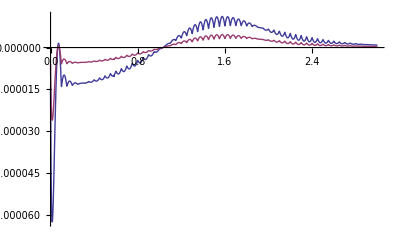

```mathematica
Plot[{Re[τ1exact[1,b]-τ1approx[1,b]],Im[τ1exact[1,b]-τ1approx[1,b]]},{b,0,3},PlotRange->All]
```

Interpolating the τ1 integral with the current grid spacing seems to keep the absolute error < 10^-4.

```mathematica
T1[k_,b_]:=Exp[I(χ0approx[k,b]+τ1approx[k,b])]-1
Eif1[k_,θ_]:=-I*k*NIntegrate[b*BesselJ[0,2*k*b*Sin[θ/2]]*T1[k,b],{b,0,15}]
```

```mathematica
eik1dσdΩ[En_,points_:10]:=Table[{N[θ/points],Abs[Eif1[Sqrt[En^2+2 m En]/ℏc,θ/points]]^2},{θ,0,points*Pi,1}]
```

```mathematica
σTEi1[En_]:=10*4*Pi/(Sqrt[En^2+2*m*En]/ℏc)*Im[Eif1[Sqrt[En^2+2*m*En]/ℏc,0]];
```

```mathematica
Parallelize[Table[{LogEn,Log[σTEi1[Exp[LogEn]]]},{LogEn,2,7,.5}]]
```

```mathematica
{{2.,6.445649508488908},{2.5,6.459806542504879},{3.,6.280875880474602},{3.5,5.9803923901313505},{4.,5.630973862065589},{4.5,5.260280419077529},{5.,4.876991358107812},{5.5,4.483471768391706},{6.,4.0792544660398296},{6.5,3.6621462549344974},{7.,3.229430721878601}}
```

{{2.,6.44565},{2.5,6.45981},{3.,6.28088},{3.5,5.98039},{4.,5.63097},{4.5,5.26028},{5.,4.87699},{5.5,4.48347},{6.,4.07925},{6.5,3.66215},{7.,3.22943}}

```mathematica
σTEi1loglogplot=Interpolation[%];
```

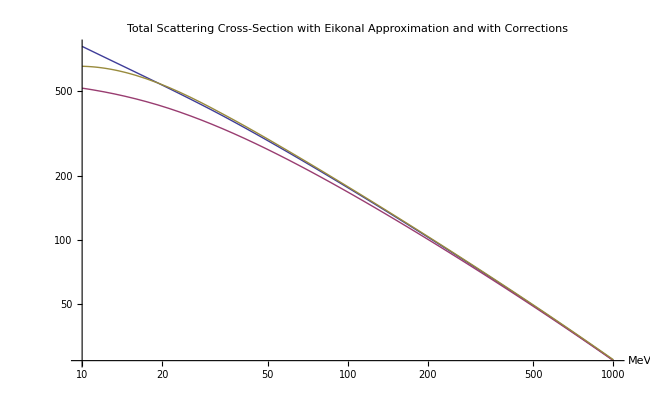

```mathematica
LogLogPlot[{Exp[σTloglogplot[Log[En]]],Exp[σTEi0loglogplot[Log[En]]],Exp[σTEi1loglogplot[Log[En]]]},{En,10,1000},PlotLabel->"Total Scattering Cross-Section
with Eikonal Approximation and with Corrections",PlotLegend->{"Exact Solution","Zeroth Order Eikonal","First Order Eikonal"},AxesLabel->{MeV},LegendPosition->{.85,-0.2},LegendSize->{.9,0.4},ImageSize->650]
```

The first order eikonal correction is accurate to ~20 MeV, while the zeroth is only accurate to ~100 MeV.

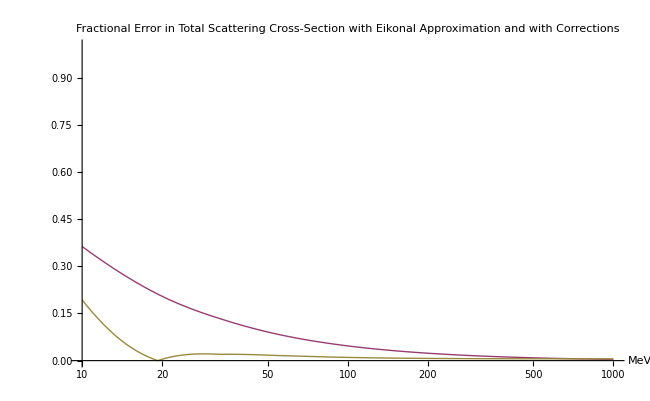

```mathematica
LogLinearPlot[{Abs[(Exp[σTEi0loglogplot[Log[En]]]-Exp[σTloglogplot[Log[En]]])/Exp[σTloglogplot[Log[En]]]],(Abs[Exp[σTEi1loglogplot[Log[En]]]-Exp[σTloglogplot[Log[En]]]])/Exp[σTloglogplot[Log[En]]]},{En,10,1000}, PlotRange->{0,1},PlotLabel->"Fractional Error in Total Scattering Cross-Section
with Eikonal Approximation and with Corrections",PlotLegend->{"Zeroth Order Eikonal","First Order Eikonal"},PlotStyle->{ColorData[1,2],ColorData[1,3]},AxesLabel->{MeV},LegendPosition->{.85,-0.2},LegendSize->{.9,0.4},ImageSize->650]
```

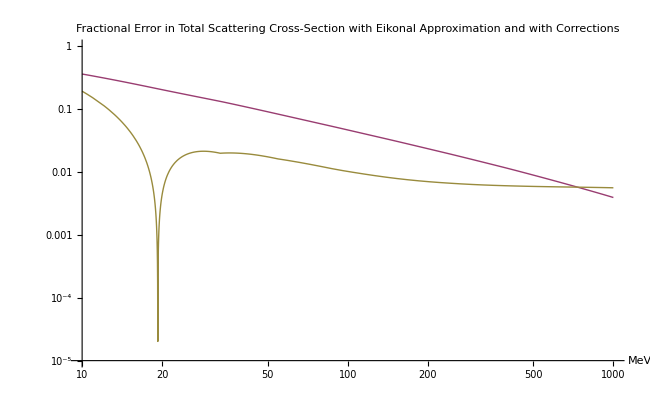

```mathematica
LogLogPlot[{Abs[(Exp[σTEi0loglogplot[Log[En]]]-Exp[σTloglogplot[Log[En]]])/Exp[σTloglogplot[Log[En]]]],(Abs[Exp[σTEi1loglogplot[Log[En]]]-Exp[σTloglogplot[Log[En]]]])/Exp[σTloglogplot[Log[En]]]},{En,10,1000}, PlotRange->{10^-5,1},PlotLabel->"Fractional Error in Total Scattering Cross-Section
with Eikonal Approximation and with Corrections",PlotLegend->{"Zeroth Order Eikonal","First Order Eikonal"},PlotStyle->{ColorData[1,2],ColorData[1,3]},AxesLabel->{MeV},LegendPosition->{.85,-0.2},LegendSize->{.9,0.4},ImageSize->650]
```

```mathematica
eik1dσdΩ[100]
```

```mathematica
{{0.,35.40751981766305},{0.1,31.96252551390052},{0.2,23.588793125834904},{0.3,14.351911348821776},{0.4,7.2683044880093375},{0.5,3.0855047021351134},{0.6,1.1028272348729027},{0.7,0.3386614969312848},{0.8,0.10155044722631852},{0.9,0.04303693985582597},{1.,0.029018628134726294},{1.1,0.021539728391742806},{1.2,0.014571261320785409},{1.3,0.008825548741320764},{1.4,0.004905225395567407},{1.5,0.0025969943338490843},{1.6,0.001377151431421123},{1.7,0.000776758137732344},{1.8,0.00048816791247179134},{1.9,0.0003430567841264972},{2.,0.0002607667049673147},{2.1,0.00020658869456888717},{2.2,0.0001667782565513716},{2.3,0.00013603573480228676},{2.4,0.00011206935716248097},{2.5,0.0000935495813075844},{2.6,0.00007946581033040762},{2.7,0.00006897567722302754},{2.8,0.00006138919320228569},{2.9,0.00005617154262313353},{3.,0.000052938654311120246},{3.1,0.000051446820116582245}}
```

{{0.,35.4075},{0.1,31.9625},{0.2,23.5888},{0.3,14.3519},{0.4,7.2683},{0.5,3.0855},{0.6,1.10283},{0.7,0.338661},{0.8,0.10155},{0.9,0.0430369},{1.,0.0290186},{1.1,0.0215397},{1.2,0.0145713},{1.3,0.00882555},{1.4,0.00490523},{1.5,0.00259699},{1.6,0.00137715},{1.7,0.000776758},{1.8,0.000488168},{1.9,0.000343057},{2.,0.000260767},{2.1,0.000206589},{2.2,0.000166778},{2.3,0.000136036},{2.4,0.000112069},{2.5,0.0000935496},{2.6,0.0000794658},{2.7,0.0000689757},{2.8,0.0000613892},{2.9,0.0000561715},{3.,0.0000529387},{3.1,0.0000514468}}

```mathematica
eik1interp1=Interpolation[%];
```

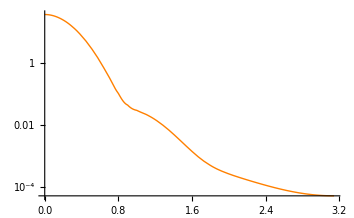

```mathematica
eik1p1=LogPlot[eik1interp1[θ],{θ,0,Pi},PlotStyle->Orange]
```

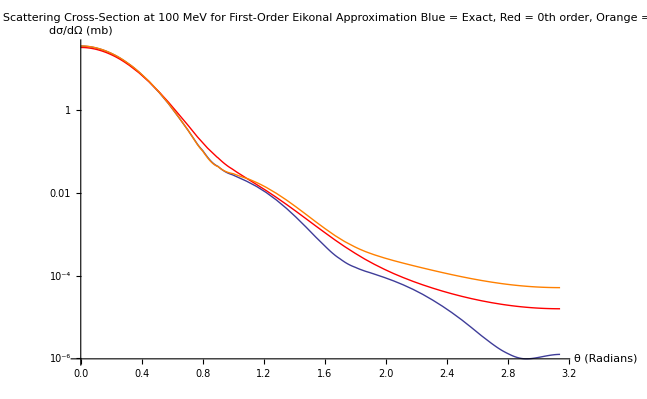

```mathematica
Show[p1,eik0p1,eik1p1,PlotLabel->"Differential Scattering Cross-Section at 100 MeV
for First-Order Eikonal Approximation
Blue = Exact, Red = 0th order, Orange = 1st order",AxesLabel->{"θ (Radians)","dσ/dΩ (mb)"},ImageSize->650]
```

### Second order correction

```mathematica
τ2exact[k_,b_]=-k*ϵ[k]^3*NIntegrate[Evaluate[(1#+5/3*b*D[#,b]+1/3*b^2*D[#,{b,2}])&[U[Sqrt[z^2+b^2]]^3]],{z,0,15}]-b*D[χ0exact[k,b],b]^3/(24*k^2);
ω2exact[k_,b_]=D[χ0exact[k,b],b]*D[b*D[χ0exact[k,b],b],b]/(8*k^2);
```

```mathematica
Parallelize[Table[{{k,b},τ2exact[k,b]},{b,0,15,.05},{k,Sqrt[100+2 m 10]/ℏc,Sqrt[1000^2+2 m 1000]/ℏc,.05}]]
```

```mathematica
τ2approx=Interpolation[Flatten[%[[2]],1]];
```

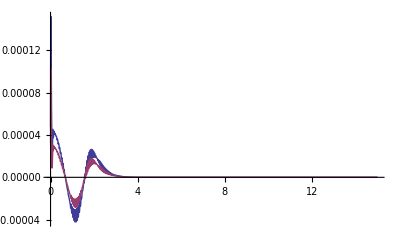

```mathematica
Plot[{Re[τ2exact[1,b]-τ2approx[1,b]],Im[τ2exact[1,b]-τ2approx[1,b]]},{b,0,15},PlotRange->All]
```

Here we can see that the grid spacing keeps the error in the interpolation on the order of 10^-4.

## Below this point is not working yet, but there are some good indications that the second order correction improves the total cross section even further.

```mathematica
Join[Table[{{k,b},ω2exact[k,b]},{b,0,5,.1},{k,Sqrt[100+2 m 10]/ℏc,Sqrt[1000^2+2 m 1000]/ℏc,.05}],Table[{{k,x},D[χ0[k,b],b]*D[b*D[χ0[k,b],b],b]/(8*k^2)},{x,5.1,15,.1},{k,Sqrt[100+2 m 10]/ℏc,Sqrt[1000^2+2 m 1000]/ℏc,.05}]]//Timing
```

```mathematica
ω2=Interpolation[Flatten[%[[2]],1]];
```

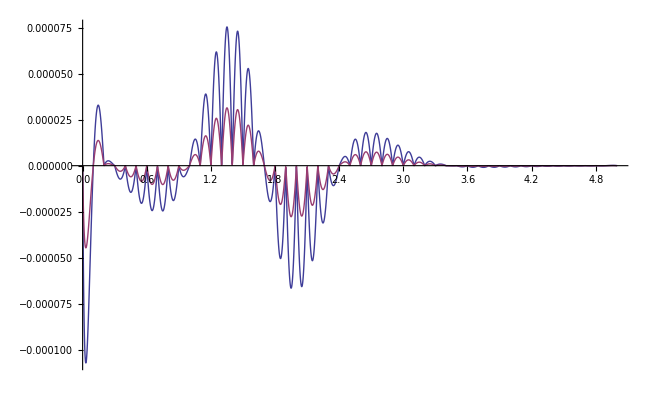

```mathematica
Plot[{Re[ω2temp[1,b]-ω2[b]],Im[ω2temp[1,b]-ω2[b]]},{b,0,5},PlotRange->All]
```

```mathematica
T2[k_,b_]:=Exp[I(χ0[k,b]+τ1[k,b]+τ2[k,b])]*Exp[-ω2[k,b]]-1
Eif2[k_,θ_]:=-I*k*NIntegrate[b*BesselJ[0,2*k*b*Sin[θ/2]]*T2[k,b],{b,0,15}]
```

```mathematica
eik2dσdΩ[En_,points_:10]:=Table[{N[θ/points],Abs[Eif2[Sqrt[En^2+2 m En]/ℏc,θ/points]]^2},{θ,0,points*Pi,1}]
```

```mathematica
σTEi2[En_]:=10*4*Pi/(Sqrt[En^2+2*m*En]/ℏc)*Im[Eif2[Sqrt[En^2+2*m*En]/ℏc,0]];
```

```mathematica
Table[{En,σTEi2[En]},{En,10,1000,10}]
```

```mathematica
Log[N[{{10,600.2299693958512},{20,529.6966341775147},{30,414.04306938775176},{40,341.7094158633824},{50,292.7790127845892},{60,257.2460176352075},{70,230.13024166719885},{80,208.6788209635934},{90,191.2370520949637},{100,176.7461286498036},{110,164.49453009814133},{120,153.9855141660501},{130,144.86097799466052},{140,136.85594122662488},{150,129.7698940367272},{160,123.4481647380376},{170,117.76942960555475},{180,112.63711645303181},{190,107.97335018097772},{200,103.71460122320309},{210,99.80850111615665},{220,96.21147190752993},{230,92.88694391922},{240,89.80399669554865},{250,86.93628715144195},{260,84.26122520344796},{270,81.75933924948721},{280,79.41373172694873},{290,77.20967304664063},{300,75.1342639648557},{310,73.17614618658047},{320,71.32529261021485},{330,69.57279928171951},{340,67.9107459512555},{350,66.33204958649023},{360,64.83036704789376},{370,63.399989151948226},{380,62.03577304283969},{390,60.73306340686579},{400,59.48764335428638},{410,58.29567786961519},{420,57.153673950841835},{430,56.05844286015389},{440,55.00706474759234},{450,53.99686497771165},{460,53.02538451860703},{470,52.090360402063915},{480,51.189706782125484},{490,50.32149587136487},{500,49.48394499839299},{510,48.67540232978742},{520,47.89433415538423},{530,47.13931581621367},{540,46.409021353591385},{550,45.702214565630655},{560,45.01774226372532},{570,44.35452717474676},{580,43.711561248584935},{590,43.08790031172875},{600,42.48265963165828},{610,41.89500849454211},{620,41.32416617632646},{630,40.769398666564356},{640,40.230014922982235},{650,39.705363615300676},{660,39.1948302059751},{670,38.69783486775492},{680,38.213829593189274},{690,37.74229608907737},{700,37.28274367645989},{710,36.834707814410045},{720,36.39774806246662},{730,35.97144655157327},{740,35.55540650894774},{750,35.149251059338},{760,34.75262196779417},{770,34.365178371848025},{780,33.98659578081678},{790,33.61656502191248},{800,33.254791559645994},{810,32.900994426964886},{820,32.554905485614135},{830,32.21626870269374},{840,31.884839410086997},{850,31.5603838540782},{860,31.242678412942823},{870,30.93150909405578},{880,30.626671018254022},{890,30.327967903703005},{900,30.03521169578402},{910,29.74822208801728},{920,29.466826103257024},{930,29.19085773603767},{940,28.92015760084325},{950,28.654572568654785},{960,28.39395556225874},{970,28.138165155779653},{980,27.88706533252387},{990,27.640525274842844},{1000,27.398417847997493}}]]
```

{{2.30259,6.39731},{2.99573,6.2723},{3.4012,6.02597},{3.68888,5.83396},{3.91202,5.67942},{4.09434,5.55003},{4.2485,5.43865},{4.38203,5.3408},{4.49981,5.25351},{4.60517,5.17471},{4.70048,5.10288},{4.78749,5.03686},{4.86753,4.97577},{4.94164,4.91893},{5.01064,4.86576},{5.07517,4.81582},{5.1358,4.76873},{5.19296,4.72417},{5.24702,4.68188},{5.29832,4.64164},{5.34711,4.60325},{5.39363,4.56655},{5.43808,4.53138},{5.48064,4.49763},{5.52146,4.46518},{5.56068,4.43392},{5.59842,4.40378},{5.63479,4.37467},{5.66988,4.34652},{5.70378,4.31928},{5.73657,4.29287},{5.76832,4.26725},{5.79909,4.24237},{5.82895,4.21819},{5.85793,4.19467},{5.8861,4.17177},{5.9135,4.14946},{5.94017,4.12771},{5.96615,4.10649},{5.99146,4.08577},{6.01616,4.06553},{6.04025,4.04574},{6.06379,4.02639},{6.08677,4.00746},{6.10925,3.98893},{6.13123,3.97077},{6.15273,3.95298},{6.17379,3.93554},{6.19441,3.91843},{6.21461,3.90165},{6.23441,3.88517},{6.25383,3.869},{6.27288,3.85311},{6.29157,3.83749},{6.30992,3.82215},{6.32794,3.80706},{6.34564,3.79221},{6.36303,3.77761},{6.38012,3.76324},{6.39693,3.7491},{6.41346,3.73517},{6.42972,3.72145},{6.44572,3.70793},{6.46147,3.69461},{6.47697,3.68149},{6.49224,3.66854},{6.50728,3.65578},{6.52209,3.6432},{6.53669,3.63078},{6.55108,3.61853},{6.56526,3.60644},{6.57925,3.59451},{6.59304,3.58273},{6.60665,3.57109},{6.62007,3.5596},{6.63332,3.54826},{6.64639,3.53704},{6.65929,3.52597},{6.67203,3.51502},{6.68461,3.5042},{6.69703,3.4935},{6.7093,3.48293},{6.72143,3.47247},{6.7334,3.46213},{6.74524,3.4519},{6.75693,3.44179},{6.76849,3.43178},{6.77992,3.42187},{6.79122,3.41207},{6.80239,3.40237},{6.81344,3.39277},{6.82437,3.38327},{6.83518,3.37386},{6.84588,3.36454},{6.85646,3.35531},{6.86693,3.34618},{6.8773,3.33713},{6.88755,3.32816},{6.8977,3.31928},{6.90776,3.31049}}

```mathematica
σTEi2loglogplot=Interpolation[%];
```

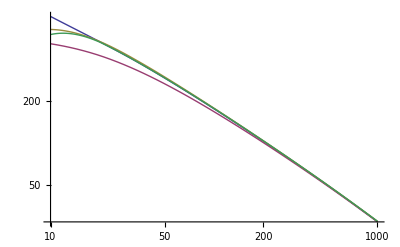

```mathematica
LogLogPlot[{Exp[σTloglogplot[Log[En]]],Exp[σTEi0loglogplot[Log[En]]],Exp[σTEi1loglogplot[Log[En]]],Exp[σTEi2loglogplot[Log[En]]]},{En,10,1000}]
```

```mathematica
eik2dσdΩ[100]
```

{{0.,35.3318},{0.1,31.8768},{0.2,23.4855},{0.3,14.2457},{0.4,7.18224},{0.5,3.03198},{0.6,1.07873},{0.7,0.332499},{0.8,0.102327},{0.9,0.0443653},{1.,0.0288075},{1.1,0.0200045},{1.2,0.0125536},{1.3,0.0069789},{1.4,0.00351921},{1.5,0.00169632},{1.6,0.00086322},{1.7,0.000524976},{1.8,0.000393585},{1.9,0.000332422},{2.,0.000289011},{2.1,0.000248781},{2.2,0.000210602},{2.3,0.000176313},{2.4,0.000147283},{2.5,0.000123852},{2.6,0.000105639},{2.7,0.0000919361},{2.8,0.0000819902},{2.9,0.0000751466},{3.,0.0000709094},{3.1,0.0000689557}}

```mathematica
eik2interp1=Interpolation[%];
```

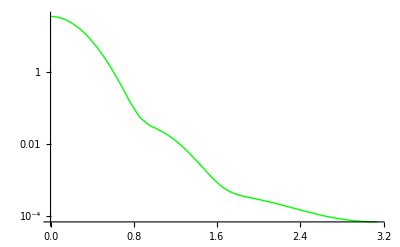

```mathematica
eik2p1=LogPlot[eik2interp1[θ],{θ,0,Pi},PlotStyle->Green]
```

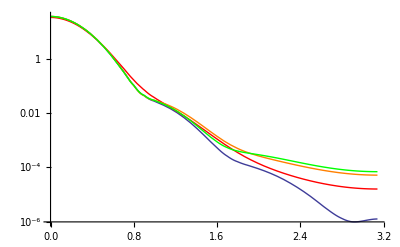

```mathematica
Show[p1,eik0p1,eik1p1,eik2p1,PlotRange->Automatic]
```

### Third order correction

```mathematica
τ3[k_,b_]=-k*ϵ[k]^4*NIntegrate[Evaluate[(5/4#+11/4*b*D[#,b]+b^2*D[#,{b,2}]+1/12*b^3*D[#,{b,3}])&[U[Sqrt[z^2+b^2]]^4]],{z,0,15}]-b*D[τ1[k,b],b]*D[χ0[k,b],b]^2/(8*k^2);
ϕ3[k_,b_]=-k*ϵ[k]^2*NIntegrate[Evaluate[(1#+5/3*b*D[#,b]+1/3*b^2*D[#,{b,2}])&[(1/(2*k)*D[U[Sqrt[z^2+b^2]],b])^2]],{z,0,15}];
ω3[k_,b_]=(D[χ0[k,b],b]*D[b*D[τ1[k,b],b],b]+D[τ1[k,b],b]*D[b*D[χ0[k,b],b],b])/(8*k^2);
```

```mathematica
T3[k_,b_]:=Exp[I*(χ0[k,b]+τ1[k,b]+τ2[k,b]+τ3[k,b]+ϕ3[k,b])]*Exp[-(ω2[k,b]+ω3[k,b])]-1
```

```mathematica
Eif3[k_,θ_]:=-I*k*NIntegrate[b*BesselJ[0,2*k*b*Sin[θ/2]]*T3[k,b],{b,0,15}]
```

```mathematica
eik3dσdΩ[En_,points_:10]:=Table[{N[θ/points],Abs[Eif3[Sqrt[En^2+2 m En]/ℏc,θ/points]]^2},{θ,0,points*Pi,1}]
```

```mathematica
σTEi3[En_]:=40 Pi/(Sqrt[En^2+2 m En]/ℏc) Im[Eif3[Sqrt[En^2+2 m En]/ℏc,0]]
```

```mathematica
Table[{En,σTEi3[En]},{En,10,1000,10}]
```

$Aborted

```mathematica
Plot[Re[τ3[Sqrt[10000+2 m 100]/ℏc,b]],{b,0,15}]
```

$Aborted

```mathematica
σTEi3[10]
```

NIntegrate::inumr: The integrand -41.5  + 8.3\ ⅈ/1 + ⅇ^1.85185\ (-1.67444 + √Plus[« 2 »])
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 15}}.

NIntegrate::inumr: The integrand 1.  + 5.55112×10^-17\ ⅈ/(1 + ⅇ^1.85185\ (-« 19 » + « 1 »))^2 - (3.7037  + 2.05597×10^-16\ ⅈ)\ b^2\ ⅇ^1.85185\ (-« 19 » + « 1 »)/(1 + ⅇ^1.85185\ « 1 »)^3\ √b^2 + z^2
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 15}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

803.563

```mathematica
σTEi3plot=Interpolation[%];
```

```mathematica
LogLogPlot[{(σTEiplot[En]-σTplot[En])/σTplot[En],(σTEi1Plot[En]-σTplot[En])/σTplot[En],(σTEi2Plot[En]-σTplot[En])/σTplot[En],(σTEi3plot[En]-σTplot[En])/σTplot[En]},{En,10,1000}]
```

```mathematica
eik3dσdΩ[100]
```

```mathematica
{{0,91.44454627711006},{0.1,86.93401462142639},{0.2,74.63539942644337},{0.30000000000000004,57.73580994872822},{0.4,40.1191611488699},{0.5,25.01154909387827},{0.6000000000000001,14.137423616688872},{0.7000000000000001,7.628404129429616},{0.8,4.517113985599908},{0.9,3.4373177523439993},{1.,3.191026845603401},{1.1,3.025041125904266},{1.2000000000000002,2.6393069732410597},{1.3,2.04368047822072},{1.4000000000000001,1.3836954073218313},{1.5,0.8100455864643781},{1.6,0.41410762975043075},{1.7000000000000002,0.21737791131140125},{1.8,0.19041266794593914},{1.9000000000000001,0.27971259914912966},{2.,0.4297942445530772},{2.1,0.5960371098986682},{2.2,0.7491310507723384},{2.3000000000000003,0.8740401298795031},{2.4000000000000004,0.966433394680398},{2.5,1.028668140282196},{2.6,1.066427761430172},{2.7,1.0863750659977414},{2.8000000000000003,1.0947558839109996},{2.9000000000000004,1.0967122891307253},{3.,1.096041229838605},{3.1,1.0951810613831496}}
```

{{0,91.4445},{0.1,86.934},{0.2,74.6354},{0.3,57.7358},{0.4,40.1192},{0.5,25.0115},{0.6,14.1374},{0.7,7.6284},{0.8,4.51711},{0.9,3.43732},{1.,3.19103},{1.1,3.02504},{1.2,2.63931},{1.3,2.04368},{1.4,1.3837},{1.5,0.810046},{1.6,0.414108},{1.7,0.217378},{1.8,0.190413},{1.9,0.279713},{2.,0.429794},{2.1,0.596037},{2.2,0.749131},{2.3,0.87404},{2.4,0.966433},{2.5,1.02867},{2.6,1.06643},{2.7,1.08638},{2.8,1.09476},{2.9,1.09671},{3.,1.09604},{3.1,1.09518}}

```mathematica
eik3interp1=Interpolation[%];
```

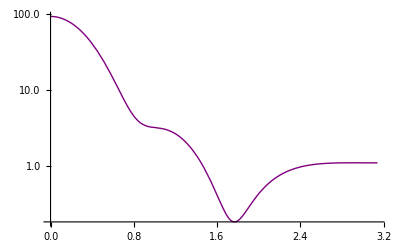

```mathematica
eik3p1=LogPlot[eik3interp1[θ],{θ,0,Pi},PlotStyle->Purple]
```

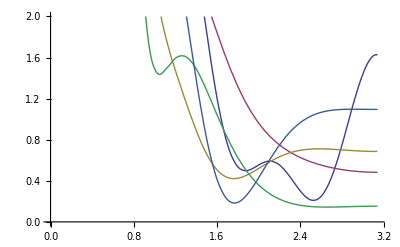

```mathematica
Plot[{interp1[θ],eik0interp1[θ],eik1interp1[θ],eik2interp1[θ],eik3interp1[θ]},{θ,0,π},PlotRange->{0,2}]
```

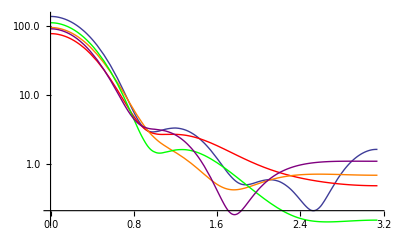

```mathematica
Show[p1,eik0p1,eik1p1,eik2p1,eik3p1,PlotRange->Automatic]
```

### Eikonal to third order for k = 1, 2, 3

```mathematica
eik1dσdΩ[2]
```

```mathematica
{{0,293.22916757681776},{0.1,253.73708442891774},{0.2,163.54525083771438},{0.30000000000000004,77.12185874818907},{0.4,25.827549639078388},{0.5,6.470193765582039},{0.6000000000000001,2.404829314396261},{0.7000000000000001,1.9708446558230917},{0.8,1.4418483020129758},{0.9,0.7725091233405128},{1.,0.3469346095016307},{1.1,0.17920260076861255},{1.2000000000000002,0.12740509798030303},{1.3,0.09836042734065897},{1.4000000000000001,0.06913635577519377},{1.5,0.044201145819914786},{1.6,0.027723797564798387},{1.7000000000000002,0.01858997815221487},{1.8,0.01371874720343962},{1.9000000000000001,0.010736034325405947},{2.,0.00851044754298138},{2.1,0.0066970413471289306},{2.2,0.005241989043030437},{2.3000000000000003,0.004130130923060545},{2.4000000000000004,0.003317940686099176},{2.5,0.0027421904266382103},{2.6,0.0023402945942820387},{2.7,0.0020618251899269546},{2.8000000000000003,0.0018709300822241403},{2.9000000000000004,0.0017441597963126962},{3.,0.0016671795249573332},{3.1,0.0016319996781983062}}
```

{{0,293.229},{0.1,253.737},{0.2,163.545},{0.3,77.1219},{0.4,25.8275},{0.5,6.47019},{0.6,2.40483},{0.7,1.97084},{0.8,1.44185},{0.9,0.772509},{1.,0.346935},{1.1,0.179203},{1.2,0.127405},{1.3,0.0983604},{1.4,0.0691364},{1.5,0.0442011},{1.6,0.0277238},{1.7,0.01859},{1.8,0.0137187},{1.9,0.010736},{2.,0.00851045},{2.1,0.00669704},{2.2,0.00524199},{2.3,0.00413013},{2.4,0.00331794},{2.5,0.00274219},{2.6,0.00234029},{2.7,0.00206183},{2.8,0.00187093},{2.9,0.00174416},{3.,0.00166718},{3.1,0.001632}}

```mathematica
eik1interp2=Interpolation[%];
```

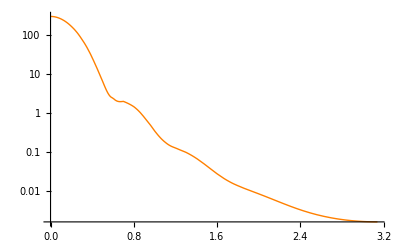

```mathematica
eik1p2=LogPlot[eik1interp2[θ],{θ,0,Pi},PlotStyle->Orange]
```

```mathematica
eik2dσdΩ[2]
```

```mathematica
{{0,294.8910610420141},{0.1,254.64906314911445},{0.2,163.0438766536933},{0.30000000000000004,75.93509962321531},{0.4,24.995469770821455},{0.5,6.304885592324231},{0.6000000000000001,2.5700573876368416},{0.7000000000000001,2.0945827457899067},{0.8,1.4219824225411097},{0.9,0.684685732267747},{1.,0.2732260646789869},{1.1,0.14396253329387548},{1.2000000000000002,0.1179262007797158},{1.3,0.09744344816721406},{1.4000000000000001,0.0684080785672247},{1.5,0.04267666743910603},{1.6,0.026908537622400235},{1.7000000000000002,0.019553362451643495},{1.8,0.01646813408118401},{1.9000000000000001,0.014645895152346293},{2.,0.012856322382081679},{2.1,0.01094820113938691},{2.2,0.009122353927508044},{2.3000000000000003,0.007560083105323252},{2.4000000000000004,0.006329439588063352},{2.5,0.005411916311465128},{2.6,0.004750752991457766},{2.7,0.004284532348888232},{2.8000000000000003,0.003962528625692157},{2.9000000000000004,0.0037483595712716152},{3.,0.0036184361539684435},{3.1,0.0035591384191706516}}
```

{{0,294.891},{0.1,254.649},{0.2,163.044},{0.3,75.9351},{0.4,24.9955},{0.5,6.30489},{0.6,2.57006},{0.7,2.09458},{0.8,1.42198},{0.9,0.684686},{1.,0.273226},{1.1,0.143963},{1.2,0.117926},{1.3,0.0974434},{1.4,0.0684081},{1.5,0.0426767},{1.6,0.0269085},{1.7,0.0195534},{1.8,0.0164681},{1.9,0.0146459},{2.,0.0128563},{2.1,0.0109482},{2.2,0.00912235},{2.3,0.00756008},{2.4,0.00632944},{2.5,0.00541192},{2.6,0.00475075},{2.7,0.00428453},{2.8,0.00396253},{2.9,0.00374836},{3.,0.00361844},{3.1,0.00355914}}

```mathematica
eik2interp2=Interpolation[%];
```

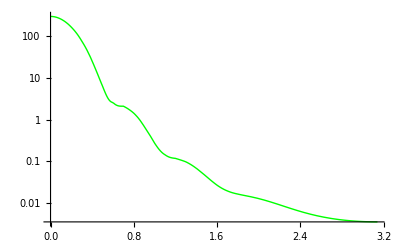

```mathematica
eik2p2=LogPlot[eik2interp2[θ],{θ,0,Pi},PlotStyle->Green]
```

```mathematica
eik3dσdΩ[2]
```

```mathematica
{{0,294.86691456514865},{0.1,254.72568209257432},{0.2,163.3026128276939},{0.30000000000000004,76.26132870351331},{0.4,25.23290700858881},{0.5,6.396043386339652},{0.6000000000000001,2.5518405487150866},{0.7000000000000001,2.031782755927383},{0.8,1.3639402190579146},{0.9,0.6519501171856685},{1.,0.26136665900409967},{1.1,0.13815228081376424},{1.2000000000000002,0.10790737102051179},{1.3,0.08268003362366579},{1.4000000000000001,0.053761303230222456},{1.5,0.032256482613916955},{1.6,0.021524363471284717},{1.7000000000000002,0.017681889654967888},{1.8,0.01617669761158569},{1.9000000000000001,0.014717166618473682},{2.,0.012906519213103873},{2.1,0.011067812566862553},{2.2,0.009514511180635484},{2.3000000000000003,0.008353938975641188},{2.4000000000000004,0.007544120654285952},{2.5,0.0069908764873193785},{2.6,0.006607264957444925},{2.7,0.006333323810317747},{2.8000000000000003,0.00613449966297479},{2.9000000000000004,0.005993551971246569},{3.,0.005903002447388051},{3.1,0.005860089596276548}}
```

{{0,294.867},{0.1,254.726},{0.2,163.303},{0.3,76.2613},{0.4,25.2329},{0.5,6.39604},{0.6,2.55184},{0.7,2.03178},{0.8,1.36394},{0.9,0.65195},{1.,0.261367},{1.1,0.138152},{1.2,0.107907},{1.3,0.08268},{1.4,0.0537613},{1.5,0.0322565},{1.6,0.0215244},{1.7,0.0176819},{1.8,0.0161767},{1.9,0.0147172},{2.,0.0129065},{2.1,0.0110678},{2.2,0.00951451},{2.3,0.00835394},{2.4,0.00754412},{2.5,0.00699088},{2.6,0.00660726},{2.7,0.00633332},{2.8,0.0061345},{2.9,0.00599355},{3.,0.005903},{3.1,0.00586009}}

```mathematica
eik3interp2=Interpolation[%];
```

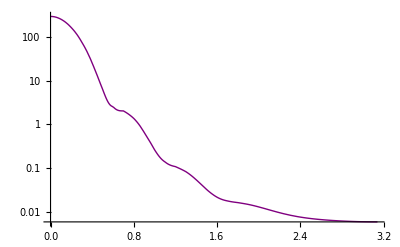

```mathematica
eik3p2=LogPlot[eik3interp2[θ],{θ,0,Pi},PlotStyle->Purple]
```

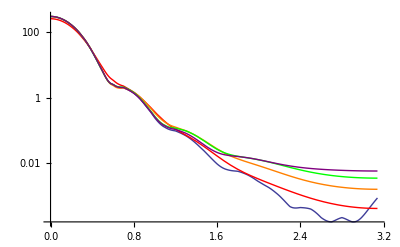

```mathematica
Show[p2,eik0p2,eik1p2,eik2p2,eik3p2,PlotRange->Automatic]
```

```mathematica
eik1dσdΩ[3,100]
```

```mathematica
{{0.,374.13781381048307},{0.01,372.9924352365846},{0.02,369.5764944900654},{0.03,363.94999741306157},{0.04,356.2110466279768},{0.05,346.4930607284497},{0.06,334.96103659736303},{0.07,321.80700061346386},{0.08,307.24482302297866},{0.09,291.50458960011684},{0.1,274.82673516963416},{0.11,257.45614445108004},{0.12,239.6364173953523},{0.13,221.6044796065673},{0.14,203.58569487788586},{0.15,185.78960792767757},{0.16,168.4064128968459},{0.17,151.6042089149153},{0.18,135.52706986015446},{0.19,120.29392296554035},{0.2,105.99820155234163},{0.21,92.70821199963676},{0.22,80.46813484073157},{0.23,69.29956503526144},{0.24,59.203487093034816},{0.25,50.162576626469686},{0.26,42.143720642228345},{0.27,35.10065382731625},{0.28,28.97661648296383},{0.29,23.706950795770805},{0.3,19.221564971846327},{0.31,15.44720859514822},{0.32,12.309516672785195},{0.33,9.734793561826066},{0.34,7.651520812372226},{0.35,5.991584510657416},{0.36,4.691227686393697},{0.37,3.691741597780101},{0.38,2.9399161685463358},{0.39,2.3882745513509676},{0.4,1.9951198370331393},{0.41,1.7244234705083015},{0.42,1.5455851685966986},{0.43,1.433093274959512},{0.44,1.3661127556954116},{0.45,1.32802565436674},{0.46,1.3059459930934698},{0.47,1.2902280132581372},{0.48,1.273983457849327},{0.49,1.252620443791906},{0.5,1.2234134659928246},{0.51,1.185111298096398},{0.52,1.1375870661985075},{0.53,1.0815326068528885},{0.54,1.0181973960965458},{0.55,0.9491708522420836},{0.56,0.8762056590503844},{0.57,0.8010789053633993},{0.58,0.7254872622200904},{0.59,0.6509720856036946},{0.6,0.5788702055676518},{0.61,0.5102862042913494},{0.62,0.4460821611474568},{0.63,0.38688111898197636},{0.64,0.3330808724171769},{0.65,0.2848750695543306},{0.66,0.2422790302746418},{0.67,0.20515809859611783},{0.68,0.17325674821330506},{0.69,0.14622703795249603},{0.7,0.12365535918915212},{0.71,0.1050867249365385},{0.72,0.09004611743494878},{0.73,0.07805663681438461},{0.74,0.0686543785924728},{0.75,0.06140011450413567},{0.76,0.05588796247212293},{0.77,0.05175131107633176},{0.78,0.048666315682653546},{0.79,0.04635331160570944},{0.8,0.04457649842034246},{0.81,0.04314224273393081},{0.82,0.04189632804472823},{0.83,0.04072045301591003},{0.84,0.03952824650641681},{0.85,0.03826103147644478},{0.86,0.03688353249704382},{0.87,0.03537968469075286},{0.88,0.03374866679545727},{0.89,0.03200124861326495},{0.9,0.030156514017714797},{0.91,0.02823899531988171},{0.92,0.02627623329659005},{0.93,0.02429675954015907},{0.94,0.022328483845796464},{0.95,0.020397458845633525},{0.96,0.018526986697175844},{0.97,0.01673702798124516},{0.98,0.015043870611082113},{0.99,0.013460016200984457},{1.,0.011994242487147167},{1.01,0.010651802773902999},{1.02,0.00943472661169807},{1.03,0.008342189727633243},{1.04,0.007370925371520464},{1.05,0.006515653497712485},{1.06,0.005769508405782452},{1.07,0.005124449482044743},{1.08,0.00457164336777611},{1.09,0.004101809367571587},{1.1,0.0037055226730064073},{1.11,0.003373472725044936},{1.12,0.0030966760385517885},{1.13,0.0028666445673546873},{1.14,0.0026755120128801524},{1.15,0.002516121459262672},{1.16,0.002382078384975052},{1.17,0.0022677734956340406},{1.18,0.0021683799947550425},{1.19,0.002079829866296656},{1.2,0.0019987736029421924},{1.21,0.0019225274935317342},{1.22,0.0018490122354803114},{1.23,0.001776686210261392},{1.24,0.0017044763124666972},{1.25,0.0016317087664055126},{1.26,0.001558041917243974},{1.27,0.0014834025581129092},{1.28,0.0014079269608863294},{1.29,0.0013319074229608627},{1.3,0.00125574482826694},{1.31,0.001179907451888439},{1.32,0.0011048960114723064},{1.33,0.0010312147860155215},{1.34,0.0009593484793300845},{1.35,0.0008897443994958891},{1.36,0.0008227994520112325},{1.37,0.0007588514000881523},{1.38,0.000698173825452878},{1.39,0.0006409742235693248},{1.4,0.0005873946843521528},{1.41,0.0005375146390759511},{1.42,0.0004913551936413724},{1.43,0.00044888461389927303},{1.44,0.00041002457839715964},{1.45,0.0003746568650888102},{1.46,0.00034263018950239687},{1.47,0.00031376696134726546},{1.48,0.0002878697731002793},{1.49,0.00026472747711808704},{1.5,0.0002441207468333636},{1.51,0.00022582705188706483},{1.52,0.0002096250070472521},{1.53,0.000195298079948174},{1.54,0.00018263766361696762},{1.55,0.00017144553654395317},{1.56,0.00016153574591318997},{1.57,0.00015273595916029061},{1.58,0.00014488833543288378},{1.59,0.00013784997233661647},{1.6,0.00013149298492851834},{1.61,0.00012570427358040584},{1.62,0.00012038503565684614},{1.63,0.00011545007291079895},{1.64,0.00011082694280896875},{1.65,0.00010645499758575926},{1.66,0.00010228435013598425},{1.67,0.00009827480093362979},{1.68,0.00009439475531884178},{1.69,0.00009062015572720753},{1.7,0.00008693344890793408},{1.71,0.00008332260397502475},{1.72,0.00007978019327799979},{1.73,0.00007630254461065219},{1.74,0.00007288897024033877},{1.75,0.00006954107557468509},{1.76,0.00006626214805464615},{1.77,0.00006305662501261661},{1.78,0.000059929637719374393},{1.79,0.00005688662769544341},{1.8,0.00005393303045770977},{1.81,0.000051074021319344144},{1.82,0.00004831431742963491},{1.83,0.000045658030105031},{1.84,0.00004310856145087499},{1.85,0.00004066853943945167},{1.86,0.0000383397857852157},{1.87,0.000036123311322701796},{1.88,0.00003401933391993781},{1.89,0.00003202731439733517},{1.9,0.000030146006355326973},{1.91,0.00002837351624143235},{1.92,0.00002670737046360616},{1.93,0.000025144586748307942},{1.94,0.000023681747391665144},{1.95,0.000022315072412021223},{1.96,0.00002104049099582404},{1.97,0.000019853709934064645},{1.98,0.00001875027805781317},{1.99,0.000017725645947207206},{2.,0.000016775220400778822},{2.01,0.000015894413372095567},{2.02,0.000015078685237040635},{2.03,0.00001432358239754933},{2.04,0.000013624769351765768},{2.05,0.00001297805544160433},{2.06,0.000012379416561835767},{2.07,0.000011825012178987175},{2.08,0.000011311198024851166},{2.09,0.000010834534865629102},{2.1,0.000010391793754054061},{2.11,9.97995816971786*^-6},{2.12,9.596223445493942*^-6},{2.13,9.237993866898316*^-6},{2.14,8.90287780530345*^-6},{2.15,8.588681230546763*^-6},{2.16,8.29339991607754*^-6},{2.17,8.015210626896435*^-6},{2.18,7.752461550641712*^-6},{2.19,7.5036622054027776*^-6},{2.2,7.267473029204065*^-6},{2.21,7.042694830470899*^-6},{2.22,6.828258253615334*^-6},{2.23,6.623213389064334*^-6},{2.24,6.4267196366751305*^-6},{2.25,6.238035909844821*^-6},{2.26,6.056511250204012*^-6},{2.27,5.881575905616361*^-6},{2.28,5.712732910649383*^-6},{2.29,5.549550193974073*^-6},{2.3,5.39165322846207*^-6},{2.31,5.238718227336146*^-6},{2.32,5.090465884442379*^-6},{2.33,4.946655647745902*^-6},{2.34,4.807080510816015*^-6},{2.35,4.671562303049519*^-6},{2.36,4.539947453943757*^-6},{2.37,4.412103207813111*^-6},{2.38,4.287914258411379*^-6},{2.39,4.167279779937592*^-6},{2.4,4.050110819655479*^-6},{2.41,3.936328028088194*^-6},{2.42,3.825859695057879*^-6},{2.43,3.718640066516616*^-6},{2.44,3.614607912793669*^-6},{2.45,3.5137053252808508*^-6},{2.46,3.415876715514762*^-6},{2.47,3.321067993814342*^-6},{2.48,3.2292259094319747*^-6},{2.49,3.1402975268404718*^-6},{2.5,3.0542298271693475*^-6},{2.51,2.9709694106459518*^-6},{2.52,2.890462291572651*^-6},{2.53,2.8126537682869318*^-6},{2.54,2.7374883563500615*^-6},{2.55,2.6649097755180056*^-6},{2.56,2.5948609796527875*^-6},{2.57,2.5272842198543525*^-6},{2.58,2.462121136138791*^-6},{2.59,2.3993128682008456*^-6},{2.6,2.3388001810505997*^-6},{2.61,2.2805236011963723*^-6},{2.62,2.2244235570395035*^-6},{2.63,2.170440522547907*^-6},{2.64,2.118515159701264*^-6},{2.65,2.0685884578360143*^-6},{2.66,2.0206018678021595*^-6},{2.67,1.9744974301280723*^-6},{2.68,1.930217856709785*^-6},{2.69,1.8877068371601331*^-6},{2.7,1.8469087515858066*^-6},{2.71,1.8077691545276731*^-6},{2.72,1.7702346644665048*^-6},{2.73,1.7342530773965652*^-6},{2.74,1.699773432362758*^-6},{2.75,1.666746067765194*^-6},{2.76,1.635122670054504*^-6},{2.77,1.60485631327189*^-6},{2.78,1.575901490941244*^-6},{2.79,1.5482141404176185*^-6},{2.8,1.5217516625246547*^-6},{2.81,1.4964729315250052*^-6},{2.82,1.4723383026893022*^-6},{2.83,1.4493096127107432*^-6},{2.84,1.4273501764771552*^-6},{2.85,1.4064247793830025*^-6},{2.86,1.386499665568198*^-6},{2.87,1.367542524564904*^-6},{2.88,1.3495224731824753*^-6},{2.89,1.3324100364395575*^-6},{2.9,1.3161771262264318*^-6},{2.91,1.3007970184872924*^-6},{2.92,1.2862443290194142*^-6},{2.93,1.2724949886628773*^-6},{2.94,1.2595262176135573*^-6},{2.95,1.2473164995767737*^-6},{2.96,1.2358455563326112*^-6},{2.97,1.225094321209125*^-6},{2.98,1.2150449139941128*^-6},{2.99,1.2056806162311343*^-6},{3.,1.1969858467505951*^-6},{3.01,1.1889461383649954*^-6},{3.02,1.1815481156191036*^-6},{3.03,1.174779473563935*^-6},{3.04,1.168628957229333*^-6},{3.05,1.1630863437324002*^-6},{3.06,1.1581424237223199*^-6},{3.07,1.153788986216142*^-6},{3.08,1.1500188042603705*^-6},{3.09,1.1468256211165255*^-6},{3.1,1.1442041399013494*^-6},{3.11,1.1421500134885433*^-6},{3.12,1.1406598362979838*^-6},{3.13,1.1397311385476292*^-6},{3.14,1.1393623810656883*^-6}}
```

{{0.,374.138},{0.01,372.992},{0.02,369.576},{0.03,363.95},{0.04,356.211},{0.05,346.493},{0.06,334.961},{0.07,321.807},{0.08,307.245},{0.09,291.505},{0.1,274.827},{0.11,257.456},{0.12,239.636},{0.13,221.604},{0.14,203.586},{0.15,185.79},{0.16,168.406},{0.17,151.604},{0.18,135.527},{0.19,120.294},{0.2,105.998},{0.21,92.7082},{0.22,80.4681},{0.23,69.2996},{0.24,59.2035},{0.25,50.1626},{0.26,42.1437},{0.27,35.1007},{0.28,28.9766},{0.29,23.707},{0.3,19.2216},{0.31,15.4472},{0.32,12.3095},{0.33,9.73479},{0.34,7.65152},{0.35,5.99158},{0.36,4.69123},{0.37,3.69174},{0.38,2.93992},{0.39,2.38827},{0.4,1.99512},{0.41,1.72442},{0.42,1.54559},{0.43,1.43309},{0.44,1.36611},{0.45,1.32803},{0.46,1.30595},{0.47,1.29023},{0.48,1.27398},{0.49,1.25262},{0.5,1.22341},{0.51,1.18511},{0.52,1.13759},{0.53,1.08153},{0.54,1.0182},{0.55,0.949171},{0.56,0.876206},{0.57,0.801079},{0.58,0.725487},{0.59,0.650972},{0.6,0.57887},{0.61,0.510286},{0.62,0.446082},{0.63,0.386881},{0.64,0.333081},{0.65,0.284875},{0.66,0.242279},{0.67,0.205158},{0.68,0.173257},{0.69,0.146227},{0.7,0.123655},{0.71,0.105087},{0.72,0.0900461},{0.73,0.0780566},{0.74,0.0686544},{0.75,0.0614001},{0.76,0.055888},{0.77,0.0517513},{0.78,0.0486663},{0.79,0.0463533},{0.8,0.0445765},{0.81,0.0431422},{0.82,0.0418963},{0.83,0.0407205},{0.84,0.0395282},{0.85,0.038261},{0.86,0.0368835},{0.87,0.0353797},{0.88,0.0337487},{0.89,0.0320012},{0.9,0.0301565},{0.91,0.028239},{0.92,0.0262762},{0.93,0.0242968},{0.94,0.0223285},{0.95,0.0203975},{0.96,0.018527},{0.97,0.016737},{0.98,0.0150439},{0.99,0.01346},{1.,0.0119942},{1.01,0.0106518},{1.02,0.00943473},{1.03,0.00834219},{1.04,0.00737093},{1.05,0.00651565},{1.06,0.00576951},{1.07,0.00512445},{1.08,0.00457164},{1.09,0.00410181},{1.1,0.00370552},{1.11,0.00337347},{1.12,0.00309668},{1.13,0.00286664},{1.14,0.00267551},{1.15,0.00251612},{1.16,0.00238208},{1.17,0.00226777},{1.18,0.00216838},{1.19,0.00207983},{1.2,0.00199877},{1.21,0.00192253},{1.22,0.00184901},{1.23,0.00177669},{1.24,0.00170448},{1.25,0.00163171},{1.26,0.00155804},{1.27,0.0014834},{1.28,0.00140793},{1.29,0.00133191},{1.3,0.00125574},{1.31,0.00117991},{1.32,0.0011049},{1.33,0.00103121},{1.34,0.000959348},{1.35,0.000889744},{1.36,0.000822799},{1.37,0.000758851},{1.38,0.000698174},{1.39,0.000640974},{1.4,0.000587395},{1.41,0.000537515},{1.42,0.000491355},{1.43,0.000448885},{1.44,0.000410025},{1.45,0.000374657},{1.46,0.00034263},{1.47,0.000313767},{1.48,0.00028787},{1.49,0.000264727},{1.5,0.000244121},{1.51,0.000225827},{1.52,0.000209625},{1.53,0.000195298},{1.54,0.000182638},{1.55,0.000171446},{1.56,0.000161536},{1.57,0.000152736},{1.58,0.000144888},{1.59,0.00013785},{1.6,0.000131493},{1.61,0.000125704},{1.62,0.000120385},{1.63,0.00011545},{1.64,0.000110827},{1.65,0.000106455},{1.66,0.000102284},{1.67,0.0000982748},{1.68,0.0000943948},{1.69,0.0000906202},{1.7,0.0000869334},{1.71,0.0000833226},{1.72,0.0000797802},{1.73,0.0000763025},{1.74,0.000072889},{1.75,0.0000695411},{1.76,0.0000662621},{1.77,0.0000630566},{1.78,0.0000599296},{1.79,0.0000568866},{1.8,0.000053933},{1.81,0.000051074},{1.82,0.0000483143},{1.83,0.000045658},{1.84,0.0000431086},{1.85,0.0000406685},{1.86,0.0000383398},{1.87,0.0000361233},{1.88,0.0000340193},{1.89,0.0000320273},{1.9,0.000030146},{1.91,0.0000283735},{1.92,0.0000267074},{1.93,0.0000251446},{1.94,0.0000236817},{1.95,0.0000223151},{1.96,0.0000210405},{1.97,0.0000198537},{1.98,0.0000187503},{1.99,0.0000177256},{2.,0.0000167752},{2.01,0.0000158944},{2.02,0.0000150787},{2.03,0.0000143236},{2.04,0.0000136248},{2.05,0.0000129781},{2.06,0.0000123794},{2.07,0.000011825},{2.08,0.0000113112},{2.09,0.0000108345},{2.1,0.0000103918},{2.11,9.97996×10^-6},{2.12,9.59622×10^-6},{2.13,9.23799×10^-6},{2.14,8.90288×10^-6},{2.15,8.58868×10^-6},{2.16,8.2934×10^-6},{2.17,8.01521×10^-6},{2.18,7.75246×10^-6},{2.19,7.50366×10^-6},{2.2,7.26747×10^-6},{2.21,7.04269×10^-6},{2.22,6.82826×10^-6},{2.23,6.62321×10^-6},{2.24,6.42672×10^-6},{2.25,6.23804×10^-6},{2.26,6.05651×10^-6},{2.27,5.88158×10^-6},{2.28,5.71273×10^-6},{2.29,5.54955×10^-6},{2.3,5.39165×10^-6},{2.31,5.23872×10^-6},{2.32,5.09047×10^-6},{2.33,4.94666×10^-6},{2.34,4.80708×10^-6},{2.35,4.67156×10^-6},{2.36,4.53995×10^-6},{2.37,4.4121×10^-6},{2.38,4.28791×10^-6},{2.39,4.16728×10^-6},{2.4,4.05011×10^-6},{2.41,3.93633×10^-6},{2.42,3.82586×10^-6},{2.43,3.71864×10^-6},{2.44,3.61461×10^-6},{2.45,3.51371×10^-6},{2.46,3.41588×10^-6},{2.47,3.32107×10^-6},{2.48,3.22923×10^-6},{2.49,3.1403×10^-6},{2.5,3.05423×10^-6},{2.51,2.97097×10^-6},{2.52,2.89046×10^-6},{2.53,2.81265×10^-6},{2.54,2.73749×10^-6},{2.55,2.66491×10^-6},{2.56,2.59486×10^-6},{2.57,2.52728×10^-6},{2.58,2.46212×10^-6},{2.59,2.39931×10^-6},{2.6,2.3388×10^-6},{2.61,2.28052×10^-6},{2.62,2.22442×10^-6},{2.63,2.17044×10^-6},{2.64,2.11852×10^-6},{2.65,2.06859×10^-6},{2.66,2.0206×10^-6},{2.67,1.9745×10^-6},{2.68,1.93022×10^-6},{2.69,1.88771×10^-6},{2.7,1.84691×10^-6},{2.71,1.80777×10^-6},{2.72,1.77023×10^-6},{2.73,1.73425×10^-6},{2.74,1.69977×10^-6},{2.75,1.66675×10^-6},{2.76,1.63512×10^-6},{2.77,1.60486×10^-6},{2.78,1.5759×10^-6},{2.79,1.54821×10^-6},{2.8,1.52175×10^-6},{2.81,1.49647×10^-6},{2.82,1.47234×10^-6},{2.83,1.44931×10^-6},{2.84,1.42735×10^-6},{2.85,1.40642×10^-6},{2.86,1.3865×10^-6},{2.87,1.36754×10^-6},{2.88,1.34952×10^-6},{2.89,1.33241×10^-6},{2.9,1.31618×10^-6},{2.91,1.3008×10^-6},{2.92,1.28624×10^-6},{2.93,1.27249×10^-6},{2.94,1.25953×10^-6},{2.95,1.24732×10^-6},{2.96,1.23585×10^-6},{2.97,1.22509×10^-6},{2.98,1.21504×10^-6},{2.99,1.20568×10^-6},{3.,1.19699×10^-6},{3.01,1.18895×10^-6},{3.02,1.18155×10^-6},{3.03,1.17478×10^-6},{3.04,1.16863×10^-6},{3.05,1.16309×10^-6},{3.06,1.15814×10^-6},{3.07,1.15379×10^-6},{3.08,1.15002×10^-6},{3.09,1.14683×10^-6},{3.1,1.1442×10^-6},{3.11,1.14215×10^-6},{3.12,1.14066×10^-6},{3.13,1.13973×10^-6},{3.14,1.13936×10^-6}}

```mathematica
eik1interp3=Interpolation[%];
```

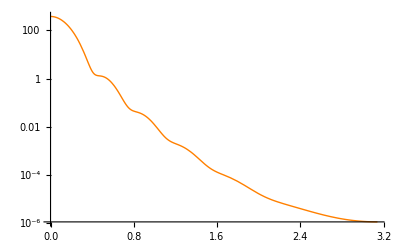

```mathematica
eik1p3=LogPlot[eik1interp3[θ],{θ,0,Pi},PlotStyle->Orange]
```

```mathematica
eik2dσdΩ[3,100]
```

{{0.,373.822},{0.01,372.674},{0.02,369.25},{0.03,363.61},{0.04,355.853},{0.05,346.113},{0.06,334.557},{0.07,321.376},{0.08,306.786},{0.09,291.018},{0.1,274.315},{0.11,256.92},{0.12,239.08},{0.13,221.032},{0.14,203.002},{0.15,185.2},{0.16,167.817},{0.17,151.02},{0.18,134.955},{0.19,119.74},{0.2,105.467},{0.21,92.2049},{0.22,79.9969},{0.23,68.8639},{0.24,58.806},{0.25,49.8051},{0.26,41.8272},{0.27,34.8252},{0.28,28.7416},{0.29,23.5109},{0.3,19.0624},{0.31,15.3223},{0.32,12.2158},{0.33,9.66895},{0.34,7.60994},{0.35,5.97056},{0.36,4.68707},{0.37,3.70083},{0.38,2.95883},{0.39,2.41382},{0.4,2.02441},{0.41,1.7549},{0.42,1.57507},{0.43,1.45978},{0.44,1.38857},{0.45,1.34521},{0.46,1.31714},{0.47,1.29505},{0.48,1.27234},{0.49,1.24466},{0.5,1.2095},{0.51,1.16577},{0.52,1.11348},{0.53,1.05339},{0.54,0.986814},{0.55,0.915356},{0.56,0.840759},{0.57,0.764762},{0.58,0.689007},{0.59,0.614966},{0.6,0.543894},{0.61,0.476808},{0.62,0.41448},{0.63,0.357442},{0.64,0.306006},{0.65,0.260284},{0.66,0.220219},{0.67,0.18561},{0.68,0.156146},{0.69,0.131434},{0.7,0.111024},{0.71,0.0944338},{0.72,0.0811716},{0.73,0.0707508},{0.74,0.062705},{0.75,0.0565989},{0.76,0.0520357},{0.77,0.0486619},{0.78,0.0461698},{0.79,0.0442981},{0.8,0.0428305},{0.81,0.0415934},{0.82,0.0404524},{0.83,0.0393082},{0.84,0.0380922},{0.85,0.036762},{0.86,0.0352969},{0.87,0.0336932},{0.88,0.0319608},{0.89,0.030119},{0.9,0.0281936},{0.91,0.026214},{0.92,0.0242109},{0.93,0.0222148},{0.94,0.0202541},{0.95,0.0183544},{0.96,0.0165376},{0.97,0.0148215},{0.98,0.0132201},{0.99,0.0117429},{1.,0.0103956},{1.01,0.00918054},{1.02,0.00809666},{1.03,0.00714029},{1.04,0.00630553},{1.05,0.00558473},{1.06,0.00496895},{1.07,0.00444841},{1.08,0.00401285},{1.09,0.0036519},{1.1,0.00335534},{1.11,0.00311336},{1.12,0.00291675},{1.13,0.002757},{1.14,0.00262646},{1.15,0.00251834},{1.16,0.00242674},{1.17,0.00234667},{1.18,0.00227398},{1.19,0.00220536},{1.2,0.00213821},{1.21,0.00207063},{1.22,0.0020013},{1.23,0.00192941},{1.24,0.00185457},{1.25,0.00177677},{1.26,0.00169624},{1.27,0.00161345},{1.28,0.00152899},{1.29,0.00144358},{1.3,0.00135794},{1.31,0.00127284},{1.32,0.00118901},{1.33,0.00110713},{1.34,0.00102781},{1.35,0.000951586},{1.36,0.000878911},{1.37,0.000810139},{1.38,0.000745534},{1.39,0.000685274},{1.4,0.00062945},{1.41,0.000578079},{1.42,0.000531109},{1.43,0.000488428},{1.44,0.000449873},{1.45,0.000415243},{1.46,0.000384303},{1.47,0.000356793},{1.48,0.000332439},{1.49,0.000310961},{1.5,0.000292072},{1.51,0.000275494},{1.52,0.000260954},{1.53,0.000248191},{1.54,0.00023696},{1.55,0.000227034},{1.56,0.000218204},{1.57,0.00021028},{1.58,0.000203095},{1.59,0.000196499},{1.6,0.000190363},{1.61,0.000184578},{1.62,0.00017905},{1.63,0.000173705},{1.64,0.000168482},{1.65,0.000163333},{1.66,0.000158225},{1.67,0.000153134},{1.68,0.000148044},{1.69,0.000142949},{1.7,0.000137848},{1.71,0.000132746},{1.72,0.000127652},{1.73,0.000122578},{1.74,0.000117538},{1.75,0.000112547},{1.76,0.000107621},{1.77,0.000102775},{1.78,0.0000980263},{1.79,0.0000933883},{1.8,0.0000888745},{1.81,0.000084497},{1.82,0.0000802663},{1.83,0.000076191},{1.84,0.0000722783},{1.85,0.0000685337},{1.86,0.0000649607},{1.87,0.0000615617},{1.88,0.0000583371},{1.89,0.0000552864},{1.9,0.0000524075},{1.91,0.0000496973},{1.92,0.0000471517},{1.93,0.0000447658},{1.94,0.0000425339},{1.95,0.0000404499},{1.96,0.0000385069},{1.97,0.000036698},{1.98,0.0000350159},{1.99,0.0000334533},{2.,0.0000320027},{2.01,0.0000306566},{2.02,0.0000294079},{2.03,0.0000282495},{2.04,0.0000271743},{2.05,0.0000261758},{2.06,0.0000252476},{2.07,0.0000243837},{2.08,0.0000235784},{2.09,0.0000228264},{2.1,0.0000221226},{2.11,0.0000214624},{2.12,0.0000208416},{2.13,0.0000202562},{2.14,0.0000197025},{2.15,0.0000191774},{2.16,0.0000186778},{2.17,0.0000182011},{2.18,0.0000177449},{2.19,0.000017307},{2.2,0.0000168856},{2.21,0.000016479},{2.22,0.0000160857},{2.23,0.0000157045},{2.24,0.0000153343},{2.25,0.0000149741},{2.26,0.0000146231},{2.27,0.0000142808},{2.28,0.0000139464},{2.29,0.0000136195},{2.3,0.0000132998},{2.31,0.0000129869},{2.32,0.0000126806},{2.33,0.0000123807},{2.34,0.000012087},{2.35,0.0000117995},{2.36,0.000011518},{2.37,0.0000112425},{2.38,0.000010973},{2.39,0.0000107094},{2.4,0.0000104517},{2.41,0.0000102},{2.42,9.9541×10^-6},{2.43,9.71413×10^-6},{2.44,9.48006×10^-6},{2.45,9.25188×10^-6},{2.46,9.02958×10^-6},{2.47,8.81313×10^-6},{2.48,8.60252×10^-6},{2.49,8.39771×10^-6},{2.5,8.19866×10^-6},{2.51,8.00534×10^-6},{2.52,7.81768×10^-6},{2.53,7.63564×10^-6},{2.54,7.45914×10^-6},{2.55,7.28812×10^-6},{2.56,7.1225×10^-6},{2.57,6.96219×10^-6},{2.58,6.80711×10^-6},{2.59,6.65716×10^-6},{2.6,6.51226×10^-6},{2.61,6.37229×10^-6},{2.62,6.23715×10^-6},{2.63,6.10675×10^-6},{2.64,5.98097×10^-6},{2.65,5.85971×10^-6},{2.66,5.74284×10^-6},{2.67,5.63027×10^-6},{2.68,5.52189×10^-6},{2.69,5.41757×10^-6},{2.7,5.31722×10^-6},{2.71,5.22072×10^-6},{2.72,5.12797×10^-6},{2.73,5.03885×10^-6},{2.74,4.95327×10^-6},{2.75,4.87111×10^-6},{2.76,4.79228×10^-6},{2.77,4.71668×10^-6},{2.78,4.64421×10^-6},{2.79,4.57479×10^-6},{2.8,4.5083×10^-6},{2.81,4.44468×10^-6},{2.82,4.38382×10^-6},{2.83,4.32566×10^-6},{2.84,4.2701×10^-6},{2.85,4.21707×10^-6},{2.86,4.16649×10^-6},{2.87,4.1183×10^-6},{2.88,4.07243×10^-6},{2.89,4.0288×10^-6},{2.9,3.98736×10^-6},{2.91,3.94804×10^-6},{2.92,3.91079×10^-6},{2.93,3.87556×10^-6},{2.94,3.84228×10^-6},{2.95,3.81092×10^-6},{2.96,3.78143×10^-6},{2.97,3.75376×10^-6},{2.98,3.72787×10^-6},{2.99,3.70372×10^-6},{3.,3.68128×10^-6},{3.01,3.66052×10^-6},{3.02,3.64139×10^-6},{3.03,3.62389×10^-6},{3.04,3.60797×10^-6},{3.05,3.59362×10^-6},{3.06,3.58081×10^-6},{3.07,3.56953×10^-6},{3.08,3.55975×10^-6},{3.09,3.55147×10^-6},{3.1,3.54466×10^-6},{3.11,3.53933×10^-6},{3.12,3.53547×10^-6},{3.13,3.53305×10^-6},{3.14,3.5321×10^-6}}

```mathematica
eik2interp3=Interpolation[%];
```

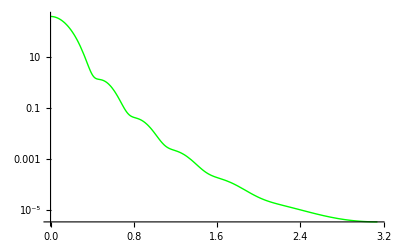

```mathematica
eik2p3=LogPlot[eik2interp3[θ],{θ,0,Pi},PlotStyle->Green]
```

```mathematica
eik3dσdΩ[3,100]
```

{{0.,373.882},{0.01,372.735},{0.02,369.312},{0.03,363.674},{0.04,355.921},{0.05,346.185},{0.06,334.632},{0.07,321.456},{0.08,306.871},{0.09,291.108},{0.1,274.408},{0.11,257.017},{0.12,239.18},{0.13,221.134},{0.14,203.105},{0.15,185.304},{0.16,167.919},{0.17,151.121},{0.18,135.053},{0.19,119.833},{0.2,105.556},{0.21,92.2879},{0.22,80.0736},{0.23,68.9337},{0.24,58.8686},{0.25,49.8603},{0.26,41.8749},{0.27,34.8655},{0.28,28.7747},{0.29,23.5372},{0.3,19.0824},{0.31,15.3365},{0.32,12.2248},{0.33,9.6733},{0.34,7.61029},{0.35,5.96753},{0.36,4.68126},{0.37,3.69283},{0.38,2.94915},{0.39,2.40294},{0.4,2.01275},{0.41,1.74283},{0.42,1.56289},{0.43,1.44773},{0.44,1.37685},{0.45,1.33395},{0.46,1.30644},{0.47,1.28496},{0.48,1.26289},{0.49,1.23585},{0.5,1.2013},{0.51,1.15816},{0.52,1.1064},{0.53,1.0468},{0.54,0.98066},{0.55,0.909591},{0.56,0.835335},{0.57,0.75964},{0.58,0.684151},{0.59,0.610346},{0.6,0.539485},{0.61,0.472591},{0.62,0.410439},{0.63,0.353565},{0.64,0.302284},{0.65,0.25671},{0.66,0.216785},{0.67,0.18231},{0.68,0.152974},{0.69,0.128381},{0.7,0.108083},{0.71,0.0915958},{0.72,0.078427},{0.73,0.0680893},{0.74,0.0601163},{0.75,0.0540727},{0.76,0.049562},{0.77,0.0462313},{0.78,0.0437742},{0.79,0.0419304},{0.8,0.0404853},{0.81,0.0392669},{0.82,0.0381424},{0.83,0.0370144},{0.84,0.035816},{0.85,0.0345062},{0.86,0.0330658},{0.87,0.0314922},{0.88,0.0297962},{0.89,0.0279978},{0.9,0.026123},{0.91,0.0242013},{0.92,0.0222633},{0.93,0.020339},{0.94,0.0184561},{0.95,0.0166393},{0.96,0.0149096},{0.97,0.0132837},{0.98,0.0117744},{0.99,0.0103901},{1.,0.00913545},{1.01,0.00801148},{1.02,0.00701622},{1.03,0.0061451},{1.04,0.00539141},{1.05,0.00474686},{1.06,0.00420201},{1.07,0.00374671},{1.08,0.0033705},{1.09,0.00306293},{1.1,0.00281383},{1.11,0.00261357},{1.12,0.00245319},{1.13,0.00232455},{1.14,0.00222041},{1.15,0.00213444},{1.16,0.00206126},{1.17,0.00199639},{1.18,0.00193622},{1.19,0.00187793},{1.2,0.00181942},{1.21,0.00175923},{1.22,0.00169647},{1.23,0.00163069},{1.24,0.00156184},{1.25,0.00149014},{1.26,0.00141608},{1.27,0.00134025},{1.28,0.0012634},{1.29,0.00118628},{1.3,0.00110967},{1.31,0.00103431},{1.32,0.000960901},{1.33,0.000890047},{1.34,0.000822281},{1.35,0.000758034},{1.36,0.000697641},{1.37,0.000641336},{1.38,0.000589264},{1.39,0.00054148},{1.4,0.000497961},{1.41,0.000458616},{1.42,0.000423296},{1.43,0.000391801},{1.44,0.000363898},{1.45,0.000339322},{1.46,0.000317791},{1.47,0.000299012},{1.48,0.000282692},{1.49,0.000268539},{1.5,0.000256272},{1.51,0.000245621},{1.52,0.000236336},{1.53,0.000228186},{1.54,0.00022096},{1.55,0.00021447},{1.56,0.000208552},{1.57,0.000203063},{1.58,0.000197881},{1.59,0.000192905},{1.6,0.000188055},{1.61,0.000183266},{1.62,0.000178491},{1.63,0.000173694},{1.64,0.000168855},{1.65,0.000163963},{1.66,0.000159015},{1.67,0.000154015},{1.68,0.000148975},{1.69,0.000143908},{1.7,0.000138832},{1.71,0.000133767},{1.72,0.000128734},{1.73,0.000123753},{1.74,0.000118844},{1.75,0.000114026},{1.76,0.000109317},{1.77,0.000104734},{1.78,0.000100289},{1.79,0.0000959952},{1.8,0.0000918617},{1.81,0.0000878961},{1.82,0.0000841038},{1.83,0.0000804882},{1.84,0.0000770507},{1.85,0.0000737911},{1.86,0.0000707075},{1.87,0.0000677969},{1.88,0.0000650548},{1.89,0.0000624759},{1.9,0.0000600539},{1.91,0.000057782},{1.92,0.0000556527},{1.93,0.0000536585},{1.94,0.0000517912},{1.95,0.0000500429},{1.96,0.0000484056},{1.97,0.0000468713},{1.98,0.0000454322},{1.99,0.000044081},{2.,0.0000428103},{2.01,0.0000416134},{2.02,0.0000404838},{2.03,0.0000394155},{2.04,0.0000384028},{2.05,0.0000374405},{2.06,0.0000365238},{2.07,0.0000356482},{2.08,0.0000348099},{2.09,0.0000340051},{2.1,0.0000332308},{2.11,0.0000324839},{2.12,0.0000317619},{2.13,0.0000310626},{2.14,0.000030384},{2.15,0.0000297244},{2.16,0.0000290822},{2.17,0.0000284563},{2.18,0.0000278456},{2.19,0.0000272491},{2.2,0.0000266661},{2.21,0.000026096},{2.22,0.0000255382},{2.23,0.0000249923},{2.24,0.0000244579},{2.25,0.0000239349},{2.26,0.000023423},{2.27,0.0000229221},{2.28,0.0000224319},{2.29,0.0000219525},{2.3,0.0000214836},{2.31,0.0000210254},{2.32,0.0000205776},{2.33,0.0000201403},{2.34,0.0000197135},{2.35,0.000019297},{2.36,0.0000188908},{2.37,0.0000184948},{2.38,0.000018109},{2.39,0.0000177334},{2.4,0.0000173677},{2.41,0.0000170119},{2.42,0.000016666},{2.43,0.0000163297},{2.44,0.0000160031},{2.45,0.0000156858},{2.46,0.0000153778},{2.47,0.0000150789},{2.48,0.0000147891},{2.49,0.000014508},{2.5,0.0000142355},{2.51,0.0000139716},{2.52,0.0000137159},{2.53,0.0000134683},{2.54,0.0000132286},{2.55,0.0000129966},{2.56,0.0000127722},{2.57,0.0000125551},{2.58,0.0000123452},{2.59,0.0000121423},{2.6,0.0000119462},{2.61,0.0000117566},{2.62,0.0000115736},{2.63,0.0000113967},{2.64,0.000011226},{2.65,0.0000110612},{2.66,0.0000109021},{2.67,0.0000107485},{2.68,0.0000106004},{2.69,0.0000104576},{2.7,0.0000103198},{2.71,0.0000101871},{2.72,0.0000100591},{2.73,9.93583×10^-6},{2.74,9.81711×10^-6},{2.75,9.7028×10^-6},{2.76,9.59278×10^-6},{2.77,9.48693×10^-6},{2.78,9.38514×10^-6},{2.79,9.2873×10^-6},{2.8,9.19329×10^-6},{2.81,9.10302×10^-6},{2.82,9.01638×10^-6},{2.83,8.93329×10^-6},{2.84,8.85365×10^-6},{2.85,8.77737×10^-6},{2.86,8.70438×10^-6},{2.87,8.63459×10^-6},{2.88,8.56793×10^-6},{2.89,8.50432×10^-6},{2.9,8.44371×10^-6},{2.91,8.38602×10^-6},{2.92,8.33119×10^-6},{2.93,8.27917×10^-6},{2.94,8.22989×10^-6},{2.95,8.18332×10^-6},{2.96,8.1394×10^-6},{2.97,8.09808×10^-6},{2.98,8.05933×10^-6},{2.99,8.02309×10^-6},{3.,7.98935×10^-6},{3.01,7.95805×10^-6},{3.02,7.92917×10^-6},{3.03,7.90268×10^-6},{3.04,7.87855×10^-6},{3.05,7.85676×10^-6},{3.06,7.83728×10^-6},{3.07,7.8201×10^-6},{3.08,7.8052×10^-6},{3.09,7.79256×10^-6},{3.1,7.78217×10^-6},{3.11,7.77403×10^-6},{3.12,7.76811×10^-6},{3.13,7.76442×10^-6},{3.14,7.76296×10^-6}}

```mathematica
eik3interp3=Interpolation[%];
```

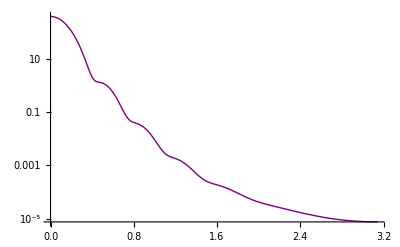

```mathematica
eik3p3=LogPlot[eik3interp3[θ],{θ,0,Pi},PlotStyle->Purple]
```

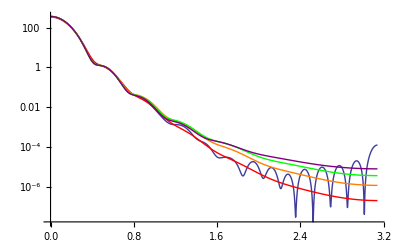

```mathematica
Show[p3,eik0p3,eik1p3,eik2p3,eik3p3,PlotRange->Automatic]
```

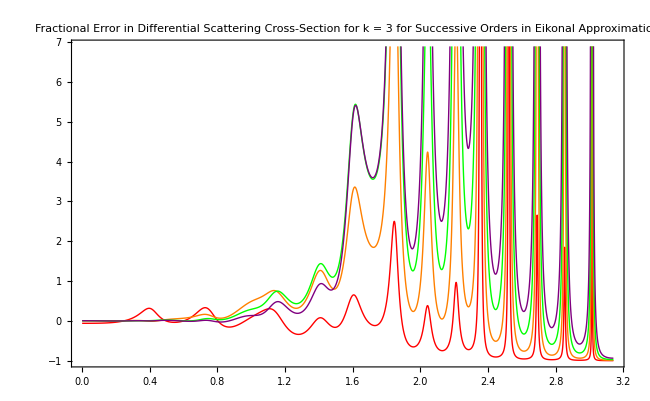

```mathematica
Plot[{(eik0interp3[θ]-temp[θ])/temp[θ],(eik1interp3[θ]-temp[θ])/temp[θ],(eik2interp3[θ]-temp[θ])/temp[θ],(eik3interp3[θ]-temp[θ])/temp[θ]},{θ,0,Pi},PlotLabel->"Fractional Error in Differential Scattering Cross-Section
for k = 3 for Successive Orders in Eikonal Approximation",PlotStyle->{Red,Orange,Green,Purple},PlotLegend->{"Zeroth Order Eikonal","First Order Eikonal","Second Order Eikonal","Third Order Eikonal"},AxesLabel->{θ},LegendPosition->{.85,-0.2},LegendSize->{.9,0.4},ImageSize->650,Frame->True]
```

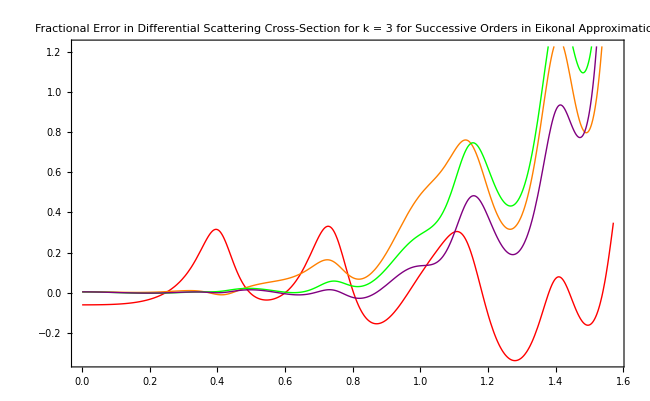

```mathematica
Plot[{(eik0interp3[θ]-temp[θ])/temp[θ],(eik1interp3[θ]-temp[θ])/temp[θ],(eik2interp3[θ]-temp[θ])/temp[θ],(eik3interp3[θ]-temp[θ])/temp[θ]},{θ,0,Pi/2},PlotLabel->"Fractional Error in Differential Scattering Cross-Section
for k = 3 for Successive Orders in Eikonal Approximation",AxesLabel->{θ},PlotStyle->{Red,Orange,Green,Purple},PlotLegend->{"Zeroth Order Eikonal","First Order Eikonal","Second Order Eikonal","Third Order Eikonal"},LegendPosition->{.85,-0.2},LegendSize->{.9,0.4},ImageSize->650,Frame->True]
```

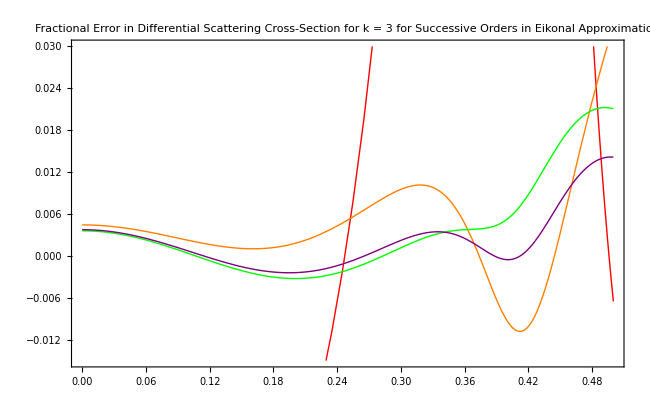

```mathematica
Plot[{(eik0interp3[θ]-temp[θ])/temp[θ],(eik1interp3[θ]-temp[θ])/temp[θ],(eik2interp3[θ]-temp[θ])/temp[θ],(eik3interp3[θ]-temp[θ])/temp[θ]},{θ,0,.5},PlotRange->{-.015,.03},PlotLabel->"Fractional Error in Differential Scattering Cross-Section
for k = 3 for Successive Orders in Eikonal Approximation",AxesLabel->{θ},PlotStyle->{Red,Orange,Green,Purple},PlotLegend->{"Zeroth Order Eikonal","First Order Eikonal","Second Order Eikonal","Third Order Eikonal"},LegendPosition->{.85,-0.2},LegendSize->{.9,0.4},ImageSize->650,Frame->True]
```

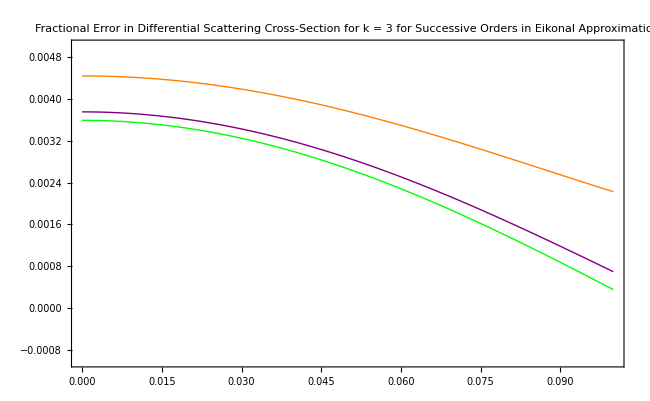

```mathematica
Plot[{(eik0interp3[θ]-temp[θ])/temp[θ],(eik1interp3[θ]-temp[θ])/temp[θ],(eik2interp3[θ]-temp[θ])/temp[θ],(eik3interp3[θ]-temp[θ])/temp[θ]},{θ,0,.1},PlotRange->{-0.001,0.005},PlotLabel->"Fractional Error in Differential Scattering Cross-Section
for k = 3 for Successive Orders in Eikonal Approximation",AxesLabel->{θ},PlotStyle->{Red,Orange,Green,Purple},PlotLegend->{"Zeroth Order Eikonal","First Order Eikonal","Second Order Eikonal","Third Order Eikonal"},LegendPosition->{.85,-0.2},LegendSize->{.9,0.4},ImageSize->650,Frame->True]
```

As can be seen from the above four graphs, the fractional error in general becomes smaller as we go to higher orders in the eikonal series. Furthermore, the range of validity in θ increases with increasing order. The only exception to these results can be seen upon close inspection of the forward scattering direction. In the forward direction, the approximation to second order actually has a smaller fractional error than the approximation to third order.

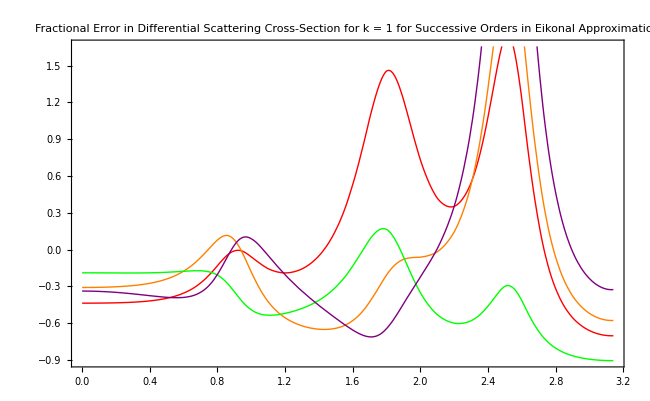

```mathematica
Plot[{(eik0interp1[θ]-interp1[θ])/interp1[θ],(eik1interp1[θ]-interp1[θ])/interp1[θ],(eik2interp1[θ]-interp1[θ])/interp1[θ],(eik3interp1[θ]-interp1[θ])/interp1[θ]},{θ,0,Pi},PlotLabel->"Fractional Error in Differential Scattering Cross-Section
for k = 1 for Successive Orders in Eikonal Approximation",PlotStyle->{Red,Orange,Green,Purple},PlotLegend->{"Zeroth Order Eikonal","First Order Eikonal","Second Order Eikonal","Third Order Eikonal"},AxesLabel->{θ},LegendPosition->{.85,-0.2},LegendSize->{.9,0.4},ImageSize->650,Frame->True]
```